```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
CCompilers[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

```mathematica
Get["MergerTransport/Merger2DProtonShifted.m"]
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(binTable[[i,1,1]]+binTable[[i,1,2]])/2,(binTable[[i,2,1]]+binTable[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
FileSorter[Directory_]:=Module[
{filenames=FileNames["TransferResult*",Directory],splitted,orderedlist},
splitted=StringSplit[filenames,"-"];
orderedlist=Ordering[ToExpression[StringTake[splitted[[All,-1]],{1,-5}]]];
filenames[[orderedlist]]
]
```

```mathematica
bin2DGen2[xStart_,xEnd_,yStart_,yEnd_,binNoX_,binNoY_]:=Block[{binLengthX,binLengthY,binList,binsX,binsY},binLengthX=Round[(xEnd-xStart)/binNoX,1/10^6.];binLengthY=Round[(yEnd-yStart)/binNoY,1/10^6.];binsX=Table[{xStart+(i-1) binLengthX,xStart+i binLengthX},{i,binNoX}];binsY=Table[{yStart+(i-1) binLengthY,yStart+i binLengthY},{i,binNoY}];binList=Flatten[Table[{binsX⟦i⟧,binsY⟦j⟧},{i,Length[binsX]},{j,Length[binsY]}],1];Return[binList];]
```

```mathematica
binLengthY=Round[(yEnd-yStart)/11,1/10^6.]
binsX=Table[{xStart+(i-1) binLengthX,xStart+i binLengthX},{i,binNoX}];binsY=Table[{yStart+(i-1) binLengthY,yStart+i binLengthY},{i,binNoY}];
```

Round[(yEnd-yStart)/11,1.×10^-6]

Table::iterb: Iterator {i,binNoX} does not have appropriate bounds.

Table::iterb: Iterator {i,binNoY} does not have appropriate bounds.

```mathematica
yStart+0.006364
```

0.006364+yStart

```mathematica
xyBins[[1,1]]
```

Part::partd: Part specification xyBins⟦1,1⟧ is longer than depth of object.

xyBins⟦1,1⟧

```mathematica
xyBins[[1,2]]
```

Part::partd: Part specification xyBins⟦1,2⟧ is longer than depth of object.

xyBins⟦1,2⟧

```mathematica
xyBins[[1,1]]
```

Part::partd: Part specification xyBins⟦1,1⟧ is longer than depth of object.

xyBins⟦1,1⟧

```mathematica
xyBins[[2,1]]
```

Part::partd: Part specification xyBins⟦2,1⟧ is longer than depth of object.

xyBins⟦2,1⟧

```mathematica
xybins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11][[1;;8]]
```

{{{xStart,xStart+Round[(xEnd-xStart)/24,1.×10^-20]},{yStart,yStart+Round[(yEnd-yStart)/11,1.×10^-20]}},{{xStart,xStart+Round[(xEnd-xStart)/24,1.×10^-20]},{yStart+Round[(yEnd-yStart)/11,1.×10^-20],yStart+2 Round[(yEnd-yStart)/11,1.×10^-20]}},{{xStart,xStart+Round[(xEnd-xStart)/24,1.×10^-20]},{yStart+2 Round[(yEnd-yStart)/11,1.×10^-20],yStart+3 Round[(yEnd-yStart)/11,1.×10^-20]}},{{xStart,xStart+Round[(xEnd-xStart)/24,1.×10^-20]},{yStart+3 Round[(yEnd-yStart)/11,1.×10^-20],yStart+4 Round[(yEnd-yStart)/11,1.×10^-20]}},{{xStart,xStart+Round[(xEnd-xStart)/24,1.×10^-20]},{yStart+4 Round[(yEnd-yStart)/11,1.×10^-20],yStart+5 Round[(yEnd-yStart)/11,1.×10^-20]}},{{xStart,xStart+Round[(xEnd-xStart)/24,1.×10^-20]},{yStart+5 Round[(yEnd-yStart)/11,1.×10^-20],yStart+6 Round[(yEnd-yStart)/11,1.×10^-20]}},{{xStart,xStart+Round[(xEnd-xStart)/24,1.×10^-20]},{yStart+6 Round[(yEnd-yStart)/11,1.×10^-20],yStart+7 Round[(yEnd-yStart)/11,1.×10^-20]}},{{xStart,xStart+Round[(xEnd-xStart)/24,1.×10^-20]},{yStart+7 Round[(yEnd-yStart)/11,1.×10^-20],yStart+8 Round[(yEnd-yStart)/11,1.×10^-20]}}}

## 0 spectrum

### algorithm to sort files according to last binnumber

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_179-264.txt}

```mathematica
RefSpectrum=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(binTable[[i,1,1]]+binTable[[i,1,2]])/2,(binTable[[i,2,1]]+binTable[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Interpolation::innd: First argument in Transpose[«1»] does not contain a list of data and coordinates.

### show single core timing

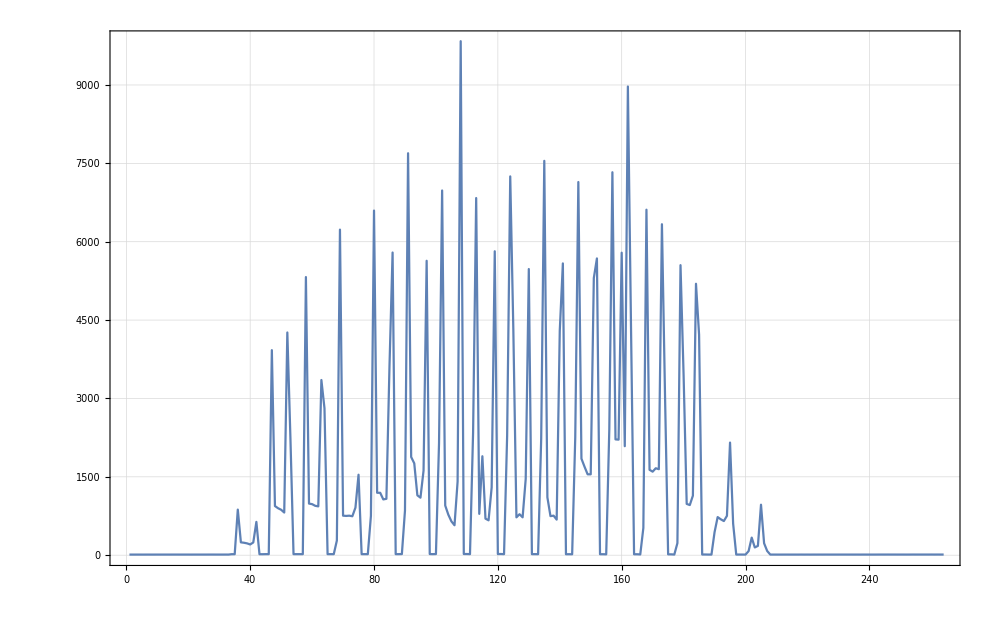

```mathematica
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000]
```

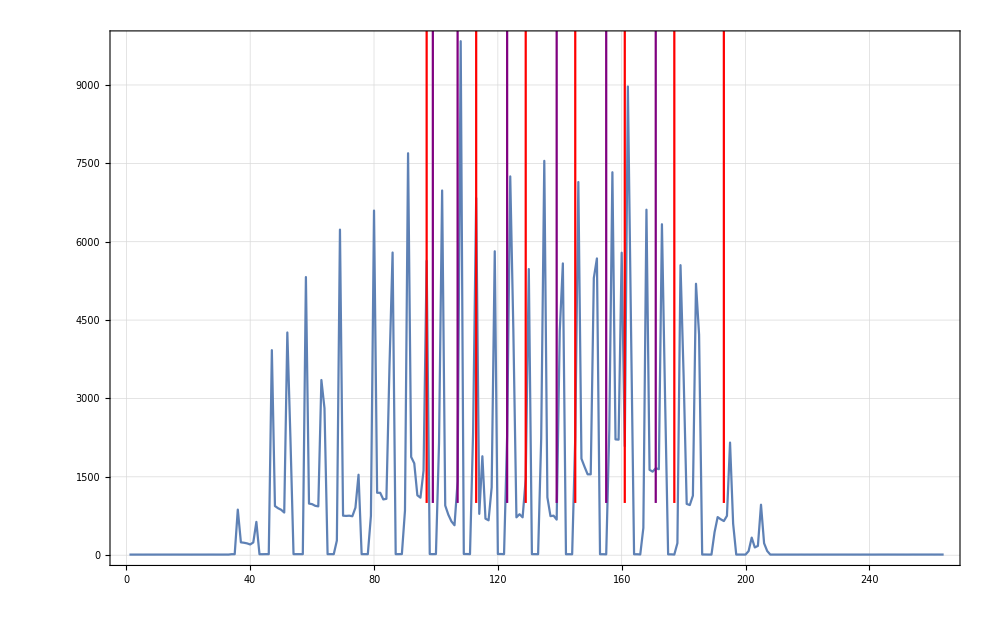

```mathematica
Show[
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000],
ParametricPlot[{{97,1000*d},{113,1000*d},{129,1000*d},{145,1000*d},{161,1000*d},{177,1000*d},{193,1000*d}},{d,1,253},PlotStyle->Red],
ParametricPlot[{{99,1000*d},{107,1000*d},{123,1000*d},{139,1000*d},{155,1000*d},{171,1000*d}},{d,1,253},PlotStyle->Purple]
]
```

## get Bin data

```mathematica
(xStart-xEnd)/24
```

-0.001875

```mathematica
158/220.
```

0.718182

```mathematica
158+62
```

220

```mathematica
xyBins[[1]]
```

{{0.025,0.02625},{-0.02,-0.015909}}

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto={{-0.06999999999999999,-0.06499999999999999,-0.05999999999999999,-0.05499999999999999,-0.04999999999999999,-0.04499999999999999,-0.039999999999999994,-0.03499999999999999,-0.029999999999999992,-0.024999999999999994,-0.01999999999999999,-0.014999999999999993,-0.009999999999999995,-0.0049999999999999906,1.3877787807814457*^-17,0.0050000000000000044,0.010000000000000009,0.015000000000000013,0.020000000000000004,0.02500000000000001,0.030000000000000013,0.035,0.04000000000000001,0.045},{-1.0540019999999999,-1.049002,-1.0440019999999999,-1.039002,-1.0340019999999999,-1.029002,-1.0240019999999999,-1.019002,-1.0140019999999998,-1.009002,-1.0040019999999998,-0.9990019999999998,-0.9940019999999998,-0.9890019999999999,-0.9840019999999998,-0.9790019999999999,-0.9740019999999999,-0.9690019999999999,-0.9640019999999999,-0.9590019999999999,-0.9540019999999999,-0.9490019999999999,-0.9440019999999999},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=0.757116
```

0.757116

```mathematica
xyBins[[1,1]]
```

{0.025,0.02625}

```mathematica
Clear[BinCenters]
```

### Get XY Bins with Ybins halfed

```mathematica
XYBinBoundariesYHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
Length[XYBinBoundariesYHalf]
```

253

```mathematica
xStart=-0.06999999999999999;
xEnd=0.045;
yStart=1.0540019999999999-R;
yEnd=0.9440019999999999-R;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
XYBinBoundariesYHalf[[1]]
```

{{-0.07,-0.065},{0.286884,0.296884}}

```mathematica
XYBinCentersYHalf[[1]]
```

{0.0209375,-0.026818}

## check spectrum

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

```mathematica
35/1000+2rG[pmax,45*Pi/180,0.976]
```

0.0407385

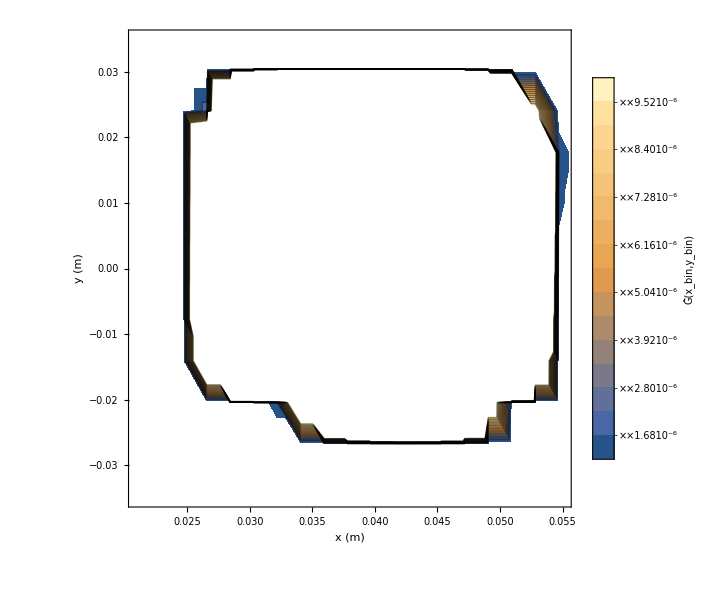

```mathematica
TransferContourPlot=ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->15,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"],PlotRange->{{0.021,0.055},{-0.035,0.035},{10^-6,10^-5}}]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/Transfer3D.png",Transfer3DPlot,ImageResolution->450];
Export["~/Dropbox/PhD/PhDLatex/Figures/TransferContour.png",TransferContourPlot,ImageResolution->450];*)
```

```mathematica
0.01*0.035
```

0.00035

```mathematica
0.02*0.05
```

0.001

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a1050/"];
```

```mathematica
d0SubFileNamesa1050P=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_da0_a1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_179-264.txt}

```mathematica
d0Spectruma1050P=Flatten[Table[Import[d0SubFileNamesa1050P[[i]],"Table"],{i,1,Length[d0SubFileNamesa1050P]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050P[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d1050PSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050P[[All,2]]/Total[d0Spectruma1050P[[All,2]]]}]];
```

# dalpha, k=97.07

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1050/"];
```

```mathematica
dAlphaSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_179-264.txt}

```mathematica
dAlphaSpectruma0=Flatten[Table[Import[dAlphaSubFileNamesa0[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1040/"];
```

```mathematica
dAlphaSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_179-264.txt}

```mathematica
dAlphaSpectruma1040=Flatten[Table[Import[dAlphaSubFileNamesa1040[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1040]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1045/"];
```

```mathematica
dAlphaSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_179-264.txt}

```mathematica
dAlphaSpectruma1045=Flatten[Table[Import[dAlphaSubFileNamesa1045[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1045]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1055/"];
```

```mathematica
dAlphaSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_179-264.txt}

```mathematica
dAlphaSpectruma1055=Flatten[Table[Import[dAlphaSubFileNamesa1055[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1055]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1060/"];
```

```mathematica
dAlphaSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectruma1060=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesa1060,1];
```

```mathematica
dAlphaSpectruma1060[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000114515,0.000184805,0.000179744,0.000174875,0.000170191,0.000165646,0.000010631,0.,0.,0.,0.,0.00208322,0.00335448,0.00326392,0.00317675,0.00309282,0.00299578,0.000207217,0.,0.,0.,0.,0.00929392,0.0149753,0.0145837,0.0142061,0.0138419,0.0132834,0.00105432,0.,0.,0.,7.85747×10^-6,0.0241814,0.0390404,0.0380869,0.0371627,0.0362673,0.0344372,0.00311712,0.,0.,0.,0.0000994742,0.0461065,0.0749538,0.073444,0.0719523,0.0704979,0.0663773,0.00696375,0.,0.,0.,0.000359707,0.0695109,0.114023,0.112425,0.110812,0.109204,0.102377,0.0118254,0.,0.,0.,0.000644083,0.086333,0.142981,0.141995,0.140934,0.139836,0.131063,0.016007,0.,0.,0.,0.000818567,0.0897408,0.149729,0.1496,0.149415,0.149195,0.139876,0.0179104,0.,0.,0.,0.000872587,0.0811859,0.136282,0.136895,0.137409,0.137896,0.129115,0.0173718,0.,0.,0.,0.000845437,0.0628334,0.106529,0.10785,0.109074,0.110264,0.103298,0.0146209,0.,0.,0.,0.000667292,0.0393762,0.06762,0.0693104,0.0709273,0.0725289,0.068283,0.0101124,0.,0.,0.,0.000346991,0.0180153,0.0314942,0.0329486,0.0343894,0.035846,0.0341913,0.00540924,0.,0.,0.,0.0000759947,0.00552551,0.00980404,0.0104646,0.0111522,0.0118759,0.0114018,0.0019883,0.,0.,0.,2.96194×10^-6,0.00121318,0.00217354,0.00237672,0.00259275,0.00282247,0.00277463,0.000475478,0.,0.,0.,0.,0.000116968,0.000221071,0.000258751,0.000300942,0.000348035,0.000369349,0.0000579729,0.,0.,0.,0.,8.80772×10^-7,2.11344×10^-6,3.21047×10^-6,4.59463×10^-6,6.53823×10^-6,8.64622×10^-6,1.15482×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,xStart,xEnd},{y,yStart,yEnd},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0200032,-0.029995} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
dBRxBSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

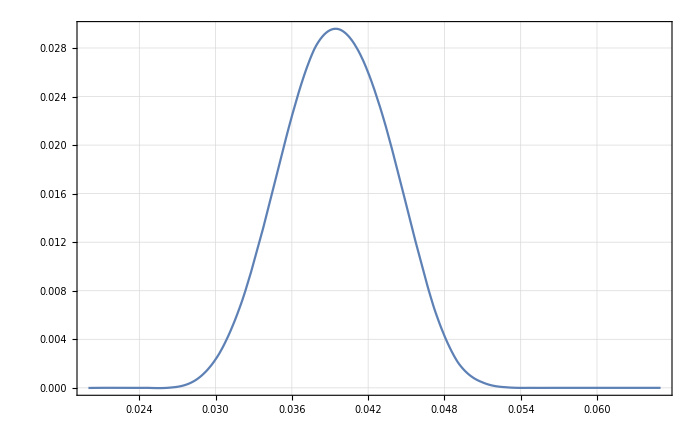

```mathematica
Plot[RefSpectrumInter[x,0.],{x,xStart,xEnd},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

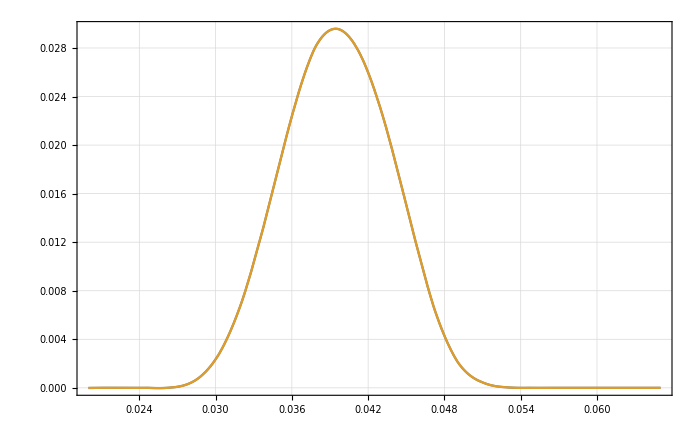

```mathematica
Plot[{RefSpectrumInter[x,0.],dBRxBSpectrumb0Inter[x,0.]},{x,xStart,xEnd},PlotRange->All]
```

```mathematica
dBRxBSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}]];
dBRxBSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]]}]];
dBRxBSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]]}]];
dBRxBSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

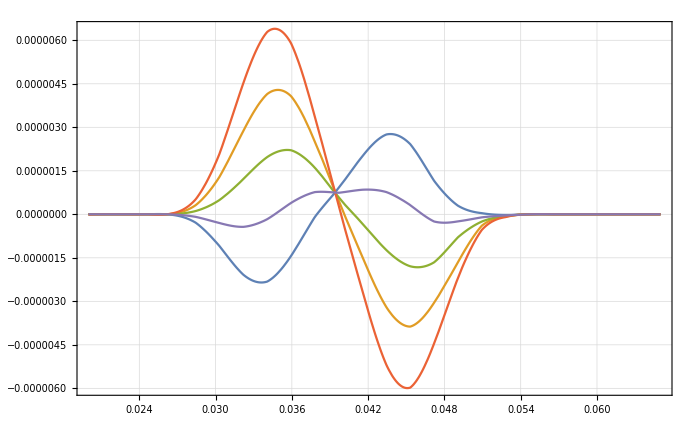

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBRxBSpectrumbm15Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumbm75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb0Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb15Inter[x,0.]
}
,{x,xStart,xEnd},PlotRange->All]
```

```mathematica
ListPlot[Total[(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-#)^2]&/@BRxBDataList]
```

ListPlot::lpn: BRxBDataList is not a list of numbers or pairs of numbers.

ListPlot[BRxBDataList]

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
dAlphaSpectruma1040[[All,2]]//Length
```

362

```mathematica
dAlphaSpectruma1055[[All,2]]//Length
```

264

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

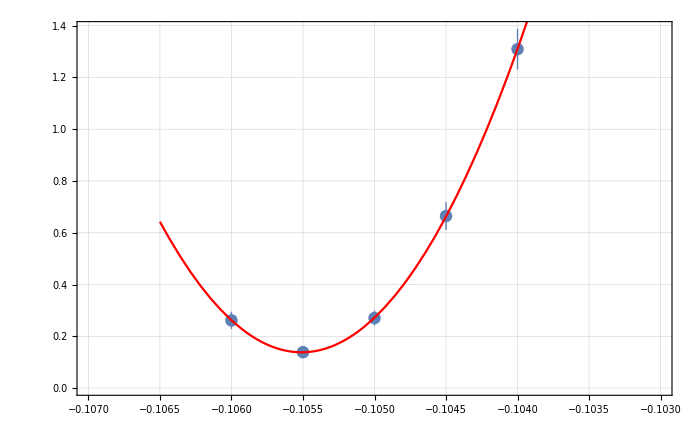
{{{1.30928×10^-9,6.64616×10^-10,2.70495×10^-10,1.38769×10^-10,2.61511×10^-10},{7.86811×10^-11,5.31884×10^-11,2.90487×10^-11,1.67193×10^-11,3.31935×10^-11}},a0 =  | -0.10551
FittedModel[1.38332×10^-10+0.000514142 (0.10551+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.10551 | 0.0000414574 | -2545.01 | 1.5439×10^-7
scale | 0.000514142 | 0.000043962 | 11.6952 | 0.00723196
yoffset | 1.38332×10^-10 | 1.41633×10^-11 | 9.76692 | 0.010321 | 
 | DF | SS | MS
Model | 3 | 650.7 | 216.9
Error | 2 | 0.00474935 | 0.00237467
Uncorrected Total | 5 | 650.705 | 
Corrected Total | 4 | 286.56 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
(-0.1055096205659537+0.105)/-0.105
```

0.00485353

```mathematica
0.004853529199559075*1/(5*10^-5)
```

97.0706

```mathematica
0.1*10^-3*97.07
```

0.009707

```mathematica
-0.105+(0.105*0.01)
```

-0.10395

```mathematica
-0.1042255483567612
```

```mathematica
AlphaInvest[[2,1,1,2]]
```

-0.10551

```mathematica
(AlphaInvest[[2,1,1,2]]+0.105)/(-0.105)/(5*10^-5)
```

97.0706

```mathematica
0.004853529199559075/(5*10^-5)
```

97.0706

# drF, k=4.43

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1050/"];
```

```mathematica
drFSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drF_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_179-264.txt}

```mathematica
drFSpectruma0=Flatten[Table[Import[drFSubFileNamesa0[[i]],"Table"],{i,1,Length[drFSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1040/"];
```

```mathematica
drFSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_179-264.txt}

```mathematica
drFSpectruma1040=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1040,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1045/"];
```

```mathematica
drFSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drF_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_179-264.txt}

```mathematica
drFSpectruma1045=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1045,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1055/"];
```

```mathematica
drFSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_drF_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_179-264.txt}

```mathematica
drFSpectruma1055=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

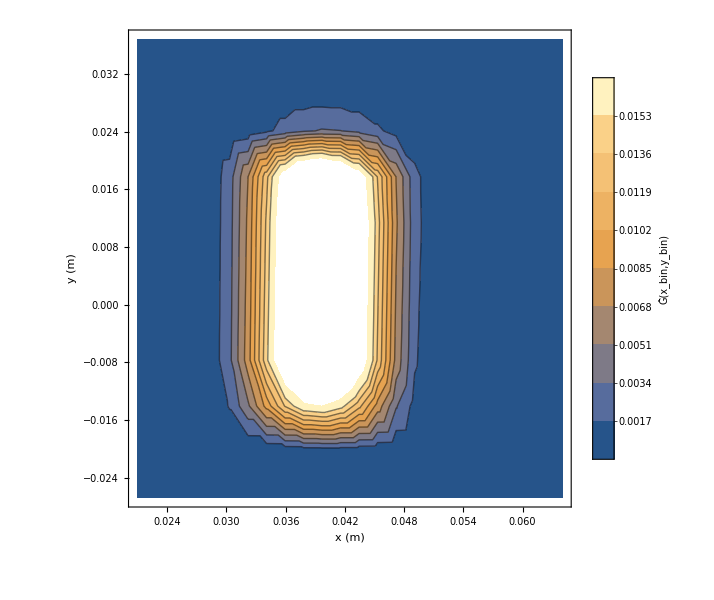

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1060/"];
```

```mathematica
drFSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drFSpectruma1060=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1060,1];
```

```mathematica
drFSpectruma1055[[All,2]]//Length
```

264

```mathematica
drFSpectruma1060[[All,2]]//Length
```

256

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1060[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,«11»,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,«214»},{«1»},{«1»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375},{-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225},{0.,4.47425×10^-7,6.02744×10^-7,5.91973×10^-7,5.81468×10^-7,5.71224×10^-7,5.61233×10^-7,5.51489×10^-7,5.41986×10^-7,5.32718×10^-7,4.75389×10^-8,0.,0.0000879969,0.000119268,0.000117147,0.000115078,0.000113059,0.000111091,0.00010917,0.000107297,0.00010543,0.0000104977,0.,0.000701745,0.000952878,0.00093608,0.000919691,0.000903701,0.000888099,0.000872877,0.000858025,0.000839179,0.0000834952,3.5836×10^-6,0.00239433,0.00325997,0.00320344,0.00314825,0.00309437,0.00304178,0.00299043,0.00294031,0.00284975,0.000327453,0.000037155,0.00559804,0.00767238,0.00754283,0.00741622,0.0072925,0.00717161,0.00705348,0.00693807,0.00664837,0.000848306,0.000165113,0.0105384,0.0145972,0.0143612,0.0141301,0.0139039,0.0136825,0.0134658,0.0132537,0.0125429,0.00178018,0.000466438,0.0171219,0.0240336,0.0236801,0.0233297,0.022985,0.0226459,0.0223126,0.021985,0.0205558,0.00321438,0.00096978,0.0246906,0.0351399,0.0347259,0.0342925,0.0338625,0.0334367,0.0330126,0.0325974,0.0301499,0.00514795,0.00159149,0.0322596,0.0464223,0.0460451,0.0455901,0.0451366,0.0446842,0.0442341,0.0437851,0.0401522,0.0544281,0.0540196,0.0492595,0.00942923,0.00266363,0.0428271,0.0626197,0.0626168,0.0623765,0.0621288,0.0618731,0.0616107,0.0613375,0.05573,0.011033,0.00295451,0.0436845,0.0643068,0.0645062,0.0644428,0.06436,0.0642704,0.064177,0.0640722,0.0580227,0.0118582,0.00307535,0.0419021,0.0620969,0.0624748,0.062525,0.0625699,0.0626116,0.062647,0.0626745,0.0564962,0.0119396,0.00302753,0.0378254,0.056474,0.0569931,0.0571759,0.0573524,0.0575234,0.057676,0.0578325,0.0519097,0.0113495,0.00278236,0.0317647,0.0478165,0.0484712,0.0487879,0.0490987,0.0494035,0.049702,0.0499907,0.0446863,0.010074,0.00232516,0.0244053,0.0370302,0.0377635,0.0381813,0.0385945,0.0390033,0.0394075,0.0398029,0.0354729,0.00833864,0.00171419,0.0167922,0.0256606,0.0263695,0.0268248,0.0272801,0.0277306,0.0281806,0.0286239,0.0254997,0.00619068,0.00108409,0.0098629,0.015269,0.015852,0.0162725,0.0166946,0.0171238,0.0175441,0.0179669,0.0160051,0.00404876,0.000562323,0.00473851,0.00745261,0.00782324,0.00811736,0.00841886,0.00872724,0.00904185,0.00936082,0.00832003,0.00225943,0.000226292,0.00197739,0.00313934,0.00331034,0.00345557,0.00360644,0.00376261,0.00392418,0.0040914,0.00361137,0.00103357,0.0000710994,0.000718059,0.00114017,0.00121167,0.00127949,0.00135001,0.00142319,0.00149911,0.00157783,0.00141378,0.000393956,0.0000121256,0.000189393,0.000301593,0.000326884,0.000353033,0.000380663,0.000409764,0.000440381,0.000472558,0.000439617,0.00011556,4.52877×10^-7,0.0000258848,0.0000418482,0.0000476277,0.0000539891,0.0000609723,0.000068562,0.0000768318,0.0000858192,0.0000850529,0.0000185858,0.,6.46386×10^-7,1.16186×10^-6,1.71743×10^-6,2.60735×10^-6,2.55523×10^-6,3.22825×10^-6,4.01108×10^-6,5.00119×10^-6,5.74377×10^-6,1.0528×10^-6}}],PlotRange→All]

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0250021,-0.0199964} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
drFSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma0[[All,2]]/Total[drFSpectruma0[[All,2]]]}]];
```

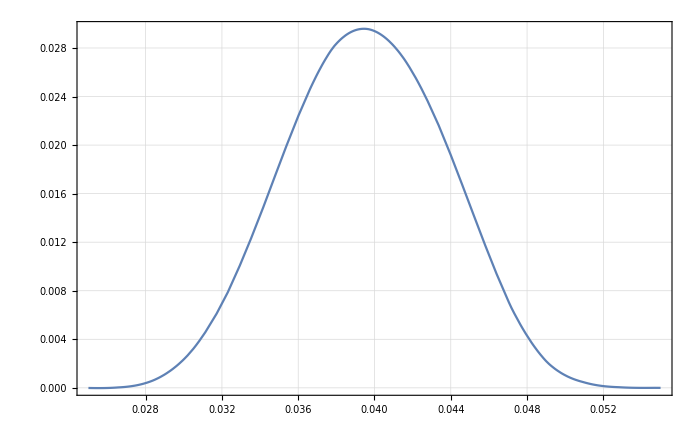

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

```mathematica
drFSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1040[[All,2]]/Total[drFSpectruma1040[[All,2]]]}]];
drFSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1045[[All,2]]/Total[drFSpectruma1045[[All,2]]]}]];
drFSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]}]];
```

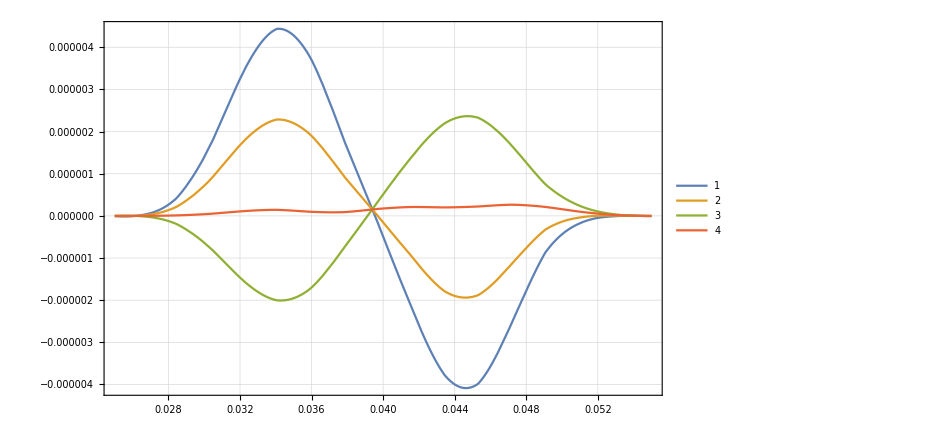

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drFSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
rFDataList={drFSpectruma1040[[All,2]]/Total[drFSpectruma1040[[All,2]]],drFSpectruma1045[[All,2]]/Total[drFSpectruma1045[[All,2]]],drFSpectruma0[[All,2]]/Total[drFSpectruma0[[All,2]]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]],drFSpectruma1060[[All,2]]/Total[drFSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

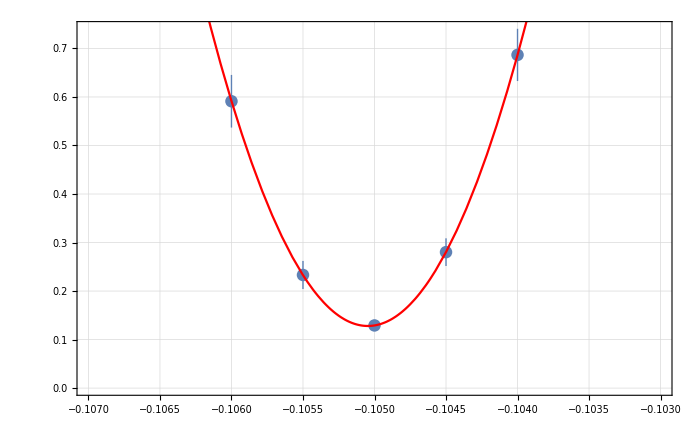
{{{6.86703×10^-10,2.80175×10^-10,1.29136×10^-10,2.33128×10^-10,5.91184×10^-10},{5.38263×10^-11,2.85119×10^-11,1.12789×10^-11,2.89544×10^-11,5.42352×10^-11}},a0 =  | -0.105047
FittedModel[1.28043×10^-10+0.000509836 (0.105047+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105047 | 0.0000275451 | -3813.62 | 6.87583×10^-8
scale | 0.000509836 | 0.0000382191 | 13.3398 | 0.0055726
yoffset | 1.28043×10^-10 | 1.06022×10^-11 | 12.077 | 0.00678645 | 
 | DF | SS | MS
Model | 3 | 574.056 | 191.352
Error | 2 | 0.000169658 | 0.0000848291
Uncorrected Total | 5 | 574.056 | 
Corrected Total | 4 | 181.206 |  | ,-Graphics-}

```mathematica
rFInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rFDataList,bList, 4]
```

```mathematica
(rFInvest[[2,1,1,2]]+0.105)/-0.105
```

0.000442949

```mathematica
0.000442948920583481/(10^-4)
```

4.42949

# drA, k=157.04

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1040/"];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1040/Cluster_Try"];
```

```mathematica
drASubFileNamesa1040Cluster=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_179-264.txt}

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040Cluster=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040Cluster,1];
```

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

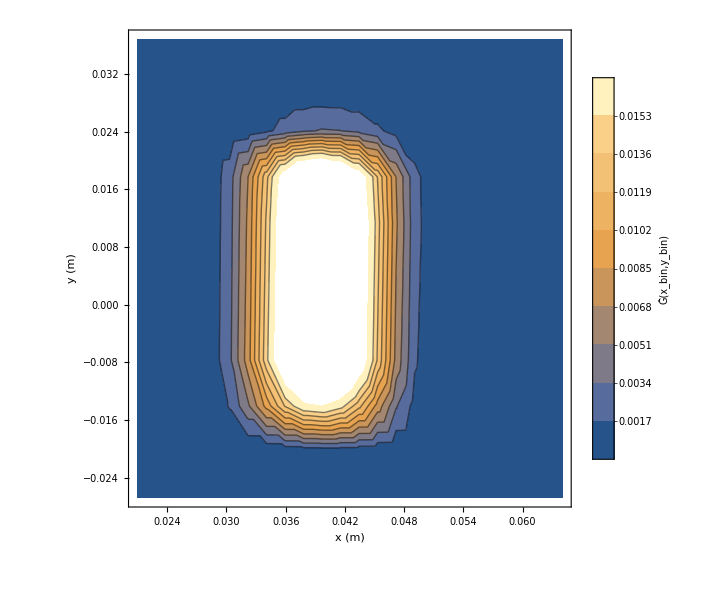

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

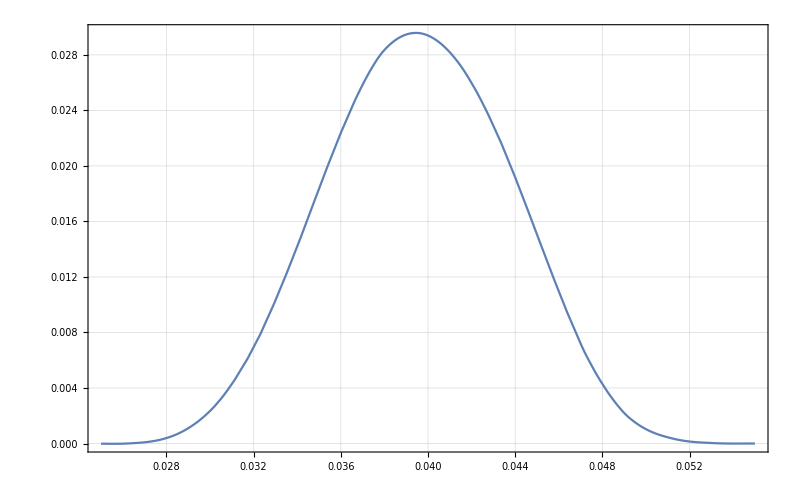

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

```mathematica
drASpectruma1040InterCluster=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040Cluster[[All,2]]/Total[drASpectruma1040Cluster[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

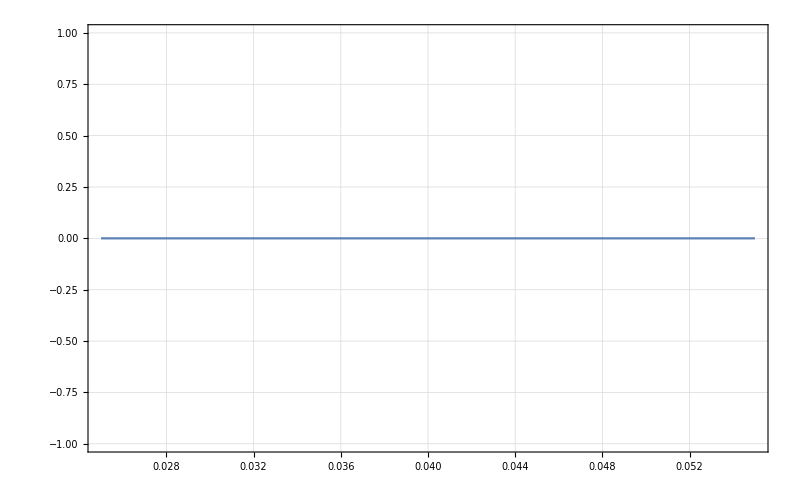

```mathematica
Plot[drASpectruma1040Inter[x,0.]-drASpectruma1040InterCluster[x,0.],{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
1.97*10^-3
```

0.00197

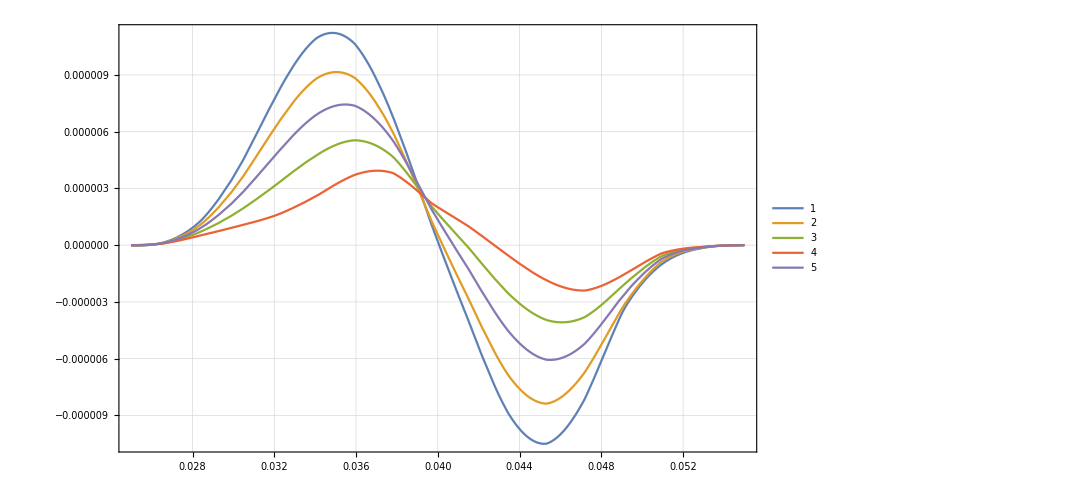

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

### a=-1065

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1065/"];
```

```mathematica
drASubFileNamesa1065=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1065_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1065=Flatten[Import[#,"Table"]&/@drASubFileNamesa1065,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1065[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1070

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1070/"];
```

```mathematica
drASubFileNamesa1070=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1070_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1070=Flatten[Import[#,"Table"]&/@drASubFileNamesa1070,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1070[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1075

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1075/"];
```

```mathematica
drASubFileNamesa1075=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1075_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1075=Flatten[Import[#,"Table"]&/@drASubFileNamesa1075,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1075[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList2={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]],drASpectruma1075[[All,2]]/Total[drASpectruma1075[[All,2]]]};
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]],drASpectruma1065[[All,2]]/Total[drASpectruma1065[[All,2]]],drASpectruma1070[[All,2]]/Total[drASpectruma1070[[All,2]]],drASpectruma1075[[All,2]]/Total[drASpectruma1075[[All,2]]]};
```

```mathematica
bList2={-0.104,-.1045,-.105,-.1055,-0.1060,-0.1075}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1075}

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060,-0.1065,-0.1070,-0.1075}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1065,-0.107,-0.1075}

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

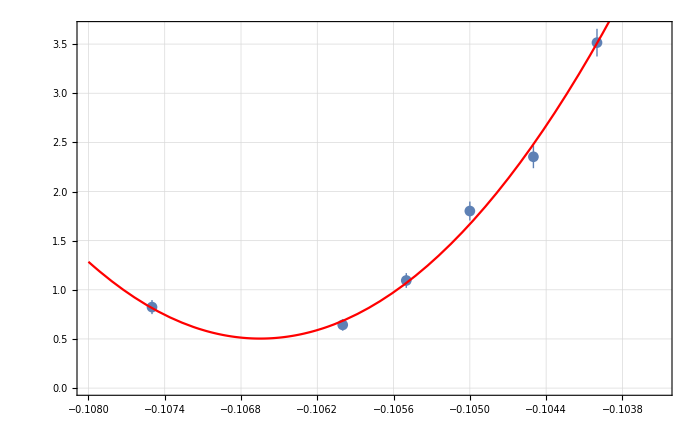
{{{3.51471×10^-9,2.35326×10^-9,1.80157×10^-9,1.09474×10^-9,6.43061×10^-10,8.24147×10^-10},{1.40892×10^-10,1.16125×10^-10,9.64692×10^-11,7.53158×10^-11,5.8544×10^-11,7.15789×10^-11}},a0 =  | -0.106649
FittedModel[5.03778×10^-10+0.000428131 (0.106649+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106649 | 0.0000571871 | -1864.91 | 3.40012×10^-10
scale | 0.000428131 | 0.0000281651 | 15.2008 | 0.00061823
yoffset | 5.03778×10^-10 | 4.57292×10^-11 | 11.0166 | 0.00160176 | 
 | DF | SS | MS
Model | 3 | 1842.46 | 614.155
Error | 3 | 3.75941 | 1.25314
Uncorrected Total | 6 | 1846.22 | 
Corrected Total | 5 | 527.277 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rADataList2,bList2, 4]
```

```mathematica
(-0.10664900148918234+0.105)/-0.105/(10^-4)
```

157.048

```mathematica
0.003/157.047760874509
```

0.0000191025

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

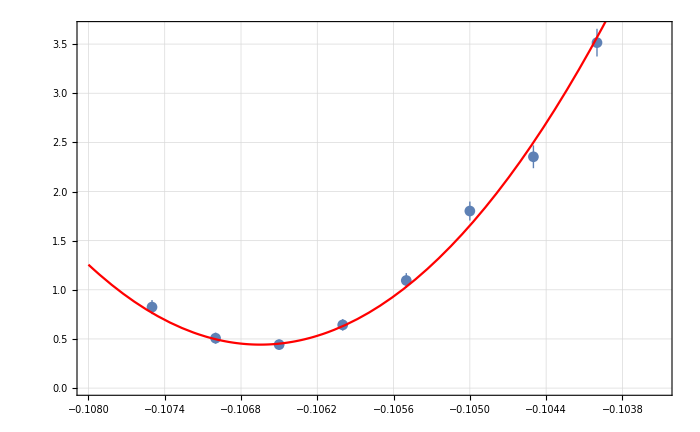
{{{3.51471×10^-9,2.35326×10^-9,1.80157×10^-9,1.09474×10^-9,6.43061×10^-10,4.42288×10^-10,5.07741×10^-10,8.24147×10^-10},{1.40892×10^-10,1.16125×10^-10,9.64692×10^-11,7.53158×10^-11,5.8544×10^-11,5.08038×10^-11,5.64233×10^-11,7.15789×10^-11}},a0 =  | -0.106649
FittedModel[4.42288×10^-10+0.000445521 (0.106649+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106649 | 0.0000513687 | -2076.14 | 4.92061×10^-16
scale | 0.000445521 | 0.0000263228 | 16.9253 | 0.000013168
yoffset | 4.42288×10^-10 | 2.94575×10^-11 | 15.0145 | 0.0000237319 | 
 | DF | SS | MS
Model | 3 | 1997.37 | 665.79
Error | 5 | 5.62228 | 1.12446
Uncorrected Total | 8 | 2002.99 | 
Corrected Total | 7 | 744.691 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rADataList,bList, 4]
```

```mathematica
((-0.10664865012298552+0.105)/-0.105)/(10^-4)
```

157.014

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

157.014

```mathematica
((-0.10664865012298552+0.105)/-0.105)/(10^-4)
```

157.014

# dB, k=69.93

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1050/"];
```

```mathematica
dBSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_179-264.txt}

```mathematica
dBSpectruma0=Flatten[Table[Import[dBSubFileNamesa0[[i]],"Table"],{i,1,Length[dBSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1040/"];
```

```mathematica
dBSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_179-264.txt}

```mathematica
dBSpectruma1040=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1045/"];
```

```mathematica
dBSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dB_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_179-264.txt}

```mathematica
dBSpectruma1045=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1055/"];
```

```mathematica
dBSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_179-264.txt}

```mathematica
dBSpectruma1055=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

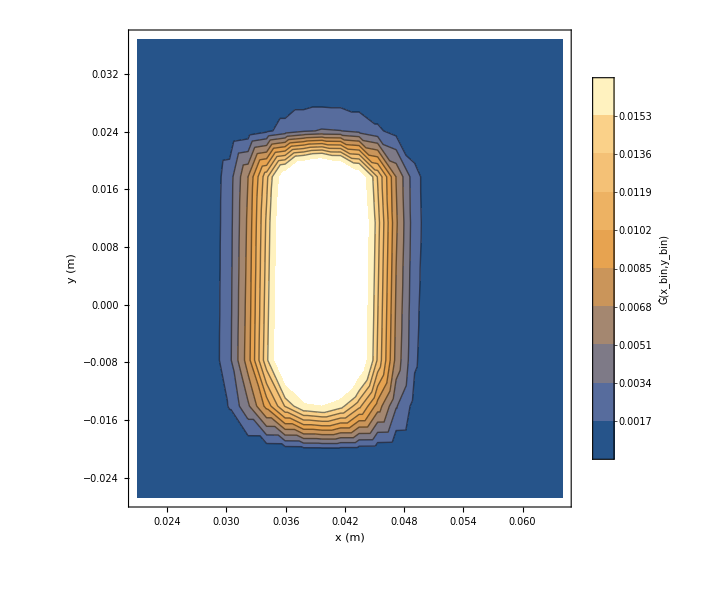

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1060/"];
```

```mathematica
dBSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dB_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dBSpectruma1060=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dBSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dBSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]]}]];
dBSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]]}]];
dBSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]]}]];
dBSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]}]];
```

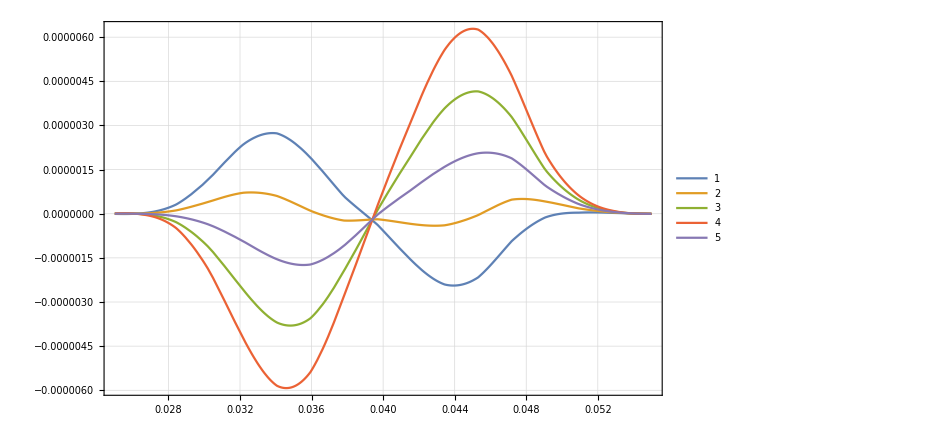

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
BDataList={dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]],dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

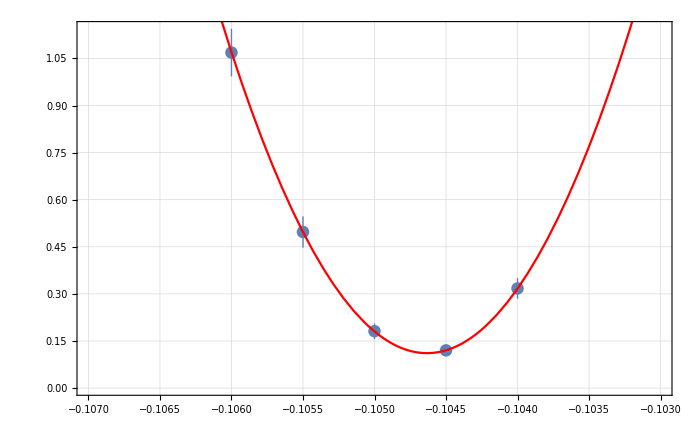
{{{3.17415×10^-10,1.20191×10^-10,1.81208×10^-10,4.97177×10^-10,1.06859×10^-9},{3.27248×10^-11,1.16634×10^-11,2.47023×10^-11,4.97713×10^-11,7.57612×10^-11}},a0 =  | -0.104633
FittedModel[1.11361×10^-10+0.000512848 (0.104633+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104633 | 0.00003187 | -3283.12 | 9.27742×10^-8
scale | 0.000512848 | 0.0000411871 | 12.4517 | 0.00638805
yoffset | 1.11361×10^-10 | 1.1474×10^-11 | 9.70545 | 0.0104501 | 
 | DF | SS | MS
Model | 3 | 552.813 | 184.271
Error | 2 | 0.00192816 | 0.000964081
Uncorrected Total | 5 | 552.815 | 
Corrected Total | 4 | 222.042 |  | ,-Graphics-}

```mathematica
BInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
.106*6.930
```

0.73458

```mathematica
.75*.1
```

0.075

```mathematica
.15*69.93
```

10.4895

```mathematica
.15*69.93
```

10.4895

```mathematica
(BInvest[[2,1,1,2]]+0.105)/-0.105
```

-0.00349668

```mathematica
-0.003496680950444102/(5*10^-5)
```

-69.9336

```mathematica
.1*97.07
```

9.707

```mathematica
Sqrt[10.489500000000001^2+9.707^2]
```

14.2918

```mathematica
14*10^-3.
```

0.014

```mathematica
%*100
```

1.4

```mathematica
18*4
```

72

```mathematica
1/7.83
```

0.127714

# drRxB, k=43.62

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1050/"];
```

```mathematica
drRxBSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_179-264.txt}

```mathematica
drRxBSpectruma0=Flatten[Table[Import[drRxBSubFileNamesa0[[i]],"Table"],{i,1,Length[drRxBSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1040/"];
```

```mathematica
drRxBSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_179-264.txt}

```mathematica
drRxBSpectruma1040=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1045/"];
```

```mathematica
drRxBSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_179-264.txt}

```mathematica
drRxBSpectruma1045=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1055/"];
```

```mathematica
drRxBSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_179-264.txt}

```mathematica
drRxBSpectruma1055=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

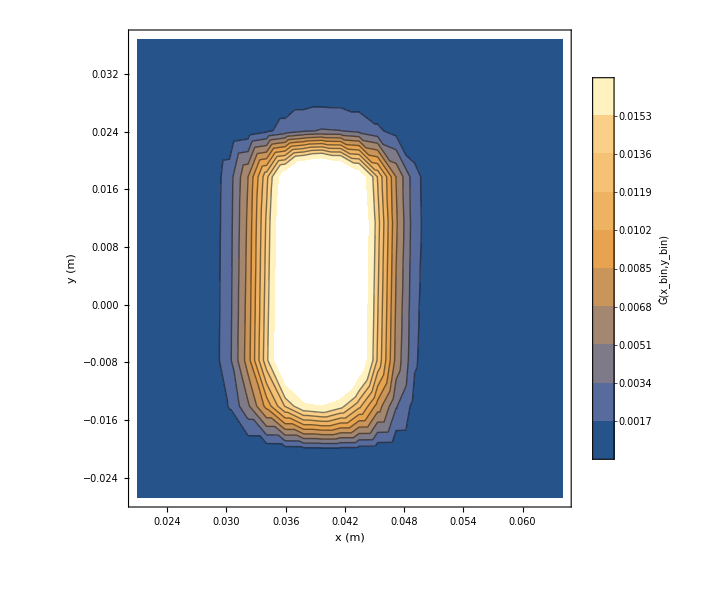

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1055[[All,2]]/Total[drRxBSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1060/"];
```

```mathematica
drRxBSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drRxBSpectruma1060=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drRxBSpectruma0[[All,2]]/Total[drRxBSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drRxBSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma0[[All,2]]/Total[drRxBSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
drRxBSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1040[[All,2]]/Total[drRxBSpectruma1040[[All,2]]]}]];
drRxBSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1045[[All,2]]/Total[drRxBSpectruma1045[[All,2]]]}]];
drRxBSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1055[[All,2]]/Total[drRxBSpectruma1055[[All,2]]]}]];
drRxBSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1060[[All,2]]/Total[drRxBSpectruma1060[[All,2]]]}]];
```

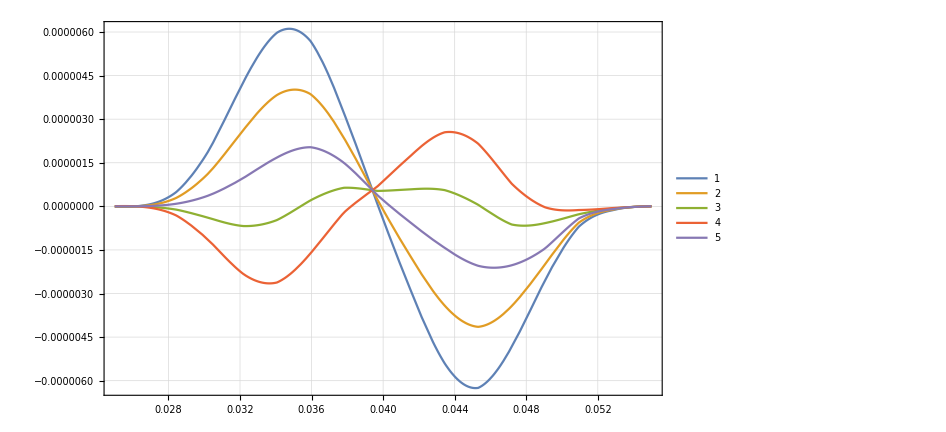

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drRxBSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
rRxBDataList={drRxBSpectruma1040[[All,2]]/Total[drRxBSpectruma1040[[All,2]]],drRxBSpectruma1045[[All,2]]/Total[drRxBSpectruma1045[[All,2]]],drRxBSpectruma0[[All,2]]/Total[drRxBSpectruma0[[All,2]]],drRxBSpectruma1055[[All,2]]/Total[drRxBSpectruma1055[[All,2]]],drRxBSpectruma1060[[All,2]]/Total[drRxBSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

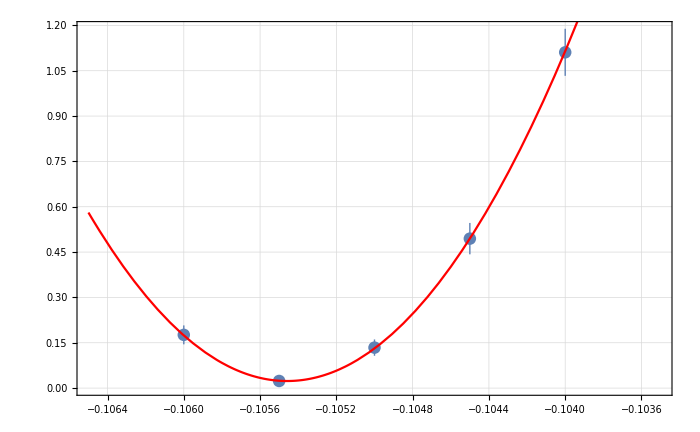
{{{1.11093×10^-9,4.94473×10^-10,1.33884×10^-10,2.35734×10^-11,1.76109×10^-10},{7.78298×10^-11,5.18879×10^-11,2.69823×10^-11,1.22177×10^-11,3.12751×10^-11}},a0 =  | -0.105458
FittedModel[2.34228×10^-11+0.000513376 (0.105458+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105458 | 0.000036153 | -2916.99 | 1.17525×10^-7
scale | 0.000513376 | 0.0000412367 | 12.4495 | 0.00639024
yoffset | 2.34228×10^-11 | 1.12144×10^-11 | 2.08863 | 0.171959 | 
 | DF | SS | MS
Model | 3 | 354.587 | 118.196
Error | 2 | 0.020374 | 0.010187
Uncorrected Total | 5 | 354.607 | 
Corrected Total | 4 | 272.567 |  | ,-Graphics-}

```mathematica
rRxBInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rRxBDataList,bList, 4]
```

```mathematica
((rRxBInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

43.6187

```mathematica
((rRxBInvest[[2,1,1,2]]+0.105)/-0.105)*100
```

0.436187

# dG1, k=0.135

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1050/"];
```

```mathematica
dG1SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_179-264.txt}

```mathematica
dG1Spectruma0=Flatten[Table[Import[dG1SubFileNamesa0[[i]],"Table"],{i,1,Length[dG1SubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1040/"];
```

```mathematica
dG1SubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dG1_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_179-264.txt}

```mathematica
dG1Spectruma1040=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1045/"];
```

```mathematica
dG1SubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_179-264.txt}

```mathematica
dG1Spectruma1045=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1055/"];
```

```mathematica
dG1SubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_179-264.txt}

```mathematica
dG1Spectruma1055=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

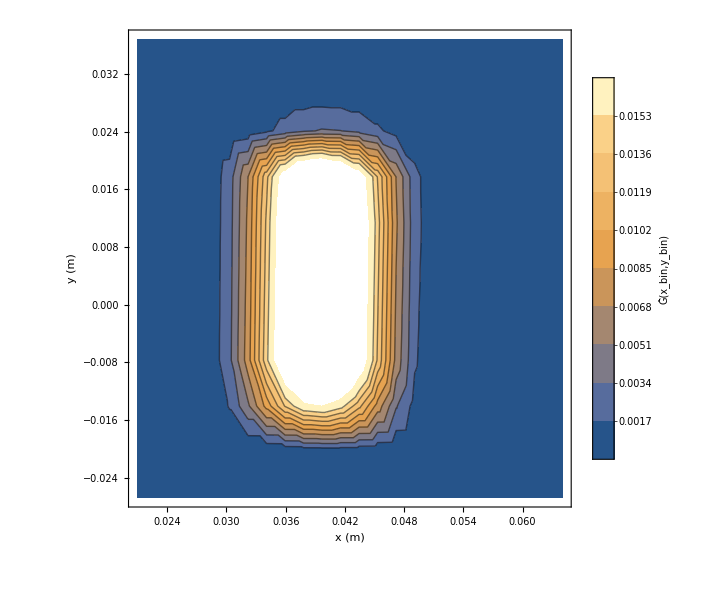

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]/Total[dG1Spectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1060/"];
```

```mathematica
dG1SubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dG1Spectruma1060=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dG1Spectruma0[[All,2]]/Total[dG1Spectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dG1Spectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma0[[All,2]]/Total[dG1Spectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dG1Spectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1040[[All,2]]/Total[dG1Spectruma1040[[All,2]]]}]];
dG1Spectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1045[[All,2]]/Total[dG1Spectruma1045[[All,2]]]}]];
dG1Spectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]/Total[dG1Spectruma1055[[All,2]]]}]];
dG1Spectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1060[[All,2]]/Total[dG1Spectruma1060[[All,2]]]}]];
```

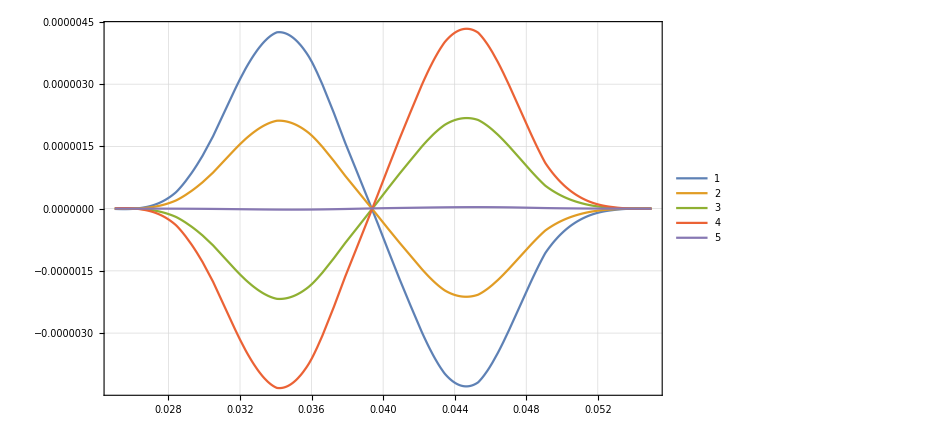

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dG1Spectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
BDataList={dG1Spectruma1040[[All,2]]/Total[dG1Spectruma1040[[All,2]]],dG1Spectruma1045[[All,2]]/Total[dG1Spectruma1045[[All,2]]],dG1Spectruma0[[All,2]]/Total[dG1Spectruma0[[All,2]]],dG1Spectruma1055[[All,2]]/Total[dG1Spectruma1055[[All,2]]],dG1Spectruma1060[[All,2]]/Total[dG1Spectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

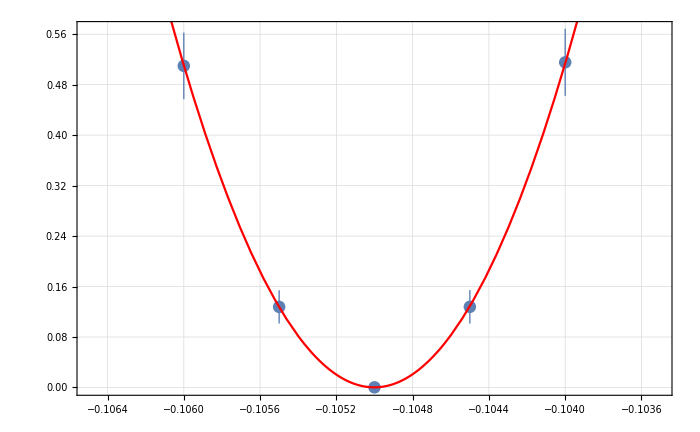
{{{5.15438×10^-10,1.2786×10^-10,2.17303×10^-13,1.2776×10^-10,5.09835×10^-10},{5.31564×10^-11,2.65551×10^-11,1.19504×10^-12,2.63586×10^-11,5.27491×10^-11}},a0 =  | -0.105001
FittedModel[2.15056×10^-13+0.000512007 (0.105001+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105001 | 0.0000258456 | -4062.65 | 6.05873×10^-8
scale | 0.000512007 | 0.0000335399 | 15.2656 | 0.00426372
yoffset | 2.15056×10^-13 | 1.19452×10^-12 | 0.180036 | 0.873715 | 
 | DF | SS | MS
Model | 3 | 234.149 | 78.0496
Error | 2 | 0.00318623 | 0.00159312
Uncorrected Total | 5 | 234.152 | 
Corrected Total | 4 | 233.044 |  | ,-Graphics-}

```mathematica
BInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
((BInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

0.134947

# dG2, k=0.069

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1050/"];
```

```mathematica
dG2SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dG2_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_179-264.txt}

```mathematica
dG2Spectruma0=Flatten[Table[Import[dG2SubFileNamesa0[[i]],"Table"],{i,1,Length[dG2SubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1040/"];
```

```mathematica
dG2SubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG2_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_179-264.txt}

```mathematica
dG2Spectruma1040=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1045/"];
```

```mathematica
dG2SubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dG2_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_179-264.txt}

```mathematica
dG2Spectruma1045=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1055/"];
```

```mathematica
dG2SubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dG2_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_179-264.txt}

```mathematica
dG2Spectruma1055=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]/Total[dG2Spectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«11»,0.0246875,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«20» «1»} cannot be transposed.

ListContourPlot::arrayerr: Transpose[{{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«12»,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«20» «1»}] must be a valid array.

ListContourPlot[Transpose[{{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625},{-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822},0.197555 Symbol[]}],BaseStyle→25,ImageSize→600,InterpolationOrder→1,Contours→9,FrameLabel→{{y (m),None},{x (m),None}},PlotLegends→BarLegend[Automatic,LabelStyle→25,LegendLabel→Ĝ(x_bin,y_bin)]]

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1060/"];
```

```mathematica
dG2SubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dG2_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dG2Spectruma1060=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dG2Spectruma0[[All,2]]/Total[dG2Spectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dG2Spectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma0[[All,2]]/Total[dG2Spectruma0[[All,2]]]}]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«11»,0.0246875,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«19» «1»} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«12»,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«19» «1»}] does not contain a list of data and coordinates.

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dG2Spectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1040[[All,2]]/Total[dG2Spectruma1040[[All,2]]]}]];
dG2Spectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1045[[All,2]]/Total[dG2Spectruma1045[[All,2]]]}]];
dG2Spectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1055[[All,2]]/Total[dG2Spectruma1055[[All,2]]]}]];
dG2Spectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1060[[All,2]]/Total[dG2Spectruma1060[[All,2]]]}]];
```

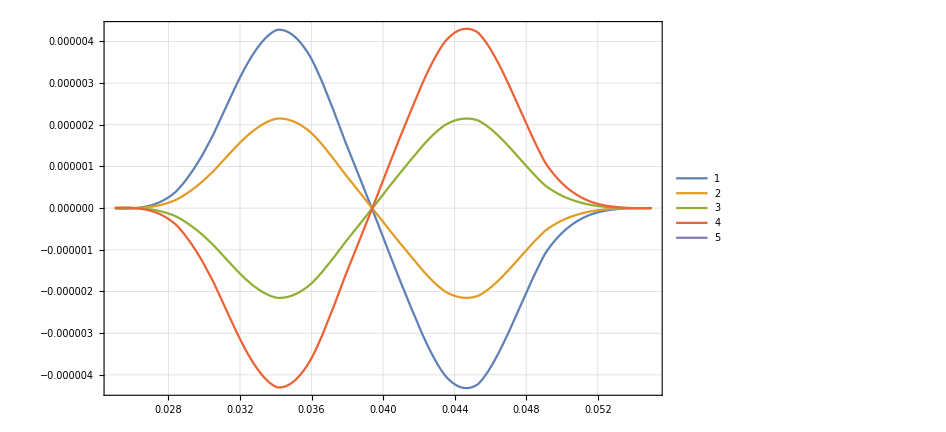

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dG2Spectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
BDataList={dG2Spectruma1040[[All,2]]/Total[dG2Spectruma1040[[All,2]]],dG2Spectruma1045[[All,2]]/Total[dG2Spectruma1045[[All,2]]],dG2Spectruma0[[All,2]]/Total[dG2Spectruma0[[All,2]]],dG2Spectruma1055[[All,2]]/Total[dG2Spectruma1055[[All,2]]],dG2Spectruma1060[[All,2]]/Total[dG2Spectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

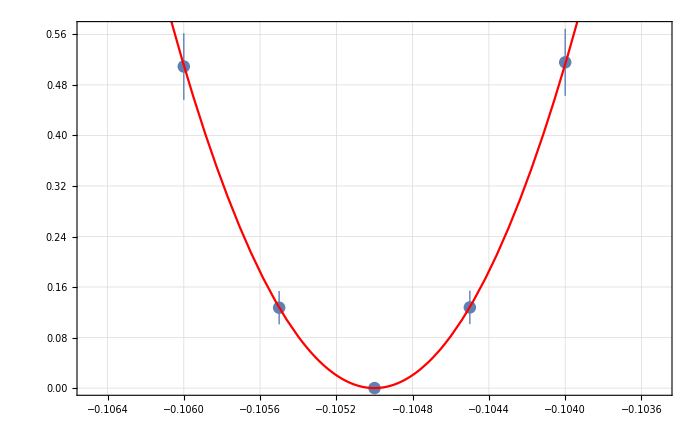
{{{5.15775×10^-10,1.27743×10^-10,2.5683×10^-17,1.27295×10^-10,5.09157×10^-10},{5.30913×10^-11,2.64645×10^-11,1.03735×10^-14,2.63815×10^-11,5.27903×10^-11}},a0 =  | -0.105001
FittedModel[5.79854×10^-24+0.000511976 (0.105001+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105001 | 0.0000258279 | -4065.4 | 6.05054×10^-8
scale | 0.000511976 | 0.0000334707 | 15.2963 | 0.00424674
yoffset | 5.79854×10^-24 | 2.17491×10^-14 | 2.66611×10^-10 | 1. | 
 | DF | SS | MS
Model | 3 | 233.979 | 77.9929
Error | 2 | 0.00612162 | 0.00306081
Uncorrected Total | 5 | 233.985 | 
Corrected Total | 4 | 233.985 |  | ,-Graphics-}

```mathematica
g2Invest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
((-0.10500072280654503+0.105)/-0.105)/(10^-4)
```

0.0688387

```mathematica
((g2Invest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

0.0688387

# drd, k=187.97

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drD_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_179-264.txt}

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1035/"];
```

```mathematica
drDSubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_179-264.txt}

```mathematica
drDSpectruma1035=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1035,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1035[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1030/"];
```

```mathematica
drDSubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drD_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_179-264.txt}

```mathematica
drDSpectruma1030=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1030,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1030[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1020/"];
```

```mathematica
drDSubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_179-264.txt}

```mathematica
drDSpectruma1020=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1020,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1020[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drD_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_179-264.txt}

```mathematica
drDSpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_179-264.txt}

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_179-264.txt}

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

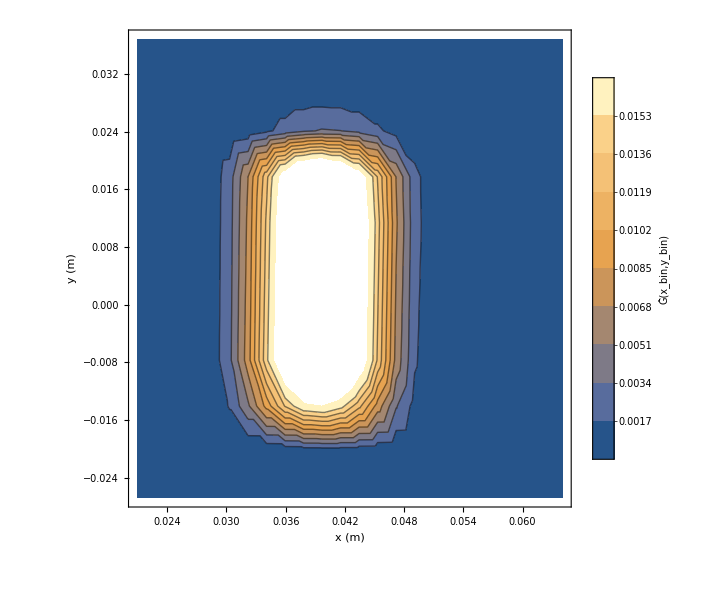

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drDSpectruma1060=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drDSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
drDSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]]}]];
drDSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]]}]];
drDSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}]];
drDSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]}]];
```

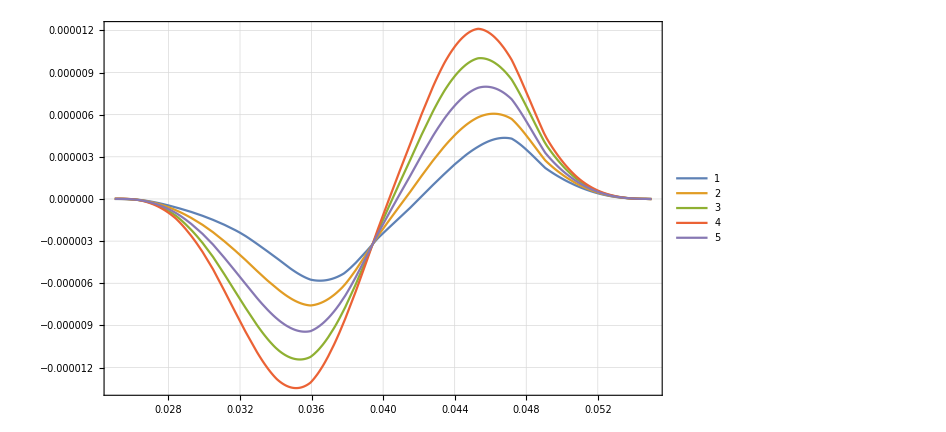

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drDSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
rDDataList={drDSpectruma1020[[All,2]]/Total[drDSpectruma1020[[All,2]]],drDSpectruma1030[[All,2]]/Total[drDSpectruma1030[[All,2]]],drDSpectruma1035[[All,2]]/Total[drDSpectruma1035[[All,2]]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.102,-0.103,-0.1035,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

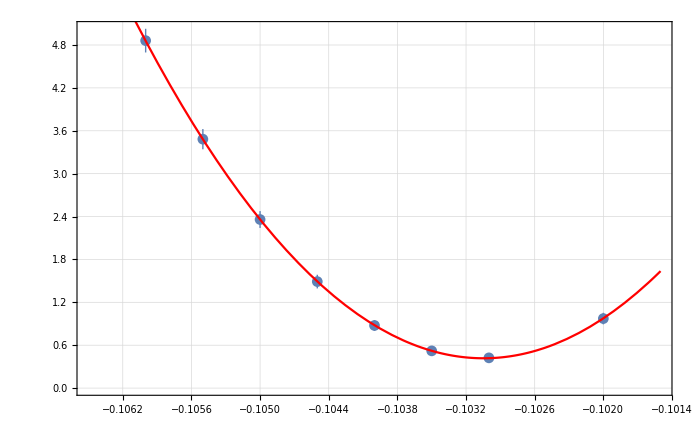
{{{9.72613×10^-10,4.23104×10^-10,5.2079×10^-10,8.75997×10^-10,1.49013×10^-9,2.35856×10^-9,3.4825×10^-9,4.86114×10^-9},{8.05613×10^-11,5.84884×10^-11,6.24937×10^-11,7.60636×10^-11,9.5516×10^-11,1.17637×10^-10,1.41231×10^-10,1.65669×10^-10}},a0 =  | -0.103047
FittedModel[4.17262×10^-10+0.000509271 (0.103047+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103047 | 0.0000439952 | -2342.24 | 2.69246×10^-16
scale | 0.000509271 | 0.0000227131 | 22.4219 | 3.27895×10^-6
yoffset | 4.17262×10^-10 | 3.55904×10^-11 | 11.724 | 0.0000793702 | 
 | DF | SS | MS
Model | 3 | 2514.53 | 838.177
Error | 5 | 0.0114451 | 0.00228902
Uncorrected Total | 8 | 2514.54 | 
Corrected Total | 7 | 1161.97 |  | ,-Graphics-}

```mathematica
rDInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rDDataList,bList, 4]
```

```mathematica
(-0.10304725773676074+0.105)/-0.105
```

-0.0185975

```mathematica
-0.018597545364183402/10^-4
```

-185.975

```mathematica
((rDInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-185.975

# dXAShift, k=57.14/1.62

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1050/"];
```

```mathematica
dXAShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_179-264.txt}

```mathematica
dXAShiftSpectruma0=Flatten[Table[Import[dXAShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1020/"];
```

```mathematica
dXAShiftSubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_179-264.txt}

```mathematica
dXAShiftSpectruma1020=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1020,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1020[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1030/"];
```

```mathematica
dXAShiftSubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_179-264.txt}

```mathematica
dXAShiftSpectruma1030=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1030,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1030[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1035/"];
```

```mathematica
dXAShiftSubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_179-264.txt}

```mathematica
dXAShiftSpectruma1035=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1035,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1035[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1040/"];
```

```mathematica
dXAShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_179-264.txt}

```mathematica
dXAShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1045/"];
```

```mathematica
dXAShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_179-264.txt}

```mathematica
dXAShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1055/"];
```

```mathematica
dXAShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_179-264.txt}

```mathematica
dXAShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

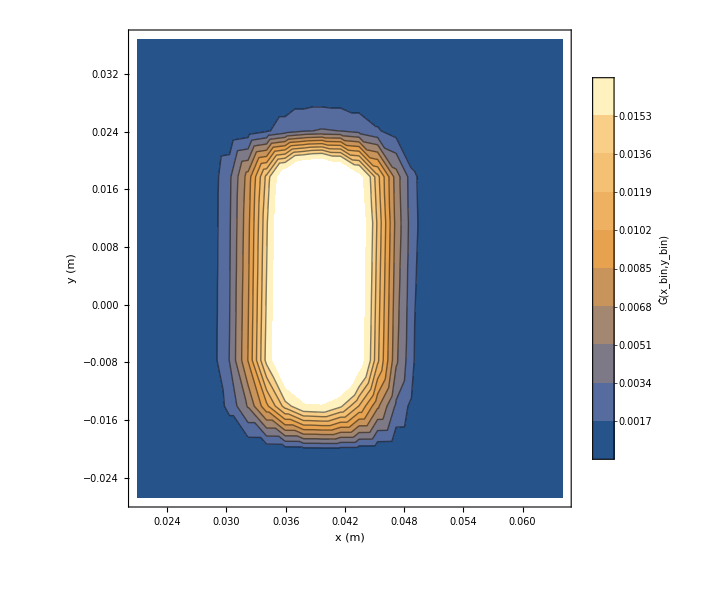

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1060/"];
```

```mathematica
dXAShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dXAShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXAShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXAShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]]}]];
dXAShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]]}]];
dXAShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]}]];
dXAShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]}]];
```

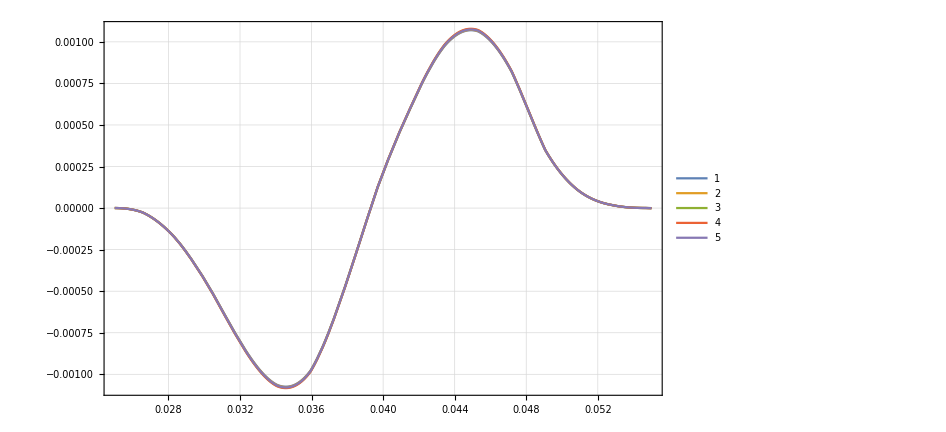

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dXAShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList,XAShiftInvest]
```

```mathematica
XAShiftDataList={dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

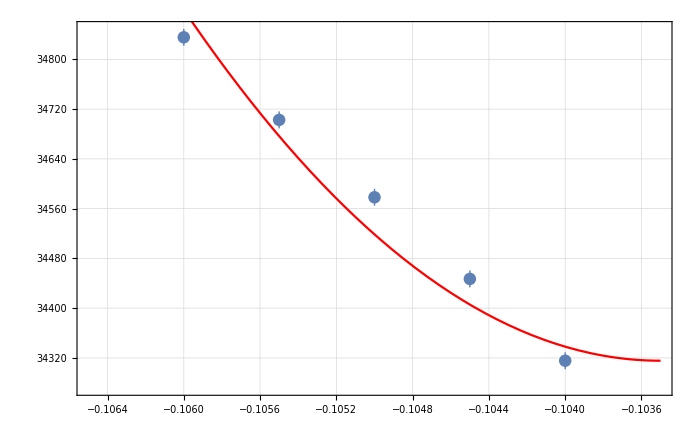
{{{0.0000343155,0.000034447,0.0000345783,0.0000347027,0.0000348354},{1.36128×10^-8,1.3639×10^-8,1.36652×10^-8,1.36875×10^-8,1.3714×10^-8}},a0 =  | -0.1035
FittedModel[0.0000343155+0.0902549 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000247235 | -418.63 | 5.70605×10^-6
scale | 0.0902549 | 0.0146073 | 6.17876 | 0.0252075
yoffset | 0.0000343155 | 2.92413×10^-8 | 1173.53 | 7.26125×10^-7 | 
 | DF | SS | MS
Model | 3 | 3.20164×10^7 | 1.06721×10^7
Error | 2 | 45.011 | 22.5055
Uncorrected Total | 5 | 3.20165×10^7 | 
Corrected Total | 4 | 899.025 |  | ,-Graphics-}

```mathematica
XAShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],XAShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

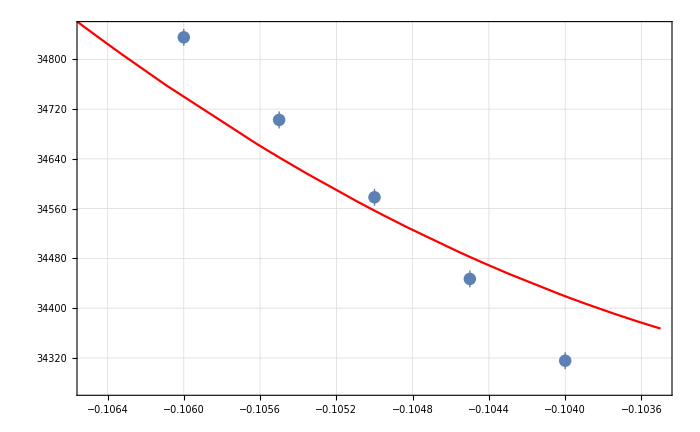
{{{0.0000343155,0.000034447,0.0000345783,0.0000347027,0.0000348354},{1.36128×10^-8,1.3639×10^-8,1.36652×10^-8,1.36875×10^-8,1.3714×10^-8}},a0 =  | -0.101429
FittedModel[0.000034271+0.022403 (0.101429+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101429 | 0.00233567 | -43.4259 | 0.000529855
scale | 0.022403 | 0.0146073 | 1.53369 | 0.264839
yoffset | 0.000034271 | 1.816×10^-7 | 188.717 | 0.0000280776 | 
 | DF | SS | MS
Model | 3 | 3.20163×10^7 | 1.06721×10^7
Error | 2 | 135.795 | 67.8977
Uncorrected Total | 5 | 3.20165×10^7 | 
Corrected Total | 4 | 899.025 |  | ,-Graphics-}

```mathematica
XAShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],XAShiftDataList,bList, 4]
```

```mathematica
((XAShiftInvest2[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-136.048

```mathematica
-136.04810567554844*0.00025
```

-0.034012

```mathematica
Export["MergerTransport/NC_opt_drF/b"<>ToString[IntegerPart[a*10000]]<>"/TransferResult_08-09-20_NC_opt_C_BSOn_drF_b"<>ToString[IntegerPart[a*10000]]<>"_"<>ToString[Bins[[1]]]<>"-"<>ToString[Bins[[2]]]<>".txt",BinwYShiftPrec44OriginalBinsb0NewBGrad,"Table"];
```

```mathematica
((XAShiftInvest[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-57.1429

```mathematica
0.0003+0.0003
```

0.0006

```mathematica
0.0006/6
```

0.0001

```mathematica
Table[i,{i,-0.0003,0.0003,0.0006/4}]
```

{-0.0003,-0.00015,0.,0.00015,0.0003}

# dYAShift, k=136.91

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1050/"];
```

```mathematica
dYAShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_179-264.txt}

```mathematica
dYAShiftSpectruma0=Flatten[Table[Import[dYAShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dYAShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1035/"];
```

```mathematica
dYAShiftSubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_179-264.txt}

```mathematica
dYAShiftSpectruma1035=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1035,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1035[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1030/"];
```

```mathematica
dYAShiftSubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_179-264.txt}

```mathematica
dYAShiftSpectruma1030=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1030,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1030[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1020/"];
```

```mathematica
dYAShiftSubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_179-264.txt}

```mathematica
dYAShiftSpectruma1020=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1020,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1020[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1040/"];
```

```mathematica
dYAShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_179-264.txt}

```mathematica
dYAShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1045/"];
```

```mathematica
dYAShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_179-264.txt}

```mathematica
dYAShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1055/"];
```

```mathematica
dYAShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_179-264.txt}

```mathematica
dYAShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

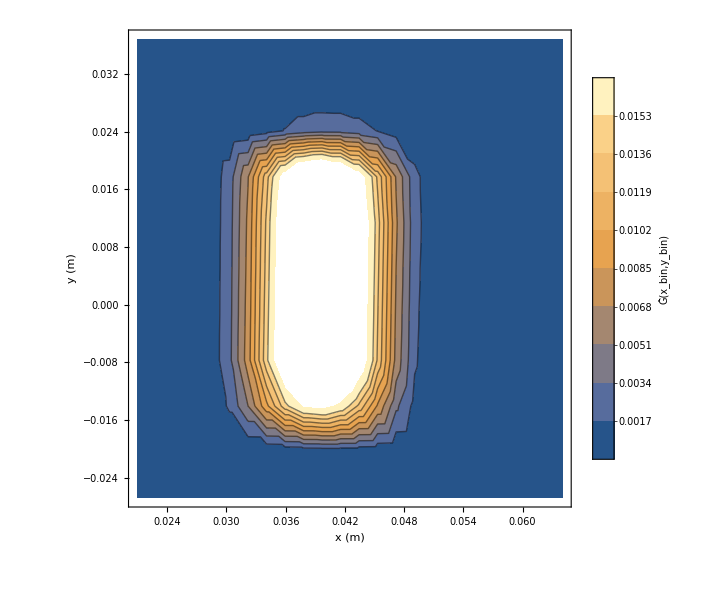

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1060/"];
```

```mathematica
dYAShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYAShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYAShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYAShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1040[[All,2]]/Total[dYAShiftSpectruma1040[[All,2]]]}]];
dYAShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1045[[All,2]]/Total[dYAShiftSpectruma1045[[All,2]]]}]];
dYAShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}]];
dYAShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1060[[All,2]]/Total[dYAShiftSpectruma1060[[All,2]]]}]];
dYAShiftSpectruma1030Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1030[[All,2]]/Total[dYAShiftSpectruma1030[[All,2]]]}]];
dYAShiftSpectruma1035Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1035[[All,2]]/Total[dYAShiftSpectruma1035[[All,2]]]}]];
dYAShiftSpectruma1020Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1020[[All,2]]/Total[dYAShiftSpectruma1020[[All,2]]]}]];
```

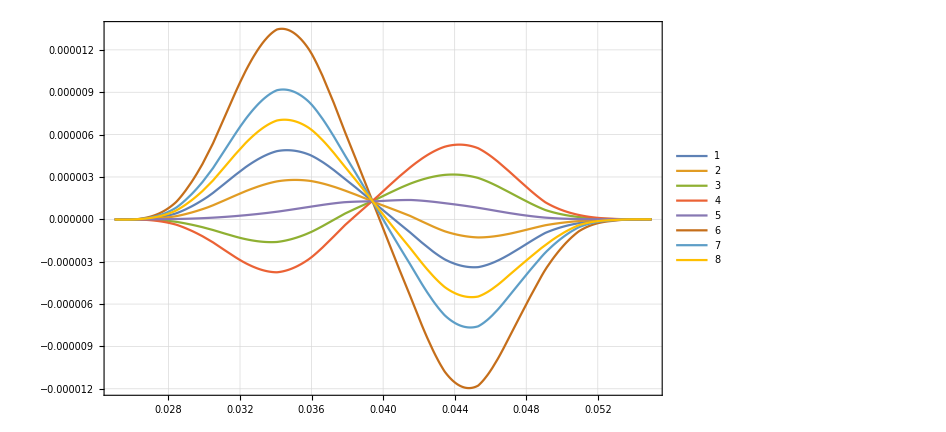

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYAShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma0Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1020Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1030Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1035Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
YAShiftDataList={dYAShiftSpectruma1020[[All,2]]/Total[dYAShiftSpectruma1020[[All,2]]],dYAShiftSpectruma1030[[All,2]]/Total[dYAShiftSpectruma1030[[All,2]]],dYAShiftSpectruma1035[[All,2]]/Total[dYAShiftSpectruma1035[[All,2]]],dYAShiftSpectruma1040[[All,2]]/Total[dYAShiftSpectruma1040[[All,2]]],dYAShiftSpectruma1045[[All,2]]/Total[dYAShiftSpectruma1045[[All,2]]],dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]],dYAShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]],dYAShiftSpectruma1060[[All,2]]/Total[dYAShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.102,-0.103,-0.1035,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

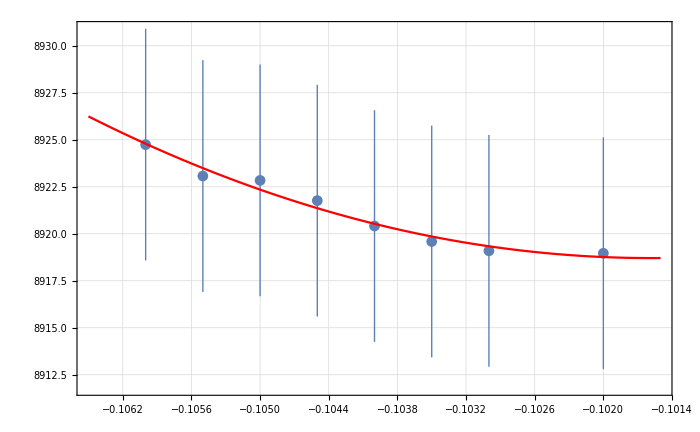
{{{8.91896×10^-6,8.91909×10^-6,8.91959×10^-6,8.92041×10^-6,8.92176×10^-6,8.92284×10^-6,8.92307×10^-6,8.92474×10^-6},{6.16488×10^-9,6.16384×10^-9,6.16347×10^-9,6.16323×10^-9,6.16324×10^-9,6.16321×10^-9,6.16349×10^-9,6.1637×10^-9}},a0 =  | -0.101581
FittedModel[8.91871×10^-6+0.000311423 (0.101581+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101581 | 0.0115715 | -8.77857 | 0.000318144
scale | 0.000311423 | 0.00142201 | 0.219001 | 0.835308
yoffset | 8.91871×10^-6 | 8.1098×10^-9 | 1099.74 | 1.17989×10^-14 | 
 | DF | SS | MS
Model | 3 | 1.676×10^7 | 5.58666×10^6
Error | 5 | 0.0200687 | 0.00401374
Uncorrected Total | 8 | 1.676×10^7 | 
Corrected Total | 7 | 0.83176 |  | ,-Graphics-}

```mathematica
YAShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],YAShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

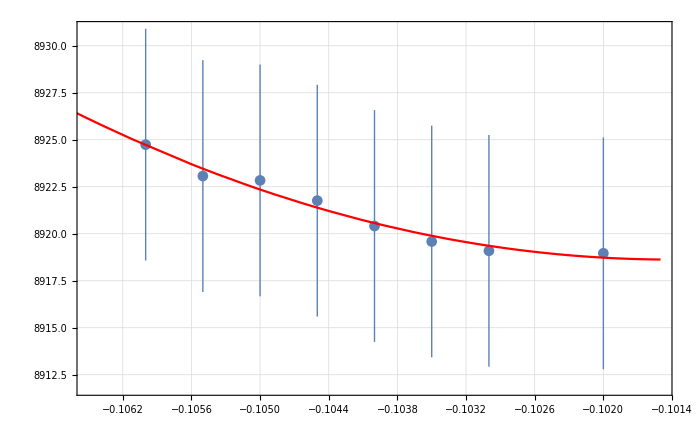
{{{8.91896×10^-6,8.91909×10^-6,8.91959×10^-6,8.92041×10^-6,8.92176×10^-6,8.92284×10^-6,8.92307×10^-6,8.92474×10^-6},{6.16488×10^-9,6.16384×10^-9,6.16347×10^-9,6.16323×10^-9,6.16324×10^-9,6.16321×10^-9,6.16349×10^-9,6.1637×10^-9}},a0 =  | -0.101406
FittedModel[8.91863×10^-6+0.000288483 (0.101406+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101406 | 0.0133294 | -7.60771 | 0.000623477
scale | 0.000288483 | 0.00142201 | 0.20287 | 0.847234
yoffset | 8.91863×10^-6 | 9.29081×10^-9 | 959.94 | 2.32851×10^-14 | 
 | DF | SS | MS
Model | 3 | 1.676×10^7 | 5.58666×10^6
Error | 5 | 0.0202751 | 0.00405502
Uncorrected Total | 8 | 1.676×10^7 | 
Corrected Total | 7 | 0.83176 |  | ,-Graphics-}

```mathematica
YAShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],YAShiftDataList,bList, 4]
```

```mathematica
((-0.10158085291422538+0.105)/-0.105)/(0.00025)
```

-130.253

```mathematica
((-0.10140601633241499+0.105)/-0.105)/(0.00025)
```

-136.914

```mathematica
-130.25322231522367*0.0001
```

-0.0130253

# dXAShift2D, k=1.62

### a=-0.105

#### a=-0.105(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1050/"];
```

```mathematica
dXAShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_179-264.txt}

```mathematica
dXAShiftSpectruma0=Flatten[Table[Import[dXAShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1050m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1050m15=Flatten[Table[Import[dXAShiftSubFileNamesa1050m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_5/"];
```

```mathematica
dXAShiftSubFileNamesa1050p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_179-264.txt}

```mathematica
dXAShiftSpectruma1050p5=Flatten[Table[Import[dXAShiftSubFileNamesa1050p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1050m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1050m5=Flatten[Table[Import[dXAShiftSubFileNamesa1050m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_15/"];
```

```mathematica
dXAShiftSubFileNamesa1050p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_179-264.txt}

```mathematica
dXAShiftSpectruma1050p15=Flatten[Table[Import[dXAShiftSubFileNamesa1050p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.104

#### a=-0.104(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1040/"];
```

```mathematica
dXAShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_179-264.txt}

```mathematica
dXAShiftSpectruma1040=Flatten[Table[Import[dXAShiftSubFileNamesa1040[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1040m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1040m15=Flatten[Table[Import[dXAShiftSubFileNamesa1040m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1040m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1040m5=Flatten[Table[Import[dXAShiftSubFileNamesa1040m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_5/"];
```

```mathematica
dXAShiftSubFileNamesa1040p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_179-264.txt}

```mathematica
dXAShiftSpectruma1040p5=Flatten[Table[Import[dXAShiftSubFileNamesa1040p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_15/"];
```

```mathematica
dXAShiftSubFileNamesa1040p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_179-264.txt}

```mathematica
dXAShiftSpectruma1040p15=Flatten[Table[Import[dXAShiftSubFileNamesa1040p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.1045

#### a=-0.1045(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1045/"];
```

```mathematica
dXAShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_179-264.txt}

```mathematica
dXAShiftSpectruma1045=Flatten[Table[Import[dXAShiftSubFileNamesa1045[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1045m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1045m15=Flatten[Table[Import[dXAShiftSubFileNamesa1045m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_5/"];
```

```mathematica
dXAShiftSubFileNamesa1045p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_179-264.txt}

```mathematica
dXAShiftSpectruma1045p5=Flatten[Table[Import[dXAShiftSubFileNamesa1045p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1045m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1045m5=Flatten[Table[Import[dXAShiftSubFileNamesa1045m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_15/"];
```

```mathematica
dXAShiftSubFileNamesa1045p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_179-264.txt}

```mathematica
dXAShiftSpectruma1045p15=Flatten[Table[Import[dXAShiftSubFileNamesa1045p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.1055

#### a=-0.1055(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1055/"];
```

```mathematica
dXAShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_179-264.txt}

```mathematica
dXAShiftSpectruma1055=Flatten[Table[Import[dXAShiftSubFileNamesa1055[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1055m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1055m15=Flatten[Table[Import[dXAShiftSubFileNamesa1055m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1055m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1055m5=Flatten[Table[Import[dXAShiftSubFileNamesa1055m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_5/"];
```

```mathematica
dXAShiftSubFileNamesa1055p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_179-264.txt}

```mathematica
dXAShiftSpectruma1055p5=Flatten[Table[Import[dXAShiftSubFileNamesa1055p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_15/"];
```

```mathematica
dXAShiftSubFileNamesa1055p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_179-264.txt}

```mathematica
dXAShiftSpectruma1055p15=Flatten[Table[Import[dXAShiftSubFileNamesa1055p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.1060

#### a=-0.1060(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1060/"];
```

```mathematica
dXAShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_179-264.txt}

```mathematica
dXAShiftSpectruma1060=Flatten[Table[Import[dXAShiftSubFileNamesa1060[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1060m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1060m15=Flatten[Table[Import[dXAShiftSubFileNamesa1060m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_5/"];
```

```mathematica
dXAShiftSubFileNamesa1060p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_179-264.txt}

```mathematica
dXAShiftSpectruma1060p5=Flatten[Table[Import[dXAShiftSubFileNamesa1060p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1060m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1060m5=Flatten[Table[Import[dXAShiftSubFileNamesa1060m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060m5]}],1];
```

```mathematica
dXAShiftSpectruma1050m5[[All,2]]//Length
```

264

```mathematica
dXAShiftSpectruma1060m5[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_15/"];
```

```mathematica
?FileSorter
```

```mathematica
dXAShiftSubFileNamesa1060p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_179-264.txt}

```mathematica
dXAShiftSpectruma1060p15=Flatten[Table[Import[dXAShiftSubFileNamesa1060p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXAShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXAShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]]}]];
dXAShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]]}]];
dXAShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]}]];
dXAShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0250006,0.23} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

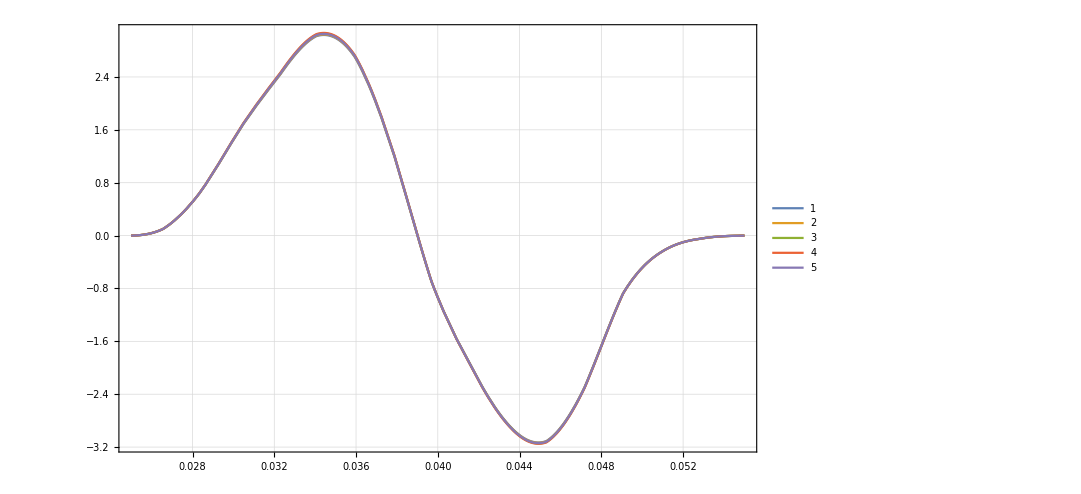

```mathematica
Plot[{
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1040Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1045Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1055Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1060Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma0Inter[x,0.23]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList,XAShiftInvest]
```

```mathematica
XAShiftDataList={dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList2D={{-.104 ,-.1045,-.105,-.1055,-0.1060},{-0.00015,-0.00005,0.00005,0.00015,0.00025}}
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015,0.00025}}

```mathematica
bList2D2={{-.104 ,-.1045,-.105,-.1055,-0.1060},{-0.00015,-0.00005,0.00005,0.00015}}
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015}}

```mathematica
XAShiftDataList2D2={{dXAShiftSpectruma1040m15[[All,2]]/Total[dXAShiftSpectruma1040m15[[All,2]]],dXAShiftSpectruma1040m5[[All,2]]/Total[dXAShiftSpectruma1040m5[[All,2]]],dXAShiftSpectruma1040p5[[All,2]]/Total[dXAShiftSpectruma1040p5[[All,2]]],dXAShiftSpectruma1040p15[[All,2]]/Total[dXAShiftSpectruma1040p15[[All,2]]]},{dXAShiftSpectruma1045m15[[All,2]]/Total[dXAShiftSpectruma1045m15[[All,2]]],dXAShiftSpectruma1045m5[[All,2]]/Total[dXAShiftSpectruma1045m5[[All,2]]],dXAShiftSpectruma1045p5[[All,2]]/Total[dXAShiftSpectruma1045p5[[All,2]]],dXAShiftSpectruma1045p15[[All,2]]/Total[dXAShiftSpectruma1045p15[[All,2]]]},{dXAShiftSpectruma1050m15[[All,2]]/Total[dXAShiftSpectruma1050m15[[All,2]]],dXAShiftSpectruma1050m5[[All,2]]/Total[dXAShiftSpectruma1050m5[[All,2]]],dXAShiftSpectruma1050p5[[All,2]]/Total[dXAShiftSpectruma1050p5[[All,2]]],dXAShiftSpectruma1050p15[[All,2]]/Total[dXAShiftSpectruma1050p15[[All,2]]]},{dXAShiftSpectruma1055m15[[All,2]]/Total[dXAShiftSpectruma1055m15[[All,2]]],dXAShiftSpectruma1055m5[[All,2]]/Total[dXAShiftSpectruma1055m5[[All,2]]],dXAShiftSpectruma1055p5[[All,2]]/Total[dXAShiftSpectruma1055p5[[All,2]]],dXAShiftSpectruma1055p15[[All,2]]/Total[dXAShiftSpectruma1055p15[[All,2]]]},{dXAShiftSpectruma1060m15[[All,2]]/Total[dXAShiftSpectruma1060m15[[All,2]]],dXAShiftSpectruma1060m5[[All,2]]/Total[dXAShiftSpectruma1060m5[[All,2]]],dXAShiftSpectruma1060p5[[All,2]]/Total[dXAShiftSpectruma1060p5[[All,2]]],dXAShiftSpectruma1060p15[[All,2]]/Total[dXAShiftSpectruma1060p15[[All,2]]]}
};
```

```mathematica
XAShiftDataList2D={{dXAShiftSpectruma1040m15[[All,2]]/Total[dXAShiftSpectruma1040m15[[All,2]]],dXAShiftSpectruma1040m5[[All,2]]/Total[dXAShiftSpectruma1040m5[[All,2]]],dXAShiftSpectruma1040p5[[All,2]]/Total[dXAShiftSpectruma1040p5[[All,2]]],dXAShiftSpectruma1040p15[[All,2]]/Total[dXAShiftSpectruma1040p15[[All,2]]],dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]]},{dXAShiftSpectruma1045m15[[All,2]]/Total[dXAShiftSpectruma1045m15[[All,2]]],dXAShiftSpectruma1045m5[[All,2]]/Total[dXAShiftSpectruma1045m5[[All,2]]],dXAShiftSpectruma1045p5[[All,2]]/Total[dXAShiftSpectruma1045p5[[All,2]]],dXAShiftSpectruma1045p15[[All,2]]/Total[dXAShiftSpectruma1045p15[[All,2]]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]]},{dXAShiftSpectruma1050m15[[All,2]]/Total[dXAShiftSpectruma1050m15[[All,2]]],dXAShiftSpectruma1050m5[[All,2]]/Total[dXAShiftSpectruma1050m5[[All,2]]],dXAShiftSpectruma1050p5[[All,2]]/Total[dXAShiftSpectruma1050p5[[All,2]]],dXAShiftSpectruma1050p15[[All,2]]/Total[dXAShiftSpectruma1050p15[[All,2]]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]]},{dXAShiftSpectruma1055m15[[All,2]]/Total[dXAShiftSpectruma1055m15[[All,2]]],dXAShiftSpectruma1055m5[[All,2]]/Total[dXAShiftSpectruma1055m5[[All,2]]],dXAShiftSpectruma1055p5[[All,2]]/Total[dXAShiftSpectruma1055p5[[All,2]]],dXAShiftSpectruma1055p15[[All,2]]/Total[dXAShiftSpectruma1055p15[[All,2]]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]},{dXAShiftSpectruma1060m15[[All,2]]/Total[dXAShiftSpectruma1060m15[[All,2]]],dXAShiftSpectruma1060m5[[All,2]]/Total[dXAShiftSpectruma1060m5[[All,2]]],dXAShiftSpectruma1060p5[[All,2]]/Total[dXAShiftSpectruma1060p5[[All,2]]],dXAShiftSpectruma1060p15[[All,2]]/Total[dXAShiftSpectruma1060p15[[All,2]]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]}
};
```

```mathematica
RefNorm=RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]];
```

```mathematica
Length[RefNorm]
```

264

```mathematica
Dimensions[XAShiftDataList2D]
```

{5,5,264}

```mathematica
Length[XAShiftDataList2D[[1,1]]]
```

264

```mathematica
Length[bList2D[[2]]]
```

5

```mathematica
Table[XAShiftDataList2D⟦b,par⟧//Length,{b,Length[bList2D[[1]]]},{par,Length[bList2D[[2]]]}]
```

{{264,264,264,264,264},{264,264,264,264,264},{264,264,264,264,264},{264,264,264,264,264},{264,264,264,264,264}}

```mathematica
Chi2List2D2=Table[Total[(RefNorm-XAShiftDataList2D2⟦b,par⟧)^2],{b,Length[bList2D2[[1]]]},{par,Length[bList2D2[[2]]]}];
```

```mathematica
Chi2List2D=Table[Total[(RefNorm-XAShiftDataList2D⟦b,par⟧)^2],{b,Length[bList2D[[1]]]},{par,Length[bList2D[[2]]]}];
```

```mathematica
Chi2List2D
```

{{0.0000126211,1.43994×10^-6,1.33175×10^-6,0.0000122879,0.0000343155},{0.0000125412,1.41195×10^-6,1.3578×10^-6,0.0000123668,0.000034447},{0.0000124614,1.38544×10^-6,1.38414×10^-6,0.0000124466,0.0000345783},{0.000012382,1.3591×10^-6,1.41072×10^-6,0.000012526,0.0000347027},{0.0000123005,1.33293×10^-6,1.43759×10^-6,0.0000126057,0.0000348354}}

```mathematica
plotChi2List2D=Table[{bList2D[[1,b]],bList2D[[2,par]],Total[(RefNorm-XAShiftDataList2D⟦b,par⟧)^2]},{b,Length[bList2D[[1]]]},{par,Length[bList2D[[2]]]}];
```

```mathematica
plotChi2List2D2=Table[{bList2D2[[1,b]],bList2D2[[2,par]],Total[(RefNorm-XAShiftDataList2D2⟦b,par⟧)^2]},{b,Length[bList2D2[[1]]]},{par,Length[bList2D2[[2]]]}];
```

```mathematica
dChi2List=Table[10^-4 √Total[(RefNorm-XAShiftDataList2D⟦b,para⟧)^2 (RefNorm^2+XAShiftDataList2D⟦b,para⟧^2)],{b,Length[bList2D[[1]]]},{para,Length[bList2D[[2]]]}];
```

```mathematica
dChi2List2=Table[10^-4 √Total[(RefNorm-XAShiftDataList2D2⟦b,para⟧)^2 (RefNorm^2+XAShiftDataList2D2⟦b,para⟧^2)],{b,Length[bList2D2[[1]]]},{para,Length[bList2D2[[2]]]}];
```

```mathematica
fitfunc[a_,a0_,par_,par0_,ascale_,pscale_,offset_]:=offset+(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
fitfunc2[x_,x0_,y_,y0_,f_,g_,k_]:=k+f*(x-x0)^2+g*(y-y0)^2
```

```mathematica
0<-0.105<0
```

False

```mathematica
bList2D2
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015}}

```mathematica
Min[bList2D2[[2]]]
```

-0.00015

```mathematica
fit2=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,Min[bList2D2[[2]]]<par0<Max[bList2D2[[2]]],-10000<ascale<10000,-1<pscale<1,0.<offset≤Min[Chi2List2D2]},{{a00,-0.105},{offset,Min[Chi2List2D2]},{ascale,5},{pscale,5/10^4},{par0,Min[bList2D2[[2]]]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[2.69844×10^-10+0.0000666051 (0.105077+a)^2+553.45 (-2.83471×10^-8+par)^2]

```mathematica
Sqrt[1/1.4912926423138863*^-6]
```

818.877

```mathematica
fit=NonlinearModelFit[Flatten[plotChi2List2D,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[bList2D[[2]]]<par0<Max[bList2D[[2]]],-1000<ascale<1000,-1<pscale<1,-1000.<offset≤Min[Chi2List2D]},{{a00,-0.105},{par0,Min[bList2D[[2]]]},{ascale,5},{pscale,5/10^4},{offset,Min[Chi2List2D]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[-1.17551×10^-7+7.78385×10^-6 (0.105019+a)^2+574.865 (-8.74238×10^-7+par)^2]

```mathematica
fit2["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.105077 | 0.00899365 | -11.6835 | 6.22366×10^-9
offset | 2.69844×10^-10 | 1.41277×10^-9 | 0.191003 | 0.851084
ascale | 122.531 | 1802.41 | 0.0679819 | 0.946698
pscale | 0.042507 | 5.24864×10^-6 | 8098.67 | 3.17057×10^-51
par0 | 2.83471×10^-8 | 1.10443×10^-8 | 2.56666 | 0.0214762

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.105019 | 0.0738099 | -1.42282 | 0.170198
par0 | 8.74238×10^-7 | 1.01256×10^-8 | 86.3392 | 3.3192×10^-27
ascale | -358.429 | 7.63287×10^-9 | -4.69586×10^10 | 6.63748×10^-202
pscale | 0.0417078 | 3.25×10^-6 | 12833.2 | 1.22921×10^-70
offset | -1.17551×10^-7 | 9.44779×10^-10 | -124.422 | 2.25439×10^-30

```mathematica
bList2D2
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015}}

```mathematica
bList2D
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015,0.00025}}

```mathematica
Plot3D[0.+0.25373704917327977 (0.10504249683354637+a)^2+544.5543878217807 (4.1049735352606163*^-7+par)^2,{a,-0.106,-0.104},{par,-0.00015,0.00025}]
```

-Graphics3D-

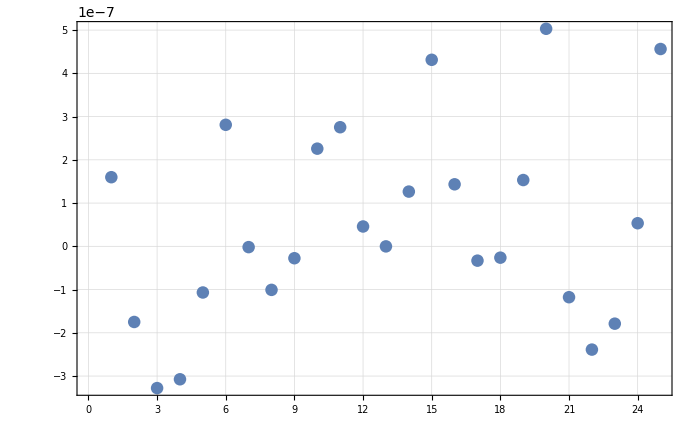

```mathematica
ListPlot[fit["FitResiduals"]]
```

```mathematica
(-0.10507706564034543+0.105)/-0.105
```

0.000733958

```mathematica
0.0007339584794802916/0.00025
```

2.93583

```mathematica
(-0.1050185201015299+0.105)/-0.105/0.00025
```

0.705528

```mathematica
2.9358339179211663*0.0001
```

0.000293583

```mathematica
0.005508159700042576/0.00025
```

22.0326

```mathematica
12.9*0.1
```

1.29

```mathematica
0.1*1.6189269922428111
```

0.161893

```mathematica
57*0.1
```

5.7

```mathematica
0.16*35
```

5.6

```mathematica
5.7/0.16
```

35.625

```mathematica
0.16
```

```mathematica
((-0.10504249683354637+0.105)/-0.105)/0.00025
```

1.61893

```mathematica
((-0.10617422685299294+0.105)/-0.105)/0.00025
```

44.7325

```mathematica
44*.1
```

4.4

```mathematica
0.00040473174806070276/0.00025
```

1.61893

```mathematica
0.00040473174806070276/0.00025*0.0001
```

0.000161893

```mathematica
a00/.fit["BestFitParameters"]
```

-0.105042

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.105042 | 2.28751×10^-6 | -45920. | 1.03817×10^-81
par0 | -4.10497×10^-7 | 1.07627×10^-8 | -38.1409 | 3.7314×10^-20
ascale | -1.98522 | 0.00759741 | -261.302 | 8.17032×10^-37
pscale | 0.0428528 | 3.52509×10^-6 | 12156.5 | 3.63175×10^-70
offset | 0. | 1.35196×10^-9 | 0. | 1.

```mathematica
Show[ListPlot3D[Flatten[plotChi2List2D,1],PlotStyle->Blue],Plot3D[fit[a,par],{a,-0.104,-.106},{par,-0.00015,0.00025},PlotStyle->Red]]
```

-Graphics3D-

```mathematica
XAShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],XAShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.0000343155,0.000034447,0.0000345783,0.0000347027,0.0000348354},{1.36128×10^-8,1.3639×10^-8,1.36652×10^-8,1.36875×10^-8,1.3714×10^-8}},a0 =  | -0.1035
FittedModel[0.0000343155+0.0902549 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000247235 | -418.63 | 5.70605×10^-6
scale | 0.0902549 | 0.0146073 | 6.17876 | 0.0252075
yoffset | 0.0000343155 | 2.92413×10^-8 | 1173.53 | 7.26125×10^-7 | 
 | DF | SS | MS
Model | 3 | 3.20164×10^7 | 1.06721×10^7
Error | 2 | 45.011 | 22.5055
Uncorrected Total | 5 | 3.20165×10^7 | 
Corrected Total | 4 | 899.025 |  | ,-Graphics-}

```mathematica
z=
```

```mathematica
((XAShiftInvest2[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-136.048

```mathematica
-136.04810567554844*0.00025
```

-0.034012

```mathematica
((XAShiftInvest[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-57.1429

```mathematica
0.0003+0.0003
```

0.0006

```mathematica
0.0006/6
```

0.0001

```mathematica
Table[i,{i,-0.0003,0.0003,0.0006/4}]
```

{-0.0003,-0.00015,0.,0.00015,0.0003}

# dYRxBShift, k=0.000029

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1050/"];
```

```mathematica
dYrxbShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_179-264.txt}

```mathematica
dYrxbShiftSpectruma0=Flatten[Table[Import[dYrxbShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dYrxbShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1040/"];
```

```mathematica
dYrxbShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_179-264.txt}

```mathematica
dYrxbShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1045/"];
```

```mathematica
dYrxbShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_179-264.txt}

```mathematica
dYrxbShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1055/"];
```

```mathematica
dYrxbShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_179-264.txt}

```mathematica
dYrxbShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

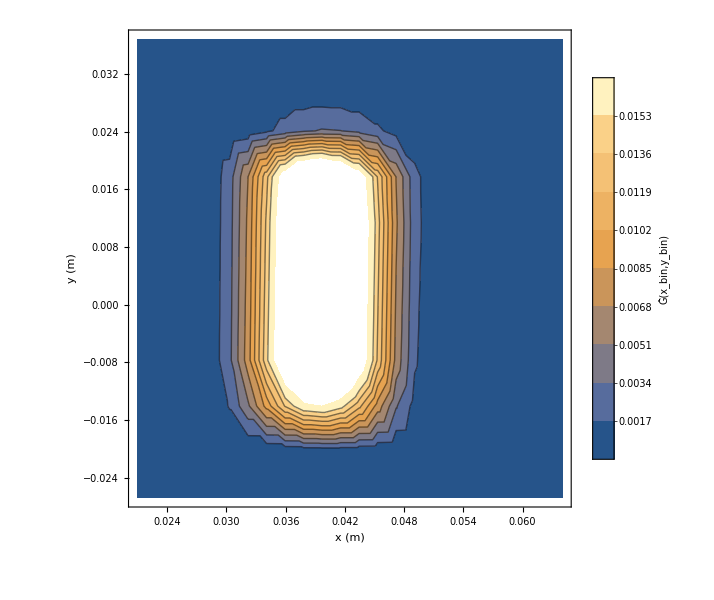

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1060/"];
```

```mathematica
dYrxbShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYrxbShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYrxbShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma0[[All,2]]/Total[dYrxbShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYrxbShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1040[[All,2]]/Total[dYrxbShiftSpectruma1040[[All,2]]]}]];
dYrxbShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1045[[All,2]]/Total[dYrxbShiftSpectruma1045[[All,2]]]}]];
dYrxbShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1055[[All,2]]/Total[dYrxbShiftSpectruma1055[[All,2]]]}]];
dYrxbShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1060[[All,2]]/Total[dYrxbShiftSpectruma1060[[All,2]]]}]];
```

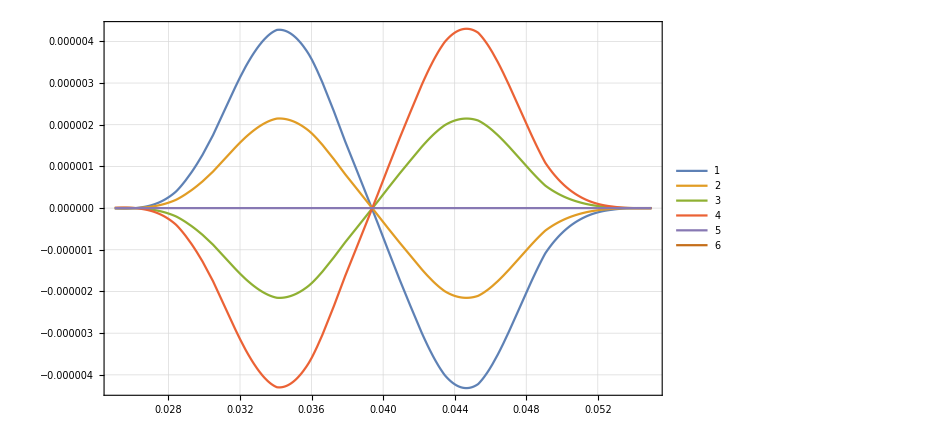

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYrxbShiftDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dYrxbShiftDataList={dYrxbShiftSpectruma1040[[All,2]]/Total[dYrxbShiftSpectruma1040[[All,2]]],dYrxbShiftSpectruma1045[[All,2]]/Total[dYrxbShiftSpectruma1045[[All,2]]],dYrxbShiftSpectruma0[[All,2]]/Total[dYrxbShiftSpectruma0[[All,2]]],dYrxbShiftSpectruma1055[[All,2]]/Total[dYrxbShiftSpectruma1055[[All,2]]],dYrxbShiftSpectruma1060[[All,2]]/Total[dYrxbShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
RefNorm=Total[RefSpectrum[[All,2]]];
```

```mathematica
RefNormed=RefSpectrum[[All,2]]/RefNorm;
```

```mathematica
Sigma=(If[#1==0,10000,10^-4 #1]&)/@RefNormed;
```

```mathematica
TransferDataListNormed=(#1/Total[#1]&)/@dYrxbShiftDataList;
```

```mathematica
Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[bList]}];dChi2List=Table[10^-4 √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[bList]}];errorplotdata=Transpose[{bList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.106<b0<-0.104&&-100<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[5.68265×10^-34+0.000511307 (0.105+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 9.90204×10^-37 | -1.06039×10^35 | 0.
scale | 0.000511307 | 8.34241×10^-45 | 6.12901×10^40 | 0.
yoffset | 5.68265×10^-34 | 1.11487×10^-22 | 5.09714×10^-12 | 1.

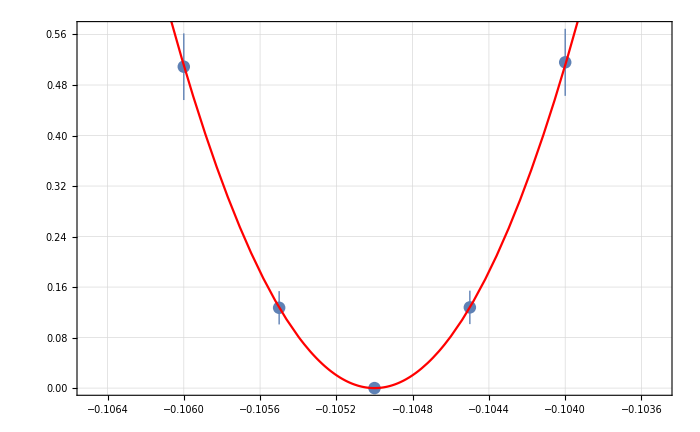

```mathematica
Show[ListPlot[errorplotdata,PlotRange->{{-0.1065,-0.1035},Automatic}],Plot[10^9 fitresult[b],{b,-0.1065,-0.1035},PlotStyle->Red]]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

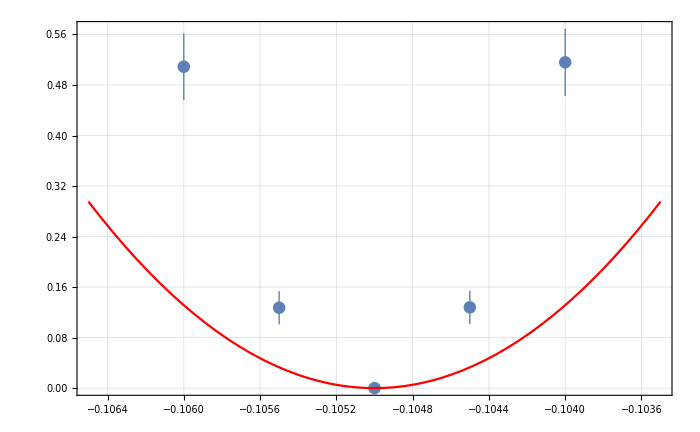
{{{5.1594×10^-10,1.27824×10^-10,1.0522×10^-33,1.27214×10^-10,5.08995×10^-10},{5.30987×10^-11,2.64719×10^-11,1.11487×10^-22,2.63741×10^-11,5.27829×10^-11}},a0 =  | -0.105
FittedModel[1.37355×10^-34+0.000131292 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 4.08459×10^-36 | -2.57064×10^34 | 0.
scale | 0.000131292 | 2.18009×10^-42 | 6.02231×10^37 | 0.
yoffset | 1.37355×10^-34 | 1.11487×10^-22 | 1.23203×10^-12 | 1. | 
 | DF | SS | MS
Model | 3 | 104.616 | 34.8719
Error | 2 | 129.37 | 64.6848
Uncorrected Total | 5 | 233.985 | 
Corrected Total | 4 | 233.985 |  | ,-Graphics-}

```mathematica
dYrxbShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dYrxbShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

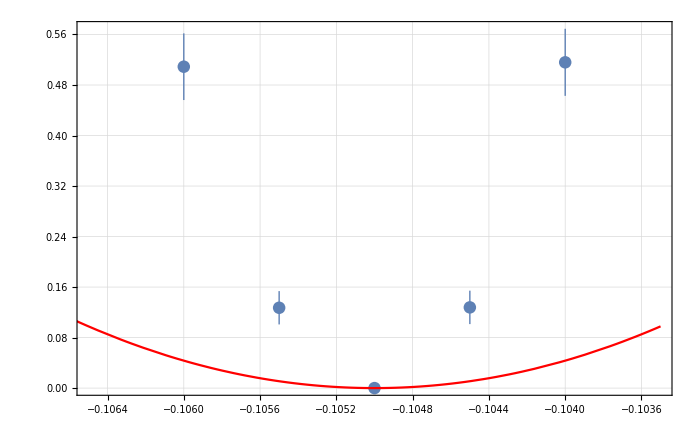
{{{5.1594×10^-10,1.27824×10^-10,1.0522×10^-33,1.27214×10^-10,5.08995×10^-10},{5.30987×10^-11,2.64719×10^-11,1.11487×10^-22,2.63741×10^-11,5.27829×10^-11}},a0 =  | -0.105
FittedModel[1.0522×10^-33+0.000043454 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 7.42653×10^-36 | -1.41385×10^34 | 0.
scale | 0.000043454 | 6.53648×10^-41 | 6.64791×10^35 | 0.
yoffset | 1.0522×10^-33 | 1.11487×10^-22 | 9.4379×10^-12 | 1. | 
 | DF | SS | MS
Model | 3 | 37.98 | 12.66
Error | 2 | 196.005 | 98.0027
Uncorrected Total | 5 | 233.985 | 
Corrected Total | 4 | 233.985 |  | ,-Graphics-}

```mathematica
dYrxbShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dYrxbShiftDataList,bList, 4]
```

```mathematica
0.00025
```

```mathematica
((-0.10500000076570207+0.105)/-0.105)/(0.00025)
```

0.0000291696

```mathematica
((-0.10500000000865034+0.105)/-0.105)/(0.00025)
```

3.29537×10^-7

# dNk2x, k=11.22

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1050/"];
```

```mathematica
dNk2xSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_179-264.txt}

```mathematica
dNk2xSpectruma0=Flatten[Table[Import[dNk2xSubFileNamesa0[[i]],"Table"],{i,1,Length[dNk2xSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1040/"];
```

```mathematica
dNk2xSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_179-264.txt}

```mathematica
dNk2xSpectruma1040=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1045/"];
```

```mathematica
dNk2xSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_179-264.txt}

```mathematica
dNk2xSpectruma1045=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1055/"];
```

```mathematica
dNk2xSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_179-264.txt}

```mathematica
dNk2xSpectruma1055=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

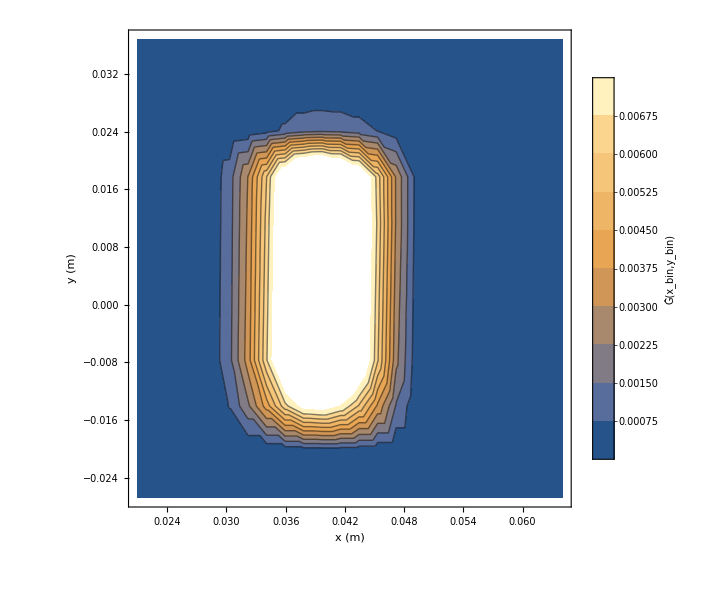

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1060/"];
```

```mathematica
dNk2xSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dNk2xSpectruma1060=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dNk2xSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma0[[All,2]]/Total[dNk2xSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dNk2xSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1040[[All,2]]/Total[dNk2xSpectruma1040[[All,2]]]}]];
dNk2xSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1045[[All,2]]/Total[dNk2xSpectruma1045[[All,2]]]}]];
dNk2xSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1055[[All,2]]/Total[dNk2xSpectruma1055[[All,2]]]}]];
dNk2xSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1060[[All,2]]/Total[dNk2xSpectruma1060[[All,2]]]}]];
```

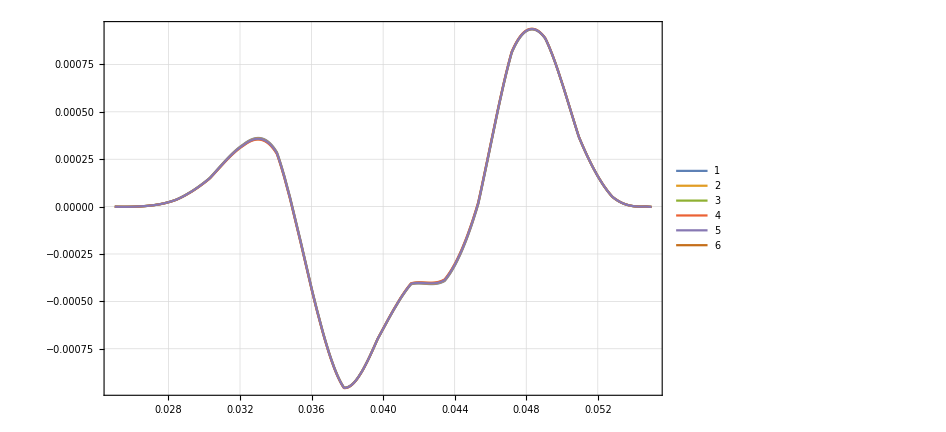

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dNk2xSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dNk2xDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dNk2xDataList={dNk2xSpectruma1040[[All,2]]/Total[dNk2xSpectruma1040[[All,2]]],dNk2xSpectruma1045[[All,2]]/Total[dNk2xSpectruma1045[[All,2]]],dNk2xSpectruma0[[All,2]]/Total[dNk2xSpectruma0[[All,2]]],dNk2xSpectruma1055[[All,2]]/Total[dNk2xSpectruma1055[[All,2]]],dNk2xSpectruma1060[[All,2]]/Total[dNk2xSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

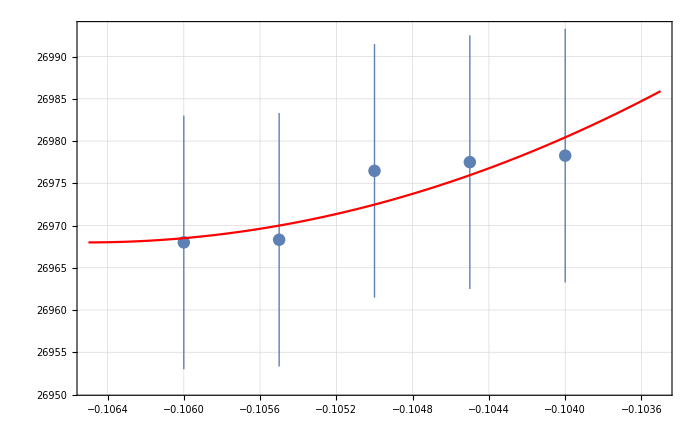
{{{0.0000269783,0.0000269775,0.0000269765,0.0000269683,0.000026968},{1.50142×10^-8,1.50119×10^-8,1.50109×10^-8,1.50085×10^-8,1.50077×10^-8}},a0 =  | -0.1065
FittedModel[0.000026968+0.00198904 (0.1065+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1065 | 0.0123342 | -8.6345 | 0.013149
scale | 0.00198904 | 0.0160472 | 0.123949 | 0.91269
yoffset | 0.000026968 | 3.21907×10^-8 | 837.759 | 1.42482×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.61455×10^7 | 5.38185×10^6
Error | 2 | 0.115597 | 0.0577983
Uncorrected Total | 5 | 1.61455×10^7 | 
Corrected Total | 4 | 0.463708 |  | ,-Graphics-}

```mathematica
dNk2xInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dNk2xDataList,bList, 4]
```

```mathematica
(-0.1065+0.105)/-0.105/0.005
```

2.85714

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

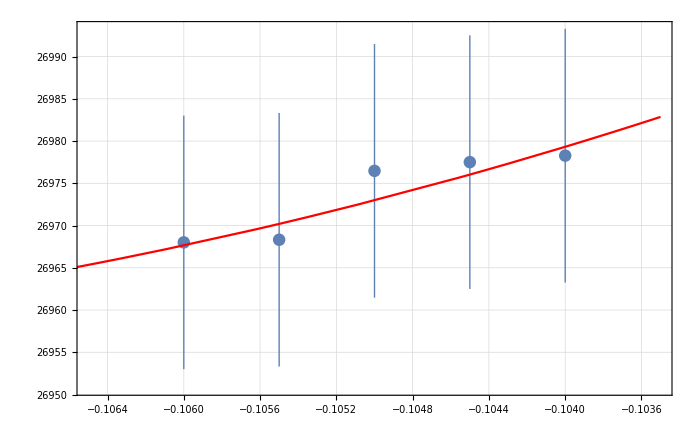
{{{0.0000269783,0.0000269775,0.0000269765,0.0000269683,0.000026968},{1.50142×10^-8,1.50119×10^-8,1.50109×10^-8,1.50085×10^-8,1.50077×10^-8}},a0 =  | -0.110893
FittedModel[0.0000269558+0.000495243 (0.110893+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.110893 | 0.191195 | -0.58 | 0.62055
scale | 0.000495243 | 0.0160472 | 0.0308616 | 0.978183
yoffset | 0.0000269558 | 5.5217×10^-7 | 48.8179 | 0.000419343 | 
 | DF | SS | MS
Model | 3 | 1.61455×10^7 | 5.38185×10^6
Error | 2 | 0.0845484 | 0.0422742
Uncorrected Total | 5 | 1.61455×10^7 | 
Corrected Total | 4 | 0.463708 |  | ,-Graphics-}

```mathematica
dNk2xInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dNk2xDataList,bList, 4]
```

```mathematica
0.00025
```

```mathematica
((-0.11089324097917469+0.105)/-0.105)/(0.005)
```

11.2252

```mathematica
0.2/1000
```

0.0002

# dXAoff, k=177.55/71.43

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1050/"];
```

```mathematica
dXAoffSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_179-264.txt}

```mathematica
dXAoffSpectruma0=Flatten[Table[Import[dXAoffSubFileNamesa0[[i]],"Table"],{i,1,Length[dXAoffSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1040/"];
```

```mathematica
dXAoffSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_179-264.txt}

```mathematica
dXAoffSpectruma1040=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1045/"];
```

```mathematica
dXAoffSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_179-264.txt}

```mathematica
dXAoffSpectruma1045=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1055/"];
```

```mathematica
dXAoffSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_179-264.txt}

```mathematica
dXAoffSpectruma1055=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

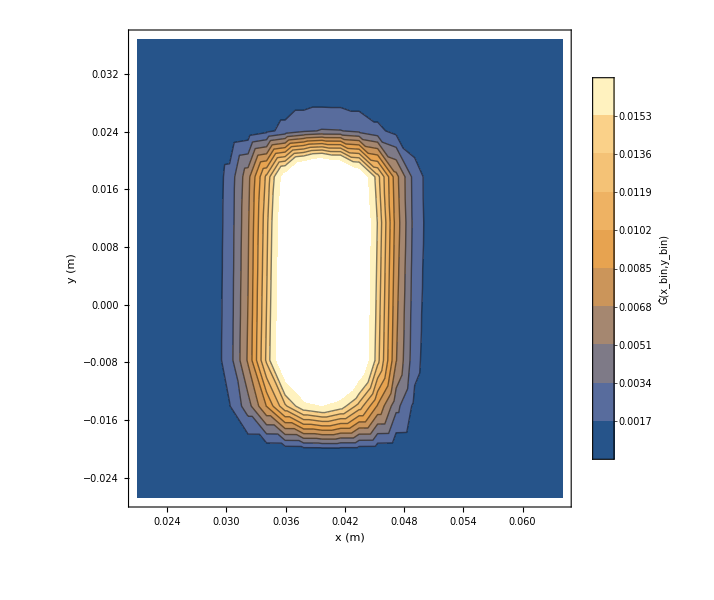

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1055[[All,2]]/Total[dXAoffSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1060/"];
```

```mathematica
dXAoffSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dXAoffSpectruma1060=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXAoffSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma0[[All,2]]/Total[dXAoffSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXAoffSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1040[[All,2]]/Total[dXAoffSpectruma1040[[All,2]]]}]];
dXAoffSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1045[[All,2]]/Total[dXAoffSpectruma1045[[All,2]]]}]];
dXAoffSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1055[[All,2]]/Total[dXAoffSpectruma1055[[All,2]]]}]];
dXAoffSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1060[[All,2]]/Total[dXAoffSpectruma1060[[All,2]]]}]];
```

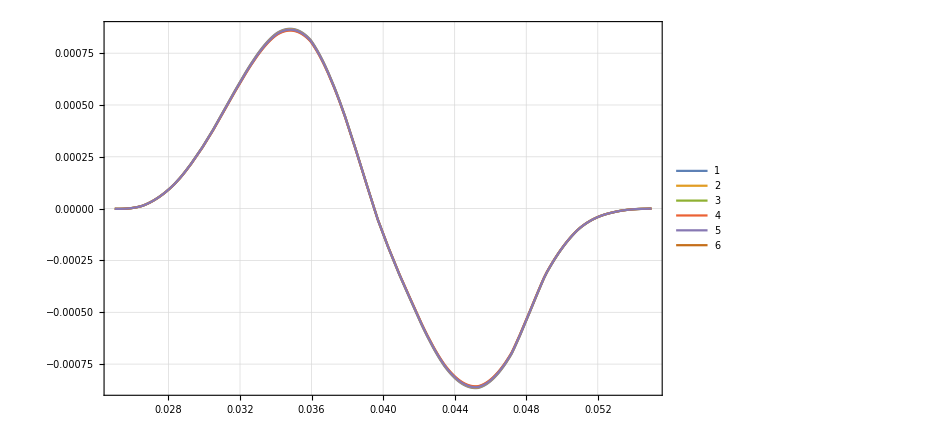

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dXAoffSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

### a=-1065

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1065/"];
```

```mathematica
dXAoffSubFileNamesa1065=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_179-264.txt}

```mathematica
dXAoffSpectruma1065=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1065,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1065[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1070

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1070/"];
```

```mathematica
dXAoffSubFileNamesa1070=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_179-264.txt}

```mathematica
dXAoffSpectruma1070=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1070,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1070[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dXAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dXAoffDataList={dXAoffSpectruma1040[[All,2]]/Total[dXAoffSpectruma1040[[All,2]]],dXAoffSpectruma1045[[All,2]]/Total[dXAoffSpectruma1045[[All,2]]],dXAoffSpectruma0[[All,2]]/Total[dXAoffSpectruma0[[All,2]]],dXAoffSpectruma1055[[All,2]]/Total[dXAoffSpectruma1055[[All,2]]],dXAoffSpectruma1060[[All,2]]/Total[dXAoffSpectruma1060[[All,2]]],dXAoffSpectruma1065[[All,2]]/Total[dXAoffSpectruma1065[[All,2]]],dXAoffSpectruma1070[[All,2]]/Total[dXAoffSpectruma1070[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060,-0.1065,-0.1070}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1065,-0.107}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

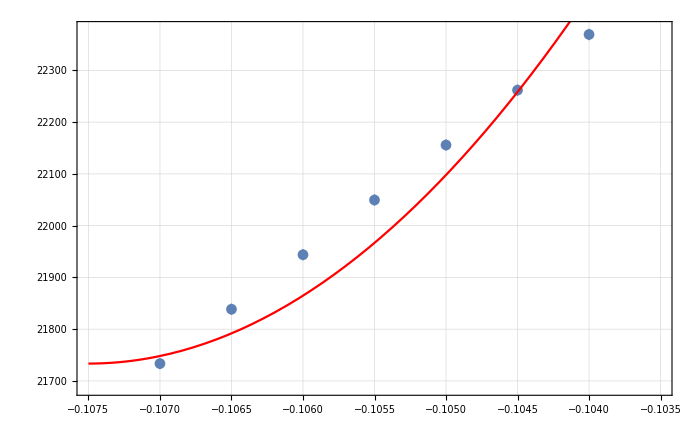
{{{0.0000223693,0.0000222618,0.0000221558,0.0000220495,0.0000219438,0.0000218385,0.0000217335},{1.09942×10^-8,1.09676×10^-8,1.09413×10^-8,1.09149×10^-8,1.08884×10^-8,1.08621×10^-8,1.08358×10^-8}},a0 =  | -0.1075
FittedModel[0.0000217335+0.0582959 (0.1075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1075 | 0.000166925 | -644. | 3.48819×10^-11
scale | 0.0582959 | 0.00476361 | 12.2378 | 0.000256009
yoffset | 0.0000217335 | 1.69321×10^-8 | 1283.57 | 2.2104×10^-12 | 
 | DF | SS | MS
Model | 3 | 2.85677×10^7 | 9.52256×10^6
Error | 4 | 209.514 | 52.3785
Uncorrected Total | 7 | 2.85679×10^7 | 
Corrected Total | 6 | 2636.97 |  | ,-Graphics-}

```mathematica
dXAoffInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dXAoffDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

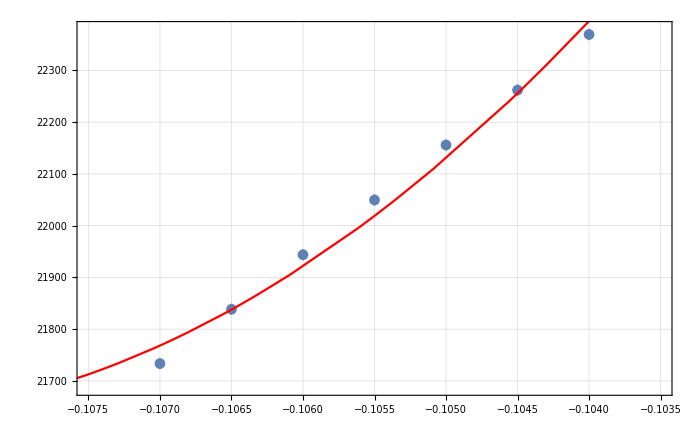
{{{0.0000223693,0.0000222618,0.0000221558,0.0000220495,0.0000219438,0.0000218385,0.0000217335},{1.09942×10^-8,1.09676×10^-8,1.09413×10^-8,1.09149×10^-8,1.08884×10^-8,1.08621×10^-8,1.08358×10^-8}},a0 =  | -0.109236
FittedModel[0.0000216285+0.0279742 (0.109236+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.109236 | 0.000639775 | -170.741 | 7.05833×10^-9
scale | 0.0279742 | 0.00476361 | 5.87247 | 0.00420002
yoffset | 0.0000216285 | 6.36072×10^-8 | 340.032 | 4.48793×10^-10 | 
 | DF | SS | MS
Model | 3 | 2.85679×10^7 | 9.52262×10^6
Error | 4 | 33.7287 | 8.43217
Uncorrected Total | 7 | 2.85679×10^7 | 
Corrected Total | 6 | 2636.97 |  | ,-Graphics-}

```mathematica
dXAoffInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dXAoffDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10872865859233186+0.105)/-0.105)/(0.0002)
```

177.555

```mathematica
((-0.10923565206790305+0.105)/-0.105)/(0.0002)
```

201.698

# dYAoff, k=37

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1050/"];
```

```mathematica
dYAoffSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_179-264.txt}

```mathematica
dYAoffSpectruma0=Flatten[Table[Import[dYAoffSubFileNamesa0[[i]],"Table"],{i,1,Length[dYAoffSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1040/"];
```

```mathematica
dYAoffSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_179-264.txt}

```mathematica
dYAoffSpectruma1040=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1045/"];
```

```mathematica
dYAoffSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_179-264.txt}

```mathematica
dYAoffSpectruma1045=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1055/"];
```

```mathematica
dYAoffSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_179-264.txt}

```mathematica
dYAoffSpectruma1055=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

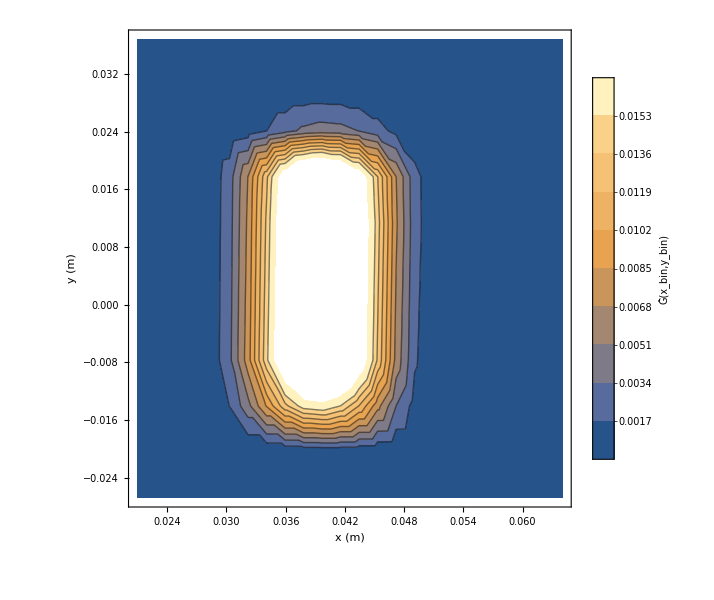

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1060/"];
```

```mathematica
dYAoffSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYAoffSpectruma1060=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYAoffSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma0[[All,2]]/Total[dYAoffSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYAoffSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1040[[All,2]]/Total[dYAoffSpectruma1040[[All,2]]]}]];
dYAoffSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1045[[All,2]]/Total[dYAoffSpectruma1045[[All,2]]]}]];
dYAoffSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]/Total[dYAoffSpectruma1055[[All,2]]]}]];
dYAoffSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1060[[All,2]]/Total[dYAoffSpectruma1060[[All,2]]]}]];
```

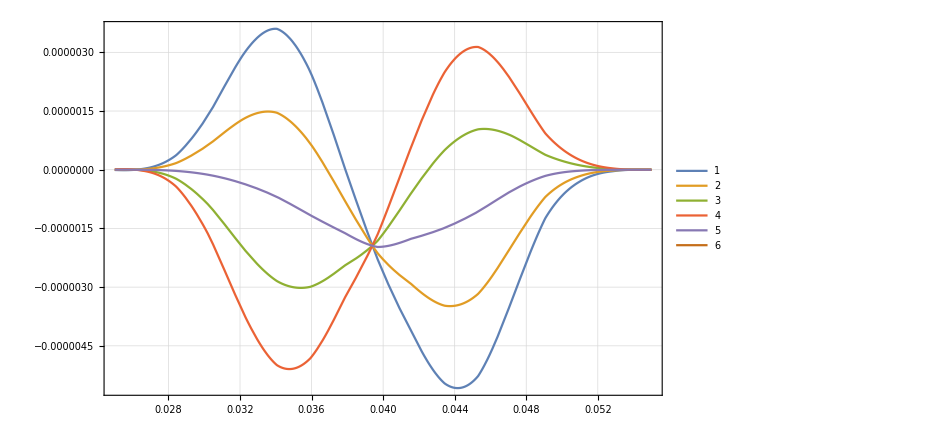

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYAoffSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dYAoffDataList={dYAoffSpectruma1040[[All,2]]/Total[dYAoffSpectruma1040[[All,2]]],dYAoffSpectruma1045[[All,2]]/Total[dYAoffSpectruma1045[[All,2]]],dYAoffSpectruma0[[All,2]]/Total[dYAoffSpectruma0[[All,2]]],dYAoffSpectruma1055[[All,2]]/Total[dYAoffSpectruma1055[[All,2]]],dYAoffSpectruma1060[[All,2]]/Total[dYAoffSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

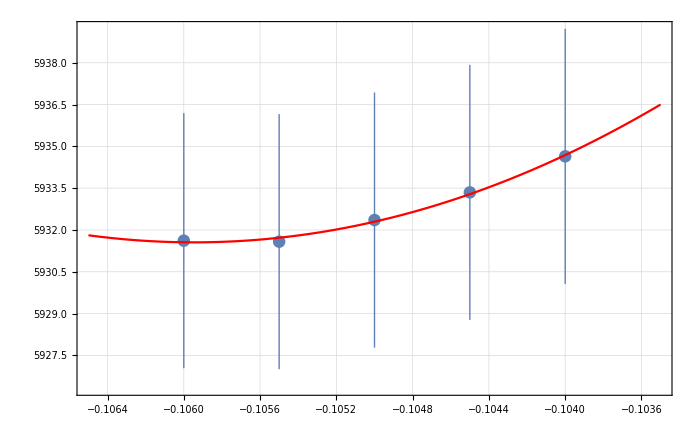
{{{5.93464×10^-6,5.93335×10^-6,5.93236×10^-6,5.93158×10^-6,5.93162×10^-6},{4.5762×10^-9,4.5759×10^-9,4.57577×10^-9,4.57577×10^-9,4.57606×10^-9}},a0 =  | -0.105946
FittedModel[5.93156×10^-6+0.000826198 (0.105946+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105946 | 0.00587116 | -18.0452 | 0.00305689
scale | 0.000826198 | 0.00489193 | 0.16889 | 0.881419
yoffset | 5.93156×10^-6 | 3.92918×10^-9 | 1509.62 | 4.38801×10^-7 | 
 | DF | SS | MS
Model | 3 | 8.40457×10^6 | 2.80152×10^6
Error | 2 | 0.00154951 | 0.000774754
Uncorrected Total | 5 | 8.40457×10^6 | 
Corrected Total | 4 | 0.321784 |  | ,-Graphics-}

```mathematica
dYAoffInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dYAoffDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

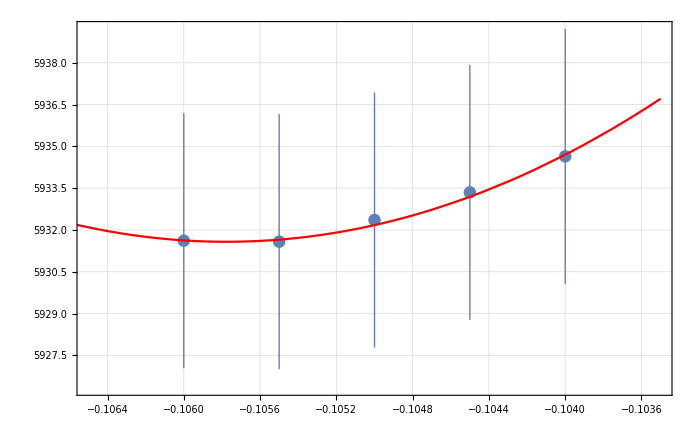
{{{5.93464×10^-6,5.93335×10^-6,5.93236×10^-6,5.93158×10^-6,5.93162×10^-6},{4.5762×10^-9,4.5759×10^-9,4.57577×10^-9,4.57577×10^-9,4.57606×10^-9}},a0 =  | -0.105777
FittedModel[5.93158×10^-6+0.000989562 (0.105777+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105777 | 0.0041106 | -25.7328 | 0.00150676
scale | 0.000989562 | 0.00489193 | 0.202284 | 0.858404
yoffset | 5.93158×10^-6 | 3.08295×10^-9 | 1923.99 | 2.70143×10^-7 | 
 | DF | SS | MS
Model | 3 | 8.40457×10^6 | 2.80152×10^6
Error | 2 | 0.00318487 | 0.00159243
Uncorrected Total | 5 | 8.40457×10^6 | 
Corrected Total | 4 | 0.321784 |  | ,-Graphics-}

```mathematica
dYAoffInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dYAoffDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10577711903993532+0.105)/-0.105)/(0.0002)
```

37.0057

# dXDShift, k=193.6

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1050/"];
```

```mathematica
dXDShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_179-264.txt}

```mathematica
dXDShiftSpectruma0=Flatten[Table[Import[dXDShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dXDShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1040/"];
```

```mathematica
dXDShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_179-264.txt}

```mathematica
dXDShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1045/"];
```

```mathematica
dXDShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_179-264.txt}

```mathematica
dXDShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1055/"];
```

```mathematica
dXDShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_179-264.txt}

```mathematica
dXDShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

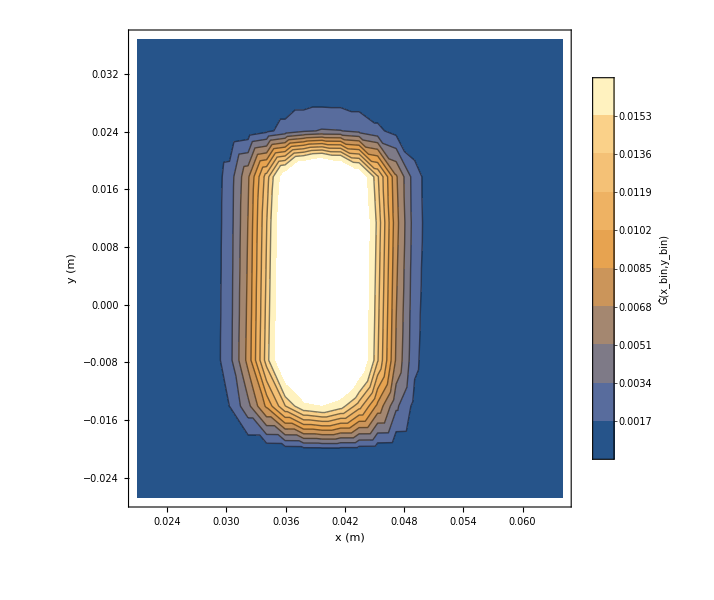

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1055[[All,2]]/Total[dXDShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1060/"];
```

```mathematica
dXDShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dXDShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dXDShiftSpectruma0[[All,2]]/Total[dXDShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXDShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma0[[All,2]]/Total[dXDShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXDShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1040[[All,2]]/Total[dXDShiftSpectruma1040[[All,2]]]}]];
dXDShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1045[[All,2]]/Total[dXDShiftSpectruma1045[[All,2]]]}]];
dXDShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1055[[All,2]]/Total[dXDShiftSpectruma1055[[All,2]]]}]];
dXDShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1060[[All,2]]/Total[dXDShiftSpectruma1060[[All,2]]]}]];
```

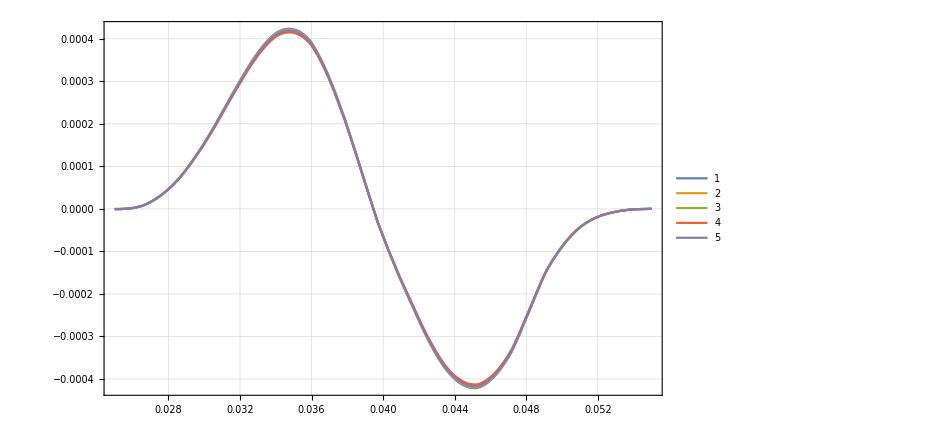

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dXDShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dXDShiftDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dXDShiftDataList={dXDShiftSpectruma1040[[All,2]]/Total[dXDShiftSpectruma1040[[All,2]]],dXDShiftSpectruma1045[[All,2]]/Total[dXDShiftSpectruma1045[[All,2]]],dXDShiftSpectruma0[[All,2]]/Total[dXDShiftSpectruma0[[All,2]]],dXDShiftSpectruma1055[[All,2]]/Total[dXDShiftSpectruma1055[[All,2]]],dXDShiftSpectruma1060[[All,2]]/Total[dXDShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

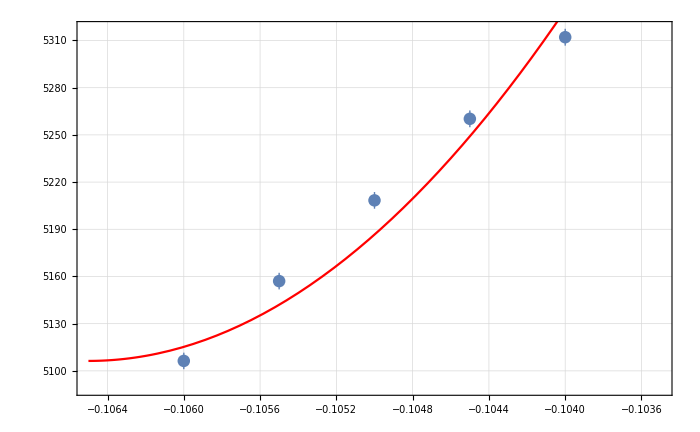
{{{5.31209×10^-6,5.26021×10^-6,5.20838×10^-6,5.15706×10^-6,5.10632×10^-6},{5.35579×10^-9,5.32937×10^-9,5.30264×10^-9,5.27631×10^-9,5.24994×10^-9}},a0 =  | -0.1065
FittedModel[5.10632×10^-6+0.0356891 (0.1065+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1065 | 0.000242302 | -439.533 | 5.17622×10^-6
scale | 0.0356891 | 0.00566881 | 6.2957 | 0.0243133
yoffset | 5.10632×10^-6 | 1.13065×10^-8 | 451.627 | 4.90272×10^-6 | 
 | DF | SS | MS
Model | 3 | 4.82403×10^6 | 1.60801×10^6
Error | 2 | 42.6424 | 21.3212
Uncorrected Total | 5 | 4.82407×10^6 | 
Corrected Total | 4 | 941.957 |  | ,-Graphics-}

```mathematica
dXDShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dXDShiftDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

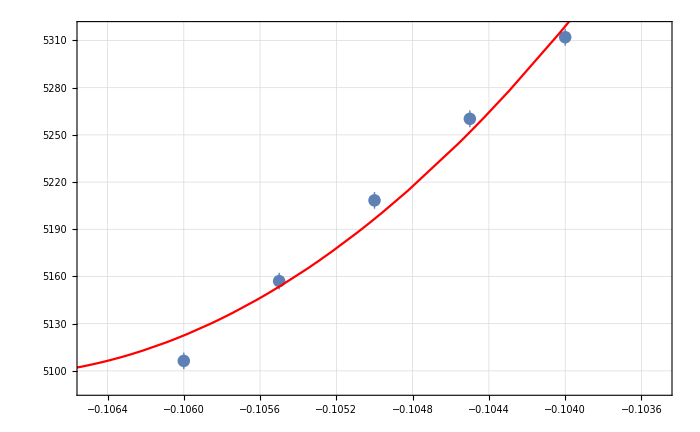
{{{5.31209×10^-6,5.26021×10^-6,5.20838×10^-6,5.15706×10^-6,5.10632×10^-6},{5.35579×10^-9,5.32937×10^-9,5.30264×10^-9,5.27631×10^-9,5.24994×10^-9}},a0 =  | -0.107033
FittedModel[5.09672×10^-6+0.0241705 (0.107033+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.107033 | 0.000480965 | -222.538 | 0.000020192
scale | 0.0241705 | 0.00566881 | 4.26377 | 0.0508474
yoffset | 5.09672×10^-6 | 2.17322×10^-8 | 234.523 | 0.0000181809 | 
 | DF | SS | MS
Model | 3 | 4.82405×10^6 | 1.60802×10^6
Error | 2 | 19.0747 | 9.53736
Uncorrected Total | 5 | 4.82407×10^6 | 
Corrected Total | 4 | 941.957 |  | ,-Graphics-}

```mathematica
dXDShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dXDShiftDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10703276961983176+0.105)/-0.105)/(0.0001)
```

193.597

# dYDShift, k=29.62

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1050/"];
```

```mathematica
dYDShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_179-264.txt}

```mathematica
dYDShiftSpectruma0=Flatten[Table[Import[dYDShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dYDShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1040/"];
```

```mathematica
dYDShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_179-264.txt}

```mathematica
dYDShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1045/"];
```

```mathematica
dYDShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_179-264.txt}

```mathematica
dYDShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1055/"];
```

```mathematica
dYDShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_179-264.txt}

```mathematica
dYDShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

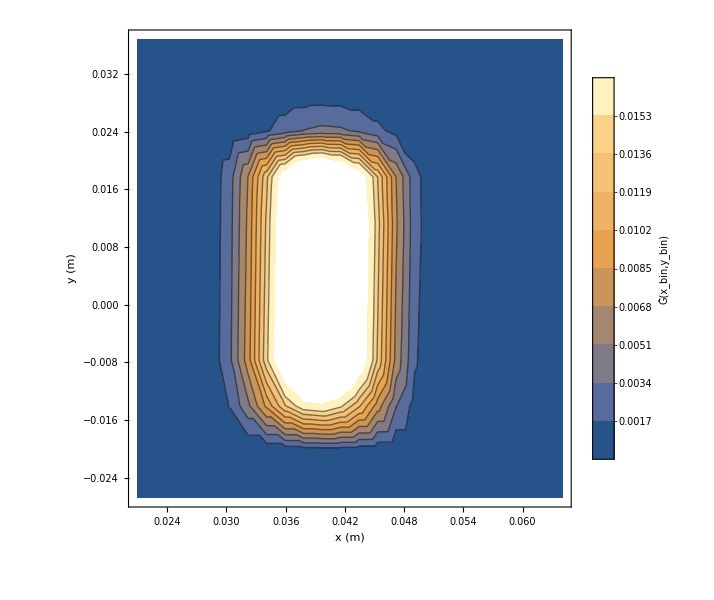

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1055[[All,2]]/Total[dYDShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1060/"];
```

```mathematica
dYDShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYDShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYDShiftSpectruma0[[All,2]]/Total[dYDShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYDShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma0[[All,2]]/Total[dYDShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYDShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1040[[All,2]]/Total[dYDShiftSpectruma1040[[All,2]]]}]];
dYDShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1045[[All,2]]/Total[dYDShiftSpectruma1045[[All,2]]]}]];
dYDShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1055[[All,2]]/Total[dYDShiftSpectruma1055[[All,2]]]}]];
dYDShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1060[[All,2]]/Total[dYDShiftSpectruma1060[[All,2]]]}]];
```

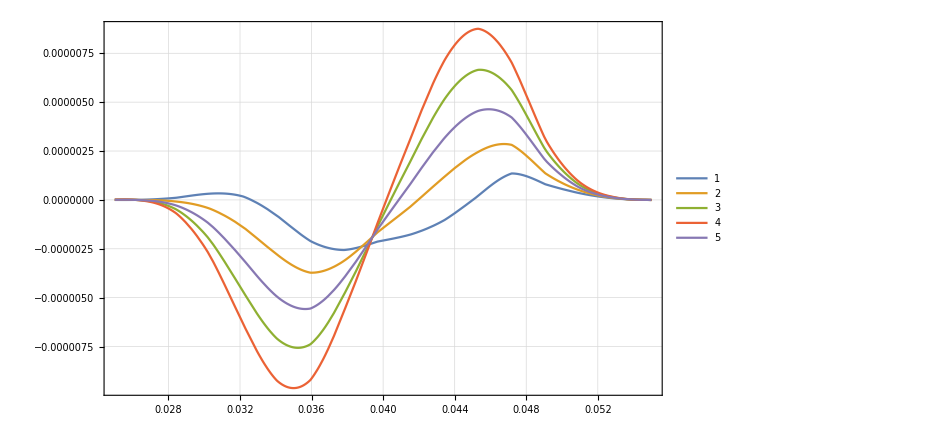

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYDShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYDShiftDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dYDShiftDataList={dYDShiftSpectruma1040[[All,2]]/Total[dYDShiftSpectruma1040[[All,2]]],dYDShiftSpectruma1045[[All,2]]/Total[dYDShiftSpectruma1045[[All,2]]],dYDShiftSpectruma0[[All,2]]/Total[dYDShiftSpectruma0[[All,2]]],dYDShiftSpectruma1055[[All,2]]/Total[dYDShiftSpectruma1055[[All,2]]],dYDShiftSpectruma1060[[All,2]]/Total[dYDShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

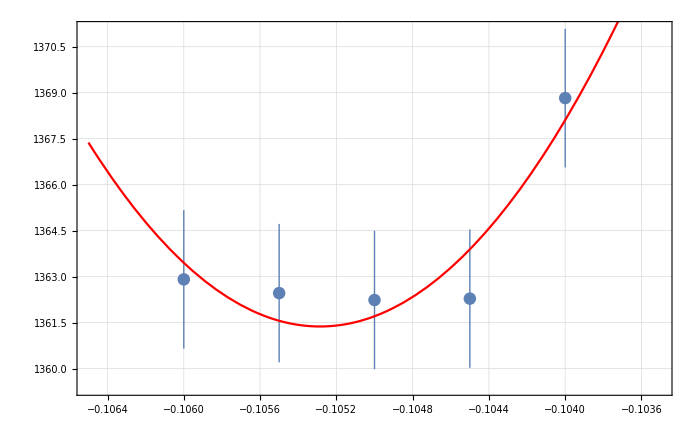
{{{1.36883×10^-6,1.36228×10^-6,1.36224×10^-6,1.36246×10^-6,1.36291×10^-6},{2.26056×10^-9,2.25611×10^-9,2.25655×10^-9,2.2573×10^-9,2.25836×10^-9}},a0 =  | -0.105286
FittedModel[1.36137×10^-6+0.00407102 (0.105286+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105286 | 0.000243972 | -431.549 | 5.36952×10^-6
scale | 0.00407102 | 0.00241416 | 1.68631 | 0.233783
yoffset | 1.36137×10^-6 | 1.48442×10^-9 | 917.108 | 1.18893×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.8242×10^6 | 608068.
Error | 2 | 0.879927 | 0.439963
Uncorrected Total | 5 | 1.8242×10^6 | 
Corrected Total | 4 | 6.37621 |  | ,-Graphics-}

```mathematica
dYDShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dYDShiftDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

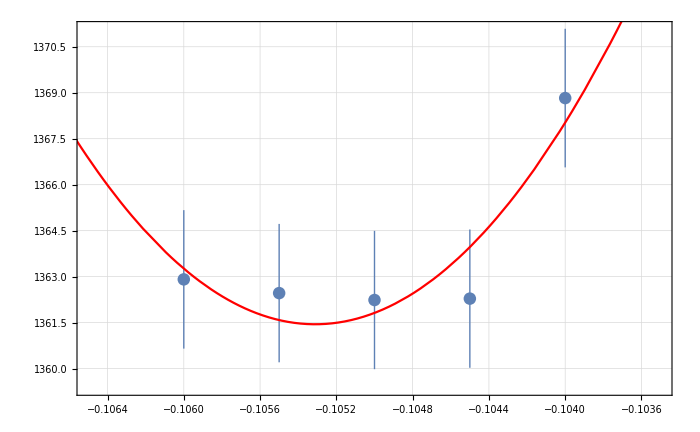
{{{1.36883×10^-6,1.36228×10^-6,1.36224×10^-6,1.36246×10^-6,1.36291×10^-6},{2.26056×10^-9,2.25611×10^-9,2.25655×10^-9,2.2573×10^-9,2.25836×10^-9}},a0 =  | -0.105311
FittedModel[1.36145×10^-6+0.00382789 (0.105311+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105311 | 0.000270657 | -389.094 | 6.60522×10^-6
scale | 0.00382789 | 0.00241416 | 1.5856 | 0.253711
yoffset | 1.36145×10^-6 | 1.47058×10^-9 | 925.788 | 1.16674×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.8242×10^6 | 608068.
Error | 2 | 0.89164 | 0.44582
Uncorrected Total | 5 | 1.8242×10^6 | 
Corrected Total | 4 | 6.37621 |  | ,-Graphics-}

```mathematica
dYDShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dYDShiftDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10531106171262236+0.105)/-0.105)/(0.0001)
```

29.6249

# dxAA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1050/"];
```

```mathematica
dxAASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_179-264.txt}

```mathematica
dxAASpectruma0=Flatten[Table[Import[dxAASubFileNamesa0[[i]],"Table"],{i,1,Length[dxAAoffSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1040/"];
```

```mathematica
dxAASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_179-264.txt}

```mathematica
dxAASpectruma1040=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1045/"];
```

```mathematica
dxAASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_179-264.txt}

```mathematica
dxAASpectruma1045=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1035/"];
```

```mathematica
dxAASubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1035_179-264.txt}

```mathematica
dxAASpectruma1035=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1035,1];
```

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1030/"];
```

```mathematica
dxAASubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1030_179-264.txt}

```mathematica
dxAASpectruma1030=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1030,1];
```

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1020/"];
```

```mathematica
dxAASubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1019_179-264.txt}

```mathematica
dxAASpectruma1020=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1020,1];
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1055/"];
```

```mathematica
dxAASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_179-264.txt}

```mathematica
dxAASpectruma1055=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1060/"];
```

```mathematica
dxAASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dxAASpectruma1060=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
dxAASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dxAASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]]}]];
dxAASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]]}]];
dxAASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]]}]];
dxAASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]}]];
```

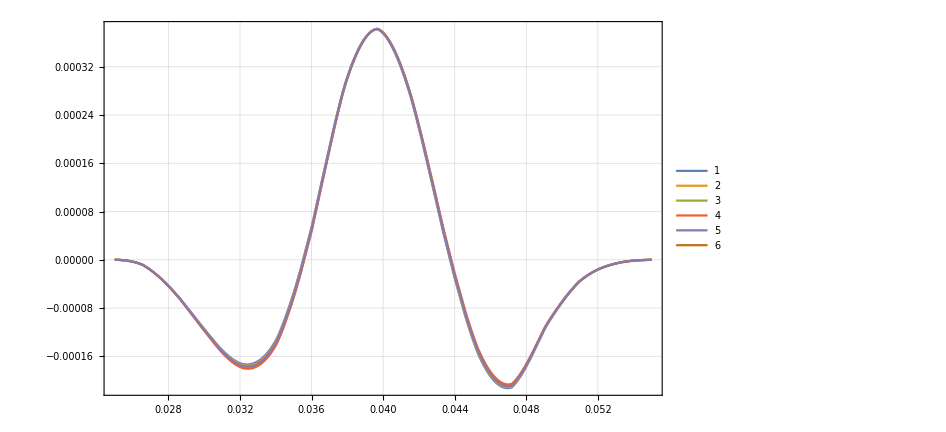

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dxAASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dxAADataList2={dxAASpectruma1020[[All,2]]/Total[dxAASpectruma1020[[All,2]]],dxAASpectruma1030[[All,2]]/Total[dxAASpectruma1030[[All,2]]],dxAASpectruma1035[[All,2]]/Total[dxAASpectruma1035[[All,2]]],dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]};
```

```mathematica
dxAADataList={dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]};
```

```mathematica
bList2={-.102,-.103 ,-.1035 ,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

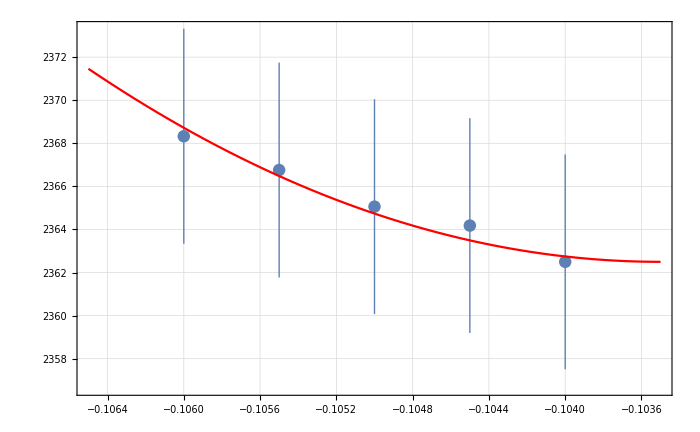
{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.1035
FittedModel[2.3625×10^-6+0.000995836 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.00818383 | -12.6469 | 0.00619416
scale | 0.000995836 | 0.00533118 | 0.186795 | 0.869054
yoffset | 2.3625×10^-6 | 1.06922×10^-8 | 220.954 | 0.0000204824 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0349819 | 0.0174909
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
dxAAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

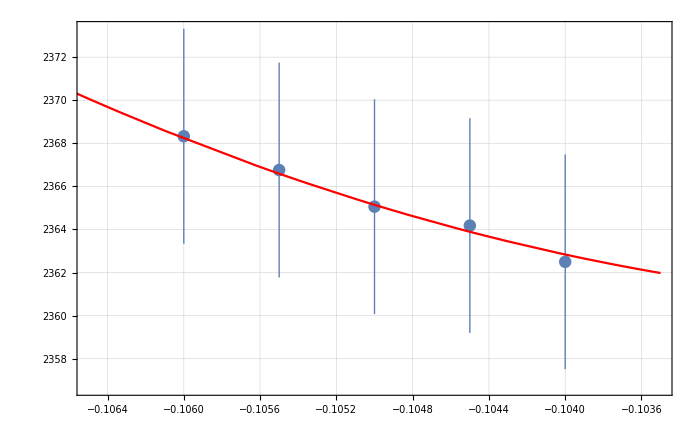
{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.101557
FittedModel[2.3605×10^-6+0.000391815 (0.101557+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101557 | 0.047012 | -2.16024 | 0.16334
scale | 0.000391815 | 0.00533118 | 0.073495 | 0.948101
yoffset | 2.3605×10^-6 | 6.15185×10^-8 | 38.3705 | 0.000678519 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0097655 | 0.00488275
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
dxAAInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

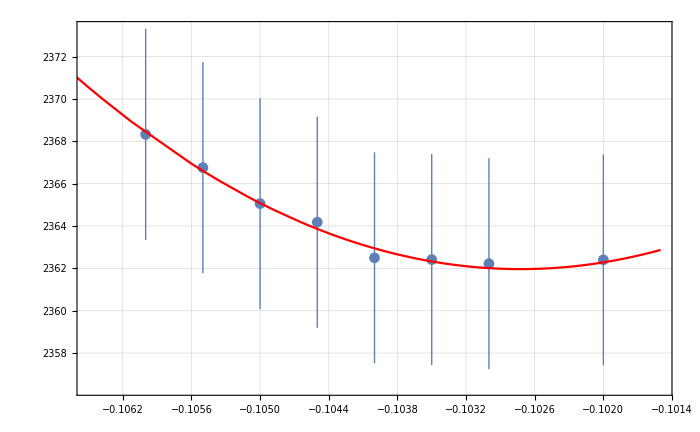
{{{2.3624×10^-6,2.36222×10^-6,2.36241×10^-6,2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98246×10^-9,4.98351×10^-9,4.98425×10^-9,4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.102726
FittedModel[2.36197×10^-6+0.000602823 (0.102726+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.102726 | 0.00276563 | -37.1437 | 2.66387×10^-7
scale | 0.000602823 | 0.00115011 | 0.524143 | 0.622575
yoffset | 2.36197×10^-6 | 2.71803×10^-9 | 868.999 | 3.83002×10^-14 | 
 | DF | SS | MS
Model | 3 | 1.79902×10^6 | 599675.
Error | 5 | 0.0161217 | 0.00322434
Uncorrected Total | 8 | 1.79902×10^6 | 
Corrected Total | 7 | 1.50969 |  | ,-Graphics-}

```mathematica
dxAAInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dxAADataList2,bList2, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10577711903993532+0.105)/-0.105)/(0.0002)
```

37.0057

```mathematica
((-0.10272571946582504+0.105)/-0.105)/(0.0002)
```

-108.299

# dyAA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1050/"];
```

```mathematica
dyAASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dyAA_a-1050_179-264.txt}

```mathematica
dyAASpectruma0=Flatten[Table[Import[dyAASubFileNamesa0[[i]],"Table"],{i,1,Length[dyAASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1040/"];
```

```mathematica
dyAASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1040_179-264.txt}

```mathematica
dyAASpectruma1040=Flatten[Import[#,"Table"]&/@dyAASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1045/"];
```

```mathematica
dyAASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_D_dyAA_a-1045_179-264.txt}

```mathematica
dyAASpectruma1045=Flatten[Import[#,"Table"]&/@dyAASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1055/"];
```

```mathematica
dyAASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dyAA_a-1055_179-264.txt}

```mathematica
dyAASpectruma1055=Flatten[Import[#,"Table"]&/@dyAASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dyAA/a-1060/"];
```

```mathematica
dyAASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dyAA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dyAASpectruma1060=Flatten[Import[#,"Table"]&/@dyAASubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
dyAASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma0[[All,2]]/Total[dyAASpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dyAASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1040[[All,2]]/Total[dyAASpectruma1040[[All,2]]]}]];
dyAASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1045[[All,2]]/Total[dyAASpectruma1045[[All,2]]]}]];
dyAASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1055[[All,2]]/Total[dyAASpectruma1055[[All,2]]]}]];
dyAASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dyAASpectruma1060[[All,2]]/Total[dyAASpectruma1060[[All,2]]]}]];
```

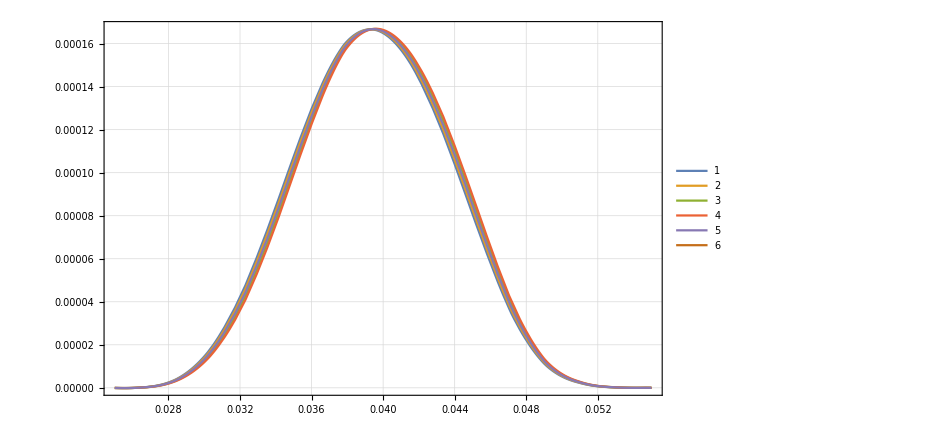

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dyAASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dyAASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dyAASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dyAASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dyAASpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dyAADataList={dyAASpectruma1040[[All,2]]/Total[dyAASpectruma1040[[All,2]]],dyAASpectruma1045[[All,2]]/Total[dyAASpectruma1045[[All,2]]],dyAASpectruma0[[All,2]]/Total[dyAASpectruma0[[All,2]]],dyAASpectruma1055[[All,2]]/Total[dyAASpectruma1055[[All,2]]],dyAASpectruma1060[[All,2]]/Total[dyAASpectruma1060[[All,2]]]};
```

```mathematica
bList2={-.102,-.103 ,-.1035 ,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

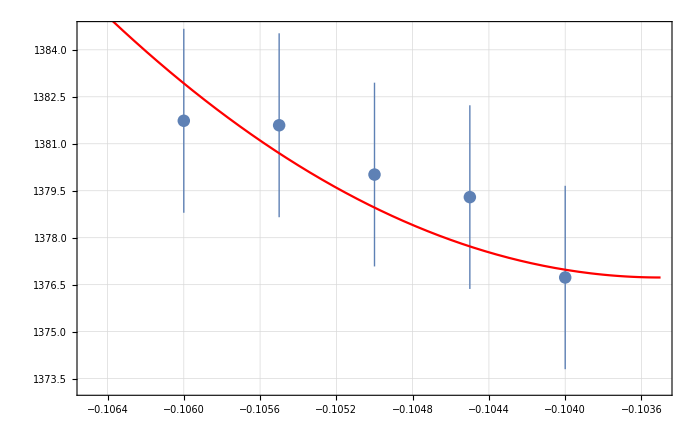
{{{1.37673×10^-6,1.3793×10^-6,1.38002×10^-6,1.38159×10^-6,1.38173×10^-6},{2.92816×10^-9,2.93259×10^-9,2.93429×10^-9,2.93668×10^-9,2.93746×10^-9}},a0 =  | -0.1035
FittedModel[1.37673×10^-6+0.000992024 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.00483143 | -21.4222 | 0.00217197
scale | 0.000992024 | 0.00313604 | 0.316331 | 0.781715
yoffset | 1.37673×10^-6 | 6.28502×10^-9 | 219.05 | 0.0000208402 | 
 | DF | SS | MS
Model | 3 | 1.10605×10^6 | 368685.
Error | 2 | 0.682849 | 0.341424
Uncorrected Total | 5 | 1.10605×10^6 | 
Corrected Total | 4 | 1.93721 |  | ,-Graphics-}

```mathematica
dyAAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dyAADataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

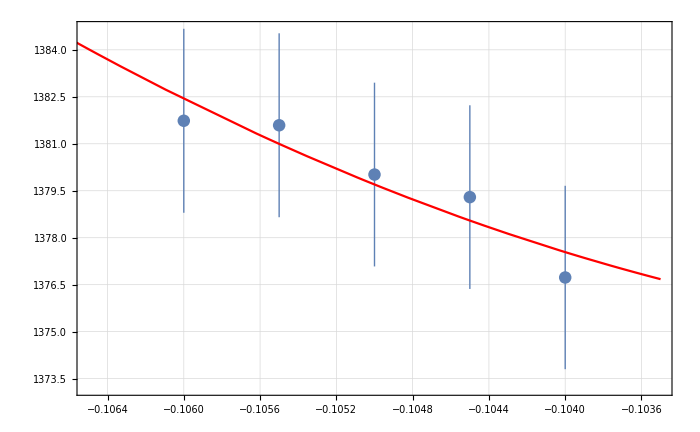
{{{1.37673×10^-6,1.3793×10^-6,1.38002×10^-6,1.38159×10^-6,1.38173×10^-6},{2.92816×10^-9,2.93259×10^-9,2.93429×10^-9,2.93668×10^-9,2.93746×10^-9}},a0 =  | -0.100757
FittedModel[1.3745×10^-6+0.00028858 (0.100757+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.100757 | 0.0462152 | -2.18017 | 0.161048
scale | 0.00028858 | 0.00313604 | 0.0920207 | 0.935069
yoffset | 1.3745×10^-6 | 5.54518×10^-8 | 24.7874 | 0.00162361 | 
 | DF | SS | MS
Model | 3 | 1.10605×10^6 | 368685.
Error | 2 | 0.25157 | 0.125785
Uncorrected Total | 5 | 1.10605×10^6 | 
Corrected Total | 4 | 1.93721 |  | ,-Graphics-}

```mathematica
dyAAInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dyAADataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10577711903993532+0.105)/-0.105)/(0.0002)
```

37.0057

```mathematica
((-0.10075697631656662+0.105)/-0.105)/(0.0002)
```

-202.049

```mathematica
202
```

# dXDShift, k=193.6

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1050/"];
```

```mathematica
dxAASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_179-264.txt}

```mathematica
dxAASpectruma0=Flatten[Table[Import[dxAASubFileNamesa0[[i]],"Table"],{i,1,Length[dxAASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1040/"];
```

```mathematica
dxAASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_179-264.txt}

```mathematica
dxAASpectruma1040=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1045/"];
```

```mathematica
dxAASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_179-264.txt}

```mathematica
dxAASpectruma1045=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1055/"];
```

```mathematica
dxAASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_179-264.txt}

```mathematica
dxAASpectruma1055=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

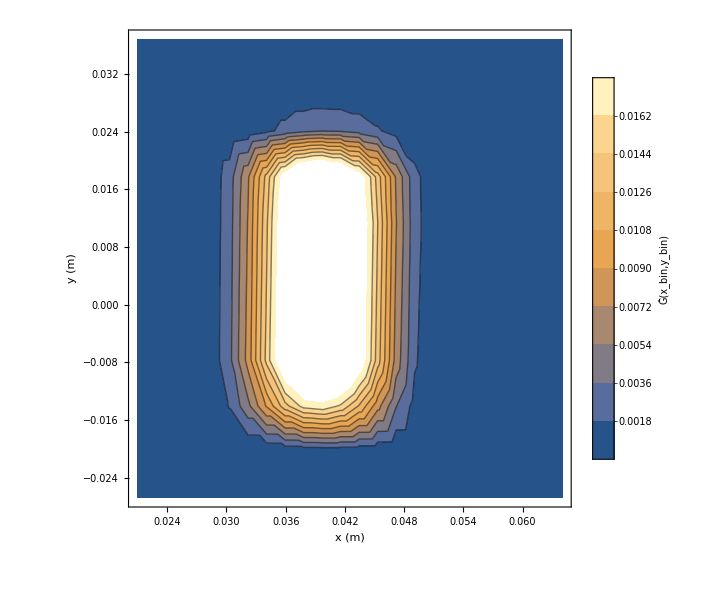

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1060/"];
```

```mathematica
dxAASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dxAASpectruma1060=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dxAASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dxAASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]]}]];
dxAASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]]}]];
dxAASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]]}]];
dxAASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]}]];
```

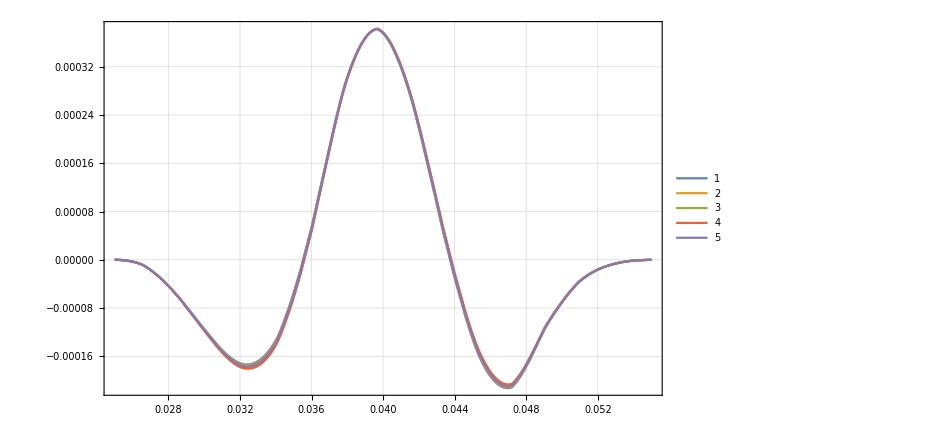

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dxAASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dxAADataList={dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
dxAAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.1035
FittedModel[2.3625×10^-6+0.000995836 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.00818383 | -12.6469 | 0.00619416
scale | 0.000995836 | 0.00533118 | 0.186795 | 0.869054
yoffset | 2.3625×10^-6 | 1.06922×10^-8 | 220.954 | 0.0000204824 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0349819 | 0.0174909
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

```mathematica
dxAAInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.101557
FittedModel[2.3605×10^-6+0.000391815 (0.101557+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101557 | 0.047012 | -2.16024 | 0.16334
scale | 0.000391815 | 0.00533118 | 0.073495 | 0.948101
yoffset | 2.3605×10^-6 | 6.15185×10^-8 | 38.3705 | 0.000678519 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0097655 | 0.00488275
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
-0.1065
```

-0.1065

```mathematica
0.00025
```

0.00025

```mathematica
0.2/1000
```

0.0002

```mathematica
((-0.1035+0.105)/-0.105)/(0.0002)
```

-71.4286

```mathematica
((-0.10155733953850894+0.105)/-0.105)/(0.0002)
```

-163.936

# No Neutron centered at 0 Beam prof. r=322.89

## da0 NoBeam0 1D, xoffset=3cm, noBeam, xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_noBeam0/a-1050/"];
```

```mathematica
d0SubFileNamesa01DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_noBeam0_a-1050_57-64.txt}

```mathematica
d0Spectruma01DNoBeam0=Flatten[Table[Import[d0SubFileNamesa01DNoBeam0[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DNoBeam0]}],1];
```

```mathematica
ClearAll[xStart,xEnd,yStart,yEnd];
xStart=-0.012;
xEnd=0.012;
yStart=-0.022;
yEnd=0.025;
xyBins1D0Shift=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf0Shift=BinCenters[xyBins1D0Shift];
```

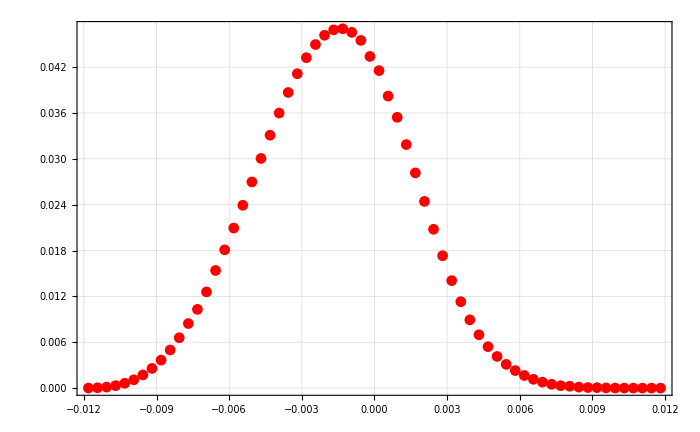

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf0Shift[[All,1]],d0Spectruma01DNoBeam0[[All,2]]/Total[d0Spectruma01DNoBeam0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
da0Spectrum1DNoBeam0Inter=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],d0Spectruma01DNoBeam0[[All,2]]/Total[d0Spectruma01DNoBeam0[[All,2]]]}]];
```

## drA NoBeam 1D, xoffset=3cm, noBeam, xAASC=3.5/1000; yAASC=35/1000;

```mathematica
pmax
```

1.18728×10^6

```mathematica
ppmax
```

1.18728×10^6

## a=-0.104

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1040/"];
```

```mathematica
drASubFileNamesa10401DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1040_57-64.txt}

```mathematica
drASpectruma10401DNoBeam0=Flatten[Table[Import[drASubFileNamesa10401DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa10401DNoBeam0]}],1];
```

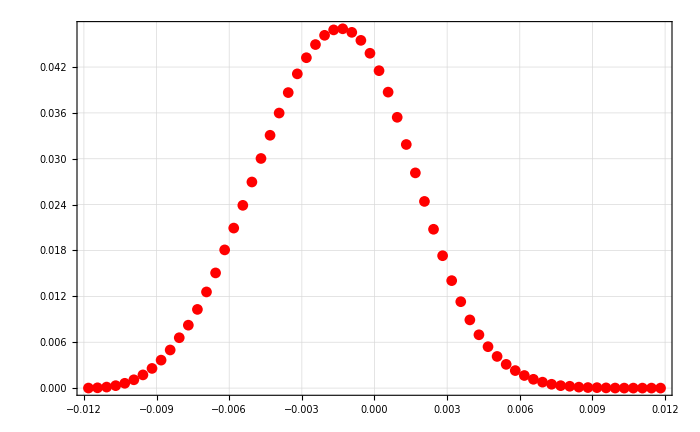

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10401DNoBeam0[[All,2]]/Total[drASpectruma10401DNoBeam0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1040Spectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10401DNoBeam0[[All,2]]/Total[drASpectruma10401DNoBeam0[[All,2]]]}]];
```

## a=-0.1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1045/"];
```

```mathematica
drASubFileNamesa10451DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1045_57-64.txt}

```mathematica
drASpectruma10451DNoBeam0=Flatten[Table[Import[drASubFileNamesa10451DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa10451DNoBeam0]}],1];
```

```mathematica
drAa1045Spectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10451DNoBeam0[[All,2]]/Total[drASpectruma10451DNoBeam0[[All,2]]]}]];
```

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1050/"];
```

```mathematica
drASubFileNamesa01DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1050_57-64.txt}

```mathematica
drASpectruma01DNoBeam0=Flatten[Table[Import[drASubFileNamesa01DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa01DNoBeam0]}],1];
```

```mathematica
drASpectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma01DNoBeam0[[All,2]]/Total[drASpectruma01DNoBeam0[[All,2]]]}]];
```

## a=-0.1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1055/"];
```

```mathematica
drASubFileNamesa10551DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1055_57-64.txt}

```mathematica
drASpectruma10551DNoBeam0=Flatten[Table[Import[drASubFileNamesa10551DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa10551DNoBeam0]}],1];
```

```mathematica
drAa1055Spectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10551DNoBeam0[[All,2]]/Total[drASpectruma10551DNoBeam0[[All,2]]]}]];
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_noBeam0/a-1060/"];
```

```mathematica
drASubFileNamesa10601DNoBeam0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_noBeam0_a-1060_57-64.txt}

```mathematica
drASpectruma10601DNoBeam0=Flatten[Table[Import[drASubFileNamesa10601DNoBeam0[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNoBeam0]}],1];
```

```mathematica
drAa1060Spectrum1DNoBeamInter0=Interpolation[Transpose[{XYBinCentersYHalf0Shift[[All,1]],drASpectruma10601DNoBeam0[[All,2]]/Total[drASpectruma10601DNoBeam0[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

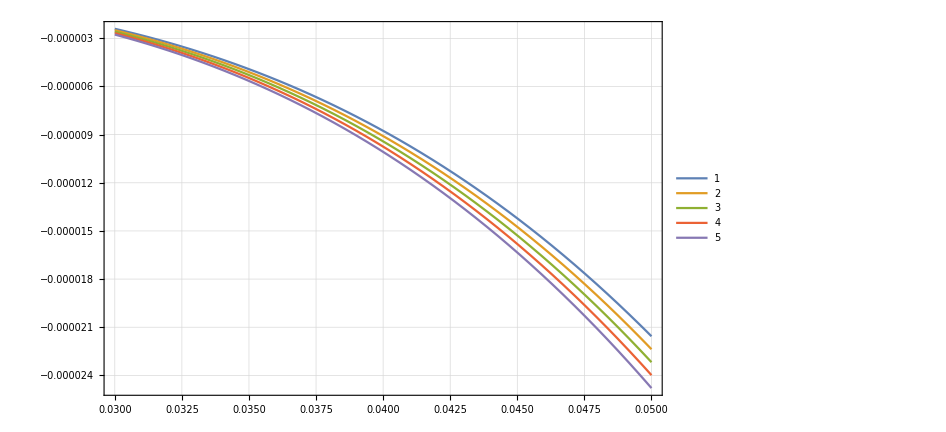

```mathematica
Plot[{
da0Spectrum1DNoBeam0Inter[x]-drAa1040Spectrum1DNoBeamInter0[x],
da0Spectrum1DNoBeam0Inter[x]-drAa1045Spectrum1DNoBeamInter0[x],
da0Spectrum1DNoBeam0Inter[x]-drASpectrum1DNoBeamInter0[x],
da0Spectrum1DNoBeam0Inter[x]-drAa1055Spectrum1DNoBeamInter0[x],
da0Spectrum1DNoBeam0Inter[x]-drAa1060Spectrum1DNoBeamInter0[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401DNoBeam0[[All,2]]/Total[drASpectruma10401DNoBeam0[[All,2]]],drASpectruma10451DNoBeam0[[All,2]]/Total[drASpectruma10451DNoBeam0[[All,2]]],drASpectruma01DNoBeam0[[All,2]]/Total[drASpectruma01DNoBeam0[[All,2]]],drASpectruma10551DNoBeam0[[All,2]]/Total[drASpectruma10551DNoBeam0[[All,2]]],drASpectruma10601DNoBeam0[[All,2]]/Total[drASpectruma10601DNoBeam0[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

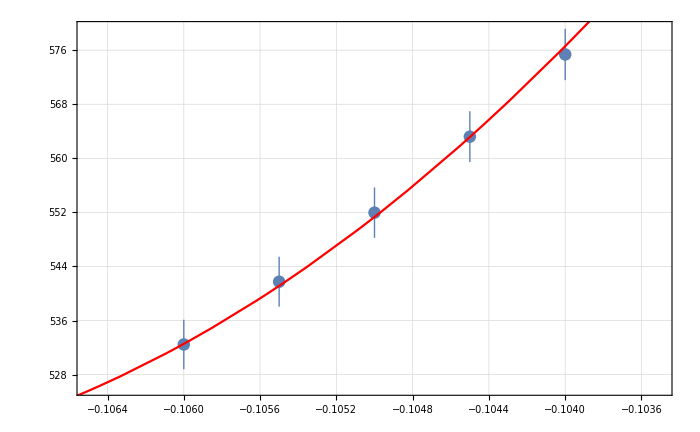
{{{5.75362×10^-7,5.63203×10^-7,5.51966×10^-7,5.4175×10^-7,5.32467×10^-7},{3.79773×10^-9,3.75901×10^-9,3.72209×10^-9,3.68739×10^-9,3.65469×10^-9}},a0 =  | -0.10839
FittedModel[5.14005×10^-7+0.00324673 (0.10839+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.10839 | 0.00416516 | -26.0231 | 0.00147341
scale | 0.00324673 | 0.00398146 | 0.815463 | 0.500475
yoffset | 5.14005×10^-7 | 4.43432×10^-8 | 11.5915 | 0.00736044 | 
 | DF | SS | MS
Model | 3 | 110204. | 36734.8
Error | 2 | 0.162758 | 0.081379
Uncorrected Total | 5 | 110205. | 
Corrected Total | 4 | 82.9153 |  | ,-Graphics-}

```mathematica
drAInvest0=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01DNoBeam0[[All,2]],drADataList,bList, 4]
```

```mathematica
((-0.10839034581739389+0.105)/-0.105)/(10^-4)
```

322.89

```mathematica
r
```

```mathematica
{{MeanX, MeanY}, {ApertX, ApertY}, {BDV}, {BF}, {BA}, {BRxB}, {BDet}}={{0.0301277, 1.00623}, {0.01, 
  0.035}, {0.220899}, {0.451107}, {0.219769}, {0.219722}, {0.207816}};
  
ApertXOff = 0.03; 
ApertYOff = 0.;

(*CenterfitG1=0.96907;
CenterfitG2=0.973888;*)
BlinefitG1=0.965547;
BlinefitG2=0.974009;

rF = BF/BDV;
rA = BA/BDV;
rRxB = BRxB/BDV;
rDet = BDet/BRxB;
```

```mathematica
rFSC=2.036;
rASC=0.937;
rRxBSC=0.902;
bRxBSC=0.976;
g1SC=1.29;
g2SC=1.792;
alphaSC=180.03*Pi/180;
rDSC=0.88;
```

```mathematica
Sqrt[rDet/rRxB]
```

0.975131

```mathematica
Sqrt[rDet]
```

0.972529

```mathematica
Sqrt[rDSC/rRxBSC]
```

0.98773

```mathematica
Sqrt[rDSC]
```

0.938083

0.972529

# NormalConducting Centered With no Beam k=50.07approx?

## da0 Normal 01D, (0.01,0.035), -0.05x offset, noBeam;

## a=-0.105

```mathematica
d0SubFileNamesa01DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_C_da0_normal0_a-1050_57-64.txt}

```mathematica
d0Spectruma01DNormal0=Flatten[Table[Import[d0SubFileNamesa01DNormal0[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DNormal0]}],1];
```

```mathematica
xStart=-0.06;
xEnd=0.06;
yStart=-0.03;
yEnd=0.04;
xyBinsNormal0=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1DNormal0=BinCenters[xyBinsNormal0];
```

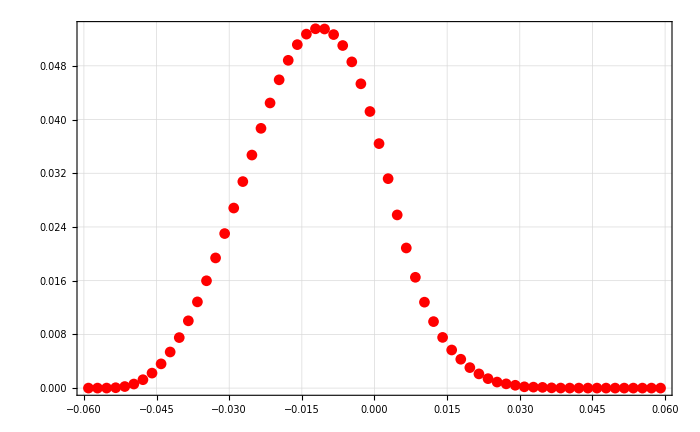

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]/Total[d0Spectruma01DNormal0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
da0Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]/Total[d0Spectruma01DNormal0[[All,2]]]}]];
```

## drA Normal0 1D, (0.01,0.035), -0.05x offset, noBeam;

## a=-0.104

```mathematica
drASubFileNamesa10401DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1040_57-64.txt}

```mathematica
drASpectruma10401DNormal0=Flatten[Table[Import[drASubFileNamesa10401DNormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa10401DNormal0]}],1];
```

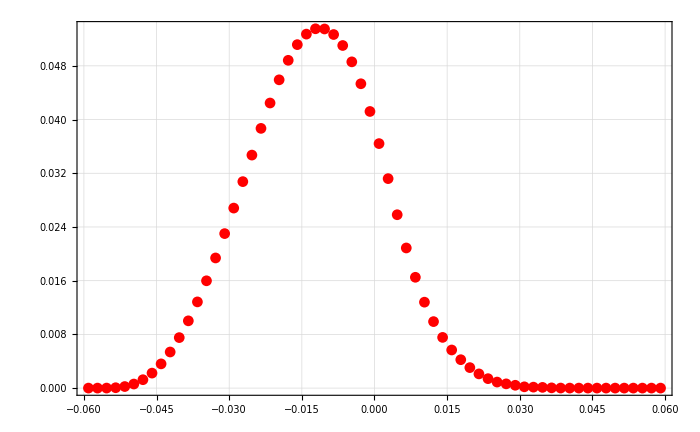

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10401DNormal0[[All,2]]/Total[drASpectruma10401DNormal0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1040Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10401DNormal0[[All,2]]/Total[drASpectruma10401DNormal0[[All,2]]]}]];
```

## a=-0.1045

```mathematica
drASubFileNamesa10451DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1045_57-64.txt}

```mathematica
drASpectruma10451DNormal0=Flatten[Table[Import[drASubFileNamesa10451DNormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa10451DNormal0]}],1];
```

```mathematica
drAa1045Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10451DNormal0[[All,2]]/Total[drASpectruma10451DNormal0[[All,2]]]}]];
```

## a=-0.105

```mathematica
drASubFileNamesa01DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normal0_a-1050_57-64.txt}

```mathematica
drASpectruma01DNormal0=Flatten[Table[Import[drASubFileNamesa01DNormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa01DNormal0]}],1];
```

```mathematica
drASpectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma01DNormal0[[All,2]]/Total[drASpectruma01DNormal0[[All,2]]]}]];
```

## a=-0.1055

```mathematica
drASubFileNamesa10551Dnormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal0_a-1055_57-64.txt}

```mathematica
drASpectruma10551DNormal0=Flatten[Table[Import[drASubFileNamesa10551Dnormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa10551Dnormal0]}],1];
```

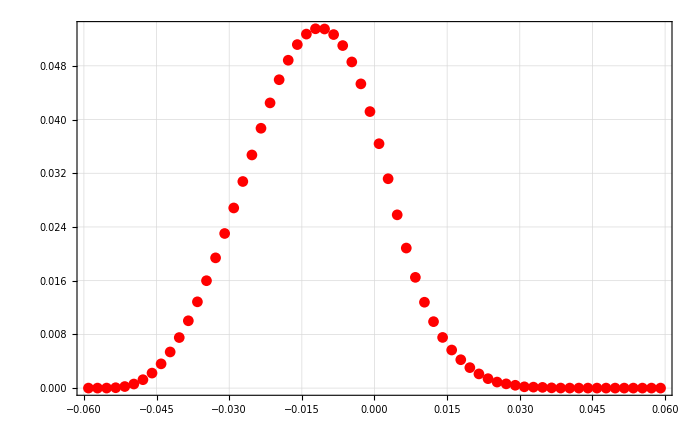

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10551DNormal0[[All,2]]/Total[drASpectruma10551DNormal0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1055Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10551DNormal0[[All,2]]/Total[drASpectruma10551DNormal0[[All,2]]]}]];
```

### a=-1060

```mathematica
drASubFileNamesa10601DNormal0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal0/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normal0_a-1060_57-64.txt}

```mathematica
drASpectruma10601DNormal0Check=Flatten[Table[Import[drASubFileNamesa10601DNormal0Check[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNormal0Check]}],1];
```

```mathematica
drASpectruma10601DNormal0[[All,2]]==drASpectruma10601DNormal0Check[[All,2]]
```

True

```mathematica
drASpectruma10601DNormal0=Flatten[Table[Import[drASubFileNamesa10601DNormal0[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNormal0]}],1];
```

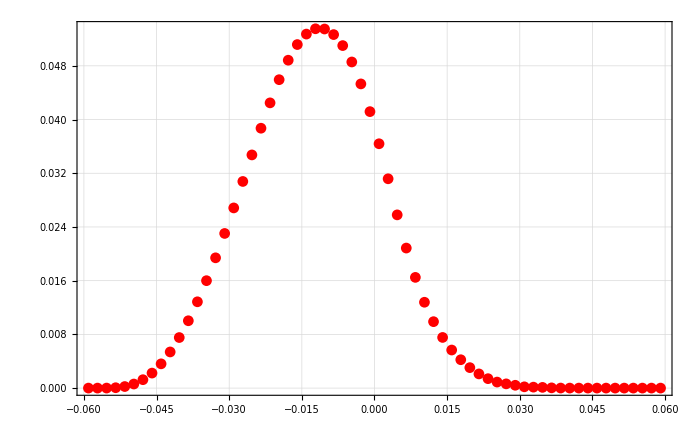

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10601DNormal0[[All,2]]/Total[drASpectruma10601DNormal0[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1060Spectrum1DNormal0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],drASpectruma10601DNormal0[[All,2]]/Total[drASpectruma10601DNormal0[[All,2]]]}]];
```

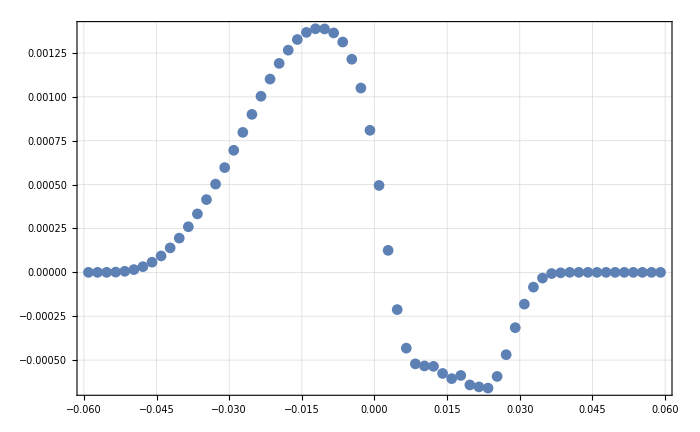

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]-drASpectruma10451DNormal0[[All,2]]}],PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0599975} lies outside the range of data in the interpolating function. Extrapolation will be used.

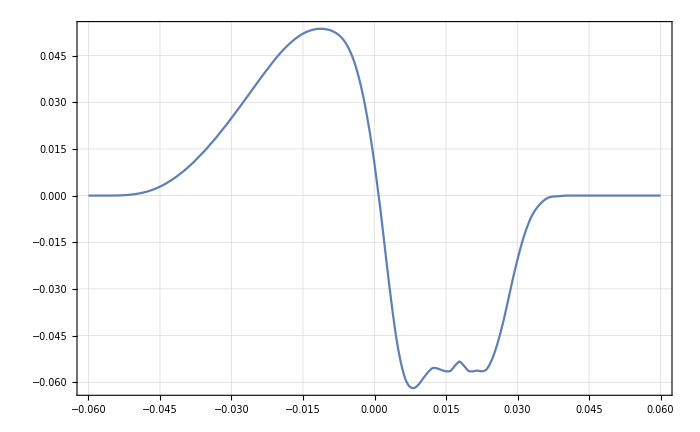

```mathematica
Plot[da0Spectrum1DNormal0Inter[x]-drAa1045Spectrum1DNormal0Inter[x],{x,-0.06,0.06},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0599975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

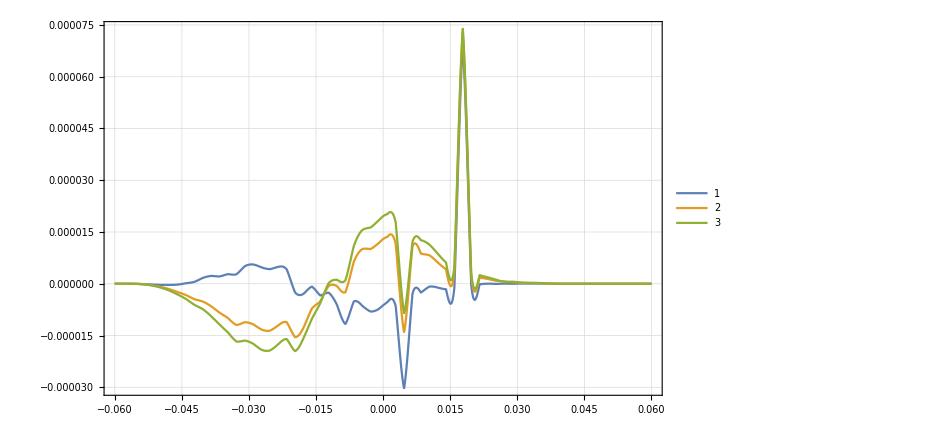

```mathematica
Plot[{
da0Spectrum1DNormal0Inter[x]-drAa1040Spectrum1DNormal0Inter[x],

da0Spectrum1DNormal0Inter[x]-drAa1055Spectrum1DNormal0Inter[x],
da0Spectrum1DNormal0Inter[x]-drAa1060Spectrum1DNormal0Inter[x]
}
,{x,-0.06,0.06},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
{{MeanX, MeanY}, {ApertX, ApertY}, {BDV}, {BF}, {BA}, {BRxB}, {BDet}}={{0.0301277, 1.00623}, {0.01, 
  0.035}, {0.220899}, {0.451107}, {0.219769}, {0.219722}, {0.207816}};
```

```mathematica
BA/BDV
```

0.994885

```mathematica
BF/BDV
```

2.04214

```mathematica
BRxB/BDV
```

0.994672

```mathematica
BDet/BRxB
```

0.945813

```mathematica
?xAShift
```

```mathematica
?DeltaxDV2Shift
```

```mathematica
?pXDomainShift
```

```mathematica
?phiAminApertShift
```

```mathematica
?DeltaxDVShift
```

```mathematica
?D1stBPolyGradwoR
```

```mathematica
?BpolynomGradwoR
```

```mathematica
?D1stBPolyGradwoR
```

```mathematica
?DeltayDVShift
```

```mathematica
?yGCAShift
```

```mathematica
?xGCAShift
```

```mathematica
?BpolynomGradwoR
```

```mathematica
2^2/3
```

4/3

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401DNormal0[[All,2]]/Total[drASpectruma10401DNormal0[[All,2]]],drASpectruma10451DNormal0[[All,2]]/Total[drASpectruma10451DNormal0[[All,2]]],drASpectruma10551DNormal0[[All,2]]/Total[drASpectruma10551DNormal0[[All,2]]],drASpectruma10601DNormal0[[All,2]]/Total[drASpectruma10601DNormal0[[All,2]]]};
```

```mathematica
bList={-.1040,-0.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

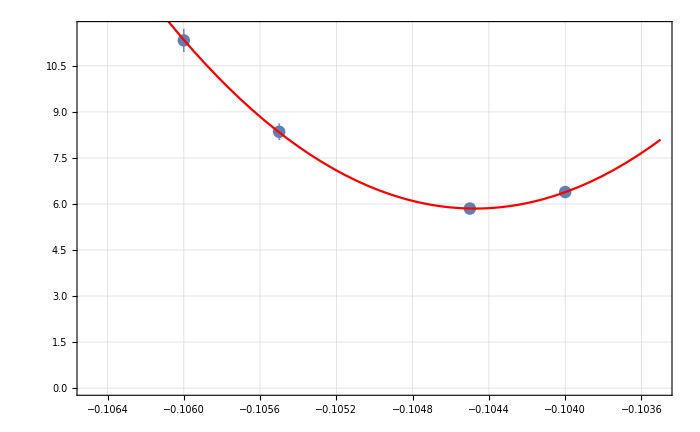
{{{6.38811×10^-9,5.85064×10^-9,8.35319×10^-9,1.13297×10^-8},{1.94786×10^-10,1.45323×10^-10,2.71656×10^-10,3.78657×10^-10}},a0 =  | -0.104475
FittedModel[5.85062×10^-9+0.0023635 (0.104475+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104475 | 0.0000672803 | -1552.83 | 0.000409974
scale | 0.0023635 | 0.000295921 | 7.98693 | 0.0792951
yoffset | 5.85062×10^-9 | 1.30664×10^-10 | 44.7759 | 0.0142155 | 
 | DF | SS | MS
Model | 3 | 4537.13 | 1512.38
Error | 1 | 0.00779565 | 0.00779565
Uncorrected Total | 4 | 4537.14 | 
Corrected Total | 3 | 222.836 |  | ,-Graphics-}

```mathematica
drAInvest=TransferToRefParableFitForProtons[d0Spectruma01DNormal0[[All,2]],drADataList,bList, 4]
```

```mathematica
((-0.10447488769311862+0.105)/-0.105)/(10^-4)
```

-50.0107

# NormalConducting Non-Centered with no Beam prof rA=39.07

## da0 NoBeam 1D, xoffset=3cm, noBeam, xAASC=0.1; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal/a-1050/"];
```

```mathematica
d0SubFileNamesa01DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_a-1050_57-64.txt}

```mathematica
d0Spectruma01DNormal=Flatten[Table[Import[d0SubFileNamesa01DNormal[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DNormal]}],1];
```

```mathematica
ClearAll[xStart,xEnd,yStart,yEnd];
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBinsNormal=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1DNormal=BinCenters[xyBinsNormal];
```

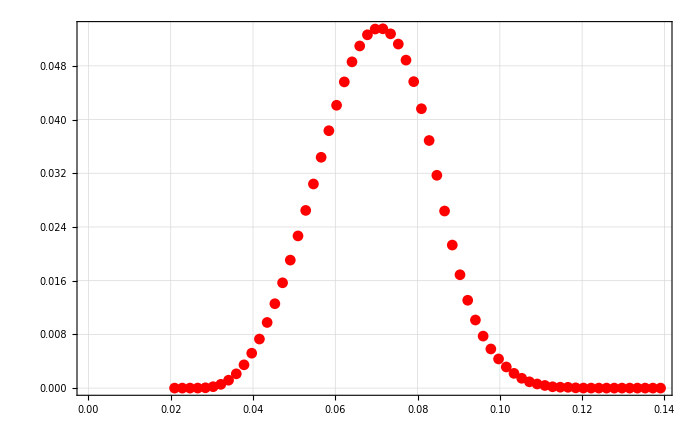

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormal[[All,2]]/Total[d0Spectruma01DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
da0Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormal[[All,2]]/Total[d0Spectruma01DNormal[[All,2]]]}]];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]/Total[d0Spectruma01DNormal0[[All,2]]]}],PlotStyle->Red]
```

-Graphics-

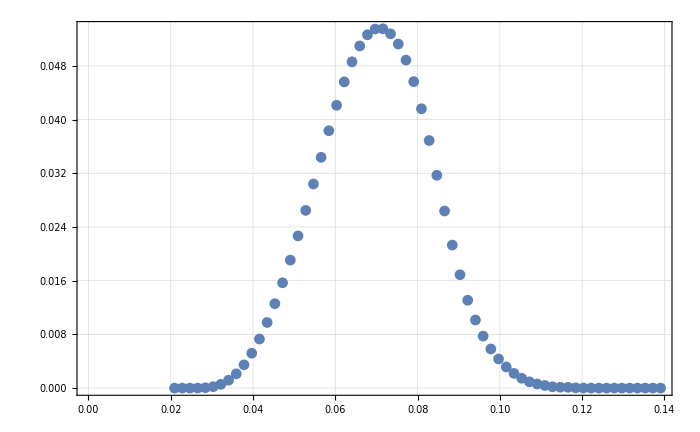

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormal[[All,2]]/Total[d0Spectruma01DNormal[[All,2]]]}]]
```

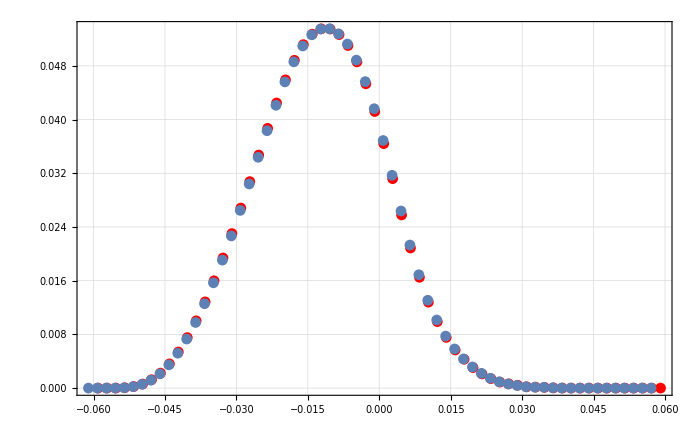

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal0[[All,1]],d0Spectruma01DNormal0[[All,2]]/Total[d0Spectruma01DNormal0[[All,2]]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]]-0.082,d0Spectruma01DNormal[[All,2]]/Total[d0Spectruma01DNormal[[All,2]]]}]],PlotRange->All]
```

## drA NoBeam 1D, xoffset=3cm, noBeam, xAASC=0.1; yAASC=35/1000;

## a=-0.104

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1040/"];
```

```mathematica
drASubFileNamesa10401DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1040_57-64.txt}

```mathematica
drASpectruma10401DNormal=Flatten[Table[Import[drASubFileNamesa10401DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa10401DNormal]}],1];
```

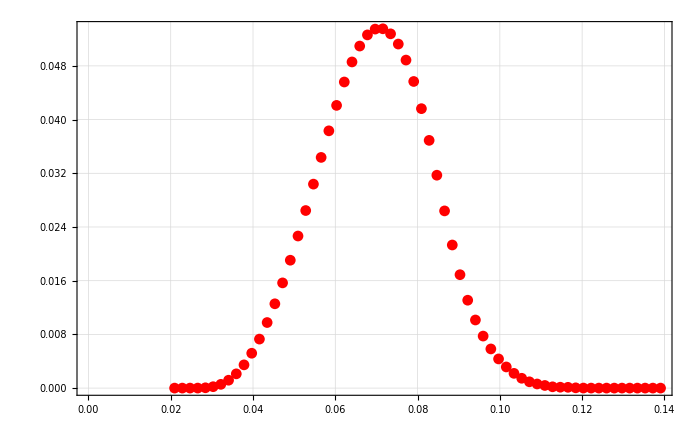

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10401DNormal[[All,2]]/Total[drASpectruma10401DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1040Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10401DNormal[[All,2]]/Total[drASpectruma10401DNormal[[All,2]]]}]];
```

## a=-0.1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1045/"];
```

```mathematica
drASubFileNamesa10451DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_drA_normal_a-1045_57-64.txt}

```mathematica
drASpectruma10451DNormal=Flatten[Table[Import[drASubFileNamesa10451DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa10451DNormal]}],1];
```

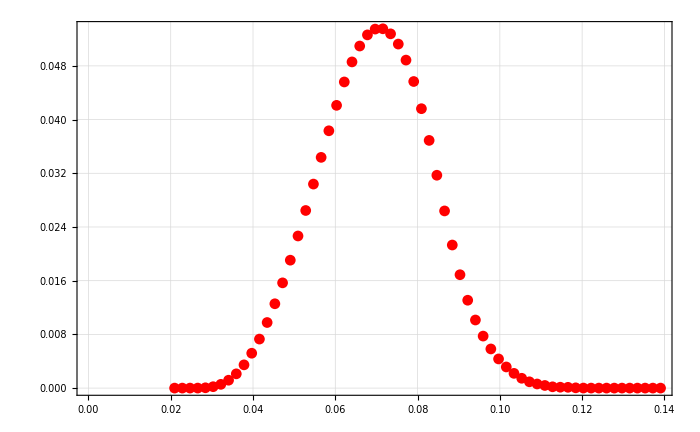

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10451DNormal[[All,2]]/Total[drASpectruma10451DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1045Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10451DNormal[[All,2]]/Total[drASpectruma10451DNormal[[All,2]]]}]];
```

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1050/"];
```

```mathematica
drASubFileNamesa01DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1050_57-64.txt}

```mathematica
drASpectruma01DNormal=Flatten[Table[Import[drASubFileNamesa01DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa01DNormal]}],1];
```

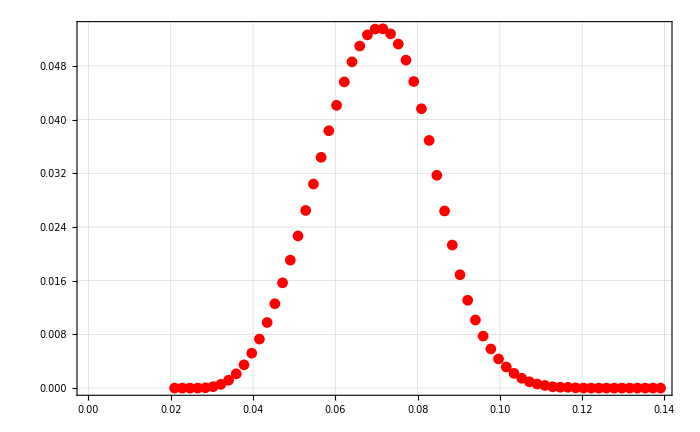

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma01DNormal[[All,2]]/Total[drASpectruma01DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drASpectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma01DNormal[[All,2]]/Total[drASpectruma01DNormal[[All,2]]]}]];
```

## a=-0.1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1055/"];
```

```mathematica
drASubFileNamesa10551DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1055_57-64.txt}

```mathematica
drASpectruma10551DNormal=Flatten[Table[Import[drASubFileNamesa10551DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa10551DNormal]}],1];
```

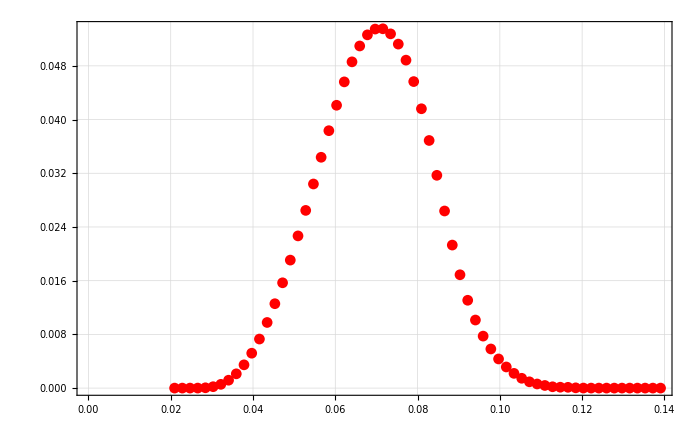

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10551DNormal[[All,2]]/Total[drASpectruma10551DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1055Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10551DNormal[[All,2]]/Total[drASpectruma10551DNormal[[All,2]]]}]];
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal/a-1060/"];
```

```mathematica
drASubFileNamesa10601DNormal=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_normal_a-1060_57-64.txt}

```mathematica
drASpectruma10601DNormal=Flatten[Table[Import[drASubFileNamesa10601DNormal[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNormal]}],1];
```

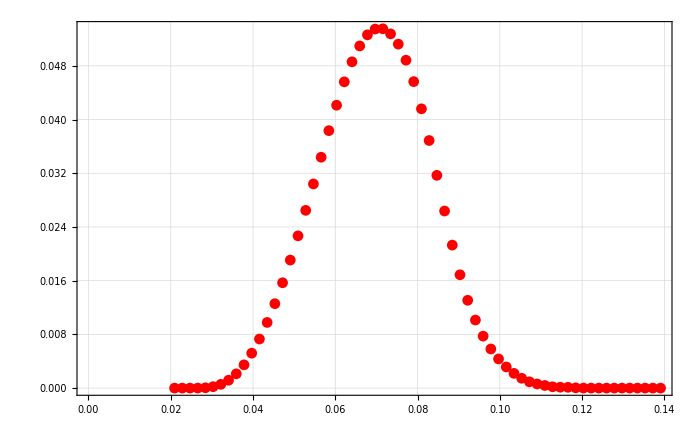

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10601DNormal[[All,2]]/Total[drASpectruma10601DNormal[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1060Spectrum1DNormalInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10601DNormal[[All,2]]/Total[drASpectruma10601DNormal[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200025} lies outside the range of data in the interpolating function. Extrapolation will be used.

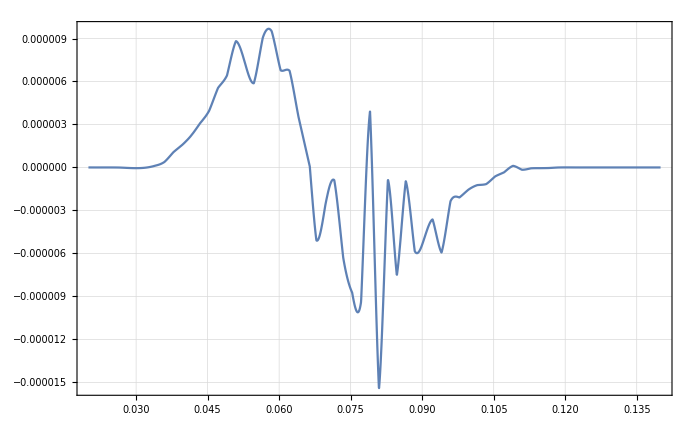

```mathematica
Show[Plot[drAa1060Spectrum1DNormalInter[x]-da0Spectrum1DNormalInter[x],{x,0.02,0.14}]]
```

InterpolatingFunction::dmval: Input value {0.0200025} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

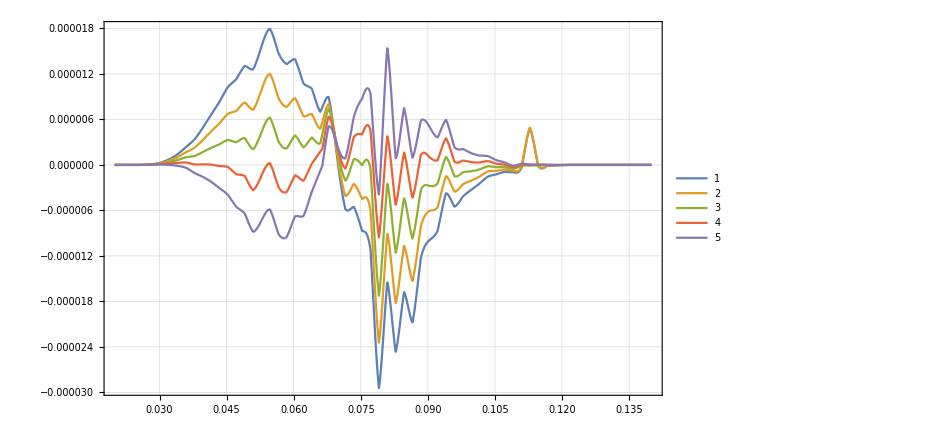

```mathematica
Plot[{
da0Spectrum1DNormalInter[x]-drAa1040Spectrum1DNormalInter[x],
da0Spectrum1DNormalInter[x]-drAa1045Spectrum1DNormalInter[x],
da0Spectrum1DNormalInter[x]-drASpectrum1DNormalInter[x],
da0Spectrum1DNormalInter[x]-drAa1055Spectrum1DNormalInter[x],
da0Spectrum1DNormalInter[x]-drAa1060Spectrum1DNormalInter[x]
}
,{x,0.02,0.14},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401DNormal[[All,2]]/Total[drASpectruma10401DNormal[[All,2]]],drASpectruma10451DNormal[[All,2]]/Total[drASpectruma10451DNormal[[All,2]]],drASpectruma01DNormal[[All,2]]/Total[drASpectruma01DNormal[[All,2]]],drASpectruma10551DNormal[[All,2]]/Total[drASpectruma10551DNormal[[All,2]]],drASpectruma10601DNormal[[All,2]]/Total[drASpectruma10601DNormal[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

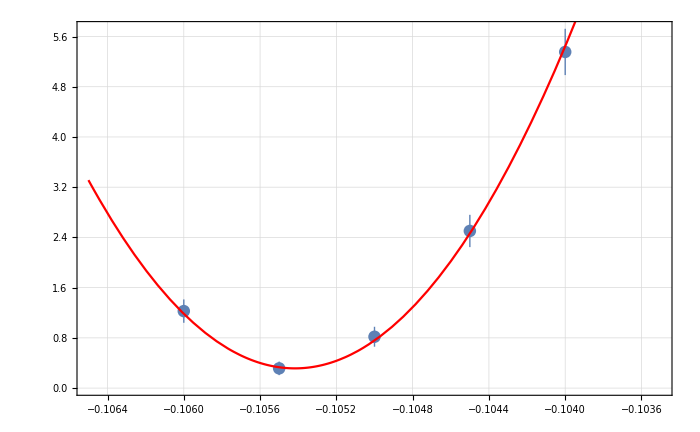
{{{5.35418×10^-9,2.50274×10^-9,8.17824×10^-10,3.14289×10^-10,1.22629×10^-9},{3.68704×10^-10,2.57071×10^-10,1.58799×10^-10,1.07937×10^-10,1.85956×10^-10}},a0 =  | -0.105417
FittedModel[3.14289×10^-10+0.00255551 (0.105417+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105417 | 0.0000399815 | -2636.64 | 1.43846×10^-7
scale | 0.00255551 | 0.000231945 | 11.0178 | 0.00813743
yoffset | 3.14289×10^-10 | 8.92047×10^-11 | 3.52324 | 0.0719708 | 
 | DF | SS | MS
Model | 3 | 383.843 | 127.948
Error | 2 | 0.304842 | 0.152421
Uncorrected Total | 5 | 384.148 | 
Corrected Total | 4 | 216.661 |  | ,-Graphics-}

```mathematica
drAInvest=TransferToRefParableFitForProtons[d0Spectruma01DNormal[[All,2]],drADataList,bList, 4]
```

```mathematica
((-0.10541686155163119+0.105)/-0.105)/(10^-4)
```

39.7011

# NormalConducting Non-Centered Small Aperture with no Beam prof rA=12.9145

## da0 NoBeam 1D, xoffset=3cm, noBeam, xAASC=0.005; yAASC=35/1000;

## a=-0.105

```mathematica
39/12.9
```

3.02326

```mathematica
150/3
```

50

```mathematica
Solve[xOff+xAA/2==xAShift[phiAlocal,yD,xD,plocal,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,{XAShift,YRxBShift,XDetShift,YDetShift}],phiAlocal][[All,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{InverseFunction[xAShift,1,15][1/2 (xAA+2 xOff),yD,xD,plocal,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,{XAShift,YRxBShift,XDetShift,YDetShift}]}

```mathematica
?rG
```

```mathematica
rG[ppmax,45*Pi/180.,.976]
```

0.00286926

```mathematica
rG[ppmax,45*Pi/180.,.219]
```

0.0127872

```mathematica
5/1000.
```

0.005

```mathematica
(4*0.01278718679057855)
```

0.0511487

```mathematica
4*0.0028692560523941616
```

0.011477

```mathematica
0.011477024209576647/0.001
```

11.477

```mathematica
0.0511487471623142/0.005
```

10.2297

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normal_smallApt/a-1050/"];
```

```mathematica
d0SubFileNamesa01DNormalSA=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normal_smallApt_a-1050_57-64.txt}

```mathematica
d0Spectruma01DNormalSA=Flatten[Table[Import[d0SubFileNamesa01DNormalSA[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DNormalSA]}],1];
```

```mathematica
ClearAll[xStart,xEnd,yStart,yEnd];
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBinsNormal=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1DNormal=BinCenters[xyBinsNormal];
```

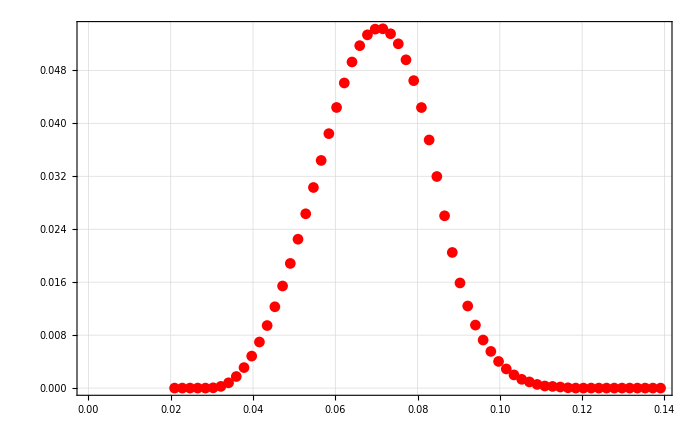

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormalSA[[All,2]]/Total[d0Spectruma01DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
da0Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],d0Spectruma01DNormalSA[[All,2]]/Total[d0Spectruma01DNormalSA[[All,2]]]}]];
```

## drA NoBeam 1D;

## a=-0.104

```mathematica
drASubFileNamesa10401DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1040_57-64.txt}

```mathematica
drASpectruma10401DNormalSA=Flatten[Table[Import[drASubFileNamesa10401DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa10401DNormalSA]}],1];
```

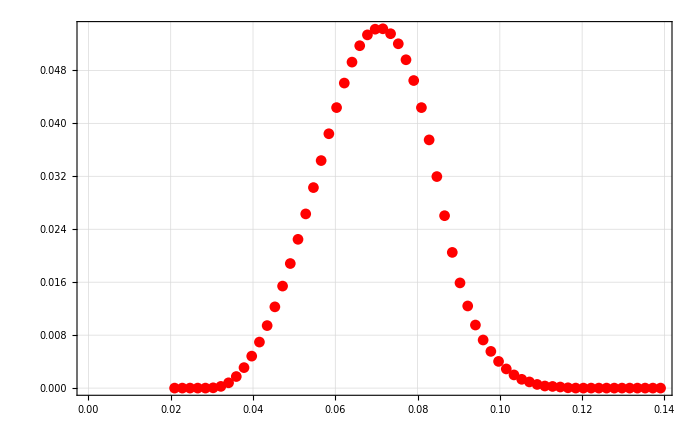

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10401DNormalSA[[All,2]]/Total[drASpectruma10401DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1040Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10401DNormalSA[[All,2]]/Total[drASpectruma10401DNormalSA[[All,2]]]}]];
```

## a=-0.1045

```mathematica
drASubFileNamesa10451DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_normal_smallApt_a-1045_57-64.txt}

```mathematica
drASpectruma10451DNormalSA=Flatten[Table[Import[drASubFileNamesa10451DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa10451DNormalSA]}],1];
```

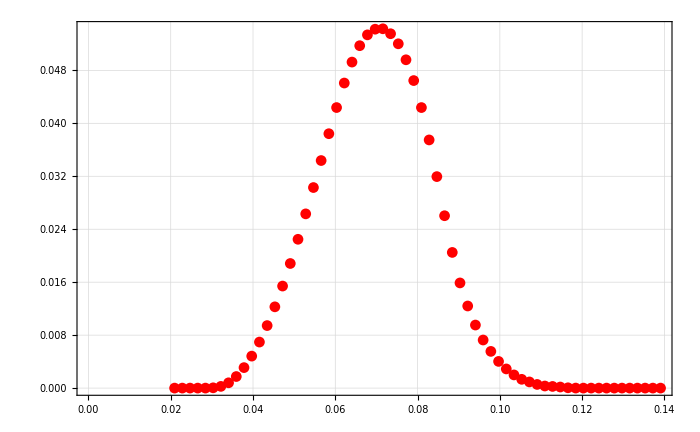

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10451DNormalSA[[All,2]]/Total[drASpectruma10451DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1045Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10451DNormalSA[[All,2]]/Total[drASpectruma10451DNormalSA[[All,2]]]}]];
```

## a=-0.105

```mathematica
SetDirectory[];
```

```mathematica
drASubFileNamesa01DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normal_smallApt_a-1050_57-64.txt}

```mathematica
drASpectruma01DNormalSA=Flatten[Table[Import[drASubFileNamesa01DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa01DNormalSA]}],1];
```

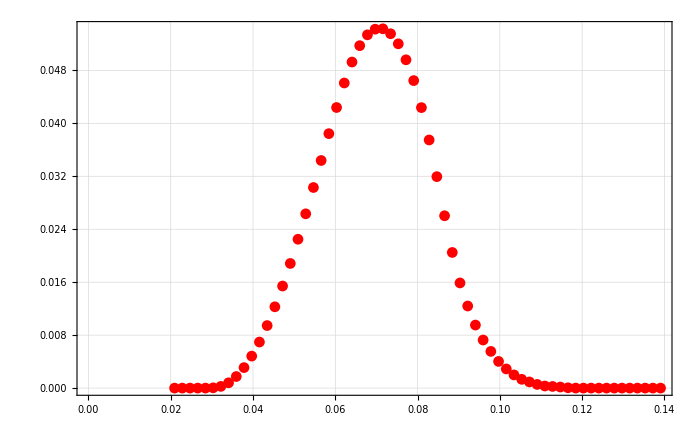

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma01DNormalSA[[All,2]]/Total[drASpectruma01DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drASpectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma01DNormalSA[[All,2]]/Total[drASpectruma01DNormalSA[[All,2]]]}]];
```

## a=-0.1055

```mathematica
SetDirectory[];
```

```mathematica
drASubFileNamesa10551DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1055_57-64.txt}

```mathematica
drASpectruma10551DNormalSA=Flatten[Table[Import[drASubFileNamesa10551DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa10551DNormalSA]}],1];
```

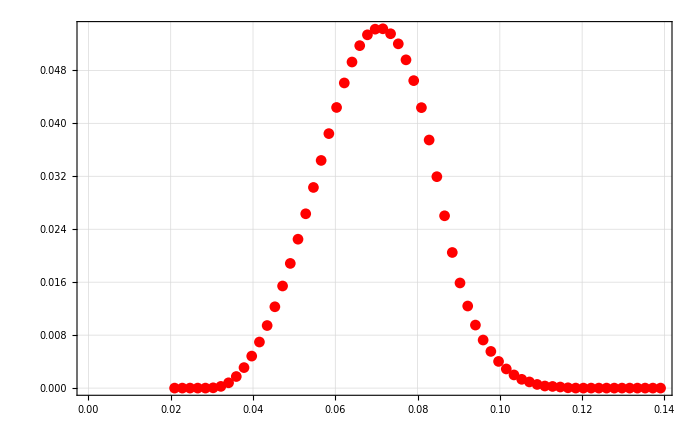

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10551DNormalSA[[All,2]]/Total[drASpectruma10551DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1055Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10551DNormalSA[[All,2]]/Total[drASpectruma10551DNormalSA[[All,2]]]}]];
```

### a=-1060

```mathematica
SetDirectory[];
```

```mathematica
drASubFileNamesa10601DNormalSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normal_smallApt/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_normal_smallApt_a-1060_57-64.txt}

```mathematica
drASpectruma10601DNormalSA=Flatten[Table[Import[drASubFileNamesa10601DNormalSA[[i]],"Table"],{i,1,Length[drASubFileNamesa10601DNormalSA]}],1];
```

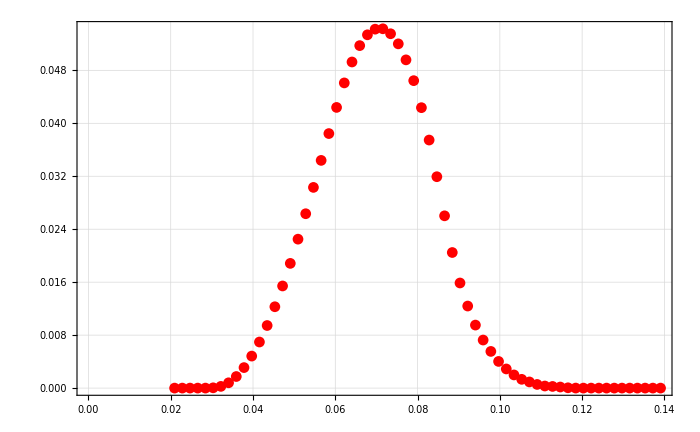

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10601DNormalSA[[All,2]]/Total[drASpectruma10601DNormalSA[[All,2]]]}],PlotStyle->Red]]
```

```mathematica
drAa1060Spectrum1DNormalSAInter=Interpolation[Transpose[{XYBinCentersYHalf1DNormal[[All,1]],drASpectruma10601DNormalSA[[All,2]]/Total[drASpectruma10601DNormalSA[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200025} lies outside the range of data in the interpolating function. Extrapolation will be used.

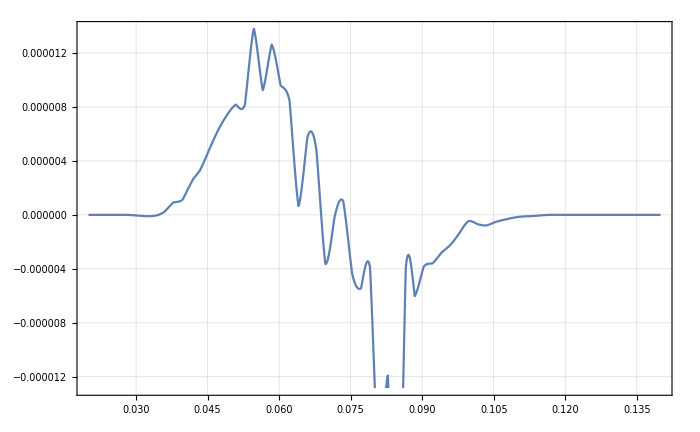

```mathematica
Show[Plot[drAa1060Spectrum1DNormalSAInter[x]-da0Spectrum1DNormalSAInter[x],{x,0.02,0.14}]]
```

InterpolatingFunction::dmval: Input value {0.0200025} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

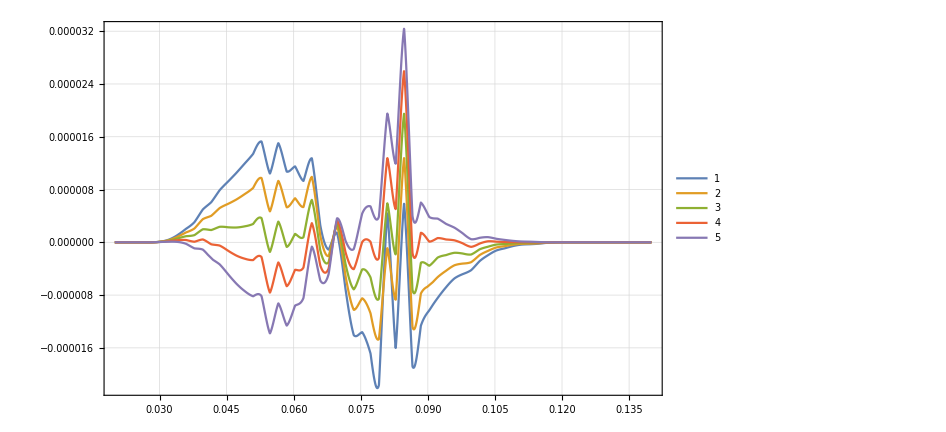

```mathematica
Plot[{
da0Spectrum1DNormalSAInter[x]-drAa1040Spectrum1DNormalSAInter[x],
da0Spectrum1DNormalSAInter[x]-drAa1045Spectrum1DNormalSAInter[x],
da0Spectrum1DNormalSAInter[x]-drASpectrum1DNormalSAInter[x],
da0Spectrum1DNormalSAInter[x]-drAa1055Spectrum1DNormalSAInter[x],
da0Spectrum1DNormalSAInter[x]-drAa1060Spectrum1DNormalSAInter[x]
}
,{x,0.02,0.14},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401DNormalSA[[All,2]]/Total[drASpectruma10401DNormalSA[[All,2]]],drASpectruma10451DNormalSA[[All,2]]/Total[drASpectruma10451DNormalSA[[All,2]]],drASpectruma01DNormalSA[[All,2]]/Total[drASpectruma01DNormalSA[[All,2]]],drASpectruma10551DNormalSA[[All,2]]/Total[drASpectruma10551DNormalSA[[All,2]]],drASpectruma10601DNormalSA[[All,2]]/Total[drASpectruma10601DNormalSA[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
drAInvest=TransferToRefParableFitForProtons[d0Spectruma01DNormalSA[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{4.05433×10^-9,1.80424×10^-9,8.24069×10^-10,1.113×10^-9,2.67759×10^-9},{3.29806×10^-10,2.22066×10^-10,1.51354×10^-10,1.6868×10^-10,2.56526×10^-10}},a0 =  | -0.105136
FittedModel[7.76703×10^-10+0.0025424 (0.105136+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105136 | 0.0000335187 | -3136.62 | 1.01643×10^-7
scale | 0.0025424 | 0.000252905 | 10.0528 | 0.00975073
yoffset | 7.76703×10^-10 | 1.16833×10^-10 | 6.64796 | 0.0218867 | 
 | DF | SS | MS
Model | 3 | 399.263 | 133.088
Error | 2 | 0.000112978 | 0.0000564888
Uncorrected Total | 5 | 399.264 | 
Corrected Total | 4 | 107.983 |  | ,-Graphics-}

```mathematica
((-0.1051356022629343+0.105)/-0.105)/(10^-4)
```

12.9145

```mathematica
71*.97
```

68.87

```mathematica
69/71.
```

0.971831

```mathematica
?rG
```

```mathematica
0.13-0.03
```

0.1

```mathematica
0.1/5
```

0.02

```mathematica
4*rG[pmax,45*Pi/180,0.22]+Dr
```

0.0509163

```mathematica
rG[pmax,45*Pi/180,0.976]
```

0.00286926

```mathematica
0.012+0.012
```

0.024

```mathematica
Solve[0.024/x==0.1/5,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1.2}}

```mathematica
Solve[0.0028692566237112946/x==rG[pmax,45*Pi/180,0.22]/10,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→2.2541}}

```mathematica
Solve[0.0028692566237112946/x==rG[pmax,45*Pi/180,0.22]/5,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1.12705}}

# Diff Neutron Beam prof

## da0 Big 1D xAASC=3.5/1000; yAASC=35/1000;

## da0 Needle3 1D, xaoffset=1cm, 1mmbeam xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle3/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle3=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle3_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle3=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle3[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle3]}],1];
```

```mathematica
xStart=0.01;
xEnd=0.03;
yStart=-0.022;
yEnd=0.025;
xyBins1D3=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D3=BinCenters[xyBins1D3];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D3[[All,1]],d0Spectruma01DdiffAptNeedle3[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
xAOffSC=10/1000;
yAOffSC=0;
{wnxSC, pnxSC, kx1SC, kx2SC, kx3SC, wnySC, pnySC, ky1SC, ky2SC, ky3SC}={0.001, 0.0009, 0.9, 0., -0.9, 0.001, 0.0009, 0.9, 0., -0.9}
```

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## da0 Needle5 1D, xoffset=3cm, 5mmbeam xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle5/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle5=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle5_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle5=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle5[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle5]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D5=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D5=BinCenters[xyBins1D5];
```

```mathematica
{wnxSC, pnxSC, kx1SC, kx2SC, kx3SC, wnySC, pnySC, ky1SC, ky2SC, ky3SC}={0.005, 0.004, 0.9, 0., -0.9, 0.005, 0.004, 0.9, 0., -0.9}
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle5[[All,2]]/d0Spectruma01DdiffAptNeedle2[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle5[[All,2]]-d0Spectruma01DdiffAptNeedle2[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle5[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle2[[All,2]]}],PlotStyle->Blue]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D5[[All,1]],d0Spectruma01DdiffAptNeedle5[[All,2]]/Total[d0Spectruma01DdiffAptNeedle5[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## da0 Needle6 1D, xoffset=-3cm, 1mmbeam xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle6/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle6=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle6_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle6=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle6[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle6]}],1];
```

```mathematica
xStart=-0.03;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBins1D6=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D6=BinCenters[xyBins1D6];
```

```mathematica
{wnxSC, pnxSC, kx1SC, kx2SC, kx3SC, wnySC, pnySC, ky1SC, ky2SC, ky3SC}={0.005, 0.004, 0.9, 0., -0.9, 0.005, 0.004, 0.9, 0., -0.9}
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D6[[All,1]],d0Spectruma01DdiffAptNeedle6[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## da0 Needle7 1D, xoffset=3cm, noBeam, xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle7/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle7=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle7_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle7=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle7[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle7]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D7=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D7=BinCenters[xyBins1D7];
```

```mathematica
0.06177146861111111+0.13738727291666666+0.21866247808333333+0.3541043168611111+0.4519762369722222+0.2981603826388889+0.13800345402777778+0.08953022125000001
```

1.7496

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D7[[All,1]],d0Spectruma01DdiffAptNeedle7[[All,2]]/Total[d0Spectruma01DdiffAptNeedle7[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Table[Timing[TrapezNBeamCompiledNormed[i,{0.06,0.059,0.9,0.,-0.9}]],{i,0.0,0.06,0.01}]
```

{{0.000028,16.8067},{5.×10^-6,16.8067},{5.×10^-6,16.8067},{4.×10^-6,0.},{4.×10^-6,0.},{3.×10^-6,0.},{3.×10^-6,0.}}

```mathematica
Table[Timing[TrapezNBeamNewNormed[i,{0.06,0.059,0.9,0.,-0.9}]],{i,0.0,0.06,0.01}]
```

{{0.017136,16.8067},{0.000038,16.8067},{0.000023,16.8067},{0.000021,0.},{0.00002,0.},{0.000018,0.},{0.000018,0.}}

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

```mathematica
?TrapezNBeamCompiledNormed
```

## da0 Needle4 1D, xoffset=-1cm, 1mm beam, xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle4/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle4=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle4_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle4=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle4[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle4]}],1];
```

```mathematica
xStart=-0.01;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBins1D4=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D4=BinCenters[xyBins1D4];
```

```mathematica
d0Spectruma01DdiffAptNeedle2[[All,2]]
```

{0.00236395,0.00531286,0.0100694,0.0170597,0.026696,0.0393775,0.0554899,0.0753921,0.0994249,0.12785,0.160658,0.197679,0.238598,0.283203,0.331096,0.381891,0.435307,0.490753,0.547889,0.606072,0.664797,0.722985,0.78086,0.837483,0.890444,0.941165,0.986064,1.02583,1.05885,1.08401,1.10048,1.10761,1.10533,1.09289,1.07055,1.0383,0.996428,0.945072,0.88512,0.819186,0.749028,0.676403,0.602919,0.530024,0.459441,0.392242,0.329932,0.273584,0.224449,0.182809,0.1483,0.119579,0.0954517,0.0753004,0.0579229,0.0440905,0.0329707,0.0240749,0.0171271,0.0117737,0.00775348,0.00484865,0.00282879,0.00151164}

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D4[[All,1]],d0Spectruma01DdiffAptNeedle4[[All,2]]/Total[d0Spectruma01DdiffAptNeedle4[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

```mathematica
xAOffSC=-10/1000;
yAOffSC=0;
{wnxSC,pnxSC,kx1SC,kx2SC,kx3SC,wnySC,pnySC,ky1SC,ky2SC,ky3SC}={0.001,0.0009,0.9,0.,-0.9,0.001,0.0009,0.9,0.,-0.9}
```

## da0 Needle2 1D xoffset=3cm, 1cm Beam xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle2/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_needle2_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle2=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle2[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle2]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
d0Spectruma01DdiffAptNeedle2[[All,2]]
```

{0.00236395,0.00531286,0.0100694,0.0170597,0.026696,0.0393775,0.0554899,0.0753921,0.0994249,0.12785,0.160658,0.197679,0.238598,0.283203,0.331096,0.381891,0.435307,0.490753,0.547889,0.606072,0.664797,0.722985,0.78086,0.837483,0.890444,0.941165,0.986064,1.02583,1.05885,1.08401,1.10048,1.10761,1.10533,1.09289,1.07055,1.0383,0.996428,0.945072,0.88512,0.819186,0.749028,0.676403,0.602919,0.530024,0.459441,0.392242,0.329932,0.273584,0.224449,0.182809,0.1483,0.119579,0.0954517,0.0753004,0.0579229,0.0440905,0.0329707,0.0240749,0.0171271,0.0117737,0.00775348,0.00484865,0.00282879,0.00151164}

```mathematica
xAASC=3.5/1000;
yAASC=35/1000;
xAOffSC=30/1000;
yAOffSC=0;
{wnxSC, pnxSC, kx1SC, kx2SC, kx3SC, wnySC, pnySC, ky1SC, ky2SC, ky3SC}={0.01, 0.009, 0.9, 0., -0.9, 0.01, 0.009, 0.9, 0., -0.9}
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffAptNeedle2[[All,2]]/Total[d0Spectruma01DdiffAptNeedle2[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

```mathematica
?rG
```

```mathematica
4rG[pmax,45*Pi/180,0.9]
```

0.0124462

```mathematica
0.02-4rG[pmax,45*Pi/180,0.9]
```

0.0075538

## da0 Needle 1D xAASC=3.5/1000; yAASC=35/1000;

```mathematica
?TrapezNBeamCompiledNormed
```

```mathematica
TrapezNBeamCompiledNormed[0.002,{0.5,0.49,0.9,0.,-0.9}]
```

2.0202

```mathematica
nplot=Plot[TrapezNBeamCompiledNormed[xn,{0.5,0.49,0.9,0.,-0.9}],{xn,-0.5,0.5},ImageSize->800,GridLines->Automatic,Frame->True,FrameStyle->25,FrameLabel->{{"n_x(x)",None},{"x (mm)",None}}]
```

-Graphics-

```mathematica
Plot[TrapezNBeamNewNormed[i,{6/100,5.9/100,0.9,0.,-0.9}],{i,-10/100,10/100}]
```

-Graphics-

```mathematica
nplot=Plot[TrapezNBeamNewNormed[xn,{1,0.9,0.9,0.,-0.9}],{xn,-10,10},ImageSize->800,GridLines->Automatic,Frame->True,FrameStyle->25,FrameLabel->{{"n_x(x)",None},{"x (mm)",None}}]
```

-Graphics-

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_needle/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffAptNeedle=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_needle_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_needle_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_needle_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_needle_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffAptNeedle=Flatten[Table[Import[d0SubFileNamesa01DdiffAptNeedle[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffAptNeedle]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
d0Spectruma01DdiffAptNeedle[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.12258,1.06402,1.00601,0.985874,0.914519,0.,0.,0.,0.627583,0.,0.,0.,0.,0.301889,0.206574,0.13549,0.0835913,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffAptNeedle[[All,2]]/Total[d0Spectruma01DdiffAptNeedle[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

```mathematica
?rG
```

```mathematica
4rG[pmax,45*Pi/180,0.9]
```

0.0124462

```mathematica
0.02-4rG[pmax,45*Pi/180,0.9]
```

0.0075538

## da0 Smaller 1D xAASC=3.5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_35mm2/a-1050/"];
```

```mathematica
d0SubFileNamesa01DdiffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm2_a-1050_57-64.txt}

```mathematica
d0Spectruma01DdiffApt=Flatten[Table[Import[d0SubFileNamesa01DdiffApt[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DdiffApt]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffApt[[All,2]]}]]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]-d0Spectruma01DdiffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffApt[[All,2]]}]],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## drA Smaller 1D xAASC=3.5/1000; yAASC=25/1000;

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1050/"];
```

```mathematica
drASubFileNamesa0diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1050_57-64.txt}

```mathematica
drASpectruma0diffApt=Flatten[Table[Import[drASubFileNamesa0diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa0diffApt]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma0diffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1040/"];
```

```mathematica
drASubFileNamesa1040diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_35mm2_a-1040_57-64.txt}

```mathematica
drASpectruma1040diffApt=Flatten[Table[Import[drASubFileNamesa1040diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa1040diffApt]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1040diffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1045/"];
```

```mathematica
drASubFileNamesa1045diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm2_a-1045_57-64.txt}

```mathematica
drASpectruma1045diffApt=Flatten[Table[Import[drASubFileNamesa1045diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa1045diffApt]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1045diffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1055/"];
```

```mathematica
drASubFileNamesa1055diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm2_a-1055_57-64.txt}

```mathematica
drASpectruma1055diffApt=Flatten[Table[Import[drASubFileNamesa1055diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa1055diffApt]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1055diffApt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm2/a-1060/"];
```

```mathematica
drASubFileNamesa1060diffApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_64x1y_35mm2_a-1060_57-64.txt}

```mathematica
drASpectruma1060diffApt=Flatten[Table[Import[drASubFileNamesa1060diffApt[[i]],"Table"],{i,1,Length[drASubFileNamesa1060diffApt]}],1];
```

```mathematica
RefSpectrumInterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffApt[[All,2]]/Total[d0Spectruma01DdiffApt[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInterdiffApt[x],{x,0.03,0.050},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
drASpectruma0InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma0diffApt[[All,2]]/Total[drASpectruma0diffApt[[All,2]]]}]];drASpectruma1040InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1040diffApt[[All,2]]/Total[drASpectruma1040diffApt[[All,2]]]}]];
drASpectruma1045InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1045diffApt[[All,2]]/Total[drASpectruma1045diffApt[[All,2]]]}]];
drASpectruma1055InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1055diffApt[[All,2]]/Total[drASpectruma1055diffApt[[All,2]]]}]];
drASpectruma1060InterdiffApt=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma1060diffApt[[All,2]]/Total[drASpectruma1060diffApt[[All,2]]]}]];
```

```mathematica
Show[Plot[drASpectruma1055InterdiffApt[x]-drASpectruma1045InterdiffApt[x],{x,0.03,0.050}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
RefSpectrumInterdiffApt[x]-drASpectruma1040InterdiffApt[x],
RefSpectrumInterdiffApt[x]-drASpectruma1045InterdiffApt[x],
RefSpectrumInterdiffApt[x]-drASpectruma1055InterdiffApt[x],
RefSpectrumInterdiffApt[x]-drASpectruma1060InterdiffApt[x],
RefSpectrumInterdiffApt[x]-drASpectruma0InterdiffApt[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma1040diffApt[[All,2]]/Total[drASpectruma1040diffApt[[All,2]]],drASpectruma1045diffApt[[All,2]]/Total[drASpectruma1045diffApt[[All,2]]],drASpectruma0diffApt[[All,2]]/Total[drASpectruma0diffApt[[All,2]]],drASpectruma1055diffApt[[All,2]]/Total[drASpectruma1055diffApt[[All,2]]],drASpectruma1060diffApt[[All,2]]/Total[drASpectruma1060diffApt[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
drAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01DdiffBeam[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0451×10^-8,6.8821×10^-9,4.11926×10^-9,2.17477×10^-9,1.02969×10^-9},{3.45933×10^-10,2.75173×10^-10,2.05032×10^-10,1.36219×10^-10,7.24851×10^-11}},a0 =  | -0.106449
FittedModel[7.07044×10^-10+0.00162055 (0.106449+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106449 | 0.00015402 | -691.143 | 2.09345×10^-6
scale | 0.00162055 | 0.00020177 | 8.0317 | 0.0151505
yoffset | 7.07044×10^-10 | 2.25201×10^-10 | 3.13962 | 0.0882291 | 
 | DF | SS | MS
Model | 3 | 2398.52 | 799.506
Error | 2 | 0.0150241 | 0.00751207
Uncorrected Total | 5 | 2398.53 | 
Corrected Total | 4 | 1198.89 |  | ,-Graphics-}

```mathematica
-0.1064494958980962
```

```mathematica
((-0.10644322321394499+0.105)/-0.105)
```

0.013745

```mathematica
0.013744982989952324*100
```

1.3745

```mathematica
10^-4*138.337
```

0.0138337

```mathematica
((-0.10644322321394499+0.105)/-0.105)/(10^-4)
```

137.45

```mathematica
((-0.1064494958980962+0.105)/-0.105)/(10^-4)
```

138.047

```mathematica
137.44982989952325*.106*10^-3
```

0.0145697

```mathematica
157.04*.106
```

16.6462

```mathematica
drASpectruma035mm[[All,2]]
```

{0.000109634,0.000244689,0.000461022,0.000777311,0.00121209,0.00178335,0.00250818,0.00340211,0.00448043,0.00575471,0.00722558,0.00888494,0.0107228,0.0127285,0.0148913,0.0171929,0.0196195,0.022156,0.024777,0.027458,0.0301701,0.0328825,0.0355405,0.0380881,0.0404864,0.0426895,0.0446593,0.0463404,0.047715,0.0487313,0.0493775,0.0496077,0.0494096,0.0487506,0.0476734,0.0461343,0.0441637,0.0417732,0.0390237,0.0360036,0.0328265,0.0295548,0.0262664,0.0230373,0.019903,0.0169486,0.0142265,0.0117794,0.00965522,0.00786194,0.00637475,0.00513286,0.00406537,0.00319984,0.00248339,0.00189357,0.00141485,0.00103349,0.000733169,0.000503669,0.000333821,0.000211115,0.000125457,0.0000691001}

```mathematica
normed2mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma02mm[[All,2]]/Total[drASpectruma02mm[[All,2]]]}];
```

```mathematica
normed10mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],-drASpectruma010mm[[All,2]]/Total[-drASpectruma010mm[[All,2]]]}];
```

```mathematica
normed35mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}];
```

```mathematica
normed35a0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]}];
```

```mathematica
normed10a0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]/Total[d0Spectruma01D10mm[[All,2]]]}];
```

```mathematica
normed2mma0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed2mma0[[All,2]]-normed2mmrA[[All,2]]}],PlotStyle->Blue],
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed35a0[[All,2]]-normed35mmrA[[All,2]]}],PlotStyle->Red],
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed10a0[[All,2]]-normed10mmrA[[All,2]]}],PlotStyle->Black]]
```

-Graphics-

```mathematica
Show[Plot[RefSpectrumInter2mm[x]-drASpectruma0Inter2mm[x],{x,0.03,0.05},PlotStyle->Blue],
Plot[RefSpectrumInter35mm[x]-drASpectruma0Inter35mm[x],{x,0.03,0.05},PlotStyle->Red],
Plot[RefSpectrumInter10mm[x]-drASpectruma0Inter10mm[x],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

# Diff Aperture

## da0 shifted0 1D xAASC=3.5/1000; yAASC=35/1000;

```mathematica
9/1000.
```

0.009

## a=-0.105

```mathematica
d0SubFileNamesa01Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_shifted0/a-1050/"];
```

```mathematica
d0Spectruma01Dshifted0=Flatten[Table[Import[d0SubFileNamesa01Dshifted0[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Dshifted0]}],1];
```

```mathematica
xStart=-0.012;
xEnd=0.008;
yStart=-0.022;
yEnd=0.025;
xyBins1Dshifted0=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
?bin2DGen
```

```mathematica
XYBinCentersYHalf1DShifted0=BinCenters[xyBins1Dshifted0];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],d0Spectruma01Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DShifted0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],d0Spectruma01Dshifted0[[All,2]]/Total[d0Spectruma01Dshifted0[[All,2]]]}]];
```

## drA shifted0 1D xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
drASubFileNamesa01Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1050/TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1050_57-64.txt}

```mathematica
drASpectruma01Dshifted0=Flatten[Table[Import[drASubFileNamesa01Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa01Dshifted0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectrum1DShifted0=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]]}]];
```

## a=-0.104

```mathematica
drASubFileNamesa10401Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1040/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1040_57-64.txt}

```mathematica
drASpectruma10401Dshifted0=Flatten[Table[Import[drASubFileNamesa10401Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa10401Dshifted0]}],1];
```

```mathematica
drASpectruma10401Dshifted0//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10401Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectrum1DShifted0=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]]}]];
```

## a=-0.1045

```mathematica
f2=Import["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/Old/TransferResult_08-09-20_SC_diffApt_G_drA_shifted0_a-1045_9*","Table"];
```

```mathematica
f2[[1,All,2]]
```

{0.00276363,0.00378161,0.0050171,0.00648566,0.00819611,0.0102033,0.0123796,0.0147684}

```mathematica
drASpectruma10451Dshifted0[[All,2]]
```

{4.31993×10^-6,0.0000290117,0.0000996045,0.000239182,0.000471039,0.00081791,0.00130187,0.00194347,0.00276363,0.00378161,0.0050171,0.00648566,0.00819611,0.0102033,0.0123796,0.0147684,0.0173553,0.0201244,0.023059,0.0261369,0.0293306,0.0326183,0.0359609,0.039303,0.042621,0.046477,0.0495702,0.0519479,0.0549908,0.0567179,0.0585672,0.0600057,0.0609857,0.0614794,0.0614434,0.0608814,0.059767,0.058091,0.055871,0.052912,0.0497015,0.046112,0.042254,0.0382613,0.0342057,0.0301793,0.0262604,0.0225211,0.0192631,0.0160543,0.013235,0.0108233,0.0088023,0.00700955,0.00562929,0.00446651,0.00349571,0.00269307,0.0020365,0.00150711,0.00108771,0.000763275,0.000517229,0.000338725}

```mathematica
drASubFileNamesa10451Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1045/TransferResult_08-09-20_SC_diffApt_C_drA_shifted0_a-1045_57-64.txt}

```mathematica
drASpectruma10451Dshifted0=Flatten[Table[Import[drASubFileNamesa10451Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa10451Dshifted0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10451Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectruma10451Dshifted0Inter=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10451Dshifted0[[All,2]]/Total[drASpectruma10451Dshifted0[[All,2]]]}]];
```

## a=-0.1055

```mathematica
drASubFileNamesa10551Dshifted0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1055/TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1055_57-64.txt}

```mathematica
drASpectruma10551Dshifted0=Flatten[Table[Import[drASubFileNamesa10551Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa10551Dshifted0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10551Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectrum1Da1055Shifted0=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma10551Dshifted0[[All,2]]/Total[drASpectruma10551Dshifted0[[All,2]]]}]];
```

## a=-0.106

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_shifted0/a-1060/"];
```

```mathematica
drASubFileNamesa10601Dshifted0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_shifted0_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_shifted0_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_shifted0_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_shifted0_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_shifted0_a-1060_57-64.txt}

```mathematica
drASpectruma01Dshifted0=Flatten[Table[Import[drASubFileNamesa01Dshifted0[[i]],"Table"],{i,1,Length[drASubFileNamesa01Dshifted0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]}]]
```

-Graphics-

```mathematica
drASpectrum1DShifted0=Interpolation[Transpose[{XYBinCentersYHalf1DShifted0[[All,1]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]]}]];
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,drADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10401Dshifted0[[All,2]]/Total[drASpectruma10401Dshifted0[[All,2]]],drASpectruma10451Dshifted0[[All,2]]/Total[drASpectruma10451Dshifted0[[All,2]]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]],drASpectruma10551Dshifted0[[All,2]]/Total[drASpectruma10551Dshifted0[[All,2]]],drASpectruma01Dshifted0[[All,2]]/Total[drASpectruma01Dshifted0[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.106}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
TransferToRefParableFitForProtons[RefTransfer_,TransferDataList_,ParaList_,Prec_]:=Module[{RefNorm=Total[RefTransfer],RefNormed,Sigma,TransferDataListNormed,Chi2List,dChi2List,errorplotdata,fitresult,fitfunc,bMin,bMax},bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransfer/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataList;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9 fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

```mathematica
drAInvest=TransferToRefParableFitForProtons[d0Spectruma01Dshifted0[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.68711×10^-7,2.66514×10^-7,1.59802×10^-7,1.57437×10^-7,1.59802×10^-7},{2.22297×10^-9,2.21909×10^-9,1.55562×10^-9,1.54192×10^-9,1.55562×10^-9}},a0 =  | -0.105729
FittedModel[1.54117×10^-7+0.0440443 (0.105729+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105729 | 0.0000314458 | -3362.25 | 8.84586×10^-8
scale | 0.0440443 | 0.00187893 | 23.4412 | 0.00181492
yoffset | 1.54117×10^-7 | 1.00436×10^-9 | 153.447 | 0.0000424671 | 
 | DF | SS | MS
Model | 3 | 59947.6 | 19982.5
Error | 2 | 618.972 | 309.486
Uncorrected Total | 5 | 60566.6 | 
Corrected Total | 4 | 3610.96 |  | ,-Graphics-}

```mathematica
((-0.10572859624129084+0.105)/-0.105)/(10^-4)
```

69.3901

```mathematica
(bA/bdv)/(brxb/bdv)
```

bA/brxb

```mathematica
Sqrt[1/2]==Sqrt[1]/Sqrt[2]
```

True

```mathematica
Simplify[1/Sqrt[1/2]]
```

√2

## da0 shifted 1D xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_shiftedApt/a-1050/"];
```

```mathematica
d0SubFileNamesa01DshiftedApt=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_shiftedApt_a-1050_57-64.txt}

```mathematica
d0Spectruma01DshiftedApt=Flatten[Table[Import[d0SubFileNamesa01DshiftedApt[[i]],"Table"],{i,1,Length[d0SubFileNamesa01DshiftedApt]}],1];
```

```mathematica
xStart=-0.022;
xEnd=-0.002;
yStart=-0.022;
yEnd=0.025;
xyBins1Dshifted=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1DShifted=BinCenters[xyBins1Dshifted];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1DShifted[[All,1]],d0Spectruma01DshiftedApt[[All,2]]}]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]]-0.05,d0Spectruma01D35mm[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1DShifted[[All,1]],d0Spectruma01DshiftedApt[[All,2]]}]],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]]-0.0516,d0Spectruma01D35mm2[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1DShifted[[All,1]],d0Spectruma01DshiftedApt[[All,2]]}]]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffAptBig[[All,2]]}],PlotStyle->Red]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffAptBig[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffApt[[All,2]]}]],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectrum1DdiffBeamInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DdiffBeam[[All,2]]/Total[d0Spectruma01DdiffBeam[[All,2]]]}]];
```

## da0 35mm2 1D xAASC=3.5/1000; yAASC=35/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_35mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D35mm2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D35mm2=Flatten[Table[Import[d0SubFileNamesa01D35mm2[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D35mm2]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/d0Spectruma01D35mm[[All,2]]}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/1.244}]],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalf1D7[[All,1]],d0Spectruma01DdiffAptNeedle7[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D35mm2[[All,2]]-d0Spectruma01DdiffAptNeedle7[[All,2]])/d0Spectruma01D35mm2[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]]}]],ListPlot[Transpose[{XYBinCentersYHalf1D7[[All,1]],d0Spectruma01DdiffAptNeedle7[[All,2]]/Total[d0Spectruma01DdiffAptNeedle7[[All,2]]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]]-d0Spectruma01DdiffAptNeedle7[[All,2]]/Total[d0Spectruma01DdiffAptNeedle7[[All,2]]])/(d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]])}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]]-d0Spectruma01DdiffAptNeedle7[[All,2]]/Total[d0Spectruma01DdiffAptNeedle7[[All,2]]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1D35mm2=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm2[[All,2]]/Total[d0Spectruma01D35mm2[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=2/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_2mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D2mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D2mm=Flatten[Table[Import[d0SubFileNamesa01D2mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D2mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1D2mmInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_2mm/a1050/"];
```

```mathematica
d0SubFileNamesa01D2mma1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_57-64.txt}

```mathematica
d0Spectruma01D2mma1050=Flatten[Table[Import[d0SubFileNamesa01D2mma1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D2mma1050]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-d0Spectruma01D2mma1050[[All,2]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
da0Spectrum1D2mmIntera1050=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mma1050[[All,2]]/Total[d0Spectruma01D2mma1050[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=4/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_4mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D4mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_da0_64x1y_4mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D4mm=Flatten[Table[Import[d0SubFileNamesa01D4mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D4mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-d0Spectruma01D4mm[[All,2]]}]]
```

-Graphics-

```mathematica
d0Spectruma01D4mm[[All,2]]
```

{-0.000216332,-0.000417411,-0.000715287,-0.00112842,-0.00167508,-0.0023725,-0.00323646,-0.00428214,-0.00552322,-0.00697207,-0.00863762,-0.010515,-0.0125944,-0.0148635,-0.0173064,-0.0199071,-0.02265,-0.0255144,-0.0284588,-0.0314697,-0.0345064,-0.0375234,-0.0404549,-0.0432631,-0.0458957,-0.0483093,-0.0504556,-0.0523012,-0.0537939,-0.0549072,-0.0555969,-0.0558407,-0.0555885,-0.0548316,-0.0535904,-0.051826,-0.0495936,-0.0469195,-0.0438957,-0.0406302,-0.0372054,-0.0336948,-0.0301521,-0.0266518,-0.0232365,-0.0199789,-0.0169181,-0.0141342,-0.0116471,-0.0095032,-0.00771046,-0.00622339,-0.00498641,-0.00393215,-0.00307441,-0.00237368,-0.00180097,-0.00134024,-0.000973584,-0.000685355,-0.000469192,-0.000308437,-0.000192944,-0.000113361}

```mathematica
da0Spectrum1DInter4mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D4mm[[All,2]]/Total[d0Spectruma01D4mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_4mm/a1050/"];
```

```mathematica
d0SubFileNamesa01Da10504mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_4mm_a1050_57-64.txt}

```mathematica
d0Spectruma01D4mma1050=Flatten[Table[Import[d0SubFileNamesa01Da10504mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da10504mm]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

1/16 Total[Symbol[]]

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D4mma1050[[All,2]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DInter4mma1050=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D4mma1050[[All,2]]/Total[d0Spectruma01D4mma1050[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y/a-1050/"];
```

```mathematica
d0SubFileNamesa01D=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_57-64.txt}

```mathematica
d0Spectruma01D=Flatten[Table[Import[d0SubFileNamesa01D[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]/Total[d0Spectruma01D[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y/a1050/"];
```

```mathematica
d0SubFileNamesa01Da1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_57-64.txt}

```mathematica
d0Spectruma01Da1050=Flatten[Table[Import[d0SubFileNamesa01Da1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da1050]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da1050[[All,2]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DIntera1050=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da1050[[All,2]]/Total[d0Spectruma01Da1050[[All,2]]]}]];
```

## drA Smaller 1D xAASC=10/1000; yAASC=25/1000;

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1050/"];
```

```mathematica
drASubFileNamesa010mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_10mm_a-1050_57-64.txt}

```mathematica
drASpectruma010mm=Flatten[Table[Import[drASubFileNamesa010mm[[i]],"Table"],{i,1,Length[drASubFileNamesa010mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-drASpectruma010mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1040/"];
```

```mathematica
drASubFileNamesa104010mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1040_57-64.txt}

```mathematica
drASpectruma104010mm=Flatten[Table[Import[drASubFileNamesa104010mm[[i]],"Table"],{i,1,Length[drASubFileNamesa104010mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104010mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1045/"];
```

```mathematica
drASubFileNamesa104510mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_10mm_a-1045_57-64.txt}

```mathematica
drASpectruma104510mm=Flatten[Table[Import[drASubFileNamesa104510mm[[i]],"Table"],{i,1,Length[drASubFileNamesa104510mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104510mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1055/"];
```

```mathematica
drASubFileNamesa105510mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1055_57-64.txt}

```mathematica
drASpectruma105510mm=Flatten[Table[Import[drASubFileNamesa105510mm[[i]],"Table"],{i,1,Length[drASubFileNamesa105510mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105510mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_10mm/a-1060/"];
```

```mathematica
drASubFileNamesa106010mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_10mm_a-1060_57-64.txt}

```mathematica
drASpectruma106010mm=Flatten[Table[Import[drASubFileNamesa106010mm[[i]],"Table"],{i,1,Length[drASubFileNamesa106010mm]}],1];
```

```mathematica
RefSpectrumInter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]/Total[d0Spectruma01D10mm[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter10mm[x],{x,0.03,0.050},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
drASpectruma0Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma010mm[[All,2]]/Total[drASpectruma010mm[[All,2]]]}]];drASpectruma1040Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104010mm[[All,2]]/Total[drASpectruma104010mm[[All,2]]]}]];
drASpectruma1045Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104510mm[[All,2]]/Total[drASpectruma104510mm[[All,2]]]}]];
drASpectruma1055Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105510mm[[All,2]]/Total[drASpectruma105510mm[[All,2]]]}]];
drASpectruma1060Inter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma106010mm[[All,2]]/Total[drASpectruma106010mm[[All,2]]]}]];
```

```mathematica
Show[Plot[drASpectruma1055Inter10mm[x]-drASpectruma1045Inter10mm[x],{x,0.03,0.050}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
RefSpectrumInter10mm[x]-drASpectruma1040Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1045Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1055Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1060Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma0Inter10mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
drASpectruma104035mmRemv=Join[drASpectruma104035mm[[All,2]][[1;;51]],drASpectruma104035mm[[All,2]][[53;;]]];drASpectruma104535mmRemv=Join[drASpectruma104535mm[[All,2]][[1;;51]],drASpectruma104535mm[[All,2]][[53;;]]];
drASpectruma105035mmRemv=Join[drASpectruma035mm[[All,2]][[1;;51]],drASpectruma035mm[[All,2]][[53;;]]];
drASpectruma105535mmRemv=Join[drASpectruma105535mm[[All,2]][[1;;51]],drASpectruma105535mm[[All,2]][[53;;]]];drASpectruma106035mmRemv=Join[drASpectruma106035mm[[All,2]][[1;;51]],drASpectruma106035mm[[All,2]][[53;;]]];
refSpectra35mmRemv=Join[d0Spectruma01D35mm[[All,2]][[1;;51]],d0Spectruma01D35mm[[All,2]][[53;;]]];
```

```mathematica
ListPlot[drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]-drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]]}],Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]-drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]]}],
Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}],
Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}]},PlotRange->All]
```

-Graphics-

```mathematica
97*.1
```

9.7

```mathematica
0.0097*100
```

0.97

```mathematica
ListPlot[{d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]}]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList2={drASpectruma104035mmRemv/Total[drASpectruma104035mmRemv],drASpectruma104535mmRemv/Total[drASpectruma104535mmRemv],drASpectruma105035mmRemv/Total[drASpectruma105035mmRemv],drASpectruma105535mmRemv/Total[drASpectruma105535mmRemv],drASpectruma106035mmRemv/Total[drASpectruma106035mmRemv]};
```

```mathematica
drADataList={drASpectruma104010mm[[All,2]]/Total[drASpectruma104010mm[[All,2]]],drASpectruma104510mm[[All,2]]/Total[drASpectruma104510mm[[All,2]]],drASpectruma010mm[[All,2]]/Total[drASpectruma010mm[[All,2]]],drASpectruma105510mm[[All,2]]/Total[drASpectruma105510mm[[All,2]]],drASpectruma106010mm[[All,2]]/Total[drASpectruma106010mm[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
drAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01D10mm[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.72851×10^-9,2.46631×10^-9,1.47745×10^-9,7.64573×10^-10,3.06681×10^-10},{1.46972×10^-10,1.2088×10^-10,9.55324×10^-11,7.15814×10^-11,4.98497×10^-11}},a0 =  | -0.106511
FittedModel[1.66409×10^-10+0.000568555 (0.106511+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106511 | 0.000235605 | -452.073 | 4.89304×10^-6
scale | 0.000568555 | 0.0000984328 | 5.77607 | 0.0286897
yoffset | 1.66409×10^-10 | 1.43995×10^-10 | 1.15566 | 0.36723 | 
 | DF | SS | MS
Model | 3 | 1450.85 | 483.616
Error | 2 | 0.126455 | 0.0632274
Uncorrected Total | 5 | 1450.98 | 
Corrected Total | 4 | 718.459 |  | ,-Graphics-}

```mathematica
((-0.10651082268604328+0.105)/-0.105)
```

0.0143888

```mathematica
0.014388787486126538*100
```

1.43888

```mathematica
((-0.10651082268604328+0.105)/-0.105)/(10^-4)
```

143.888

## drA Smaller 1D xAASC=2/1000; yAASC=25/1000;

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1050/"];
```

```mathematica
drASubFileNamesa02mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1050_57-64.txt}

```mathematica
drASpectruma02mm=Flatten[Table[Import[drASubFileNamesa02mm[[i]],"Table"],{i,1,Length[drASubFileNamesa02mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma02mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1040/"];
```

```mathematica
drASubFileNamesa10402mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_2mm_a-1040_57-64.txt}

```mathematica
drASpectruma10402mm=Flatten[Table[Import[drASubFileNamesa10402mm[[i]],"Table"],{i,1,Length[drASubFileNamesa10402mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-drASpectruma10402mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1045/"];
```

```mathematica
drASubFileNamesa10452mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_64x1y_2mm_a-1045_57-64.txt}

```mathematica
drASpectruma10452mm=Flatten[Table[Import[drASubFileNamesa10452mm[[i]],"Table"],{i,1,Length[drASubFileNamesa10452mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10452mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1055/"];
```

```mathematica
drASubFileNamesa10552mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1055_57-64.txt}

```mathematica
drASpectruma10552mm=Flatten[Table[Import[drASubFileNamesa10552mm[[i]],"Table"],{i,1,Length[drASubFileNamesa10552mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10552mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_2mm/a-1060/"];
```

```mathematica
drASubFileNamesa10602mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_2mm_a-1060_57-64.txt}

```mathematica
drASpectruma10602mm=Flatten[Table[Import[drASubFileNamesa10602mm[[i]],"Table"],{i,1,Length[drASubFileNamesa10602mm]}],1];
```

```mathematica
RefSpectrumInter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter2mm[x],{x,0.03,0.050},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
drASpectruma0Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma02mm[[All,2]]/Total[drASpectruma02mm[[All,2]]]}]];drASpectruma1040Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10402mm[[All,2]]/Total[drASpectruma10402mm[[All,2]]]}]];
drASpectruma1045Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10452mm[[All,2]]/Total[drASpectruma10452mm[[All,2]]]}]];
drASpectruma1055Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10552mm[[All,2]]/Total[drASpectruma10552mm[[All,2]]]}]];
drASpectruma1060Inter2mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma10602mm[[All,2]]/Total[drASpectruma10602mm[[All,2]]]}]];
```

```mathematica
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]-drASpectruma02mm[[All,2]]}]]
```

-Graphics-

```mathematica
Show[Plot[drASpectruma1055Inter2mm[x]-drASpectruma1045Inter2mm[x],{x,0.03,0.050}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
thirtyfiveDiff=Plot[{
RefSpectrumInter35mm[x]-drASpectruma1040Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1045Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1055Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1060Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma0Inter35mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
tenmmDiff=Plot[{
RefSpectrumInter10mm[x]-drASpectruma1040Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1045Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1055Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma1060Inter10mm[x],
RefSpectrumInter10mm[x]-drASpectruma0Inter10mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
twommDiff=Plot[{
RefSpectrumInter2mm[x]-drASpectruma1040Inter2mm[x],
RefSpectrumInter2mm[x]-drASpectruma1045Inter2mm[x],
RefSpectrumInter2mm[x]-drASpectruma1055Inter2mm[x],
RefSpectrumInter2mm[x]-drASpectruma1060Inter2mm[x],
RefSpectrumInter2mm[x]-drASpectruma0Inter2mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
imageWrite[twommDiff];imageWrite[tenmmDiff];imageWrite[thirtyfiveDiff];
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList={drASpectruma10402mm[[All,2]]/Total[drASpectruma10402mm[[All,2]]],drASpectruma10452mm[[All,2]]/Total[drASpectruma10452mm[[All,2]]],drASpectruma02mm[[All,2]]/Total[drASpectruma02mm[[All,2]]],drASpectruma10552mm[[All,2]]/Total[drASpectruma10552mm[[All,2]]],drASpectruma10602mm[[All,2]]/Total[drASpectruma10602mm[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
drAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01D2mm[[All,2]],drADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.1211×10^-8,7.21606×10^-9,4.15507×10^-9,2.22615×10^-9,9.30743×10^-10},{3.68964×10^-10,2.91435×10^-10,2.16017×10^-10,1.54344×10^-10,1.01924×10^-10}},a0 =  | -0.106416
FittedModel[6.34165×10^-10+0.00179091 (0.106416+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106416 | 0.000155452 | -684.555 | 2.13394×10^-6
scale | 0.00179091 | 0.000225641 | 7.93696 | 0.0155059
yoffset | 6.34165×10^-10 | 2.59716×10^-10 | 2.44176 | 0.13466 | 
 | DF | SS | MS
Model | 3 | 2197.16 | 732.388
Error | 2 | 0.577262 | 0.288631
Uncorrected Total | 5 | 2197.74 | 
Corrected Total | 4 | 1117.84 |  | ,-Graphics-}

```mathematica
err={{3.1928781315237865*^-6,3.231480211902923*^-6,3.270832502237184*^-6,3.3105244265165438*^-6,3.3502556708866684*^-6},{5.628069399000864*^-9,5.666363422511431*^-9,5.704809601381051*^-9,5.742886499101549*^-9,5.781153327827049*^-9}}
```

{{3.19288×10^-6,3.23148×10^-6,3.27083×10^-6,3.31052×10^-6,3.35026×10^-6},{5.62807×10^-9,5.66636×10^-9,5.70481×10^-9,5.74289×10^-9,5.78115×10^-9}}

```mathematica
errList=Table[Around[err[[1,i]],err[[2,i]]],{i,Length[err[[1]]]}]
```

{3.1930.00610^-6,3.2310.00610^-6,3.2710.00610^-6,3.3110.00610^-6,3.3500.00610^-6}

```mathematica
errData=Transpose[{{-0.0015,-0.00075,0.,0.00075,0.0015},err[[1]]}]
```

{{-0.0015,3.19288×10^-6},{-0.00075,3.23148×10^-6},{0.,3.27083×10^-6},{0.00075,3.31052×10^-6},{0.0015,3.35026×10^-6}}

```mathematica
err[[1]]
```

{3.19288×10^-6,3.23148×10^-6,3.27083×10^-6,3.31052×10^-6,3.35026×10^-6}

```mathematica
lm=LinearModelFit[errData,{1,x},x,Weights->1/err[[2]]^2]
```

FittedModel[3.27119×10^-6+0.0000525019 x]

```mathematica
linearFitrAFierz=Show[Plot[lm[x],{x,-0.0015,0.0015},PlotStyle->Red],ListPlot[Transpose[{{-0.0015,-0.00075,0.,0.00075,0.0015},errList}]]]
```

-Graphics-

```mathematica
imageWrite[linearFitrAFierz]
```

```mathematica
((-0.10641564931594331+0.105)/-0.105)
```

0.0134824

```mathematica
0.014388787486126538*100
```

1.43888

```mathematica
((-0.10641564931594331+0.105)/-0.105)/(10^-4)
```

134.824

## drA Smaller 1D xAASC=3.5/1000; yAASC=25/1000;

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1050/"];
```

```mathematica
drASubFileNamesa035mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1050_57-64.txt}

```mathematica
drASpectruma035mm=Flatten[Table[Import[drASubFileNamesa035mm[[i]],"Table"],{i,1,Length[drASubFileNamesa035mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1040/"];
```

```mathematica
drASubFileNamesa104035mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1040_57-64.txt}

```mathematica
drASpectruma104035mm=Flatten[Table[Import[drASubFileNamesa104035mm[[i]],"Table"],{i,1,Length[drASubFileNamesa104035mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104035mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1075

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1075/"];
```

```mathematica
drASubFileNamesa107535mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_64x1y_35mm_a-1075_57-64.txt}

```mathematica
drASpectruma107535mm=Flatten[Table[Import[drASubFileNamesa107535mm[[i]],"Table"],{i,1,Length[drASubFileNamesa107535mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma107535mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1045/"];
```

```mathematica
drASubFileNamesa104535mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1045_57-64.txt}

```mathematica
drASpectruma104535mm=Flatten[Table[Import[drASubFileNamesa104535mm[[i]],"Table"],{i,1,Length[drASubFileNamesa104535mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104535mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1055/"];
```

```mathematica
drASubFileNamesa105535mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1055_57-64.txt}

```mathematica
drASpectruma105535mm=Flatten[Table[Import[drASubFileNamesa105535mm[[i]],"Table"],{i,1,Length[drASubFileNamesa105535mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105535mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_64x1y_35mm/a-1060/"];
```

```mathematica
drASubFileNamesa106035mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_64x1y_35mm_a-1060_57-64.txt}

```mathematica
drASpectruma106035mm=Flatten[Table[Import[drASubFileNamesa106035mm[[i]],"Table"],{i,1,Length[drASubFileNamesa106035mm]}],1];
```

```mathematica
RefSpectrumInter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter35mm[x],{x,0.03,0.050},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
drASpectruma0Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}]];drASpectruma1040Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]]}]];
drASpectruma1045Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]]}]];
drASpectruma1055Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]}]];
drASpectruma1060Inter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]}]];
```

```mathematica
Show[Plot[drASpectruma1055Inter35mm[x]-drASpectruma1045Inter35mm[x],{x,0.03,0.050}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
diffPlot2mm=Plot[{
d0Spectruma0Inter2mm[x]-drASpectruma1040Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1045Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1055Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1060Inter2mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->{"-0.1040","-0.1045","-0.1055","-0.1060"}]
```

```mathematica
diffPlot2mm=Plot[{
drASpectruma0Inter2mm[x]-drASpectruma1040Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1045Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1055Inter2mm[x],
drASpectruma0Inter2mm[x]-drASpectruma1060Inter2mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->{"-0.1040","-0.1045","-0.1055","-0.1060"}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
diffPlot10mm=Plot[{
drASpectruma0Inter10mm[x]-drASpectruma1040Inter10mm[x],
drASpectruma0Inter10mm[x]-drASpectruma1045Inter10mm[x],
drASpectruma0Inter10mm[x]-drASpectruma1055Inter10mm[x],
drASpectruma0Inter10mm[x]-drASpectruma1060Inter10mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->{"-0.1040","-0.1045","-0.1055","-0.1060"}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
diffPlot=Plot[{
drASpectruma0Inter35mm[x]-drASpectruma1040Inter35mm[x],
drASpectruma0Inter35mm[x]-drASpectruma1045Inter35mm[x],
drASpectruma0Inter35mm[x]-drASpectruma1055Inter35mm[x],
drASpectruma0Inter35mm[x]-drASpectruma1060Inter35mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->{"-0.1040","-0.1045","-0.1055","-0.1060"}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
imageWrite[diffPlot]
```

```mathematica
imageWrite[diffPlot10mm];imageWrite[diffPlot2mm];
```

```mathematica
|
```

```mathematica
Plot[{
RefSpectrumInter35mm[x]-drASpectruma1040Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1045Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1055Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma1060Inter35mm[x],
RefSpectrumInter35mm[x]-drASpectruma0Inter35mm[x]
}
,{x,0.03,0.050},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
drASpectruma104035mmRemv=Join[drASpectruma104035mm[[All,2]][[1;;51]],drASpectruma104035mm[[All,2]][[53;;]]];drASpectruma104535mmRemv=Join[drASpectruma104535mm[[All,2]][[1;;51]],drASpectruma104535mm[[All,2]][[53;;]]];
drASpectruma105035mmRemv=Join[drASpectruma035mm[[All,2]][[1;;51]],drASpectruma035mm[[All,2]][[53;;]]];
drASpectruma105535mmRemv=Join[drASpectruma105535mm[[All,2]][[1;;51]],drASpectruma105535mm[[All,2]][[53;;]]];drASpectruma106035mmRemv=Join[drASpectruma106035mm[[All,2]][[1;;51]],drASpectruma106035mm[[All,2]][[53;;]]];
refSpectra35mmRemv=Join[d0Spectruma01D35mm[[All,2]][[1;;51]],d0Spectruma01D35mm[[All,2]][[53;;]]];
```

```mathematica
ListPlot[drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]]
```

-Graphics-

```mathematica
ListLinePlot[{Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]-drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]]}],Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]-drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]]}],
Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}],
Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}]},PlotRange->All]
```

-Graphics-

```mathematica
97*.1
```

9.7

```mathematica
0.0097*100
```

0.97

```mathematica
diff35mmaValsrA=ListPlot[{d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]-drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]]}]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
drADataList2={drASpectruma104035mmRemv/Total[drASpectruma104035mmRemv],drASpectruma104535mmRemv/Total[drASpectruma104535mmRemv],drASpectruma105035mmRemv/Total[drASpectruma105035mmRemv],drASpectruma105535mmRemv/Total[drASpectruma105535mmRemv],drASpectruma106035mmRemv/Total[drASpectruma106035mmRemv]};
```

```mathematica
drADataList={drASpectruma104035mm[[All,2]]/Total[drASpectruma104035mm[[All,2]]],drASpectruma104535mm[[All,2]]/Total[drASpectruma104535mm[[All,2]]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]],drASpectruma105535mm[[All,2]]/Total[drASpectruma105535mm[[All,2]]],drASpectruma106035mm[[All,2]]/Total[drASpectruma106035mm[[All,2]]],drASpectruma107535mm[[All,2]]/Total[drASpectruma107535mm[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060,-0.1075}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1075}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
TransferToRefParableFitForProtons[RefTransfer_,TransferDataList_,ParaList_,Prec_]:=Module[{RefNorm=Total[RefTransfer],RefNormed,Sigma,TransferDataListNormed,Chi2List,dChi2List,errorplotdata,fitresult,fitfunc,bMin,bMax},bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransfer/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataList;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->1000];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9 fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

```mathematica
TransferToRefParableFitForProtonsUnlimited
```

TransferToRefParableFitForProtonsUnlimited

```mathematica
chi2List2=Transpose[{bList,{1.0506630519124637*^-8,6.9175548163778236*^-9,4.139569226722818*^-9,2.1850233817621848*^-9,1.0347335648281713*^-9}}]
```

{{-0.104,1.05066×10^-8},{-0.1045,6.91755×10^-9},{-0.105,4.13957×10^-9},{-0.1055,2.18502×10^-9},{-0.106,1.03473×10^-9}}

```mathematica
err={3.493772257773241*^-10,2.779119417135372*^-10,2.070704066129087*^-10,1.3756243875324397*^-10,7.313368896176667*^-11};
```

```mathematica
lm=LinearModelFit[chi2List2,{1,x,x^2},x,Weights->1/err^2]
```

FittedModel[0.0000184315+0.000346262 x+0.00162632 x^2]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0000184315 | 4.21784×10^-8 | 436.988 | 5.23669×10^-6
x | 0.000346262 | 8.0154×10^-7 | 431.995 | 5.35844×10^-6
x^2 | 0.00162632 | 3.8079×10^-6 | 427.09 | 5.48224×10^-6

```mathematica
(Re[x/.Solve[lm[x]==0][[1,1]]]+0.105)/-0.105
```

0.0138639

```mathematica
drAInvest2=TransferToRefParableFitForProtonsUnlimited[refSpectra35mmRemv,drADataList2,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.05066×10^-8,6.91755×10^-9,4.13957×10^-9,2.18502×10^-9,1.03473×10^-9},{3.49377×10^-10,2.77912×10^-10,2.0707×10^-10,1.37562×10^-10,7.31337×10^-11}},a0 =  | -0.106443
FittedModel[7.02156×10^-10+0.00165465 (0.106443+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106443 | 0.000151566 | -702.289 | 2.02753×10^-6
scale | 0.00165465 | 0.000203753 | 8.12084 | 0.014827
yoffset | 7.02156×10^-10 | 2.24343×10^-10 | 3.12984 | 0.0887102 | 
 | DF | SS | MS
Model | 3 | 2375.97 | 791.99
Error | 2 | 0.0757909 | 0.0378955
Uncorrected Total | 5 | 2376.05 | 
Corrected Total | 4 | 1188.15 |  | ,-Graphics-}

```mathematica
1.60/0.016
```

100.

```mathematica
0.1*0.016
```

0.0016

```mathematica
1.62*100
```

162.

```mathematica
drAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma01D35mm[[All,2]],drADataList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0451×10^-8,6.8821×10^-9,4.11926×10^-9,2.17477×10^-9,1.02969×10^-9,2.47756×10^-9},{3.45933×10^-10,2.75173×10^-10,2.05032×10^-10,1.36219×10^-10,7.24851×10^-11,1.63215×10^-10}},a0 =  | -0.106453
FittedModel[6.9989×10^-10+0.00162095 (0.106453+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106453 | 0.0000276602 | -3848.58 | 3.86872×10^-11
scale | 0.00162095 | 0.0000565004 | 28.6892 | 0.0000929865
yoffset | 6.9989×10^-10 | 7.16431×10^-11 | 9.76912 | 0.00227908 | 
 | DF | SS | MS
Model | 3 | 2628.96 | 876.319
Error | 3 | 0.00192802 | 0.000642673
Uncorrected Total | 6 | 2628.96 | 
Corrected Total | 5 | 1205.39 |  | ,-Graphics-}

```mathematica
((-0.10644322321394499+0.105)/-0.105)
```

0.013745

```mathematica
0.013744982989952324*100
```

1.3745

```mathematica
10^-4*138.337
```

0.0138337

```mathematica
((-0.10644322321394499+0.105)/-0.105)/(10^-4)
```

137.45

```mathematica
((-0.1064494958980962+0.105)/-0.105)/(10^-4)
```

138.047

```mathematica
137.44982989952325*.106*10^-3
```

0.0145697

```mathematica
157.04*.106
```

16.6462

```mathematica
drASpectruma035mm[[All,2]]
```

{0.000109634,0.000244689,0.000461022,0.000777311,0.00121209,0.00178335,0.00250818,0.00340211,0.00448043,0.00575471,0.00722558,0.00888494,0.0107228,0.0127285,0.0148913,0.0171929,0.0196195,0.022156,0.024777,0.027458,0.0301701,0.0328825,0.0355405,0.0380881,0.0404864,0.0426895,0.0446593,0.0463404,0.047715,0.0487313,0.0493775,0.0496077,0.0494096,0.0487506,0.0476734,0.0461343,0.0441637,0.0417732,0.0390237,0.0360036,0.0328265,0.0295548,0.0262664,0.0230373,0.019903,0.0169486,0.0142265,0.0117794,0.00965522,0.00786194,0.00637475,0.00513286,0.00406537,0.00319984,0.00248339,0.00189357,0.00141485,0.00103349,0.000733169,0.000503669,0.000333821,0.000211115,0.000125457,0.0000691001}

```mathematica
normed2mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma02mm[[All,2]]/Total[drASpectruma02mm[[All,2]]]}];
```

```mathematica
normed10mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],-drASpectruma010mm[[All,2]]/Total[-drASpectruma010mm[[All,2]]]}];
```

```mathematica
normed35mmrA=Transpose[{XYBinCentersYHalf1D[[All,1]],drASpectruma035mm[[All,2]]/Total[drASpectruma035mm[[All,2]]]}];
```

```mathematica
normed35a0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]}];
```

```mathematica
normed10a0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]/Total[d0Spectruma01D10mm[[All,2]]]}];
```

```mathematica
normed2mma0=Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed2mma0[[All,2]]-normed2mmrA[[All,2]]}],PlotStyle->Blue],
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed35a0[[All,2]]-normed35mmrA[[All,2]]}],PlotStyle->Red],
ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],normed10a0[[All,2]]-normed10mmrA[[All,2]]}],PlotStyle->Black]]
```

-Graphics-

```mathematica
Show[Plot[RefSpectrumInter2mm[x]-drASpectruma0Inter2mm[x],{x,0.03,0.05},PlotStyle->Blue],
Plot[RefSpectrumInter35mm[x]-drASpectruma0Inter35mm[x],{x,0.03,0.05},PlotStyle->Red],
Plot[RefSpectrumInter10mm[x]-drASpectruma0Inter10mm[x],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## da0 Smaller 1D xAASC=3.5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_35mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D35mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_35mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D35mm=Flatten[Table[Import[d0SubFileNamesa01D35mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D35mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DInter35mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]/Total[d0Spectruma01D35mm[[All,2]]]}]];
```

```mathematica
?rG
```

```mathematica
4rG[pmax,45*Pi/180,1]
```

0.0112016

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_35mm/a1050/"];
```

```mathematica
d0SubFileNamesa01Da105035mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_35mm_a1050_57-64.txt}

```mathematica
d0Spectruma01Da105035mm=Flatten[Table[Import[d0SubFileNamesa01Da105035mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da105035mm]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-d0Spectruma01Da105035mm[[All,2]]}],PlotStyle->Red],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DIntera105035mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105035mm[[All,2]]/Total[d0Spectruma01Da105035mm[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=6/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_6mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D6mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_6mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D6mm=Flatten[Table[Import[d0SubFileNamesa01D6mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D6mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D6mm[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DInter6mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D6mm[[All,2]]/Total[d0Spectruma01D6mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_6mm/a1050/"];
```

```mathematica
d0SubFileNamesa01Da10506mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_6mm_a1050_57-64.txt}

```mathematica
d0Spectruma01Da10506mm=Flatten[Table[Import[d0SubFileNamesa01Da10506mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da10506mm]}],1];
```

```mathematica
Total[d0Spectruma01Da10506mm[[All,1]]]/6
```

107399.

```mathematica
UnitConvert[Quantity[107399.42154475285,"Seconds"],"Hours"]
```

29.8332 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da10506mm[[All,2]]/Total[d0Spectruma01Da10506mm[[All,2]]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D6mm[[All,2]]/Total[d0Spectruma01D6mm[[All,2]]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DIntera10506mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da10506mm[[All,2]]/Total[d0Spectruma01Da10506mm[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=10/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_10mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D10mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D10mm=Flatten[Table[Import[d0SubFileNamesa01D10mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D10mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]}]]
```

-Graphics-

```mathematica
da0Spectrum1DInter10mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]/Total[d0Spectruma01D10mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_10mm/a1050/"];
```

```mathematica
d0SubFileNamesa01Da105010mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_10mm_a1050_57-64.txt}

```mathematica
d0Spectruma01Da105010mm=Flatten[Table[Import[d0SubFileNamesa01Da105010mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da105010mm]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105010mm[[All,2]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]}]]]
```

-Graphics-

```mathematica
da0Spectrum1DIntera105010mm=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105010mm[[All,2]]/Total[d0Spectruma01Da105010mm[[All,2]]]}]];
```

## da0 Normal xAASC=7/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0/a-1050/"];
```

```mathematica
d0SubFileNamesa0small=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_179-264.txt}

```mathematica
d0Spectruma0small=Flatten[Table[Import[d0SubFileNamesa0small[[i]],"Table"],{i,1,Length[d0SubFileNamesa0small]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
0.05-0.03
```

0.02

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0small[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumIntersmall=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0small[[All,2]]/Total[d0Spectruma0small[[All,2]]]}]];
```

## drD Smaller Aperture, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""];
Length[drDSubFileNamesa0]
```

8

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""];Length[drDSubFileNamesa1040]
```

8

```mathematica
drDSpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""];Length[drDSubFileNamesa1045]
```

8

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""];Length[drDSubFileNamesa1055]
```

8

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""]
Length[drDSubFileNamesa1060]
```

{TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_179-264.txt}

8

#### in future, just do map so total length of list is not necessary

```mathematica
drDSpectruma1060=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drDSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]]}]];
```

```mathematica
drDSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]]}]];
drDSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]]}]];
drDSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}]];
drDSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumIntersmall[x,0.]-drDSpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumIntersmall[x,0.]-drDSpectruma1040Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma1045Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma1055Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma1060Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

### manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rDDataList={drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rDInvest=TransferToRefParableFitForProtons[d0Spectruma0small[[All,2]],rDDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.46427×10^-9,3.9047×10^-9,5.9684×10^-9,8.60009×10^-9,1.18368×10^-8},{1.58717×10^-10,2.1414×10^-10,2.76081×10^-10,3.41645×10^-10,4.0893×10^-10}},a0 =  | -0.1035
FittedModel[2.18109×10^-9+0.00158916 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000247783 | -417.705 | 5.73136×10^-6
scale | 0.00158916 | 0.000287216 | 5.53295 | 0.0311471
yoffset | 2.18109×10^-9 | 4.30439×10^-10 | 5.06712 | 0.0368103 | 
 | DF | SS | MS
Model | 3 | 2510.43 | 836.81
Error | 2 | 1.98991 | 0.994957
Uncorrected Total | 5 | 2512.42 | 
Corrected Total | 4 | 666.221 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0small[[All,2]],rDDataList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.46427×10^-9,3.9047×10^-9,5.9684×10^-9,8.60009×10^-9,1.18368×10^-8},{1.58717×10^-10,2.1414×10^-10,2.76081×10^-10,3.41645×10^-10,4.0893×10^-10}},a0 =  | -0.103066
FittedModel[1.39892×10^-9+0.00121769 (0.103066+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103066 | 0.000423942 | -243.113 | 0.0000169189
scale | 0.00121769 | 0.000287216 | 4.23962 | 0.0513842
yoffset | 1.39892×10^-9 | 8.12616×10^-10 | 1.7215 | 0.227301 | 
 | DF | SS | MS
Model | 3 | 2512.4 | 837.468
Error | 2 | 0.0167936 | 0.00839678
Uncorrected Total | 5 | 2512.42 | 
Corrected Total | 4 | 666.221 |  | ,-Graphics-}

```mathematica
|
```

```mathematica
((rDInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-142.857

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-184.198

## da0 Smaller 44 Bins xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller44=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_179-264.txt}

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller44[[All,1]]]/4,"Seconds"],"Hours"]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Total[Symbol[]]/14400 h

```mathematica
84/24.
```

3.5

```mathematica
d0Spectruma0smaller44=Flatten[Table[Import[d0SubFileNamesa0smaller44[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller44]}],1];
```

```mathematica
XYBinCentersYHalf44=BinCenters[xyBins44];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins132=bin2DGen[xStart,xEnd,yStart,yEnd,132,2];
```

```mathematica
XYBinCentersYHalf132=BinCenters[xyBins132];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],d0Spectruma0smaller44[[All,2]]}],PlotRange->{All,{-0.022,0.025}}]
```

-Graphics3D-

```mathematica
da0Spectrum44BinsInter=Interpolation[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],d0Spectruma0smaller44[[All,2]]/Total[d0Spectruma0smaller44[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins/a1050/"];
```

```mathematica
d0SubFileNamesa1050smaller44=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_179-264.txt}

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
d0Spectruma1050smaller44=Flatten[Table[Import[d0SubFileNamesa1050smaller44[[i]],"Table"],{i,1,Length[d0SubFileNamesa1050smaller44]}],1];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma1050smaller44[[All,1]]]/16,"Seconds"],"Hours"]
```

23.2611 h

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],-d0Spectruma1050smaller44[[All,2]]}],PlotRange->{All,{-0.022,0.025}}]
```

-Graphics3D-

```mathematica
da1050Spectrum44BinsInter=Interpolation[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],d0Spectruma1050smaller44[[All,2]]/Total[d0Spectruma1050smaller44[[All,2]]]}]];
```

```mathematica
Show[Plot[da1050Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Blue],Plot[da0Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum135BinsInter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
264/64.
```

4.125

```mathematica
24/4
```

6

```mathematica
Show[Plot[d0Spectruma0smallerInter[x,0],{x,0.03,0.05},PlotStyle->Blue],Plot[da0Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum135BinsInter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
264/24.
```

11.

```mathematica
Show[Plot[d0Spectruma0smallerInter[x,0],{x,0.03,0.05},PlotStyle->Blue],Plot[da0Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum135BinsInter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Show[Plot[d0Spectruma0smallerInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[d0Spectruma0smaller2Inter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

-Graphics-

## da0 Smaller 132 Bins xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller132Bins/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller132=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller132=Flatten[Table[Import[d0SubFileNamesa0smaller132[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller132]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins132=bin2DGen[xStart,xEnd,yStart,yEnd,132,2];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller132[[All,1]]/6],"Seconds"],"Hours"]
```

113.065 h

```mathematica
XYBinCentersYHalf132=BinCenters[xyBins132];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf132[[All,1]],XYBinCentersYHalf132[[All,2]],d0Spectruma0smaller132[[All,2]]}]]
```

-Graphics3D-

```mathematica
da0Spectrum135BinsInter=Interpolation[Transpose[{XYBinCentersYHalf132[[All,1]],XYBinCentersYHalf132[[All,2]],d0Spectruma0smaller132[[All,2]]/Total[d0Spectruma0smaller132[[All,2]]]}]];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,1}.

## da0 Smaller xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller=Flatten[Table[Import[d0SubFileNamesa0smaller[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller[[All,2]]}],PlotRange->{All,{-0.022,0.025}}]
```

-Graphics3D-

```mathematica
d0Spectruma0smallerInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller[[All,2]]/Total[d0Spectruma0smaller[[All,2]]]}]];
```

## a=-0.105 2/1000 aperture

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller2/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller2=Flatten[Table[Import[d0SubFileNamesa0smaller2[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller2]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller2[[All,1]]]/16,"Seconds"],"Hours"]
```

6.87752 h

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller2[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller2Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller2[[All,2]]/Total[d0Spectruma0smaller2[[All,2]]]}]];
```

## a=0.105 2/1000 aperture

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller2/a1050/"];
```

```mathematica
d0SubFileNamesa1050smaller2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_179-264.txt}

```mathematica
d0Spectruma1050smaller2=Flatten[Table[Import[d0SubFileNamesa1050smaller2[[i]],"Table"],{i,1,Length[d0SubFileNamesa1050smaller2]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050smaller2[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma1050smaller2Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050smaller2[[All,2]]/Total[d0Spectruma1050smaller2[[All,2]]]}]];
```

## da0 Smaller4mm xAASC=4/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_4mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller4mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller4mm=Flatten[Table[Import[d0SubFileNamesa0smaller4mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller4mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller4mm[[All,1]]/16],"Seconds"],"Hours"]
```

22.0444 h

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller4mm[[All,1]]]/16,"Seconds"],"Hours"]
```

22.0444 h

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4mm[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller4mmInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4mm[[All,2]]/Total[d0Spectruma0smaller4mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_4mm/a1050/"];
```

```mathematica
d0SubFileNamesa0smaller4a1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_179-264.txt}

```mathematica
d0Spectruma0smaller4a1050=Flatten[Table[Import[d0SubFileNamesa0smaller4a1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller4a1050]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller4a1050[[All,1]]]/4,"Seconds"],"Hours"]/24
```

3.6871 h

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4a1050[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller4Intera1050=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4a1050[[All,2]]/Total[d0Spectruma0smaller4a1050[[All,2]]]}]];
```

## da0 Smaller5 xAASC=5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_5mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller5=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller5=Flatten[Table[Import[d0SubFileNamesa0smaller5[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller5]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller5Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5[[All,2]]/Total[d0Spectruma0smaller5[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_5mm/a1050/"];
```

```mathematica
d0SubFileNamesa0smaller5a1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a1050_179-264.txt}

```mathematica
d0Spectruma0smaller5a1050=Flatten[Table[Import[d0SubFileNamesa0smaller5a1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller5a1050]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5a1050[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller5Intera1050=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5a1050[[All,2]]/Total[d0Spectruma0smaller5a1050[[All,2]]]}]];
```

## da0 Smaller3 xAASC=1/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller3/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller3=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller3=Flatten[Table[Import[d0SubFileNamesa0smaller3[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller3]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller3[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller3Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller3[[All,2]]/Total[d0Spectruma0smaller3[[All,2]]]}]];
```

## da0 Smaller4 xAASC=2.5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller4/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller4=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller4=Flatten[Table[Import[d0SubFileNamesa0smaller4[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller4]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller4Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4[[All,2]]/Total[d0Spectruma0smaller4[[All,2]]]}]];
```

## Differences

```mathematica
oneDSumming[list_,bins_,xBins_:24]:=Block[{transList,summedList,binsToSum,normalList},
transList=Transpose[{bins[[All,1]],bins[[All,2]],list[[All,2]]/Total[list[[All,2]]]}];
binsToSum=Length[bins]/xBins;
summedList=Table[{transList[[i,1]],Total[transList[[i;;i+binsToSum-1]][[All,3]]]},{i,1,Length[bins],binsToSum}];
normalList=Transpose[{summedList[[All,1]],summedList[[All,2]]/Total[summedList[[All,2]]]}];
Return[{summedList,normalList}]
]
```

```mathematica
oneDSummingY[list_,bins_,yBins_:11]:=Block[{transList,summedList,binsToSum,normalList},
transList=Transpose[{bins[[All,1]],bins[[All,2]],list[[All,2]]/Total[list[[All,2]]]}];
binsToSum=Length[bins]/yBins;
summedList=Table[{transList[[i,2]],Total[transList[[i;;i+binsToSum-1]][[All,3]]]},{i,1,Length[bins],binsToSum}];
normalList=Transpose[{summedList[[All,1]],summedList[[All,2]]/Total[summedList[[All,2]]]}];
Return[{summedList,normalList}]
]
```

```mathematica
onedysumsmaller=oneDSummingY[d0Spectruma0smaller,XYBinCentersYHalf];
```

```mathematica
onedysumsmaller2=oneDSummingY[d0Spectruma0smaller2,XYBinCentersYHalf];
```

```mathematica
onedysumsmaller3=oneDSummingY[d0Spectruma0smaller3,XYBinCentersYHalf];
```

```mathematica
onedysumsmaller4=oneDSummingY[d0Spectruma0smaller4,XYBinCentersYHalf];
```

```mathematica
onedsumsmaller=oneDSumming[d0Spectruma0smaller,XYBinCentersYHalf];onedsumsmaller2=oneDSumming[d0Spectruma0smaller2,XYBinCentersYHalf];onedsumsmaller3=oneDSumming[d0Spectruma0smaller3,XYBinCentersYHalf];onedsumsmaller4=oneDSumming[d0Spectruma0smaller4,XYBinCentersYHalf];
```

```mathematica
onedsumsmaller2p1050=oneDSumming[d0Spectruma1050smaller2,XYBinCentersYHalf];
```

```mathematica
264/44.
```

6.

```mathematica
onedysumsmaller445mm=oneDSumming[d0Spectruma0smaller5,XYBinCentersYHalf44,44];
```

```mathematica
onedysumsmaller445mma1050=oneDSumming[d0Spectruma0smaller5a1050,XYBinCentersYHalf44,44];
```

```mathematica
onedysumsmaller44=oneDSummingY[d0Spectruma0smaller44,XYBinCentersYHalf44,6];
```

```mathematica
onedysumsmaller44p1050=oneDSummingY[d0Spectruma1050smaller44,XYBinCentersYHalf44,6];
```

```mathematica
onedysumsmaller132=oneDSummingY[d0Spectruma0smaller132,XYBinCentersYHalf132,2];
```

```mathematica
onedsumsmaller44=oneDSumming[d0Spectruma0smaller44,XYBinCentersYHalf44,44];
```

```mathematica
onedsumsmaller44p1050=oneDSumming[d0Spectruma1050smaller44,XYBinCentersYHalf44,44];
```

```mathematica
onedsumsmaller132=oneDSumming[d0Spectruma0smaller132,XYBinCentersYHalf132,132];
```

```mathematica
onedysumsmaller445mm
```

{{{0.0302275,0.000547911},{0.0306825,0.00104895},{0.0311375,0.00178474},{0.0315925,0.00279622},{0.0320475,0.00412054},{0.0325025,0.00579141},{0.0329575,0.00783866},{0.0334125,0.0102857},{0.0338675,0.0131456},{0.0343225,0.0163968},{0.0347775,0.0199939},{0.0352325,0.0238761},{0.0356875,0.0279694},{0.0361425,0.0321607},{0.0365975,0.0363286},{0.0370525,0.0403315},{0.0375075,0.0441097},{0.0379625,0.0474199},{0.0384175,0.0501357},{0.0388725,0.0522673},{0.0393275,0.0536495},{0.0397825,0.0541681},{0.0402375,0.0537983},{0.0406925,0.0523617},{0.0411475,0.0498652},{0.0416025,0.0465964},{0.0420575,0.0427332},{0.0425125,0.0384692},{0.0429675,0.0339671},{0.0434225,0.0293654},{0.0438775,0.0248108},{0.0443325,0.0204247},{0.0447875,0.0163342},{0.0452425,0.0126707},{0.0456975,0.00954852},{0.0461525,0.007048},{0.0466075,0.00514238},{0.0470625,0.00370121},{0.0475175,0.00260669},{0.0479725,0.00178669},{0.0484275,0.00117972},{0.0488825,0.000743218},{0.0493375,0.000439629},{0.0497925,0.000240275}},{{0.0302275,0.000547911},{0.0306825,0.00104895},{0.0311375,0.00178474},{0.0315925,0.00279622},{0.0320475,0.00412054},{0.0325025,0.00579141},{0.0329575,0.00783866},{0.0334125,0.0102857},{0.0338675,0.0131456},{0.0343225,0.0163968},{0.0347775,0.0199939},{0.0352325,0.0238761},{0.0356875,0.0279694},{0.0361425,0.0321607},{0.0365975,0.0363286},{0.0370525,0.0403315},{0.0375075,0.0441097},{0.0379625,0.0474199},{0.0384175,0.0501357},{0.0388725,0.0522673},{0.0393275,0.0536495},{0.0397825,0.0541681},{0.0402375,0.0537983},{0.0406925,0.0523617},{0.0411475,0.0498652},{0.0416025,0.0465964},{0.0420575,0.0427332},{0.0425125,0.0384692},{0.0429675,0.0339671},{0.0434225,0.0293654},{0.0438775,0.0248108},{0.0443325,0.0204247},{0.0447875,0.0163342},{0.0452425,0.0126707},{0.0456975,0.00954852},{0.0461525,0.007048},{0.0466075,0.00514238},{0.0470625,0.00370121},{0.0475175,0.00260669},{0.0479725,0.00178669},{0.0484275,0.00117972},{0.0488825,0.000743218},{0.0493375,0.000439629},{0.0497925,0.000240275}}}

```mathematica
intersmaller445mm=Interpolation[onedysumsmaller445mm[[1]]];
```

```mathematica
intersmaller445mma1050=Interpolation[onedysumsmaller445mma1050[[1]]];
```

```mathematica
onedysumsmaller445mma1050=oneDSummingY[d0Spectruma0smaller5a1050,XYBinCentersYHalf44,6];
```

```mathematica
intersmaller=Interpolation[onedsumsmaller[[1]]];intersmaller2=Interpolation[onedsumsmaller2[[1]]];intersmaller3=Interpolation[onedsumsmaller3[[1]]];intersmaller4=Interpolation[onedsumsmaller4[[1]]];
```

```mathematica
intersmaller2p1050=Interpolation[onedsumsmaller2p1050[[1]]];
```

```mathematica
interysmaller=Interpolation[onedysumsmaller[[1]]];interysmaller2=Interpolation[onedysumsmaller2[[1]]];interysmaller3=Interpolation[onedysumsmaller3[[1]]];interysmaller4=Interpolation[onedysumsmaller4[[1]]];
```

```mathematica
intersmaller44=Interpolation[onedsumsmaller44[[1]]];
```

```mathematica
intersmaller44p1050=Interpolation[onedsumsmaller44p1050[[1]]];
```

```mathematica
intersmaller132=Interpolation[onedsumsmaller132[[1]],ExtrapolationHandler->0];
```

```mathematica
interdiffavalues24=ListPlot[Table[{x,intersmaller2[x]-intersmaller2p1050[x]},{x,0.025,0.06,0.001}]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/interdiffavalues24.png",interdiffavalues24]
```

~/Desktop/Images/interdiffavalues24.png

```mathematica
bins24acomparInter=Show[Plot[intersmaller2[x],{x,0.025,0.06},PlotStyle->Blue],Plot[intersmaller2p1050[x],{x,0.025,0.06},PlotStyle->Red],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Blue},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Red},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
diffavalues24=ListPlot[Transpose[{onedsumsmaller2[[1]][[All,1]],onedsumsmaller2[[1]][[All,2]]-onedsumsmaller2p1050[[1]][[All,2]]}]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffavalues24.png",diffavalues24]
```

~/Desktop/Images/diffavalues24.png

```mathematica
bins24acompar=Show[ListPlot[onedsumsmaller2[[1]],Joined->True,PlotStyle->{Red,Dashed}],ListLinePlot[onedsumsmaller2p1050[[1]],Joined->True,PlotStyle->Blue],
Epilog->Inset[
Framed[Column[
{Style["24Bins, Summed Y",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.85}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/bins24acompar.png",bins24acompar];Export["~/Desktop/Images/bins24acomparInter.png",bins24acomparInter]
```

~/Desktop/Images/bins24acomparInter.png

```mathematica
bins44acompar5mmInter=Show[Plot[intersmaller445mm[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller445mma1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
residual5mm44Bin=Show[ListPlot[Table[{x,intersmaller445mm[x]-intersmaller445mma1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,intersmaller44[x]-intersmaller44p1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures 44Bins",Bold,16],
LineLegend[{Blue},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Export["~/Desktop/residual5mm44Bin.png",residual5mm44Bin]
```

~/Desktop/residual5mm44Bin.png

```mathematica
bins64acompar2mmInter=Show[Plot[da0Spectrum1D2mmInter[x],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum1D2mmIntera1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Export["/home/waleed/Desktop/bins64acompar2mmInter.png",bins64acompar2mmInter]
```

/home/waleed/Desktop/bins64acompar2mmInter.png

```mathematica
bins64acompar4mmInter=Show[Plot[-da0Spectrum1DInter4mm[x],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum1DInter4mma1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
bins64acompar3mmInter=Show[Plot[da0Spectrum1DInter[x],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum1DIntera1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
residual4mm64Bin=ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1DInter4mma1050[x]},{x,0.03,0.05,0.001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
residual2mm64Bin=ListPlot[Table[{x,da0Spectrum1D2mmInter[x]-da0Spectrum1D2mmIntera1050[x]},{x,0.03,0.05,0.001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
residual3mm64Bin=ListPlot[Table[{x,da0Spectrum1DInter[x]-da0Spectrum1DIntera1050[x]},{x,0.03,0.05,0.001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
residual10mm64Bin=ListPlot[Table[{x,da0Spectrum1DInter10mm[x]-da0Spectrum1DIntera105010mm[x]},{x,0.03,0.05,0.001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
allresiduals64nonInter=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]-d0Spectruma01Da1050[[All,2]]}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]+d0Spectruma01D2mma1050[[All,2]]}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-d0Spectruma01D4mm[[All,2]]-d0Spectruma01D4mma1050[[All,2]]}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mm[[All,2]]-d0Spectruma01Da105010mm[[All,2]]}],PlotStyle->{Orange,Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mm[[All,2]]+d0Spectruma01Da105035mm[[All,2]]}],PlotStyle->{Green,Dashed},Joined->True,PlotMarkers->Automatic],
PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures",Bold,16],
LineLegend[{Blue},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Red},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Green},{"3.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Orange},{"10mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.75}]]]
```

-Graphics-

```mathematica
If[$OperatingSystem=="Windows",SetDirectory["C:\\Users\\Waleed\\Documents\\Wolfram Mathematica\\TransportFunction"],SetDirectory["/home/waleed/Documents/Wolfram_Mathematica/TransportFunction"]];
Get["LoadingFiles_WK.m"];
```

```mathematica
col=Table[RGBColor@@@jetColors[[i]],{i,1,Length[RGBColor@@@jetColors],Round[Length[RGBColor@@@jetColors]/6.]}]
```

{{0.,0.,0.5625},{0.,0.375,1.},{0.,1.,0.8125},{0.,1.,0.},{0.8125,1.,0.},{1.,0.375,0.},{0.5625,0.,0.}}

```mathematica
Export["~/Desktop/allresiduals64nonInter.png",allresiduals64nonInter]
```

~/Desktop/allresiduals64nonInter.png

```mathematica
d0Spectruma01DNormed=#/Total[#]&@d0Spectruma01D[[All,2]];d0Spectruma01Da1050Normed=#/Total[#]&@d0Spectruma01Da1050[[All,2]];d0Spectruma01D2mmNormed=#/Total[#]&@d0Spectruma01D2mm[[All,2]];d0Spectruma01D2mma1050Normed=#/Total[#]&@d0Spectruma01D2mma1050[[All,2]];d0Spectruma01D4mma1050Normed=#/Total[#]&@d0Spectruma01D4mma1050[[All,2]];d0Spectruma01D4mmNormed=#/Total[#]&@d0Spectruma01D4mm[[All,2]];d0Spectruma01D35mmNormed=#/Total[#]&@d0Spectruma01D35mm[[All,2]];d0Spectruma01Da105035mmNormed=#/Total[#]&@d0Spectruma01Da105035mm[[All,2]];d0Spectruma01D10mmNormed=#/Total[#]&@d0Spectruma01D10mm[[All,2]];d0Spectruma01Da105010mmNormed=#/Total[#]&@d0Spectruma01Da105010mm[[All,2]];
```

```mathematica
d0Spectruma01D6mmNormed=#/Total[#]&@d0Spectruma01D6mm[[All,2]];
d0Spectruma01Da10506mmNormed=#/Total[#]&@d0Spectruma01Da10506mm[[All,2]];
```

```mathematica
RGBColor[col[[1]]]
```

RGBColor[{0., 0., 0.5625}]

```mathematica
allresiduals64nonInterNormed=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01DNormed-d0Spectruma01Da1050Normed)}],PlotStyle->{RGBColor[col[[2]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D2mmNormed-d0Spectruma01D2mma1050Normed)}],PlotStyle->{RGBColor[col[[1]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D4mmNormed-d0Spectruma01D4mma1050Normed)}],PlotStyle->{RGBColor[col[[4]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed)}],PlotStyle->{RGBColor[col[[6]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed)}],PlotStyle->{RGBColor[col[[3]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed)}],PlotStyle->{RGBColor[col[[5]]],Dashed},Joined->True,PlotMarkers->Automatic],
PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures",Bold,16],
LineLegend[{RGBColor[col[[1]]]},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[2]]]},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[3]]]},{"3.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[4]]]},{"4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[5]]]},{"6mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[6]]]},{"10mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.87,0.77}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/allresiduals64nonInterNormed.png",allresiduals64nonInterNormed]
```

~/Desktop/allresiduals64nonInterNormed.png

```mathematica
allresiduals64nonInterRelativeNormed=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01DNormed-d0Spectruma01Da1050Normed)/d0Spectruma01DNormed}],PlotStyle->{RGBColor[col[[2]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D2mmNormed-d0Spectruma01D2mma1050Normed)/d0Spectruma01D2mmNormed}],PlotStyle->{RGBColor[col[[1]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D4mmNormed-d0Spectruma01D4mma1050Normed)/d0Spectruma01D4mmNormed}],PlotStyle->{RGBColor[col[[4]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed)/d0Spectruma01D10mmNormed}],PlotStyle->{RGBColor[col[[6]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed)/d0Spectruma01D35mmNormed}],PlotStyle->{RGBColor[col[[3]]],Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],(d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed)/d0Spectruma01D6mmNormed}],PlotStyle->{RGBColor[col[[5]]],Dashed},Joined->True,PlotMarkers->Automatic],
PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures",Bold,16],
LineLegend[{RGBColor[col[[1]]]},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[2]]]},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[3]]]},{"3.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[4]]]},{"4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[5]]]},{"6mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{RGBColor[col[[6]]]},{"10mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.75}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/allresiduals64nonInterRelativeNormed.png",allresiduals64nonInterRelativeNormed]
```

~/Desktop/allresiduals64nonInterRelativeNormed.png

```mathematica
Min[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed]
```

-0.00182121

```mathematica
Position[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed,Max[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed]]
Position[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed,Min[d0Spectruma01D35mmNormed-d0Spectruma01Da105035mmNormed]]
```

{{21}}

{{40}}

```mathematica
Position[d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed,Max[d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed]]
```

{{14}}

```mathematica
Position[d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed,Max[d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed]]
```

{{20}}

```mathematica
Position[d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed,Min[d0Spectruma01D6mmNormed-d0Spectruma01Da10506mmNormed]]
```

{{42}}

```mathematica
Position[d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed,Min[d0Spectruma01D10mmNormed-d0Spectruma01Da105010mmNormed]]
```

{{47}}

```mathematica
diffLocationPlot10mm=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mmNormed}],PlotStyle->Blue,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105010mmNormed}],PlotStyle->Black,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[13;;15]],d0Spectruma01D10mmNormed[[13;;15]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[46;;48]],d0Spectruma01D10mmNormed[[46;;48]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[13;;15]],d0Spectruma01Da105010mmNormed[[13;;15]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[46;;48]],d0Spectruma01Da105010mmNormed[[46;;48]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
diffLocationPlot35mm=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mmNormed}],PlotStyle->Blue,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105035mmNormed}],PlotStyle->Black,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[20;;22]],d0Spectruma01D35mmNormed[[20;;22]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[39;;41]],d0Spectruma01D35mmNormed[[39;;41]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[20;;22]],d0Spectruma01Da105035mmNormed[[20;;22]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[39;;41]],d0Spectruma01Da105035mmNormed[[39;;41]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Export["~/Desktop/diffLocationPlot10mm.png",diffLocationPlot10mm]
```

~/Desktop/diffLocationPlot10mm.png

```mathematica
Export["~/Desktop/diffLocationPlot35mm.png",diffLocationPlot35mm]
```

~/Desktop/diffLocationPlot35mm.png

```mathematica
max=21;min=40;diffLocationPlot6mm=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mmNormed}],PlotStyle->Blue,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da105035mmNormed}],PlotStyle->Black,Joined->True],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[max-1;;max+1]],d0Spectruma01D35mmNormed[[max-1;;max+1]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[min-1;;min+1]],d0Spectruma01D35mmNormed[[min-1;;min+1]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[max-1;;max+1]],d0Spectruma01Da105035mmNormed[[max-1;;max+1]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]][[min-1;;min+1]],d0Spectruma01Da105035mmNormed[[min-1;;min+1]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Export["~/Desktop/diffLocationPlot6mm.png",diffLocationPlot6mm]
```

~/Desktop/diffLocationPlot6mm.png

```mathematica
allresiduals64=Show[ListPlot[Table[{x,da0Spectrum1DInter[x]-da0Spectrum1DIntera1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1D2mmInter[x]-da0Spectrum1D2mmIntera1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1DInter4mma1050[x]},{x,0.03,0.05,0.001}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1DInter10mm[x]-da0Spectrum1DIntera105010mm[x]},{x,0.03,0.05,0.001}],PlotStyle->{Orange,Dashed},Joined->True,PlotMarkers->Automatic],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],
LineLegend[{Red},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Blue},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Orange},{"10mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.78}]]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
Export["/home/waleed/Desktop/allresiduals64.png",allresiduals64]
```

/home/waleed/Desktop/allresiduals64.png

```mathematica
ListPlot[d0Spectruma01D[[All,2]]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{onedsumsmaller4[[1]][[All,1]],onedsumsmaller[[1]][[All,2]]-onedsumsmaller3[[1]][[All,2]]}],PlotRange->{{0.025,0.05},All}]
```

-Graphics-

```mathematica
d0Spectruma01D[[All,2]]//Length
```

64

```mathematica
d0Spectruma01D2mm[[All,2]]//Length
```

64

```mathematica
d0Spectruma01D[[All,2]]/Total[d0Spectruma01D[[All,2]]]//Total
```

1.

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]/Total[d0Spectruma01D[[All,2]]]-d0Spectruma01D2mm[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic]
```

-Graphics-

```mathematica
d0Spectruma01D4mm[[All,2]]/Total[d0Spectruma01D4mm[[All,2]]]
```

{0.00014966,0.000288768,0.000494842,0.000780652,0.00115884,0.00164131,0.00223901,0.00296242,0.00382101,0.00482334,0.00597558,0.00727437,0.00871293,0.0102827,0.0119727,0.0137719,0.0156695,0.0176511,0.0196881,0.021771,0.0238718,0.025959,0.027987,0.0299298,0.0317511,0.0334208,0.0349056,0.0361825,0.0372151,0.0379853,0.0384624,0.0386311,0.0384566,0.037933,0.0370743,0.0358537,0.0343093,0.0324593,0.0303675,0.0281083,0.025739,0.0233104,0.0208595,0.0184379,0.0160752,0.0138216,0.0117041,0.00977814,0.00805758,0.00657439,0.00533417,0.0043054,0.00344964,0.00272029,0.0021269,0.00164213,0.00124593,0.00092719,0.000673534,0.000474135,0.000324591,0.000213379,0.000133481,0.0000784243}

```mathematica
d0Spectruma01D35mmNormed
```

{0.000087029,0.00019404,0.000365369,0.00061577,0.0009599,0.00141196,0.00198547,0.00269268,0.00354571,0.0045537,0.00571687,0.00702908,0.00848201,0.0100682,0.0117786,0.0135978,0.0155161,0.0175211,0.0195927,0.0217119,0.0238559,0.0259994,0.0280997,0.0301127,0.0320075,0.0337483,0.0353031,0.0366315,0.0377175,0.038518,0.0390275,0.0392079,0.0390492,0.0385262,0.0376673,0.0364545,0.0348945,0.0330054,0.0308316,0.0284425,0.0259316,0.0233453,0.0207467,0.018191,0.0157185,0.0133837,0.0112341,0.00930177,0.00762322,0.00620719,0.00503285,0.00405242,0.0032333,0.00252601,0.00196015,0.00149453,0.00111687,0.000815525,0.000578531,0.000397318,0.000263275,0.000166467,0.0000989,0.0000545094}

```mathematica
diffbwApts64BinsNonInter=Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01DNormed-d0Spectruma01D2mmNormed}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D4mmNormed-d0Spectruma01D35mmNormed}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D35mmNormed-d0Spectruma01DNormed}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D10mmNormed-d0Spectruma01D6mmNormed}],PlotStyle->{Orange,Dashed},Joined->True,PlotMarkers->Automatic],
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D6mmNormed-d0Spectruma01D4mmNormed}],PlotStyle->{Green,Dashed},Joined->True,PlotMarkers->Automatic],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures 64Bins",Bold,16],
LineLegend[{Red},{"3mm-2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Blue},{"4mm-3.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"3.5mm-3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Green},{"6mm-4mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Orange},{"10mm-6mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.18,0.25}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/diffbwApts64BinsNonInter.png",diffbwApts64BinsNonInter]
```

~/Desktop/diffbwApts64BinsNonInter.png

```mathematica
|
```

```mathematica
da0Spectrum1DInter[0.04]
```

0.0396865

```mathematica
da0Spectrum1D2mmInter[0.04]
```

0.0404557

```mathematica
diffbwApts64Bins=Show[ListPlot[Table[{x,da0Spectrum1DInter[x]-da0Spectrum1D2mmInter[x]},{x,0.03,0.05,0.0005}],PlotStyle->{Red,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1DInter[x]},{x,0.03,0.05,0.0005}],PlotStyle->{Blue,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1D2mmInter[x]},{x,0.03,0.05,0.0005}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures 64Bins",Bold,16],
LineLegend[{Red},{"3mm-2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Blue},{"4mm-3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"4mm-2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.2,0.20}]]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Export["/home/waleed/Desktop/diffbwApts64Bins.png",diffbwApts64Bins]
```

/home/waleed/Desktop/diffbwApts64Bins.png

```mathematica
diffbwApts3and264Bins=Show[ListPlot[Table[{x,da0Spectrum1DInter[x]-da0Spectrum1D2mmInter[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
diffbwApts3and464Bins=Show[ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1DInter[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
diffbwApts2and464Bins=Show[ListPlot[Table[{x,da0Spectrum1DInter4mm[x]-da0Spectrum1D2mmInter[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
d0Spectruma0smaller//Length
```

264

```mathematica
onedsumsmaller[[1]][[All,2]]//Total
```

1.

```mathematica
1/6.
```

0.166667

```mathematica
132/64.
```

2.0625

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]/Total[d0Spectruma01D[[All,2]]]}],PlotStyle->Red],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]*.6875}],PlotStyle->{Black,Dashed},Joined->True,PlotMarkers->Automatic],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]*2.0625}],PlotStyle->Blue,Joined->True],PlotRange->All]
```

-Graphics-

```mathematica
Residual44and64=ListPlot[Table[{x,(intersmaller44[x]*.6875-da0Spectrum1DInter[x])},{x,0.03,0.05,0.0005}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Export["~/Desktop/Residual132and64.png",Residual132and64];Export["~/Desktop/Residual44and64.png",Residual44and64];Export["~/Desktop/relativResidual44and64.png",relativResidual44and64];
Export["~/Desktop/relativResidual132and64.png",relativResidual132and64];
```

```mathematica
Residual132and64=ListPlot[Table[{x,(intersmaller132[x]*2.0625-da0Spectrum1DInter[x])},{x,0.03,0.05,0.0005}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
relativResidual132and64=ListPlot[Table[{x,(intersmaller132[x]*2.0625-da0Spectrum1DInter[x])/da0Spectrum1DInter[x]},{x,0.03,0.05,0.0005}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
relativResidual44and64=ListPlot[Table[{x,(intersmaller44[x]*.6875-da0Spectrum1DInter[x])/da0Spectrum1DInter[x]},{x,0.03,0.05,0.0005}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Plot[intersmaller132[x]*2.0625,{x,0.03,0.05}],Plot[da0Spectrum1DInter[x],{x,0.03,0.05},PlotStyle->{Red,Dashed}]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
binCompar2=Show[ListPlot[onedsumsmaller[[1]],PlotStyle->Red,Joined->True],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]/0.25}],PlotStyle->{Black,Dashed},Joined->True],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]/0.08333}],PlotStyle->{Blue,Dotted},Joined->True],PlotRange->All,
Epilog->Inset[
Framed[Column[
{Style["Diff Bins SummedY(-0.105)",Bold,16],PointLegend[{Red},{"24Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Black},{"44Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Blue},{"132Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
64/44.
```

1.45455

```mathematica
44/64.
```

0.6875

```mathematica
64+64
```

128

```mathematica
64/44.
```

1.45455

```mathematica
64./11
```

5.81818

```mathematica
diff44and24=ListPlot[Table[{x,(intersmaller44[x]-da0Spectrum1DInter[x]/5.82)},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
bins44acomparInter=Show[Plot[intersmaller44[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller44p1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Export["~/Desktop/Images/bins44acomparInter.png",bins44acomparInter]
```

~/Desktop/Images/bins44acomparInter.png

```mathematica
interdiffbwavalues44bins=ListPlot[Table[{x,intersmaller44[x]-intersmaller44p1050[x]},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/interdiffbwavalues44bins.png",interdiffbwavalues44bins]
```

~/Desktop/Images/interdiffbwavalues44bins.png

```mathematica
?rG
```

```mathematica
rG[pmax,Pi/4,0.976]
```

0.00286926

```mathematica
diffbwavalues44bins=ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]-onedsumsmaller44p1050[[1]][[All,2]]}],PlotStyle->{Red,Dashed}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffbwavalues44bins.png",diffbwavalues44bins]
```

~/Desktop/Images/diffbwavalues44bins.png

```mathematica
bins44acompar=Show[ListPlot[onedsumsmaller44[[1]],Joined->True,PlotStyle->{Red,Dashed}],ListLinePlot[onedsumsmaller44p1050[[1]],Joined->True,PlotStyle->Blue],
Epilog->Inset[
Framed[Column[
{Style["44Bins, Summed Y",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.85}]]]
```

-Graphics-

```mathematica
Max[onedsumsmaller44[[1]][[All,2]]]
```

0.0577003

```mathematica
24/132.
```

0.181818

```mathematica
264/44
```

6

```mathematica
64/
```

```mathematica
44/132.
```

0.333333

```mathematica
6/132.
```

0.0454545

```mathematica
Show[ListPlot[onedsumsmaller44[[1]],PlotStyle->Black],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]/0.333}],PlotStyle->Blue],
Epilog->Inset[
Framed[Column[
{Style["Diff Bins SummedY(-0.105)",Bold,16],PointLegend[{Red},{"24Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Black},{"44Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Blue},{"132Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
onedsumsmaller132[[1]]
```

{{0.030076,0.0000142416},{0.030228,0.0000261117},{0.03038,0.0000434057},{0.030532,0.0000680372},{0.030684,0.0000993362},{0.030836,0.000138947},{0.030988,0.000187839},{0.03114,0.000246995},{0.031292,0.000317311},{0.031444,0.000399728},{0.031596,0.000495163},{0.031748,0.000604557},{0.0319,0.000728712},{0.032052,0.000868607},{0.032204,0.00102508},{0.032356,0.00119876},{0.032508,0.00139065},{0.03266,0.00160113},{0.032812,0.0018303},{0.032964,0.00207771},{0.033116,0.00234324},{0.033268,0.0026265},{0.03342,0.002927},{0.033572,0.00324438},{0.033724,0.00357831},{0.033876,0.0039269},{0.034028,0.00429251},{0.03418,0.00467317},{0.034332,0.00506805},{0.034484,0.00547691},{0.034636,0.00589926},{0.034788,0.00633493},{0.03494,0.00678216},{0.035092,0.00724093},{0.035244,0.00770853},{0.035396,0.00818785},{0.035548,0.00867671},{0.0357,0.00917201},{0.035852,0.00967436},{0.036004,0.0101832},{0.036156,0.0106962},{0.036308,0.0112143},{0.03646,0.0117305},{0.036612,0.012249},{0.036764,0.0127643},{0.036916,0.0132774},{0.037068,0.013783},{0.03722,0.0142507},{0.037372,0.0147358},{0.037524,0.0152073},{0.037676,0.0156922},{0.037828,0.0161292},{0.03798,0.0165429},{0.038132,0.0169413},{0.038284,0.0173126},{0.038436,0.0176569},{0.038588,0.017973},{0.03874,0.018259},{0.038892,0.0185109},{0.039044,0.0187339},{0.039196,0.0189208},{0.039348,0.0190508},{0.0395,0.019167},{0.039652,0.0192352},{0.039804,0.0192729},{0.039956,0.0192781},{0.040108,0.019235},{0.04026,0.0191733},{0.040412,0.0190537},{0.040564,0.0188925},{0.040716,0.0186915},{0.040868,0.0184471},{0.04102,0.0181658},{0.041172,0.0178429},{0.041324,0.0174808},{0.041476,0.0170741},{0.041628,0.0166285},{0.04178,0.0161473},{0.041932,0.0156303},{0.042084,0.0150763},{0.042236,0.0144952},{0.042388,0.0138876},{0.04254,0.0132605},{0.042692,0.0126217},{0.042844,0.0119709},{0.042996,0.0113181},{0.043148,0.0106653},{0.0433,0.0100149},{0.043452,0.00937316},{0.043604,0.00874072},{0.043756,0.00812204},{0.043908,0.00752142},{0.04406,0.00693975},{0.044212,0.00638109},{0.044364,0.00584379},{0.044516,0.00533786},{0.044668,0.00485846},{0.04482,0.00441799},{0.044972,0.00401054},{0.045124,0.00363604},{0.045276,0.00329463},{0.045428,0.00298231},{0.04558,0.00269669},{0.045732,0.00243811},{0.045884,0.00219667},{0.046036,0.00197425},{0.046188,0.00176527},{0.04634,0.00157793},{0.046492,0.00140465},{0.046644,0.00124746},{0.046796,0.00110318},{0.046948,0.000971388},{0.0471,0.000851542},{0.047252,0.000742924},{0.047404,0.000644493},{0.047556,0.0005563},{0.047708,0.000476894},{0.04786,0.000405815},{0.048012,0.000342896},{0.048164,0.000287794},{0.048316,0.000239609},{0.048468,0.000196663},{0.04862,0.000160268},{0.048772,0.000129588},{0.048924,0.000103482},{0.049076,0.0000815654},{0.049228,0.0000635283},{0.04938,0.0000484943},{0.049532,0.000036278},{0.049684,0.0000266658},{0.049836,0.0000188022},{0.049988,0.0000129691}}

```mathematica
24/44.
```

0.545455

```mathematica
0.55
```

0.55

```mathematica
11/6.
```

1.83333

```mathematica
1.8333/0.5454545454545454
```

3.36105

```mathematica
264/44
```

6

```mathematica
24+11
```

35

```mathematica
50*35.
```

1750.

```mathematica
6+44
```

50

```mathematica
compar24and44=Show[ListPlot[onedsumsmaller[[1]],PlotStyle->Red],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]/0.25}],PlotStyle->Black]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/compar24and44.png",compar24and44]
```

~/Desktop/Images/compar24and44.png

```mathematica
0.18181818181818182+0.25
```

0.431818

```mathematica
44*.25
```

11.

```mathematica
11/132.
```

0.0833333

```mathematica
binCompar2=Show[ListPlot[onedsumsmaller[[1]],PlotStyle->Red,Joined->True],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]/0.25}],PlotStyle->{Black,Dashed},Joined->True],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]/0.08333}],PlotStyle->{Blue,Dotted},Joined->True],
Epilog->Inset[
Framed[Column[
{Style["Diff Bins SummedY(-0.105)",Bold,16],PointLegend[{Red},{"24Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Black},{"44Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Blue},{"132Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/binComparison2.png",binCompar2]
```

~/Desktop/Images/binComparison2.png

```mathematica
Export["~/Desktop/Images/binComparison.png",binCompar];Export["~/Desktop/Images/aComparison.png",bins44acompar]
```

~/Desktop/Images/aComparison.png

```mathematica
diff132and44=ListPlot[Table[{x,(intersmaller44[x]-intersmaller132[x]/0.333)/intersmaller44[x]},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
diff132and24=ListPlot[Table[{x,(intersmaller[x]-intersmaller132[x]/0.333)/intersmaller[x]},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
44*6
```

264

```mathematica
6/24.
```

0.25

```mathematica
11*24
```

264

```mathematica
diff44and24=ListPlot[Table[{x,(intersmaller[x]-intersmaller44[x]/0.25)},{x,0.032,0.049,0.001}]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diff132and44.png",diff132and44];
```

```mathematica
Export["~/Desktop/Images/diff132and24.png",diff132and24];Export["~/Desktop/Images/diff44and24.png",diff44and24];
```

```mathematica
Plot[intersmaller132[x],{x,0.03,0.051}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
?intersmaller
```

```mathematica
?rG
```

```mathematica
rG[pmax,45*Pi/180,.225]
```

0.0124462

```mathematica
ListPlot[Transpose[{onedsumsmaller4[[1]][[All,1]],onedsumsmaller[[1]][[All,2]]-onedsumsmaller3[[1]][[All,2]]}],PlotRange->{{0.025,0.05},All}]
```

-Graphics-

```mathematica
diffbwApts1vs3=Show[ListPlot[Table[{x,intersmaller[x]-intersmaller3[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

-Graphics-

```mathematica
diffbwApts2and4=Show[ListPlot[Table[{x,intersmaller4[x]-intersmaller2[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

-Graphics-

```mathematica
diffbwApts1and4=Show[ListPlot[Table[{x,intersmaller[x]-intersmaller4[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffbwApts1and4.png",diffbwApts1and4];Export["~/Desktop/Images/diffbwApts2and4.png",diffbwApts2and4];
```

```mathematica
diffbwApts=Show[ListPlot[Table[{x,intersmaller[x]-intersmaller2[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffbwApts.png.1c
```

```mathematica
UnitConvert[Quantity[3/1000,"Meters"],"Millimeters"]
```

3 mm

```mathematica
aptsCompar=Show[Plot[intersmaller[x],{x,0.03,0.05},PlotStyle->Blue],Plot[intersmaller2[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller3[x],{x,0.03,0.05},PlotStyle->Black],Plot[intersmaller4[x],{x,0.03,0.05},PlotStyle->Green],ImageSize->1400,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Blue},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Red},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Black},{"1mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"2.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffbwApts1vs3.png",diffbwApts1vs3]
```

~/Desktop/Images/diffbwApts1vs3.png

```mathematica
Export["~/Desktop/Images/aptsCompar.png",aptsCompar];Export["~/Desktop/Images/diffbwApts.png",diffbwApts]
```

~/Desktop/Images/diffbwApts.png

```mathematica
0.019280963113476567
```

0.019281

```mathematica
Max[Table[intersmaller44[x],{x,0.03,0.05,0.0001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0301} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0302} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.0577311

```mathematica
Show[Plot[intersmaller132[x],{x,0.03,0.05}],Plot[intersmaller44[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller[x],{x,0.03,0.05},PlotStyle->Black],Plot[intersmaller3[x],{x,0.03,0.05},PlotStyle->Green],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Show[Plot[intersmaller[x],{x,0.027,0.051}]
```

```mathematica
Plot[intersmaller[x],{x,0.027,0.051}]
```

-Graphics-

```mathematica
Show[Plot[intersmaller[x],{x,0.021,0.06}],Plot[intersmaller3[x],{x,0.021,0.06},PlotStyle->Red]]
```

-Graphics-

```mathematica
FactorInteger[264]
```

{{2,3},{3,1},{11,1}}

```mathematica
264/44
```

6

```mathematica
42*11
```

462

```mathematica
Plot[intersmaller3[x],{x,0.021,0.06},PlotStyle->Red]
```

-Graphics-

```mathematica
Show[Plot[intersmaller[x],{x,0.021,0.06}],Plot[intersmaller4[x],{x,0.021,0.06},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[Plot[Intert5[x]-Intert6[x],{x,0.021,0.06}]]
```

-Graphics-

```mathematica
Show[Plot[d0SpectrumInter[x,0]-d1050PSpectrumInter[x,0],{x,0.025,0.055}]]
```

-Graphics-

```mathematica
d0SpectrumInterSmaller=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller[[All,2]]/Total[d0Spectruma0smaller[[All,2]]]}]];
```

```mathematica
Show[Plot[d0SpectrumInterSmaller[x,0.01],{x,0.025,0.06},PlotStyle->Blue],Plot[d0SpectrumInter[x,0.01],{x,0.025,0.06},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[Plot[d0SpectrumInterSmaller[x,0.01]-d0SpectrumInter[x,0.01],{x,0.025,0.06},PlotStyle->Blue]]
```

-Graphics-

# Diff Ratios2

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_da02/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_179-264.txt}

```mathematica
d0Spectruma0=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]/Total[d0Spectruma0[[All,2]]]}]];
```

## drD Normal, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""];Length[drDSubFileNamesa0]
```

8

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""];Length[drDSubFileNamesa1040]
```

8

```mathematica
drDSpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""];Length[drDSubFileNamesa1045]
```

8

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""];Length[drDSubFileNamesa1055]
```

8

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""];Length[drDSubFileNamesa1060]
```

8

#### in future, just do map so total length of list is not necessary

```mathematica
drDSpectruma1060=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drDSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]]}]];
```

```mathematica
drDSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]]}]];
drDSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]]}]];
drDSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}]];
drDSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drDSpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drDSpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rDDataList={drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rDInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rDDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0293×10^-9,1.75444×10^-9,2.74106×10^-9,4.0374×10^-9,5.62773×10^-9},{9.00245×10^-11,1.13785×10^-10,1.39475×10^-10,1.67778×10^-10,1.9721×10^-10}},a0 =  | -0.1035
FittedModel[9.08555×10^-10+0.000772066 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000266218 | -388.78 | 6.61589×10^-6
scale | 0.000772066 | 0.000147233 | 5.24385 | 0.0344956
yoffset | 9.08555×10^-10 | 2.3229×10^-10 | 3.9113 | 0.0595844 | 
 | DF | SS | MS
Model | 3 | 2146.23 | 715.409
Error | 2 | 1.88653 | 0.943267
Uncorrected Total | 5 | 2148.11 | 
Corrected Total | 4 | 621.509 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0[[All,2]],rDDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0293×10^-9,1.75444×10^-9,2.74106×10^-9,4.0374×10^-9,5.62773×10^-9},{9.00245×10^-11,1.13785×10^-10,1.39475×10^-10,1.67778×10^-10,1.9721×10^-10}},a0 =  | -0.103083
FittedModel[5.31764×10^-10+0.000598908 (0.103083+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103083 | 0.000443949 | -232.196 | 0.0000185472
scale | 0.000598908 | 0.000147233 | 4.06777 | 0.0554555
yoffset | 5.31764×10^-10 | 4.22114×10^-10 | 1.25976 | 0.334845 | 
 | DF | SS | MS
Model | 3 | 2148.07 | 716.023
Error | 2 | 0.0426508 | 0.0213254
Uncorrected Total | 5 | 2148.11 | 
Corrected Total | 4 | 621.509 |  | ,-Graphics-}

```mathematica
((rDInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-142.824

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-182.552

# Diff Normal Ratios Centered for SC no BEAM small Apt drA k=-142.857

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_NRCSA/a-1050/"];
```

```mathematica
a0SubFileNamesNRCSA=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_NRCSA_a-1050_57-64.txt}

```mathematica
a0SpectrumNRCSA=Flatten[Table[Import[a0SubFileNamesNRCSA[[i]],"Table"],{i,1,Length[a0SubFileNamesNRCSA]}],1];
```

```mathematica
xStart=-0.012;
xEnd=0.012;
yStart=-0.022;
yEnd=0.025;
xyBinsNRC=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNRC=BinCenters[xyBinsNRC];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],a0SpectrumNRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
a0SpectrumNRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],a0SpectrumNRCSA[[All,2]]/Total[a0SpectrumNRCSA[[All,2]]]}]];
```

## drA Normal, k=40.5315

### a=-0.105

```mathematica
drASubFileNamesa0NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_NRCSA_a-1050_57-64.txt}

```mathematica
drASpectruma0NRCSA=Flatten[Table[Import[drASubFileNamesa0NRCSA[[i]],"Table"],{i,1,Length[drASubFileNamesa0NRCSA]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma0NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1040_57-64.txt}

```mathematica
drASpectruma1040NRCSA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040NRCSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1040NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_NRCSA_a-1045_57-64.txt}

```mathematica
drASpectruma1045NRCSA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045NRCSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1045NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRCSA_a-1055_57-64.txt}

```mathematica
drASpectruma1055NRCSA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055NRCSA,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1055NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060NRCSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRCSA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_NRCSA_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060NRCSA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060NRCSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1060NRCSA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma0NRCSA[[All,2]]/Total[drASpectruma0NRCSA[[All,2]]]}]];
```

```mathematica
drASpectruma1040NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1040NRCSA[[All,2]]/Total[drASpectruma1040NRCSA[[All,2]]]}]];
drASpectruma1045NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1045NRCSA[[All,2]]/Total[drASpectruma1045NRCSA[[All,2]]]}]];
drASpectruma1055NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1055NRCSA[[All,2]]/Total[drASpectruma1055NRCSA[[All,2]]]}]];
drASpectruma1060NRCSAInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1060NRCSA[[All,2]]/Total[drASpectruma1060NRCSA[[All,2]]]}]];
```

```mathematica
Plot[a0SpectrumNRCInter[x],{x,-0.012,0.012}]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
a0SpectrumNRCSAInter[x]-drASpectruma1040NRCSAInter[x],
a0SpectrumNRCSAInter[x]-drASpectruma1045NRCSAInter[x],
a0SpectrumNRCSAInter[x]-drASpectruma1055NRCSAInter[x],
a0SpectrumNRCSAInter[x]-drASpectruma1060NRCSAInter[x],
a0SpectrumNRCSAInter[x]-drASpectruma0NRCSAInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040NRCSA[[All,2]]/Total[drASpectruma1040NRCSA[[All,2]]],drASpectruma1045NRCSA[[All,2]]/Total[drASpectruma1045NRCSA[[All,2]]],drASpectruma0NRCSA[[All,2]]/Total[drASpectruma0NRCSA[[All,2]]],drASpectruma1055NRCSA[[All,2]]/Total[drASpectruma1055NRCSA[[All,2]]],drASpectruma1060NRCSA[[All,2]]/Total[drASpectruma1060NRCSA[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[a0SpectrumNRCSA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.000072286,0.0000723447,0.0000724029,0.0000724633,0.0000725259},{4.20133×10^-8,4.20408×10^-8,4.20681×10^-8,4.20959×10^-8,4.21245×10^-8}},a0 =  | -0.1035
FittedModel[0.000072286+0.0413614 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.0016619 | -62.2781 | 0.000257728
scale | 0.0413614 | 0.0449732 | 0.919691 | 0.454823
yoffset | 0.000072286 | 9.01573×10^-8 | 801.776 | 1.55558×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.48111×10^7 | 4.93703×10^6
Error | 2 | 0.826236 | 0.413118
Uncorrected Total | 5 | 1.48111×10^7 | 
Corrected Total | 4 | 20.2393 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[a0SpectrumNRCSA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.000072286,0.0000723447,0.0000724029,0.0000724633,0.0000725259},{4.20133×10^-8,4.20408×10^-8,4.20681×10^-8,4.20959×10^-8,4.21245×10^-8}},a0 =  | -0.0744802
FittedModel[0.0000720918+0.000327453 (0.0744802+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0744802 | 4.19179 | -0.0177681 | 0.987437
scale | 0.000327453 | 0.0449732 | 0.00728108 | 0.994852
yoffset | 0.0000720918 | 0.0000418747 | 1.72161 | 0.227282 | 
 | DF | SS | MS
Model | 3 | 1.48111×10^7 | 4.93703×10^6
Error | 2 | 14.2011 | 7.10054
Uncorrected Total | 5 | 1.48111×10^7 | 
Corrected Total | 4 | 20.2393 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-142.857

```mathematica
((-0.10457449219323056+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-2906.65

```mathematica
Today
```

Day: Fri 24 Jun 2022

```mathematica
DateDifference[{2022,06,22,12,49,44},{2022,06,22,12,50,25},"Second"]
```

41 s

```mathematica
DateDifference[{2022,06,22,12,42,27},{2022,06,22,12,42,46},"Second"]
```

19 s

```mathematica
41+248+2310+5613+6366+817+194+19
```

15608

```mathematica
UnitConvert[Quantity[15608.,"Seconds"],"Hours"]
```

4.33556 h

# Diff Normal Ratios Centered for SC no BEAM drA k=-40.5315

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normalRatioCenter/a-1050/"];
```

```mathematica
a0SubFileNamesNormalRatioCenter=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_normalRatioCenter_a-1050_57-64.txt}

```mathematica
a0SpectrumNormalRatioCenter=Flatten[Table[Import[a0SubFileNamesNormalRatioCenter[[i]],"Table"],{i,1,Length[a0SubFileNamesNormalRatioCenter]}],1];
```

```mathematica
xStart=-0.012;
xEnd=0.012;
yStart=-0.022;
yEnd=0.025;
xyBinsNRC=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNRC=BinCenters[xyBinsNRC];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],a0SpectrumNormalRatioCenter[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
a0SpectrumNRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],a0SpectrumNormalRatioCenter[[All,2]]/Total[a0SpectrumNormalRatioCenter[[All,2]]]}]];
```

## drA Normal, k=

### a=-0.105

```mathematica
drASubFileNamesa0NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_normalRatioCenter_a-1050_57-64.txt}

```mathematica
drASpectruma0NRC=Flatten[Table[Import[drASubFileNamesa0NRC[[i]],"Table"],{i,1,Length[drASubFileNamesa0NRC]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma0NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1040_57-64.txt}

```mathematica
drASpectruma1040NRC=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040NRC,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1040NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_normalRatioCenter_a-1045_57-64.txt}

```mathematica
drASpectruma1045NRC=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045NRC,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1045NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatioCenter_a-1055_57-64.txt}

```mathematica
drASpectruma1055NRC=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055NRC,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1055NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060NRC=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatioCenter/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatioCenter_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060NRC=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060NRC,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1060NRC[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma0NRC[[All,2]]/Total[drASpectruma0NRC[[All,2]]]}]];
```

```mathematica
drASpectruma1040NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1040NRC[[All,2]]/Total[drASpectruma1040NRC[[All,2]]]}]];
drASpectruma1045NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1045NRC[[All,2]]/Total[drASpectruma1045NRC[[All,2]]]}]];
drASpectruma1055NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1055NRC[[All,2]]/Total[drASpectruma1055NRC[[All,2]]]}]];
drASpectruma1060NRCInter=Interpolation[Transpose[{XYBinCentersYHalfNRC[[All,1]],drASpectruma1060NRC[[All,2]]/Total[drASpectruma1060NRC[[All,2]]]}]];
```

```mathematica
Plot[a0SpectrumNRCInter[x],{x,-0.012,0.012}]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
a0SpectrumNRCInter[x]-drASpectruma1040NRCInter[x],
a0SpectrumNRCInter[x]-drASpectruma1045NRCInter[x],
a0SpectrumNRCInter[x]-drASpectruma1055NRCInter[x],
a0SpectrumNRCInter[x]-drASpectruma1060NRCInter[x],
a0SpectrumNRCInter[x]-drASpectruma0NRCInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040NRC[[All,2]]/Total[drASpectruma1040NRC[[All,2]]],drASpectruma1045NRC[[All,2]]/Total[drASpectruma1045NRC[[All,2]]],drASpectruma0NRC[[All,2]]/Total[drASpectruma0NRC[[All,2]]],drASpectruma1055NRC[[All,2]]/Total[drASpectruma1055NRC[[All,2]]],drASpectruma1060NRC[[All,2]]/Total[drASpectruma1060NRC[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[a0SpectrumNormalRatioCenter[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{7.19667×10^-10,9.56109×10^-11,4.34189×10^-10,1.72639×10^-9,3.97099×10^-9},{1.17853×10^-10,3.88583×10^-11,7.82024×10^-11,1.65388×10^-10,2.55297×10^-10}},a0 =  | -0.104574
FittedModel[8.56023×10^-11+0.00191417 (0.104574+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104574 | 0.0000320754 | -3260.26 | 9.40794×10^-8
scale | 0.00191417 | 0.000142057 | 13.4746 | 0.00546256
yoffset | 8.56023×10^-11 | 3.58691×10^-11 | 2.38652 | 0.139705 | 
 | DF | SS | MS
Model | 3 | 425.066 | 141.689
Error | 2 | 0.00163376 | 0.00081688
Uncorrected Total | 5 | 425.067 | 
Corrected Total | 4 | 323.764 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[a0SpectrumNormalRatioCenter[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{7.19667×10^-10,9.56109×10^-11,4.34189×10^-10,1.72639×10^-9,3.97099×10^-9},{1.17853×10^-10,3.88583×10^-11,7.82024×10^-11,1.65388×10^-10,2.55297×10^-10}},a0 =  | -0.104574
FittedModel[8.55526×10^-11+0.00191407 (0.104574+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104574 | 0.0000320735 | -3260.46 | 9.40678×10^-8
scale | 0.00191407 | 0.000142057 | 13.4739 | 0.00546311
yoffset | 8.55526×10^-11 | 3.58709×10^-11 | 2.38501 | 0.139847 | 
 | DF | SS | MS
Model | 3 | 425.066 | 141.689
Error | 2 | 0.00164904 | 0.000824522
Uncorrected Total | 5 | 425.067 | 
Corrected Total | 4 | 323.764 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-40.5315

```mathematica
((-0.10457449219323056+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
Today
```

Day: Fri 24 Jun 2022

```mathematica
DateDifference[{2022,06,22,12,49,44},{2022,06,22,12,50,25},"Second"]
```

41 s

```mathematica
DateDifference[{2022,06,22,12,42,27},{2022,06,22,12,42,46},"Second"]
```

19 s

```mathematica
41+248+2310+5613+6366+817+194+19
```

15608

```mathematica
UnitConvert[Quantity[15608.,"Seconds"],"Hours"]
```

4.33556 h

# Diff Normal Ratios Centered for SC NRC2 drA k=38.77

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_NRC2/a-1050/"];
```

```mathematica
a0SubFileNamesNormalRatioCenter2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_NRC2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_NRC2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_NRC2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_NRC2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_NRC2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_NRC2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_NRC2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_NRC2_a-1050_57-64.txt}

```mathematica
a0SpectrumNormalRatioCenter2=Flatten[Table[Import[a0SubFileNamesNormalRatioCenter2[[i]],"Table"],{i,1,Length[a0SubFileNamesNormalRatioCenter2]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
yStart=-0.022;
yEnd=0.025;
xyBinsNRC2=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNRC2=BinCenters[xyBinsNRC2];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC2[[All,1]],a0SpectrumNormalRatioCenter2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
a0SpectrumNRC2Inter=Interpolation[Transpose[{XYBinCentersYHalfNRC2[[All,1]],a0SpectrumNormalRatioCenter2[[All,2]]/Total[a0SpectrumNormalRatioCenter2[[All,2]]]}]];
```

## drA Normal, k=

### a=-0.105

```mathematica
drASubFileNamesa0NRC2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1050_57-64.txt}

```mathematica
drASpectruma0NRC2=Flatten[Table[Import[drASubFileNamesa0NRC2[[i]],"Table"],{i,1,Length[drASubFileNamesa0NRC2]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma0NRC2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040NRC2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_NRC2_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_NRC2_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_NRC2_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_NRC2_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_NRC2_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_NRC2_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_NRC2_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_NRC2_a-1040_57-64.txt}

```mathematica
drASpectruma1040NRC2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040NRC2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma1040NRC2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045NRC2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_NRC2_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_NRC2_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_NRC2_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_NRC2_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_NRC2_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_NRC2_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_NRC2_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_NRC2_a-1045_57-64.txt}

```mathematica
drASpectruma1045NRC2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045NRC2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma1045NRC2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055NRC2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1055_57-64.txt}

```mathematica
drASpectruma1055NRC2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055NRC2,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma1055NRC2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060NRC2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NRC2/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_NRC2_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060NRC2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060NRC2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma1060NRC2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0NRC2Inter=Interpolation[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma0NRC2[[All,2]]/Total[drASpectruma0NRC2[[All,2]]]}]];
```

```mathematica
drASpectruma1040NRC2Inter=Interpolation[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma1040NRC2[[All,2]]/Total[drASpectruma1040NRC2[[All,2]]]}]];
drASpectruma1045NRC2Inter=Interpolation[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma1045NRC2[[All,2]]/Total[drASpectruma1045NRC2[[All,2]]]}]];
drASpectruma1055NRC2Inter=Interpolation[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma1055NRC2[[All,2]]/Total[drASpectruma1055NRC2[[All,2]]]}]];
drASpectruma1060NRC2Inter=Interpolation[Transpose[{XYBinCentersYHalfNRC2[[All,1]],drASpectruma1060NRC2[[All,2]]/Total[drASpectruma1060NRC2[[All,2]]]}]];
```

```mathematica
Plot[{
a0SpectrumNRC2Inter[x]-drASpectruma1040NRC2Inter[x],
a0SpectrumNRC2Inter[x]-drASpectruma1045NRC2Inter[x],
a0SpectrumNRC2Inter[x]-drASpectruma1055NRC2Inter[x],
a0SpectrumNRC2Inter[x]-drASpectruma1060NRC2Inter[x],
a0SpectrumNRC2Inter[x]-drASpectruma0NRC2Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040NRC2[[All,2]]/Total[drASpectruma1040NRC2[[All,2]]],drASpectruma1045NRC2[[All,2]]/Total[drASpectruma1045NRC2[[All,2]]],drASpectruma0NRC2[[All,2]]/Total[drASpectruma0NRC2[[All,2]]],drASpectruma1055NRC2[[All,2]]/Total[drASpectruma1055NRC2[[All,2]]],drASpectruma1060NRC2[[All,2]]/Total[drASpectruma1060NRC2[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[a0SpectrumNormalRatioCenter2[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{7.53204×10^-10,1.61132×10^-10,4.43953×10^-10,1.50612×10^-9,3.40124×10^-9},{1.05855×10^-10,5.02937×10^-11,6.37413×10^-11,1.29853×10^-10,2.01884×10^-10}},a0 =  | -0.104593
FittedModel[1.57408×10^-10+0.00164645 (0.104593+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104593 | 0.0000314859 | -3321.9 | 9.06205×10^-8
scale | 0.00164645 | 0.000121385 | 13.5638 | 0.00539154
yoffset | 1.57408×10^-10 | 4.03595×10^-11 | 3.90014 | 0.0598957 | 
 | DF | SS | MS
Model | 3 | 527.646 | 175.882
Error | 2 | 0.123825 | 0.0619127
Uncorrected Total | 5 | 527.769 | 
Corrected Total | 4 | 318.406 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-38.7686

```mathematica
((-0.10457449219323056+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
Today
```

Day: Fri 24 Jun 2022

```mathematica
DateDifference[{2022,06,22,12,49,44},{2022,06,22,12,50,25},"Second"]
```

41 s

```mathematica
DateDifference[{2022,06,22,12,42,27},{2022,06,22,12,42,46},"Second"]
```

19 s

```mathematica
41+248+2310+5613+6366+817+194+19
```

15608

```mathematica
UnitConvert[Quantity[15608.,"Seconds"],"Hours"]
```

4.33556 h

# 1.5Aperture for SC no BEAM drA k=-239

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_SA/a-1050/"];
```

```mathematica
a0SubFileNamesSA=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_SA_a-1050_57-64.txt}

```mathematica
a0SpectrumSA=Flatten[Table[Import[a0SubFileNamesSA[[i]],"Table"],{i,1,Length[a0SubFileNamesSA]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBinsSA=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfSA=BinCenters[xyBinsSA];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],a0SpectrumSA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
a0SpectrumSAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],a0SpectrumSA[[All,2]]/Total[a0SpectrumSA[[All,2]]]}]];
```

## drA Normal, k=

### a=-0.105

```mathematica
drASubFileNamesa0SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_SA_a-1050_57-64.txt}

```mathematica
drASpectruma0SA=Flatten[Table[Import[drASubFileNamesa0SA[[i]],"Table"],{i,1,Length[drASubFileNamesa0SA]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma0SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1040_57-64.txt}

```mathematica
drASpectruma1040SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040SA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1040SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_SA_a-1045_57-64.txt}

```mathematica
drASpectruma1045SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045SA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1045SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1055/TransferResult_08-09-20_SC_diffProf_H_drA_SA_a-1055_57-64.txt}

```mathematica
drASpectruma1055SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055SA,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1055SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_SA/a-1060/TransferResult_08-09-20_SC_diffProf_D_drA_SA_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060SA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1060SA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma0SA[[All,2]]/Total[drASpectruma0SA[[All,2]]]}]];
```

```mathematica
drASpectruma1040SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1040SA[[All,2]]/Total[drASpectruma1040SA[[All,2]]]}]];
drASpectruma1045SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1045SA[[All,2]]/Total[drASpectruma1045SA[[All,2]]]}]];
drASpectruma1055SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1055SA[[All,2]]/Total[drASpectruma1055SA[[All,2]]]}]];
drASpectruma1060SAInter=Interpolation[Transpose[{XYBinCentersYHalfSA[[All,1]],drASpectruma1060SA[[All,2]]/Total[drASpectruma1060SA[[All,2]]]}]];
```

```mathematica
Plot[{
a0SpectrumSAInter[x]-drASpectruma1040SAInter[x],
a0SpectrumSAInter[x]-drASpectruma1045SAInter[x],
a0SpectrumSAInter[x]-drASpectruma1055SAInter[x],
a0SpectrumSAInter[x]-drASpectruma1060SAInter[x],
a0SpectrumSAInter[x]-drASpectruma0SAInter[x]
}
,{x,0.03,0.05},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040SA[[All,2]]/Total[drASpectruma1040SA[[All,2]]],drASpectruma1045SA[[All,2]]/Total[drASpectruma1045SA[[All,2]]],drASpectruma0SA[[All,2]]/Total[drASpectruma0SA[[All,2]]],drASpectruma1055SA[[All,2]]/Total[drASpectruma1055SA[[All,2]]],drASpectruma1060SA[[All,2]]/Total[drASpectruma1060SA[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[a0SpectrumSA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.000255026,0.000255112,0.000255185,0.000255259,0.000255334},{6.73502×10^-8,6.73701×10^-8,6.73877×10^-8,6.74053×10^-8,6.74231×10^-8}},a0 =  | -0.1035
FittedModel[0.000255026+0.0540482 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.00203758 | -50.7956 | 0.000387343
scale | 0.0540482 | 0.0720399 | 0.750254 | 0.531355
yoffset | 0.000255026 | 1.44483×10^-7 | 1765.09 | 3.2097×10^-7 | 
 | DF | SS | MS
Model | 3 | 7.16998×10^7 | 2.38999×10^7
Error | 2 | 0.830812 | 0.415406
Uncorrected Total | 5 | 7.16998×10^7 | 
Corrected Total | 4 | 12.881 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[a0SpectrumSA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.000255026,0.000255112,0.000255185,0.000255259,0.000255334},{6.73502×10^-8,6.73701×10^-8,6.73877×10^-8,6.74053×10^-8,6.74231×10^-8}},a0 =  | -0.102485
FittedModel[0.000254997+0.0261481 (0.102485+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.102485 | 0.0069775 | -14.6879 | 0.00460337
scale | 0.0261481 | 0.0720399 | 0.362967 | 0.751401
yoffset | 0.000254997 | 4.3426×10^-7 | 587.199 | 2.9002×10^-6 | 
 | DF | SS | MS
Model | 3 | 7.16998×10^7 | 2.38999×10^7
Error | 2 | 0.51512 | 0.25756
Uncorrected Total | 5 | 7.16998×10^7 | 
Corrected Total | 4 | 12.881 |  | ,-Graphics-}

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-239.567

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-40.5315

```mathematica
((-0.10457449219323056+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-40.5246

```mathematica
Today
```

Day: Fri 24 Jun 2022

```mathematica
DateDifference[{2022,06,22,12,49,44},{2022,06,22,12,50,25},"Second"]
```

41 s

```mathematica
DateDifference[{2022,06,22,12,42,27},{2022,06,22,12,42,46},"Second"]
```

19 s

```mathematica
41+248+2310+5613+6366+817+194+19
```

15608

```mathematica
UnitConvert[Quantity[15608.,"Seconds"],"Hours"]
```

4.33556 h

# Diff Normal Ratios for SC no BEAM drA k=119

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_normalRatio/a-1050/"];
```

```mathematica
a0SubFileNamesNormalRatio=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_normalRatio_a-1050_57-64.txt}

```mathematica
a0SpectrumNormalRatio=Flatten[Table[Import[a0SubFileNamesNormalRatio[[i]],"Table"],{i,1,Length[a0SubFileNamesNormalRatio]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBinsNR=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNR=BinCenters[xyBinsNR];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],a0SpectrumNormalRatio[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
a0SpectrumNRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],a0SpectrumNormalRatio[[All,2]]/Total[a0SpectrumNormalRatio[[All,2]]]}]];
```

## drA Normal, k=119

### a=-0.105

```mathematica
drASubFileNamesa0NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1050_57-64.txt}

```mathematica
drASpectruma0NR=Flatten[Table[Import[drASubFileNamesa0NR[[i]],"Table"],{i,1,Length[drASubFileNamesa0NR]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma0NR[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1040_57-64.txt}

```mathematica
drASpectruma1040NR=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040NR,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1040NR[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_normalRatio_a-1045_57-64.txt}

```mathematica
drASpectruma1045NR=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045NR,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1045NR[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1055/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1055_57-64.txt}

```mathematica
drASpectruma1055NR=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055NR,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1055NR[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060NR=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_normalRatio/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_normalRatio_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060NR=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060NR,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1060NR[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma0NR[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1040NR[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1045NR[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1055NR[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060NRInter=Interpolation[Transpose[{XYBinCentersYHalfNR[[All,1]],drASpectruma1060NR[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[a0SpectrumNRInter[x],{x,0.03,0.05}]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{

a0SpectrumNRInter[x]-drASpectruma1045NRInter[x]}
,{x,0.03,0.05},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{
a0SpectrumNRInter[x]-drASpectruma1040NRInter[x],
a0SpectrumNRInter[x]-drASpectruma1045NRInter[x],
a0SpectrumNRInter[x]-drASpectruma1055NRInter[x],
a0SpectrumNRInter[x]-drASpectruma1060NRInter[x],
a0SpectrumNRInter[x]-drASpectruma0NRInter[x]
}
,{x,0.03,0.05},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040NR[[All,2]]/Total[drASpectruma1040NR[[All,2]]],drASpectruma1045NR[[All,2]]/Total[drASpectruma1045NR[[All,2]]],drASpectruma0NR[[All,2]]/Total[drASpectruma0NR[[All,2]]],drASpectruma1055NR[[All,2]]/Total[drASpectruma1055NR[[All,2]]],drASpectruma1060NR[[All,2]]/Total[drASpectruma1060NR[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[a0SpectrumNormalRatio[[All,2]],rADataList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.70194×10^-8,1.37569×10^-8,1.13023×10^-8,9.64053×10^-9,8.77669×10^-9},{3.35897×10^-10,2.69282×10^-10,2.04723×10^-10,1.44907×10^-10,9.9102×10^-11}},a0 =  | -0.106288
FittedModel[8.64438×10^-9+0.00160153 (0.106288+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106288 | 0.000147512 | -720.534 | 1.92615×10^-6
scale | 0.00160153 | 0.000210616 | 7.60404 | 0.0168585
yoffset | 8.64438×10^-9 | 1.89857×10^-10 | 45.531 | 0.000482027 | 
 | DF | SS | MS
Model | 3 | 20494.5 | 6831.5
Error | 2 | 0.00135164 | 0.000675821
Uncorrected Total | 5 | 20494.5 | 
Corrected Total | 4 | 830.282 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[a0SpectrumNormalRatio[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.70194×10^-8,1.37569×10^-8,1.13023×10^-8,9.64053×10^-9,8.77669×10^-9},{3.35897×10^-10,2.69282×10^-10,2.04723×10^-10,1.44907×10^-10,9.9102×10^-11}},a0 =  | -0.106258
FittedModel[8.67841×10^-9+0.00164232 (0.106258+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106258 | 0.000140151 | -758.168 | 1.73967×10^-6
scale | 0.00164232 | 0.000210616 | 7.79768 | 0.0160514
yoffset | 8.67841×10^-9 | 1.77506×10^-10 | 48.8907 | 0.000418094 | 
 | DF | SS | MS
Model | 3 | 20494.4 | 6831.48
Error | 2 | 0.0534569 | 0.0267284
Uncorrected Total | 5 | 20494.5 | 
Corrected Total | 4 | 830.282 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

122.645

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

119.795

# Ratios1 nonCentered drA k=130.94

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR12/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR12_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR12_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR12_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR12_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR12=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.028;
xEnd=0.052;
yStart=-0.022;
yEnd=0.025;
xyBinsAR12=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR12=BinCenters[xyBinsAR12];
```

```mathematica
XYBinCentersYHalfAR1=BinCenters[xyBinsAR1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],d0Spectruma0AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],d0Spectruma0AR12[[All,2]]/Total[d0Spectruma0AR12[[All,2]]]}]];
```

## drA Normal, k=130

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1050/"];
```

```mathematica
drASubFileNamesa0AR12=FileSorter[""];
```

```mathematica
drASpectruma0AR12=Flatten[Table[Import[drASubFileNamesa0AR12[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR12]}],1];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]]-0.028-0.012,drASpectruma0AR12[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma0AR1C[[All,2]]}],PlotStyle->Red,PlotRange->All]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]]+0.001,drASpectruma0AR1C[[All,2]]}],PlotStyle->Red,PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]]-0.028-0.012,d0Spectruma0AR12[[All,2]]-d0Spectruma0AR1C[[All,2]]}],PlotRange->All]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]]-0.028-0.012,drASpectruma0AR12[[All,2]]-drASpectruma0AR1C[[All,2]]}],PlotRange->All]]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR12=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1040/"];
```

```mathematica
drASpectruma1040AR12=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR12,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1040AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR12=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_AR12_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_H_drA_AR12_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_AR12_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_C_drA_AR12_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR12_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR12_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_AR12_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1045/TransferResult_08-09-20_SC_diffProf_D_drA_AR12_a-1045_57-64.txt}

```mathematica
drASpectruma1045AR12=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR12,1];
```

```mathematica
drASpectruma1045AR12[[2]]
```

{31.9076,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1045AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1045AR12[[All,2]]-drASpectruma1045AR1C[[All,2]]}],PlotRange->All]]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR12=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1055/"];
```

```mathematica
drASpectruma1055AR12=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR12,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1055AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]]-0.028-0.012,drASpectruma1055AR12[[All,2]]-drASpectruma1055AR1C[[All,2]]}],PlotRange->All]]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR12=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR12/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR12=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR12,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1060AR12[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma0AR12[[All,2]]/Total[drASpectruma0AR12[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1040AR12[[All,2]]/Total[drASpectruma1040AR12[[All,2]]]}]];
drASpectruma1045AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1045AR12[[All,2]]/Total[drASpectruma1045AR12[[All,2]]]}]];
drASpectruma1055AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1055AR12[[All,2]]/Total[drASpectruma1055AR12[[All,2]]]}]];
drASpectruma1060AR12Inter=Interpolation[Transpose[{XYBinCentersYHalfAR12[[All,1]],drASpectruma1060AR12[[All,2]]/Total[drASpectruma1060AR12[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR12Inter[x]-drASpectruma1040AR12Inter[x],
d0SpectrumAR12Inter[x]-drASpectruma1045AR12Inter[x],
d0SpectrumAR12Inter[x]-drASpectruma1055AR12Inter[x],
d0SpectrumAR12Inter[x]-drASpectruma1060AR12Inter[x],
d0SpectrumAR12Inter[x]-drASpectruma0AR12Inter[x]
}
,{x,0.028,0.052},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0280005} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR12[[All,2]]/Total[drASpectruma1040AR12[[All,2]]],drASpectruma1045AR12[[All,2]]/Total[drASpectruma1045AR12[[All,2]]],drASpectruma0AR12[[All,2]]/Total[drASpectruma0AR12[[All,2]]],drASpectruma1055AR12[[All,2]]/Total[drASpectruma1055AR12[[All,2]]],drASpectruma1060AR12[[All,2]]/Total[drASpectruma1060AR12[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR12[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.10234×10^-8,6.96885×10^-9,3.87236×10^-9,1.73406×10^-9,5.38185×10^-10},{4.22186×10^-10,3.3021×10^-10,2.41097×10^-10,1.56353×10^-10,9.60797×10^-11}},a0 =  | -0.106375
FittedModel[2.698×10^-10+0.00190766 (0.106375+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106375 | 0.000148059 | -718.464 | 1.93726×10^-6
scale | 0.00190766 | 0.000241827 | 7.88851 | 0.0156925
yoffset | 2.698×10^-10 | 2.39468×10^-10 | 1.12666 | 0.376893 | 
 | DF | SS | MS
Model | 3 | 1539.48 | 513.161
Error | 2 | 0.00145692 | 0.000728462
Uncorrected Total | 5 | 1539.49 | 
Corrected Total | 4 | 968.723 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

130.935

# Ratios1 Not Centered 0.03 Apt Try 2 drA k=128.

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR13/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_AR13_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR13_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR13_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR13_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR13_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR13_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR13_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR13_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR13=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.012+10/1000+30.002/1000;
xEnd=0.012+10/1000+30.002/1000;
yStart=-0.022;
yEnd=0.025;
xyBinsAR13=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR13=BinCenters[xyBinsAR13];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13[[All,1]],d0Spectruma0AR13[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR13Inter=Interpolation[Transpose[{XYBinCentersYHalfAR13[[All,1]],d0Spectruma0AR13[[All,2]]/Total[d0Spectruma0AR13[[All,2]]]}]];
```

## drA Normal, k=36.31

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13/a-1050/"];
```

```mathematica
drASubFileNamesa0AR13=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_AR13_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR13_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR13_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR13_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR13_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR13_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR13_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR13_a-1050_57-64.txt}

```mathematica
drASpectruma0AR13=Flatten[Table[Import[drASubFileNamesa0AR13[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR13]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma0AR13[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR13=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13/a-1040/"];
```

```mathematica
drASpectruma1040AR13=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR13,1];
```

```mathematica
drASpectruma1040AR13[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma1040AR13[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR13=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13/a-1045/"];
```

```mathematica
drASpectruma1045AR13=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR13,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma1045AR13[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR13=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13/a-1055/"];
```

```mathematica
drASpectruma1055AR13=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR13,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma1055AR13[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR13=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR13=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR13,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma1060AR13[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR13Inter=Interpolation[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma0AR13[[All,2]]/Total[drASpectruma0AR13[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR13Inter=Interpolation[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma1040AR13[[All,2]]/Total[drASpectruma1040AR13[[All,2]]]}]];
drASpectruma1045AR13Inter=Interpolation[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma1045AR13[[All,2]]/Total[drASpectruma1045AR13[[All,2]]]}]];
drASpectruma1055AR13Inter=Interpolation[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma1055AR13[[All,2]]/Total[drASpectruma1055AR13[[All,2]]]}]];
drASpectruma1060AR13Inter=Interpolation[Transpose[{XYBinCentersYHalfAR13[[All,1]],drASpectruma1060AR13[[All,2]]/Total[drASpectruma1060AR13[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR13Inter[x]-drASpectruma1040AR13Inter[x],
d0SpectrumAR13Inter[x]-drASpectruma1045AR13Inter[x],
d0SpectrumAR13Inter[x]-drASpectruma1055AR13Inter[x],
d0SpectrumAR13Inter[x]-drASpectruma1060AR13Inter[x],
d0SpectrumAR13Inter[x]-drASpectruma0AR13Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {0.0280025} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR13[[All,2]]/Total[drASpectruma1040AR13[[All,2]]],drASpectruma1045AR13[[All,2]]/Total[drASpectruma1045AR13[[All,2]]],drASpectruma0AR13[[All,2]]/Total[drASpectruma0AR13[[All,2]]],drASpectruma1055AR13[[All,2]]/Total[drASpectruma1055AR13[[All,2]]],drASpectruma1060AR13[[All,2]]/Total[drASpectruma1060AR13[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR13[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.16153×10^-8,7.56492×10^-9,4.44901×10^-9,2.30545×10^-9,1.14427×10^-9},{4.1825×10^-10,3.27342×10^-10,2.4042×10^-10,1.62225×10^-10,1.13957×10^-10}},a0 =  | -0.106351
FittedModel[9.02533×10^-10+0.00193709 (0.106351+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106351 | 0.000150059 | -708.73 | 1.99084×10^-6
scale | 0.00193709 | 0.000248912 | 7.78224 | 0.0161137
yoffset | 9.02533×10^-10 | 2.52662×10^-10 | 3.57209 | 0.0702165 | 
 | DF | SS | MS
Model | 3 | 1950.55 | 650.182
Error | 2 | 0.00915819 | 0.0045791
Uncorrected Total | 5 | 1950.56 | 
Corrected Total | 4 | 919.998 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

128.665

```mathematica
((-0.10656195891877684+0.105)/-0.105)/(10^-4)
```

148.758

```mathematica
51.37/36.32
```

1.41437

# Ratios1 Centered drA k=51.37

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.012;
xEnd=0.012;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
xStart-xEnd
```

-0.024

```mathematica
-0.012+0.001
```

-0.011

```mathematica
0.028-0.052
```

-0.024

```mathematica
XYBinCentersYHalfAR1C=BinCenters[xyBinsAR1C];
```

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

```mathematica
{{MeanX,MeanY},{ApertX,ApertY},{BDV},{BF},{BA},{BRxB},{BDet}}={{0.0301277,1.00623},{0.01,0.035},{0.220899},{0.451107},{0.219769},{0.219722},{0.207816}};
```

```mathematica
BF/BDV
```

2.04214

## drA Normal, k=51.37

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1C=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C_a-1050_57-64.txt}

```mathematica
drASpectruma0AR1C=Flatten[Table[Import[drASubFileNamesa0AR1C[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1C]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma0AR1C[[All,2]]-drASpectruma0AR13[[All,2]]}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma0AR1C[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfAR13[[All,1]]-0.012-0.0280002,drASpectruma0AR13[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1040/"];
```

```mathematica
drASpectruma1040AR1C=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1040drASpectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1045/"];
```

```mathematica
drASpectruma1045AR1C=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1055/"];
```

```mathematica
drASpectruma1055AR1C=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1055AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1C=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma0AR1C[[All,2]]/Total[drASpectruma0AR1C[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1040AR1C[[All,2]]/Total[drASpectruma1040AR1C[[All,2]]]}]];
drASpectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1045AR1C[[All,2]]/Total[drASpectruma1045AR1C[[All,2]]]}]];
drASpectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1055AR1C[[All,2]]/Total[drASpectruma1055AR1C[[All,2]]]}]];
drASpectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],drASpectruma1060AR1C[[All,2]]/Total[drASpectruma1060AR1C[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-drASpectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-drASpectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-drASpectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-drASpectruma1060AR1CInter[x],
d0SpectrumAR1CInter[x]-drASpectruma0AR1CInter[x]
}
,{x,-0.012,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR1C[[All,2]]/Total[drASpectruma1040AR1C[[All,2]]],drASpectruma1045AR1C[[All,2]]/Total[drASpectruma1045AR1C[[All,2]]],drASpectruma0AR1C[[All,2]]/Total[drASpectruma0AR1C[[All,2]]],drASpectruma1055AR1C[[All,2]]/Total[drASpectruma1055AR1C[[All,2]]],drASpectruma1060AR1C[[All,2]]/Total[drASpectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.39306×10^-10,2.30193×10^-10,7.89352×10^-10,2.33209×10^-9,4.85878×10^-9},{1.18259×10^-10,8.84679×10^-11,1.40805×10^-10,2.23787×10^-10,3.13875×10^-10}},a0 =  | -0.104461
FittedModel[2.25109×10^-10+0.00195456 (0.104461+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104461 | 0.0000445695 | -2343.78 | 1.8204×10^-7
scale | 0.00195456 | 0.00017921 | 10.9065 | 0.00830217
yoffset | 2.25109×10^-10 | 6.95622×10^-11 | 3.23608 | 0.0836793 | 
 | DF | SS | MS
Model | 3 | 415.647 | 138.549
Error | 2 | 0.00166255 | 0.000831276
Uncorrected Total | 5 | 415.649 | 
Corrected Total | 4 | 256.814 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-51.3175

```mathematica
((-0.10656195891877684+0.105)/-0.105)/(10^-4)
```

148.758

# Ratios1 Centered2 256 drA k=-36.86+-2

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_1-33.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_34-66.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_67-80.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_81-99.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_100-110.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_111-120.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_121-135.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_136-150.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_151-160.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_161-170.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_171-180.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_181-190.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_191-200.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_201-209.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_210-225.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_226-231.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_232-256.txt}

```mathematica
d0Spectruma0AR1C256=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C256=bin2DGen[xStart,xEnd,yStart,yEnd,256,1];
```

```mathematica
XYBinCentersYHalfAR1C256=BinCenters[xyBinsAR1C256];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],d0Spectruma0AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],d0Spectruma0AR1C256[[All,2]]/Total[d0Spectruma0AR1C256[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1C256=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_1-33.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_34-66.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_67-80.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_81-99.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_100-110.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_111-120.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_121-135.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_136-150.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_151-160.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_161-170.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_171-180.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_181-190.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_191-200.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_201-209.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_210-225.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_226-231.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C256_a-1050_232-256.txt}

```mathematica
drASpectruma0AR1C256=Flatten[Table[Import[drASubFileNamesa0AR1C256[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1C256]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma0AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1C256=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_1-33.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_34-66.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_67-80.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_81-99.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_100-110.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_111-120.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_121-135.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_136-150.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_151-160.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C256_a-1040_161-170.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_AR1C256_a-1040_171-180.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_AR1C256_a-1040_181-190.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_AR1C256_a-1040_191-200.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1040_201-209.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1040_210-225.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1040_226-231.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1040_232-256.txt}

```mathematica
drASpectruma1040AR1C256=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1C256,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma1040AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1C256=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_1-33.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_34-66.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_67-80.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_81-99.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_100-110.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_111-120.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_121-135.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_136-150.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_151-160.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_161-170.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_171-180.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_181-190.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_191-200.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_201-209.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_210-225.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_226-231.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1045/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C256_a-1045_232-256.txt}

```mathematica
drASpectruma1045AR1C256=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1C256,1];
```

```mathematica
drASpectruma1045AR1C256//Length
```

256

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma1045AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1C256=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1055/"];
```

```mathematica
drASpectruma1055AR1C256=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1C256,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma1055AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1C256=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C256/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1C256=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1C256,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma1060AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma0AR1C256[[All,2]]/Total[drASpectruma0AR1C256[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma1040AR1C256[[All,2]]/Total[drASpectruma1040AR1C256[[All,2]]]}]];
drASpectruma1045AR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma1045AR1C256[[All,2]]/Total[drASpectruma1045AR1C256[[All,2]]]}]];
drASpectruma1055AR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma1055AR1C256[[All,2]]/Total[drASpectruma1055AR1C256[[All,2]]]}]];
drASpectruma1060AR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],drASpectruma1060AR1C256[[All,2]]/Total[drASpectruma1060AR1C256[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1C256Inter[x]-drASpectruma1040AR1C256Inter[x],
d0SpectrumAR1C256Inter[x]-drASpectruma1045AR1C256Inter[x],
d0SpectrumAR1C256Inter[x]-drASpectruma1055AR1C256Inter[x],
d0SpectrumAR1C256Inter[x]-drASpectruma1060AR1C256Inter[x],
d0SpectrumAR1C256Inter[x]-drASpectruma0AR1C256Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

# Ratios1 Centered2 32 drA k=-68.1886+-28

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C32/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_AR1C32_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C32_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C32_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C32_a-1050_25-32.txt}

```mathematica
d0Spectruma0AR1C32=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C32=bin2DGen[xStart,xEnd,yStart,yEnd,32,1];
```

```mathematica
XYBinCentersYHalfAR1C32=BinCenters[xyBinsAR1C32];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],d0Spectruma0AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],d0Spectruma0AR1C32[[All,2]]/Total[d0Spectruma0AR1C32[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C32/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1C32=FileSorter[""];
```

```mathematica
drASpectruma0AR1C32=Flatten[Table[Import[drASubFileNamesa0AR1C32[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1C32]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma0AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1C32=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C32/a-1040/"];
```

```mathematica
drASpectruma1040AR1C32=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1C32,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma1040AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1C32=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C32/a-1045/"];
```

```mathematica
drASpectruma1045AR1C32=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1C32,1];
```

```mathematica
drASpectruma1045AR1C32//Length
```

32

```mathematica
32
```

32

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma1045AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1C32=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C32/a-1055/"];
```

```mathematica
drASpectruma1055AR1C32=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1C32,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma1055AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1C32=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C32/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1C32=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1C32,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma1060AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma0AR1C32[[All,2]]/Total[drASpectruma0AR1C32[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma1040AR1C32[[All,2]]/Total[drASpectruma1040AR1C32[[All,2]]]}]];
drASpectruma1045AR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma1045AR1C32[[All,2]]/Total[drASpectruma1045AR1C32[[All,2]]]}]];
drASpectruma1055AR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma1055AR1C32[[All,2]]/Total[drASpectruma1055AR1C32[[All,2]]]}]];
drASpectruma1060AR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],drASpectruma1060AR1C32[[All,2]]/Total[drASpectruma1060AR1C32[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1C32Inter[x]-drASpectruma1040AR1C32Inter[x],
d0SpectrumAR1C32Inter[x]-drASpectruma1045AR1C32Inter[x],
d0SpectrumAR1C32Inter[x]-drASpectruma1055AR1C32Inter[x],
d0SpectrumAR1C32Inter[x]-drASpectruma1060AR1C32Inter[x],
d0SpectrumAR1C32Inter[x]-drASpectruma0AR1C32Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR1C32[[All,2]]/Total[drASpectruma1040AR1C32[[All,2]]],drASpectruma1045AR1C32[[All,2]]/Total[drASpectruma1045AR1C32[[All,2]]],drASpectruma0AR1C32[[All,2]]/Total[drASpectruma0AR1C32[[All,2]]],drASpectruma1055AR1C32[[All,2]]/Total[drASpectruma1055AR1C32[[All,2]]],drASpectruma1060AR1C32[[All,2]]/Total[drASpectruma1060AR1C32[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1C32[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.1229×10^-8,1.11139×10^-8,1.27014×10^-8,1.60025×10^-8,2.09862×10^-8},{1.16314×10^-9,1.1937×10^-9,1.26244×10^-9,1.36044×10^-9,1.4859×10^-9}},a0 =  | -0.104284
FittedModel[1.09558×10^-8+0.00340799 (0.104284+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104284 | 0.000299152 | -348.599 | 8.22893×10^-6
scale | 0.00340799 | 0.001385 | 2.46064 | 0.132994
yoffset | 1.09558×10^-8 | 7.56274×10^-10 | 14.4866 | 0.00473128 | 
 | DF | SS | MS
Model | 3 | 618.947 | 206.316
Error | 2 | 0.0000456481 | 0.000022824
Uncorrected Total | 5 | 618.947 | 
Corrected Total | 4 | 36.7174 |  | ,-Graphics-}

```mathematica
Around[-0.10428402001803114,0.0002991521695466674]
```

-0.104280.00030

```mathematica
((Around[-0.10428402001803114,0.0002991521695466674]+0.105)/-0.105)
```

-0.00680.0028

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-68.1886

```mathematica
51.37/36.32
```

1.41437

# Ratios1 Centered2 16 drA k=-52.1757+-6

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C16/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0AR1C16=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C16=bin2DGen[xStart,xEnd,yStart,yEnd,16,1];
```

```mathematica
XYBinCentersYHalfAR1C16=BinCenters[xyBinsAR1C16];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],d0Spectruma0AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],d0Spectruma0AR1C16[[All,2]]/Total[d0Spectruma0AR1C16[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C16/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1C16=FileSorter[""];
```

```mathematica
drASpectruma0AR1C16=Flatten[Table[Import[drASubFileNamesa0AR1C16[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1C16]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma0AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1C16=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C16/a-1040/"];
```

```mathematica
drASpectruma1040AR1C16=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1C16,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma1040AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1C16=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C16/a-1045/"];
```

```mathematica
drASpectruma1045AR1C16=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1C16,1];
```

```mathematica
drASpectruma1045AR1C16//Length
```

16

```mathematica
16
```

16

```mathematica
16
```

16

```mathematica
16
```

16

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma1045AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1C16=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C16/a-1055/"];
```

```mathematica
drASpectruma1055AR1C16=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1C16,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma1055AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1C16=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C16/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1C16=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1C16,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma1060AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma0AR1C16[[All,2]]/Total[drASpectruma0AR1C16[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma1040AR1C16[[All,2]]/Total[drASpectruma1040AR1C16[[All,2]]]}]];
drASpectruma1045AR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma1045AR1C16[[All,2]]/Total[drASpectruma1045AR1C16[[All,2]]]}]];
drASpectruma1055AR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma1055AR1C16[[All,2]]/Total[drASpectruma1055AR1C16[[All,2]]]}]];
drASpectruma1060AR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],drASpectruma1060AR1C16[[All,2]]/Total[drASpectruma1060AR1C16[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1C16Inter[x]-drASpectruma1040AR1C16Inter[x],
d0SpectrumAR1C16Inter[x]-drASpectruma1045AR1C16Inter[x],
d0SpectrumAR1C16Inter[x]-drASpectruma1055AR1C16Inter[x],
d0SpectrumAR1C16Inter[x]-drASpectruma1060AR1C16Inter[x],
d0SpectrumAR1C16Inter[x]-drASpectruma0AR1C16Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR1C16[[All,2]]/Total[drASpectruma1040AR1C16[[All,2]]],drASpectruma1045AR1C16[[All,2]]/Total[drASpectruma1045AR1C16[[All,2]]],drASpectruma0AR1C16[[All,2]]/Total[drASpectruma0AR1C16[[All,2]]],drASpectruma1055AR1C16[[All,2]]/Total[drASpectruma1055AR1C16[[All,2]]],drASpectruma1060AR1C16[[All,2]]/Total[drASpectruma1060AR1C16[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1C16[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.46288×10^-9,1.02087×10^-10,2.11136×10^-9,7.45599×10^-9,1.61777×10^-8},{5.86921×10^-10,1.64624×10^-10,6.81195×10^-10,1.28031×10^-9,1.89052×10^-9}},a0 =  | -0.104452
FittedModel[8.72237×10^-11+0.0067173 (0.104452+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104452 | 0.0000632166 | -1652.29 | 3.66291×10^-7
scale | 0.0067173 | 0.000849748 | 7.90506 | 0.0156284
yoffset | 8.72237×10^-11 | 1.58842×10^-10 | 0.549123 | 0.63804 | 
 | DF | SS | MS
Model | 3 | 123.344 | 41.1147
Error | 2 | 0.000194806 | 0.0000974032
Uncorrected Total | 5 | 123.344 | 
Corrected Total | 4 | 112.416 |  | ,-Graphics-}

```mathematica
{{-0.1044521553261826, 0.00006321656220066603}}
```

```mathematica
((Around[-0.1044521553261826,0.00006321656220066603]+0.105)/-0.105)/(10^-4)
```

-52.6.

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-52.1757

```mathematica
51.37/36.32
```

1.41437

# Ratios1 Centered2 BA 5mm drA k=-37.08pm2.9

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1BA/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_AR1BA_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1BA_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1BA_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1BA_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1BA_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1BA_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1BA_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1BA_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1BA=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1BA=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR1BA=BinCenters[xyBinsAR1BA];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],d0Spectruma0AR1BA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1BAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],d0Spectruma0AR1BA[[All,2]]/Total[d0Spectruma0AR1BA[[All,2]]]}]];
```

## drA Normal, k=37.08

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1BA/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1BA=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_AR1BA_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1BA_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1BA_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1BA_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1BA_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1BA_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1BA_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1BA_a-1050_57-64.txt}

```mathematica
drASpectruma0AR1BA=Flatten[Table[Import[drASubFileNamesa0AR1BA[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1BA]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma0AR1BA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1BA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1BA/a-1040/"];
```

```mathematica
drASpectruma1040AR1BA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1BA,1];
```

```mathematica
drASpectruma1040AR1BA[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma1040AR1BA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1BA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1BA/a-1045/"];
```

```mathematica
drASpectruma1045AR1BA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1BA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma1045AR1BA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1BA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1BA/a-1055/"];
```

```mathematica
drASpectruma1055AR1BA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1BA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma1055AR1BA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1BA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1BA/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1BA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1BA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma1060AR1BA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
xStart=-0.011;
xEnd=0.01;
```

```mathematica
drASpectruma0AR1BAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma0AR1BA[[All,2]]/Total[drASpectruma0AR1BA[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1BAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma1040AR1BA[[All,2]]/Total[drASpectruma1040AR1BA[[All,2]]]}]];
drASpectruma1045AR1BAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma1045AR1BA[[All,2]]/Total[drASpectruma1045AR1BA[[All,2]]]}]];
drASpectruma1055AR1BAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma1055AR1BA[[All,2]]/Total[drASpectruma1055AR1BA[[All,2]]]}]];
drASpectruma1060AR1BAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1BA[[All,1]],drASpectruma1060AR1BA[[All,2]]/Total[drASpectruma1060AR1BA[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR1BAInter[x]-drASpectruma1040AR1BAInter[x],
d0SpectrumAR1BAInter[x]-drASpectruma1045AR1BAInter[x],
d0SpectrumAR1BAInter[x]-drASpectruma1055AR1BAInter[x],
d0SpectrumAR1BAInter[x]-drASpectruma1060AR1BAInter[x],
d0SpectrumAR1BAInter[x]-drASpectruma0AR1BAInter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR1BA[[All,2]]/Total[drASpectruma1040AR1BA[[All,2]]],drASpectruma1045AR1BA[[All,2]]/Total[drASpectruma1045AR1BA[[All,2]]],drASpectruma0AR1BA[[All,2]]/Total[drASpectruma0AR1BA[[All,2]]],drASpectruma1055AR1BA[[All,2]]/Total[drASpectruma1055AR1BA[[All,2]]],drASpectruma1060AR1BA[[All,2]]/Total[drASpectruma1060AR1BA[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1BA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{5.77517×10^-10,6.7296×10^-11,2.6402×10^-10,1.17085×10^-9,2.7943×10^-9},{9.1359×10^-11,3.47874×10^-11,5.34925×10^-11,1.15308×10^-10,1.80824×10^-10}},a0 =  | -0.104611
FittedModel[4.93608×10^-11+0.00142039 (0.104611+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104611 | 0.0000303599 | -3445.69 | 8.42265×10^-8
scale | 0.00142039 | 0.000105093 | 13.5156 | 0.00542978
yoffset | 4.93608×10^-11 | 3.03381×10^-11 | 1.62703 | 0.245259 | 
 | DF | SS | MS
Model | 3 | 409.966 | 136.655
Error | 2 | 0.00125837 | 0.000629183
Uncorrected Total | 5 | 409.967 | 
Corrected Total | 4 | 301.105 |  | ,-Graphics-}

```mathematica
((Around[-0.10461068195563697,0.000030359907143871338]+0.105)/-0.105)/(10^-4)
```

-37.12.9

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-37.0779

```mathematica
((-0.10656195891877684+0.105)/-0.105)/(10^-4)
```

148.758

```mathematica
51.37/36.32
```

1.41437

# Ratios1 Centered2 SA 2mm drA k=-51pm4

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1SA/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_AR1SA_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1SA_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1SA_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1SA_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1SA_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1SA_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1SA_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1SA_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1SA=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1SA=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR1SA=BinCenters[xyBinsAR1SA];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],d0Spectruma0AR1SA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1SAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],d0Spectruma0AR1SA[[All,2]]/Total[d0Spectruma0AR1SA[[All,2]]]}]];
```

## drA Normal, k=37.08

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1SA/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1SA=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_drA_AR1SA_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_drA_AR1SA_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_drA_AR1SA_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_drA_AR1SA_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_drA_AR1SA_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_drA_AR1SA_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_drA_AR1SA_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_drA_AR1SA_a-1050_57-64.txt}

```mathematica
drASpectruma0AR1SA=Flatten[Table[Import[drASubFileNamesa0AR1SA[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1SA]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma0AR1SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1030

```mathematica
drASubFileNamesa1030drASpectruma0AR1SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1SA/a-1030/"];
```

```mathematica
drASpectruma1030AR1SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1030drASpectruma0AR1SA,1];
```

```mathematica
drASpectruma1030AR1SA[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1030AR1SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1035

```mathematica
drASubFileNamesa1035drASpectruma0AR1SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1SA/a-1035/"];
```

```mathematica
drASpectruma1035AR1SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1035drASpectruma0AR1SA,1];
```

```mathematica
drASpectruma1040AR1SA[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1035AR1SA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
?rG
```

```mathematica
rG[pmax,45*Pi/180,0.276]
```

0.0101464

```mathematica
rG[pmax,45*Pi/180,1]
```

0.00280039

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1SA/a-1040/"];
```

```mathematica
drASpectruma1040AR1SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1SA,1];
```

```mathematica
drASpectruma1040AR1SA[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1040AR1SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1SA/a-1045/"];
```

```mathematica
drASpectruma1045AR1SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1SA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1045AR1SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1SA/a-1055/"];
```

```mathematica
drASpectruma1055AR1SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1SA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1055AR1SA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1SA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1SA/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1SA=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1SA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1060AR1SA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
xStart=-0.011;
xEnd=0.01;
```

```mathematica
drASpectruma0AR1SAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma0AR1SA[[All,2]]/Total[drASpectruma0AR1SA[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1SAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1040AR1SA[[All,2]]/Total[drASpectruma1040AR1SA[[All,2]]]}]];
drASpectruma1045AR1SAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1045AR1SA[[All,2]]/Total[drASpectruma1045AR1SA[[All,2]]]}]];
drASpectruma1055AR1SAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1055AR1SA[[All,2]]/Total[drASpectruma1055AR1SA[[All,2]]]}]];
drASpectruma1060AR1SAInter=Interpolation[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],drASpectruma1060AR1SA[[All,2]]/Total[drASpectruma1060AR1SA[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR1SAInter[x]-drASpectruma1040AR1SAInter[x],
d0SpectrumAR1SAInter[x]-drASpectruma1045AR1SAInter[x],
d0SpectrumAR1SAInter[x]-drASpectruma1055AR1SAInter[x],
d0SpectrumAR1SAInter[x]-drASpectruma1060AR1SAInter[x],
d0SpectrumAR1SAInter[x]-drASpectruma0AR1SAInter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1030AR1SA[[All,2]]/Total[drASpectruma1030AR1SA[[All,2]]],drASpectruma1035AR1SA[[All,2]]/Total[drASpectruma1035AR1SA[[All,2]]],drASpectruma1040AR1SA[[All,2]]/Total[drASpectruma1040AR1SA[[All,2]]],drASpectruma1045AR1SA[[All,2]]/Total[drASpectruma1045AR1SA[[All,2]]],drASpectruma0AR1SA[[All,2]]/Total[drASpectruma0AR1SA[[All,2]]],drASpectruma1055AR1SA[[All,2]]/Total[drASpectruma1055AR1SA[[All,2]]],drASpectruma1060AR1SA[[All,2]]/Total[drASpectruma1060AR1SA[[All,2]]]};
```

```mathematica
bList={-0.103,-0.1035,-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1SA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.04974×10^-9,5.65041×10^-9,4.24935×10^-9,3.82455×10^-9,4.36305×10^-9,5.9103×10^-9,8.42422×10^-9},{4.42798×10^-10,4.00707×10^-10,3.7509×10^-10,3.68635×10^-10,3.80758×10^-10,4.13164×10^-10,4.59468×10^-10}},a0 =  | -0.104468
FittedModel[3.81633×10^-9+0.00196333 (0.104468+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104468 | 0.0000415304 | -2515.46 | 1.49859×10^-13
scale | 0.00196333 | 0.000182949 | 10.7315 | 0.000427338
yoffset | 3.81633×10^-9 | 2.20157×10^-10 | 17.3346 | 0.0000650012 | 
 | DF | SS | MS
Model | 3 | 1437.41 | 479.136
Error | 4 | 0.00117588 | 0.00029397
Uncorrected Total | 7 | 1437.41 | 
Corrected Total | 6 | 115.451 |  | ,-Graphics-}

```mathematica
((Around[-0.10446804014849617,0.00004153042307311484]+0.105)/-0.105)/(10^-4)
```

-51.4.

```mathematica
((-0.10446804014849617+0.105)/-0.105)/(10^-4)
```

-50.6628

```mathematica
51.37/36.32
```

1.41437

# Ratios1 Centered2 drA 3.5mm k=-36.31+-4

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C2/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_AR1C2_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C2=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C2=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR1C2=BinCenters[xyBinsAR1C2];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],d0Spectruma0AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],d0Spectruma0AR1C2[[All,2]]/Total[d0Spectruma0AR1C2[[All,2]]]}]];
```

## drA Normal, k=36.31

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1050/"];
```

```mathematica
drASubFileNamesa0AR1C2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_AR1C2_a-1050_57-64.txt}

```mathematica
xStart=-0.011;
xEnd=0.010;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
drASpectruma0AR1C2=Flatten[Table[Import[drASubFileNamesa0AR1C2[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR1C2]}],1];
```

```mathematica
drASpectruma0AR1C2
```

{{22.0806,2.15006×10^-11},{27.5203,1.50069×10^-8},{28.4887,1.47344×10^-7},{27.8365,5.50285×10^-7},{29.0302,1.37824×10^-6},{27.5923,2.79486×10^-6},{37.4213,4.94953×10^-6},{611.538,8.67888×10^-6},{1010.45,0.0000130737},{1317.71,0.0000187219},{1768.63,0.0000257711},{1857.21,0.0000343422},{1926.48,0.0000445261},{1998.72,0.0000562819},{2225.59,0.0000695457},{2015.07,0.0000842186},{2927.59,0.000100217},{2812.68,0.000117413},{3094.05,0.000135691},{3170.64,0.000154893},{3294.38,0.00017487},{3453.45,0.000195397},{4038.89,0.000216251},{4509.25,0.000237134},{5177.15,0.000257632},{5455.42,0.000277331},{5243.78,0.000295669},{5713.52,0.000312564},{6686.33,0.000327393},{6304.82,0.000339806},{6629.2,0.000349471},{6474.3,0.000356229},{5071.9,0.000359789},{5135.62,0.000360058},{5184.23,0.000356481},{5901.33,0.000349349},{6867.09,0.00033847},{6444.33,0.000324061},{6199.58,0.000306326},{5840.3,0.000285325},{8232.91,0.000262106},{7656.37,0.000237404},{8586.62,0.000212193},{8635.47,0.000186709},{8353.8,0.000161866},{8366.74,0.000138086},{7672.52,0.000115988},{6655.85,0.0000959191},{5726.35,0.0000783094},{5749.49,0.0000633778},{2921.26,0.0000510291},{539.654,0.0000412493},{2673.92,0.0000321689},{422.798,0.0000254255},{424.643,0.0000195267},{418.437,0.0000148004},{315.401,0.0000109404},{269.023,7.88782×10^-6},{262.914,5.57507×10^-6},{241.757,3.90444×10^-6},{193.853,2.7108×10^-6},{565.456,2.02511×10^-6},{161.34,1.03636×10^-6},{123.986,5.98688×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma0AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1040/"];
```

```mathematica
drASpectruma1040AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR1C2,1];
```

```mathematica
drASpectruma1040AR1C2[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1040AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1045/"];
```

```mathematica
drASpectruma1045AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR1C2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1045AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1055/"];
```

```mathematica
drASpectruma1055AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR1C2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1055AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR1C2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C2/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR1C2=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR1C2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1060AR1C2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma0AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma0AR1C2[[All,2]]/Total[drASpectruma0AR1C2[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1040AR1C2[[All,2]]/Total[drASpectruma1040AR1C2[[All,2]]]}]];
drASpectruma1045AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1045AR1C2[[All,2]]/Total[drASpectruma1045AR1C2[[All,2]]]}]];
drASpectruma1055AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1055AR1C2[[All,2]]/Total[drASpectruma1055AR1C2[[All,2]]]}]];
drASpectruma1060AR1C2Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C2[[All,1]],drASpectruma1060AR1C2[[All,2]]/Total[drASpectruma1060AR1C2[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
XYBinCentersYHalfAR1C2
```

{{-0.010836,0.0015},{-0.010508,0.0015},{-0.01018,0.0015},{-0.009852,0.0015},{-0.009524,0.0015},{-0.009196,0.0015},{-0.008868,0.0015},{-0.00854,0.0015},{-0.008212,0.0015},{-0.007884,0.0015},{-0.007556,0.0015},{-0.007228,0.0015},{-0.0069,0.0015},{-0.006572,0.0015},{-0.006244,0.0015},{-0.005916,0.0015},{-0.005588,0.0015},{-0.00526,0.0015},{-0.004932,0.0015},{-0.004604,0.0015},{-0.004276,0.0015},{-0.003948,0.0015},{-0.00362,0.0015},{-0.003292,0.0015},{-0.002964,0.0015},{-0.002636,0.0015},{-0.002308,0.0015},{-0.00198,0.0015},{-0.001652,0.0015},{-0.001324,0.0015},{-0.000996,0.0015},{-0.000668,0.0015},{-0.00034,0.0015},{-0.000012,0.0015},{0.000316,0.0015},{0.000644,0.0015},{0.000972,0.0015},{0.0013,0.0015},{0.001628,0.0015},{0.001956,0.0015},{0.002284,0.0015},{0.002612,0.0015},{0.00294,0.0015},{0.003268,0.0015},{0.003596,0.0015},{0.003924,0.0015},{0.004252,0.0015},{0.00458,0.0015},{0.004908,0.0015},{0.005236,0.0015},{0.005564,0.0015},{0.005892,0.0015},{0.00622,0.0015},{0.006548,0.0015},{0.006876,0.0015},{0.007204,0.0015},{0.007532,0.0015},{0.00786,0.0015},{0.008188,0.0015},{0.008516,0.0015},{0.008844,0.0015},{0.009172,0.0015},{0.0095,0.0015},{0.009828,0.0015}}

```mathematica
Plot[{
d0SpectrumAR1C2Inter[x]-drASpectruma1040AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma1045AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma1055AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma1060AR1C2Inter[x],
d0SpectrumAR1C2Inter[x]-drASpectruma0AR1C2Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR1C2[[All,2]]/Total[drASpectruma1040AR1C2[[All,2]]],drASpectruma1045AR1C2[[All,2]]/Total[drASpectruma1045AR1C2[[All,2]]],drASpectruma0AR1C2[[All,2]]/Total[drASpectruma0AR1C2[[All,2]]],drASpectruma1055AR1C2[[All,2]]/Total[drASpectruma1055AR1C2[[All,2]]],drASpectruma1060AR1C2[[All,2]]/Total[drASpectruma1060AR1C2[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1C2[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.00317×10^-9,3.92671×10^-10,6.03129×10^-10,1.67397×10^-9,3.60015×10^-9},{1.38635×10^-10,9.11612×10^-11,9.22452×10^-11,1.44684×10^-10,2.13688×10^-10}},a0 =  | -0.104619
FittedModel[3.61375×10^-10+0.0016937 (0.104619+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104619 | 0.000039151 | -2672.18 | 1.40045×10^-7
scale | 0.0016937 | 0.000150771 | 11.2336 | 0.00783142
yoffset | 3.61375×10^-10 | 6.45316×10^-11 | 5.59997 | 0.0304397 | 
 | DF | SS | MS
Model | 3 | 531.358 | 177.119
Error | 2 | 0.0127813 | 0.00639065
Uncorrected Total | 5 | 531.371 | 
Corrected Total | 4 | 230.08 |  | ,-Graphics-}

```mathematica
((Around[-0.10461867480836175,0.00003915102479859553]+0.105)/-0.105)/(10^-4)
```

-36.4.

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-36.3167

```mathematica
rAInvest0Del=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C2[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.00317×10^-9,3.92671×10^-10,6.03129×10^-10,1.67397×10^-9,3.60015×10^-9},{1.38635×10^-10,9.11612×10^-11,9.22452×10^-11,1.44684×10^-10,2.13688×10^-10}},a0 =  | -0.104619
FittedModel[3.61375×10^-10+0.0016937 (0.104619+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104619 | 0.000039151 | -2672.18 | 1.40045×10^-7
scale | 0.0016937 | 0.000150771 | 11.2336 | 0.00783142
yoffset | 3.61375×10^-10 | 6.45316×10^-11 | 5.59997 | 0.0304397 | 
 | DF | SS | MS
Model | 3 | 531.358 | 177.119
Error | 2 | 0.0127813 | 0.00639065
Uncorrected Total | 5 | 531.371 | 
Corrected Total | 4 | 230.08 |  | ,-Graphics-}

```mathematica
((rAInvest0Del[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-36.3167

```mathematica
((-0.10461867480836175+0.105)/-0.105)/(10^-4)
```

-36.3167

```mathematica
51.37/36.32
```

1.41437

# Ratios1 Centered2 4mm drA k=-42.9±3.0

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_4mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0AR14mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.035;
yEnd=0.035;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR14mm=BinCenters[xyBinsAR14mm];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],d0Spectruma0AR14mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR14mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],d0Spectruma0AR14mm[[All,2]]/Total[d0Spectruma0AR14mm[[All,2]]]}]];
```

## drA Normal, k=47.

```mathematica
ClearAll[drASubFileNamesa0AR14mm,drASpectruma0AR14mm,drASpectruma1040AR14mm,drASpectruma1045AR14mm,drASpectruma1055AR14mm,drASpectruma1060AR14mm,drASubFileNamesa0AR14mm]
```

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_4mm/a-1050/"];
```

```mathematica
drASubFileNamesa0AR14mm=FileSorter[""];
```

```mathematica
drASpectruma0AR14mm=Flatten[Table[Import[drASubFileNamesa0AR14mm[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR14mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma0AR14mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1030

```mathematica
drASubFileNamesa1030drASpectruma0AR14mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR14mm/a-1030/"];
```

```mathematica
drASpectruma1030AR14mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1030drASpectruma0AR14mm,1]
```

{{37.6073,6.32316×10^-9},{40.0708,9.70155×10^-8},{39.545,4.21168×10^-7},{37.9009,1.13287×10^-6},{36.2429,2.39294×10^-6},{41.6376,4.35917×10^-6},{64.3813,7.16623×10^-6},{873.992,0.0000119023},{1441.8,0.0000172415},{1858.91,0.0000239316},{1939.4,0.0000321187},{1955.73,0.0000419279},{2446.35,0.0000534679},{2568.92,0.0000667728},{2034.85,0.0000817674},{2034.82,0.0000983765},{2807.89,0.000116435},{2971.37,0.000135884},{3109.08,0.000156495},{3377.45,0.000178169},{3410.81,0.0002007},{3698.12,0.000223767},{3191.96,0.000247155},{4140.78,0.000270426},{6174.04,0.000293172},{6491.36,0.000314797},{6205.04,0.000335056},{7235.02,0.000353598},{7401.46,0.000369819},{7641.36,0.000383391},{5450.08,0.000394117},{5259.11,0.000401702},{6724.87,0.000405379},{7223.76,0.000405522},{8051.75,0.000401423},{7122.65,0.000392792},{8303.13,0.000380827},{8561.86,0.000364446},{6040.05,0.000344447},{5855.69,0.000321333},{7516.83,0.000296122},{8069.43,0.000269521},{7461.02,0.000242348},{8432.62,0.000214904},{7946.04,0.00018792},{7506.75,0.000161864},{5537.76,0.000137193},{5026.05,0.000114485},{4058.24,0.0000941258},{3961.42,0.0000764427},{3946.84,0.0000615387},{3555.2,0.0000493301},{700.297,0.0000394753},{419.479,0.0000308389},{391.94,0.0000241902},{356.516,0.0000184187},{355.726,0.0000138521},{322.525,0.0000101779},{280.472,7.30916×10^-6},{268.936,5.10714×10^-6},{241.938,3.55327×10^-6},{191.996,2.67292×10^-6},{153.25,1.96675×10^-6},{126.823,9.04249×10^-7}}

```mathematica
drASpectruma1030AR14mm//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1030AR14mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1035

```mathematica
drASubFileNamesa1035drASpectruma0AR14mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR14mm/a-1035/"];
```

```mathematica
drASpectruma1035AR14mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1035drASpectruma0AR14mm,1];
```

```mathematica
drASpectruma1035AR14mm[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1035AR14mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
ClearAll[drASubFileNamesa1040drASpectruma0AR14mm]
```

```mathematica
drASubFileNamesa1040drASpectruma0AR14mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_4mm/a-1040/"];
```

```mathematica
drASpectruma1040AR14mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR14mm,1];
```

```mathematica
drASpectruma1040AR14mm[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1040AR14mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
ClearAll[drASubFileNamesa1045AR14mm]
```

```mathematica
drASubFileNamesa1045AR14mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_4mm/a-1045/"];
```

```mathematica
drASpectruma1045AR14mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR14mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1045AR14mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
ClearAll[drASubFileNamesa1055AR14mm]
```

```mathematica
drASubFileNamesa1055AR14mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_4mm/a-1055/"];
```

```mathematica
drASpectruma1055AR14mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR14mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1055AR14mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1058

```mathematica
ClearAll[drASubFileNamesa1055AR14mm]
```

```mathematica
drASubFileNamesa1058AR14mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_4mm/a-1058/"];
```

```mathematica
drASpectruma1058AR14mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1058AR14mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1058AR14mm[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.010836,-0.010508,-0.01018,-0.009852,-0.009524,-0.009196,-0.008868,-0.00854,-0.008212,-0.007884,-0.007556,-0.007228,-0.0069,-0.006572,-0.006244,-0.005916,-0.005588,-0.00526,-0.004932,«14»,-0.000012,0.000316,0.000644,0.000972,0.0013,0.001628,0.001956,0.002284,0.002612,0.00294,0.003268,0.003596,0.003924,0.004252,0.00458,0.004908,0.005236,«14»},{}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.010836,-0.010508,-0.01018,-0.009852,-0.009524,-0.009196,-0.008868,-0.00854,-0.008212,-0.007884,-0.007556,-0.007228,-0.0069,-0.006572,-0.006244,-0.005916,-0.005588,-0.00526,-0.004932,«14»,-0.000012,0.000316,0.000644,0.000972,0.0013,0.001628,0.001956,0.002284,0.002612,0.00294,0.003268,0.003596,0.003924,0.004252,0.00458,0.004908,0.005236,«14»},{}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.010836,-0.010508,-0.01018,-0.009852,-0.009524,-0.009196,-0.008868,-0.00854,-0.008212,-0.007884,-0.007556,-0.007228,-0.0069,-0.006572,-0.006244,-0.005916,-0.005588,-0.00526,-0.004932,-0.004604,-0.004276,-0.003948,-0.00362,-0.003292,-0.002964,-0.002636,-0.002308,-0.00198,-0.001652,-0.001324,-0.000996,-0.000668,-0.00034,-0.000012,0.000316,0.000644,0.000972,0.0013,0.001628,0.001956,0.002284,0.002612,0.00294,0.003268,0.003596,0.003924,0.004252,0.00458,0.004908,0.005236,0.005564,0.005892,0.00622,0.006548,0.006876,0.007204,0.007532,0.00786,0.008188,0.008516,0.008844,0.009172,0.0095,0.009828},{}}],PlotRange→All]

### a=-1060

```mathematica
ClearAll[drASubFileNamesa1060A4mm]
```

```mathematica
drASubFileNamesa1060AR14mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_4mm/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR14mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR14mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1060AR14mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
xStart=-0.011;
xEnd=0.01;
```

```mathematica
drASpectruma0AR14mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma0AR14mm[[All,2]]/Total[drASpectruma0AR14mm[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR14mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1040AR14mm[[All,2]]/Total[drASpectruma1040AR14mm[[All,2]]]}]];
drASpectruma1045AR14mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1045AR14mm[[All,2]]/Total[drASpectruma1045AR14mm[[All,2]]]}]];

drASpectruma1055AR14mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1055AR14mm[[All,2]]/Total[drASpectruma1055AR14mm[[All,2]]]}]];
drASpectruma1060AR14mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR14mm[[All,1]],drASpectruma1060AR14mm[[All,2]]/Total[drASpectruma1060AR14mm[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR14mmInter[x]-drASpectruma1040AR14mmInter[x],
d0SpectrumAR14mmInter[x]-drASpectruma1045AR14mmInter[x],
d0SpectrumAR14mmInter[x]-drASpectruma1055AR14mmInter[x],
d0SpectrumAR14mmInter[x]-drASpectruma1060AR14mmInter[x],
d0SpectrumAR14mmInter[x]-drASpectruma0AR14mmInter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons];ClearAll[rADataList,rAInvest]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
rADataList={drASpectruma1040AR14mm[[All,2]]/Total[drASpectruma1040AR14mm[[All,2]]],drASpectruma1045AR14mm[[All,2]]/Total[drASpectruma1045AR14mm[[All,2]]],drASpectruma0AR14mm[[All,2]]/Total[drASpectruma0AR14mm[[All,2]]],drASpectruma1055AR14mm[[All,2]]/Total[drASpectruma1055AR14mm[[All,2]]],drASpectruma1060AR14mm[[All,2]]/Total[drASpectruma1060AR14mm[[All,2]]]};
```

```mathematica
-0.1045,
```

```mathematica
bList={-0.104,-0.1045,-.105,-0.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR14mm[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{5.40603×10^-10,5.66987×10^-11,3.80702×10^-10,1.51654×10^-9,3.45582×10^-9},{8.97401×10^-11,3.0013×10^-11,6.84514×10^-11,1.39809×10^-10,2.13152×10^-10}},a0 =  | -0.104549
FittedModel[5.27049×10^-11+0.00161754 (0.104549+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104549 | 0.0000314291 | -3326.51 | 9.03696×10^-8
scale | 0.00161754 | 0.000113809 | 14.2128 | 0.00491395
yoffset | 5.27049×10^-11 | 2.7943×10^-11 | 1.88616 | 0.199918 | 
 | DF | SS | MS
Model | 3 | 451.312 | 150.437
Error | 2 | 0.000277988 | 0.000138994
Uncorrected Total | 5 | 451.312 | 
Corrected Total | 4 | 363.731 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-42.9253

```mathematica
((Around[-0.10454928413600063,0.00003142912354111658]+0.105)/-0.105)/(10^-4)
```

-42.93.0

```mathematica
((-0.10656195891877684+0.105)/-0.105)/(10^-4)
```

148.758

```mathematica
51.37/36.32
```

1.41437

# Ratios1 Centered2 2.5mm drA k=30pm5

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25mm2/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0AR25mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1]
```

{{15.8042,0.},{16.6651,0.},{23.923,1.5678×10^-9},{26.3098,5.97657×10^-8},{25.7677,3.32842×10^-7},{26.2086,9.96569×10^-7},{57.9572,2.16455×10^-6},{130.415,4.06128×10^-6},{350.693,6.81243×10^-6},{589.827,0.000010594},{793.64,0.0000155513},{899.171,0.0000217166},{975.072,0.0000290693},{965.051,0.0000375785},{963.919,0.0000471585},{926.041,0.0000577889},{1154.87,0.0000693857},{1133.32,0.0000818771},{1332.72,0.0000951622},{1294.97,0.000109155},{1232.26,0.000123733},{1314.12,0.00013876},{1080.34,0.000154063},{995.682,0.000169636},{1674.74,0.000184924},{1954.,0.000199841},{2391.47,0.000213994},{2859.92,0.000226899},{2840.53,0.000238352},{3405.9,0.000248014},{2696.09,0.00025566},{2608.64,0.000260651},{3234.25,0.000263285},{4016.04,0.000263445},{4688.31,0.000260969},{4665.95,0.000255979},{5259.47,0.00024833},{4881.34,0.0002381},{3465.27,0.000225255},{3109.02,0.00020989},{3254.93,0.00019222},{3932.97,0.000172757},{3727.51,0.000152451},{3743.24,0.000132092},{3843.19,0.000112469},{2955.86,0.0000941421},{2567.62,0.0000776584},{1932.99,0.0000633759},{2155.31,0.0000514319},{2434.2,0.0000414987},{2432.01,0.0000333382},{2065.99,0.0000264063},{1842.36,0.0000207379},{1633.84,0.0000161378},{1174.26,0.0000122237},{802.339,8.97742×10^-6},{661.213,6.46522×10^-6},{536.807,4.45107×10^-6},{523.961,2.97767×10^-6},{203.64,2.38438×10^-6},{85.9332,1.05596×10^-6},{52.236,6.00654×10^-7},{44.9466,5.1486×10^-7},{16.0014,5.52898×10^-7}}

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.035;
yEnd=0.035;
xyBinsAR25mm=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
d0Spectruma0AR25mm
```

{}

```mathematica
XYBinCentersYHalfAR25mm=BinCenters[xyBinsAR25mm];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],d0Spectruma0AR25mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR25mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],d0Spectruma0AR25mm[[All,2]]/Total[d0Spectruma0AR25mm[[All,2]]]}]];
```

## drA Normal, k=47.

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25mm2/a-1050/"];
```

```mathematica
drASubFileNamesa0AR25mm=FileSorter[""];
```

```mathematica
drASpectruma0AR25mm=Flatten[Table[Import[drASubFileNamesa0AR25mm[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR25mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma0AR25mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1035

```mathematica
drASubFileNamesa1035drASpectruma0AR25mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25mm2/a-1035/"];
```

```mathematica
drASpectruma1035AR25mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1035drASpectruma0AR25mm,1];
```

```mathematica
drASpectruma1035AR25mm[[All,2]]//Length
```

0

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1035AR25mm[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.010836,-0.010508,-0.01018,-0.009852,-0.009524,-0.009196,-0.008868,-0.00854,-0.008212,-0.007884,-0.007556,-0.007228,-0.0069,-0.006572,-0.006244,-0.005916,-0.005588,-0.00526,-0.004932,«14»,-0.000012,0.000316,0.000644,0.000972,0.0013,0.001628,0.001956,0.002284,0.002612,0.00294,0.003268,0.003596,0.003924,0.004252,0.00458,0.004908,0.005236,«14»},{}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.010836,-0.010508,-0.01018,-0.009852,-0.009524,-0.009196,-0.008868,-0.00854,-0.008212,-0.007884,-0.007556,-0.007228,-0.0069,-0.006572,-0.006244,-0.005916,-0.005588,-0.00526,-0.004932,«14»,-0.000012,0.000316,0.000644,0.000972,0.0013,0.001628,0.001956,0.002284,0.002612,0.00294,0.003268,0.003596,0.003924,0.004252,0.00458,0.004908,0.005236,«14»},{}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.010836,-0.010508,-0.01018,-0.009852,-0.009524,-0.009196,-0.008868,-0.00854,-0.008212,-0.007884,-0.007556,-0.007228,-0.0069,-0.006572,-0.006244,-0.005916,-0.005588,-0.00526,-0.004932,-0.004604,-0.004276,-0.003948,-0.00362,-0.003292,-0.002964,-0.002636,-0.002308,-0.00198,-0.001652,-0.001324,-0.000996,-0.000668,-0.00034,-0.000012,0.000316,0.000644,0.000972,0.0013,0.001628,0.001956,0.002284,0.002612,0.00294,0.003268,0.003596,0.003924,0.004252,0.00458,0.004908,0.005236,0.005564,0.005892,0.00622,0.006548,0.006876,0.007204,0.007532,0.00786,0.008188,0.008516,0.008844,0.009172,0.0095,0.009828},{}}],PlotRange→All]

### a=-1030

```mathematica
drASubFileNamesa1030drASpectruma0AR25mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C25mm/a-1030/"];
```

```mathematica
drASpectruma1030AR25mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1030drASpectruma0AR25mm,1];
```

```mathematica
drASpectruma1030AR25mm[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1030AR25mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1025

```mathematica
drASubFileNamesa1025drASpectruma0AR25mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25mm2/a-1025/"];
```

```mathematica
drASpectruma1025AR25mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1025drASpectruma0AR25mm,1];
```

```mathematica
drASpectruma1025AR25mm[[All,2]]//Length
```

0

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1025AR25mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR25mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25mm2/a-1040/"];
```

```mathematica
drASpectruma1040AR25mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR25mm,1];
```

```mathematica
drASpectruma1040AR25mm[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1040AR25mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR25mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25mm2/a-1045/"];
```

```mathematica
drASpectruma1045AR25mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR25mm,1];
```

```mathematica
drASpectruma1045AR25mm//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1045AR25mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR25mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25mm2/a-1055/"];
```

```mathematica
drASpectruma1055AR25mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR25mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1055AR25mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR25mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25mm2/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR25mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR25mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1060AR25mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
xStart=-0.011;
xEnd=0.01;
```

```mathematica
drASpectruma0AR25mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma0AR25mm[[All,2]]/Total[drASpectruma0AR25mm[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR25mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1040AR25mm[[All,2]]/Total[drASpectruma1040AR25mm[[All,2]]]}]];
drASpectruma1045AR25mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1045AR25mm[[All,2]]/Total[drASpectruma1045AR25mm[[All,2]]]}]];
drASpectruma1055AR25mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1055AR25mm[[All,2]]/Total[drASpectruma1055AR25mm[[All,2]]]}]];
drASpectruma1060AR25mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1060AR25mm[[All,2]]/Total[drASpectruma1060AR25mm[[All,2]]]}]];
```

```mathematica
drASpectruma1030AR25mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1030AR25mm[[All,2]]/Total[drASpectruma1030AR25mm[[All,2]]]}]];
drASpectruma1035AR25mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1035AR25mm[[All,2]]/Total[drASpectruma1035AR25mm[[All,2]]]}]];
drASpectruma1025AR25mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma1025AR25mm[[All,2]]/Total[drASpectruma1025AR25mm[[All,2]]]}]]
```

InterpolatingFunction[…]

```mathematica
Plot[{
d0SpectrumAR25mmInter[x]-drASpectruma1040AR25mmInter[x],
d0SpectrumAR25mmInter[x]-drASpectruma1045AR25mmInter[x],
d0SpectrumAR25mmInter[x]-drASpectruma1055AR25mmInter[x],
d0SpectrumAR25mmInter[x]-drASpectruma1060AR25mmInter[x],
d0SpectrumAR25mmInter[x]-drASpectruma0AR25mmInter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR25mm[[All,2]]/Total[drASpectruma1040AR25mm[[All,2]]],drASpectruma1045AR25mm[[All,2]]/Total[drASpectruma1045AR25mm[[All,2]]],drASpectruma0AR25mm[[All,2]]/Total[drASpectruma0AR25mm[[All,2]]],drASpectruma1055AR25mm[[All,2]]/Total[drASpectruma1055AR25mm[[All,2]]],drASpectruma1060AR25mm[[All,2]]/Total[drASpectruma1060AR25mm[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0AR25mm[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.18026×10^-9,1.33975×10^-9,1.46331×10^-9,2.54029×10^-9,4.56473×10^-9},{2.45029×10^-10,2.07037×10^-10,2.00956×10^-10,2.28754×10^-10,2.80154×10^-10}},a0 =  | -0.104687
FittedModel[1.2763×10^-9+0.00190855 (0.104687+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104687 | 0.0000567183 | -1845.73 | 2.93536×10^-7
scale | 0.00190855 | 0.00025495 | 7.48599 | 0.0173805
yoffset | 1.2763×10^-9 | 1.37661×10^-10 | 9.27129 | 0.0114346 | 
 | DF | SS | MS
Model | 3 | 562.873 | 187.624
Error | 2 | 0.000592918 | 0.000296459
Uncorrected Total | 5 | 562.874 | 
Corrected Total | 4 | 104.128 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-29.8153

```mathematica
((Around[-0.10468693984287238,0.0000567183]+0.105)/-0.105)/(10^-4)
```

-30.5.

```mathematica
51.37/36.32
```

1.41437

# Ratios1 Centered2 3mm drA k=-34.068pm3.4

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR13mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0AR13mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.035;
yEnd=0.035;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR13mm=BinCenters[xyBinsAR13mm];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],d0Spectruma0AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],d0Spectruma0AR13mm[[All,2]]/Total[d0Spectruma0AR13mm[[All,2]]]}]];
```

## drA Normal, k=47.

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13mm/a-1050/"];
```

```mathematica
drASubFileNamesa0AR13mm=FileSorter[""];
```

```mathematica
drASpectruma0AR13mm=Flatten[Table[Import[drASubFileNamesa0AR13mm[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR13mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma0AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR13mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13mm/a-1040/"];
```

```mathematica
drASpectruma1040AR13mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR13mm,1];
```

```mathematica
drASpectruma1040AR13mm[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1040AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR13mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13mm/a-1045/"];
```

```mathematica
drASpectruma1045AR13mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR13mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1045AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR13mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13mm/a-1055/"];
```

```mathematica
drASpectruma1055AR13mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR13mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1055AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR13mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR13mm/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR13mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR13mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1060AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
xStart=-0.011;
xEnd=0.01;
```

```mathematica
drASpectruma0AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma0AR13mm[[All,2]]/Total[drASpectruma0AR13mm[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1040AR13mm[[All,2]]/Total[drASpectruma1040AR13mm[[All,2]]]}]];
drASpectruma1045AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1045AR13mm[[All,2]]/Total[drASpectruma1045AR13mm[[All,2]]]}]];
drASpectruma1055AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1055AR13mm[[All,2]]/Total[drASpectruma1055AR13mm[[All,2]]]}]];
drASpectruma1060AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1060AR13mm[[All,2]]/Total[drASpectruma1060AR13mm[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR13mmInter[x]-drASpectruma1040AR13mmInter[x],
d0SpectrumAR13mmInter[x]-drASpectruma1045AR13mmInter[x],
d0SpectrumAR13mmInter[x]-drASpectruma1055AR13mmInter[x],
d0SpectrumAR13mmInter[x]-drASpectruma1060AR13mmInter[x],
d0SpectrumAR13mmInter[x]-drASpectruma0AR13mmInter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR13mm[[All,2]]/Total[drASpectruma1040AR13mm[[All,2]]],drASpectruma1045AR13mm[[All,2]]/Total[drASpectruma1045AR13mm[[All,2]]],drASpectruma0AR13mm[[All,2]]/Total[drASpectruma0AR13mm[[All,2]]],drASpectruma1055AR13mm[[All,2]]/Total[drASpectruma1055AR13mm[[All,2]]],drASpectruma1060AR13mm[[All,2]]/Total[drASpectruma1060AR13mm[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR13mm[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0055×10^-9,2.89247×10^-10,4.85929×10^-10,1.5939×10^-9,3.63056×10^-9},{1.40456×10^-10,8.96305×10^-11,9.88912×10^-11,1.57883×10^-10,2.31303×10^-10}},a0 =  | -0.104642
FittedModel[2.51216×10^-10+0.00183087 (0.104642+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104642 | 0.0000361022 | -2898.5 | 1.19029×10^-7
scale | 0.00183087 | 0.000158447 | 11.5551 | 0.00740643
yoffset | 2.51216×10^-10 | 6.68567×10^-11 | 3.75754 | 0.0640922 | 
 | DF | SS | MS
Model | 3 | 434.094 | 144.698
Error | 2 | 0.00125853 | 0.000629266
Uncorrected Total | 5 | 434.095 | 
Corrected Total | 4 | 219.738 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-34.068

```mathematica
((Around[-0.1046422859061838,0.0000361]+0.105)/-0.105)/(10^-4)
```

-34.13.4

```mathematica
51.37/36.32
```

1.41437

```mathematica
?rG
```

```mathematica
rG[pmax,45*Pi/180,0.25]
```

0.0112016

# Ratios1 Centered2 3mm2 drA k=-38pm4

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_3mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0AR13mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.035;
yEnd=0.035;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR13mm=BinCenters[xyBinsAR13mm];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],d0Spectruma0AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],d0Spectruma0AR13mm[[All,2]]/Total[d0Spectruma0AR13mm[[All,2]]]}]];
```

## drA Normal, k=47.

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3mm/a-1050/"];
```

```mathematica
drASubFileNamesa0AR13mm=FileSorter[""];
```

```mathematica
drASpectruma0AR13mm=Flatten[Table[Import[drASubFileNamesa0AR13mm[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR13mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma0AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR13mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3mm/a-1040/"];
```

```mathematica
drASpectruma1040AR13mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR13mm,1];
```

```mathematica
drASpectruma1040AR13mm[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1040AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR13mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3mm/a-1045/"];
```

```mathematica
drASpectruma1045AR13mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR13mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1045AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR13mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3mm/a-1055/"];
```

```mathematica
drASpectruma1055AR13mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR13mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1055AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR13mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3mm/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR13mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR13mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1060AR13mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
xStart=-0.011;
xEnd=0.01;
```

```mathematica
drASpectruma0AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma0AR13mm[[All,2]]/Total[drASpectruma0AR13mm[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1040AR13mm[[All,2]]/Total[drASpectruma1040AR13mm[[All,2]]]}]];
drASpectruma1045AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1045AR13mm[[All,2]]/Total[drASpectruma1045AR13mm[[All,2]]]}]];
drASpectruma1055AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1055AR13mm[[All,2]]/Total[drASpectruma1055AR13mm[[All,2]]]}]];
drASpectruma1060AR13mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],drASpectruma1060AR13mm[[All,2]]/Total[drASpectruma1060AR13mm[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR13mmInter[x]-drASpectruma1040AR13mmInter[x],
d0SpectrumAR13mmInter[x]-drASpectruma1045AR13mmInter[x],
d0SpectrumAR13mmInter[x]-drASpectruma1055AR13mmInter[x],
d0SpectrumAR13mmInter[x]-drASpectruma1060AR13mmInter[x],
d0SpectrumAR13mmInter[x]-drASpectruma0AR13mmInter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR13mm[[All,2]]/Total[drASpectruma1040AR13mm[[All,2]]],drASpectruma1045AR13mm[[All,2]]/Total[drASpectruma1045AR13mm[[All,2]]],drASpectruma0AR13mm[[All,2]]/Total[drASpectruma0AR13mm[[All,2]]],drASpectruma1055AR13mm[[All,2]]/Total[drASpectruma1055AR13mm[[All,2]]],drASpectruma1060AR13mm[[All,2]]/Total[drASpectruma1060AR13mm[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR13mm[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.005×10^-9,4.44208×10^-10,6.64554×10^-10,1.78948×10^-9,3.86856×10^-9},{1.4838×10^-10,9.91139×10^-11,1.07566×10^-10,1.63103×10^-10,2.34089×10^-10}},a0 =  | -0.1046
FittedModel[3.99693×10^-10+0.00175025 (0.1046+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1046 | 0.0000427264 | -2448.14 | 1.6685×10^-7
scale | 0.00175025 | 0.000166112 | 10.5366 | 0.00888752
yoffset | 3.99693×10^-10 | 7.18583×10^-11 | 5.56224 | 0.030835 | 
 | DF | SS | MS
Model | 3 | 497.437 | 165.812
Error | 2 | 0.178168 | 0.0890838
Uncorrected Total | 5 | 497.615 | 
Corrected Total | 4 | 214.727 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-38.0641

```mathematica
((Around[-0.10460032705993935,0.00004272637529070433]+0.105)/-0.105)/(10^-4)
```

-38.4.

```mathematica
51.37/36.32
```

1.41437

```mathematica
?rG
```

```mathematica
rG[pmax,45*Pi/180,0.25]
```

0.0112016

# Ratios1 Centered2 10mm drA k=-44.60pm4

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR110mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0AR110mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR110mm=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
0.035+2rG[pmax,45*Pi/180,0.976]
```

0.0407385

```mathematica
XYBinCentersYHalfAR110mm=BinCenters[xyBinsAR110mm];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],d0Spectruma0AR110mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR110mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],d0Spectruma0AR110mm[[All,2]]/Total[d0Spectruma0AR110mm[[All,2]]]}]];
```

## drA Normal, k=47.

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR110mm/a-1050/"];
```

```mathematica
drASubFileNamesa0AR110mm=FileSorter[""];
```

```mathematica
drASpectruma0AR110mm=Flatten[Table[Import[drASubFileNamesa0AR110mm[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR110mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma0AR110mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR110mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR110mm/a-1040/"];
```

```mathematica
drASpectruma1040AR110mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR110mm,1];
```

```mathematica
drASpectruma1040AR110mm[[All,2]]//Length
```

8

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma1040AR110mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR110mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR110mm/a-1045/"];
```

```mathematica
drASpectruma1045AR110mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR110mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma1045AR110mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR110mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR110mm/a-1055/"];
```

```mathematica
drASpectruma1055AR110mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR110mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma1055AR110mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR110mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR110mm/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR110mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR110mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma1060AR110mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
xStart=-0.011;
xEnd=0.01;
```

```mathematica
drASpectruma0AR110mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma0AR110mm[[All,2]]/Total[drASpectruma0AR110mm[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR110mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma1040AR110mm[[All,2]]/Total[drASpectruma1040AR110mm[[All,2]]]}]];
drASpectruma1045AR110mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma1045AR110mm[[All,2]]/Total[drASpectruma1045AR110mm[[All,2]]]}]];
drASpectruma1055AR110mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma1055AR110mm[[All,2]]/Total[drASpectruma1055AR110mm[[All,2]]]}]];
drASpectruma1060AR110mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],drASpectruma1060AR110mm[[All,2]]/Total[drASpectruma1060AR110mm[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR110mmInter[x]-drASpectruma1040AR110mmInter[x],
d0SpectrumAR110mmInter[x]-drASpectruma1045AR110mmInter[x],
d0SpectrumAR110mmInter[x]-drASpectruma1055AR110mmInter[x],
d0SpectrumAR110mmInter[x]-drASpectruma1060AR110mmInter[x],
d0SpectrumAR110mmInter[x]-drASpectruma0AR110mmInter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR110mm[[All,2]]/Total[drASpectruma1040AR110mm[[All,2]]],drASpectruma1045AR110mm[[All,2]]/Total[drASpectruma1045AR110mm[[All,2]]],drASpectruma0AR110mm[[All,2]]/Total[drASpectruma0AR110mm[[All,2]]],drASpectruma1055AR110mm[[All,2]]/Total[drASpectruma1055AR110mm[[All,2]]],drASpectruma1060AR110mm[[All,2]]/Total[drASpectruma1060AR110mm[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR110mm[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.42041×10^-10,7.65901×10^-11,2.0493×10^-10,6.26242×10^-10,1.34285×10^-9},{4.45475×10^-11,3.22769×10^-11,4.36712×10^-11,6.76194×10^-11,9.51846×10^-11}},a0 =  | -0.104532
FittedModel[7.59904×10^-11+0.000587414 (0.104532+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104532 | 0.0000470268 | -2222.81 | 2.02393×10^-7
scale | 0.000587414 | 0.0000599225 | 9.80289 | 0.0102465
yoffset | 7.59904×10^-11 | 2.4951×10^-11 | 3.04559 | 0.0930127 | 
 | DF | SS | MS
Model | 3 | 341.976 | 113.992
Error | 2 | 0.0000874573 | 0.0000437287
Uncorrected Total | 5 | 341.976 | 
Corrected Total | 4 | 192.71 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-44.6011

```mathematica
((Around[-0.10453168830528016,0.0000470]+0.105)/-0.105)/(10^-4)
```

-45.4.

```mathematica
51.37/36.32
```

1.41437

```mathematica
list = {{5, Around[37.08, 2.9]}, {2, Around[51, 4]}, {3, 
   Around[35.068, 3.4]}, {10, Around[44.60, 4]}, {8, Around[45.2, 6]}}
```

{{5,37.12.9},{2,51.4.},{3,35.13.4},{10,45.4.},{8,45.6.}}

```mathematica
aptSize=ListPlot[list,FrameLabel->{"Aperture Size (mm)","kFactor Value for rA"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/aptSize.jpg",aptSize]
```

~/Desktop/Images/aptSize.jpg

# Ratios1 Centered2 8mm drA k=-45.2pm6

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR18mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0AR18mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR18mm=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR18mm=BinCenters[xyBinsAR18mm];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],d0Spectruma0AR18mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR18mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],d0Spectruma0AR18mm[[All,2]]/Total[d0Spectruma0AR18mm[[All,2]]]}]];
```

## drA Normal, k=47.

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR18mm/a-1050/"];
```

```mathematica
drASubFileNamesa0AR18mm=FileSorter[""];
```

```mathematica
drASpectruma0AR18mm=Flatten[Table[Import[drASubFileNamesa0AR18mm[[i]],"Table"],{i,1,Length[drASubFileNamesa0AR18mm]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma0AR18mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
drASubFileNamesa1040drASpectruma0AR18mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR18mm/a-1040/"];
```

```mathematica
drASpectruma1040AR18mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040drASpectruma0AR18mm,1];
```

```mathematica
drASpectruma1040AR18mm[[All,2]]//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma1040AR18mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
drASubFileNamesa1045AR18mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR18mm/a-1045/"];
```

```mathematica
drASpectruma1045AR18mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045AR18mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma1045AR18mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
drASubFileNamesa1055AR18mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR18mm/a-1055/"];
```

```mathematica
drASpectruma1055AR18mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055AR18mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma1055AR18mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
drASubFileNamesa1060AR18mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR18mm/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060AR18mm=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060AR18mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma1060AR18mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
xStart=-0.011;
xEnd=0.01;
```

```mathematica
drASpectruma0AR18mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma0AR18mm[[All,2]]/Total[drASpectruma0AR18mm[[All,2]]]}]];
```

```mathematica
drASpectruma1040AR18mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma1040AR18mm[[All,2]]/Total[drASpectruma1040AR18mm[[All,2]]]}]];
drASpectruma1045AR18mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma1045AR18mm[[All,2]]/Total[drASpectruma1045AR18mm[[All,2]]]}]];
drASpectruma1055AR18mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma1055AR18mm[[All,2]]/Total[drASpectruma1055AR18mm[[All,2]]]}]];
drASpectruma1060AR18mmInter=Interpolation[Transpose[{XYBinCentersYHalfAR18mm[[All,1]],drASpectruma1060AR18mm[[All,2]]/Total[drASpectruma1060AR18mm[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumAR18mmInter[x]-drASpectruma1040AR18mmInter[x],
d0SpectrumAR18mmInter[x]-drASpectruma1045AR18mmInter[x],
d0SpectrumAR18mmInter[x]-drASpectruma1055AR18mmInter[x],
d0SpectrumAR18mmInter[x]-drASpectruma1060AR18mmInter[x],
d0SpectrumAR18mmInter[x]-drASpectruma0AR18mmInter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
rG[pmax,45*Pi/180,0.976]
```

0.00286926

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040AR18mm[[All,2]]/Total[drASpectruma1040AR18mm[[All,2]]],drASpectruma1045AR18mm[[All,2]]/Total[drASpectruma1045AR18mm[[All,2]]],drASpectruma0AR18mm[[All,2]]/Total[drASpectruma0AR18mm[[All,2]]],drASpectruma1055AR18mm[[All,2]]/Total[drASpectruma1055AR18mm[[All,2]]],drASpectruma1060AR18mm[[All,2]]/Total[drASpectruma1060AR18mm[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR18mm[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.04772×10^-9,8.15121×10^-10,1.00269×10^-9,1.6185×10^-9,2.64031×10^-9},{9.13832×10^-11,8.24455×10^-11,9.37374×10^-11,1.20197×10^-10,1.53141×10^-10}},a0 =  | -0.104525
FittedModel[8.14997×10^-10+0.000840921 (0.104525+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104525 | 0.0000680253 | -1536.57 | 4.23543×10^-7
scale | 0.000840921 | 0.000116266 | 7.23276 | 0.0185845
yoffset | 8.14997×10^-10 | 5.69463×10^-11 | 14.3117 | 0.00484676 | 
 | DF | SS | MS
Model | 3 | 822.185 | 274.062
Error | 2 | 0.00241398 | 0.00120699
Uncorrected Total | 5 | 822.188 | 
Corrected Total | 4 | 129.482 |  | ,-Graphics-}

```mathematica
((Around[-0.10452540677058417,0.000068]+0.105)/-0.105)/(10^-4)
```

-45.6.

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-45.1994

```mathematica
((-0.10452540677058417+0.105)/-0.105)/(10^-4)
```

-45.1994

```mathematica
51.37/36.32
```

1.41437

# Diff Ratios drA k=138.9

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_da0/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_179-264.txt}

```mathematica
d0Spectruma0=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]/Total[d0Spectruma0[[All,2]]]}]];
```

## drA Normal, k=148

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1040/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_1-49.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_50-98.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_99-106.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_107-122.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_123-138.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_139-154.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_155-178.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.94452×10^-9,2.72923×10^-9,1.77068×10^-9,1.07905×10^-9,6.49406×10^-10},{1.41684×10^-10,1.15784×10^-10,9.04344×10^-11,6.63659×10^-11,4.5621×10^-11}},a0 =  | -0.106459
FittedModel[5.52455×10^-10+0.000558718 (0.106459+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106459 | 0.000216386 | -491.986 | 4.13135×10^-6
scale | 0.000558718 | 0.0000928505 | 6.0174 | 0.0265236
yoffset | 5.52455×10^-10 | 1.21719×10^-10 | 4.53878 | 0.0452716 | 
 | DF | SS | MS
Model | 3 | 2180.62 | 726.872
Error | 2 | 0.44086 | 0.22043
Uncorrected Total | 5 | 2181.06 | 
Corrected Total | 4 | 737.61 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.94452×10^-9,2.72923×10^-9,1.77068×10^-9,1.07905×10^-9,6.49406×10^-10},{1.41684×10^-10,1.15784×10^-10,9.04344×10^-11,6.63659×10^-11,4.5621×10^-11}},a0 =  | -0.106562
FittedModel[4.80273×10^-10+0.000528361 (0.106562+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106562 | 0.000246528 | -432.252 | 5.35209×10^-6
scale | 0.000528361 | 0.0000928505 | 5.69045 | 0.0295214
yoffset | 4.80273×10^-10 | 1.46344×10^-10 | 3.28181 | 0.0816394 | 
 | DF | SS | MS
Model | 3 | 2181.05 | 727.017
Error | 2 | 0.00581495 | 0.00290748
Uncorrected Total | 5 | 2181.06 | 
Corrected Total | 4 | 737.61 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

138.926

```mathematica
((-0.10656195891877684+0.105)/-0.105)/(10^-4)
```

148.758

# Ratios1 Centered2 64 rA k=36pm4

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C64/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;

xyBinsAR1C=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR1C=BinCenters[xyBinsAR1C];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-1050

```mathematica
da0SubFileNamesa1050AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C64_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C64_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C64_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C64_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C64_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C64_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C64_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1050/TransferResult_08-09-20_SC_diffProf_G_drA_AR1C64_a-1050_57-64.txt}

```mathematica
da0Spectruma1050AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AR1C,1]
```

{{28.9265,2.15006×10^-11},{36.3143,1.50069×10^-8},{35.8207,1.47344×10^-7},{35.6406,5.50285×10^-7},{35.9842,1.37824×10^-6},{35.0796,2.79486×10^-6},{40.5751,4.94953×10^-6},{614.507,8.67888×10^-6},{1189.72,0.0000130737},{1606.65,0.0000187219},{1871.33,0.0000257711},{2287.9,0.0000343422},{2482.94,0.0000445261},{2426.33,0.0000562819},{2141.4,0.0000695457},{1892.73,0.0000842186},{2505.95,0.000100217},{2685.89,0.000117413},{2932.03,0.000135691},{2857.68,0.000154893},{2965.77,0.00017487},{3080.81,0.000195397},{2767.82,0.000216251},{3113.53,0.000237134},{5216.12,0.000257632},{5451.33,0.000277331},{5648.86,0.000295669},{5994.62,0.000312564},{6857.15,0.000327393},{6488.84,0.000339806},{5400.57,0.000349471},{5185.03,0.000356229},{6360.01,0.000359789},{5964.19,0.000360058},{7167.39,0.000356481},{7874.74,0.000349349},{8398.24,0.00033847},{7944.55,0.000324061},{6335.52,0.000306326},{6041.77,0.000285325},{6983.27,0.000262106},{7224.73,0.000237404},{7844.8,0.000212193},{7120.95,0.000186709},{7032.11,0.000161866},{7264.64,0.000138086},{4911.17,0.000115988},{4343.06,0.0000959191},{4199.06,0.0000783094},{4332.93,0.0000633778},{2502.04,0.0000510291},{466.377,0.0000412493},{2113.97,0.0000321689},{365.976,0.0000254255},{367.817,0.0000195267},{352.911,0.0000148004},{299.361,0.0000109404},{268.958,7.88782×10^-6},{265.582,5.57507×10^-6},{238.747,3.90444×10^-6},{188.882,2.7108×10^-6},{463.721,2.02511×10^-6},{143.769,1.03636×10^-6},{104.48,5.98688×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1050AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C64_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C64_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C64_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C64_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C64_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C64_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C64_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_AR1C64_a-1040_57-64.txt}

```mathematica
da0Spectruma1040AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C,1]
```

{{32.6023,2.1486×10^-11},{41.0741,1.49967×10^-8},{40.9234,1.47245×10^-7},{42.7366,5.49915×10^-7},{42.1363,1.37732×10^-6},{42.0893,2.793×10^-6},{56.0562,4.94627×10^-6},{857.404,8.67323×10^-6},{1330.73,0.0000130653},{1638.33,0.0000187101},{1952.32,0.000025755},{2307.62,0.0000343212},{2562.16,0.0000444994},{2651.03,0.0000562491},{2703.84,0.0000695063},{2561.67,0.0000841726},{2930.87,0.000100164},{2902.79,0.000117354},{3120.78,0.000135626},{3247.14,0.000154823},{3349.19,0.000174796},{3598.41,0.00019532},{4071.46,0.000216174},{4555.16,0.000237058},{5944.63,0.000257559},{6366.74,0.000277263},{5944.04,0.000295623},{6566.53,0.000312511},{7945.5,0.000327351},{7418.65,0.000339774},{7684.32,0.000349453},{7454.99,0.000356224},{7488.38,0.00035983},{7172.1,0.000360081},{7574.02,0.000356517},{8600.95,0.000349397},{10006.1,0.000338529},{9583.79,0.000324129},{9001.69,0.0003064},{8570.99,0.000285403},{8266.18,0.000262186},{7499.3,0.000237483},{8390.46,0.00021227},{8292.8,0.000186781},{8242.05,0.000161932},{8240.41,0.000138145},{7508.85,0.00011604},{6676.7,0.0000959638},{5808.67,0.0000783471},{5846.48,0.0000634092},{3098.96,0.000051054},{540.149,0.0000412708},{2765.6,0.0000321861},{432.84,0.0000254396},{433.76,0.0000195379},{427.609,0.0000148093},{358.925,0.0000109472},{296.626,7.89284×10^-6},{303.864,5.57872×10^-6},{285.035,3.90707×10^-6},{221.126,2.71268×10^-6},{601.649,2.02652×10^-6},{182.487,1.03712×10^-6},{141.056,5.99144×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_AR1C64/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]]}]];
da0Spectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]]}]];
da0Spectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]]}]];
da0Spectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-da0Spectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1060AR1CInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]],da0Spectruma1050AR1C[[All,2]]/Total[da0Spectruma1050AR1C[[All,2]]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.00317×10^-9,3.92671×10^-10,6.03129×10^-10,1.67397×10^-9,3.60015×10^-9},{1.38635×10^-10,9.11612×10^-11,9.22452×10^-11,1.44684×10^-10,2.13688×10^-10}},a0 =  | -0.104619
FittedModel[3.61375×10^-10+0.0016937 (0.104619+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104619 | 0.000039151 | -2672.18 | 1.40045×10^-7
scale | 0.0016937 | 0.000150771 | 11.2336 | 0.00783142
yoffset | 3.61375×10^-10 | 6.45316×10^-11 | 5.59997 | 0.0304397 | 
 | DF | SS | MS
Model | 3 | 531.358 | 177.119
Error | 2 | 0.0127813 | 0.00639065
Uncorrected Total | 5 | 531.371 | 
Corrected Total | 4 | 230.08 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00003915102479858749]+0.105)/-0.105)/(10^-4)
```

-36.4.

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# Daniel 10mm rA k=50pm5

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_PRD2/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_PRD2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_PRD2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_PRD2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_PRD2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_PRD2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_PRD2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_PRD2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_PRD2_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0125;
xEnd=0.0125;
yStart=-0.040;
yEnd=0.040;
```

```mathematica
xStart=-0.015;
xEnd=0.015;
yStart=-0.041;
yEnd=0.041;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
9/1000.
```

0.009

```mathematica
lp10=ListPlot[Transpose[{XYBinCentersYHalf[[All,1]]+0.001,d0Spectruma0AR1C[[All,2]]}],PlotRange->All,Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"x(m)","Yield (a.u.)"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/10mmAptrA.svg",lp10];Export["~/Desktop/Images/10mmAptrA.png",lp10];
```

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-1050

```mathematica
da0SubFileNamesa1050AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD2_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD2_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD2_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD2_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD2_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD2_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD2_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD2_a-1050_57-64.txt}

```mathematica
da0Spectruma1050AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AR1C,1]
```

{{23.6003,0.},{30.8146,1.35996×10^-8},{33.096,3.47207×10^-7},{32.9859,1.68714×10^-6},{220.097,4.66768×10^-6},{329.168,0.0000101082},{653.042,0.0000185978},{869.428,0.0000308232},{1151.6,0.0000473028},{1168.53,0.0000685768},{1344.9,0.0000950758},{1605.17,0.000127176},{1704.64,0.000165155},{2150.78,0.000209232},{2011.67,0.000259528},{2031.15,0.000315937},{2344.86,0.000378063},{2279.19,0.000445188},{3126.68,0.000516115},{3394.84,0.000589434},{3255.29,0.000664004},{3768.16,0.000737713},{3735.88,0.000809954},{3783.2,0.000878813},{4376.5,0.000942766},{4948.07,0.000999788},{4195.58,0.00104701},{3656.92,0.00108317},{3203.34,0.00110659},{3760.79,0.00111831},{4839.71,0.00111985},{4518.68,0.00111208},{4160.88,0.00109534},{4054.31,0.00107067},{4386.45,0.00103761},{4286.75,0.000996274},{3695.94,0.000948677},{3318.25,0.000893408},{3039.25,0.000831954},{3038.79,0.000765094},{3812.86,0.000694213},{4050.05,0.000620927},{4372.84,0.000546623},{4278.61,0.000472586},{3637.51,0.000400415},{3052.92,0.000330424},{2762.94,0.000266906},{3057.13,0.00020866},{1855.71,0.000158201},{1577.78,0.000116796},{1584.78,0.0000847853},{1185.88,0.0000608587},{1561.9,0.0000424898},{1884.83,0.0000290042},{1473.95,0.0000192489},{1349.64,0.0000121931},{1111.87,7.32619×10^-6},{812.723,4.13912×10^-6},{714.75,2.85721×10^-6},{74.8558,1.0972×10^-6},{39.5182,6.6218×10^-7},{22.391,4.18819×10^-7},{22.2438,8.50303×10^-8},{22.1086,2.79138×10^-9}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_PRD2_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_PRD2_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_PRD2_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_PRD2_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_PRD2_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_PRD2_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_PRD2_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1040/TransferResult_08-09-20_SC_diffProf_H_drA_PRD2_a-1040_57-64.txt}

```mathematica
da0Spectruma1040AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C,1]
```

{{18.696,0.},{26.971,1.35904×10^-8},{28.4392,3.46972×10^-7},{29.1244,1.68601×10^-6},{203.262,4.66457×10^-6},{277.267,0.0000101016},{549.742,0.0000185858},{733.235,0.0000308037},{952.636,0.0000472737},{978.69,0.0000685359},{1115.88,0.0000950211},{1395.28,0.000127106},{1518.56,0.000165068},{1853.6,0.000209128},{1733.91,0.000259407},{1699.72,0.000315801},{1821.72,0.000377914},{1850.34,0.000445029},{2674.47,0.00051595},{2757.05,0.000589267},{3104.57,0.00066384},{3311.41,0.000737556},{3255.07,0.000809808},{3576.53,0.000878681},{3635.96,0.000942652},{4020.17,0.000999694},{3346.12,0.00104694},{2901.39,0.00108312},{2628.97,0.00110655},{2904.7,0.0011183},{3451.13,0.00111987},{3614.47,0.0011121},{3432.41,0.00109539},{3453.44,0.00107073},{3677.65,0.0010377},{3508.34,0.000996374},{3047.69,0.000948796},{2825.95,0.000893538},{2612.51,0.000832102},{2501.67,0.000765252},{3092.05,0.000694378},{3310.26,0.000621091},{3551.42,0.000546787},{3513.64,0.000472743},{2974.5,0.000400561},{2326.6,0.000330555},{2198.05,0.00026702},{2463.25,0.000208755},{1537.8,0.000158277},{1257.68,0.000116854},{1279.33,0.0000848288},{998.276,0.0000608862},{1262.71,0.0000425134},{1451.24,0.0000290211},{1213.05,0.0000192607},{1088.49,0.0000122009},{950.667,7.33186×10^-6},{681.422,4.14199×10^-6},{609.196,2.85921×10^-6},{67.638,1.09803×10^-6},{35.7573,6.62695×10^-7},{20.5563,4.19155×10^-7},{20.5156,8.51024×10^-8},{20.454,2.79388×10^-9}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD2/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]]}]];
da0Spectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]]}]];
da0Spectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]]}]];
da0Spectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-da0Spectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1060AR1CInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]],da0Spectruma1050AR1C[[All,2]]/Total[da0Spectruma1050AR1C[[All,2]]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.35627×10^-10,5.90985×10^-11,2.81281×10^-10,8.95299×10^-10,1.90431×10^-9},{5.39259×10^-11,3.35047×10^-11,6.36072×10^-11,1.07329×10^-10,1.53502×10^-10}},a0 =  | -0.104472
FittedModel[5.90622×10^-11+0.000790763 (0.104472+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104472 | 0.0000490695 | -2129.06 | 2.2061×10^-7
scale | 0.000790763 | 0.000081377 | 9.71728 | 0.010425
yoffset | 5.90622×10^-11 | 2.81465×10^-11 | 2.09839 | 0.170749 | 
 | DF | SS | MS
Model | 3 | 265.245 | 88.4149
Error | 2 | 0.00114445 | 0.000572225
Uncorrected Total | 5 | 265.246 | 
Corrected Total | 4 | 184.027 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-50.5.

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# Daniel 10mm rA k=24pm5

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_PRD/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_PRD_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_PRD_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_PRD_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_PRD_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_PRD_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_PRD_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_PRD_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_PRD_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.035;
yEnd=0.035;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
Max[d0Spectruma0AR1SA[[All,2]]]
```

0.000212449

```mathematica
rG[pmax,45*Pi/180,0.976]
```

0.00286926

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfAR25mm[[All,1]],drASpectruma0AR25mm[[All,2]]/Max[drASpectruma0AR25mm[[All,2]]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfAR110mm[[All,1]],d0Spectruma0AR110mm[[All,2]]/Max[d0Spectruma0AR110mm[[All,2]]]}],PlotRange->All,PlotStyle->Red],
ListPlot[Transpose[{XYBinCentersYHalfAR1SA[[All,1]],d0Spectruma0AR1SA[[All,2]]/Max[d0Spectruma0AR1SA[[All,2]]]}],PlotRange->All,PlotStyle->Black],ListPlot[Transpose[{XYBinCentersYHalfAR13mm[[All,1]],d0Spectruma0AR13mm[[All,2]]/Max[d0Spectruma0AR13mm[[All,2]]]}],PlotRange->All,PlotStyle->Green],
PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-1050

```mathematica
da0SubFileNamesa1050AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1050_57-64.txt}

```mathematica
da0Spectruma1050AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AR1C,1]
```

{{700.052,0.0000378649},{782.619,0.0000486951},{768.558,0.0000613881},{750.239,0.0000759708},{879.064,0.0000925598},{837.872,0.000111171},{830.295,0.000131906},{910.905,0.000154768},{963.283,0.000179759},{1100.56,0.000206857},{1124.,0.000235985},{1219.31,0.000266992},{1375.96,0.00029974},{1854.05,0.000333836},{2278.81,0.000368975},{2340.82,0.000404859},{2162.85,0.000441097},{2605.22,0.000477472},{2592.71,0.00051352},{2974.84,0.000548943},{3143.25,0.000583414},{2912.32,0.000616548},{3053.03,0.000648076},{2995.75,0.00067726},{3793.41,0.000703579},{3127.58,0.000726687},{2824.37,0.00074599},{2315.33,0.000761045},{2345.09,0.000771759},{2045.54,0.000778484},{2418.68,0.000781645},{3411.87,0.000781422},{5714.81,0.000777784},{5502.81,0.000771601},{5115.71,0.000762319},{5151.99,0.000750129},{5392.15,0.000735163},{5295.54,0.000717298},{4957.7,0.000696611},{4608.22,0.00067418},{4317.16,0.000648814},{5273.2,0.000621125},{5079.65,0.000591242},{5843.8,0.000559484},{5068.55,0.00052608},{5406.53,0.000491376},{6732.91,0.000455809},{6448.88,0.000419839},{4892.69,0.000383575},{4704.38,0.00034737},{4421.02,0.000311615},{4983.24,0.000276644},{5126.14,0.000242728},{4272.58,0.000210394},{3829.28,0.000179825},{3926.47,0.000151454},{3703.49,0.000125589},{2189.12,0.000102655},{1905.51,0.0000828563},{2090.79,0.0000662349},{1928.73,0.0000528601},{1645.07,0.0000419154},{1578.2,0.0000327478},{1760.61,0.0000255059}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1040/TransferResult_08-09-20_SC_diffProf_C_drA_PRD_a-1040_57-64.txt}

```mathematica
da0Spectruma1040AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C,1]
```

{{760.882,0.0000378419},{838.023,0.0000486661},{934.621,0.0000613524},{831.134,0.0000759279},{903.407,0.0000925091},{870.98,0.000111112},{893.573,0.000131839},{967.547,0.000154692},{939.98,0.000179675},{1044.49,0.000206765},{1050.95,0.000235886},{1140.15,0.000266888},{1286.71,0.000299631},{1674.26,0.000333723},{2143.68,0.00036886},{2185.04,0.000404743},{2602.62,0.000440981},{3445.57,0.000477359},{3176.84,0.000513411},{3867.32,0.000548838},{3621.62,0.000583316},{3363.61,0.000616457},{3413.04,0.000647994},{3495.34,0.000677187},{3766.14,0.000703516},{3174.27,0.000726634},{2736.88,0.000745947},{2599.48,0.000761012},{2275.05,0.000771736},{1903.9,0.00077847},{2405.66,0.00078164},{3200.59,0.000781426},{3611.1,0.000777797},{3409.91,0.000771623},{3039.54,0.000762349},{3146.83,0.000750169},{3501.32,0.000735215},{3174.87,0.000717358},{3083.78,0.00069668},{2823.56,0.000674257},{2595.46,0.0006489},{2475.23,0.000621219},{2544.61,0.000591343},{2614.7,0.00055959},{2628.94,0.00052619},{3019.65,0.00049149},{3116.18,0.000455924},{3037.43,0.000419954},{3690.57,0.000383688},{3294.45,0.000347481},{3189.55,0.000311722},{3110.61,0.000276745},{2926.39,0.000242822},{2614.48,0.000210481},{2521.81,0.000179902},{2849.17,0.000151523},{2357.98,0.000125648},{1447.74,0.000102705},{1374.41,0.0000828978},{1396.45,0.0000662685},{1365.59,0.0000528864},{994.264,0.0000419379},{983.728,0.0000327654},{1179.48,0.000025524}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRD/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]]}]];
da0Spectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]]}]];
da0Spectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]]}]];
da0Spectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-da0Spectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1060AR1CInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]],da0Spectruma1050AR1C[[All,2]]/Total[da0Spectruma1050AR1C[[All,2]]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.60666×10^-10,3.93079×10^-10,4.06247×10^-10,7.02372×10^-10,1.27804×10^-9},{7.21503×10^-11,5.80657×10^-11,5.63977×10^-11,6.82065×10^-11,8.81502×10^-11}},a0 =  | -0.104726
FittedModel[3.6425×10^-10+0.000562915 (0.104726+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104726 | 0.0000530134 | -1975.46 | 2.5625×10^-7
scale | 0.000562915 | 0.0000756456 | 7.44148 | 0.0175836
yoffset | 3.6425×10^-10 | 3.96326×10^-11 | 9.19068 | 0.0116325 | 
 | DF | SS | MS
Model | 3 | 497.809 | 165.936
Error | 2 | 0.000143455 | 0.0000717275
Uncorrected Total | 5 | 497.809 | 
Corrected Total | 4 | 86.6245 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# Daniel 3mm PRDC rA k=-39.±4.

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_PRDC/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_PRDC_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_PRDC_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_PRDC_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_PRDC_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_PRDC_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_PRDC_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_PRDC_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_PRDC_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0125;
xEnd=0.0125;
yStart=-0.039;
yEnd=0.039;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-1050

```mathematica
da0SubFileNamesa1050AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1050/TransferResult_08-09-20_SC_diffProf_D_drA_PRDC_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1050/TransferResult_08-09-20_SC_diffProf_D_drA_PRDC_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1050/TransferResult_08-09-20_SC_diffProf_D_drA_PRDC_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1050/TransferResult_08-09-20_SC_diffProf_D_drA_PRDC_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1050/TransferResult_08-09-20_SC_diffProf_D_drA_PRDC_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1050/TransferResult_08-09-20_SC_diffProf_D_drA_PRDC_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1050/TransferResult_08-09-20_SC_diffProf_D_drA_PRDC_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1050/TransferResult_08-09-20_SC_diffProf_D_drA_PRDC_a-1050_57-64.txt}

```mathematica
da0Spectruma1050AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AR1C,1]
```

{{11.064,0.},{11.1166,0.},{11.2248,0.},{11.0859,0.},{11.4658,0.},{13.8853,4.37019×10^-10},{17.931,6.29254×10^-8},{17.9354,4.87313×10^-7},{17.6644,1.66006×10^-6},{121.325,3.5283×10^-6},{137.656,6.90763×10^-6},{300.52,0.0000118907},{392.878,0.0000188565},{561.826,0.0000280662},{639.815,0.0000397382},{625.516,0.0000538337},{676.509,0.0000702534},{713.882,0.0000888655},{753.051,0.000109486},{844.493,0.000131936},{995.877,0.000156002},{1003.05,0.000181379},{1162.43,0.000207761},{1148.44,0.000234723},{1271.91,0.000261832},{1488.51,0.000288274},{2050.27,0.000313266},{2152.11,0.000335875},{2213.44,0.000355577},{2103.36,0.000371659},{1937.82,0.000383367},{1894.93,0.000390316},{2175.02,0.000392217},{2002.33,0.000388635},{2254.61,0.000379662},{2494.93,0.000365391},{2501.29,0.00034586},{2501.86,0.000320467},{2338.1,0.000290957},{2136.23,0.000258255},{2203.88,0.000224308},{2095.48,0.000190524},{2422.71,0.000158146},{1870.02,0.000128308},{1668.23,0.000101982},{1491.53,0.0000797708},{1388.2,0.00006191},{1054.22,0.0000476593},{1084.7,0.0000361088},{1037.59,0.0000268418},{821.895,0.0000195696},{778.088,0.0000137764},{657.3,9.37341×10^-6},{463.013,6.14417×10^-6},{442.061,3.77088×10^-6},{324.916,2.48683×10^-6},{49.5787,1.11179×10^-6},{32.5489,7.1738×10^-7},{19.4952,4.70018×10^-7},{11.1651,3.29086×10^-7},{11.2852,8.43905×10^-8},{11.2444,8.178×10^-9},{11.5214,0.},{11.1078,0.}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1040/"];
```

```mathematica
da0Spectruma1040AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_PRDC/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]]}]];
da0Spectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]]}]];
da0Spectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]]}]];
da0Spectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-da0Spectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1060AR1CInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]],da0Spectruma1050AR1C[[All,2]]/Total[da0Spectruma1050AR1C[[All,2]]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.11325×10^-9,3.83884×10^-10,7.1333×10^-10,2.10451×10^-9,4.56477×10^-9},{1.74681×10^-10,1.15676×10^-10,1.33667×10^-10,2.10024×10^-10,3.03488×10^-10}},a0 =  | -0.104594
FittedModel[3.63987×10^-10+0.00212451 (0.104594+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104594 | 0.0000427145 | -2448.68 | 1.66777×10^-7
scale | 0.00212451 | 0.000205181 | 10.3543 | 0.00919879
yoffset | 3.63987×10^-10 | 8.65149×10^-11 | 4.20722 | 0.0521179 | 
 | DF | SS | MS
Model | 3 | 406.747 | 135.582
Error | 2 | 0.000313437 | 0.000156718
Uncorrected Total | 5 | 406.747 | 
Corrected Total | 4 | 198.867 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.0000427145130543028]+0.105)/-0.105)/(10^-4)
```

-39.4.

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# Daniel 3mm DR3S rA k=

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_DR3S/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_DR3S_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_DR3S_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_DR3S_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_DR3S_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_DR3S_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_DR3S_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_DR3S_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_DR3S_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0095;
xEnd=0.0095;
yStart=-0.039;
yEnd=0.039;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfDR3S=BinCenters[xyBins];
```

```mathematica
d0Spectruma0AR1C[[All,2]]
```

{7.62091×10^-7,1.68619×10^-6,3.00346×10^-6,4.70945×10^-6,7.28815×10^-6,0.0000106718,0.0000149681,0.0000202601,0.0000266335,0.0000340881,0.0000425885,0.0000521027,0.0000625773,0.0000739516,0.0000861955,0.0000992197,0.000112953,0.000127305,0.000142183,0.000157461,0.000172981,0.000188624,0.000204204,0.000219396,0.000233922,0.000247489,0.00025984,0.000270932,0.000280375,0.000287907,0.000293486,0.000296726,0.000297952,0.000296755,0.000293162,0.000287196,0.000278886,0.000268277,0.000255139,0.000239726,0.000222568,0.000203878,0.000184496,0.000164791,0.000145363,0.000126497,0.000108629,0.0000921015,0.0000771688,0.0000640775,0.0000529471,0.0000435855,0.0000356632,0.0000288542,0.0000231663,0.0000184071,0.0000144094,0.0000110397,8.2685×10^-6,6.14244×10^-6,4.36012×10^-6,3.02216×10^-6,2.25401×10^-6,1.74958×10^-6}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfDR3S[[All,1]],d0Spectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-1050

```mathematica
da0SubFileNamesa1050AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_57-64.txt}

```mathematica
da0Spectruma1050AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AR1C,1]
```

{{19.3119,0.},{18.8757,0.},{18.8754,0.},{26.5748,0.},{18.7896,0.},{26.6573,0.},{20.8122,0.},{19.35,0.},{19.0385,1.21453×10^-11},{26.219,5.0597×10^-8},{27.4913,6.10173×10^-7},{29.7278,2.39567×10^-6},{179.443,6.01623×10^-6},{348.34,0.0000122978},{556.281,0.0000218369},{844.39,0.000035273},{1248.44,0.0000529792},{1493.29,0.0000748404},{1676.99,0.000100565},{1648.19,0.000129765},{1724.06,0.000162035},{2017.98,0.000196923},{2038.9,0.000233987},{2601.71,0.00027235},{2122.71,0.000311217},{2799.36,0.000349299},{3247.12,0.00038495},{3364.02,0.000416551},{3670.1,0.000442575},{3473.04,0.000461597},{3414.41,0.000472567},{3754.67,0.00047462},{2533.33,0.00046736},{3414.44,0.000450578},{3056.16,0.000424285},{2886.49,0.000388585},{2555.69,0.00034505},{2681.35,0.000296741},{2135.61,0.000247253},{2580.67,0.000199251},{2252.6,0.00015532},{1962.3,0.000117468},{1831.04,0.0000871249},{1399.75,0.0000637354},{1110.16,0.0000453673},{1216.73,0.0000319948},{931.818,0.0000216693},{793.121,0.0000140243},{686.789,8.5935×10^-6},{498.927,4.97653×10^-6},{194.209,3.06879×10^-6},{46.7591,1.37976×10^-6},{89.7551,7.21965×10^-7},{19.3001,5.89428×10^-7},{12.9844,1.50552×10^-7},{20.3381,1.21394×10^-8},{18.2498,0.},{18.5418,0.},{17.941,0.},{24.729,0.},{25.9042,0.},{18.361,0.},{19.602,0.},{21.3071,0.}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_57-64.txt}

```mathematica
da0Spectruma1040AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C,1]
```

{{17.5721,0.},{18.0828,0.},{17.8922,0.},{17.6671,0.},{17.8954,0.},{17.9184,0.},{12.9062,0.},{12.8631,0.},{20.1215,1.21371×10^-11},{28.0604,5.05628×10^-8},{29.386,6.09761×10^-7},{31.9339,2.39407×10^-6},{168.442,6.01225×10^-6},{300.889,0.0000122898},{463.418,0.0000218229},{681.857,0.0000352509},{1190.99,0.0000529469},{1239.86,0.0000747964},{1440.78,0.000100508},{1470.37,0.000129695},{1556.13,0.000161953},{1805.73,0.000196831},{1478.74,0.000233887},{1603.36,0.000272247},{2011.11,0.000311115},{2580.7,0.000349203},{3170.87,0.000384866},{3269.21,0.000416484},{3510.11,0.000442528},{3326.48,0.000461575},{2629.81,0.000472571},{2815.68,0.000474649},{3373.58,0.000467414},{4624.86,0.000450655},{4153.32,0.000424379},{4181.72,0.00038869},{3630.36,0.00034516},{3663.65,0.000296847},{2357.03,0.00024735},{2705.97,0.000199337},{3025.45,0.00015539},{2826.64,0.000117525},{2542.97,0.0000871682},{2050.1,0.0000637686},{1565.55,0.0000453915},{1762.99,0.000032013},{1151.54,0.0000216822},{1092.74,0.0000140331},{728.698,8.59913×10^-6},{570.742,4.97993×10^-6},{246.308,3.07095×10^-6},{63.5627,1.38078×10^-6},{108.719,7.22524×10^-7},{17.212,5.89893×10^-7},{17.5189,1.50677×10^-7},{17.4533,1.21501×10^-8},{16.9671,0.},{16.5627,0.},{18.1615,0.},{18.5336,0.},{18.8479,0.},{18.6161,0.},{13.7007,0.},{13.7669,0.}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]]}]];
da0Spectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]]}]];
da0Spectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]]}]];
da0Spectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-da0Spectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1060AR1CInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]],da0Spectruma1050AR1C[[All,2]]/Total[da0Spectruma1050AR1C[[All,2]]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.64071×10^-10,2.09905×10^-10,8.37334×10^-10,2.75006×10^-9,5.98031×10^-9},{1.66867×10^-10,9.90048×10^-11,1.71039×10^-10,2.93819×10^-10,4.26838×10^-10}},a0 =  | -0.104505
FittedModel[2.0802×10^-10+0.00257853 (0.104505+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104505 | 0.0000425446 | -2456.37 | 1.65734×10^-7
scale | 0.00257853 | 0.000236229 | 10.9154 | 0.00828885
yoffset | 2.0802×10^-10 | 8.30383×10^-11 | 2.50511 | 0.129182 | 
 | DF | SS | MS
Model | 3 | 339.178 | 113.059
Error | 2 | 0.00234592 | 0.00117296
Uncorrected Total | 5 | 339.18 | 
Corrected Total | 4 | 226.897 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00004254463647819345]+0.105)/-0.105)/(10^-4)
```

-47.4.

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# Daniel 3mm 3PRD rA k=47pm4

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_3PRD/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_3PRD_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_3PRD_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_3PRD_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_3PRD_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_3PRD_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_3PRD_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_3PRD_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_3PRD_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.015;
xEnd=0.015;
yStart=-0.041;
yEnd=0.041;

xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-1050

```mathematica
da0SubFileNamesa1050AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_3PRD_a-1050_57-64.txt}

```mathematica
da0Spectruma1050AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AR1C,1]
```

{{19.3119,0.},{18.8757,0.},{18.8754,0.},{26.5748,0.},{18.7896,0.},{26.6573,0.},{20.8122,0.},{19.35,0.},{19.0385,1.21453×10^-11},{26.219,5.0597×10^-8},{27.4913,6.10173×10^-7},{29.7278,2.39567×10^-6},{179.443,6.01623×10^-6},{348.34,0.0000122978},{556.281,0.0000218369},{844.39,0.000035273},{1248.44,0.0000529792},{1493.29,0.0000748404},{1676.99,0.000100565},{1648.19,0.000129765},{1724.06,0.000162035},{2017.98,0.000196923},{2038.9,0.000233987},{2601.71,0.00027235},{2122.71,0.000311217},{2799.36,0.000349299},{3247.12,0.00038495},{3364.02,0.000416551},{3670.1,0.000442575},{3473.04,0.000461597},{3414.41,0.000472567},{3754.67,0.00047462},{2533.33,0.00046736},{3414.44,0.000450578},{3056.16,0.000424285},{2886.49,0.000388585},{2555.69,0.00034505},{2681.35,0.000296741},{2135.61,0.000247253},{2580.67,0.000199251},{2252.6,0.00015532},{1962.3,0.000117468},{1831.04,0.0000871249},{1399.75,0.0000637354},{1110.16,0.0000453673},{1216.73,0.0000319948},{931.818,0.0000216693},{793.121,0.0000140243},{686.789,8.5935×10^-6},{498.927,4.97653×10^-6},{194.209,3.06879×10^-6},{46.7591,1.37976×10^-6},{89.7551,7.21965×10^-7},{19.3001,5.89428×10^-7},{12.9844,1.50552×10^-7},{20.3381,1.21394×10^-8},{18.2498,0.},{18.5418,0.},{17.941,0.},{24.729,0.},{25.9042,0.},{18.361,0.},{19.602,0.},{21.3071,0.}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_3PRD_a-1040_57-64.txt}

```mathematica
da0Spectruma1040AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C,1]
```

{{17.5721,0.},{18.0828,0.},{17.8922,0.},{17.6671,0.},{17.8954,0.},{17.9184,0.},{12.9062,0.},{12.8631,0.},{20.1215,1.21371×10^-11},{28.0604,5.05628×10^-8},{29.386,6.09761×10^-7},{31.9339,2.39407×10^-6},{168.442,6.01225×10^-6},{300.889,0.0000122898},{463.418,0.0000218229},{681.857,0.0000352509},{1190.99,0.0000529469},{1239.86,0.0000747964},{1440.78,0.000100508},{1470.37,0.000129695},{1556.13,0.000161953},{1805.73,0.000196831},{1478.74,0.000233887},{1603.36,0.000272247},{2011.11,0.000311115},{2580.7,0.000349203},{3170.87,0.000384866},{3269.21,0.000416484},{3510.11,0.000442528},{3326.48,0.000461575},{2629.81,0.000472571},{2815.68,0.000474649},{3373.58,0.000467414},{4624.86,0.000450655},{4153.32,0.000424379},{4181.72,0.00038869},{3630.36,0.00034516},{3663.65,0.000296847},{2357.03,0.00024735},{2705.97,0.000199337},{3025.45,0.00015539},{2826.64,0.000117525},{2542.97,0.0000871682},{2050.1,0.0000637686},{1565.55,0.0000453915},{1762.99,0.000032013},{1151.54,0.0000216822},{1092.74,0.0000140331},{728.698,8.59913×10^-6},{570.742,4.97993×10^-6},{246.308,3.07095×10^-6},{63.5627,1.38078×10^-6},{108.719,7.22524×10^-7},{17.212,5.89893×10^-7},{17.5189,1.50677×10^-7},{17.4533,1.21501×10^-8},{16.9671,0.},{16.5627,0.},{18.1615,0.},{18.5336,0.},{18.8479,0.},{18.6161,0.},{13.7007,0.},{13.7669,0.}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_3PRD/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]]}]];
da0Spectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]]}]];
da0Spectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]]}]];
da0Spectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-da0Spectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1060AR1CInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]],da0Spectruma1050AR1C[[All,2]]/Total[da0Spectruma1050AR1C[[All,2]]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.64071×10^-10,2.09905×10^-10,8.37334×10^-10,2.75006×10^-9,5.98031×10^-9},{1.66867×10^-10,9.90048×10^-11,1.71039×10^-10,2.93819×10^-10,4.26838×10^-10}},a0 =  | -0.104505
FittedModel[2.0802×10^-10+0.00257853 (0.104505+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104505 | 0.0000425446 | -2456.37 | 1.65734×10^-7
scale | 0.00257853 | 0.000236229 | 10.9154 | 0.00828885
yoffset | 2.0802×10^-10 | 8.30383×10^-11 | 2.50511 | 0.129182 | 
 | DF | SS | MS
Model | 3 | 339.178 | 113.059
Error | 2 | 0.00234592 | 0.00117296
Uncorrected Total | 5 | 339.18 | 
Corrected Total | 4 | 226.897 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00004254463647819345]+0.105)/-0.105)/(10^-4)
```

-47.4.

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 10mmX, 35mm Y, Same Bin Width(_10SBLR1) rA k=-26.±4.

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_10SBLR1/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma010SBLR1=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
bin2DGen2[xStart_,xEnd_,yStart_,yEnd_,binLengthX_,binNoY_]:=Block[{binNoX,binLengthY,binList,binsX,binsY},binNoX=Round[(xEnd-xStart)/binLengthX];
binLengthY=Round[(yEnd-yStart)/binNoY,10^-20.];
binsX=Table[{xStart+(i-1)*binLengthX,xStart+i*binLengthX},{i,binNoX}];
binsY=Table[{yStart+(i-1)*binLengthY,yStart+i*binLengthY},{i,binNoY}];
binList=Flatten[Table[{binsX[[i]],binsY[[j]]},{i,Length[binsX]},{j,Length[binsY]}],1];
Return[binList];]
```

```mathematica
36.8/Sqrt[2.5]
```

23.2744

```mathematica
Sqrt[1.5]*
```

```mathematica
26*Sqrt[2.5]
```

41.1096

```mathematica
xStart=-0.0125;
xEnd=0.0125;
yStart=-0.025;
yEnd=0.025;
xyBins10SBLR1=bin2DGen2[xStart,xEnd,yStart,yEnd,0.00026875,1];
```

```mathematica
0.00026875*1000
```

0.26875

```mathematica
xyBins10SBLR1//Length
```

93

```mathematica
XYBinCentersYHalf10SBLR1=BinCenters[xyBins10SBLR1];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],d0Spectruma010SBLR1[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],d0Spectruma025SBLR1[[All,2]]}],PlotRange->All]]
```

-Graphics-

```mathematica
d0Spectrum10SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],d0Spectruma010SBLR1[[All,2]]/Total[d0Spectruma010SBLR1[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa105010SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_10SBLR1/a-1050/"];
```

```mathematica
da0Spectruma105010SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105010SBLR1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],da0Spectruma105010SBLR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104010SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_10SBLR1/a-1040/"];
```

```mathematica
da0Spectruma104010SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104010SBLR1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],da0Spectruma104010SBLR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104510SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_10SBLR1/a-1045/"];
```

```mathematica
da0Spectruma104510SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104510SBLR1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],da0Spectruma104510SBLR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105510SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_10SBLR1/a-1055/"];
```

```mathematica
da0Spectruma105510SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105510SBLR1,1];
```

### a=-1060

```mathematica
da0SubFileNamesa106010SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_10SBLR1/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106010SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106010SBLR1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],da0Spectruma106010SBLR1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma104010SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],da0Spectruma104010SBLR1[[All,2]]/Total[da0Spectruma104010SBLR1[[All,2]]]}]];
da0Spectruma104510SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],da0Spectruma104510SBLR1[[All,2]]/Total[da0Spectruma104510SBLR1[[All,2]]]}]];
da0Spectruma105510SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],da0Spectruma105510SBLR1[[All,2]]/Total[da0Spectruma105510SBLR1[[All,2]]]}]];
da0Spectruma106010SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf10SBLR1[[All,1]],da0Spectruma106010SBLR1[[All,2]]/Total[da0Spectruma106010SBLR1[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum10SBLR1Inter[x]-da0Spectruma104010SBLR1Inter[x],
d0Spectrum10SBLR1Inter[x]-da0Spectruma104510SBLR1Inter[x],
d0Spectrum10SBLR1Inter[x]-da0Spectruma105510SBLR1Inter[x],
d0Spectrum10SBLR1Inter[x]-da0Spectruma106010SBLR1Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0124995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma104010SBLR1[[All,2]]/Total[da0Spectruma104010SBLR1[[All,2]]],da0Spectruma104510SBLR1[[All,2]]/Total[da0Spectruma104510SBLR1[[All,2]]],da0Spectruma105010SBLR1[[All,2]]/Total[da0Spectruma105010SBLR1[[All,2]]],da0Spectruma105510SBLR1[[All,2]]/Total[da0Spectruma105510SBLR1[[All,2]]],da0Spectruma106010SBLR1[[All,2]]/Total[da0Spectruma106010SBLR1[[All,2]]]};
```

```mathematica
rADataList2={da0Spectruma104010SBLR1[[All,2]]/Total[da0Spectruma104010SBLR1[[All,2]]],da0Spectruma104510SBLR1[[All,2]]/Total[da0Spectruma104510SBLR1[[All,2]]],da0Spectruma105510SBLR1[[All,2]]/Total[da0Spectruma105510SBLR1[[All,2]]],da0Spectruma106010SBLR1[[All,2]]/Total[da0Spectruma106010SBLR1[[All,2]]]};
```

```mathematica
bList2={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
da0Spectruma104010SBLR1[[All,2]]//Length
```

93

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest2=TransferToRefParableFitForProtons0Del[da0Spectruma105010SBLR1[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{4.79072×10^-10,1.201×10^-10,1.445×10^-10,4.93695×10^-10},{4.43199×10^-11,2.21705×10^-11,2.73002×10^-11,4.61177×10^-11}},a0 =  | -0.104984
FittedModel[1.27673×10^-11+0.000473793 (0.104984+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104984 | 0.0000250884 | -4184.56 | 0.000152135
scale | 0.000473793 | 0.0000484343 | 9.78217 | 0.0648543
yoffset | 1.27673×10^-11 | 2.54168×10^-11 | 0.502316 | 0.703654 | 
 | DF | SS | MS
Model | 3 | 288.675 | 96.225
Error | 1 | 0.129237 | 0.129237
Uncorrected Total | 4 | 288.804 | 
Corrected Total | 3 | 96.8992 |  | ,-Graphics-}

```mathematica
(-0.10498412118985806+0.105)/-0.105
```

-0.000151227

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma010SBLR1[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{9.1019×10^-10,6.84663×10^-10,6.99934×10^-10,9.4862×10^-10,1.43339×10^-9},{4.66001×10^-11,3.60689×10^-11,3.78625×10^-11,4.99697×10^-11,6.71289×10^-11}},a0 =  | -0.104723
FittedModel[6.62558×10^-10+0.000472796 (0.104723+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104723 | 0.0000421017 | -2487.37 | 1.61629×10^-7
scale | 0.000472796 | 0.000052266 | 9.04596 | 0.012001
yoffset | 6.62558×10^-10 | 2.62066×10^-11 | 25.2821 | 0.00156084 | 
 | DF | SS | MS
Model | 3 | 1899.88 | 633.295
Error | 2 | 0.00243132 | 0.00121566
Uncorrected Total | 5 | 1899.89 | 
Corrected Total | 4 | 117.328 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00004210174431152569]+0.105)/-0.105)/(10^-4)
```

-26.4.

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 2.5mmX, 35mm Y, Same Bin Width(_25SBLR1) rA k=-36.8±2.7

## a=-0.105

```mathematica
Sqrt[30/26.]
```

1.07417

```mathematica
26*Sqrt[93/69.]
```

30.1849

```mathematica
/30
```

```mathematica
Sqrt[26/30.]
```

0.930949

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25SBLR1/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma025SBLR1=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1]
```

{{16.1473,7.37453×10^-7},{16.0159,1.45848×10^-6},{16.1156,2.54081×10^-6},{16.1322,4.05574×10^-6},{33.9477,6.04866×10^-6},{490.26,8.52284×10^-6},{624.582,0.0000117282},{1115.88,0.0000159369},{1331.27,0.0000205344},{1343.11,0.0000257787},{1253.47,0.0000316422},{1161.42,0.0000381093},{1220.14,0.0000451429},{1392.13,0.000052725},{1356.,0.0000607971},{1626.87,0.0000693421},{1797.51,0.0000782982},{1693.57,0.0000876444},{1747.17,0.0000973422},{1534.14,0.000107311},{1676.38,0.000117441},{2076.09,0.000127784},{2441.24,0.000138119},{2828.,0.000148418},{2865.72,0.000158519},{3058.16,0.000168296},{3653.55,0.000177538},{2962.86,0.000186027},{2859.32,0.000193676},{4628.32,0.000200461},{4651.29,0.000206008},{4615.86,0.00021031},{4381.81,0.000213285},{4128.44,0.000214911},{4846.5,0.000215155},{3906.48,0.000213964},{3932.59,0.000211356},{5331.22,0.000207371},{6144.44,0.000201897},{6261.5,0.000195019},{5665.49,0.000186718},{5391.85,0.000176992},{5565.03,0.00016595},{3688.54,0.000153764},{3754.6,0.000140648},{4420.32,0.000127203},{4303.57,0.000113438},{4656.44,0.000100148},{4214.77,0.000087293},{3962.47,0.0000753101},{4019.07,0.0000643389},{2764.35,0.0000545565},{2396.01,0.0000458992},{2594.57,0.0000388009},{2695.51,0.0000325902},{2411.33,0.0000272722},{1450.8,0.0000225296},{1377.23,0.0000184177},{1251.02,0.0000150792},{217.84,0.0000119671},{152.888,9.48726×10^-6},{129.762,7.42732×10^-6},{120.673,5.7067×10^-6},{116.796,4.27647×10^-6},{109.984,3.12955×10^-6},{106.985,2.23326×10^-6},{71.1648,1.74035×10^-6},{85.9289,1.02926×10^-6},{57.8958,6.65824×10^-7}}

```mathematica
d0Spectruma025SBLR1//Length
```

69

```mathematica
bin2DGen2[xStart_,xEnd_,yStart_,yEnd_,binLengthX_,binNoY_]:=Block[{binNoX,binLengthY,binList,binsX,binsY},binNoX=Round[(xEnd-xStart)/binLengthX];
binLengthY=Round[(yEnd-yStart)/binNoY,10^-20.];
binsX=Table[{xStart+(i-1)*binLengthX,xStart+i*binLengthX},{i,binNoX}];
binsY=Table[{yStart+(i-1)*binLengthY,yStart+i*binLengthY},{i,binNoY}];
binList=Flatten[Table[{binsX[[i]],binsY[[j]]},{i,Length[binsX]},{j,Length[binsY]}],1];
Return[binList];]
```

```mathematica
xStart=-0.00934375;
xEnd=0.0092;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen2[xStart,xEnd,yStart,yEnd,0.00026875,1];
```

```mathematica
XYBinCentersYHalf25SBLR1=BinCenters[xyBins];
```

```mathematica
XYBinCentersYHalf25SBLR1//Length
```

69

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],d0Spectruma025SBLR1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum25SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],d0Spectruma025SBLR1[[All,2]]/Total[d0Spectruma025SBLR1[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa105025SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25SBLR1/a-1050/"];
```

```mathematica
da0Spectruma105025SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105025SBLR1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],da0Spectruma105025SBLR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104025SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25SBLR1/a-1040/"];
```

```mathematica
da0Spectruma104025SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104025SBLR1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],da0Spectruma104025SBLR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104525SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25SBLR1/a-1045/"];
```

```mathematica
da0Spectruma104525SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104525SBLR1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],da0Spectruma104525SBLR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105525SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25SBLR1/a-1055/"];
```

```mathematica
da0Spectruma105525SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105525SBLR1,1];
```

### a=-1060

```mathematica
da0SubFileNamesa106025SBLR1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25SBLR1/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106025SBLR1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106025SBLR1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],da0Spectruma106025SBLR1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma104025SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],da0Spectruma104025SBLR1[[All,2]]/Total[da0Spectruma104025SBLR1[[All,2]]]}]];
da0Spectruma104525SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],da0Spectruma104525SBLR1[[All,2]]/Total[da0Spectruma104525SBLR1[[All,2]]]}]];
da0Spectruma105525SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],da0Spectruma105525SBLR1[[All,2]]/Total[da0Spectruma105525SBLR1[[All,2]]]}]];
da0Spectruma106025SBLR1Inter=Interpolation[Transpose[{XYBinCentersYHalf25SBLR1[[All,1]],da0Spectruma106025SBLR1[[All,2]]/Total[da0Spectruma106025SBLR1[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum25SBLR1Inter[x]-da0Spectruma104025SBLR1Inter[x],
d0Spectrum25SBLR1Inter[x]-da0Spectruma104525SBLR1Inter[x],
d0Spectrum25SBLR1Inter[x]-da0Spectruma105525SBLR1Inter[x],
d0Spectrum25SBLR1Inter[x]-da0Spectruma106025SBLR1Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00934337} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma104025SBLR1[[All,2]]/Total[da0Spectruma104025SBLR1[[All,2]]],da0Spectruma104525SBLR1[[All,2]]/Total[da0Spectruma104525SBLR1[[All,2]]],da0Spectruma105025SBLR1[[All,2]]/Total[da0Spectruma105025SBLR1[[All,2]]],da0Spectruma105525SBLR1[[All,2]]/Total[da0Spectruma105525SBLR1[[All,2]]],da0Spectruma106025SBLR1[[All,2]]/Total[da0Spectruma106025SBLR1[[All,2]]]};
```

```mathematica
rADataList2={da0Spectruma104025SBLR1[[All,2]]/Total[da0Spectruma104025SBLR1[[All,2]]],da0Spectruma104525SBLR1[[All,2]]/Total[da0Spectruma104525SBLR1[[All,2]]],da0Spectruma105525SBLR1[[All,2]]/Total[da0Spectruma105525SBLR1[[All,2]]],da0Spectruma106025SBLR1[[All,2]]/Total[da0Spectruma106025SBLR1[[All,2]]]};
```

```mathematica
bList2={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest2=TransferToRefParableFitForProtons0Del[da0Spectruma105025SBLR1[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.59368×10^-9,3.88689×10^-10,4.02683×10^-10,1.57831×10^-9},{1.29394×10^-10,6.28457×10^-11,6.43464×10^-11,1.27016×10^-10}},a0 =  | -0.104999
FittedModel[0.+0.00158507 (0.104999+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104999 | 0.0000201434 | -5212.58 | 0.000122131
scale | 0.00158507 | 0.000134932 | 11.7472 | 0.0540632
yoffset | 0. | 6.71434×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 383.49 | 127.83
Error | 1 | 0.0291275 | 0.0291275
Uncorrected Total | 4 | 383.519 | 
Corrected Total | 3 | 138.434 |  | ,-Graphics-}

```mathematica
(-0.10499897093417707+0.105)/-0.105
```

-9.80063×10^-6

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma025SBLR1[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.88451×10^-10,1.4127×10^-10,3.36133×10^-10,1.32942×10^-9,3.08959×10^-9},{8.67123×10^-11,4.55109×10^-11,6.05143×10^-11,1.15908×10^-10,1.7599×10^-10}},a0 =  | -0.104614
FittedModel[1.14944×10^-10+0.00154358 (0.104614+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104614 | 0.0000279353 | -3744.86 | 7.13064×10^-8
scale | 0.00154358 | 0.000104982 | 14.7033 | 0.00459376
yoffset | 1.14944×10^-10 | 3.7252×10^-11 | 3.08558 | 0.0909339 | 
 | DF | SS | MS
Model | 3 | 543.219 | 181.073
Error | 2 | 0.0529576 | 0.0264788
Uncorrected Total | 5 | 543.272 | 
Corrected Total | 4 | 339.637 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.000027935342759817395]+0.105)/-0.105)/(10^-4)
```

-36.82.7

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 10mmX, 35mm Y, Same Bins(_1064R1) rA k=-32.±6.

## a=-0.105

```mathematica
d0Spectruma01064R1
```

{{15.6861,4.599×10^-6},{190.967,8.33264×10^-6},{336.75,0.0000139208},{620.141,0.0000220261},{751.583,0.0000321378},{739.418,0.0000448613},{786.278,0.0000604338},{775.495,0.0000790777},{844.435,0.000100926},{974.443,0.000126122},{1137.63,0.000154798},{1238.66,0.00018704},{1378.82,0.000222717},{1312.56,0.000261866},{1504.91,0.000304156},{1633.45,0.000349291},{2007.31,0.000396653},{2233.6,0.000445549},{2326.64,0.000495167},{2694.78,0.000545015},{2865.72,0.000594393},{2911.74,0.000642552},{3154.77,0.000688905},{2871.21,0.000732566},{3403.13,0.000772273},{3371.57,0.000807176},{2356.31,0.000836025},{2372.73,0.000858228},{2451.7,0.000873266},{2498.53,0.000881405},{3190.87,0.000883748},{3340.3,0.000880253},{3287.25,0.000871798},{3189.7,0.000858356},{3194.9,0.000839887},{3298.9,0.000816928},{3086.23,0.000789109},{2892.12,0.000757772},{2790.55,0.000721925},{3060.66,0.000682682},{3047.97,0.000639579},{3086.09,0.000593864},{3097.76,0.000546118},{3194.54,0.000496816},{3179.96,0.000447183},{3024.34,0.000397344},{3236.28,0.000348576},{2779.87,0.000301102},{2263.74,0.00025512},{2193.08,0.000212964},{2092.02,0.000173792},{1768.71,0.000138739},{1214.43,0.000108642},{1298.73,0.0000833999},{1293.01,0.0000637061},{995.102,0.0000486697},{1149.29,0.0000363212},{1279.69,0.0000264651},{1083.7,0.0000190868},{612.118,0.0000134515},{88.1715,9.05093×10^-6},{82.5804,5.91757×10^-6},{81.0157,3.69119×10^-6},{206.685,2.58567×10^-6}}

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_1064R1/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma01064R1=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
bin2DGen2[xStart_,xEnd_,yStart_,yEnd_,binLengthX_,binNoY_]:=Block[{binNoX,binLengthY,binList,binsX,binsY},binNoX=Round[(xEnd-xStart)/binLengthX];
binLengthY=Round[(yEnd-yStart)/binNoY,10^-20.];
binsX=Table[{xStart+(i-1)*binLengthX,xStart+i*binLengthX},{i,binNoX}];
binsY=Table[{yStart+(i-1)*binLengthY,yStart+i*binLengthY},{i,binNoY}];
binList=Flatten[Table[{binsX[[i]],binsY[[j]]},{i,Length[binsX]},{j,Length[binsY]}],1];
Return[binList];]
```

```mathematica
32/26.
```

1.23077

```mathematica
Sqrt[1.5]
```

1.22474

```mathematica
36.8/Sqrt[2.5]
```

23.2744

```mathematica
Sqrt[1.5]*
```

```mathematica
26*Sqrt[2.5]
```

41.1096

```mathematica
xStart=-0.0125;
xEnd=0.0125;
yStart=-0.025;
yEnd=0.025;
xyBins1064R1=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
0.00026875*1000
```

0.26875

```mathematica
xyBins1064R1//Length
```

64

```mathematica
XYBinCentersYHalf1064R1=BinCenters[xyBins1064R1];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],d0Spectruma01064R1[[All,2]]}],PlotRange->All]]
```

-Graphics-

```mathematica
d0Spectrum1064R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],d0Spectruma01064R1[[All,2]]/Total[d0Spectruma01064R1[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa10501064R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_1064R1/a-1050/"];
```

```mathematica
da0Spectruma10501064R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10501064R1,1]
```

{{41.5498,4.60459×10^-6},{513.197,8.34151×10^-6},{902.174,0.000013933},{1626.06,0.0000220436},{1956.16,0.0000321706},{1997.59,0.0000448879},{2064.66,0.0000604673},{2074.17,0.000079115},{1981.75,0.000100974},{2350.18,0.000126176},{2556.2,0.000154858},{2792.68,0.000187088},{3111.,0.000222804},{3046.07,0.000261956},{3554.35,0.000304273},{3910.64,0.000349395},{5472.74,0.000396759},{6085.43,0.000445666},{6171.88,0.000495284},{7112.79,0.000545134},{7380.57,0.000594491},{7320.79,0.000642682},{7614.47,0.000689036},{7156.74,0.000732686},{7784.24,0.000772395},{7933.51,0.000807283},{5472.84,0.000836112},{5157.15,0.000858336},{5503.66,0.000873346},{5136.31,0.000881478},{6884.67,0.000883775},{8017.23,0.000880309},{8335.14,0.000871764},{8189.46,0.000858432},{7901.81,0.000839961},{8131.67,0.000817033},{7884.77,0.000789217},{7236.94,0.000757807},{6598.62,0.000722173},{7679.65,0.000682497},{7618.42,0.000639742},{7687.15,0.000593873},{7799.22,0.00054615},{8309.81,0.000496713},{8033.17,0.00044706},{8041.97,0.000397337},{8235.07,0.000348557},{7127.39,0.000301069},{4629.6,0.000255678},{4304.05,0.000212949},{4438.45,0.000173764},{3604.93,0.000138735},{2549.45,0.000108649},{2766.92,0.0000833977},{2728.97,0.0000637008},{2183.64,0.0000486692},{3098.43,0.000036315},{3503.12,0.0000264606},{3006.37,0.0000190818},{1757.91,0.0000134484},{264.734,9.04827×10^-6},{253.837,5.91599×10^-6},{245.808,3.68979×10^-6},{639.654,2.58449×10^-6}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0Spectruma10501064R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa10401064R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_1064R1/a-1040/"];
```

```mathematica
da0Spectruma10401064R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10401064R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0Spectruma10401064R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa10451064R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_1064R1/a-1045/"];
```

```mathematica
da0Spectruma10451064R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10451064R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0Spectruma10451064R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa10551064R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_1064R1/a-1055/"];
```

```mathematica
da0Spectruma10551064R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10551064R1,1];
```

### a=-1060

```mathematica
da0SubFileNamesa10601064R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_1064R1/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma10601064R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10601064R1,1]
```

{{38.2578,4.60764×10^-6},{471.305,8.34697×10^-6},{810.527,0.000013942},{1477.49,0.0000220576},{1795.58,0.0000321906},{1861.84,0.0000449151},{1890.37,0.000060503},{1898.36,0.0000791602},{2411.1,0.00010103},{2655.88,0.000126243},{2903.64,0.000154936},{3077.47,0.000187177},{3343.02,0.000222904},{3297.59,0.000262067},{3723.77,0.000304391},{4043.57,0.00034952},{4913.34,0.000396888},{5400.48,0.000445797},{5543.7,0.000495415},{6128.8,0.000545262},{6693.6,0.000594614},{6542.47,0.000642797},{6854.42,0.000689141},{6446.05,0.00073278},{7989.9,0.000772477},{7936.9,0.000807351},{5651.93,0.000836165},{5391.74,0.000858375},{5663.92,0.000873371},{5617.86,0.00088149},{7313.67,0.000883774},{7974.64,0.000880296},{8143.12,0.000871737},{7851.92,0.000858391},{7353.5,0.000839907},{7609.29,0.000816964},{7332.52,0.000789137},{6795.09,0.000757715},{6105.86,0.00072207},{7243.8,0.000682384},{7220.51,0.000639621},{7403.2,0.000593746},{7152.5,0.000546019},{7768.47,0.000496582},{7379.77,0.00044693},{7442.13,0.00039721},{7791.91,0.000348437},{6280.04,0.000300957},{5559.05,0.000255576},{5185.74,0.000212859},{5273.32,0.000173686},{4566.18,0.000138671},{3575.56,0.000108596},{3393.78,0.0000833691},{3524.15,0.000063668},{2892.87,0.0000486806},{2869.09,0.000036295},{3265.09,0.0000264455},{2794.88,0.0000190705},{1667.52,0.0000134401},{251.533,9.0425×10^-6},{225.392,5.91208×10^-6},{227.574,3.68726×10^-6},{568.975,2.58269×10^-6}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0Spectruma10601064R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma10401064R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0Spectruma10401064R1[[All,2]]/Total[da0Spectruma10401064R1[[All,2]]]}]];
da0Spectruma10451064R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0Spectruma10451064R1[[All,2]]/Total[da0Spectruma10451064R1[[All,2]]]}]];
da0Spectruma10551064R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0Spectruma10551064R1[[All,2]]/Total[da0Spectruma10551064R1[[All,2]]]}]];
da0Spectruma10601064R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0Spectruma10601064R1[[All,2]]/Total[da0Spectruma10601064R1[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum1064R1Inter[x]-da0Spectruma10401064R1Inter[x],
d0Spectrum1064R1Inter[x]-da0Spectruma10451064R1Inter[x],
d0Spectrum1064R1Inter[x]-da0Spectruma10551064R1Inter[x],
d0Spectrum1064R1Inter[x]-da0Spectruma10601064R1Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0124995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma10401064R1[[All,2]]/Total[da0Spectruma10401064R1[[All,2]]],da0Spectruma10451064R1[[All,2]]/Total[da0Spectruma10451064R1[[All,2]]],da0Spectruma10501064R1[[All,2]]/Total[da0Spectruma10501064R1[[All,2]]],da0Spectruma10551064R1[[All,2]]/Total[da0Spectruma10551064R1[[All,2]]],da0Spectruma10601064R1[[All,2]]/Total[da0Spectruma10601064R1[[All,2]]]};
```

```mathematica
rADataList2={da0Spectruma10401064R1[[All,2]]/Total[da0Spectruma10401064R1[[All,2]]],da0Spectruma10451064R1[[All,2]]/Total[da0Spectruma10451064R1[[All,2]]],da0Spectruma10551064R1[[All,2]]/Total[da0Spectruma10551064R1[[All,2]]],da0Spectruma10601064R1[[All,2]]/Total[da0Spectruma10601064R1[[All,2]]]};
```

```mathematica
bList2={-0.104,-.1045,-.1055,-0.1060}
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest2=TransferToRefParableFitForProtons0Del[da0Spectruma10501064R1[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.97245×10^-10,1.754×10^-10,1.73846×10^-10,6.92217×10^-10},{7.74867×10^-11,3.87531×10^-11,3.88375×10^-11,7.76571×10^-11}},a0 =  | -0.105001
FittedModel[1.25027×10^-12+0.000693483 (0.105001+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105001 | 0.0000279686 | -3754.26 | 0.000169573
scale | 0.000693483 | 0.0000817718 | 8.48071 | 0.0747217
yoffset | 1.25027×10^-12 | 4.08917×10^-11 | 0.0305751 | 0.980541 | 
 | DF | SS | MS
Model | 3 | 200.946 | 66.982
Error | 1 | 0.000153251 | 0.000153251
Uncorrected Total | 4 | 200.946 | 
Corrected Total | 3 | 71.9254 |  | ,-Graphics-}

```mathematica
(-0.1050014659827408+0.105)/-0.105
```

0.0000139617

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma01064R1[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.13199×10^-9,8.45577×10^-10,9.06777×10^-10,1.31687×10^-9,2.0705×10^-9},{9.16255×10^-11,7.80067×10^-11,8.21448×10^-11,1.02544×10^-10,1.31266×10^-10}},a0 =  | -0.104662
FittedModel[8.27671×10^-10+0.000694413 (0.104662+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104662 | 0.0000632993 | -1653.44 | 3.65782×10^-7
scale | 0.000694413 | 0.000105881 | 6.55846 | 0.022468
yoffset | 8.27671×10^-10 | 5.48809×10^-11 | 15.0812 | 0.00436792 | 
 | DF | SS | MS
Model | 3 | 805.704 | 268.568
Error | 2 | 0.000222941 | 0.00011147
Uncorrected Total | 5 | 805.704 | 
Corrected Total | 4 | 75.2456 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.0000632993283709037]+0.105)/-0.105)/(10^-4)
```

-32.6.

```mathematica
32*9*10^-5.
```

0.00288

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 2.5mmX, 35mm Y, Same Bins(_2593BR1) rA k=-31.5±2.3

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2593BR1/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma02593BR1=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.035;
yEnd=0.035;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2593BR1[[All,1]],d0Spectruma02593BR1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum35R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],d0Spectruma035R1[[All,2]]/Total[d0Spectruma035R1[[All,2]]]}]];
```

## drA Normal, k=

### a=-1051

```mathematica
da0SubFileNamesa105035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_D_da0_35R1_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_D_da0_35R1_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_D_da0_35R1_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_D_da0_35R1_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_D_da0_35R1_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_D_da0_35R1_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_D_da0_35R1_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_D_da0_35R1_a-1050_57-64.txt}

```mathematica
da0Spectruma105035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2593BR1[[All,1]],da0Spectruma10502593BR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1040/"];
```

```mathematica
da0Spectruma104035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104535R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1045/"];
```

```mathematica
da0Spectruma104535R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104535R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104535R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105535R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1055/"];
```

```mathematica
da0Spectruma105535R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105535R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma105535R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa106035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1060/"]
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma106035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma104035R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104035R1[[All,2]]/Total[da0Spectruma104035R1[[All,2]]]}]];
da0Spectruma104535R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104535R1[[All,2]]/Total[da0Spectruma104535R1[[All,2]]]}]];
da0Spectruma105535R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma105535R1[[All,2]]/Total[da0Spectruma105535R1[[All,2]]]}]];
da0Spectruma106035R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma106035R1[[All,2]]/Total[da0Spectruma106035R1[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum35R1Inter[x]-da0Spectruma104035R1Inter[x],
d0Spectrum35R1Inter[x]-da0Spectruma104535R1Inter[x],
d0Spectrum35R1Inter[x]-da0Spectruma105535R1Inter[x],
d0Spectrum35R1Inter[x]-da0Spectruma106035R1Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma104035R1[[All,2]]/Total[da0Spectruma104035R1[[All,2]]],da0Spectruma104535R1[[All,2]]/Total[da0Spectruma104535R1[[All,2]]],da0Spectruma105035R1[[All,2]]/Total[da0Spectruma105035R1[[All,2]]],da0Spectruma105535R1[[All,2]]/Total[da0Spectruma105535R1[[All,2]]],da0Spectruma106035R1[[All,2]]/Total[da0Spectruma106035R1[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
d0Spectruma035R1[[All,2]]//Length
```

64

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

64

```mathematica
rAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma035R1[[All,2]],rADataList,bList, 4]
```

Power::infy: Infinite expression 1/0. encountered.

NonlinearModelFit::wts: The value of option Weights -> {5.80456×10^19,2.33066×10^20,ComplexInfinity,2.30636×10^20,5.77034×10^19} should be a list of real numbers or a pure function.

Part::partd: Part specification NonlinearModelFit[{{-0.104,1.53271×10^-9},{-0.1045,3.84355×10^-10},{-0.1051,0.},{-0.1055,3.8412×10^-10},{-0.106,1.53492×10^-9}},{(b+Times[«2»])^2 scale+yoffset,False},{{b0,-0.1051},{scale,1/2000},{yoffset,0.}},b,Method→NMinimize,Weights→{5.80456×10^19,2.33066×10^20,ComplexInfinity,2.30636×10^20,5.77034×10^19},VarianceEstimatorFunction→(1&),PrecisionGoal→10][BestFitParameters]⟦1,2⟧ is longer than depth of object.

NonlinearModelFit::wts: The value of option Weights -> {5.80456×10^19,2.33066×10^20,ComplexInfinity,2.30636×10^20,5.77034×10^19} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Part::partd: Part specification NonlinearModelFit[{{-0.104,1.53271×10^-9},{-0.1045,3.84355×10^-10},{-0.1051,0.},{-0.1055,3.8412×10^-10},{-0.106,1.53492×10^-9}},{(b+Times[«2»])^2 scale+yoffset,False},{{b0,-0.1051},{scale,1/2000},{yoffset,0.}},b,Method→NMinimize,Weights→{5.80456×10^19,2.33066×10^20,ComplexInfinity,2.30636×10^20,5.77034×10^19},VarianceEstimatorFunction→(1&),PrecisionGoal→10][BestFitParameters]⟦1,2⟧ is longer than depth of object.

{{{1.53271×10^-9,3.84355×10^-10,0.,3.8412×10^-10,1.53492×10^-9},{1.31255×10^-10,6.55029×10^-11,0.,6.5847×10^-11,1.31643×10^-10}},a0 =  | NonlinearModelFit[{{-0.104,1.53271×10^-9},{-0.1045,3.84355×10^-10},{-0.1051,0.},{-0.1055,3.8412×10^-10},{-0.106,1.53492×10^-9}},{(b-b0)^2 scale+yoffset,False},{{b0,-0.1051},{scale,1/2000},{yoffset,0.}},b,Method→NMinimize,Weights→{5.80456×10^19,2.33066×10^20,ComplexInfinity,2.30636×10^20,5.77034×10^19},VarianceEstimatorFunction→(1&),PrecisionGoal→10][BestFitParameters]⟦1,2⟧
NonlinearModelFit[{{-0.104,1.53271×10^-9},{-0.1045,3.84355×10^-10},{-0.1051,0.},{-0.1055,3.8412×10^-10},{-0.106,1.53492×10^-9}},{(b-b0)^2 scale+yoffset,False},{{b0,-0.1051},{scale,1/2000},{yoffset,0.}},b,Method→NMinimize,Weights→{5.80456×10^19,2.33066×10^20,ComplexInfinity,2.30636×10^20,5.77034×10^19},VarianceEstimatorFunction→(1&),PrecisionGoal→10] | 
NonlinearModelFit[{{-0.104,1.53271×10^-9},{-0.1045,3.84355×10^-10},{-0.1051,0.},{-0.1055,3.8412×10^-10},{-0.106,1.53492×10^-9}},{(b-b0)^2 scale+yoffset,False},{{b0,-0.1051},{scale,1/2000},{yoffset,0.}},b,Method→NMinimize,Weights→{5.80456×10^19,2.33066×10^20,ComplexInfinity,2.30636×10^20,5.77034×10^19},VarianceEstimatorFunction→(1&),PrecisionGoal→10][ParameterTable] | 
NonlinearModelFit[{{-0.104,1.53271×10^-9},{-0.1045,3.84355×10^-10},{-0.1051,0.},{-0.1055,3.8412×10^-10},{-0.106,1.53492×10^-9}},{(b-b0)^2 scale+yoffset,False},{{b0,-0.1051},{scale,1/2000},{yoffset,0.}},b,Method→NMinimize,Weights→{5.80456×10^19,2.33066×10^20,ComplexInfinity,2.30636×10^20,5.77034×10^19},VarianceEstimatorFunction→(1&),PrecisionGoal→10][ANOVATable] | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00003675415741276168]+0.105)/-0.105)/(10^-4)
```

-40.23.5

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 3.5mmX, 35mm Y, 64 Bins Only Invesitgation(_35R1)-0.0000964267±0.020

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma035R1=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.035;
yEnd=0.035;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],d0Spectruma035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum35R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],d0Spectruma035R1[[All,2]]/Total[d0Spectruma035R1[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa105035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_57-64.txt}

```mathematica
da0Spectruma105035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2593BR1[[All,1]],da0Spectruma10502593BR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1040/"];
```

```mathematica
da0Spectruma104035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104535R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1045/"];
```

```mathematica
da0Spectruma104535R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104535R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104535R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105535R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1055/"];
```

```mathematica
da0Spectruma105535R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105535R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma105535R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa106035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma106035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma104035R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104035R1[[All,2]]/Total[da0Spectruma104035R1[[All,2]]]}]];
da0Spectruma104535R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104535R1[[All,2]]/Total[da0Spectruma104535R1[[All,2]]]}]];
da0Spectruma105535R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma105535R1[[All,2]]/Total[da0Spectruma105535R1[[All,2]]]}]];
da0Spectruma106035R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma106035R1[[All,2]]/Total[da0Spectruma106035R1[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum35R1Inter[x]-da0Spectruma104035R1Inter[x],
d0Spectrum35R1Inter[x]-da0Spectruma104535R1Inter[x],
d0Spectrum35R1Inter[x]-da0Spectruma105535R1Inter[x],
d0Spectrum35R1Inter[x]-da0Spectruma106035R1Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma104035R1[[All,2]]/Total[da0Spectruma104035R1[[All,2]]],da0Spectruma104535R1[[All,2]]/Total[da0Spectruma104535R1[[All,2]]],da0Spectruma105035R1[[All,2]]/Total[da0Spectruma105035R1[[All,2]]],da0Spectruma105535R1[[All,2]]/Total[da0Spectruma105535R1[[All,2]]],da0Spectruma106035R1[[All,2]]/Total[da0Spectruma106035R1[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
d0Spectruma035R1[[All,2]]//Length
```

64

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

64

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma035R1[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.53271×10^-9,3.84355×10^-10,1.53265×10^-11,3.8412×10^-10,1.53492×10^-9},{1.31255×10^-10,6.55029×10^-11,1.31444×10^-11,6.5847×10^-11,1.31643×10^-10}},a0 =  | -0.105
FittedModel[0.+0.00153442 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 0.0000213078 | -4927.76 | 4.11814×10^-8
scale | 0.00153442 | 0.000087617 | 17.5128 | 0.00324466
yoffset | 0. | 1.46215×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 342.129 | 114.043
Error | 2 | 0.000350872 | 0.000175436
Uncorrected Total | 5 | 342.129 | 
Corrected Total | 4 | 311.11 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00002130784769047522]+0.105)/-0.105)
```

0.000000.00020

```mathematica
-0.10499989875197452
```

-0.105

```mathematica
((-0.10499989875197452+0.105)/-0.105)*100
```

-0.0000964267

```mathematica
((Around[-0.10499989875197452,0.00002130784769047522]+0.105)/-0.105)*100
```

0.0000.020

# All Ratios 1 3.5mmX, 35mm Y, 16 Bins Only Invesitgation(_1635R1) -0.00250064±0.050

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_1635R1/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma01635R1=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.035;
yEnd=0.035;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,16,1];
```

```mathematica
XYBinCentersYHalf1635R1=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1635R1[[All,1]],d0Spectruma01635R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum1635R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1635R1[[All,1]],d0Spectruma01635R1[[All,2]]/Total[d0Spectruma01635R1[[All,2]]]}]];
```

## drA Normal, k=

```mathematica
l={{16,Around[0.0032,0.04]},{64,Around[0.00009,0.02]}}
```

{{16,0.000.04},{64,0.0000.020}}

```mathematica
ListPlot[l,PlotRange->{All,{-0.06,0.06}}]
```

-Graphics-

### a=-1050

```mathematica
da0SubFileNamesa10501635R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_1635R1/a-1051/"];
```

```mathematica
da0Spectruma10501635R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10501635R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1635R1[[All,1]],da0Spectruma10501635R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa10401635R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_1635R1/a-1040/"];
```

```mathematica
da0Spectruma10401635R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10401635R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1635R1[[All,1]],da0Spectruma10401635R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa10451635R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_1635R1/a-1045/"];
```

```mathematica
da0Spectruma10451635R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10451635R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1635R1[[All,1]],da0Spectruma10451635R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa10551635R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_1635R1/a-1055/"];
```

```mathematica
da0Spectruma10551635R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10551635R1,1]
```

{{293.003,0.0000162985},{1069.23,0.0000707851},{1517.21,0.000187215},{1697.53,0.000370726},{2320.86,0.000606361},{3210.4,0.000866761},{4248.05,0.00110166},{4738.57,0.00124902},{3955.65,0.00125813},{4002.77,0.00110674},{3657.87,0.000826388},{3448.61,0.000515689},{2264.69,0.000266259},{1314.06,0.000120822},{1223.51,0.0000474502},{86.1942,0.0000144546}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1635R1[[All,1]],da0Spectruma10551635R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa10601635R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_1635R1/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma10601635R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10601635R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1635R1[[All,1]],da0Spectruma10601635R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma10401635R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1635R1[[All,1]],da0Spectruma10401635R1[[All,2]]/Total[da0Spectruma10401635R1[[All,2]]]}]];
da0Spectruma10451635R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1635R1[[All,1]],da0Spectruma10451635R1[[All,2]]/Total[da0Spectruma10451635R1[[All,2]]]}]];
da0Spectruma10551635R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1635R1[[All,1]],da0Spectruma10551635R1[[All,2]]/Total[da0Spectruma10551635R1[[All,2]]]}]];
da0Spectruma10601635R1Inter=Interpolation[Transpose[{XYBinCentersYHalf1635R1[[All,1]],da0Spectruma10601635R1[[All,2]]/Total[da0Spectruma10601635R1[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum1635R1Inter[x]-da0Spectruma10401635R1Inter[x],
d0Spectrum1635R1Inter[x]-da0Spectruma10451635R1Inter[x],
d0Spectrum1635R1Inter[x]-da0Spectruma10551635R1Inter[x],
d0Spectrum1635R1Inter[x]-da0Spectruma10601635R1Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma10401635R1[[All,2]]/Total[da0Spectruma10401635R1[[All,2]]],da0Spectruma10451635R1[[All,2]]/Total[da0Spectruma10451635R1[[All,2]]],da0Spectruma10501635R1[[All,2]]/Total[da0Spectruma10501635R1[[All,2]]],da0Spectruma10551635R1[[All,2]]/Total[da0Spectruma10551635R1[[All,2]]],da0Spectruma10601635R1[[All,2]]/Total[da0Spectruma10601635R1[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1051,-0.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
d0Spectruma01635R1[[All,2]]//Length
```

16

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

16

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma01635R1[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.00066×10^-9,1.50167×10^-9,6.01126×10^-11,1.55324×10^-9,6.11002×10^-9},{1.03435×10^-9,5.16879×10^-10,1.03473×10^-10,5.33686×10^-10,1.05066×10^-9}},a0 =  | -0.104997
FittedModel[0.+0.00606379 (0.104997+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104997 | 0.000042842 | -2450.79 | 1.6649×10^-7
scale | 0.00606379 | 0.000696674 | 8.70391 | 0.0129442
yoffset | 0. | 1.16087×10^-10 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 84.7203 | 28.2401
Error | 2 | 0.00366598 | 0.00183299
Uncorrected Total | 5 | 84.7239 | 
Corrected Total | 4 | 77.166 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,3,1,1,2,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)*100
```

0.000.04

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)*100
```

-0.00318875

```mathematica
-0.10499989875197452
```

-0.105

```mathematica
((-0.10499665181375603+0.105)/-0.105)*100
```

-0.00318875

```mathematica
((Around[-0.10499989875197452,0.00004284198836410757]+0.105)/-0.105)*100
```

0.000.04

# All Ratios 1 3.5mmX, 35mm Y, 64 Bins(_35R1) rA k=-40.2±3.5

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma035R1=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.035;
yEnd=0.035;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],d0Spectruma035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum35R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],d0Spectruma035R1[[All,2]]/Total[d0Spectruma035R1[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa105035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_35R1_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_35R1_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_35R1_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_35R1_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_35R1_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_35R1_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_35R1_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_35R1_a-1050_57-64.txt}

```mathematica
da0Spectruma105035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2593BR1[[All,1]],da0Spectruma10502593BR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1040/"];
```

```mathematica
da0Spectruma104035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104535R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1045/"];
```

```mathematica
da0Spectruma104535R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104535R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104535R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105535R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1055/"];
```

```mathematica
da0Spectruma105535R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105535R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma105535R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa106035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_35R1/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma106035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma104035R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104035R1[[All,2]]/Total[da0Spectruma104035R1[[All,2]]]}]];
da0Spectruma104535R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma104535R1[[All,2]]/Total[da0Spectruma104535R1[[All,2]]]}]];
da0Spectruma105535R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma105535R1[[All,2]]/Total[da0Spectruma105535R1[[All,2]]]}]];
da0Spectruma106035R1Inter=Interpolation[Transpose[{XYBinCentersYHalf35R1[[All,1]],da0Spectruma106035R1[[All,2]]/Total[da0Spectruma106035R1[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum35R1Inter[x]-da0Spectruma104035R1Inter[x],
d0Spectrum35R1Inter[x]-da0Spectruma104535R1Inter[x],
d0Spectrum35R1Inter[x]-da0Spectruma105535R1Inter[x],
d0Spectrum35R1Inter[x]-da0Spectruma106035R1Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma104035R1[[All,2]]/Total[da0Spectruma104035R1[[All,2]]],da0Spectruma104535R1[[All,2]]/Total[da0Spectruma104535R1[[All,2]]],da0Spectruma105035R1[[All,2]]/Total[da0Spectruma105035R1[[All,2]]],da0Spectruma105535R1[[All,2]]/Total[da0Spectruma105535R1[[All,2]]],da0Spectruma106035R1[[All,2]]/Total[da0Spectruma106035R1[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rADataList2={da0Spectruma104035R1[[All,2]]/Total[da0Spectruma104035R1[[All,2]]],da0Spectruma104535R1[[All,2]]/Total[da0Spectruma104535R1[[All,2]]],da0Spectruma105535R1[[All,2]]/Total[da0Spectruma105535R1[[All,2]]],da0Spectruma106035R1[[All,2]]/Total[da0Spectruma106035R1[[All,2]]]};
```

```mathematica
bList2={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
d0Spectruma035R1[[All,2]]//Length
```

64

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

```mathematica
64da0Spectruma105035R1[[All,2]]/Total[da0Spectruma105035R1[[All,2]]],
```

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[da0Spectruma105035R1[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.51467×10^-9,3.76469×10^-10,3.83354×10^-10,1.53423×10^-9},{1.3021×10^-10,6.48387×10^-11,6.57453×10^-11,1.31529×10^-10}},a0 =  | -0.104997
FittedModel[0.+0.00152345 (0.104997+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104997 | 0.0000214538 | -4894.12 | 0.000130079
scale | 0.00152345 | 0.000137883 | 11.0489 | 0.057462
yoffset | 0. | 6.88489×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 339.089 | 113.03
Error | 1 | 0.00102752 | 0.00102752
Uncorrected Total | 4 | 339.09 | 
Corrected Total | 3 | 122.502 |  | ,-Graphics-}

```mathematica
(-0.10499725967072936+0.105)/-0.105*100
```

-0.00260984

```mathematica
rAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma035R1[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{7.45304×10^-10,2.51133×10^-10,5.08842×10^-10,1.53472×10^-9,3.32808×10^-9},{1.0099×10^-10,6.8757×10^-11,8.70972×10^-11,1.38329×10^-10,1.98338×10^-10}},a0 =  | -0.104577
FittedModel[2.39018×10^-10+0.00152527 (0.104577+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104577 | 0.0000367542 | -2845.32 | 1.2352×10^-7
scale | 0.00152527 | 0.000127627 | 11.951 | 0.00692884
yoffset | 2.39018×10^-10 | 5.31578×10^-11 | 4.49639 | 0.0460708 | 
 | DF | SS | MS
Model | 3 | 506.589 | 168.863
Error | 2 | 0.00366941 | 0.0018347
Uncorrected Total | 5 | 506.593 | 
Corrected Total | 4 | 259.573 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00003675415741276168]+0.105)/-0.105)/(10^-4)
```

-40.23.5

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 2.5mmX, 35mm Y, 32 Bins Only Invesitgation(_2532Bin) 0.00015±0.00029

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2532Bin/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma02532Bin=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,32,1];
```

```mathematica
XYBinCentersYHalf2532Bin=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],d0Spectruma02532Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum2532BinInter=Interpolation[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],d0Spectruma02532Bin[[All,2]]/Total[d0Spectruma02532Bin[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa10502532Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2532Bin/a-1051/"];
```

```mathematica
da0Spectruma10502532Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10502532Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],da0Spectruma10502532Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa10402532Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2532Bin/a-1040/"];
```

```mathematica
da0Spectruma10402532Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10402532Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],da0Spectruma10402532Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa10452532Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2532Bin/a-1045/"];
```

```mathematica
da0Spectruma10452532Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10452532Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],da0Spectruma10452532Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa10552532Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2532Bin/a-1055/"];
```

```mathematica
da0Spectruma10552532Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10552532Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],da0Spectruma10552532Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa10602532Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2532Bin/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma10602532Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10602532Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],da0Spectruma10602532Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma10402532BinInter=Interpolation[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],da0Spectruma10402532Bin[[All,2]]/Total[da0Spectruma10402532Bin[[All,2]]]}]];
da0Spectruma10452532BinInter=Interpolation[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],da0Spectruma10452532Bin[[All,2]]/Total[da0Spectruma10452532Bin[[All,2]]]}]];
da0Spectruma10552532BinInter=Interpolation[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],da0Spectruma10552532Bin[[All,2]]/Total[da0Spectruma10552532Bin[[All,2]]]}]];
da0Spectruma10602532BinInter=Interpolation[Transpose[{XYBinCentersYHalf2532Bin[[All,1]],da0Spectruma10602532Bin[[All,2]]/Total[da0Spectruma10602532Bin[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum2532BinInter[x]-da0Spectruma10402532BinInter[x],
d0Spectrum2532BinInter[x]-da0Spectruma10452532BinInter[x],
d0Spectrum2532BinInter[x]-da0Spectruma10552532BinInter[x],
d0Spectrum2532BinInter[x]-da0Spectruma10602532BinInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma10402532Bin[[All,2]]/Total[da0Spectruma10402532Bin[[All,2]]],da0Spectruma10452532Bin[[All,2]]/Total[da0Spectruma10452532Bin[[All,2]]],da0Spectruma10502532Bin[[All,2]]/Total[da0Spectruma10502532Bin[[All,2]]],da0Spectruma10552532Bin[[All,2]]/Total[da0Spectruma10552532Bin[[All,2]]],da0Spectruma10602532Bin[[All,2]]/Total[da0Spectruma10602532Bin[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
d0Spectruma02532Bin[[All,2]]//Length
```

32

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

32

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02532Bin[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.33758×10^-9,8.50444×10^-10,3.31272×10^-11,7.56934×10^-10,3.11959×10^-9},{3.94891×10^-10,2.0154×10^-10,3.91862×10^-11,1.87397×10^-10,3.79779×10^-10}},a0 =  | -0.105016
FittedModel[9.74242×10^-12+0.00320916 (0.105016+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105016 | 0.0000303098 | -3464.74 | 8.33024×10^-8
scale | 0.00320916 | 0.000257174 | 12.4785 | 0.00636082
yoffset | 9.74242×10^-12 | 4.23136×10^-11 | 0.230243 | 0.839309 | 
 | DF | SS | MS
Model | 3 | 173.737 | 57.9123
Error | 2 | 0.00696973 | 0.00348487
Uncorrected Total | 5 | 173.744 | 
Corrected Total | 4 | 157.762 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.0000303098]+0.105)/-0.105)
```

0.000150.00029

```mathematica
-0.10499989875197452
```

-0.105

```mathematica
((-0.10499989875197452+0.105)/-0.105)*100
```

-0.0000964267

```mathematica
((Around[-0.10499989875197452,0.00002130784769047522]+0.105)/-0.105)*100
```

0.0000.020

# All Ratios 1 2.5mmX, 35mm Y, 16 Bins Only Invesitgation(_25Bin)-9.45602×10^-6+-0.0004

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma02516Bin=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,16,1];
```

```mathematica
XYBinCentersYHalf2516Bin=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],d0Spectruma02516Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum2516BinInter=Interpolation[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],d0Spectruma02516Bin[[All,2]]/Total[d0Spectruma02516Bin[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa10502516Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1051/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_25Bin_a-1051_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_25Bin_a-1051_9-16.txt}

```mathematica
da0Spectruma10502516Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10502516Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],da0Spectruma10502516Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa10402516Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_25Bin_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_25Bin_a-1040_9-16.txt}

```mathematica
da0Spectruma10402516Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10402516Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],da0Spectruma10402516Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa10452516Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1045/TransferResult_08-09-20_SC_diffProf_C_da0_25Bin_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1045/TransferResult_08-09-20_SC_diffProf_C_da0_25Bin_a-1045_9-16.txt}

```mathematica
da0Spectruma10452516Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10452516Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],da0Spectruma10452516Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa10552516Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1055/"];
```

```mathematica
da0Spectruma10552516Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10552516Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],da0Spectruma10552516Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa10602516Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1060/TransferResult_08-09-20_SC_diffProf_D_da0_25Bin_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25Bin/a-1060/TransferResult_08-09-20_SC_diffProf_D_da0_25Bin_a-1060_9-16.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma10602516Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10602516Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],da0Spectruma10602516Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma10402516BinInter=Interpolation[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],da0Spectruma10402516Bin[[All,2]]/Total[da0Spectruma10402516Bin[[All,2]]]}]];
da0Spectruma10452516BinInter=Interpolation[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],da0Spectruma10452516Bin[[All,2]]/Total[da0Spectruma10452516Bin[[All,2]]]}]];
da0Spectruma10552516BinInter=Interpolation[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],da0Spectruma10552516Bin[[All,2]]/Total[da0Spectruma10552516Bin[[All,2]]]}]];
da0Spectruma10602516BinInter=Interpolation[Transpose[{XYBinCentersYHalf2516Bin[[All,1]],da0Spectruma10602516Bin[[All,2]]/Total[da0Spectruma10602516Bin[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum2516BinInter[x]-da0Spectruma10402516BinInter[x],
d0Spectrum2516BinInter[x]-da0Spectruma10452516BinInter[x],
d0Spectrum2516BinInter[x]-da0Spectruma10552516BinInter[x],
d0Spectrum2516BinInter[x]-da0Spectruma10602516BinInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma10402516Bin[[All,2]]/Total[da0Spectruma10402516Bin[[All,2]]],da0Spectruma10452516Bin[[All,2]]/Total[da0Spectruma10452516Bin[[All,2]]],da0Spectruma10502516Bin[[All,2]]/Total[da0Spectruma10502516Bin[[All,2]]],da0Spectruma10552516Bin[[All,2]]/Total[da0Spectruma10552516Bin[[All,2]]],da0Spectruma10602516Bin[[All,2]]/Total[da0Spectruma10602516Bin[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02516Bin[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.52808×10^-9,1.63277×10^-9,6.71756×10^-11,1.64576×10^-9,6.55577×10^-9},{1.09579×10^-9,5.48143×10^-10,1.12675×10^-10,5.5207×10^-10,1.09795×10^-9}},a0 =  | -0.104999
FittedModel[6.0191×10^-13+0.00654389 (0.104999+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104999 | 0.0000417537 | -2514.73 | 1.58132×10^-7
scale | 0.00654389 | 0.000732572 | 8.93276 | 0.0123015
yoffset | 6.0191×10^-13 | 1.24794×10^-10 | 0.00482321 | 0.996589 | 
 | DF | SS | MS
Model | 3 | 89.2578 | 29.7526
Error | 2 | 0.0000621071 | 0.0000310536
Uncorrected Total | 5 | 89.2579 | 
Corrected Total | 4 | 80.8822 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.000041753654006946125]+0.105)/-0.105)
```

0.00000.0004

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-9.45602×10^-6

# All Ratios 1 2.5mmX, 35mm Y, 17 Bins Only Invesitgation(_25Bin)-0.0000956466+-0.0004

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma02517Bin=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1]
```

{{106.855,9.42295×10^-6},{587.125,0.0000458718},{924.298,0.000122414},{1058.22,0.000238059},{1302.28,0.000384248},{1575.62,0.000548404},{2306.39,0.00070742},{2978.85,0.000823826},{3135.33,0.000863238},{3965.8,0.0008114},{3594.59,0.000667109},{3177.87,0.000458984},{2614.94,0.000262059},{1867.55,0.000132658},{1369.23,0.00006116},{823.721,0.0000233271},{176.008,6.78296×10^-6}}

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,17,1];
```

```mathematica
XYBinCentersYHalf2517Bin=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],d0Spectruma02517Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum2517BinInter=Interpolation[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],d0Spectruma02517Bin[[All,2]]/Total[d0Spectruma02517Bin[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa10502517Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1051/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1051_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1051_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1051_17-17.txt}

```mathematica
da0Spectruma10502517Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10502517Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],da0Spectruma10502517Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa10402517Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1040_17-17.txt}

```mathematica
da0Spectruma10402517Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10402517Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],da0Spectruma10402517Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa10452517Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1045/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1045/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1045/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1045_17-17.txt}

```mathematica
da0Spectruma10452517Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10452517Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],da0Spectruma10452517Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa10552517Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1055/"];
```

```mathematica
da0Spectruma10552517Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10552517Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],da0Spectruma10552517Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa10602517Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2517Bin/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_2517Bin_a-1060_17-17.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma10602517Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10602517Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],da0Spectruma10602517Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma10402517BinInter=Interpolation[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],da0Spectruma10402517Bin[[All,2]]/Total[da0Spectruma10402517Bin[[All,2]]]}]];
da0Spectruma10452517BinInter=Interpolation[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],da0Spectruma10452517Bin[[All,2]]/Total[da0Spectruma10452517Bin[[All,2]]]}]];
da0Spectruma10552517BinInter=Interpolation[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],da0Spectruma10552517Bin[[All,2]]/Total[da0Spectruma10552517Bin[[All,2]]]}]];
da0Spectruma10602517BinInter=Interpolation[Transpose[{XYBinCentersYHalf2517Bin[[All,1]],da0Spectruma10602517Bin[[All,2]]/Total[da0Spectruma10602517Bin[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum2517BinInter[x]-da0Spectruma10402517BinInter[x],
d0Spectrum2517BinInter[x]-da0Spectruma10452517BinInter[x],
d0Spectrum2517BinInter[x]-da0Spectruma10552517BinInter[x],
d0Spectrum2517BinInter[x]-da0Spectruma10602517BinInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma10402517Bin[[All,2]]/Total[da0Spectruma10402517Bin[[All,2]]],da0Spectruma10452517Bin[[All,2]]/Total[da0Spectruma10452517Bin[[All,2]]],da0Spectruma10502517Bin[[All,2]]/Total[da0Spectruma10502517Bin[[All,2]]],da0Spectruma10552517Bin[[All,2]]/Total[da0Spectruma10552517Bin[[All,2]]],da0Spectruma10602517Bin[[All,2]]/Total[da0Spectruma10602517Bin[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02517Bin[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.13514×10^-9,1.52975×10^-9,9.76448×10^-11,1.6605×10^-9,6.3825×10^-9},{1.00062×10^-9,5.00056×10^-10,1.17467×10^-10,5.11628×10^-10,1.01129×10^-9}},a0 =  | -0.10499
FittedModel[2.28657×10^-11+0.00624519 (0.10499+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.10499 | 0.0000400423 | -2621.98 | 1.4546×10^-7
scale | 0.00624519 | 0.000678189 | 9.20863 | 0.011588
yoffset | 2.28657×10^-11 | 1.28252×10^-10 | 0.178287 | 0.874922 | 
 | DF | SS | MS
Model | 3 | 98.0066 | 32.6689
Error | 2 | 0.00112957 | 0.000564783
Uncorrected Total | 5 | 98.0078 | 
Corrected Total | 4 | 85.6336 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00004004230111924973]+0.105)/-0.105)
```

0.00000.0004

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.0000956466

# All Ratios 1 2.5mmX, 35mm Y, 64 Bins Only Invesitgation(_2564Bin) 0.00004±0.00020

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma02564Bin=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf2564Bin=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],d0Spectruma02564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum2564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa10502564Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1051/"];
```

```mathematica
da0Spectruma10502564Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10502564Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10502564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa10402564Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1040/"];
```

```mathematica
da0Spectruma10402564Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10402564Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10402564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa10452564Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1045/"];
```

```mathematica
da0Spectruma10452564Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10452564Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10452564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa10552564Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1055/"];
```

```mathematica
da0Spectruma10552564Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10552564Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10552564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa10602564Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma10602564Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10602564Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10602564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma10402564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10402564Bin[[All,2]]/Total[da0Spectruma10402564Bin[[All,2]]]}]];
da0Spectruma10452564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10452564Bin[[All,2]]/Total[da0Spectruma10452564Bin[[All,2]]]}]];
da0Spectruma10552564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10552564Bin[[All,2]]/Total[da0Spectruma10552564Bin[[All,2]]]}]];
da0Spectruma10602564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10602564Bin[[All,2]]/Total[da0Spectruma10602564Bin[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma10402564BinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma10452564BinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma10552564BinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma10602564BinInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma10402564Bin[[All,2]]/Total[da0Spectruma10402564Bin[[All,2]]],da0Spectruma10452564Bin[[All,2]]/Total[da0Spectruma10452564Bin[[All,2]]],da0Spectruma10502564Bin[[All,2]]/Total[da0Spectruma10502564Bin[[All,2]]],da0Spectruma10552564Bin[[All,2]]/Total[da0Spectruma10552564Bin[[All,2]]],da0Spectruma10602564Bin[[All,2]]/Total[da0Spectruma10602564Bin[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
d0Spectruma02564Bin[[All,2]]//Length
```

64

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

64

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.6742×10^-9,4.3137×10^-10,1.6652×10^-11,4.13136×10^-10,1.66332×10^-9},{1.37909×10^-10,6.80882×10^-11,1.39045×10^-11,6.94564×10^-11,1.3964×10^-10}},a0 =  | -0.105004
FittedModel[1.37147×10^-12+0.00167052 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000205938 | -5098.81 | 3.84647×10^-8
scale | 0.00167052 | 0.0000925068 | 18.0584 | 0.00305246
yoffset | 1.37147×10^-12 | 1.53261×10^-11 | 0.0894859 | 0.93685 | 
 | DF | SS | MS
Model | 3 | 366.199 | 122.066
Error | 2 | 0.0145141 | 0.00725704
Uncorrected Total | 5 | 366.214 | 
Corrected Total | 4 | 332.53 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.000020593784447487152]+0.105)/-0.105)
```

0.000040.00020

```mathematica
-0.10499989875197452
```

-0.105

```mathematica
((-0.10499989875197452+0.105)/-0.105)*100
```

-0.0000964267

```mathematica
((Around[-0.10499989875197452,0.00002130784769047522]+0.105)/-0.105)*100
```

0.0000.020

# All Ratios 1 2.5mmX, 35mm Y, 64 Bins Only Invesitgation(_258Bin) -0.0000879011±0.0006

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_258Bin/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0258Bin=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,8,1];
```

```mathematica
XYBinCentersYHalf258Bin=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf258Bin[[All,1]],d0Spectruma0258Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum258BinInter=Interpolation[Transpose[{XYBinCentersYHalf258Bin[[All,1]],d0Spectruma0258Bin[[All,2]]/Total[d0Spectruma0258Bin[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa1050258Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_258Bin/a-1051/"];
```

```mathematica
da0Spectruma1050258Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050258Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf258Bin[[All,1]],da0Spectruma1050258Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040258Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_258Bin/a-1040/"];
```

```mathematica
da0Spectruma1040258Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040258Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf258Bin[[All,1]],da0Spectruma1040258Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045258Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_258Bin/a-1045/"];
```

```mathematica
da0Spectruma1045258Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045258Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf258Bin[[All,1]],da0Spectruma1045258Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055258Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_258Bin/a-1055/"];
```

```mathematica
da0Spectruma1055258Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055258Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf258Bin[[All,1]],da0Spectruma1055258Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060258Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_258Bin/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060258Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060258Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf258Bin[[All,1]],da0Spectruma1060258Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040258BinInter=Interpolation[Transpose[{XYBinCentersYHalf258Bin[[All,1]],da0Spectruma1040258Bin[[All,2]]/Total[da0Spectruma1040258Bin[[All,2]]]}]];
da0Spectruma1045258BinInter=Interpolation[Transpose[{XYBinCentersYHalf258Bin[[All,1]],da0Spectruma1045258Bin[[All,2]]/Total[da0Spectruma1045258Bin[[All,2]]]}]];
da0Spectruma1055258BinInter=Interpolation[Transpose[{XYBinCentersYHalf258Bin[[All,1]],da0Spectruma1055258Bin[[All,2]]/Total[da0Spectruma1055258Bin[[All,2]]]}]];
da0Spectruma1060258BinInter=Interpolation[Transpose[{XYBinCentersYHalf258Bin[[All,1]],da0Spectruma1060258Bin[[All,2]]/Total[da0Spectruma1060258Bin[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum258BinInter[x]-da0Spectruma1040258BinInter[x],
d0Spectrum258BinInter[x]-da0Spectruma1045258BinInter[x],
d0Spectrum258BinInter[x]-da0Spectruma1055258BinInter[x],
d0Spectrum258BinInter[x]-da0Spectruma1060258BinInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040258Bin[[All,2]]/Total[da0Spectruma1040258Bin[[All,2]]],da0Spectruma1045258Bin[[All,2]]/Total[da0Spectruma1045258Bin[[All,2]]],da0Spectruma1050258Bin[[All,2]]/Total[da0Spectruma1050258Bin[[All,2]]],da0Spectruma1055258Bin[[All,2]]/Total[da0Spectruma1055258Bin[[All,2]]],da0Spectruma1060258Bin[[All,2]]/Total[da0Spectruma1060258Bin[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
d0Spectruma0258Bin[[All,2]]//Length
```

8

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

8

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0258Bin[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.22347×10^-8,3.04855×10^-9,1.22194×10^-10,3.04671×10^-9,1.22509×10^-8},{2.93916×10^-9,1.46421×10^-9,2.93373×10^-10,1.46412×10^-9,2.93126×10^-9}},a0 =  | -0.105
FittedModel[0.+0.0122322 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 0.0000596461 | -1760.38 | 3.2269×10^-7
scale | 0.0122322 | 0.00195484 | 6.25739 | 0.024601
yoffset | 0. | 3.26313×10^-10 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 43.6334 | 14.5445
Error | 2 | 0.000140757 | 0.0000703785
Uncorrected Total | 5 | 43.6336 | 
Corrected Total | 4 | 39.6847 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.000059646082474196686]+0.105)/-0.105)
```

0.00000.0006

```mathematica
-0.10499989875197452
```

-0.105

```mathematica
((-0.10499990770385784+0.105)/-0.105)*100
```

-0.0000879011

```mathematica
((Around[-0.10499989875197452,0.00002130784769047522]+0.105)/-0.105)*100
```

0.0000.020

# All Ratios 1 2.5mmX, 35mm Y Y Shifted -8/1000, 64 Bins(_25YShift) rA k=-37.9±3.1

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25YShift/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma025YShift=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf25YShift=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift[[All,1]],d0Spectruma025YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum25YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift[[All,1]],d0Spectruma025YShift[[All,2]]/Total[d0Spectruma025YShift[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa105025YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1050/"];
```

```mathematica
da0Spectruma105025YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105025YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2593BR1[[All,1]],da0Spectruma10502593BR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104025YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1040/"];
```

```mathematica
da0Spectruma104025YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104025YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift[[All,1]],da0Spectruma104025YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104525YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1045/"];
```

```mathematica
da0Spectruma104525YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104525YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift[[All,1]],da0Spectruma104525YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105525YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1055/"];
```

```mathematica
da0Spectruma105525YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105525YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift[[All,1]],da0Spectruma105525YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa106025YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106025YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106025YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift[[All,1]],da0Spectruma106025YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma104025YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift[[All,1]],da0Spectruma104025YShift[[All,2]]/Total[da0Spectruma104025YShift[[All,2]]]}]];
da0Spectruma104525YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift[[All,1]],da0Spectruma104525YShift[[All,2]]/Total[da0Spectruma104525YShift[[All,2]]]}]];
da0Spectruma105525YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift[[All,1]],da0Spectruma105525YShift[[All,2]]/Total[da0Spectruma105525YShift[[All,2]]]}]];
da0Spectruma106025YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift[[All,1]],da0Spectruma106025YShift[[All,2]]/Total[da0Spectruma106025YShift[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum25YShiftInter[x]-da0Spectruma104025YShiftInter[x],
d0Spectrum25YShiftInter[x]-da0Spectruma104525YShiftInter[x],
d0Spectrum25YShiftInter[x]-da0Spectruma105525YShiftInter[x],
d0Spectrum25YShiftInter[x]-da0Spectruma106025YShiftInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma104025YShift[[All,2]]/Total[da0Spectruma104025YShift[[All,2]]],da0Spectruma104525YShift[[All,2]]/Total[da0Spectruma104525YShift[[All,2]]],da0Spectruma105025YShift[[All,2]]/Total[da0Spectruma105025YShift[[All,2]]],da0Spectruma105525YShift[[All,2]]/Total[da0Spectruma105525YShift[[All,2]]],da0Spectruma106025YShift[[All,2]]/Total[da0Spectruma106025YShift[[All,2]]]};
```

```mathematica
rADataList2={da0Spectruma104025YShift[[All,2]]/Total[da0Spectruma104025YShift[[All,2]]],da0Spectruma104525YShift[[All,2]]/Total[da0Spectruma104525YShift[[All,2]]],da0Spectruma105525YShift[[All,2]]/Total[da0Spectruma105525YShift[[All,2]]],da0Spectruma106025YShift[[All,2]]/Total[da0Spectruma106025YShift[[All,2]]]};
```

```mathematica
bList2={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
d0Spectruma025YShift[[All,2]]//Length
```

64

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

64

```mathematica
(-0.10499932214956703+0.105)/-0.105
```

-6.45572×10^-6

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma025YShift[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{7.62944×10^-10,1.719×10^-10,4.19027×10^-10,1.50592×10^-9,3.42362×10^-9},{1.07804×10^-10,6.18455×10^-11,7.72744×10^-11,1.34018×10^-10,1.99398×10^-10}},a0 =  | -0.104602
FittedModel[1.54616×10^-10+0.00167468 (0.104602+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104602 | 0.0000325991 | -3208.75 | 9.71244×10^-8
scale | 0.00167468 | 0.000126946 | 13.1921 | 0.00569702
yoffset | 1.54616×10^-10 | 4.86516×10^-11 | 3.17802 | 0.0863762 | 
 | DF | SS | MS
Model | 3 | 508.28 | 169.427
Error | 2 | 0.0004118 | 0.0002059
Uncorrected Total | 5 | 508.28 | 
Corrected Total | 4 | 301.827 |  | ,-Graphics-}

```mathematica
35*10^-4.
```

0.0035

```mathematica
((Around[-0.10460244739582955,0.00003259914046098941]+0.105)/-0.105)
```

-0.003790.00031

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

```mathematica
37.9*
```

# All Ratios 1 2.5mmX, 35mm Y Y Shifted2 -8/1000, 64 Bins(_25YShift2) rA k=-39.2±3.1

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_25YShift2/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_25YShift2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_25YShift2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_25YShift2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_25YShift2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_25YShift2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_25YShift2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_25YShift2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_25YShift2_a-1050_57-64.txt}

```mathematica
d0Spectruma025YShift2=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1]
```

{{15.7231,5.50876×10^-7},{15.7494,1.28094×10^-6},{15.6053,2.47404×10^-6},{15.7767,4.24117×10^-6},{34.5584,6.66227×10^-6},{183.242,0.0000100907},{400.386,0.0000146517},{559.908,0.0000198941},{599.362,0.000026073},{944.665,0.0000322985},{962.076,0.0000400864},{1101.91,0.0000486852},{1115.26,0.0000580469},{1255.96,0.0000681112},{1391.59,0.0000788405},{1442.04,0.0000901411},{1674.2,0.000101951},{1808.64,0.000114184},{1883.25,0.000126744},{1847.29,0.00013954},{1924.27,0.000152391},{2128.69,0.000165192},{2415.36,0.000177738},{2320.89,0.00018973},{2625.7,0.000200943},{2544.73,0.00021103},{2866.69,0.000219938},{2976.59,0.000227337},{2936.44,0.000233078},{2863.93,0.000236994},{2667.4,0.000239007},{3251.97,0.000239119},{3392.53,0.000237301},{3010.46,0.000233589},{3651.88,0.000227909},{3963.71,0.000220116},{3843.64,0.00021063},{3660.94,0.000199061},{3432.06,0.000185667},{2141.05,0.000171811},{2047.34,0.000155439},{1669.99,0.000138428},{1652.7,0.000121545},{1982.34,0.000105119},{1714.9,0.0000896598},{1640.74,0.0000755507},{1097.57,0.0000628821},{848.362,0.0000522312},{817.246,0.0000432353},{810.234,0.0000356282},{727.671,0.0000291972},{666.001,0.0000236499},{661.253,0.0000189652},{660.532,0.000015087},{561.31,0.0000117442},{407.646,8.9607×10^-6},{332.293,6.70697×10^-6},{331.933,4.87769×10^-6},{97.8234,3.4677×10^-6},{85.917,2.55357×10^-6},{178.579,1.85398×10^-6},{66.5673,9.96154×10^-7},{52.1693,5.91987×10^-7},{43.836,3.82386×10^-7}}

```mathematica
xStart=-0.0095;
xEnd=0.0095;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf25YShift2=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],d0Spectruma025YShift2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum25YShiftInter2=Interpolation[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],d0Spectruma025YShift2[[All,2]]/Total[d0Spectruma025YShift[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa105025YShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1050/"];
```

```mathematica
da0Spectruma105025YShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105025YShift2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],da0Spectruma105025YShift2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104025YShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1040/"];
```

```mathematica
da0Spectruma104025YShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104025YShift2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],da0Spectruma104025YShift2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104525YShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1045/"];
```

```mathematica
da0Spectruma104525YShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104525YShift2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],da0Spectruma104525YShift2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105525YShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1055/"];
```

```mathematica
da0Spectruma105525YShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105525YShift2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],da0Spectruma105525YShift2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa106025YShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1060/TransferResult_08-09-20_SC_diffProf_G_drA_25YShift2_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1060/TransferResult_08-09-20_SC_diffProf_G_drA_25YShift2_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1060/TransferResult_08-09-20_SC_diffProf_G_drA_25YShift2_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1060/TransferResult_08-09-20_SC_diffProf_G_drA_25YShift2_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1060/TransferResult_08-09-20_SC_diffProf_G_drA_25YShift2_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1060/TransferResult_08-09-20_SC_diffProf_G_drA_25YShift2_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1060/TransferResult_08-09-20_SC_diffProf_G_drA_25YShift2_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift2/a-1060/TransferResult_08-09-20_SC_diffProf_G_drA_25YShift2_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106025YShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106025YShift2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],da0Spectruma106025YShift2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma104025YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],da0Spectruma104025YShift2[[All,2]]/Total[da0Spectruma104025YShift2[[All,2]]]}]];
da0Spectruma104525YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],da0Spectruma104525YShift2[[All,2]]/Total[da0Spectruma104525YShift2[[All,2]]]}]];
da0Spectruma105525YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],da0Spectruma105525YShift2[[All,2]]/Total[da0Spectruma105525YShift2[[All,2]]]}]];
da0Spectruma106025YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift2[[All,1]],da0Spectruma106025YShift2[[All,2]]/Total[da0Spectruma106025YShift2[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum25YShiftInter2[x]-da0Spectruma104025YShiftInter[x],
d0Spectrum25YShiftInter2[x]-da0Spectruma104525YShiftInter[x],
d0Spectrum25YShiftInter2[x]-da0Spectruma105525YShiftInter[x],
d0Spectrum25YShiftInter2[x]-da0Spectruma106025YShiftInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00949961} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma104025YShift2[[All,2]]/Total[da0Spectruma104025YShift2[[All,2]]],da0Spectruma104525YShift2[[All,2]]/Total[da0Spectruma104525YShift2[[All,2]]],da0Spectruma105025YShift2[[All,2]]/Total[da0Spectruma105025YShift2[[All,2]]],da0Spectruma105525YShift2[[All,2]]/Total[da0Spectruma105525YShift2[[All,2]]],da0Spectruma106025YShift2[[All,2]]/Total[da0Spectruma106025YShift2[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma025YShift2[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.92369×10^-10,9.64392×10^-11,3.76479×10^-10,1.56134×10^-9,3.58624×10^-9},{1.03806×10^-10,4.34243×10^-11,6.36989×10^-11,1.30938×10^-10,2.0288×10^-10}},a0 =  | -0.104589
FittedModel[8.17467×10^-11+0.00176437 (0.104589+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104589 | 0.0000291628 | -3586.36 | 7.77483×10^-8
scale | 0.00176437 | 0.000119978 | 14.7058 | 0.00459224
yoffset | 8.17467×10^-11 | 3.67538×10^-11 | 2.22417 | 0.156138 | 
 | DF | SS | MS
Model | 3 | 538.984 | 179.661
Error | 2 | 0.0181393 | 0.00906965
Uncorrected Total | 5 | 539.002 | 
Corrected Total | 4 | 382.219 |  | ,-Graphics-}

```mathematica
((Around[-0.10458859084406105,0.00003259914046098941]+0.105)/-0.105)/(10^-4)
```

-39.23.1

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 2mmX, 35mm Y, 64 Bins(_264) rA k=-41.9±3.2

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_264/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0264=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0096;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
xStart=;
xEnd=;
```

```mathematica
(0.0125+0.0125)/64
```

0.000390625

```mathematica
0.0002921875/0.000390625
```

0.748

```mathematica
(0.0091+0.0096)/64
```

0.000292188

```mathematica
XYBinCentersYHalf264=BinCenters[xyBins];
```

```mathematica
(Total[d0Spectruma01064R1[[All,2]]]-Total[d0Spectruma0264[[All,2]]])/Total[d0Spectruma01064R1[[All,2]]]
```

0.799468

```mathematica
Show[ListPlot[d0Spectruma0264[[All,2]]*4.6],ListPlot[d0Spectruma01064R1[[All,2]],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],d0Spectruma01064R1[[All,2]]}],PlotRange->All,PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf264[[All,1]],d0Spectruma0264[[All,2]]*4/3}],PlotRange->All]]
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],d0Spectruma01064R1[[All,2]]-(d0Spectruma0264[[All,2]]*4.675)}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],d0Spectruma01064R1[[All,2]]}],PlotRange->All,PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalf264[[All,1]],d0Spectruma0264[[All,2]]*4.675}],PlotRange->All]]
```

-Graphics-

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf264[[All,1]],d0Spectruma0264[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum264Inter=Interpolation[Transpose[{XYBinCentersYHalf264[[All,1]],d0Spectruma0264[[All,2]]/Total[d0Spectruma0264[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa1050264=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_264/a-1050/"];
```

```mathematica
da0Spectruma1050264=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050264,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2593BR1[[All,1]],da0Spectruma10502593BR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040264=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_264/a-1040/"];
```

```mathematica
da0Spectruma1040264=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040264,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf264[[All,1]],da0Spectruma1040264[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045264=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_264/a-1045/"];
```

```mathematica
da0Spectruma1045264=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045264,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf264[[All,1]],da0Spectruma1045264[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055264=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_264/a-1055/"];
```

```mathematica
da0Spectruma1055264=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055264,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf264[[All,1]],da0Spectruma1055264[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060264=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_264/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060264=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060264,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf264[[All,1]],da0Spectruma1060264[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040264Inter=Interpolation[Transpose[{XYBinCentersYHalf264[[All,1]],da0Spectruma1040264[[All,2]]/Total[da0Spectruma1040264[[All,2]]]}]];
da0Spectruma1045264Inter=Interpolation[Transpose[{XYBinCentersYHalf264[[All,1]],da0Spectruma1045264[[All,2]]/Total[da0Spectruma1045264[[All,2]]]}]];
da0Spectruma1055264Inter=Interpolation[Transpose[{XYBinCentersYHalf264[[All,1]],da0Spectruma1055264[[All,2]]/Total[da0Spectruma1055264[[All,2]]]}]];
da0Spectruma1060264Inter=Interpolation[Transpose[{XYBinCentersYHalf264[[All,1]],da0Spectruma1060264[[All,2]]/Total[da0Spectruma1060264[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum264Inter[x]-da0Spectruma1040264Inter[x],
d0Spectrum264Inter[x]-da0Spectruma1045264Inter[x],
d0Spectrum264Inter[x]-da0Spectruma1055264Inter[x],
d0Spectrum264Inter[x]-da0Spectruma1060264Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00959962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040264[[All,2]]/Total[da0Spectruma1040264[[All,2]]],da0Spectruma1045264[[All,2]]/Total[da0Spectruma1045264[[All,2]]],da0Spectruma1050264[[All,2]]/Total[da0Spectruma1050264[[All,2]]],da0Spectruma1055264[[All,2]]/Total[da0Spectruma1055264[[All,2]]],da0Spectruma1060264[[All,2]]/Total[da0Spectruma1060264[[All,2]]]};
```

```mathematica
rADataList2={da0Spectruma1040264[[All,2]]/Total[da0Spectruma1040264[[All,2]]],da0Spectruma1045264[[All,2]]/Total[da0Spectruma1045264[[All,2]]],da0Spectruma1055264[[All,2]]/Total[da0Spectruma1055264[[All,2]]],da0Spectruma1060264[[All,2]]/Total[da0Spectruma1060264[[All,2]]]};
```

```mathematica
bList2={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
d0Spectruma0264[[All,2]]//Length
```

64

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

64

```mathematica
rAInvest2=TransferToRefParableFitForProtons0Del[da0Spectruma1050264[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.75731×10^-9,4.38704×10^-10,4.4262×10^-10,1.759×10^-9},{1.46937×10^-10,7.34502×10^-11,7.36663×10^-11,1.47077×10^-10}},a0 =  | -0.104999
FittedModel[1.47946×10^-12+0.00175667 (0.104999+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104999 | 0.0000209291 | -5016.9 | 0.000126895
scale | 0.00175667 | 0.000154982 | 11.3347 | 0.0560205
yoffset | 1.47946×10^-12 | 7.75255×10^-11 | 0.0190836 | 0.987853 | 
 | DF | SS | MS
Model | 3 | 357.843 | 119.281
Error | 1 | 0.00043551 | 0.00043551
Uncorrected Total | 4 | 357.843 | 
Corrected Total | 3 | 128.475 |  | ,-Graphics-}

```mathematica
(-0.10499932214956703+0.105)/-0.105
```

-6.45572×10^-6

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0264[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.49919×10^-9,9.53284×10^-10,1.28583×10^-9,2.50243×10^-9,4.58877×10^-9},{1.08776×10^-10,5.82313×10^-11,7.58045×10^-11,1.37684×10^-10,2.07128×10^-10}},a0 =  | -0.10456
FittedModel[9.4674×10^-10+0.00175847 (0.10456+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.10456 | 0.0000331981 | -3149.59 | 1.00807×10^-7
scale | 0.00175847 | 0.000128418 | 13.6933 | 0.00529089
yoffset | 9.4674×10^-10 | 4.61964×10^-11 | 20.4938 | 0.00237251 | 
 | DF | SS | MS
Model | 3 | 1566.82 | 522.274
Error | 2 | 0.00077901 | 0.000389505
Uncorrected Total | 5 | 1566.82 | 
Corrected Total | 4 | 362.89 |  | ,-Graphics-}

```mathematica
((Around[-0.10456041230471125,0.00003319808385103188]+0.105)/-0.105)/(10^-4)
```

-41.93.2

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 5mmX, 35mm Y, 64 Bins(_5R1) rA k=-62.9±2.7.

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_5R1/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma05R1=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0096;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf5R1=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf5R1[[All,1]],d0Spectruma05R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum5R1Inter=Interpolation[Transpose[{XYBinCentersYHalf5R1[[All,1]],d0Spectruma05R1[[All,2]]/Total[d0Spectruma05R1[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa10505R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_5R1/a-1050/"];
```

```mathematica
da0Spectruma10505R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10505R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2593BR1[[All,1]],da0Spectruma10502593BR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa10405R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_5R1/a-1040/"];
```

```mathematica
da0Spectruma10405R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10405R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10405R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1030

```mathematica
da0SubFileNamesa10305R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_5R1/a-1030/"];
```

```mathematica
da0Spectruma10305R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10305R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10305R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1035

```mathematica
da0SubFileNamesa10355R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_5R1/a-1035/"];
```

```mathematica
da0Spectruma10355R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10355R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10355R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa10455R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_5R1/a-1045/"];
```

```mathematica
da0Spectruma10455R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10455R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10455R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa10555R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_5R1/a-1055/"];
```

```mathematica
da0Spectruma10555R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10555R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10555R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa10605R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_5R1/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma10605R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10605R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10605R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma10405R1Inter=Interpolation[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10405R1[[All,2]]/Total[da0Spectruma10405R1[[All,2]]]}]];
da0Spectruma10455R1Inter=Interpolation[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10455R1[[All,2]]/Total[da0Spectruma10455R1[[All,2]]]}]];
da0Spectruma10555R1Inter=Interpolation[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10555R1[[All,2]]/Total[da0Spectruma10555R1[[All,2]]]}]];
da0Spectruma10605R1Inter=Interpolation[Transpose[{XYBinCentersYHalf5R1[[All,1]],da0Spectruma10605R1[[All,2]]/Total[da0Spectruma10605R1[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum5R1Inter[x]-da0Spectruma10405R1Inter[x],
d0Spectrum5R1Inter[x]-da0Spectruma10455R1Inter[x],
d0Spectrum5R1Inter[x]-da0Spectruma10555R1Inter[x],
d0Spectrum5R1Inter[x]-da0Spectruma10605R1Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00959962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma10305R1[[All,2]]/Total[da0Spectruma10305R1[[All,2]]],da0Spectruma10355R1[[All,2]]/Total[da0Spectruma10355R1[[All,2]]],da0Spectruma10405R1[[All,2]]/Total[da0Spectruma10405R1[[All,2]]],da0Spectruma10455R1[[All,2]]/Total[da0Spectruma10455R1[[All,2]]],da0Spectruma10505R1[[All,2]]/Total[da0Spectruma10505R1[[All,2]]],da0Spectruma10555R1[[All,2]]/Total[da0Spectruma10555R1[[All,2]]],da0Spectruma10605R1[[All,2]]/Total[da0Spectruma10605R1[[All,2]]]};
```

```mathematica
rADataList2={da0Spectruma10305R1[[All,2]]/Total[da0Spectruma10305R1[[All,2]]],da0Spectruma10355R1[[All,2]]/Total[da0Spectruma10355R1[[All,2]]],da0Spectruma10405R1[[All,2]]/Total[da0Spectruma10405R1[[All,2]]],da0Spectruma10455R1[[All,2]]/Total[da0Spectruma10455R1[[All,2]]],da0Spectruma10555R1[[All,2]]/Total[da0Spectruma10555R1[[All,2]]],da0Spectruma10605R1[[All,2]]/Total[da0Spectruma10605R1[[All,2]]]};
```

```mathematica
bList2={-0.103,-0.1035,-0.104,-.1045,-.1055,-0.1060}
```

{-0.103,-0.1035,-0.104,-0.1045,-0.1055,-0.106}

```mathematica
bList={-0.103,-0.1035,-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
/Total[da0Spectruma10505R1[[All,2]]],
```

```mathematica
d0Spectruma05R1[[All,2]]//Length
```

64

```mathematica
Length[rADataList]
```

7

```mathematica
rADataList[[4]]//Length
```

64

```mathematica
rAInvest2=TransferToRefParableFitForProtons0Del[da0Spectruma10505R1[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{5.11168×10^-9,2.89558×10^-9,1.30257×10^-9,3.39194×10^-10,3.20795×10^-10,1.26884×10^-9},{2.25788×10^-10,1.7023×10^-10,1.14607×10^-10,5.91582×10^-11,5.65219×10^-11,1.12111×10^-10}},a0 =  | -0.105007
FittedModel[1.36522×10^-11+0.00126818 (0.105007+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105007 | 0.0000217171 | -4835.21 | 1.95085×10^-11
scale | 0.00126818 | 0.0000570196 | 22.2411 | 0.000198999
yoffset | 1.36522×10^-11 | 4.63121×10^-11 | 0.294787 | 0.787379 | 
 | DF | SS | MS
Model | 3 | 1124.22 | 374.74
Error | 3 | 0.0047478 | 0.0015826
Uncorrected Total | 6 | 1124.23 | 
Corrected Total | 5 | 682.483 |  | ,-Graphics-}

```mathematica
(-0.10500668973422794+0.105)/-0.105*100
```

0.00637118

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma05R1[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.22672×10^-9,1.82441×10^-9,1.04708×10^-9,8.98084×10^-10,1.51919×10^-9,2.66006×10^-9,4.42165×10^-9},{1.96095×10^-10,1.5644×10^-10,1.29139×10^-10,1.22805×10^-10,1.48172×10^-10,1.8233×10^-10,2.25009×10^-10}},a0 =  | -0.10434
FittedModel[8.98084×10^-10+0.00129473 (0.10434+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.10434 | 0.0000284214 | -3671.17 | 3.30317×10^-14
scale | 0.00129473 | 0.0000769069 | 16.835 | 0.0000729715
yoffset | 8.98084×10^-10 | 7.8545×10^-11 | 11.434 | 0.000333833 | 
 | DF | SS | MS
Model | 3 | 1229.84 | 409.947
Error | 4 | 0.278876 | 0.0697189
Uncorrected Total | 7 | 1230.12 | 
Corrected Total | 6 | 302.473 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.000028421399391771582]+0.105)/-0.105)/(10^-4)
```

-62.92.7

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 8mmX, 35mm Y, 64 Bins(_864) rA k=-42.1±4.

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_864/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0864=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.01;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf864=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf864[[All,1]],d0Spectruma0864[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum864Inter=Interpolation[Transpose[{XYBinCentersYHalf864[[All,1]],d0Spectruma0864[[All,2]]/Total[d0Spectruma0864[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa1050864=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_864/a-1050/"];
```

```mathematica
da0Spectruma1050864=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050864,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2593BR1[[All,1]],da0Spectruma10502593BR1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040864=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_864/a-1040/"];
```

```mathematica
da0Spectruma1040864=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040864,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf864[[All,1]],da0Spectruma1040864[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045864=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_864/a-1045/"];
```

```mathematica
da0Spectruma1045864=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045864,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf864[[All,1]],da0Spectruma1045864[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055864=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_864/a-1055/"];
```

```mathematica
da0Spectruma1055864=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055864,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf864[[All,1]],da0Spectruma1055864[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060864=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_864/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060864=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060864,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf864[[All,1]],da0Spectruma1060864[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040864Inter=Interpolation[Transpose[{XYBinCentersYHalf864[[All,1]],da0Spectruma1040864[[All,2]]/Total[da0Spectruma1040864[[All,2]]]}]];
da0Spectruma1045864Inter=Interpolation[Transpose[{XYBinCentersYHalf864[[All,1]],da0Spectruma1045864[[All,2]]/Total[da0Spectruma1045864[[All,2]]]}]];
da0Spectruma1055864Inter=Interpolation[Transpose[{XYBinCentersYHalf864[[All,1]],da0Spectruma1055864[[All,2]]/Total[da0Spectruma1055864[[All,2]]]}]];
da0Spectruma1060864Inter=Interpolation[Transpose[{XYBinCentersYHalf864[[All,1]],da0Spectruma1060864[[All,2]]/Total[da0Spectruma1060864[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum864Inter[x]-da0Spectruma1040864Inter[x],
d0Spectrum864Inter[x]-da0Spectruma1045864Inter[x],
d0Spectrum864Inter[x]-da0Spectruma1055864Inter[x],
d0Spectrum864Inter[x]-da0Spectruma1060864Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040864[[All,2]]/Total[da0Spectruma1040864[[All,2]]],da0Spectruma1045864[[All,2]]/Total[da0Spectruma1045864[[All,2]]],da0Spectruma1050864[[All,2]]/Total[da0Spectruma1050864[[All,2]]],da0Spectruma1055864[[All,2]]/Total[da0Spectruma1055864[[All,2]]],da0Spectruma1060864[[All,2]]/Total[da0Spectruma1060864[[All,2]]]};
```

```mathematica
rADataList2={da0Spectruma1040864[[All,2]]/Total[da0Spectruma1040864[[All,2]]],da0Spectruma1045864[[All,2]]/Total[da0Spectruma1045864[[All,2]]],da0Spectruma1055864[[All,2]]/Total[da0Spectruma1055864[[All,2]]],da0Spectruma1060864[[All,2]]/Total[da0Spectruma1060864[[All,2]]]};
```

```mathematica
bList2={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
d0Spectruma0864[[All,2]]//Length
```

64

```mathematica
Length[rADataList]
```

5

```mathematica
rADataList[[4]]//Length
```

64

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma1050864[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.35609×10^-10,2.02102×10^-10,2.01783×10^-10,8.14281×10^-10},{7.91444×10^-11,3.9455×10^-11,3.93343×10^-11,7.91732×10^-11}},a0 =  | -0.105003
FittedModel[0.+0.000821477 (0.105003+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105003 | 0.0000240367 | -4368.45 | 0.000145731
scale | 0.000821477 | 0.0000833629 | 9.85423 | 0.0643833
yoffset | 0. | 4.15638×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 269.768 | 89.9227
Error | 1 | 0.0361254 | 0.0361254
Uncorrected Total | 4 | 269.804 | 
Corrected Total | 3 | 99.3291 |  | ,-Graphics-}

```mathematica
(-0.10500332422048811+0.105)/0.105
```

-0.0000316592

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0864[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{4.52576×10^-10,2.05108×10^-10,3.59469×10^-10,9.16818×10^-10,1.87468×10^-9},{6.52887×10^-11,4.41194×10^-11,5.17363×10^-11,8.05326×10^-11,1.15022×10^-10}},a0 =  | -0.104558
FittedModel[2.02398×10^-10+0.000804064 (0.104558+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104558 | 0.0000451 | -2318.35 | 1.86055×10^-7
scale | 0.000804064 | 0.0000777692 | 10.3391 | 0.00922552
yoffset | 2.02398×10^-10 | 3.27417×10^-11 | 6.18165 | 0.0251849 | 
 | DF | SS | MS
Model | 3 | 513.187 | 171.062
Error | 2 | 0.0000642507 | 0.0000321254
Uncorrected Total | 5 | 513.187 | 
Corrected Total | 4 | 220.577 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.000045099998706319876]+0.105)/-0.105)/(10^-4)
```

-42.4.

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 2.5mmX, 20mm Y(_Y20) rA k=-44.±14. (edge effects dominate here)

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_Y20/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0Y20=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0Y20[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumY20Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0Y20[[All,2]]/Total[d0Spectruma0Y20[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa1050Y20=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1050_57-64.txt}

```mathematica
da0Spectruma1050Y20=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050Y20,1]
```

{{27.3317,0.},{26.3931,0.},{33.9679,1.06578×10^-9},{37.5009,3.12324×10^-8},{36.8421,1.67959×10^-7},{36.8083,4.9829×10^-7},{39.7193,1.10826×10^-6},{36.8516,2.08241×10^-6},{71.9173,3.49548×10^-6},{796.119,6.26188×10^-6},{1129.63,9.14163×10^-6},{1394.27,0.000012718},{1497.11,0.0000169672},{1675.92,0.0000218527},{1984.87,0.000027354},{1959.47,0.0000334405},{1992.48,0.0000400779},{2081.41,0.0000472388},{2423.99,0.0000548615},{2645.77,0.0000628915},{2586.56,0.0000712763},{3297.79,0.0000799371},{3378.82,0.0000888003},{3545.75,0.0000977158},{4441.86,0.000106584},{4661.3,0.000115208},{5193.44,0.00012336},{5278.55,0.000130875},{5016.4,0.000137331},{6095.75,0.000142918},{6230.37,0.000147214},{6133.88,0.000150192},{5335.07,0.000151646},{5702.44,0.000151507},{6274.63,0.000150304},{5784.23,0.000147422},{6722.01,0.000142984},{6632.47,0.000137037},{6392.78,0.000129595},{6208.18,0.000120692},{5987.73,0.000110388},{6255.5,0.0000991174},{5422.87,0.0000873139},{4780.55,0.0000756852},{5547.82,0.0000641287},{5065.93,0.0000535428},{4967.96,0.0000440822},{4114.33,0.0000359455},{3495.54,0.0000292351},{3537.31,0.0000235093},{415.582,0.0000179699},{402.758,0.0000142734},{352.507,0.0000111932},{303.972,8.40925×10^-6},{263.313,6.32503×10^-6},{181.763,4.66209×10^-6},{161.081,3.345×10^-6},{153.568,2.30507×10^-6},{161.396,1.53576×10^-6},{360.719,1.44336×10^-6},{144.071,5.87419×10^-7},{86.4888,3.47804×10^-7},{85.2354,2.15706×10^-7},{28.9044,3.09178×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050Y20[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040Y20=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y20_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y20_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y20_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y20_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y20_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y20_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y20_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y20_a-1040_57-64.txt}

```mathematica
da0Spectruma1040Y20=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040Y20,1]
```

{{23.2059,0.},{24.9343,0.},{32.1967,1.06506×10^-9},{35.3936,3.12113×10^-8},{35.3279,1.67846×10^-7},{33.6154,4.97955×10^-7},{29.3366,1.10752×10^-6},{29.2599,2.08103×10^-6},{58.6853,3.49319×10^-6},{697.766,6.25782×10^-6},{982.494,9.13578×10^-6},{1213.98,0.00001271},{1298.07,0.0000169568},{1416.33,0.0000218395},{1652.58,0.000027338},{1406.23,0.0000334215},{1761.56,0.0000400559},{2059.43,0.0000472139},{2336.43,0.0000548343},{2533.94,0.0000628616},{2458.29,0.0000712445},{2904.03,0.0000799039},{2522.67,0.0000887657},{2615.23,0.0000976821},{3463.3,0.000106551},{3862.64,0.000115178},{4316.02,0.000123333},{4446.54,0.000130851},{4213.45,0.000137312},{4829.7,0.000142904},{4139.34,0.000147206},{3968.4,0.00015019},{4751.75,0.00015165},{5090.38,0.000151517},{5531.02,0.00015032},{5432.34,0.000147443},{6337.37,0.00014301},{6083.73,0.000137068},{4537.07,0.000129629},{4396.77,0.000120727},{5308.01,0.000110424},{5224.98,0.000099153},{4569.73,0.0000873482},{4119.1,0.0000757163},{4719.88,0.0000641564},{4518.7,0.0000535668},{3324.13,0.0000441027},{2691.8,0.0000359626},{2304.33,0.0000292494},{2311.65,0.0000235212},{319.937,0.0000179794},{328.599,0.0000142812},{278.049,0.0000111996},{227.205,8.41418×10^-6},{184.708,6.32887×10^-6},{123.348,4.66501×10^-6},{136.783,3.34717×10^-6},{141.572,2.30661×10^-6},{143.778,1.53681×10^-6},{267.21,1.44435×10^-6},{120.305,5.87849×10^-7},{76.542,3.48066×10^-7},{71.8546,2.15873×10^-7},{23.0544,3.09417×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040Y20[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045Y20=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1045/"];
```

```mathematica
da0Spectruma1045Y20=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045Y20,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045Y20[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055Y20=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_Y20_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_Y20_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_Y20_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_Y20_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_Y20_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_Y20_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_Y20_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1055/TransferResult_08-09-20_SC_diffProf_D_drA_Y20_a-1055_57-64.txt}

```mathematica
da0Spectruma1055Y20=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055Y20,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060Y20=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y20/a-1060/TransferResult_08-09-20_SC_diffProf_C_drA_Y20_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060Y20=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060Y20,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060Y20[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040Y20Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040Y20[[All,2]]/Total[da0Spectruma1040Y20[[All,2]]]}]];
da0Spectruma1045Y20Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045Y20[[All,2]]/Total[da0Spectruma1045Y20[[All,2]]]}]];
da0Spectruma1055Y20Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1055Y20[[All,2]]/Total[da0Spectruma1055Y20[[All,2]]]}]];
da0Spectruma1060Y20Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060Y20[[All,2]]/Total[da0Spectruma1060Y20[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumY20Inter[x]-da0Spectruma1040Y20Inter[x],
d0SpectrumY20Inter[x]-da0Spectruma1045Y20Inter[x],
d0SpectrumY20Inter[x]-da0Spectruma1055Y20Inter[x],
d0SpectrumY20Inter[x]-da0Spectruma1060Y20Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040Y20[[All,2]]/Total[da0Spectruma1040Y20[[All,2]]],da0Spectruma1045Y20[[All,2]]/Total[da0Spectruma1045Y20[[All,2]]],da0Spectruma1050Y20[[All,2]]/Total[da0Spectruma1050Y20[[All,2]]],da0Spectruma1055Y20[[All,2]]/Total[da0Spectruma1055Y20[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055}
```

{-0.104,-0.1045,-0.105,-0.1055}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Y20[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.37045×10^-9,5.82336×10^-9,6.23703×10^-9,7.60949×10^-9},{4.62909×10^-10,4.55199×10^-10,4.63468×10^-10,4.86889×10^-10}},a0 =  | -0.104535
FittedModel[5.82131×10^-9+0.00191975 (0.104535+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104535 | 0.000149763 | -698.002 | 0.000912059
scale | 0.00191975 | 0.000934273 | 2.05481 | 0.288339
yoffset | 5.82131×10^-9 | 3.47234×10^-10 | 16.7648 | 0.0379287 | 
 | DF | SS | MS
Model | 3 | 778.405 | 259.468
Error | 1 | 9.68729×10^-7 | 9.68729×10^-7
Uncorrected Total | 4 | 778.405 | 
Corrected Total | 3 | 7.79313 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00014976293966453006]+0.105)/-0.105)/(10^-4)
```

-44.14.

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 2.5mmX, 30mm Y(_Y30) rA k=-36.4±2.9

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_Y30/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0Y30=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0Y30[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumY30Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0Y30[[All,2]]/Total[d0Spectruma0Y30[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa1050Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_57-64.txt}

```mathematica
da0Spectruma1050Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050Y30,1]
```

{{41.4545,0.},{41.6694,0.},{31.8868,1.71756×10^-9},{32.6167,5.77727×10^-8},{32.3014,3.16343×10^-7},{32.4303,9.429×10^-7},{32.5452,2.10098×10^-6},{33.5342,3.95126×10^-6},{382.432,5.94993×10^-6},{950.455,8.93621×10^-6},{1241.24,0.0000131461},{1686.21,0.0000183956},{1808.06,0.0000246719},{1865.29,0.0000319324},{2111.88,0.0000401243},{2197.72,0.0000492153},{2252.73,0.0000591301},{2235.56,0.000069804},{4374.59,0.0000811474},{2729.37,0.0000930759},{2978.31,0.000105528},{3013.19,0.000118343},{3341.53,0.000131394},{4907.64,0.00014461},{3986.09,0.000157721},{4112.78,0.000170444},{4703.38,0.000182552},{4789.56,0.000193585},{7104.93,0.000203343},{5769.5,0.000211621},{5747.46,0.000218028},{5853.22,0.000222412},{7036.18,0.000224562},{5678.07,0.000224702},{6167.35,0.000222597},{6098.47,0.000218318},{8741.38,0.000211824},{6612.05,0.00020301},{5890.35,0.000192124},{6007.03,0.000178919},{5903.49,0.000163744},{6220.46,0.000147177},{5701.38,0.000129917},{5353.76,0.000112642},{6150.58,0.0000958947},{5511.64,0.0000803169},{5587.69,0.0000663059},{4731.9,0.0000541587},{3833.77,0.0000440057},{4014.88,0.0000355411},{3995.49,0.0000285095},{3451.01,0.0000224083},{2146.41,0.0000175037},{2091.2,0.0000135338},{1793.56,0.0000102351},{797.976,7.56578×10^-6},{220.133,5.81513×10^-6},{204.924,4.05241×10^-6},{207.67,2.72451×10^-6},{468.892,2.01663×10^-6},{172.997,1.19711×10^-6},{125.533,6.2898×10^-7},{106.871,4.80457×10^-7},{38.7526,5.08339×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050Y30[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_57-64.txt}

```mathematica
da0Spectruma1040Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040Y30,1]
```

{{17.2351,0.},{17.19,0.},{22.7803,1.7164×10^-9},{24.6903,5.77336×10^-8},{25.6128,3.16129×10^-7},{25.144,9.42266×10^-7},{25.5461,2.09958×10^-6},{25.0504,3.94864×10^-6},{229.332,5.94603×10^-6},{618.891,8.93042×10^-6},{803.357,0.0000131377},{1100.76,0.000018384},{1192.33,0.0000246566},{1234.92,0.0000319129},{1354.93,0.0000401007},{1452.84,0.0000491874},{1662.71,0.0000590975},{1647.25,0.0000697673},{2018.15,0.0000811067},{2024.65,0.0000930318},{2223.32,0.000105481},{2257.78,0.000118294},{2531.01,0.000131344},{2496.89,0.00014456},{2657.04,0.000157673},{2706.08,0.000170399},{3228.62,0.000182511},{3223.7,0.000193551},{4912.75,0.000203315},{3931.46,0.000211601},{3849.34,0.000218016},{4073.47,0.000222409},{3503.23,0.000224568},{4066.59,0.000224717},{4509.94,0.000222621},{4388.16,0.000218349},{4861.56,0.000211863},{4876.36,0.000203055},{4346.99,0.000192173},{4472.15,0.000178972},{4060.31,0.000163799},{3878.98,0.00014723},{3523.98,0.000129967},{3664.72,0.000112688},{3782.86,0.0000959359},{3581.64,0.000080353},{3740.56,0.0000663367},{3200.49,0.0000541846},{2519.35,0.000044027},{2666.77,0.0000355593},{2665.24,0.0000285245},{2273.86,0.0000224204},{1379.41,0.0000175136},{1352.75,0.0000135417},{1130.75,0.0000102414},{505.415,7.57051×10^-6},{138.89,5.81887×10^-6},{126.393,4.05511×10^-6},{129.912,2.72638×10^-6},{310.798,2.01803×10^-6},{107.323,1.19796×10^-6},{74.25,6.29452×10^-7},{68.0129,4.80825×10^-7},{24.2388,5.08734×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040Y30[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1045/"];
```

```mathematica
da0Spectruma1045Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045Y30,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045Y30[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1055/"];
```

```mathematica
da0Spectruma1055Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055Y30,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060Y30,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060Y30[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040Y30Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040Y30[[All,2]]/Total[da0Spectruma1040Y30[[All,2]]]}]];
da0Spectruma1045Y30Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045Y30[[All,2]]/Total[da0Spectruma1045Y30[[All,2]]]}]];
da0Spectruma1055Y30Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1055Y30[[All,2]]/Total[da0Spectruma1055Y30[[All,2]]]}]];
da0Spectruma1060Y30Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060Y30[[All,2]]/Total[da0Spectruma1060Y30[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumY30Inter[x]-da0Spectruma1040Y30Inter[x],
d0SpectrumY30Inter[x]-da0Spectruma1045Y30Inter[x],
d0SpectrumY30Inter[x]-da0Spectruma1055Y30Inter[x],
d0SpectrumY30Inter[x]-da0Spectruma1060Y30Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040Y30[[All,2]]/Total[da0Spectruma1040Y30[[All,2]]],da0Spectruma1045Y30[[All,2]]/Total[da0Spectruma1045Y30[[All,2]]],da0Spectruma1050Y30[[All,2]]/Total[da0Spectruma1050Y30[[All,2]]],da0Spectruma1055Y30[[All,2]]/Total[da0Spectruma1055Y30[[All,2]]],da0Spectruma1060Y30[[All,2]]/Total[da0Spectruma1060Y30[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Y30[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.59905×10^-10,1.61473×10^-10,4.13741×10^-10,1.60166×10^-9,3.74634×10^-9},{1.23808×10^-10,5.6781×10^-11,7.41202×10^-11,1.47529×10^-10,2.29327×10^-10}},a0 =  | -0.104618
FittedModel[1.36129×10^-10+0.00188989 (0.104618+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104618 | 0.0000307462 | -3402.63 | 8.63714×10^-8
scale | 0.00188989 | 0.000139898 | 13.5091 | 0.00543498
yoffset | 1.36129×10^-10 | 4.64276×10^-11 | 2.93207 | 0.0992959 | 
 | DF | SS | MS
Model | 3 | 472.222 | 157.407
Error | 2 | 0.0021051 | 0.00105255
Uncorrected Total | 5 | 472.224 | 
Corrected Total | 4 | 301.136 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00003074624818342014]+0.105)/-0.105)/(10^-4)
```

-36.42.9

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 2.5mmX, 25mm Y(_Y25) rA k=-35.1±2.8

```mathematica
apertheight=ListPlot[{{20,Around[44,14]},{25,Around[35.1,2.8]},{30,Around[36.4,2.9]},{35, Around[30, 5]}},Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Aperture Height in non Drift Direction (mm)","Scaling Factor for r_A"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/apertHeight.svg",apertheight];Export["~/Desktop/Images/apertHeight.png",apertheight];
```

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_Y25/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_Y25_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_Y25_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_Y25_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_Y25_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_da0_Y25_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_da0_Y25_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_da0_Y25_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_da0_Y25_a-1050_57-64.txt}

```mathematica
d0Spectruma0Y25=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0Y25[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumY25Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0Y25[[All,2]]/Total[d0Spectruma0Y25[[All,2]]]}]];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0Y30[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0Y25[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
Total[d0Spectruma0Y30[[All,2]]]
```

0.00528493

```mathematica
Solve[{x==7.8/Sqrt[N1],x==7.8*Sqrt[N2]},x]
```

{}

```mathematica
0.005284928677172111
```

```mathematica
0.005284928677172111
```

```mathematica
Total[d0Spectruma0Y25[[All,2]]]
```

0.00442406

```mathematica
Total[d0Spectruma025SBLR1[[All,2]]]
```

0.00616586

```mathematica
Total[d0Spectruma0Y25[[All,2]]]
```

0.00442406

```mathematica
Total[d0Spectruma0Y30[[All,2]]]-0.006165864496123039
```

-0.000880936

```mathematica
Sqrt[0.0008809358189509281]
```

0.0296806

```mathematica
0.03^2
```

0.0009

```mathematica
0.03+0.03
```

0.06

```mathematica
0.03+0.03^2
```

0.0309

```mathematica
Sqrt[Total[d0Spectruma0Y25[[All,2]]]]-Sqrt[Total[d0Spectruma0Y30[[All,2]]]]
```

-0.00618394

```mathematica
Sqrt[Abs[Total[d0Spectruma0Y25[[All,2]]]-Total[d0Spectruma025SBLR1[[All,2]]]]/Total[d0Spectruma025SBLR1[[All,2]]]]
```

0.5315

```mathematica
Sqrt[Abs[Total[d0Spectruma0Y25[[All,2]]]-Total[d0Spectruma0Y30[[All,2]]]]/Total[d0Spectruma0Y30[[All,2]]]]
```

0.403599

```mathematica
?rG
```

```mathematica
rG[pmax,45*Pi/180,0.972]
```

0.00288106

```mathematica
UnitConvert[Quantity[rG[pmax,45*Pi/180,0.976]+4*rG[pmax,45*Pi/180,0.976],"Meters"],"Millimeters"]
```

14.3463 mm

```mathematica
35/2.
```

17.5

```mathematica
25/2.
```

12.5

```mathematica
4*0.0028810642641380908
```

0.0115243

```mathematica
d0Spectruma025SBLR
```

```mathematica
Sqrt[Abs[Total[d0Spectruma0Y20[[All,2]]]-Total[d0Spectruma025SBLR1[[All,2]]]]]
```

0.0510606

```mathematica
0.05*1
```

0.05

```mathematica
1/0.04
```

25.

```mathematica
1/0.03
```

33.3333

```mathematica
Sqrt[Abs[Total[d0Spectruma0Y25[[All,2]]]-Total[d0Spectruma025SBLR1[[All,2]]]]]
```

0.041735

```mathematica
Sqrt[Abs[Total[d0Spectruma0Y30[[All,2]]]-Total[d0Spectruma025SBLR1[[All,2]]]]]
```

0.0296806

```mathematica
Sqrt[Abs[-0.004424055350288142+0.005284928677172111]]
```

0.0293406

```mathematica
0.029340642918722307
```

```mathematica
Total[da0Spectruma1050Y30[[All,2]]]
```

0.00528542

```mathematica
Total[da0Spectruma1050Y25[[All,2]]]
```

0.00442437

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa1050Y25=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_57-64.txt}

```mathematica
da0Spectruma1050Y25=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050Y25,1]
```

{{27.9254,0.},{26.6695,0.},{34.6916,1.12999×10^-9},{37.6361,4.28182×10^-8},{37.5514,2.3363×10^-7},{39.5575,6.87294×10^-7},{43.3845,1.50668×10^-6},{181.171,2.86413×10^-6},{491.25,4.88888×10^-6},{858.451,7.59514×10^-6},{1128.5,0.0000111378},{1367.91,0.0000155476},{1520.11,0.0000208031},{1541.87,0.0000268744},{1649.73,0.0000337221},{1616.29,0.0000413059},{1959.69,0.0000495863},{1991.7,0.0000585003},{2179.94,0.0000679786},{2167.53,0.0000779663},{2421.02,0.0000883846},{2422.39,0.0000991357},{2485.84,0.000110105},{2620.98,0.00012114},{2783.94,0.00013215},{3317.26,0.000142866},{4340.7,0.000152995},{4527.78,0.00016223},{4534.4,0.000170409},{5587.95,0.000177315},{5473.66,0.000182841},{6350.29,0.000186341},{5907.36,0.000188125},{6587.29,0.000188253},{7488.24,0.000186471},{6949.91,0.000182894},{7950.69,0.000177424},{8626.5,0.000170115},{7421.24,0.000160899},{7107.94,0.000149864},{6412.38,0.000137209},{6752.82,0.000123236},{5974.32,0.000108829},{5911.99,0.0000941188},{6103.16,0.0000800276},{5794.44,0.0000669541},{5713.55,0.0000551759},{4856.16,0.0000450614},{4233.44,0.0000365601},{4022.6,0.0000295908},{3945.06,0.0000236358},{3190.07,0.0000186453},{3013.54,0.0000147232},{2904.82,0.000011361},{2470.12,8.61732×10^-6},{204.897,6.1136×10^-6},{235.015,4.3894×10^-6},{209.149,3.01077×10^-6},{196.545,2.01838×10^-6},{366.66,1.86724×10^-6},{155.239,8.06779×10^-7},{86.9753,5.45616×10^-7},{81.0841,3.16923×10^-7},{29.3192,3.53119×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050Y25[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040Y25=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y25_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y25_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y25_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y25_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y25_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y25_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y25_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1040/TransferResult_08-09-20_SC_diffProf_G_drA_Y25_a-1040_57-64.txt}

```mathematica
da0Spectruma1040Y25=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040Y25,1]
```

{{25.9966,0.},{25.4491,0.},{31.7784,1.12922×10^-9},{36.6443,4.27892×10^-8},{36.5251,2.33472×10^-7},{38.5656,6.86833×10^-7},{34.0838,1.50567×10^-6},{144.191,2.86223×10^-6},{508.448,4.88567×10^-6},{859.67,7.59022×10^-6},{1143.69,0.0000111307},{1340.48,0.0000155378},{1441.85,0.0000207903},{1410.21,0.0000268582},{1463.65,0.0000337023},{1311.97,0.0000412824},{1881.79,0.0000495591},{1930.46,0.0000584695},{1981.85,0.0000679444},{2328.37,0.0000779292},{2447.42,0.0000883452},{2385.18,0.0000990947},{1866.84,0.000110063},{1922.21,0.000121099},{2571.9,0.00013211},{3176.23,0.000142829},{3967.03,0.000152961},{4561.34,0.000162201},{4501.23,0.000170386},{5353.98,0.000177298},{4437.5,0.000182831},{4724.31,0.000186338},{5729.62,0.000188145},{6400.06,0.000188265},{7280.77,0.00018649},{6791.69,0.00018292},{8025.41,0.000177456},{8270.39,0.000170153},{5571.34,0.000160941},{5365.96,0.000149908},{6325.13,0.000137254},{6460.19,0.00012328},{5561.15,0.000108871},{5983.62,0.0000941574},{6231.42,0.0000800621},{5991.89,0.0000669842},{4280.42,0.0000552016},{3656.95,0.0000450829},{4035.37,0.000036578},{3743.31,0.0000296059},{3495.77,0.0000236482},{3260.24,0.0000186558},{2941.53,0.0000147309},{2861.85,0.0000113676},{1919.12,8.6224×10^-6},{203.594,6.11744×10^-6},{196.057,4.39225×10^-6},{192.876,3.01278×10^-6},{183.016,2.01978×10^-6},{302.846,1.86852×10^-6},{155.347,8.07377×10^-7},{72.9126,5.46028×10^-7},{71.139,3.17169×10^-7},{24.2223,3.53394×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040Y25[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045Y25=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1045/"];
```

```mathematica
da0Spectruma1045Y25=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045Y25,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045Y25[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055Y25=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1055/"];
```

```mathematica
da0Spectruma1055Y25=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055Y25,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060Y25=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060Y25=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060Y25,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060Y25[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040Y25Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040Y25[[All,2]]/Total[da0Spectruma1040Y25[[All,2]]]}]];
da0Spectruma1045Y25Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045Y25[[All,2]]/Total[da0Spectruma1045Y25[[All,2]]]}]];
da0Spectruma1055Y25Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1055Y25[[All,2]]/Total[da0Spectruma1055Y25[[All,2]]]}]];
da0Spectruma1060Y25Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060Y25[[All,2]]/Total[da0Spectruma1060Y25[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumY25Inter[x]-da0Spectruma1040Y25Inter[x],
d0SpectrumY25Inter[x]-da0Spectruma1045Y25Inter[x],
d0SpectrumY25Inter[x]-da0Spectruma1055Y25Inter[x],
d0SpectrumY25Inter[x]-da0Spectruma1060Y25Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040Y25[[All,2]]/Total[da0Spectruma1040Y25[[All,2]]],da0Spectruma1045Y25[[All,2]]/Total[da0Spectruma1045Y25[[All,2]]],da0Spectruma1050Y25[[All,2]]/Total[da0Spectruma1050Y25[[All,2]]],da0Spectruma1055Y25[[All,2]]/Total[da0Spectruma1055Y25[[All,2]]],da0Spectruma1060Y25[[All,2]]/Total[da0Spectruma1060Y25[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Y25[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{9.01661×10^-10,1.70995×10^-10,3.98593×10^-10,1.57343×10^-9,3.69046×10^-9},{1.2519×10^-10,5.05118×10^-11,6.49542×10^-11,1.41539×10^-10,2.24083×10^-10}},a0 =  | -0.104632
FittedModel[1.39455×10^-10+0.00189993 (0.104632+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104632 | 0.0000288808 | -3622.89 | 7.61885×10^-8
scale | 0.00189993 | 0.00013575 | 13.9957 | 0.00506639
yoffset | 1.39455×10^-10 | 4.1556×10^-11 | 3.35583 | 0.0784857 | 
 | DF | SS | MS
Model | 3 | 495.8 | 165.267
Error | 2 | 0.00314137 | 0.00157068
Uncorrected Total | 5 | 495.803 | 
Corrected Total | 4 | 315.252 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.000028880750023593804]+0.105)/-0.105)/(10^-4)
```

-35.12.8

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# All Ratios 1 12.5mmX (_125mm) rA k=-59.8±3.3

## a=-0.105

```mathematica
list = {{2, Around[41.9, 3.2]},{2.5, Around[30, 5]}, {3.5, Around[40.2, 3.5]}, {4, 
   Around[42.9, 3]}, {5, Around[63, 2.7]}, {8, Around[42.1, 4]}, {10, Around[32, 6]}, {12.5,
    Around[59.8, 3.3]}}
```

{{2,41.93.2},{2.5,30.5.},{3.5,40.23.5},{4,42.93.0},{5,63.02.7},{8,42.4.},{10,32.6.},{12.5,59.83.3}}

```mathematica
aptWidthkfactor=ListPlot[list,Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Aperture Width in Drift Direction (mm)","Scaling Factor for r_A"},PlotRange->{{1,All},Automatic}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/aptWidthkfactor.svg",aptWidthkfactor];Export["~/Desktop/Images/aptWidthkfactor.png",aptWidthkfactor];
```

```mathematica
adepen={{2,6.46*10^-6*100},{2.5,9.8*10^-6*100},{3.5,2.6*10^-5*100},{5,6.4*10^-5*100},{8,3.2*10^-5*100},{10,1.4*10^-5*100},{12.5,8.4*10^-4*100}}
```

{{2,0.000646},{2.5,0.00098},{3.5,0.0026},{5,0.0064},{8,0.0032},{10,0.0014},{12.5,0.084}}

```mathematica
(2.9/(9.8*10^-6))^2
```

8.75677×10^10

```mathematica
(2.9/(2.6*10^-5))^2
```

1.24408×10^10

```mathematica
(2.9/(8.4*10^-4))^2
```

1.19189×10^7

```mathematica
(2.9/(6.46*10^-6))^2
```

2.01526×10^11

```mathematica
6.46*10^-6
```

```mathematica
adepen={{2,(6.46*10^-6)},{2.5,9.8*10^-6},{3.5,2.6*10^-5},{5,6.4*10^-5},{8,3.2*10^-5},{10,1.4*10^-5},{12.5,8.4*10^-4}}
```

{{2,6.46×10^-6},{2.5,9.8×10^-6},{3.5,0.000026},{5,0.000064},{8,0.000032},{10,0.000014},{12.5,0.00084}}

```mathematica
statisticalUncer=ListLogPlot[adepen,Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Aperture Width in Drift Direction (mm)","Statistical Uncertainty σ_a on a"},PlotRange->{{1,All},Automatic},ImageSize->800]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/statisticalUncer.svg",statisticalUncer];Export["~/Desktop/Images/statisticalUncer.png",statisticalUncer];
```

```mathematica
0.0014/0.001
```

1.4

```mathematica
0.001/0.0014
```

0.714286

```mathematica
ListPlot[adepen,PlotRange->{All,{0,0.002}}]
```

-Graphics-

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_125mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_125mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_125mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_125mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_125mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_125mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_125mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_125mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_125mm_a-1050_57-64.txt}

```mathematica
d0Spectruma0125mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.013;
xEnd=0.012;
yStart=-0.025;
yEnd=0.025;

xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0125mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum125mmInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],d0Spectruma0125mm[[All,2]]/Total[d0Spectruma0125mm[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa1050125mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_125mm_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_125mm_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_125mm_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_125mm_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_125mm_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_125mm_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_125mm_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_125mm_a-1050_57-64.txt}

```mathematica
da0Spectruma1050125mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050125mm,1]
```

{{779.163,0.0000134314},{1351.05,0.0000213744},{1665.63,0.0000313179},{1672.72,0.0000438618},{1702.13,0.0000592445},{1778.97,0.0000776897},{1898.73,0.000099345},{2214.43,0.000124343},{3759.77,0.000152821},{2406.05,0.000184882},{2853.57,0.000220411},{4174.29,0.000259344},{3144.27,0.000301577},{3802.,0.000346622},{5387.57,0.000393947},{6128.37,0.00044288},{5899.83,0.00049254},{6600.89,0.000542522},{6994.33,0.000592005},{6984.49,0.000640414},{6622.79,0.000686981},{6512.83,0.000731121},{7042.93,0.000772046},{7522.31,0.000808973},{4743.49,0.00084121},{5354.14,0.000868407},{6989.65,0.000890365},{6221.48,0.000907295},{5854.76,0.000920137},{7757.25,0.000929443},{7176.38,0.000935373},{8067.06,0.000938116},{7608.38,0.000937417},{7157.71,0.00093326},{7200.36,0.000925677},{7359.45,0.000914968},{6909.14,0.000901406},{7113.77,0.000883015},{7527.16,0.000861779},{6204.81,0.000837008},{5783.01,0.000808547},{6196.71,0.000776609},{5857.29,0.000741369},{6596.99,0.000702018},{5445.6,0.000659799},{6110.15,0.000614797},{6572.91,0.000567783},{7176.5,0.00051902},{7616.46,0.000469053},{7433.01,0.000419232},{7080.54,0.000369862},{7277.94,0.000321613},{5822.15,0.000275204},{5386.32,0.000231195},{4947.51,0.000190171},{4988.99,0.000153259},{2954.02,0.000120509},{3134.48,0.0000937674},{3299.08,0.0000715321},{2935.48,0.0000547121},{2379.23,0.0000413614},{3464.89,0.0000303612},{2916.84,0.0000219798},{1699.68,0.0000157092}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050125mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040125mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_125mm_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_125mm_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_125mm_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_125mm_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_125mm_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_125mm_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_125mm_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_125mm_a-1040_57-64.txt}

```mathematica
da0Spectruma1040125mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040125mm,1]
```

{{516.57,0.0000134228},{933.843,0.0000213609},{1137.86,0.0000312984},{1129.13,0.0000438352},{1171.99,0.0000592095},{1233.67,0.0000776453},{1321.27,0.0000992897},{1513.01,0.000124277},{1669.03,0.000152743},{1598.26,0.000184794},{1943.84,0.000220311},{2019.85,0.000259235},{2199.67,0.000301458},{2625.8,0.000346497},{2986.03,0.000393818},{3363.27,0.000442748},{3540.01,0.000492408},{4023.95,0.000542394},{4258.64,0.000591882},{4279.78,0.000640298},{4073.46,0.000686874},{3869.59,0.000731026},{4340.03,0.000771963},{4668.28,0.000808903},{3213.38,0.000841153},{3194.03,0.000868361},{4262.36,0.000890328},{4299.1,0.000907267},{4009.44,0.000920115},{5146.33,0.000929427},{4914.59,0.000935363},{4921.36,0.000938112},{4733.51,0.00093742},{4373.01,0.000933269},{4627.91,0.000925694},{4589.68,0.000914994},{4713.76,0.00090144},{5049.84,0.000883058},{5291.07,0.000861834},{4409.19,0.000837077},{4008.84,0.000808625},{3657.1,0.000776698},{3529.6,0.000741469},{4070.88,0.00070213},{3805.14,0.000659918},{4071.14,0.000614923},{4654.59,0.000567913},{5035.85,0.000519151},{4884.83,0.000469185},{4573.64,0.000419361},{4511.34,0.000369986},{4615.69,0.00032173},{3682.23,0.000275311},{3406.87,0.000231291},{3124.64,0.000190254},{3136.49,0.00015333},{1899.47,0.000120566},{1986.09,0.0000938137},{2178.58,0.0000718687},{1903.52,0.0000547368},{1508.79,0.0000413843},{2202.85,0.0000303782},{1882.52,0.0000219927},{1096.4,0.0000157187}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040125mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1030

```mathematica
da0SubFileNamesa1030125mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1030/"];
```

```mathematica
da0Spectruma1030125mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1030125mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1030125mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1035

```mathematica
da0SubFileNamesa1035125mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1035/"];
```

```mathematica
da0Spectruma1035125mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1035125mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1035125mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045125mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1045/"];
```

```mathematica
da0Spectruma1045125mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045125mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045125mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055125mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1055/"];
```

```mathematica
da0Spectruma1055125mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055125mm,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060125mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_125mm/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060125mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060125mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060125mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040125mmInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040125mm[[All,2]]/Total[da0Spectruma1040125mm[[All,2]]]}]];
da0Spectruma1045125mmInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045125mm[[All,2]]/Total[da0Spectruma1045125mm[[All,2]]]}]];
da0Spectruma1055125mmInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1055125mm[[All,2]]/Total[da0Spectruma1055125mm[[All,2]]]}]];
da0Spectruma1060125mmInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060125mm[[All,2]]/Total[da0Spectruma1060125mm[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0Spectrum125mmInter[x]-da0Spectruma1040125mmInter[x],
d0Spectrum125mmInter[x]-da0Spectruma1045125mmInter[x],
d0Spectrum125mmInter[x]-da0Spectruma1055125mmInter[x],
d0Spectrum125mmInter[x]-da0Spectruma1060125mmInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1030125mm[[All,2]]/Total[da0Spectruma1030125mm[[All,2]]],da0Spectruma1035125mm[[All,2]]/Total[da0Spectruma1035125mm[[All,2]]],da0Spectruma1040125mm[[All,2]]/Total[da0Spectruma1040125mm[[All,2]]],da0Spectruma1045125mm[[All,2]]/Total[da0Spectruma1045125mm[[All,2]]],da0Spectruma1050125mm[[All,2]]/Total[da0Spectruma1050125mm[[All,2]]],da0Spectruma1055125mm[[All,2]]/Total[da0Spectruma1055125mm[[All,2]]],da0Spectruma1060125mm[[All,2]]/Total[da0Spectruma1060125mm[[All,2]]]};
```

```mathematica
rADataList2={da0Spectruma1030125mm[[All,2]]/Total[da0Spectruma1030125mm[[All,2]]],da0Spectruma1035125mm[[All,2]]/Total[da0Spectruma1035125mm[[All,2]]],da0Spectruma1040125mm[[All,2]]/Total[da0Spectruma1040125mm[[All,2]]],da0Spectruma1045125mm[[All,2]]/Total[da0Spectruma1045125mm[[All,2]]],da0Spectruma1055125mm[[All,2]]/Total[da0Spectruma1055125mm[[All,2]]],da0Spectruma1060125mm[[All,2]]/Total[da0Spectruma1060125mm[[All,2]]]};
```

```mathematica
bList2={-0.1030,-0.1035,-0.104,-.1045,-.1055,-0.1060}
```

{-0.103,-0.1035,-0.104,-0.1045,-0.1055,-0.106}

```mathematica
bList={-0.1030,-0.1035,-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest2=TransferToRefParableFitForProtons0Del[da0Spectruma1050125mm[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.02135×10^-9,1.15469×10^-9,5.74382×10^-10,2.21716×10^-10,1.15484×10^-10,4.56973×10^-10},{1.04833×10^-10,7.72532×10^-11,5.16463×10^-11,2.62836×10^-11,2.6274×10^-11,5.17401×10^-11}},a0 =  | -0.105088
FittedModel[5.42621×10^-11+0.000448229 (0.105088+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105088 | 0.0000307092 | -3422.03 | 5.50323×10^-11
scale | 0.000448229 | 0.0000260764 | 17.1891 | 0.00042899
yoffset | 5.42621×10^-11 | 2.05007×10^-11 | 2.64685 | 0.0772017 | 
 | DF | SS | MS
Model | 3 | 886.27 | 295.423
Error | 3 | 1.08533 | 0.361775
Uncorrected Total | 6 | 887.356 | 
Corrected Total | 5 | 485.962 |  | ,-Graphics-}

```mathematica
(-0.10508777708887283+0.105)/-0.105
```

0.000835972

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0125mm[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.38192×10^-9,7.91812×10^-10,4.91851×10^-10,4.2044×10^-10,6.74026×10^-10,1.07062×10^-9,1.69185×10^-9},{9.43242×10^-11,7.43801×10^-11,6.27736×10^-11,6.0696×10^-11,6.80338×10^-11,8.39667×10^-11,1.03621×10^-10}},a0 =  | -0.104372
FittedModel[4.2044×10^-10+0.000498024 (0.104372+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104372 | 0.0000343511 | -3038.39 | 7.04008×10^-14
scale | 0.000498024 | 0.0000365552 | 13.6239 | 0.000168076
yoffset | 4.2044×10^-10 | 3.79773×10^-11 | 11.0708 | 0.000378589 | 
 | DF | SS | MS
Model | 3 | 963.597 | 321.199
Error | 4 | 1.05841 | 0.264602
Uncorrected Total | 7 | 964.656 | 
Corrected Total | 6 | 188.751 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00003435111172417606]+0.105)/-0.105)/(10^-4)
```

-59.83.3

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# Ratios1 Centered2 64 only a0 k=-0.001±0.023

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.012;
xEnd=0.012;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR1C=BinCenters[xyBinsAR1C];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C/a-1040/"];
```

```mathematica
da0Spectruma1040AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]]}]];
da0Spectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]]}]];
da0Spectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]]}]];
da0Spectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-da0Spectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1060AR1CInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.95177×10^-9,4.84825×10^-10,4.93245×10^-10,1.95664×10^-9},{1.89534×10^-10,9.41829×10^-11,9.53316×10^-11,1.91062×10^-10}},a0 =  | -0.104999
FittedModel[5.98985×10^-13+0.00195363 (0.104999+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104999 | 0.0000243021 | -4320.56 | 0.000147347
scale | 0.00195363 | 0.000200421 | 9.74766 | 0.0650823
yoffset | 5.98985×10^-13 | 9.99611×10^-11 | 0.00599218 | 0.996185 | 
 | DF | SS | MS
Model | 3 | 264.187 | 88.0624
Error | 1 | 0.000992605 | 0.000992605
Uncorrected Total | 4 | 264.188 | 
Corrected Total | 3 | 95.0185 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# Ratios1 Centered2 64 only2 a0 k=0.004±0.022

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C64/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C64_a-1050_57-64.txt}

```mathematica
d0Spectruma0AR1C=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;

xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfAR1C=BinCenters[xyBinsAR1C];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],d0Spectruma0AR1C[[All,2]]/Total[d0Spectruma0AR1C[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C64/a-1040/"];
```

```mathematica
da0Spectruma1040AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C64/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C64/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C64/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]]}]];
da0Spectruma1045AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]]}]];
da0Spectruma1055AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]]}]];
da0Spectruma1060AR1CInter=Interpolation[Transpose[{XYBinCentersYHalfAR1C[[All,1]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1CInter[x]-da0Spectruma1040AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1045AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1055AR1CInter[x],
d0SpectrumAR1CInter[x]-da0Spectruma1060AR1CInter[x]
}
,{x,-0.012,0.012},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0119995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C[[All,2]]/Total[da0Spectruma1040AR1C[[All,2]]],da0Spectruma1045AR1C[[All,2]]/Total[da0Spectruma1045AR1C[[All,2]]],da0Spectruma1055AR1C[[All,2]]/Total[da0Spectruma1055AR1C[[All,2]]],da0Spectruma1060AR1C[[All,2]]/Total[da0Spectruma1060AR1C[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.73536×10^-9,4.3976×10^-10,4.25382×10^-10,1.71027×10^-9},{1.57326×10^-10,8.02098×10^-11,7.78953×10^-11,1.56228×10^-10}},a0 =  | -0.105004
FittedModel[2.34335×10^-12+0.00172053 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000228824 | -4588.85 | 0.000138732
scale | 0.00172053 | 0.000165527 | 10.3943 | 0.0610593
yoffset | 2.34335×10^-12 | 8.31719×10^-11 | 0.0281748 | 0.982068 | 
 | DF | SS | MS
Model | 3 | 301.391 | 100.464
Error | 1 | 0.000136881 | 0.000136881
Uncorrected Total | 4 | 301.391 | 
Corrected Total | 3 | 108.067 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)*100
```

0.00372992

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10500391641533663,0.00002288240399366195]+0.105)/-0.105)*100
```

0.0040.022

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# Ratios1 Centered2 32 only a0 k=-0.004±0.030 (0.0037)

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C32/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_AR1C32_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C32_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C32_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C32_a-1050_25-32.txt}

```mathematica
d0Spectruma0AR1C32=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C32=bin2DGen[xStart,xEnd,yStart,yEnd,32,1];
```

```mathematica
XYBinCentersYHalfAR1C32=BinCenters[xyBinsAR1C32];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],d0Spectruma0AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],d0Spectruma0AR1C32[[All,2]]/Total[d0Spectruma0AR1C32[[All,2]]]}]];
```

## drA Normal, k=36.86

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C32=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C32/a-1040/"];
```

```mathematica
da0Spectruma1040AR1C32=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C32,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],da0Spectruma1040AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C32=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C32/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C32=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C32,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],da0Spectruma1045AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C32=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C32/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C32=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C32,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],da0Spectruma1055AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C32=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C32/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C32=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C32,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],da0Spectruma1060AR1C32[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],da0Spectruma1040AR1C32[[All,2]]/Total[da0Spectruma1040AR1C32[[All,2]]]}]];
da0Spectruma1045AR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],da0Spectruma1045AR1C32[[All,2]]/Total[da0Spectruma1045AR1C32[[All,2]]]}]];
da0Spectruma1055AR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],da0Spectruma1055AR1C32[[All,2]]/Total[da0Spectruma1055AR1C32[[All,2]]]}]];
da0Spectruma1060AR1C32Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C32[[All,1]],da0Spectruma1060AR1C32[[All,2]]/Total[da0Spectruma1060AR1C32[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1C32Inter[x]-da0Spectruma1040AR1C32Inter[x],
d0SpectrumAR1C32Inter[x]-da0Spectruma1045AR1C32Inter[x],
d0SpectrumAR1C32Inter[x]-da0Spectruma1055AR1C32Inter[x],
d0SpectrumAR1C32Inter[x]-da0Spectruma1060AR1C32Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C32[[All,2]]/Total[da0Spectruma1040AR1C32[[All,2]]],da0Spectruma1045AR1C32[[All,2]]/Total[da0Spectruma1045AR1C32[[All,2]]],da0Spectruma1055AR1C32[[All,2]]/Total[da0Spectruma1055AR1C32[[All,2]]],da0Spectruma1060AR1C32[[All,2]]/Total[da0Spectruma1060AR1C32[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0AR1C32[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.44106×10^-9,8.57028×10^-10,8.76555×10^-10,3.51119×10^-9},{4.41958×10^-10,2.20247×10^-10,2.24686×10^-10,4.43706×10^-10}},a0 =  | -0.104996
FittedModel[0.+0.0034743 (0.104996+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104996 | 0.0000319474 | -3286.53 | 0.000193706
scale | 0.0034743 | 0.000467217 | 7.43616 | 0.0851008
yoffset | 0. | 2.34252×10^-10 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 153.602 | 51.2005
Error | 1 | 0.00138068 | 0.00138068
Uncorrected Total | 4 | 153.603 | 
Corrected Total | 3 | 55.4694 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.1049960636977185,0.00003194738258846881]+0.105)/-0.105)*100
```

-0.0040.030

# Ratios1 Centered2 16 only a0 k=0.10±0.04

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C16/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_AR1C16_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_AR1C16_a-1050_9-16.txt}

```mathematica
d0Spectruma0AR1C16=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C16=bin2DGen[xStart,xEnd,yStart,yEnd,16,1];
```

```mathematica
XYBinCentersYHalfAR1C16=BinCenters[xyBinsAR1C16]
```

{{-0.010344,0.0015},{-0.009032,0.0015},{-0.00772,0.0015},{-0.006408,0.0015},{-0.005096,0.0015},{-0.003784,0.0015},{-0.002472,0.0015},{-0.00116,0.0015},{0.000152,0.0015},{0.001464,0.0015},{0.002776,0.0015},{0.004088,0.0015},{0.0054,0.0015},{0.006712,0.0015},{0.008024,0.0015},{0.009336,0.0015}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],d0Spectruma0AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],d0Spectruma0AR1C16[[All,2]]/Total[d0Spectruma0AR1C16[[All,2]]]}]];
```

## drA Normal, k=

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C16=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C16/a-1040/"];
```

```mathematica
da0Spectruma1040AR1C16=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C16,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],da0Spectruma1040AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1051

```mathematica
da0SubFileNamesa1051AR1C16=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C16/a-1051/"];
```

```mathematica
da0Spectruma1051AR1C16=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1051AR1C16,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],da0Spectruma1051AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C16=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C16/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C16=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C16,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],da0Spectruma1045AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C16=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C16/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C16=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C16,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],da0Spectruma1055AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C16=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C16/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C16=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C16,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],da0Spectruma1060AR1C16[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],da0Spectruma1040AR1C16[[All,2]]/Total[da0Spectruma1040AR1C16[[All,2]]]}]];
da0Spectruma1045AR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],da0Spectruma1045AR1C16[[All,2]]/Total[da0Spectruma1045AR1C16[[All,2]]]}]];
da0Spectruma1055AR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],da0Spectruma1055AR1C16[[All,2]]/Total[da0Spectruma1055AR1C16[[All,2]]]}]];
da0Spectruma1060AR1C16Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C16[[All,1]],da0Spectruma1060AR1C16[[All,2]]/Total[da0Spectruma1060AR1C16[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1C16Inter[x]-da0Spectruma1040AR1C16Inter[x],
d0SpectrumAR1C16Inter[x]-da0Spectruma1045AR1C16Inter[x],
d0SpectrumAR1C16Inter[x]-da0Spectruma1055AR1C16Inter[x],
d0SpectrumAR1C16Inter[x]-da0Spectruma1060AR1C16Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C16[[All,2]]/Total[da0Spectruma1040AR1C16[[All,2]]],da0Spectruma1045AR1C16[[All,2]]/Total[da0Spectruma1045AR1C16[[All,2]]],d0Spectruma0AR1C16[[All,2]]/Total[d0Spectruma0AR1C16[[All,2]]],da0Spectruma1055AR1C16[[All,2]]/Total[da0Spectruma1055AR1C16[[All,2]]],da0Spectruma1060AR1C16[[All,2]]/Total[da0Spectruma1060AR1C16[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma1051AR1C16[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.17466×10^-9,2.42466×10^-9,6.75535×10^-11,1.07683×10^-9,5.45054×10^-9},{1.35211×10^-9,7.36802×10^-10,1.23198×10^-10,4.90641×10^-10,1.10392×10^-9}},a0 =  | -0.105103
FittedModel[6.47536×10^-11+0.00663529 (0.105103+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105103 | 0.0000468147 | -2245.08 | 1.98398×10^-7
scale | 0.00663529 | 0.000801408 | 8.27954 | 0.0142761
yoffset | 6.47536×10^-11 | 1.20615×10^-10 | 0.536863 | 0.645093 | 
 | DF | SS | MS
Model | 3 | 76.8647 | 25.6216
Error | 2 | 0.0128334 | 0.00641668
Uncorrected Total | 5 | 76.8775 | 
Corrected Total | 4 | 70.0676 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,3,1,1,2,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)*100
```

0.100.04

# Ratios1 Centered2 128 only a0 k=-0.002±0.015 (0.0033)

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_57-64.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_65-72.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_73-80.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_81-88.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_89-96.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_97-104.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_105-112.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_113-120.txt,TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1050_121-128.txt}

```mathematica
d0Spectruma0AR1C128=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C128=bin2DGen[xStart,xEnd,yStart,yEnd,128,1];
```

```mathematica
XYBinCentersYHalfAR1C128=BinCenters[xyBinsAR1C128];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],d0Spectruma0AR1C128[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C128Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],d0Spectruma0AR1C128[[All,2]]/Total[d0Spectruma0AR1C128[[All,2]]]}]];
```

## drA Normal, k=

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C128=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_57-64.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_65-72.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_73-80.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_81-88.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_89-96.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_97-104.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_105-112.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_113-120.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1040_121-128.txt}

```mathematica
da0Spectruma1040AR1C128=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C128,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],da0Spectruma1040AR1C128[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C128=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C128=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C128,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],da0Spectruma1045AR1C128[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C128=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C128=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C128,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],da0Spectruma1055AR1C128[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C128=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_57-64.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_65-72.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_73-80.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_81-88.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_89-96.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_97-104.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_105-112.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_113-120.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_128/a-1060/TransferResult_08-09-20_SC_diffProf_C_da0_128_a-1060_121-128.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C128=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C128,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],da0Spectruma1060AR1C128[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1C128Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],da0Spectruma1040AR1C128[[All,2]]/Total[da0Spectruma1040AR1C128[[All,2]]]}]];
da0Spectruma1045AR1C128Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],da0Spectruma1045AR1C128[[All,2]]/Total[da0Spectruma1045AR1C128[[All,2]]]}]];
da0Spectruma1055AR1C128Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],da0Spectruma1055AR1C128[[All,2]]/Total[da0Spectruma1055AR1C128[[All,2]]]}]];
da0Spectruma1060AR1C128Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C128[[All,1]],da0Spectruma1060AR1C128[[All,2]]/Total[da0Spectruma1060AR1C128[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1C128Inter[x]-da0Spectruma1040AR1C128Inter[x],
d0SpectrumAR1C128Inter[x]-da0Spectruma1045AR1C128Inter[x],
d0SpectrumAR1C128Inter[x]-da0Spectruma1055AR1C128Inter[x],
d0SpectrumAR1C128Inter[x]-da0Spectruma1060AR1C128Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C128[[All,2]]/Total[da0Spectruma1040AR1C128[[All,2]]],da0Spectruma1045AR1C128[[All,2]]/Total[da0Spectruma1045AR1C128[[All,2]]],da0Spectruma1055AR1C128[[All,2]]/Total[da0Spectruma1055AR1C128[[All,2]]],da0Spectruma1060AR1C128[[All,2]]/Total[da0Spectruma1060AR1C128[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C128[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.69452×10^-10,2.15115×10^-10,2.21371×10^-10,8.69587×10^-10},{5.56888×10^-11,2.75778×10^-11,2.83495×10^-11,5.57582×10^-11}},a0 =  | -0.104998
FittedModel[1.07257×10^-12+0.000868451 (0.104998+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104998 | 0.0000160725 | -6532.78 | 0.0000974501
scale | 0.000868451 | 0.0000587792 | 14.7748 | 0.0430226
yoffset | 1.07257×10^-12 | 2.94514×10^-11 | 0.0364181 | 0.976826 | 
 | DF | SS | MS
Model | 3 | 608.787 | 202.929
Error | 1 | 0.0122881 | 0.0122881
Uncorrected Total | 4 | 608.8 | 
Corrected Total | 3 | 218.35 |  | ,-Graphics-}

```mathematica
0.00004403954470294387
```

0.0000440395

```mathematica
0.000011331726319865104
```

0.0000113317

```mathematica
0.105*0.1/100
```

0.000105

```mathematica
0.105*0.3/100-0.105
```

-0.104685

```mathematica
0.00105
```

0.00105

```mathematica
((-0.10499819566552276+0.105)/-0.105)*100
```

-0.00171841

```mathematica
((Around[-0.10499819566552276,0.000016072513692099147]+0.105)/-0.105)*100
```

-0.0020.015

```mathematica
Sqrt[2.]
```

1.41421

```mathematica
0.04/0.03
```

1.33333

```mathematica
0.03/0.023
```

1.30435

```mathematica
0.023/1.3
```

0.0176923

```mathematica
0.01769230769230769/1.3
```

0.0136095

```mathematica
Sqrt[2.]*Sqrt[2]
```

2.

```mathematica
testBin = {{16, Around[0.1, 0.04]}, {32, Around[0.004, 0.03]}, {64, 
   Around[0.001, 0.023]}, {256, Around[0.003, 0.01]}}
```

{{16,0.100.04},{32,0.0040.030},{64,0.0010.023},{256,0.0030.010}}

```mathematica
binPlot=ListPlot[testBin,FrameLabel->{"Number of Bins","Relative Diff in a (%)"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/binPlot.jpg",binPlot]
```

~/Desktop/Images/binPlot.jpg

# Ratios1 Centered2 256 only a0 k=-0.003±0.011 (0.0033)

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_1-33.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_34-66.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_67-80.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_81-99.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_100-110.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_111-120.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_121-135.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_136-150.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_151-160.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_161-170.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_171-180.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_181-190.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_191-200.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_201-209.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_210-225.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_226-231.txt,TransferResult_08-09-20_SC_diffProf_D_da0_AR1C256_a-1050_232-256.txt}

```mathematica
d0Spectruma0AR1C256=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBinsAR1C256=bin2DGen[xStart,xEnd,yStart,yEnd,256,1];
```

```mathematica
XYBinCentersYHalfAR1C256=BinCenters[xyBinsAR1C256];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],d0Spectruma0AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumAR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],d0Spectruma0AR1C256[[All,2]]/Total[d0Spectruma0AR1C256[[All,2]]]}]];
```

## drA Normal, k=

### a=-1040

```mathematica
da0SubFileNamesa1040AR1C256=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_1-33.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_34-66.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_67-80.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_81-99.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_100-110.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_111-120.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_121-135.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_136-150.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_151-160.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_161-170.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_171-180.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_181-190.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_191-200.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_201-209.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_210-225.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_C_da0_AR1C256_a-1040_226-231.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1040/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1040_232-256.txt}

```mathematica
da0Spectruma1040AR1C256=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040AR1C256,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],da0Spectruma1040AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045AR1C256=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1045/"];
```

```mathematica
da0Spectruma1045AR1C256=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045AR1C256,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],da0Spectruma1045AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055AR1C256=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1055/"];
```

```mathematica
da0Spectruma1055AR1C256=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055AR1C256,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],da0Spectruma1055AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060AR1C256=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_1-33.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_34-66.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_67-80.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_81-99.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_100-110.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_111-120.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_121-135.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_136-150.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_151-160.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_161-170.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_171-180.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_181-190.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_191-200.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_201-209.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_210-225.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_226-231.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_AR1C256/a-1060/TransferResult_08-09-20_SC_diffProf_G_da0_AR1C256_a-1060_232-256.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060AR1C256=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060AR1C256,1];
```

```mathematica
da0Spectruma1060AR1C256[[All,2]]//Length
```

281

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],da0Spectruma1060AR1C256[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040AR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],da0Spectruma1040AR1C256[[All,2]]/Total[da0Spectruma1040AR1C256[[All,2]]]}]];
da0Spectruma1045AR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],da0Spectruma1045AR1C256[[All,2]]/Total[da0Spectruma1045AR1C256[[All,2]]]}]];
da0Spectruma1055AR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],da0Spectruma1055AR1C256[[All,2]]/Total[da0Spectruma1055AR1C256[[All,2]]]}]];
da0Spectruma1060AR1C256Inter=Interpolation[Transpose[{XYBinCentersYHalfAR1C256[[All,1]],da0Spectruma1060AR1C256[[All,2]]/Total[da0Spectruma1060AR1C256[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumAR1C256Inter[x]-da0Spectruma1040AR1C256Inter[x],
d0SpectrumAR1C256Inter[x]-da0Spectruma1045AR1C256Inter[x],
d0SpectrumAR1C256Inter[x]-da0Spectruma1055AR1C256Inter[x],
d0SpectrumAR1C256Inter[x]-da0Spectruma1060AR1C256Inter[x]
}
,{x,-0.011,0.01},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040AR1C256[[All,2]]/Total[da0Spectruma1040AR1C256[[All,2]]],da0Spectruma1045AR1C256[[All,2]]/Total[da0Spectruma1045AR1C256[[All,2]]],da0Spectruma1055AR1C256[[All,2]]/Total[da0Spectruma1055AR1C256[[All,2]]],da0Spectruma1060AR1C256[[All,2]]/Total[da0Spectruma1060AR1C256[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0AR1C256[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{4.31754×10^-10,1.07694×10^-10,1.10533×10^-10,4.38159×10^-10},{1.95804×10^-11,9.77274×10^-12,9.93367×10^-12,1.97691×10^-11}},a0 =  | -0.104997
FittedModel[4.92326×10^-13+0.000434463 (0.104997+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104997 | 0.0000113317 | -9265.71 | 0.000068707
scale | 0.000434463 | 0.0000207447 | 20.9433 | 0.0303742
yoffset | 4.92326×10^-13 | 1.03818×10^-11 | 0.0474219 | 0.969833 | 
 | DF | SS | MS
Model | 3 | 1222.7 | 407.567
Error | 1 | 0.000340593 | 0.000340593
Uncorrected Total | 4 | 1222.7 | 
Corrected Total | 3 | 438.686 |  | ,-Graphics-}

```mathematica
0.00004403954470294387
```

0.0000440395

```mathematica
0.000011331726319865104
```

0.0000113317

```mathematica
0.105*0.1/100
```

0.000105

```mathematica
0.105*0.3/100-0.105
```

-0.104685

```mathematica
0.00105
```

0.00105

```mathematica
((-0.10499652899754101+0.105)/-0.105)*100
```

-0.00330572

```mathematica
((Around[-0.10499652899754101,0.000011331726319902435]+0.105)/-0.105)*100
```

-0.0030.011

```mathematica
Sqrt[2.]
```

1.41421

```mathematica
0.04/0.03
```

1.33333

```mathematica
0.03/0.023
```

1.30435

```mathematica
0.023/1.3
```

0.0176923

```mathematica
0.01769230769230769/1.3
```

0.0136095

```mathematica
Sqrt[2.]*Sqrt[2]
```

2.

```mathematica
testBin = {{16, Around[0.1, 0.04]}, {32, Around[0.004, 0.03]}, {64, 
   Around[0.001, 0.023]}, {256, Around[0.003, 0.01]}}
```

{{16,0.100.04},{32,0.0040.030},{64,0.0010.023},{256,0.0030.010}}

```mathematica
binPlot=ListPlot[testBin,FrameLabel->{"Number of Bins","Relative Diff in a (%)"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/binPlot.jpg",binPlot]
```

~/Desktop/Images/binPlot.jpg

# Normal

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_da0/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_da0_a-1050_1-49.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_50-98.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_99-106.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_107-122.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_123-138.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_139-154.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_155-178.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_179-264.txt}

```mathematica
d0Spectruma0Normal=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],d0Spectruma0Normal[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],d0Spectruma0Normal[[All,2]]/Total[d0Spectruma0Normal[[All,2]]]}]];
```

## drD Normal, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""];
```

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_drD_a-1040_1-49.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_50-98.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_99-106.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_107-122.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_123-138.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_139-154.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_155-178.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_179-264.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drD_a-1045_1-49.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_50-98.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_99-106.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_107-122.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_123-138.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_139-154.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_155-178.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_179-264.txt}

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drD_a-1055_1-49.txt,TransferResult_08-09-20_NC_opt_H_drD_a-1055_50-98.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_99-106.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_107-122.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_123-138.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_139-154.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_155-178.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_179-264.txt}

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
drDSpectruma1055//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_drD_a-1060_1-49.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1060_50-98.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1060_99-106.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.35521×10^-9,1.33752×10^-9,7.8325×10^-10,6.60844×10^-10,9.60287×10^-10},{9.12699×10^-11,6.60112×10^-11,4.79813×10^-11,4.40051×10^-11,5.6678×10^-11}},a0 =  | -0.105396
FittedModel[6.4678×10^-10+0.000871254 (0.105396+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105396 | 0.0000339757 | -3102.12 | 1.03916×10^-7
scale | 0.000871254 | 0.000066918 | 13.0197 | 0.00584755
yoffset | 6.4678×10^-10 | 3.14428×10^-11 | 20.5701 | 0.00235501 | 
 | DF | SS | MS
Model | 3 | 1855.45 | 618.484
Error | 2 | 0.0472826 | 0.0236413
Uncorrected Total | 5 | 1855.5 | 
Corrected Total | 4 | 325.846 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

37.7579

```mathematica
0.000106*10^3
```

0.106

```mathematica
0.000161*37.76
```

0.00607936

```mathematica
0.000106*157.04
```

0.0166462

## drA Normal, k=37.76

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1050_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1040/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_drA_a-1040_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_50-98.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_99-106.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_107-122.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_123-138.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_139-154.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_155-178.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1045_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1045_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],«1»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28772×10^-8,0.0000591213,0.0000755729,0.0000740337,0.0000725377,0.0000710851,0.0000609799,1.77763×10^-7,0.,0.,0.,0.0000132424,«20»,0.0015215,0.00149066,0.00146068,0.00143153,0.00120664,0.0000313914,0.,0.,0.,0.000231202,0.00525531,0.00710342,0.0069628,0.00682406,0.00668901,0.00539153,0.000352882,0.,0.,3.18457×10^-7,0.0012551,0.0130099,0.0183065,0.0180365,«214»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28772×10^-8,0.0000591213,0.0000755729,0.0000740337,0.0000725377,0.0000710851,0.0000609799,1.77763×10^-7,0.,0.,0.,0.0000132424,«20»,«22»,0.00149066,0.00146068,0.00143153,0.00120664,0.0000313914,0.,0.,0.,0.000231202,0.00525531,0.00710342,0.0069628,0.00682406,0.00668901,0.00539153,0.000352882,0.,0.,3.18457×10^-7,0.0012551,0.0130099,0.0183065,0.0180365,«214»}}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28772×10^-8,0.0000591213,0.0000755729,0.0000740337,0.0000725377,0.0000710851,0.0000609799,1.77763×10^-7,0.,0.,0.,0.0000132424,0.00116374,0.0015215,0.00149066,0.00146068,0.00143153,0.00120664,0.0000313914,0.,0.,0.,0.000231202,0.00525531,0.00710342,0.0069628,0.00682406,0.00668901,0.00539153,0.000352882,0.,0.,3.18457×10^-7,0.0012551,0.0130099,0.0183065,0.0180365,0.0176832,0.017313,0.0133147,0.00157614,1.06556×10^-6,0.,0.0000537774,0.00385424,0.0235881,0.0341842,0.0342117,0.0335605,0.0326184,0.0240798,0.00436552,0.0000659973,0.,0.000450563,0.00838353,0.0360819,0.0527585,0.054243,0.0532699,0.0509209,0.0367427,0.00897239,0.000478085,6.53705×10^-7,0.00173012,0.0143533,0.0491962,0.0716043,0.0760088,0.0748889,0.0699231,0.0502104,0.0150344,0.00176293,0.000120963,0.00410145,0.020508,0.06071,0.0873703,0.0954524,0.0946391,0.0865081,0.0626039,0.0215453,0.00416855,0.000515721,0.00670109,0.0247726,0.0674991,0.096023,0.10688,0.106876,0.0964557,0.0707515,0.0266449,0.00709917,0.00110507,0.00825592,0.0256036,0.0675729,0.0954368,0.10715,0.107843,0.0971275,0.0722752,0.0285253,0.00922099,0.00144536,0.0082249,0.02314,0.0603615,0.0852027,0.0961652,0.0973506,0.0882468,0.0665266,0.0267427,0.00965814,0.00136655,0.00692068,0.0181549,0.0456356,0.0647648,0.0740422,0.0758135,0.0693548,0.0530134,0.0218868,0.00853805,0.000816948,0.00493849,0.0122456,0.0275852,0.0395894,0.0463582,0.0481291,0.0441798,0.0341055,0.0154617,0.00645064,0.000148253,0.00294686,0.00719956,0.014056,0.0203612,0.0244305,0.0255499,0.0232273,0.0177449,0.00945464,0.00412917,0.,0.00124751,0.00362342,0.00683477,0.00991449,0.0120771,0.0126527,0.0113653,0.00860435,0.00501022,0.00214621,0.,0.0004285,0.00149101,0.00291579,0.00430484,0.00532119,0.005632,0.00507064,0.00385313,0.00225043,0.000845776,0.,0.0000850809,0.000436345,0.000941354,0.00144438,0.00181146,0.0019607,0.00181716,0.00138437,0.00077816,0.000254511,0.,1.14957×10^-9,0.0000660151,0.000182514,0.000299007,0.00038002,0.000430651,0.000426694,0.000328487,0.000171688,0.000026054,0.,0.,2.67129×10^-6,0.0000122931,0.000022496,0.0000312111,0.0000376431,0.0000436339,0.0000349351,0.0000132783,0.,0.,0.,1.03694×10^-9,1.02889×10^-7,2.37608×10^-7,4.53529×10^-7,5.03503×10^-7,7.51879×10^-7,5.93811×10^-7,1.39965×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],PlotRange→All]

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1055_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],«1»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28858×10^-8,0.0000591612,0.0000756239,0.0000740837,0.0000725882,0.0000711331,0.0000610211,1.77882×10^-7,0.,0.,0.,0.0000132511,«21»,0.00152251,0.00149165,0.00146164,0.00143248,0.00120744,0.0000314122,0.,0.,0.,0.000231345,0.00525866,0.00710794,0.00696724,0.00682841,0.00669328,0.00539498,0.000353104,0.,0.,3.18612×10^-7,0.00125581,0.0130177,0.0183173,0.0180473,«214»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28858×10^-8,0.0000591612,0.0000756239,0.0000740837,0.0000725882,0.0000711331,0.0000610211,1.77882×10^-7,0.,0.,0.,0.0000132511,«21»,«22»,0.00149165,0.00146164,0.00143248,0.00120744,0.0000314122,0.,0.,0.,0.000231345,0.00525866,0.00710794,0.00696724,0.00682841,0.00669328,0.00539498,0.000353104,0.,0.,3.18612×10^-7,0.00125581,0.0130177,0.0183173,0.0180473,«214»}}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.28858×10^-8,0.0000591612,0.0000756239,0.0000740837,0.0000725882,0.0000711331,0.0000610211,1.77882×10^-7,0.,0.,0.,0.0000132511,0.00116451,0.00152251,0.00149165,0.00146164,0.00143248,0.00120744,0.0000314122,0.,0.,0.,0.000231345,0.00525866,0.00710794,0.00696724,0.00682841,0.00669328,0.00539498,0.000353104,0.,0.,3.18612×10^-7,0.00125581,0.0130177,0.0183173,0.0180473,0.0176938,0.0173233,0.0133226,0.00157705,1.06612×10^-6,0.,0.0000538,0.00385614,0.0236006,0.0342022,0.0342297,0.0335784,0.0326358,0.0240928,0.00436778,0.0000660274,0.,0.000450715,0.00838682,0.0360975,0.0527814,0.0542666,0.0532933,0.0509436,0.0367592,0.0089762,0.000478261,6.53694×10^-7,0.00173044,0.0143571,0.0492128,0.0716269,0.0760329,0.0749131,0.0699462,0.0502274,0.015039,0.00176338,0.000120945,0.00410161,0.0205319,0.0607206,0.0873861,0.0954696,0.0946567,0.0865251,0.0626168,0.0215486,0.004169,0.000515591,0.00670045,0.0247721,0.0675019,0.0960274,0.106884,0.106881,0.0964616,0.0707565,0.0266455,0.00709892,0.00110468,0.00825423,0.0256,0.0675664,0.0954285,0.107141,0.107834,0.0971207,0.0722705,0.0285224,0.00921955,0.00144473,0.00822247,0.0231317,0.0603476,0.0851837,0.0961443,0.097339,0.0882288,0.0665133,0.026737,0.00965566,0.00136588,0.00691807,0.0181488,0.0456196,0.0647425,0.0740173,0.0757885,0.069332,0.052996,0.0218799,0.00853513,0.000816504,0.00493625,0.0122406,0.0275733,0.0395726,0.0463388,0.0481091,0.0441613,0.0340911,0.0154556,0.00644791,0.000148168,0.0029453,0.00719608,0.0140493,0.0203515,0.0244191,0.0255379,0.0232164,0.0177364,0.00945024,0.00412713,0.,0.00124678,0.00362142,0.0068312,0.00990928,0.0120708,0.0126461,0.0113594,0.00859989,0.00500757,0.00214501,0.,0.000428217,0.00149009,0.00291404,0.00430233,0.00531804,0.00562869,0.00506769,0.00385285,0.00224909,0.000845245,0.,0.0000850195,0.000436045,0.000940721,0.00144342,0.00181022,0.00195941,0.00181598,0.00138228,0.000777643,0.000254334,0.,1.14852×10^-9,0.0000659651,0.000182378,0.000298786,0.000379739,0.000430335,0.000426385,0.000328249,0.000171562,0.0000260345,0.,0.,2.66907×10^-6,0.000012283,0.0000224778,0.0000311858,0.0000376128,0.0000435992,0.0000349075,0.0000132677,0.,0.,0.,1.036×10^-9,1.02797×10^-7,2.37397×10^-7,4.5313×10^-7,5.03063×10^-7,7.5122×10^-7,5.93297×10^-7,1.39842×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],PlotRange→All]

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.93901×10^-9,0.0000134935,0.0000172483,0.0000168971,0.000016556,0.0000162241,0.0000139177,4.05716×10^-8,0.,0.,0.,3.02231×10^-6,«23»,«22»,0.000340216,0.000333373,0.00032672,0.000275394,7.16451×10^-6,0.,0.,0.,0.0000527654,0.0011994,0.00162118,0.00158909,0.00155743,0.00152661,0.00123049,0.0000805362,0.,0.,7.26693×10^-8,0.000286427,0.00296908,0.00417783,0.00411623,«214»}} cannot be transposed.

ListContourPlot::arrayerr: Transpose[{Symbol[],«1»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.93901×10^-9,0.0000134935,0.0000172483,0.0000168971,0.000016556,0.0000162241,0.0000139177,4.05716×10^-8,0.,0.,0.,3.02231×10^-6,«23»,«22»,0.000340216,0.000333373,0.00032672,0.000275394,7.16451×10^-6,0.,0.,0.,0.0000527654,0.0011994,0.00162118,0.00158909,0.00155743,0.00152661,0.00123049,0.0000805362,0.,0.,7.26693×10^-8,0.000286427,0.00296908,0.00417783,0.00411623,«214»}}] must be a valid array.

ListContourPlot[Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.93901×10^-9,0.0000134935,0.0000172483,0.0000168971,0.000016556,0.0000162241,0.0000139177,4.05716×10^-8,0.,0.,0.,3.02231×10^-6,0.000265603,0.000347255,0.000340216,0.000333373,0.00032672,0.000275394,7.16451×10^-6,0.,0.,0.,0.0000527654,0.0011994,0.00162118,0.00158909,0.00155743,0.00152661,0.00123049,0.0000805362,0.,0.,7.26693×10^-8,0.000286427,0.00296908,0.00417783,0.00411623,0.0040356,0.00395112,0.00303863,0.000359696,2.4316×10^-7,0.,0.0000122707,0.000879511,0.00538283,0.00780085,0.00780714,0.00765858,0.00744359,0.0054951,0.000996205,0.0000150596,0.,0.000102799,0.00191287,0.00823314,0.0120384,0.0123772,0.0121552,0.0116192,0.00838407,0.0020473,0.000109082,1.49095×10^-7,0.00039468,0.00327457,0.0112245,0.0163367,0.0173416,0.0170862,0.0159534,0.0114559,0.0034301,0.000402192,0.0000275852,0.000935498,0.00468294,0.0138492,0.0199311,0.0217748,0.0215894,0.0197347,0.0142817,0.00491481,0.000950869,0.000117596,0.00152824,0.00565003,0.0153959,0.021902,0.0243783,0.0243776,0.022001,0.0161382,0.00607733,0.00161913,0.000251957,0.00188263,0.00583887,0.0154106,0.0217654,0.0244369,0.024595,0.0221514,0.0164835,0.0065054,0.0021028,0.000329515,0.00187539,0.00527589,0.0137641,0.0194288,0.0219287,0.0222011,0.0201233,0.0151704,0.00609819,0.00220227,0.000311531,0.00157788,0.00413939,0.0104049,0.0147665,0.0168819,0.0172859,0.0158133,0.0120874,0.00499038,0.0019467,0.000186229,0.00112586,0.00279184,0.00628895,0.00902574,0.010569,0.0109728,0.0100723,0.00777553,0.00352512,0.00147064,0.0000337942,0.000671767,0.00164129,0.00320437,0.00464179,0.00556952,0.00582471,0.00529521,0.00404534,0.00215542,0.000941318,0.,0.000284366,0.000825976,0.00155807,0.00226011,0.00275311,0.00288434,0.00259086,0.00196147,0.00114213,0.000489235,0.,0.000097668,0.00033986,0.000664636,0.000981279,0.00121294,0.00128379,0.00115584,0.00087876,0.000512973,0.000192784,0.,0.0000193913,0.0000994534,0.00021456,0.000329215,0.000412876,0.000446903,0.000414189,0.00031527,0.000177365,0.0000580086,0.,2.61955×10^-10,0.0000150454,0.0000415969,0.0000681473,0.0000866112,0.0000981512,0.0000972501,0.0000748673,0.00003913,5.93797×10^-6,0.,0.,6.08762×10^-7,2.80152×10^-6,5.12675×10^-6,7.11288×10^-6,8.57876×10^-6,9.94413×10^-6,7.96172×10^-6,3.0261×10^-6,0.,0.,0.,2.3629×10^-10,2.34461×10^-8,5.41457×10^-8,1.0335×10^-7,1.14739×10^-7,1.71339×10^-7,1.35319×10^-7,3.18952×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],BaseStyle→25,ImageSize→600,InterpolationOrder→1,Contours→9,FrameLabel→{{y (m),None},{x (m),None}},PlotLegends→BarLegend[Automatic,LabelStyle→25,LegendLabel→Ĝ(x_bin,y_bin)]]

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,(1.28858×10^-8)/Total[Symbol[]],0.0000591612/Total[Symbol[]],0.0000756239/Total[Symbol[]],0.0000740837/Total[Symbol[]],«17»,0.,0.000231345/Total[Symbol[]],0.00525866/Total[Symbol[]],0.00710794/Total[Symbol[]],0.00696724/Total[Symbol[]],0.00682841/Total[Symbol[]],0.00669328/Total[Symbol[]],0.00539498/Total[Symbol[]],0.000353104/Total[Symbol[]],0.,0.,(3.18612×10^-7)/Total[Symbol[]],0.00125581/Total[Symbol[]],0.0130177/Total[Symbol[]],0.0183173/Total[Symbol[]],0.0180473/Total[Symbol[]],«214»}} cannot be transposed.

ListContourPlot::arrayerr: Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,(1.28858×10^-8)/Total[Symbol[]],0.0000591612/Total[Symbol[]],0.0000756239/Total[Symbol[]],0.0000740837/Total[Symbol[]],«17»,0.,0.000231345/Total[Symbol[]],0.00525866/Total[Symbol[]],0.00710794/Total[Symbol[]],0.00696724/Total[Symbol[]],0.00682841/Total[Symbol[]],0.00669328/Total[Symbol[]],0.00539498/Total[Symbol[]],0.000353104/Total[Symbol[]],0.,0.,(3.18612×10^-7)/Total[Symbol[]],0.00125581/Total[Symbol[]],0.0130177/Total[Symbol[]],0.0183173/Total[Symbol[]],0.0180473/Total[Symbol[]],«214»}}] must be a valid array.

ListContourPlot[Transpose[{Symbol[],Symbol[],{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,(1.28858×10^-8)/Total[Symbol[]],0.0000591612/Total[Symbol[]],0.0000756239/Total[Symbol[]],0.0000740837/Total[Symbol[]],0.0000725882/Total[Symbol[]],0.0000711331/Total[Symbol[]],0.0000610211/Total[Symbol[]],(1.77882×10^-7)/Total[Symbol[]],0.,0.,0.,0.0000132511/Total[Symbol[]],0.00116451/Total[Symbol[]],0.00152251/Total[Symbol[]],0.00149165/Total[Symbol[]],0.00146164/Total[Symbol[]],0.00143248/Total[Symbol[]],0.00120744/Total[Symbol[]],0.0000314122/Total[Symbol[]],0.,0.,0.,0.000231345/Total[Symbol[]],0.00525866/Total[Symbol[]],0.00710794/Total[Symbol[]],0.00696724/Total[Symbol[]],0.00682841/Total[Symbol[]],0.00669328/Total[Symbol[]],0.00539498/Total[Symbol[]],0.000353104/Total[Symbol[]],0.,0.,(3.18612×10^-7)/Total[Symbol[]],0.00125581/Total[Symbol[]],0.0130177/Total[Symbol[]],0.0183173/Total[Symbol[]],0.0180473/Total[Symbol[]],0.0176938/Total[Symbol[]],0.0173233/Total[Symbol[]],0.0133226/Total[Symbol[]],0.00157705/Total[Symbol[]],(1.06612×10^-6)/Total[Symbol[]],0.,0.0000538/Total[Symbol[]],0.00385614/Total[Symbol[]],0.0236006/Total[Symbol[]],0.0342022/Total[Symbol[]],0.0342297/Total[Symbol[]],0.0335784/Total[Symbol[]],0.0326358/Total[Symbol[]],0.0240928/Total[Symbol[]],0.00436778/Total[Symbol[]],0.0000660274/Total[Symbol[]],0.,0.000450715/Total[Symbol[]],0.00838682/Total[Symbol[]],0.0360975/Total[Symbol[]],0.0527814/Total[Symbol[]],0.0542666/Total[Symbol[]],0.0532933/Total[Symbol[]],0.0509436/Total[Symbol[]],0.0367592/Total[Symbol[]],0.0089762/Total[Symbol[]],0.000478261/Total[Symbol[]],(6.53694×10^-7)/Total[Symbol[]],0.00173044/Total[Symbol[]],0.0143571/Total[Symbol[]],0.0492128/Total[Symbol[]],0.0716269/Total[Symbol[]],0.0760329/Total[Symbol[]],0.0749131/Total[Symbol[]],0.0699462/Total[Symbol[]],0.0502274/Total[Symbol[]],0.015039/Total[Symbol[]],0.00176338/Total[Symbol[]],0.000120945/Total[Symbol[]],0.00410161/Total[Symbol[]],0.0205319/Total[Symbol[]],0.0607206/Total[Symbol[]],0.0873861/Total[Symbol[]],0.0954696/Total[Symbol[]],0.0946567/Total[Symbol[]],0.0865251/Total[Symbol[]],0.0626168/Total[Symbol[]],0.0215486/Total[Symbol[]],0.004169/Total[Symbol[]],0.000515591/Total[Symbol[]],0.00670045/Total[Symbol[]],0.0247721/Total[Symbol[]],0.0675019/Total[Symbol[]],0.0960274/Total[Symbol[]],0.106884/Total[Symbol[]],0.106881/Total[Symbol[]],0.0964616/Total[Symbol[]],0.0707565/Total[Symbol[]],0.0266455/Total[Symbol[]],0.00709892/Total[Symbol[]],0.00110468/Total[Symbol[]],0.00825423/Total[Symbol[]],0.0256/Total[Symbol[]],0.0675664/Total[Symbol[]],0.0954285/Total[Symbol[]],0.107141/Total[Symbol[]],0.107834/Total[Symbol[]],0.0971207/Total[Symbol[]],0.0722705/Total[Symbol[]],0.0285224/Total[Symbol[]],0.00921955/Total[Symbol[]],0.00144473/Total[Symbol[]],0.00822247/Total[Symbol[]],0.0231317/Total[Symbol[]],0.0603476/Total[Symbol[]],0.0851837/Total[Symbol[]],0.0961443/Total[Symbol[]],0.097339/Total[Symbol[]],0.0882288/Total[Symbol[]],0.0665133/Total[Symbol[]],0.026737/Total[Symbol[]],0.00965566/Total[Symbol[]],0.00136588/Total[Symbol[]],0.00691807/Total[Symbol[]],0.0181488/Total[Symbol[]],0.0456196/Total[Symbol[]],0.0647425/Total[Symbol[]],0.0740173/Total[Symbol[]],0.0757885/Total[Symbol[]],0.069332/Total[Symbol[]],0.052996/Total[Symbol[]],0.0218799/Total[Symbol[]],0.00853513/Total[Symbol[]],0.000816504/Total[Symbol[]],0.00493625/Total[Symbol[]],0.0122406/Total[Symbol[]],0.0275733/Total[Symbol[]],0.0395726/Total[Symbol[]],0.0463388/Total[Symbol[]],0.0481091/Total[Symbol[]],0.0441613/Total[Symbol[]],0.0340911/Total[Symbol[]],0.0154556/Total[Symbol[]],0.00644791/Total[Symbol[]],0.000148168/Total[Symbol[]],0.0029453/Total[Symbol[]],0.00719608/Total[Symbol[]],0.0140493/Total[Symbol[]],0.0203515/Total[Symbol[]],0.0244191/Total[Symbol[]],0.0255379/Total[Symbol[]],0.0232164/Total[Symbol[]],0.0177364/Total[Symbol[]],0.00945024/Total[Symbol[]],0.00412713/Total[Symbol[]],0.,0.00124678/Total[Symbol[]],0.00362142/Total[Symbol[]],0.0068312/Total[Symbol[]],0.00990928/Total[Symbol[]],0.0120708/Total[Symbol[]],0.0126461/Total[Symbol[]],0.0113594/Total[Symbol[]],0.00859989/Total[Symbol[]],0.00500757/Total[Symbol[]],0.00214501/Total[Symbol[]],0.,0.000428217/Total[Symbol[]],0.00149009/Total[Symbol[]],0.00291404/Total[Symbol[]],0.00430233/Total[Symbol[]],0.00531804/Total[Symbol[]],0.00562869/Total[Symbol[]],0.00506769/Total[Symbol[]],0.00385285/Total[Symbol[]],0.00224909/Total[Symbol[]],0.000845245/Total[Symbol[]],0.,0.0000850195/Total[Symbol[]],0.000436045/Total[Symbol[]],0.000940721/Total[Symbol[]],0.00144342/Total[Symbol[]],0.00181022/Total[Symbol[]],0.00195941/Total[Symbol[]],0.00181598/Total[Symbol[]],0.00138228/Total[Symbol[]],0.000777643/Total[Symbol[]],0.000254334/Total[Symbol[]],0.,(1.14852×10^-9)/Total[Symbol[]],0.0000659651/Total[Symbol[]],0.000182378/Total[Symbol[]],0.000298786/Total[Symbol[]],0.000379739/Total[Symbol[]],0.000430335/Total[Symbol[]],0.000426385/Total[Symbol[]],0.000328249/Total[Symbol[]],0.000171562/Total[Symbol[]],0.0000260345/Total[Symbol[]],0.,0.,(2.66907×10^-6)/Total[Symbol[]],0.000012283/Total[Symbol[]],0.0000224778/Total[Symbol[]],0.0000311858/Total[Symbol[]],0.0000376128/Total[Symbol[]],0.0000435992/Total[Symbol[]],0.0000349075/Total[Symbol[]],0.0000132677/Total[Symbol[]],0.,0.,0.,(1.036×10^-9)/Total[Symbol[]],(1.02797×10^-7)/Total[Symbol[]],(2.37397×10^-7)/Total[Symbol[]],(4.5313×10^-7)/Total[Symbol[]],(5.03063×10^-7)/Total[Symbol[]],(7.5122×10^-7)/Total[Symbol[]],(5.93297×10^-7)/Total[Symbol[]],(1.39842×10^-7)/Total[Symbol[]],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],BaseStyle→25,ImageSize→600,InterpolationOrder→1,Contours→9,FrameLabel→{{y (m),None},{x (m),None}},PlotLegends→BarLegend[Automatic,LabelStyle→25,LegendLabel→Ĝ(x_bin,y_bin)]]

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1060_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

0

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],XYBinCentersYHalfNormal[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumNormalInter[x,0.]-drASpectruma1045Inter[x,0.]}
,{x,0.025,0.14},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumNormalInter[x,0.]-drASpectruma1040Inter[x,0.],
d0SpectrumNormalInter[x,0.]-drASpectruma1045Inter[x,0.],
d0SpectrumNormalInter[x,0.]-drASpectruma1055Inter[x,0.],
d0SpectrumNormalInter[x,0.]-drASpectruma1060Inter[x,0.],
d0SpectrumNormalInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.14},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0Normal[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.35521×10^-9,1.33752×10^-9,7.8325×10^-10,6.60844×10^-10,9.60287×10^-10},{9.12699×10^-11,6.60112×10^-11,4.79813×10^-11,4.40051×10^-11,5.6678×10^-11}},a0 =  | -0.105396
FittedModel[6.4678×10^-10+0.000871254 (0.105396+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105396 | 0.0000339757 | -3102.12 | 1.03916×10^-7
scale | 0.000871254 | 0.000066918 | 13.0197 | 0.00584755
yoffset | 6.4678×10^-10 | 3.14428×10^-11 | 20.5701 | 0.00235501 | 
 | DF | SS | MS
Model | 3 | 1855.45 | 618.484
Error | 2 | 0.0472826 | 0.0236413
Uncorrected Total | 5 | 1855.5 | 
Corrected Total | 4 | 325.846 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

37.7579

```mathematica
(-0.10539645827853873+0.105)/-0.105*100
```

0.377579

```mathematica
0.000106*10^3
```

0.106

```mathematica
0.000161*37.76
```

0.00607936

```mathematica
0.000106*157.04
```

0.0166462

```mathematica
Table[i,{i,60,2000,90}]
```

{60,150,240,330,420,510,600,690,780,870,960,1050,1140,1230,1320,1410,1500,1590,1680,1770,1860,1950}

## da0 Normal2

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_NC/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_NC_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC_a-1050_57-64.txt}

```mathematica
d0Spectruma0Normal=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.04;
xEnd=0.04;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Normal[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Normal[[All,2]]/Total[d0Spectruma0Normal[[All,2]]]}]];
```

```mathematica
0.045+0.045
```

0.09

## drA Normal2, k=-37+-9 OR 15+-1.9

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1050_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]]-0.0002,drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC/a-1040/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_drA_NC_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC_a-1040_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
drASpectruma1040
```

{{70.1458,0.000010304},{100.578,0.0000170816},{188.254,0.0000261577},{319.575,0.0000379897},{429.795,0.0000527971},{729.597,0.000070686},{834.457,0.0000912354},{805.141,0.000114465},{989.537,0.000140243},{1113.89,0.000168595},{1188.2,0.000199147},{1358.49,0.000231929},{2070.56,0.000266621},{2228.04,0.000303302},{2679.56,0.000341406},{2739.03,0.000380796},{3103.94,0.000421676},{3504.95,0.000463054},{3688.19,0.000505272},{2744.8,0.000547503},{3170.47,0.000588649},{4608.79,0.000630363},{4888.25,0.000670051},{5116.92,0.000707379},{5794.52,0.000741442},{6082.83,0.00077155},{6501.36,0.000797788},{6553.84,0.00081877},{2933.65,0.000834752},{8172.64,0.000845474},{6806.91,0.000850023},{7338.75,0.000849169},{5380.72,0.000842491},{7932.93,0.000830926},{7865.71,0.000814205},{7443.49,0.000791374},{9494.64,0.000762757},{13996.1,0.000728586},{7411.87,0.000688742},{8283.27,0.000642927},{7373.53,0.000592492},{6820.57,0.000538657},{9501.35,0.000481715},{4086.75,0.000425629},{2309.09,0.000370829},{2545.24,0.000319308},{2166.96,0.00027175},{1909.11,0.000229555},{1843.4,0.000193101},{1617.7,0.000162416},{510.769,0.000135064},{1324.51,0.000113964},{404.1,0.0000945167},{428.396,0.0000782511},{323.247,0.0000632391},{248.068,0.0000508161},{300.81,0.0000410694},{230.465,0.0000323194},{208.418,0.0000248064},{173.48,0.0000186511},{148.208,0.0000137109},{131.368,9.79898×10^-6},{253.291,8.44606×10^-6},{390.467,6.02335×10^-6}}

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_H_drA_NC_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC_a-1045_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1055_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Normal[[All,2]]/Total[d0Spectruma0Normal[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0399984} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],
```

```mathematica
bList={-0.1040,-0.105,-0.1055,-0.1060}
```

{-0.104,-0.105,-0.1055,-0.106}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
0.00677284727516161-0.000778/2
```

0.00638385

```mathematica
rAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0Normal[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.55616×10^-9,7.36234×10^-10,1.81923×10^-9,3.65167×10^-9},{1.35872×10^-10,1.07511×10^-10,1.54034×10^-10,2.0849×10^-10}},a0 =  | -0.104872
FittedModel[7.36234×10^-10+0.00237282 (0.104872+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104872 | 0.0000225655 | -4647.44 | 0.000136983
scale | 0.00237282 | 0.000164209 | 14.45 | 0.0439865
yoffset | 7.36234×10^-10 | 9.94949×10^-11 | 7.39972 | 0.0855149 | 
 | DF | SS | MS
Model | 3 | 845.78 | 281.927
Error | 1 | 1.30455 | 1.30455
Uncorrected Total | 4 | 847.085 | 
Corrected Total | 3 | 207.481 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,3,1,1,2,3]]
```

0.0000969687

```mathematica
(-0.1048719196759798+0.105)/-0.105/10^-4
```

-12.1981

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(10^-4)
```

-12.22.1

## da0 Normal3

```mathematica
Table[i,{i,1,128,8}]
```

{1,9,17,25,33,41,49,57,65,73,81,89,97,105,113,121}

```mathematica
Lengt
```

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_NC2/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_G_da0_NC2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_G_da0_NC2_a-1050_57-64.txt}

```mathematica
d0Spectruma0Normal=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.045;
xEnd=0.045;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Normal[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Normal[[All,2]]/Total[d0Spectruma0Normal[[All,2]]]}]];
```

```mathematica
0.045+0.045
```

0.09

## drA Normal3, k=-36.0±3.1

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC2/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1050_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]]-0.0002,drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC2/a-1040/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1040_1-8.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1040_9-16.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1040_17-24.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1040_25-32.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1040_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1040_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1040_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1040_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
drASpectruma1040
```

{{17.0772,2.72733×10^-7},{17.1715,1.37727×10^-6},{85.353,4.07181×10^-6},{128.818,8.81347×10^-6},{132.843,0.0000163124},{187.022,0.0000270744},{404.93,0.000041714},{545.8,0.0000607461},{774.393,0.0000840545},{1015.25,0.000111506},{1124.07,0.000143069},{1402.11,0.000178553},{1488.44,0.000217702},{1608.22,0.000260364},{1751.25,0.000306247},{1955.71,0.000355147},{2383.32,0.000406616},{2447.38,0.00046033},{2954.38,0.000516336},{2889.59,0.000573146},{2985.77,0.000631371},{3439.1,0.000689429},{3762.52,0.000746871},{4128.81,0.000802762},{4643.99,0.000856189},{4859.08,0.000904462},{5243.68,0.000946985},{5780.48,0.00098326},{5611.6,0.00101224},{6063.7,0.00103184},{6072.25,0.00104317},{6654.46,0.00104505},{6970.59,0.00103876},{7029.86,0.00102369},{6920.2,0.00100019},{7200.36,0.000967153},{7259.,0.000924334},{7132.1,0.000873133},{6511.01,0.000812685},{6336.61,0.000744728},{5804.74,0.000669971},{5224.41,0.000593566},{5317.51,0.00051492},{5143.17,0.000440388},{4745.04,0.000373567},{4762.23,0.000309403},{4124.32,0.000255983},{495.785,0.00021171},{2119.87,0.000173439},{3177.4,0.000141284},{1407.47,0.000113795},{783.262,0.0000917654},{1317.46,0.0000723516},{653.934,0.000056566},{158.881,0.00004273},{111.495,0.0000319392},{97.7113,0.0000231128},{96.1395,0.0000162039},{76.9393,0.0000118054},{191.104,9.06474×10^-6},{64.7128,4.40521×10^-6},{38.4004,3.48567×10^-6},{32.444,2.63856×10^-6},{11.39,2.77205×10^-6}}

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC2/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_H_drA_NC2_a-1045_1-8.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC2_a-1045_9-16.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC2_a-1045_17-24.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC2_a-1045_25-32.txt,TransferResult_08-09-20_SC_diffProf_H_drA_NC2_a-1045_33-40.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1045_41-48.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1045_49-56.txt,TransferResult_08-09-20_SC_diffProf_D_drA_NC2_a-1045_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC2/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1055_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1055_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1055_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1055_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1055_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1055_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1055_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1055_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_NC2/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1060_1-8.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1060_9-16.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1060_17-24.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1060_25-32.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1060_33-40.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1060_41-48.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1060_49-56.txt,TransferResult_08-09-20_SC_diffProf_C_drA_NC2_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Normal[[All,2]]/Total[d0Spectruma0Normal[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0449982} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],
```

```mathematica
bList={-0.1040,-0.1045,-0.105,-0.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
0.00677284727516161-0.000778/2
```

0.00638385

```mathematica
rAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0Normal[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.23471×10^-9,1.57912×10^-9,1.79662×10^-9,2.93151×10^-9,5.08807×10^-9},{1.24286×10^-10,7.01929×10^-11,8.27862×10^-11,1.46007×10^-10,2.21228×10^-10}},a0 =  | -0.104622
FittedModel[1.53874×10^-9+0.00184616 (0.104622+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104622 | 0.0000323569 | -3233.37 | 9.56512×10^-8
scale | 0.00184616 | 0.000142064 | 12.9953 | 0.00586938
yoffset | 1.53874×10^-9 | 5.43474×10^-11 | 28.313 | 0.00124514 | 
 | DF | SS | MS
Model | 3 | 2232.32 | 744.107
Error | 2 | 0.142865 | 0.0714325
Uncorrected Total | 5 | 2232.46 | 
Corrected Total | 4 | 281.005 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,3,1,1,2,3]]
```

0.0000323569

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(10^-4)
```

-36.03.1

```mathematica
157
```

# Electron

## da0 YOnly

## b=0

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_35YTest/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_57-64.txt}

```mathematica
d0Spectruma0ElectronYOnly=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.041;
yEnd=0.041;
xyBinsYOnly=bin2DGen[xStart,xEnd,yStart,yEnd,1,64];
```

```mathematica
XYBinCentersYHalfYOnly=BinCenters[xyBinsYOnly];
```

```mathematica
Total[d0Spectruma0ElectronYOnly[[All,2]]]
```

0.00866444

```mathematica
Total[d0Spectruma0ElectronAR1CE[[All,2]]]
```

0.00866444

```mathematica
d0Spectruma0ElectronYOnly[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.71227×10^-8,2.41793×10^-6,0.0000197688,0.000083187,0.000239321,0.000299288,0.000314934,0.000317271,0.000317362,0.000317364,0.000317365,0.000317367,0.000317413,0.00031741,0.000317411,0.000317361,0.000317363,0.000317365,0.000317368,0.000317371,0.000317374,0.000317632,0.000317632,0.000317633,0.000317634,0.000317633,0.000317632,0.000317575,0.000316383,0.000305543,0.000262818,0.000121353,0.0000285498,4.26622×10^-6,5.75079×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListLogPlot[Transpose[{XYBinCentersYHalfYOnly[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 35YBigger

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_35YBigger/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_35YBigger_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35YBigger_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35YBigger_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35YBigger_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35YBigger_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35YBigger_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35YBigger_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35YBigger_a0_57-64.txt}

```mathematica
d0Spectruma0Electron35YBig=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.045;
yEnd=0.045;
xyBins35YBig=bin2DGen[xStart,xEnd,yStart,yEnd,1,64];
```

```mathematica
-0.041/-0.045
```

0.911111

```mathematica
-0.045/-0.041
```

1.09756

```mathematica
-0.041+0.039719
```

-0.001281

```mathematica
-0.001281/-0.001406
```

0.911095

```mathematica
-0.001406/-0.001281
```

1.09758

```mathematica
-0.045+0.043594
```

-0.001406

```mathematica
xyBins35YBig
```

{{{-0.011,0.01},{-0.045,-0.043594}},{{-0.011,0.01},{-0.043594,-0.042188}},{{-0.011,0.01},{-0.042188,-0.040782}},{{-0.011,0.01},{-0.040782,-0.039376}},{{-0.011,0.01},{-0.039376,-0.03797}},{{-0.011,0.01},{-0.03797,-0.036564}},{{-0.011,0.01},{-0.036564,-0.035158}},{{-0.011,0.01},{-0.035158,-0.033752}},{{-0.011,0.01},{-0.033752,-0.032346}},{{-0.011,0.01},{-0.032346,-0.03094}},{{-0.011,0.01},{-0.03094,-0.029534}},{{-0.011,0.01},{-0.029534,-0.028128}},{{-0.011,0.01},{-0.028128,-0.026722}},{{-0.011,0.01},{-0.026722,-0.025316}},{{-0.011,0.01},{-0.025316,-0.02391}},{{-0.011,0.01},{-0.02391,-0.022504}},{{-0.011,0.01},{-0.022504,-0.021098}},{{-0.011,0.01},{-0.021098,-0.019692}},{{-0.011,0.01},{-0.019692,-0.018286}},{{-0.011,0.01},{-0.018286,-0.01688}},{{-0.011,0.01},{-0.01688,-0.015474}},{{-0.011,0.01},{-0.015474,-0.014068}},{{-0.011,0.01},{-0.014068,-0.012662}},{{-0.011,0.01},{-0.012662,-0.011256}},{{-0.011,0.01},{-0.011256,-0.00985}},{{-0.011,0.01},{-0.00985,-0.008444}},{{-0.011,0.01},{-0.008444,-0.007038}},{{-0.011,0.01},{-0.007038,-0.005632}},{{-0.011,0.01},{-0.005632,-0.004226}},{{-0.011,0.01},{-0.004226,-0.00282}},{{-0.011,0.01},{-0.00282,-0.001414}},{{-0.011,0.01},{-0.001414,-8.×10^-6}},{{-0.011,0.01},{-8.×10^-6,0.001398}},{{-0.011,0.01},{0.001398,0.002804}},{{-0.011,0.01},{0.002804,0.00421}},{{-0.011,0.01},{0.00421,0.005616}},{{-0.011,0.01},{0.005616,0.007022}},{{-0.011,0.01},{0.007022,0.008428}},{{-0.011,0.01},{0.008428,0.009834}},{{-0.011,0.01},{0.009834,0.01124}},{{-0.011,0.01},{0.01124,0.012646}},{{-0.011,0.01},{0.012646,0.014052}},{{-0.011,0.01},{0.014052,0.015458}},{{-0.011,0.01},{0.015458,0.016864}},{{-0.011,0.01},{0.016864,0.01827}},{{-0.011,0.01},{0.01827,0.019676}},{{-0.011,0.01},{0.019676,0.021082}},{{-0.011,0.01},{0.021082,0.022488}},{{-0.011,0.01},{0.022488,0.023894}},{{-0.011,0.01},{0.023894,0.0253}},{{-0.011,0.01},{0.0253,0.026706}},{{-0.011,0.01},{0.026706,0.028112}},{{-0.011,0.01},{0.028112,0.029518}},{{-0.011,0.01},{0.029518,0.030924}},{{-0.011,0.01},{0.030924,0.03233}},{{-0.011,0.01},{0.03233,0.033736}},{{-0.011,0.01},{0.033736,0.035142}},{{-0.011,0.01},{0.035142,0.036548}},{{-0.011,0.01},{0.036548,0.037954}},{{-0.011,0.01},{0.037954,0.03936}},{{-0.011,0.01},{0.03936,0.040766}},{{-0.011,0.01},{0.040766,0.042172}},{{-0.011,0.01},{0.042172,0.043578}},{{-0.011,0.01},{0.043578,0.044984}}}

```mathematica
XYBinCentersYHalf35YBig=BinCenters[xyBins35YBig];
```

```mathematica
|
```

```mathematica
Total[d0Spectruma0Electron[[All,2]]]
```

0.0068425

```mathematica
Total[d0Spectruma0Electron35YBig[[All,2]]]
```

0.00618865

```mathematica
d0Spectruma0ElectronYOnly[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.71227×10^-8,2.41793×10^-6,0.0000197688,0.000083187,0.000239321,0.000299288,0.000314934,0.000317271,0.000317362,0.000317364,0.000317365,0.000317367,0.000317413,0.00031741,0.000317411,0.000317361,0.000317363,0.000317365,0.000317368,0.000317371,0.000317374,0.000317632,0.000317632,0.000317633,0.000317634,0.000317633,0.000317632,0.000317575,0.000316383,0.000305543,0.000262818,0.000121353,0.0000285498,4.26622×10^-6,5.75079×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
d0Spectruma0Electron35YBig[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.81018×10^-10,1.56941×10^-6,0.0000177684,0.0000895572,0.000269419,0.00033296,0.000346937,0.000348319,0.000348331,0.000348333,0.000348334,0.000348388,0.000348383,0.000348383,0.000348329,0.000348332,0.000348334,0.000348338,0.000348341,0.000348486,0.000348627,0.000348626,0.000348629,0.000348628,0.000348627,0.000348534,0.000346079,0.000325741,0.000237372,0.0000646627,0.000011968,1.58074×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]/d0Spectruma0Electron35YBig[[All,2]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
45/40.
```

1.125

```mathematica
40/45.
```

0.888889

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0Electron35YBig[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalfYOnly[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 35YTest

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_35YXTest/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_35YXTest_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35YXTest_a0_33-40.txt}

```mathematica
d0Spectruma0Electron35YBig=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.041;
yEnd=0.041;
xyBins35YBig=bin2DGen[xStart,xEnd,yStart,yEnd,1,64];
```

```mathematica
XYBinCentersYHalf35YBig=BinCenters[xyBins35YBig];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]][[24;;39]],d0Spectruma0Electron35YBig[[All,2]]}]]
```

-Graphics-

```mathematica
Total[d0Spectruma0Electron[[All,2]]]
```

0.0068425

```mathematica
Total[d0Spectruma0Electron35YBig[[All,2]]]
```

0.00618865

```mathematica
ListLogPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]-d0Spectruma0Electron35YBig[[All,2]]}],AxesStyle->Directive[Black, 18]]
```

-Graphics-

```mathematica
d0Spectruma0ElectronYOnly[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.71227×10^-8,2.41793×10^-6,0.0000197688,0.000083187,0.000239321,0.000299288,0.000314934,0.000317271,0.000317362,0.000317364,0.000317365,0.000317367,0.000317413,0.00031741,0.000317411,0.000317361,0.000317363,0.000317365,0.000317368,0.000317371,0.000317374,0.000317632,0.000317632,0.000317633,0.000317634,0.000317633,0.000317632,0.000317575,0.000316383,0.000305543,0.000262818,0.000121353,0.0000285498,4.26622×10^-6,5.75079×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
d0Spectruma0Electron35YBig[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.81018×10^-10,1.56941×10^-6,0.0000177684,0.0000895572,0.000269419,0.00033296,0.000346937,0.000348319,0.000348331,0.000348333,0.000348334,0.000348388,0.000348383,0.000348383,0.000348329,0.000348332,0.000348334,0.000348338,0.000348341,0.000348486,0.000348627,0.000348626,0.000348629,0.000348628,0.000348627,0.000348534,0.000346079,0.000325741,0.000237372,0.0000646627,0.000011968,1.58074×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]/d0Spectruma0Electron35YBig[[All,2]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
45/40.
```

1.125

```mathematica
40/45.
```

0.888889

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0Electron35YBig[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalfYOnly[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 35YDifferentNos

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Testing/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_Testing_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Testing_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Testing_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Testing_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Testing_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Testing_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Testing_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Testing_a0_57-64.txt}

```mathematica
d0Spectruma0ElectronTesting=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.045;
yEnd=0.045;
xyBins35YBig=bin2DGen[xStart,xEnd,yStart,yEnd,1,64];
```

```mathematica
xyBins35YBig
```

{{{-0.011,0.01},{-0.045,-0.043594}},{{-0.011,0.01},{-0.043594,-0.042188}},{{-0.011,0.01},{-0.042188,-0.040782}},{{-0.011,0.01},{-0.040782,-0.039376}},{{-0.011,0.01},{-0.039376,-0.03797}},{{-0.011,0.01},{-0.03797,-0.036564}},{{-0.011,0.01},{-0.036564,-0.035158}},{{-0.011,0.01},{-0.035158,-0.033752}},{{-0.011,0.01},{-0.033752,-0.032346}},{{-0.011,0.01},{-0.032346,-0.03094}},{{-0.011,0.01},{-0.03094,-0.029534}},{{-0.011,0.01},{-0.029534,-0.028128}},{{-0.011,0.01},{-0.028128,-0.026722}},{{-0.011,0.01},{-0.026722,-0.025316}},{{-0.011,0.01},{-0.025316,-0.02391}},{{-0.011,0.01},{-0.02391,-0.022504}},{{-0.011,0.01},{-0.022504,-0.021098}},{{-0.011,0.01},{-0.021098,-0.019692}},{{-0.011,0.01},{-0.019692,-0.018286}},{{-0.011,0.01},{-0.018286,-0.01688}},{{-0.011,0.01},{-0.01688,-0.015474}},{{-0.011,0.01},{-0.015474,-0.014068}},{{-0.011,0.01},{-0.014068,-0.012662}},{{-0.011,0.01},{-0.012662,-0.011256}},{{-0.011,0.01},{-0.011256,-0.00985}},{{-0.011,0.01},{-0.00985,-0.008444}},{{-0.011,0.01},{-0.008444,-0.007038}},{{-0.011,0.01},{-0.007038,-0.005632}},{{-0.011,0.01},{-0.005632,-0.004226}},{{-0.011,0.01},{-0.004226,-0.00282}},{{-0.011,0.01},{-0.00282,-0.001414}},{{-0.011,0.01},{-0.001414,-8.×10^-6}},{{-0.011,0.01},{-8.×10^-6,0.001398}},{{-0.011,0.01},{0.001398,0.002804}},{{-0.011,0.01},{0.002804,0.00421}},{{-0.011,0.01},{0.00421,0.005616}},{{-0.011,0.01},{0.005616,0.007022}},{{-0.011,0.01},{0.007022,0.008428}},{{-0.011,0.01},{0.008428,0.009834}},{{-0.011,0.01},{0.009834,0.01124}},{{-0.011,0.01},{0.01124,0.012646}},{{-0.011,0.01},{0.012646,0.014052}},{{-0.011,0.01},{0.014052,0.015458}},{{-0.011,0.01},{0.015458,0.016864}},{{-0.011,0.01},{0.016864,0.01827}},{{-0.011,0.01},{0.01827,0.019676}},{{-0.011,0.01},{0.019676,0.021082}},{{-0.011,0.01},{0.021082,0.022488}},{{-0.011,0.01},{0.022488,0.023894}},{{-0.011,0.01},{0.023894,0.0253}},{{-0.011,0.01},{0.0253,0.026706}},{{-0.011,0.01},{0.026706,0.028112}},{{-0.011,0.01},{0.028112,0.029518}},{{-0.011,0.01},{0.029518,0.030924}},{{-0.011,0.01},{0.030924,0.03233}},{{-0.011,0.01},{0.03233,0.033736}},{{-0.011,0.01},{0.033736,0.035142}},{{-0.011,0.01},{0.035142,0.036548}},{{-0.011,0.01},{0.036548,0.037954}},{{-0.011,0.01},{0.037954,0.03936}},{{-0.011,0.01},{0.03936,0.040766}},{{-0.011,0.01},{0.040766,0.042172}},{{-0.011,0.01},{0.042172,0.043578}},{{-0.011,0.01},{0.043578,0.044984}}}

```mathematica
XYBinCentersYHalf35YBig=BinCenters[xyBins35YBig];
```

```mathematica
Show[ListPlot[d0Spectruma0ElectronTesting[[All,2]]-d0Spectruma0ElectronYOnly[[All,2]]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronTesting[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 35SmalTest

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_35SmallTest/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_35SmallTest_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_35SmallTest_a0_33-40.txt}

```mathematica
d0Spectruma0Electron35YBig=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.020;
yEnd=0.026;
xyBins35YBig=bin2DGen[xStart,xEnd,yStart,yEnd,1,64];
```

```mathematica
XYBinCentersYHalf35YBig=BinCenters[xyBins35YBig];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]][[25;;40]],d0Spectruma0Electron35YBig[[All,2]]}]]
```

-Graphics-

```mathematica
Total[d0Spectruma0Electron[[All,2]]]
```

0.0068425

```mathematica
Total[d0Spectruma0Electron35YBig[[All,2]]]
```

0.00618865

```mathematica
ListLogPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]-d0Spectruma0Electron35YBig[[All,2]]}],AxesStyle->Directive[Black, 18]]
```

-Graphics-

```mathematica
d0Spectruma0ElectronYOnly[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.71227×10^-8,2.41793×10^-6,0.0000197688,0.000083187,0.000239321,0.000299288,0.000314934,0.000317271,0.000317362,0.000317364,0.000317365,0.000317367,0.000317413,0.00031741,0.000317411,0.000317361,0.000317363,0.000317365,0.000317368,0.000317371,0.000317374,0.000317632,0.000317632,0.000317633,0.000317634,0.000317633,0.000317632,0.000317575,0.000316383,0.000305543,0.000262818,0.000121353,0.0000285498,4.26622×10^-6,5.75079×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
d0Spectruma0Electron35YBig[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.81018×10^-10,1.56941×10^-6,0.0000177684,0.0000895572,0.000269419,0.00033296,0.000346937,0.000348319,0.000348331,0.000348333,0.000348334,0.000348388,0.000348383,0.000348383,0.000348329,0.000348332,0.000348334,0.000348338,0.000348341,0.000348486,0.000348627,0.000348626,0.000348629,0.000348628,0.000348627,0.000348534,0.000346079,0.000325741,0.000237372,0.0000646627,0.000011968,1.58074×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]/d0Spectruma0Electron35YBig[[All,2]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
45/40.
```

1.125

```mathematica
40/45.
```

0.888889

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0Electron35YBig[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalfYOnly[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 35 10bins in region with Non Listed Apt. Function

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_argh/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_argh_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_argh_a0_9-10.txt}

```mathematica
d0Spectruma0ElectronBiggerArea=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.0008;
xEnd=0.0012;
yStart=-0.041;
yEnd=0.041;
xyBinsBiggerArea=bin2DGen[xStart,xEnd,yStart,yEnd,10,1];
```

```mathematica
XYBinCentersYHalfBiggerArea=BinCenters[xyBinsBiggerArea];
```

```mathematica
d0Spectruma0ElectronBiggerArea
```

{{71.4272,NIntegrate[Step2IntShift[0,,xD,,yD,,{3.1421162523653914,,0.976,,2.0421414311517934,,1,,1,,1,,1.29,,1.792},,{0,,0.002873,,0.001518,,0,,0.006234},,{0.,,0.,,1,,0.,,-1,,0.,,0.,,1,,0.,,-1},,{0.0035,,7/200,,0.006500000000000001,,0},,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2,,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2],,{xD,,{{-0.0008,,-0.0006000000000000001},,{-0.041,,0.04099999999999999}}[[1,1]],,{{-0.0008,,-0.0006000000000000001},,{-0.041,,0.04099999999999999}}[[1,2]]},,{yD,,{{-0.0008,,-0.0006000000000000001},,{-0.041,,0.04099999999999999}}[[2,1]],,{{-0.0008,,-0.0006000000000000001},,{-0.041,,0.04099999999999999}}[[2,2]]},,PrecisionGoal,->,3,,Method,->,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,MinRecursion,->,0,,MaxRecursion,->,1,,AccuracyGoal,->,6]},{71.4978,NIntegrate[Step2IntShift[0,,xD,,yD,,{3.1421162523653914,,0.976,,2.0421414311517934,,1,,1,,1,,1.29,,1.792},,{0,,0.002873,,0.001518,,0,,0.006234},,{0.,,0.,,1,,0.,,-1,,0.,,0.,,1,,0.,,-1},,{0.0035,,7/200,,0.006500000000000001,,0},,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2,,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2],,{xD,,{{-0.0006000000000000001,,-0.0004000000000000001},,{-0.041,,0.04099999999999999}}[[1,1]],,{{-0.0006000000000000001,,-0.0004000000000000001},,{-0.041,,0.04099999999999999}}[[1,2]]},,{yD,,{{-0.0006000000000000001,,-0.0004000000000000001},,{-0.041,,0.04099999999999999}}[[2,1]],,{{-0.0006000000000000001,,-0.0004000000000000001},,{-0.041,,0.04099999999999999}}[[2,2]]},,PrecisionGoal,->,3,,Method,->,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,MinRecursion,->,0,,MaxRecursion,->,1,,AccuracyGoal,->,6]},{71.991,NIntegrate[Step2IntShift[0,,xD,,yD,,{3.1421162523653914,,0.976,,2.0421414311517934,,1,,1,,1,,1.29,,1.792},,{0,,0.002873,,0.001518,,0,,0.006234},,{0.,,0.,,1,,0.,,-1,,0.,,0.,,1,,0.,,-1},,{0.0035,,7/200,,0.006500000000000001,,0},,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2,,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2],,{xD,,{{-0.0004000000000000001,,-0.0002000000000000001},,{-0.041,,0.04099999999999999}}[[1,1]],,{{-0.0004000000000000001,,-0.0002000000000000001},,{-0.041,,0.04099999999999999}}[[1,2]]},,{yD,,{{-0.0004000000000000001,,-0.0002000000000000001},,{-0.041,,0.04099999999999999}}[[2,1]],,{{-0.0004000000000000001,,-0.0002000000000000001},,{-0.041,,0.04099999999999999}}[[2,2]]},,PrecisionGoal,->,3,,Method,->,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,MinRecursion,->,0,,MaxRecursion,->,1,,AccuracyGoal,->,6]},{71.3693,NIntegrate[Step2IntShift[0,,xD,,yD,,{3.1421162523653914,,0.976,,2.0421414311517934,,1,,1,,1,,1.29,,1.792},,{0,,0.002873,,0.001518,,0,,0.006234},,{0.,,0.,,1,,0.,,-1,,0.,,0.,,1,,0.,,-1},,{0.0035,,7/200,,0.006500000000000001,,0},,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2,,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2],,{xD,,{{-0.0002000000000000001,,-1.0842021724855044*^-19},,{-0.041,,0.04099999999999999}}[[1,1]],,{{-0.0002000000000000001,,-1.0842021724855044*^-19},,{-0.041,,0.04099999999999999}}[[1,2]]},,{yD,,{{-0.0002000000000000001,,-1.0842021724855044*^-19},,{-0.041,,0.04099999999999999}}[[2,1]],,{{-0.0002000000000000001,,-1.0842021724855044*^-19},,{-0.041,,0.04099999999999999}}[[2,2]]},,PrecisionGoal,->,3,,Method,->,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,MinRecursion,->,0,,MaxRecursion,->,1,,AccuracyGoal,->,6]},{74.681,NIntegrate[Step2IntShift[0,,xD,,yD,,{3.1421162523653914,,0.976,,2.0421414311517934,,1,,1,,1,,1.29,,1.792},,{0,,0.002873,,0.001518,,0,,0.006234},,{0.,,0.,,1,,0.,,-1,,0.,,0.,,1,,0.,,-1},,{0.0035,,7/200,,0.006500000000000001,,0},,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2,,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2],,{xD,,{{-1.0842021724855044*^-19,,0.00019999999999999998},,{-0.041,,0.04099999999999999}}[[1,1]],,{{-1.0842021724855044*^-19,,0.00019999999999999998},,{-0.041,,0.04099999999999999}}[[1,2]]},,{yD,,{{-1.0842021724855044*^-19,,0.00019999999999999998},,{-0.041,,0.04099999999999999}}[[2,1]],,{{-1.0842021724855044*^-19,,0.00019999999999999998},,{-0.041,,0.04099999999999999}}[[2,2]]},,PrecisionGoal,->,3,,Method,->,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,MinRecursion,->,0,,MaxRecursion,->,1,,AccuracyGoal,->,6]},{75.0241,NIntegrate[Step2IntShift[0,,xD,,yD,,{3.1421162523653914,,0.976,,2.0421414311517934,,1,,1,,1,,1.29,,1.792},,{0,,0.002873,,0.001518,,0,,0.006234},,{0.,,0.,,1,,0.,,-1,,0.,,0.,,1,,0.,,-1},,{0.0035,,7/200,,0.006500000000000001,,0},,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2,,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2],,{xD,,{{0.00019999999999999998,,0.00039999999999999986},,{-0.041,,0.04099999999999999}}[[1,1]],,{{0.00019999999999999998,,0.00039999999999999986},,{-0.041,,0.04099999999999999}}[[1,2]]},,{yD,,{{0.00019999999999999998,,0.00039999999999999986},,{-0.041,,0.04099999999999999}}[[2,1]],,{{0.00019999999999999998,,0.00039999999999999986},,{-0.041,,0.04099999999999999}}[[2,2]]},,PrecisionGoal,->,3,,Method,->,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,MinRecursion,->,0,,MaxRecursion,->,1,,AccuracyGoal,->,6]},{75.5084,NIntegrate[Step2IntShift[0,,xD,,yD,,{3.1421162523653914,,0.976,,2.0421414311517934,,1,,1,,1,,1.29,,1.792},,{0,,0.002873,,0.001518,,0,,0.006234},,{0.,,0.,,1,,0.,,-1,,0.,,0.,,1,,0.,,-1},,{0.0035,,7/200,,0.006500000000000001,,0},,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2,,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2],,{xD,,{{0.00039999999999999986,,0.0005999999999999997},,{-0.041,,0.04099999999999999}}[[1,1]],,{{0.00039999999999999986,,0.0005999999999999997},,{-0.041,,0.04099999999999999}}[[1,2]]},,{yD,,{{0.00039999999999999986,,0.0005999999999999997},,{-0.041,,0.04099999999999999}}[[2,1]],,{{0.00039999999999999986,,0.0005999999999999997},,{-0.041,,0.04099999999999999}}[[2,2]]},,PrecisionGoal,->,3,,Method,->,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,MinRecursion,->,0,,MaxRecursion,->,1,,AccuracyGoal,->,6]},{75.4576,NIntegrate[Step2IntShift[0,,xD,,yD,,{3.1421162523653914,,0.976,,2.0421414311517934,,1,,1,,1,,1.29,,1.792},,{0,,0.002873,,0.001518,,0,,0.006234},,{0.,,0.,,1,,0.,,-1,,0.,,0.,,1,,0.,,-1},,{0.0035,,7/200,,0.006500000000000001,,0},,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2,,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,4,,2,,0,,2],,{xD,,{{0.0005999999999999997,,0.0007999999999999998},,{-0.041,,0.04099999999999999}}[[1,1]],,{{0.0005999999999999997,,0.0007999999999999998},,{-0.041,,0.04099999999999999}}[[1,2]]},,{yD,,{{0.0005999999999999997,,0.0007999999999999998},,{-0.041,,0.04099999999999999}}[[2,1]],,{{0.0005999999999999997,,0.0007999999999999998},,{-0.041,,0.04099999999999999}}[[2,2]]},,PrecisionGoal,->,3,,Method,->,{"GlobalAdaptive",,Method,->,"MultidimensionalRule"},,MinRecursion,->,0,,MaxRecursion,->,1,,AccuracyGoal,->,6]},{1537.29,0.000228447},{1850.85,0.000224897}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfBiggerArea[[All,1]],d0Spectruma0ElectronBiggerArea[[All,2]]}]]
```

-Graphics-

```mathematica
Total[d0Spectruma0Electron[[All,2]]]
```

0.0068425

```mathematica
Total[d0Spectruma0Electron35YBig[[All,2]]]
```

0.00618865

```mathematica
ListLogPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]-d0Spectruma0Electron35YBig[[All,2]]}],AxesStyle->Directive[Black, 18]]
```

-Graphics-

```mathematica
d0Spectruma0ElectronYOnly[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.71227×10^-8,2.41793×10^-6,0.0000197688,0.000083187,0.000239321,0.000299288,0.000314934,0.000317271,0.000317362,0.000317364,0.000317365,0.000317367,0.000317413,0.00031741,0.000317411,0.000317361,0.000317363,0.000317365,0.000317368,0.000317371,0.000317374,0.000317632,0.000317632,0.000317633,0.000317634,0.000317633,0.000317632,0.000317575,0.000316383,0.000305543,0.000262818,0.000121353,0.0000285498,4.26622×10^-6,5.75079×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
d0Spectruma0Electron35YBig[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.81018×10^-10,1.56941×10^-6,0.0000177684,0.0000895572,0.000269419,0.00033296,0.000346937,0.000348319,0.000348331,0.000348333,0.000348334,0.000348388,0.000348383,0.000348383,0.000348329,0.000348332,0.000348334,0.000348338,0.000348341,0.000348486,0.000348627,0.000348626,0.000348629,0.000348628,0.000348627,0.000348534,0.000346079,0.000325741,0.000237372,0.0000646627,0.000011968,1.58074×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]/d0Spectruma0Electron35YBig[[All,2]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
45/40.
```

1.125

```mathematica
40/45.
```

0.888889

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0Electron35YBig[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalfYOnly[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 35BiggerXAreaBins (BiggerArea2)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_BiggerArea2/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_BiggerArea2_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_BiggerArea2_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_BiggerArea2_a0_17-20.txt}

```mathematica
d0Spectruma0ElectronBiggerArea=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.0008;
xEnd=0.0012;
yStart=-0.041;
yEnd=0.041;
xyBinsBiggerArea=bin2DGen[xStart,xEnd,yStart,yEnd,20,1];
```

```mathematica
XYBinCentersYHalfBiggerArea=BinCenters[xyBinsBiggerArea];
```

```mathematica
d0Spectruma0ElectronBiggerArea
```

{{2471.64,0.000111692},{1819.33,0.000112691},{1991.39,0.000113608},{1960.69,0.000114423},{208.304,0.000107051},{218.353,0.000107543},{313.589,0.000107921},{254.185,0.000108204},{263.224,0.000108248},{182.4,0.000107991},{221.257,0.000107936},{199.033,0.000107777},{149.057,0.000107512},{127.871,0.000107129},{117.22,0.000106622},{2128.32,0.000115174},{2085.9,0.00011457},{2070.09,0.000113847},{2265.79,0.000112972},{2466.34,0.000111933}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfBiggerArea[[All,1]],d0Spectruma0ElectronBiggerArea[[All,2]]}]]
```

-Graphics-

```mathematica
Total[d0Spectruma0Electron[[All,2]]]
```

0.0068425

```mathematica
Total[d0Spectruma0Electron35YBig[[All,2]]]
```

0.00618865

```mathematica
ListLogPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]-d0Spectruma0Electron35YBig[[All,2]]}],AxesStyle->Directive[Black, 18]]
```

-Graphics-

```mathematica
d0Spectruma0ElectronYOnly[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.71227×10^-8,2.41793×10^-6,0.0000197688,0.000083187,0.000239321,0.000299288,0.000314934,0.000317271,0.000317362,0.000317364,0.000317365,0.000317367,0.000317413,0.00031741,0.000317411,0.000317361,0.000317363,0.000317365,0.000317368,0.000317371,0.000317374,0.000317632,0.000317632,0.000317633,0.000317634,0.000317633,0.000317632,0.000317575,0.000316383,0.000305543,0.000262818,0.000121353,0.0000285498,4.26622×10^-6,5.75079×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
d0Spectruma0Electron35YBig[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.81018×10^-10,1.56941×10^-6,0.0000177684,0.0000895572,0.000269419,0.00033296,0.000346937,0.000348319,0.000348331,0.000348333,0.000348334,0.000348388,0.000348383,0.000348383,0.000348329,0.000348332,0.000348334,0.000348338,0.000348341,0.000348486,0.000348627,0.000348626,0.000348629,0.000348628,0.000348627,0.000348534,0.000346079,0.000325741,0.000237372,0.0000646627,0.000011968,1.58074×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]/d0Spectruma0Electron35YBig[[All,2]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
45/40.
```

1.125

```mathematica
40/45.
```

0.888889

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0Electron35YBig[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalfYOnly[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 35BiggerXAreaBins (BiggerArea)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_BiggerArea/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_BiggerArea_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_BiggerArea_a0_9-10.txt}

```mathematica
d0Spectruma0ElectronBiggerArea=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.0008;
xEnd=0.0012;
yStart=-0.041;
yEnd=0.041;
xyBinsBiggerArea=bin2DGen[xStart,xEnd,yStart,yEnd,10,1];
```

```mathematica
XYBinCentersYHalfBiggerArea=BinCenters[xyBinsBiggerArea];
```

```mathematica
d0Spectruma0ElectronBiggerArea
```

{{2070.97,0.000444344},{1859.18,0.000458994},{235.883,0.000432437},{159.261,0.000430347},{2284.96,0.000459223},{2413.4,0.000445154},{2405.73,0.000423125},{2247.79,0.00039462},{2163.39,0.000360373},{2082.82,0.00032175}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfBiggerArea[[All,1]],d0Spectruma0ElectronBiggerArea[[All,2]]}]]
```

-Graphics-

```mathematica
Total[d0Spectruma0Electron[[All,2]]]
```

0.0068425

```mathematica
Total[d0Spectruma0Electron35YBig[[All,2]]]
```

0.00618865

```mathematica
ListLogPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]-d0Spectruma0Electron35YBig[[All,2]]}],AxesStyle->Directive[Black, 18]]
```

-Graphics-

```mathematica
d0Spectruma0ElectronYOnly[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.71227×10^-8,2.41793×10^-6,0.0000197688,0.000083187,0.000239321,0.000299288,0.000314934,0.000317271,0.000317362,0.000317364,0.000317365,0.000317367,0.000317413,0.00031741,0.000317411,0.000317361,0.000317363,0.000317365,0.000317368,0.000317371,0.000317374,0.000317632,0.000317632,0.000317633,0.000317634,0.000317633,0.000317632,0.000317575,0.000316383,0.000305543,0.000262818,0.000121353,0.0000285498,4.26622×10^-6,5.75079×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
d0Spectruma0Electron35YBig[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.81018×10^-10,1.56941×10^-6,0.0000177684,0.0000895572,0.000269419,0.00033296,0.000346937,0.000348319,0.000348331,0.000348333,0.000348334,0.000348388,0.000348383,0.000348383,0.000348329,0.000348332,0.000348334,0.000348338,0.000348341,0.000348486,0.000348627,0.000348626,0.000348629,0.000348628,0.000348627,0.000348534,0.000346079,0.000325741,0.000237372,0.0000646627,0.000011968,1.58074×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]/d0Spectruma0Electron35YBig[[All,2]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
45/40.
```

1.125

```mathematica
40/45.
```

0.888889

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0Electron35YBig[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalfYOnly[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 35BiggerX64Bins in Interesting region (DiffNOArea)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_DiffNoArea/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_DiffNoArea_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DiffNoArea_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DiffNoArea_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DiffNoArea_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DiffNoArea_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DiffNoArea_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DiffNoArea_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DiffNoArea_a0_57-64.txt}

```mathematica
d0Spectruma0ElectronBiggerArea64Bins=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.0008;
xEnd=0.0012;
yStart=-0.041;
yEnd=0.041;
xyBinsBiggerArea=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfBiggerArea=BinCenters[xyBinsBiggerArea];
```

```mathematica
d0Spectruma0ElectronBiggerArea[[All,2]]==d0Spectruma0ElectronBiggerArea64Bins[[All,2]]
```

True

```mathematica
d0Spectruma0ElectronBiggerArea64Bins[[All,2]]
```

{0.0000321936,0.0000322837,0.0000323712,0.0000324546,0.00003253,0.0000326141,0.0000326845,0.0000327629,0.0000328336,0.0000329004,0.0000329637,0.0000330207,0.0000330758,0.0000331345,0.0000331861,0.0000332351,0.000033285,0.0000333292,0.0000333722,0.0000334069,0.000033442,0.0000334731,0.0000335011,0.0000335291,0.0000335472,0.0000335661,0.0000335785,0.000033592,0.0000335717,0.0000334753,0.000033478,0.0000334771,0.0000334736,0.0000334653,0.0000334562,0.0000334415,0.0000334273,0.0000334042,0.0000333792,0.000033352,0.0000333239,0.0000332904,0.0000332533,0.0000332135,0.0000331691,0.0000331221,0.0000330685,0.0000331194,0.0000329591,0.0000329922,0.0000329294,0.0000328601,0.0000327883,0.0000327107,0.0000326333,0.00003255,0.0000324639,0.0000323738,0.0000322802,0.0000321929,0.0000320925,0.0000319912,0.0000318919,0.0000317831}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfBiggerArea[[All,1]],d0Spectruma0ElectronBiggerArea[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Total[d0Spectruma0Electron[[All,2]]]
```

0.0068425

```mathematica
Total[d0Spectruma0Electron35YBig[[All,2]]]
```

0.00618865

```mathematica
ListLogPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]-d0Spectruma0Electron35YBig[[All,2]]}],AxesStyle->Directive[Black, 18]]
```

-Graphics-

```mathematica
d0Spectruma0ElectronYOnly[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.71227×10^-8,2.41793×10^-6,0.0000197688,0.000083187,0.000239321,0.000299288,0.000314934,0.000317271,0.000317362,0.000317364,0.000317365,0.000317367,0.000317413,0.00031741,0.000317411,0.000317361,0.000317363,0.000317365,0.000317368,0.000317371,0.000317374,0.000317632,0.000317632,0.000317633,0.000317634,0.000317633,0.000317632,0.000317575,0.000316383,0.000305543,0.000262818,0.000121353,0.0000285498,4.26622×10^-6,5.75079×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
d0Spectruma0Electron35YBig[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.81018×10^-10,1.56941×10^-6,0.0000177684,0.0000895572,0.000269419,0.00033296,0.000346937,0.000348319,0.000348331,0.000348333,0.000348334,0.000348388,0.000348383,0.000348383,0.000348329,0.000348332,0.000348334,0.000348338,0.000348341,0.000348486,0.000348627,0.000348626,0.000348629,0.000348628,0.000348627,0.000348534,0.000346079,0.000325741,0.000237372,0.0000646627,0.000011968,1.58074×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]/d0Spectruma0Electron35YBig[[All,2]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
45/40.
```

1.125

```mathematica
40/45.
```

0.888889

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0Electron35YBig[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalfYOnly[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 35BiggerX64Bins in Interesting region with higher pmin selection (DiffNoArea2)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_DiffNoArea2/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_DiffNoArea2_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DiffNoArea2_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DiffNoArea2_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DiffNoArea2_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DiffNoArea2_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DiffNoArea2_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DiffNoArea2_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DiffNoArea2_a0_57-64.txt}

```mathematica
d0Spectruma0ElectronBiggerArea=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.0008;
xEnd=0.0012;
yStart=-0.041;
yEnd=0.041;
xyBinsBiggerArea=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfBiggerArea=BinCenters[xyBinsBiggerArea];
```

```mathematica
d0Spectruma0ElectronBiggerArea
```

{{2070.97,0.000444344},{1859.18,0.000458994},{235.883,0.000432437},{159.261,0.000430347},{2284.96,0.000459223},{2413.4,0.000445154},{2405.73,0.000423125},{2247.79,0.00039462},{2163.39,0.000360373},{2082.82,0.00032175}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfBiggerArea[[All,1]],d0Spectruma0ElectronBiggerArea[[All,2]]}]]
```

-Graphics-

```mathematica
Total[d0Spectruma0Electron[[All,2]]]
```

0.0068425

```mathematica
Total[d0Spectruma0Electron35YBig[[All,2]]]
```

0.00618865

```mathematica
ListLogPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]-d0Spectruma0Electron35YBig[[All,2]]}],AxesStyle->Directive[Black, 18]]
```

-Graphics-

```mathematica
d0Spectruma0ElectronYOnly[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.71227×10^-8,2.41793×10^-6,0.0000197688,0.000083187,0.000239321,0.000299288,0.000314934,0.000317271,0.000317362,0.000317364,0.000317365,0.000317367,0.000317413,0.00031741,0.000317411,0.000317361,0.000317363,0.000317365,0.000317368,0.000317371,0.000317374,0.000317632,0.000317632,0.000317633,0.000317634,0.000317633,0.000317632,0.000317575,0.000316383,0.000305543,0.000262818,0.000121353,0.0000285498,4.26622×10^-6,5.75079×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
d0Spectruma0Electron35YBig[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.81018×10^-10,1.56941×10^-6,0.0000177684,0.0000895572,0.000269419,0.00033296,0.000346937,0.000348319,0.000348331,0.000348333,0.000348334,0.000348388,0.000348383,0.000348383,0.000348329,0.000348332,0.000348334,0.000348338,0.000348341,0.000348486,0.000348627,0.000348626,0.000348629,0.000348628,0.000348627,0.000348534,0.000346079,0.000325741,0.000237372,0.0000646627,0.000011968,1.58074×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]/d0Spectruma0Electron35YBig[[All,2]]}]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
45/40.
```

1.125

```mathematica
40/45.
```

0.888889

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf35YBig[[All,2]],d0Spectruma0Electron35YBig[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalfYOnly[[All,2]],d0Spectruma0ElectronYOnly[[All,2]]}],PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## da0 SC da0_Electron 12.1

## b=0

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA Normal drA_Electron, k=12.1

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_Electron_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
9-2.5
```

6.5

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]]-2.5/1000,drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
drASpectruma1040
```

{{27.531,3.48771×10^-9},{27.5847,1.02678×10^-8},{27.9068,2.36239×10^-8},{42.8453,3.5338×10^-8},{70.18,7.46964×10^-8},{88.9834,1.53446×10^-7},{91.6091,2.66445×10^-7},{83.1089,4.42335×10^-7},{75.5291,7.09856×10^-7},{131.067,1.0923×10^-6},{209.83,1.63523×10^-6},{242.365,2.38107×10^-6},{218.627,3.39641×10^-6},{156.204,4.90588×10^-6},{155.454,6.65845×10^-6},{224.621,8.74897×10^-6},{246.706,0.0000116202},{253.245,0.0000152484},{287.565,0.0000197869},{319.526,0.0000254693},{346.767,0.0000324756},{2645.71,0.0000408044},{3076.01,0.0000509123},{3510.77,0.0000629029},{3706.05,0.0000767338},{3265.05,0.000092421},{3964.29,0.00011},{4713.32,0.000129315},{4100.07,0.000150253},{4055.04,0.000172427},{3791.71,0.000195584},{4288.42,0.000219233},{5574.75,0.000243027},{5658.6,0.000266522},{5720.87,0.000289124},{6207.61,0.000310325},{5876.4,0.000329829},{5746.51,0.00034653},{5092.24,0.000360628},{4909.68,0.000371408},{5283.85,0.000378769},{4601.21,0.000381313},{4200.52,0.00037986},{4517.44,0.000376041},{5339.85,0.00036728},{4085.51,0.00035393},{4798.15,0.000336718},{4618.64,0.000316362},{2307.61,0.000293057},{2271.89,0.00026724},{2247.45,0.000239642},{2135.69,0.000210911},{1973.,0.000181836},{2016.9,0.000153244},{2150.77,0.000125929},{1910.91,0.000100684},{1720.81,0.0000781707},{1830.34,0.0000587331},{1572.15,0.0000423856},{1396.7,0.0000291063},{1045.96,0.0000187126},{725.842,0.0000110729},{31.7784,5.33472×10^-6},{33.595,2.29838×10^-6}}

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.72245×10^-8,1.96317×10^-9,4.6584×10^-10,1.07929×10^-10,8.67451×10^-9},{5.15854×10^-10,1.70581×10^-10,8.49795×10^-11,5.71228×10^-11,3.78942×10^-10}},a0 =  | -0.00120559
FittedModel[8.94053×10^-11+0.000254989 (0.00120559+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00120559 | 0.0000674797 | -17.866 | 0.00311823
scale | 0.000254989 | 6.56409×10^-6 | 38.846 | 0.000662026
yoffset | 8.94053×10^-11 | 4.74813×10^-11 | 1.88296 | 0.200407 | 
 | DF | SS | MS
Model | 3 | 1804.98 | 601.659
Error | 2 | 0.0186206 | 0.00931028
Uncorrected Total | 5 | 1805. | 
Corrected Total | 4 | 1633.15 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.00120559

```mathematica
Around[-0.0012055946099092613,0.00006747967484509685]/(10^-4)
```

-12.10.7

```mathematica
rAInvest[[2,1,1,2]]/(10^-4)
```

-12.0559

```mathematica
-12.055946099092612
```

```mathematica
0.161*6.93
```

1.11573

```mathematica
0.000106*10^3
```

0.106

```mathematica
0.000161*37.76
```

0.00607936

```mathematica
0.000106*157.04
```

0.0166462

## da02 (_Electron2) SC

## b=0

```mathematica
xStart=-0.05;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron2/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1]
```

{{31.4578,5.97898×10^-7},{41.8558,9.33149×10^-7},{77.3151,1.4112×10^-6},{106.858,2.07242×10^-6},{105.764,2.98075×10^-6},{95.502,4.19552×10^-6},{65.2555,5.84994×10^-6},{95.6878,7.87313×10^-6},{101.293,0.0000104695},{111.229,0.0000137995},{122.628,0.0000179804},{128.118,0.0000232159},{145.05,0.0000296928},{178.784,0.0000376455},{1411.52,0.0000469844},{1694.55,0.0000582492},{1689.11,0.0000713848},{1648.14,0.0000863639},{1764.68,0.000103258},{2242.18,0.000121946},{1974.17,0.000142297},{1823.01,0.000164141},{1778.07,0.000186969},{1789.55,0.000210476},{2510.17,0.000234291},{2648.1,0.000257945},{2498.53,0.000280871},{2758.12,0.000302623},{2773.3,0.000322694},{2684.96,0.000340589},{2583.74,0.00035578},{2327.1,0.000367953},{2164.61,0.000376488},{2074.91,0.000380974},{1663.6,0.000380544},{1850.68,0.000377761},{2147.58,0.000370909},{1914.55,0.000359174},{1880.51,0.000343178},{1914.71,0.000324134},{1561.39,0.000302016},{1382.32,0.000276987},{1365.03,0.000249952},{1323.31,0.000221552},{1167.49,0.000192524},{1254.33,0.000163669},{1238.19,0.000135813},{1225.5,0.000109721},{1009.99,0.000086144},{876.916,0.0000655768},{918.025,0.0000480774},{861.494,0.0000336854},{667.549,0.0000222656},{484.366,0.0000136318},{211.471,7.55305×10^-6},{17.4102,3.24121×10^-6},{16.168,1.16137×10^-6},{16.4108,2.43508×10^-7},{14.1175,1.09917×10^-8},{9.82089,0.},{9.82539,0.},{9.80387,0.},{9.71215,0.},{9.88967,0.}}

```mathematica
-9/1000.
```

-0.009

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## Bins 64, 0.00003±0.00006

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron2/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron2/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_Electron2_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_da0_Electron2_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_da0_Electron2_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_da0_Electron2_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_da0_Electron2_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_da0_Electron2_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_da0_Electron2_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_da0_Electron2_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]]-0.00015,drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron2/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Electron2_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron2/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_Electron2_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,-0.0015,-7/1000.}
```

{0.007,0.0015,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.23025×10^-8,5.70191×10^-10,5.70124×10^-10,1.26974×10^-8},{4.48719×10^-10,9.46788×10^-11,9.44487×10^-11,4.53713×10^-10}},a0 =  | 0.0000269597
FittedModel[0.+0.000254992 (-0.0000269597+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000269597 | 0.0000624902 | 0.431423 | 0.740706
scale | 0.000254992 | 6.97294×10^-6 | 36.5688 | 0.0174045
yoffset | 0. | 7.17534×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 1607.38 | 535.792
Error | 1 | 0.199442 | 0.199442
Uncorrected Total | 4 | 1607.58 | 
Corrected Total | 3 | 1339.24 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

0.0000269597

```mathematica
Around[rAInvest[[2,1,1,2]],0.0000624902205461625]
```

0.000030.00006

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## drA (_Electron2), k=8.3+-0.7

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron2/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
xStart=-0.013;
xEnd=0.01;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
-0.00015+6.5/1000
```

0.00635

```mathematica
9-2.5
```

6.5

```mathematica
-9/1000.
```

-0.009

```mathematica
-0.011-0.0002
```

-0.0112

```mathematica
-2/1000.
```

-0.002

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]]-0.0002,drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron2/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
drASpectruma1040
```

{{27.531,3.48771×10^-9},{27.5847,1.02678×10^-8},{27.9068,2.36239×10^-8},{42.8453,3.5338×10^-8},{70.18,7.46964×10^-8},{88.9834,1.53446×10^-7},{91.6091,2.66445×10^-7},{83.1089,4.42335×10^-7},{75.5291,7.09856×10^-7},{131.067,1.0923×10^-6},{209.83,1.63523×10^-6},{242.365,2.38107×10^-6},{218.627,3.39641×10^-6},{156.204,4.90588×10^-6},{155.454,6.65845×10^-6},{224.621,8.74897×10^-6},{246.706,0.0000116202},{253.245,0.0000152484},{287.565,0.0000197869},{319.526,0.0000254693},{346.767,0.0000324756},{2645.71,0.0000408044},{3076.01,0.0000509123},{3510.77,0.0000629029},{3706.05,0.0000767338},{3265.05,0.000092421},{3964.29,0.00011},{4713.32,0.000129315},{4100.07,0.000150253},{4055.04,0.000172427},{3791.71,0.000195584},{4288.42,0.000219233},{5574.75,0.000243027},{5658.6,0.000266522},{5720.87,0.000289124},{6207.61,0.000310325},{5876.4,0.000329829},{5746.51,0.00034653},{5092.24,0.000360628},{4909.68,0.000371408},{5283.85,0.000378769},{4601.21,0.000381313},{4200.52,0.00037986},{4517.44,0.000376041},{5339.85,0.00036728},{4085.51,0.00035393},{4798.15,0.000336718},{4618.64,0.000316362},{2307.61,0.000293057},{2271.89,0.00026724},{2247.45,0.000239642},{2135.69,0.000210911},{1973.,0.000181836},{2016.9,0.000153244},{2150.77,0.000125929},{1910.91,0.000100684},{1720.81,0.0000781707},{1830.34,0.0000587331},{1572.15,0.0000423856},{1396.7,0.0000291063},{1045.96,0.0000187126},{725.842,0.0000110729},{31.7784,5.33472×10^-6},{33.595,2.29838×10^-6}}

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron2/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]]-0.00015,drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron2/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_Electron2_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_Electron2/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_Electron2_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron2_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron2_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron2_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron2_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron2_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron2_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_Electron2_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.57347×10^-8,1.7265×10^-9,4.84176×10^-10,3.89991×10^-10,1.0061×10^-8},{5.07803×10^-10,1.74889×10^-10,1.01536×10^-10,9.06011×10^-11,4.04125×10^-10}},a0 =  | -0.000826962
FittedModel[2.98841×10^-10+0.00025394 (0.000826962+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000826962 | 0.0000727149 | -11.3727 | 0.00764319
scale | 0.00025394 | 6.79704×10^-6 | 37.3604 | 0.000715667
yoffset | 2.98841×10^-10 | 6.52125×10^-11 | 4.58257 | 0.044467 | 
 | DF | SS | MS
Model | 3 | 1718.37 | 572.79
Error | 2 | 0.274613 | 0.137306
Uncorrected Total | 5 | 1718.64 | 
Corrected Total | 4 | 1432.52 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.000826962

```mathematica
Around[rAInvest[[2,1,1,2]],0.00007271490287110196]/(10^-4)
```

-8.30.7

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## daniel (_ELD) SC -75.0±0.7

## b=0

```mathematica
xStart=-0.001;
xEnd=0.04;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ELD/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_ELD_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_da0_ELD_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_da0_ELD_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_da0_ELD_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_da0_ELD_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_da0_ELD_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_da0_ELD_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_da0_ELD_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1]
```

{{16.9347,0.},{16.2481,0.},{15.8601,0.},{16.0599,0.},{15.9604,0.},{15.9018,0.},{16.1288,0.},{16.7282,0.},{15.9185,0.},{16.4664,0.},{16.1577,0.},{16.7367,0.},{16.8346,3.4946×10^-10},{17.4176,8.15189×10^-9},{19.2031,4.43359×10^-8},{38.256,1.43664×10^-7},{62.6255,5.42325×10^-7},{62.257,1.43334×10^-6},{138.316,3.24568×10^-6},{153.422,6.66529×10^-6},{111.011,0.0000131088},{185.476,0.0000225788},{198.214,0.0000385441},{217.673,0.0000636427},{337.285,0.00010124},{2282.77,0.000152278},{3021.02,0.000222006},{3127.33,0.00031038},{3493.01,0.000416266},{2664.16,0.000540967},{2774.88,0.000677785},{2840.08,0.00082337},{2637.17,0.000972176},{3028.46,0.00111699},{2545.44,0.00125145},{2584.16,0.00136898},{2561.66,0.00146343},{3618.85,0.00152063},{4017.12,0.00155913},{3901.53,0.0015672},{3936.66,0.00154592},{3928.45,0.00149939},{3609.73,0.00143186},{3785.51,0.00134572},{3522.57,0.00124156},{3602.27,0.0011204},{3014.8,0.000985423},{2794.92,0.000840808},{2402.71,0.000692042},{2133.87,0.000546698},{1934.08,0.000410578},{1238.87,0.000287519},{1374.91,0.000187213},{1128.08,0.000109255},{966.344,0.0000543662},{442.009,0.0000209676},{35.2869,5.43114×10^-6},{24.1528,3.84015×10^-7},{15.709,0.},{15.9404,0.},{15.7029,0.},{16.4261,0.},{15.9727,0.},{15.1311,0.}}

```mathematica
-9/1000.
```

-0.009

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA (_ELD), k=-75.0±0.7

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ELD/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ELD/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
drASpectruma1040
```

{{27.531,3.48771×10^-9},{27.5847,1.02678×10^-8},{27.9068,2.36239×10^-8},{42.8453,3.5338×10^-8},{70.18,7.46964×10^-8},{88.9834,1.53446×10^-7},{91.6091,2.66445×10^-7},{83.1089,4.42335×10^-7},{75.5291,7.09856×10^-7},{131.067,1.0923×10^-6},{209.83,1.63523×10^-6},{242.365,2.38107×10^-6},{218.627,3.39641×10^-6},{156.204,4.90588×10^-6},{155.454,6.65845×10^-6},{224.621,8.74897×10^-6},{246.706,0.0000116202},{253.245,0.0000152484},{287.565,0.0000197869},{319.526,0.0000254693},{346.767,0.0000324756},{2645.71,0.0000408044},{3076.01,0.0000509123},{3510.77,0.0000629029},{3706.05,0.0000767338},{3265.05,0.000092421},{3964.29,0.00011},{4713.32,0.000129315},{4100.07,0.000150253},{4055.04,0.000172427},{3791.71,0.000195584},{4288.42,0.000219233},{5574.75,0.000243027},{5658.6,0.000266522},{5720.87,0.000289124},{6207.61,0.000310325},{5876.4,0.000329829},{5746.51,0.00034653},{5092.24,0.000360628},{4909.68,0.000371408},{5283.85,0.000378769},{4601.21,0.000381313},{4200.52,0.00037986},{4517.44,0.000376041},{5339.85,0.00036728},{4085.51,0.00035393},{4798.15,0.000336718},{4618.64,0.000316362},{2307.61,0.000293057},{2271.89,0.00026724},{2247.45,0.000239642},{2135.69,0.000210911},{1973.,0.000181836},{2016.9,0.000153244},{2150.77,0.000125929},{1910.91,0.000100684},{1720.81,0.0000781707},{1830.34,0.0000587331},{1572.15,0.0000423856},{1396.7,0.0000291063},{1045.96,0.0000187126},{725.842,0.0000110729},{31.7784,5.33472×10^-6},{33.595,2.29838×10^-6}}

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ELD/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ELD_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]]-0.00015,drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ELD/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ELD/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_ELD_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.000999162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.4532×10^-7,1.25683×10^-7,1.21769×10^-7,1.18513×10^-7,1.12137×10^-7},{2.82272×10^-9,2.70408×10^-9,2.67673×10^-9,2.65211×10^-9,2.58459×10^-9}},a0 =  | -0.0075
FittedModel[1.12137×10^-7+0.00016036 (0.0075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0075 | 0.00250784 | -2.99062 | 0.0959824
scale | 0.00016036 | 0.0000517434 | 3.09914 | 0.090244
yoffset | 1.12137×10^-7 | 2.85896×10^-9 | 39.223 | 0.000649376 | 
 | DF | SS | MS
Model | 3 | 10759.3 | 3586.43
Error | 2 | 0.182326 | 0.091163
Uncorrected Total | 5 | 10759.5 | 
Corrected Total | 4 | 83.4738 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.0075

```mathematica
Around[rAInvest[[2,1,1,2]],0.00007271490287110196]/(10^-4)
```

-75.00.7

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_E2) Allratios 1 SC (biggery) 3.5mmaperture 6,5offset 6.8±0.9 (2bins dipping down so reran)

## b=0

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.041;
yEnd=0.041;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_E2/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_35YTest_a0_57-64.txt}

```mathematica
d0Spectruma0ElectronAR1CE=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
rG[Sqrt[150000*2*me],45*Pi/180,0.976]
```

0.000946205

```mathematica
Total[d0Spectruma0Electron[[All,2]]-d0Spectruma0Electron25mm[[All,2]]]
```

0.0000381203

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]-d0Spectruma0Electron25mm[[All,2]]}]],PlotRange->All]
```

-Graphics-

```mathematica
4*rG[pmax,45*Pi/180,0.976]
```

0.011477

```mathematica
0.0035/2
```

0.013227

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfNormal352[[All,1]],d0Spectruma0Electron25mm[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Max[d0Spectruma0Electron[[All,2]]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfNormal10mm[[All,1]],d0Spectruma0Electron10mm[[All,2]]/Max[d0Spectruma0Electron10mm[[All,2]]]}],PlotRange->All,PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E2/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_E2_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E2_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E2_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E2_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E2_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E2_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E2_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E2_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E2/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_E2_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E2/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_E2_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E2/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_E2_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E2_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E2_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E2_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E2_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E2_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E2_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E2_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E2/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_E2_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E2_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.53697×10^-8,1.41436×10^-9,2.9709×10^-10,3.43933×10^-10,1.05176×10^-8},{4.89322×10^-10,1.47269×10^-10,7.08904×10^-11,8.2955×10^-11,4.15097×10^-10}},a0 =  | -0.000679655
FittedModel[1.76188×10^-10+0.000258195 (0.000679655+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000679655 | 0.0000668996 | -10.1593 | 0.00955025
scale | 0.000258195 | 6.66717×10^-6 | 38.7264 | 0.000666119
yoffset | 1.76188×10^-10 | 5.26105×10^-11 | 3.3489 | 0.0787734 | 
 | DF | SS | MS
Model | 3 | 1755.56 | 585.188
Error | 2 | 0.021078 | 0.010539
Uncorrected Total | 5 | 1755.58 | 
Corrected Total | 4 | 1531.49 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.000679655

```mathematica
Around[-0.0006796545096303908,0.00006689961884131192]/(10^-4)
```

-6.80.7

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## _E35Y) All ratios 1 SC (biggery) 3.5mmaperture 6,5offset biggery -7.0±0.6

## b=0

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.045;
yEnd=0.045;
xyBins352=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal352=BinCenters[xyBins352];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_E35Y/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_E35Y_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_E35Y_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_E35Y_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_E35Y_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_E35Y_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_E35Y_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_E35Y_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_E35Y_a0_57-64.txt}

```mathematica
d0Spectruma0Electron25mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E35Y/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E35Y/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_E35Y_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E35Y_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E35Y_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E35Y_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E35Y_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E35Y_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E35Y_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_E35Y_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E35Y/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E35Y/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_E35Y_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E35Y/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_E35Y_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.48214×10^-8,1.25731×10^-9,1.62848×10^-10,1.90885×10^-10,1.00559×10^-8},{4.79339×10^-10,1.38397×10^-10,5.135×10^-11,6.18489×10^-11,4.02084×10^-10}},a0 =  | -0.000695681
FittedModel[3.73565×10^-11+0.000250672 (0.000695681+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000695681 | 0.0000615786 | -11.2974 | 0.00774412
scale | 0.000250672 | 6.42619×10^-6 | 39.0078 | 0.000656551
yoffset | 3.73565×10^-11 | 3.9431×10^-11 | 0.947389 | 0.443438 | 
 | DF | SS | MS
Model | 3 | 1683.6 | 561.2
Error | 2 | 0.0686917 | 0.0343458
Uncorrected Total | 5 | 1683.67 | 
Corrected Total | 4 | 1552.28 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.000695681

```mathematica
Around[rAInvest[[2,1,1,2]],0.00006157860584749745]/(10^-4)
```

-7.00.6

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_DE35Y) Daniel Ratios SC (biggery) 3.5mmaperture 6,5offset biggery Does not Make sense

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.05;
yEnd=0.05;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_DE35Y/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_DE35Y_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_DE35Y_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_DE35Y_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_DE35Y_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_DE35Y_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_DE35Y_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_DE35Y_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_DE35Y_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE35Y/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_DE35Y_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE35Y_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE35Y_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE35Y_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE35Y_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE35Y_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE35Y_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE35Y_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE35Y/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE35Y/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE35Y/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE35Y/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE35Y_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
rADataList2={drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]};
```

```mathematica
bList2=Sort[bList]
```

{-0.007,-0.0015,0,0.0015,0.007}

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

0.

```mathematica
rAInvest2=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList2,bList2, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.85042×10^-8,2.96465×10^-10,2.96836×10^-10,1.42204×10^-9,1.50677×10^-8},{6.9116×10^-10,7.83254×10^-11,7.15125×10^-11,1.46053×10^-10,4.7605×10^-10}},a0 =  | -0.000229695
FittedModel[1.09321×10^-10+0.000315083 (0.000229695+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000229695 | 0.0000616572 | -3.72536 | 0.0650978
scale | 0.000315083 | 8.31022×10^-6 | 37.9152 | 0.000694898
yoffset | 1.09321×10^-10 | 5.23521×10^-11 | 2.08819 | 0.172013 | 
 | DF | SS | MS
Model | 3 | 1773.22 | 591.072
Error | 2 | 71.7257 | 35.8628
Uncorrected Total | 5 | 1844.94 | 
Corrected Total | 4 | 1656.98 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.50677×10^-8,1.42204×10^-9,2.96836×10^-10,2.96465×10^-10,1.85042×10^-8},{4.7605×10^-10,1.46053×10^-10,7.15125×10^-11,7.83254×10^-11,6.9116×10^-10}},a0 =  | -0.000229695
FittedModel[1.09321×10^-10+0.000315083 (0.000229695+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000229695 | 0.0000616572 | -3.72536 | 0.0650978
scale | 0.000315083 | 8.31022×10^-6 | 37.9152 | 0.000694898
yoffset | 1.09321×10^-10 | 5.23521×10^-11 | 2.08819 | 0.172013 | 
 | DF | SS | MS
Model | 3 | 1773.22 | 591.072
Error | 2 | 71.7257 | 35.8628
Uncorrected Total | 5 | 1844.94 | 
Corrected Total | 4 | 1656.98 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.000229724

```mathematica
Around[rAInvest[[2,1,1,2]],0.00006165715559549181]/(10^-4)
```

-2.30.6

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_DE25Y) Daniel Ratios SC (biggery) 2.5mmaperture 6,5offset biggery-9.1±0.6

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.05;
yEnd=0.05;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_25DE/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_25DE_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25DE_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25DE_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25DE_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25DE_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25DE_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25DE_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25DE_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25DE/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_25DE_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25DE_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25DE_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25DE_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25DE_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25DE_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25DE_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25DE_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25DE/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25DE/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25DE/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25DE/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25DE_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

0.

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.02329×10^-8,1.61518×10^-9,2.84792×10^-10,2.25375×10^-10,1.10113×10^-8},{6.21326×10^-10,1.57772×10^-10,6.79633×10^-11,7.11284×10^-11,4.31745×10^-10}},a0 =  | -0.000910109
FittedModel[4.94378×10^-11+0.000308272 (0.000910109+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000910109 | 0.0000583847 | -15.5881 | 0.00409016
scale | 0.000308272 | 7.61414×10^-6 | 40.4868 | 0.000609503
yoffset | 4.94378×10^-11 | 4.97714×10^-11 | 0.993298 | 0.425238 | 
 | DF | SS | MS
Model | 3 | 1836.97 | 612.324
Error | 2 | 6.31489 | 3.15744
Uncorrected Total | 5 | 1843.29 | 
Corrected Total | 4 | 1670.56 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.000910109

```mathematica
Around[rAInvest[[2,1,1,2]],0.00006165715559549181]/(10^-4)
```

-9.10.6

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_E25Y) All Ratios1 SC (biggery) 2.5mmaperture 6,5offset biggery -7.8±0.6

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.05;
yEnd=0.05;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_25E/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25E_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25E_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.8313×10^-8,2.33937×10^-9,7.60085×10^-10,9.24753×10^-10,1.19189×10^-8},{5.62159×10^-10,2.29019×10^-10,1.51192×10^-10,1.82669×10^-10,4.7756×10^-10}},a0 =  | -0.000784269
FittedModel[6.90204×10^-10+0.000291374 (0.000784269+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000784269 | 0.0000796805 | -9.84267 | 0.0101651
scale | 0.000291374 | 7.94641×10^-6 | 36.6674 | 0.000742944
yoffset | 6.90204×10^-10 | 1.09003×10^-10 | 6.33199 | 0.0240454 | 
 | DF | SS | MS
Model | 3 | 1838.28 | 612.76
Error | 2 | 1.06433 | 0.532165
Uncorrected Total | 5 | 1839.34 | 
Corrected Total | 4 | 1375.28 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.000910109

```mathematica
Around[rAInvest[[2,1,1,2]],0.00006165715559549181]/(10^-4)
```

-7.80.6

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_25SmallerY) All Ratios1 SC 2.5mmaperture 6,5offset y=-0.025to0.025 -7.7±1.1

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_25SmallerY/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_25SmallerY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25SmallerY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25SmallerY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25SmallerY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25SmallerY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25SmallerY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25SmallerY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25SmallerY_a0_57-64.txt}

```mathematica
d0Spectruma0Electron25mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallerY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallerY/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallerY/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallerY/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallerY/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallerY_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1]
```

{{91.7333,2.84147×10^-7},{79.2992,4.66804×10^-7},{74.929,7.40578×10^-7},{113.065,1.13516×10^-6},{188.245,1.68426×10^-6},{212.591,2.43026×10^-6},{181.504,3.46216×10^-6},{166.514,4.76833×10^-6},{214.221,6.3979×10^-6},{238.042,8.53593×10^-6},{280.893,0.0000112279},{1378.71,0.0000146209},{1274.93,0.0000188518},{1623.01,0.0000241923},{2240.5,0.0000306462},{2662.93,0.0000384231},{3519.97,0.0000476511},{3715.37,0.0000583765},{3807.18,0.0000706229},{3961.46,0.0000843164},{4845.34,0.0000994195},{4760.55,0.000115569},{4704.66,0.000132483},{4859.05,0.000150019},{4087.84,0.00016774},{4366.87,0.000185563},{5481.05,0.000202813},{5328.09,0.000219219},{5179.42,0.000234524},{5013.86,0.000248157},{4547.6,0.000259829},{4150.65,0.000268902},{3239.12,0.000274726},{3963.76,0.000279879},{3203.06,0.000279785},{3168.34,0.000276757},{3810.01,0.000271454},{2916.9,0.000262891},{4033.71,0.000251333},{3511.92,0.000236717},{3346.79,0.000219695},{3041.12,0.000200676},{3191.25,0.00018003},{2937.55,0.000158427},{2494.56,0.000136296},{2660.77,0.000114298},{2357.89,0.0000930214},{2420.94,0.000073079},{2091.9,0.0000550803},{2067.13,0.0000395409},{1777.16,0.0000268584},{1285.33,0.000017049},{546.613,9.58967×10^-6},{41.1424,5.1097×10^-6},{39.3416,2.12023×10^-6},{38.9169,6.05639×10^-7},{38.3637,7.21292×10^-8},{32.7069,1.46581×10^-10},{27.1415,0.},{27.35,0.},{27.1936,0.},{27.283,0.},{27.3085,0.},{27.5791,0.}}

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]]
```

InterpolatingFunction[…]

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

0.

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.07687×10^-8,5.09544×10^-9,3.71264×10^-9,3.75064×10^-9,1.46186×10^-8},{6.41696×10^-10,4.03543×10^-10,3.76648×10^-10,3.84729×10^-10,5.84712×10^-10}},a0 =  | -0.000773593
FittedModel[3.58665×10^-9+0.000284494 (0.000773593+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000773593 | 0.000105088 | -7.36136 | 0.0179581
scale | 0.000284494 | 0.0000102528 | 27.748 | 0.00129626
yoffset | 3.58665×10^-9 | 2.32113×10^-10 | 15.4521 | 0.00416203 | 
 | DF | SS | MS
Model | 3 | 2024.19 | 674.731
Error | 2 | 0.0243034 | 0.0121517
Uncorrected Total | 5 | 2024.22 | 
Corrected Total | 4 | 799.898 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.00120615

```mathematica
Around[rAInvest[[2,1,1,2]],0.00010508836118869005]/(10^-4)
```

-7.71.1

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_25SmallY) All Ratios1 SC 2.5mmaperture 6,5offset y=-0.03to0.03 12.1pm0.8

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.03;
yEnd=0.03;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_25SmallY/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_25SmallY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25SmallY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25SmallY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25SmallY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25SmallY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25SmallY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25SmallY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25SmallY_a0_57-64.txt}

```mathematica
d0Spectruma0Electron30mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_25SmallY_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25SmallY_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25SmallY_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1]
```

{{61.5853,2.94483×10^-7},{59.6178,4.82734×10^-7},{57.4033,7.66126×10^-7},{75.68,1.17363×10^-6},{113.765,1.73343×10^-6},{118.3,2.49739×10^-6},{97.6333,3.54245×10^-6},{85.7984,4.91635×10^-6},{375.782,6.37241×10^-6},{451.465,8.50072×10^-6},{499.148,0.0000111819},{504.023,0.0000145613},{716.114,0.0000189057},{631.719,0.0000242161},{795.955,0.0000307083},{1031.81,0.0000385686},{1061.16,0.0000479079},{1226.93,0.0000587903},{1895.47,0.000070766},{2036.66,0.0000845063},{2591.03,0.0000996039},{2823.05,0.000115859},{3562.95,0.000132796},{2699.66,0.000150433},{4353.88,0.000168305},{4917.57,0.000185923},{5470.05,0.000203247},{5139.19,0.000219793},{5338.46,0.000235054},{5153.83,0.000248911},{4965.16,0.000260585},{4540.75,0.000269672},{4140.41,0.000274774},{4533.82,0.000280152},{4534.74,0.000280636},{4235.81,0.000277931},{4438.55,0.000272496},{3720.59,0.000263994},{4354.04,0.000252268},{4245.06,0.000237662},{3223.13,0.00022052},{3145.39,0.000201772},{3211.01,0.00018125},{2754.55,0.000159717},{2461.46,0.000137551},{2531.35,0.000115516},{2403.63,0.0000941651},{2227.79,0.0000741095},{1832.1,0.0000559388},{1686.04,0.0000402133},{1320.36,0.000027354},{1051.77,0.0000174039},{647.854,0.0000101211},{187.454,5.48328×10^-6},{39.7961,2.52671×10^-6},{43.5237,7.24483×10^-7},{34.0205,8.62737×10^-8},{26.712,1.75884×10^-10},{23.8743,0.},{23.8559,0.},{24.1781,0.},{25.5369,0.},{23.8292,0.},{23.8805,0.}}

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]]
```

InterpolatingFunction[…]

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

0.

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.47613×10^-8,7.8169×10^-9,6.12711×10^-9,5.70371×10^-9,1.52812×10^-8},{5.42222×10^-10,2.08053×10^-10,1.52225×10^-10,1.54489×10^-10,4.60797×10^-10}},a0 =  | -0.00120615
FittedModel[5.70371×10^-9+0.000283898 (0.00120615+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00120615 | 0.0000800553 | -15.0664 | 0.00437643
scale | 0.000283898 | 7.65915×10^-6 | 37.0665 | 0.000727047
yoffset | 5.70371×10^-9 | 1.04466×10^-10 | 54.5986 | 0.000335288 | 
 | DF | SS | MS
Model | 3 | 7579.87 | 2526.62
Error | 2 | 0.0797326 | 0.0398663
Uncorrected Total | 5 | 7579.95 | 
Corrected Total | 4 | 1508.71 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.00120615

```mathematica
Around[rAInvest[[2,1,1,2]],0.00008005526448083901]/(10^-4)
```

-12.10.8

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_25BiggerY) All Ratios1 SC 2.5mmaperture 6,5offset y=-0.035to0.035 7.4pm0.6

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.035;
yEnd=0.035;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_25BiggerY/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_25BiggerY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25BiggerY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25BiggerY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25BiggerY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25BiggerY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25BiggerY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25BiggerY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25BiggerY_a0_57-64.txt}

```mathematica
d0Spectruma0Electron35=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25BiggerY_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25BiggerY_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25BiggerY_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25BiggerY_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1]
```

{{82.7377,2.57941×10^-7},{75.7624,4.27446×10^-7},{62.2083,6.85137×10^-7},{89.5177,1.05736×10^-6},{142.425,1.57437×10^-6},{163.255,2.27842×10^-6},{608.941,3.44319×10^-6},{1148.33,4.77841×10^-6},{1264.87,6.4458×10^-6},{1500.48,8.57152×10^-6},{1750.47,0.0000112798},{1697.07,0.0000146652},{1643.02,0.0000189375},{1504.37,0.0000242265},{1507.99,0.0000306863},{1747.05,0.000038523},{1566.1,0.000047814},{1695.54,0.0000586389},{1623.9,0.0000709267},{1699.4,0.000084681},{2184.36,0.0000998239},{2288.97,0.000116104},{2261.91,0.000133076},{2075.88,0.000150688},{2148.73,0.000168597},{2176.77,0.000186487},{2643.09,0.00020375},{2603.53,0.0002203},{2366.27,0.000235458},{2264.3,0.00024922},{1821.9,0.00026094},{1401.31,0.000270228},{1584.93,0.000276067},{2476.6,0.000280648},{2007.03,0.000280733},{1777.35,0.000278267},{1808.28,0.000273112},{1918.18,0.000264539},{2295.35,0.000252868},{2369.08,0.000238258},{2211.27,0.000221179},{1917.54,0.000202058},{1897.17,0.000181411},{1842.9,0.000159683},{1972.36,0.000137471},{1867.93,0.000115378},{1782.6,0.000094023},{1645.59,0.0000741273},{1490.55,0.0000558609},{1519.34,0.0000401705},{1164.18,0.0000273034},{910.229,0.0000173934},{616.532,0.000010135},{273.767,5.25622×10^-6},{108.355,2.18811×10^-6},{37.9357,6.3553×10^-7},{37.0373,7.32242×10^-8},{31.8823,2.03637×10^-10},{25.8017,0.},{26.3301,0.},{26.8366,0.},{28.4492,0.},{26.912,0.},{26.4176,0.}}

```mathematica
drASpectruma1060//Length
```

64

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]]
```

InterpolatingFunction[…]

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

0.

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.71722×10^-8,1.50573×10^-9,2.07028×10^-10,1.91005×10^-10,1.14913×10^-8},{5.28744×10^-10,1.511×10^-10,5.3755×10^-11,6.59034×10^-11,4.4852×10^-10}},a0 =  | -0.000736085
FittedModel[4.1411×10^-11+0.000288523 (0.000736085+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000736085 | 0.000058477 | -12.5876 | 0.0062521
scale | 0.000288523 | 7.11309×10^-6 | 40.5622 | 0.00060724
yoffset | 4.1411×10^-11 | 4.19545×10^-11 | 0.987044 | 0.427669 | 
 | DF | SS | MS
Model | 3 | 1833.45 | 611.149
Error | 2 | 0.281305 | 0.140652
Uncorrected Total | 5 | 1833.73 | 
Corrected Total | 4 | 1690.45 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.00120615

```mathematica
Around[rAInvest[[2,1,1,2]],0.00005847695418800751]/(10^-4)
```

-7.40.6

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_E25Y) All Ratios1 SC (biggery) 2.5mmaperture 6,5offset -5to5Y -7.8±0.6

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.05;
yEnd=0.05;
xyBins50=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal50=BinCenters[xyBins50];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_25E/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25E_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_25E_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_25E_a0_57-64.txt}

```mathematica
d0Spectruma0Electron50mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]}],PlotRange->All,PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron30mm[[All,2]]}],PlotRange->All,PlotStyle->Blue],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron35[[All,2]]}],PlotRange->All,PlotStyle->Black],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron50mm[[All,2]]}],PlotRange->All,PlotStyle->Green]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron35[[All,2]]-d0Spectruma0Electron50mm[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]-d0Spectruma0Electron30mm[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]-d0Spectruma0Electron50mm[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]-d0Spectruma0Electron35[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25E_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25E/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25E_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.8313×10^-8,2.33937×10^-9,7.60085×10^-10,9.24753×10^-10,1.19189×10^-8},{5.62159×10^-10,2.29019×10^-10,1.51192×10^-10,1.82669×10^-10,4.7756×10^-10}},a0 =  | -0.000784269
FittedModel[6.90204×10^-10+0.000291374 (0.000784269+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000784269 | 0.0000796805 | -9.84267 | 0.0101651
scale | 0.000291374 | 7.94641×10^-6 | 36.6674 | 0.000742944
yoffset | 6.90204×10^-10 | 1.09003×10^-10 | 6.33199 | 0.0240454 | 
 | DF | SS | MS
Model | 3 | 1838.28 | 612.76
Error | 2 | 1.06433 | 0.532165
Uncorrected Total | 5 | 1839.34 | 
Corrected Total | 4 | 1375.28 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.000910109

```mathematica
Around[rAInvest[[2,1,1,2]],0.00006165715559549181]/(10^-4)
```

-7.80.6

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_25DY2) All Ratios1 SC (biggery)5mmaperture 6,5offset -0.05to0.05 QuadY

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.05;
yEnd=0.05;
xyBins4D=bin2DGen[xStart,xEnd,yStart,yEnd,64,4];
```

```mathematica
XYBinCentersYHalfNormal4D=BinCenters[xyBins4D];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_25DY2/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0ElectronQuadY=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#>0&),_}][[All,1]],Cases[test,{_,_?(#>0&),_}][[All,3]]}]],ListPlot[Transpose[{Cases[test,{_,_?(#<0&),_}][[All,1]],Cases[test,{_,_?(#<0&),_}][[All,3]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
64*4
```

256

```mathematica
Table[i,{i,0,256,8}]
```

{0,8,16,24,32,40,48,56,64,72,80,88,96,104,112,120,128,136,144,152,160,168,176,184,192,200,208,216,224,232,240,248,256}

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal4D[[All,1]],XYBinCentersYHalfNormal4D[[All,2]],d0Spectruma0ElectronQuadY[[All,2]]}]]
```

-Graphics3D-

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal4D[[All,1]],d0Spectruma0ElectronQuadY[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal4D[[All,1]],d0Spectruma0ElectronQuadY[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfNormal50[[All,1]],d0Spectruma0Electron50mm[[All,2]]}],PlotRange->All,PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
qtest=Transpose[{XYBinCentersYHalfNormal4D[[All,1]],XYBinCentersYHalfNormal4D[[All,2]],d0Spectruma0ElectronQuadY[[All,2]]}];
```

```mathematica
d0Spectruma0Electron25mm[[All,2]]
```

{2.83847×10^-7,4.66295×10^-7,7.39745×10^-7,1.13385×10^-6,1.6823×10^-6,2.42742×10^-6,3.45807×10^-6,4.7627×10^-6,6.39036×10^-6,8.52591×10^-6,0.0000112148,0.0000146037,0.0000188298,0.0000241643,0.0000306104,0.00003838,0.000047598,0.0000583107,0.0000705787,0.0000842243,0.0000993019,0.000115454,0.000132358,0.000149881,0.000167595,0.000185418,0.000202657,0.000219081,0.000234379,0.000248033,0.000259712,0.000268803,0.000274634,0.000279436,0.000279752,0.000276767,0.000271475,0.00026288,0.000251413,0.000236823,0.000219823,0.00020082,0.000180181,0.000158578,0.000136436,0.000114433,0.0000931397,0.0000731781,0.0000551557,0.0000396003,0.0000268976,0.0000170741,9.60337×10^-6,5.1169×10^-6,2.12268×10^-6,6.05985×10^-7,7.20484×10^-8,1.44213×10^-10,0.,0.,0.,0.,0.,0.}

```mathematica
XYBinCentersYHalfNormal
```

{{-0.010836,-3.46945×10^-18},{-0.010508,-3.46945×10^-18},{-0.01018,-3.46945×10^-18},{-0.009852,-3.46945×10^-18},{-0.009524,-3.46945×10^-18},{-0.009196,-3.46945×10^-18},{-0.008868,-3.46945×10^-18},{-0.00854,-3.46945×10^-18},{-0.008212,-3.46945×10^-18},{-0.007884,-3.46945×10^-18},{-0.007556,-3.46945×10^-18},{-0.007228,-3.46945×10^-18},{-0.0069,-3.46945×10^-18},{-0.006572,-3.46945×10^-18},{-0.006244,-3.46945×10^-18},{-0.005916,-3.46945×10^-18},{-0.005588,-3.46945×10^-18},{-0.00526,-3.46945×10^-18},{-0.004932,-3.46945×10^-18},{-0.004604,-3.46945×10^-18},{-0.004276,-3.46945×10^-18},{-0.003948,-3.46945×10^-18},{-0.00362,-3.46945×10^-18},{-0.003292,-3.46945×10^-18},{-0.002964,-3.46945×10^-18},{-0.002636,-3.46945×10^-18},{-0.002308,-3.46945×10^-18},{-0.00198,-3.46945×10^-18},{-0.001652,-3.46945×10^-18},{-0.001324,-3.46945×10^-18},{-0.000996,-3.46945×10^-18},{-0.000668,-3.46945×10^-18},{-0.00034,-3.46945×10^-18},{-0.000012,-3.46945×10^-18},{0.000316,-3.46945×10^-18},{0.000644,-3.46945×10^-18},{0.000972,-3.46945×10^-18},{0.0013,-3.46945×10^-18},{0.001628,-3.46945×10^-18},{0.001956,-3.46945×10^-18},{0.002284,-3.46945×10^-18},{0.002612,-3.46945×10^-18},{0.00294,-3.46945×10^-18},{0.003268,-3.46945×10^-18},{0.003596,-3.46945×10^-18},{0.003924,-3.46945×10^-18},{0.004252,-3.46945×10^-18},{0.00458,-3.46945×10^-18},{0.004908,-3.46945×10^-18},{0.005236,-3.46945×10^-18},{0.005564,-3.46945×10^-18},{0.005892,-3.46945×10^-18},{0.00622,-3.46945×10^-18},{0.006548,-3.46945×10^-18},{0.006876,-3.46945×10^-18},{0.007204,-3.46945×10^-18},{0.007532,-3.46945×10^-18},{0.00786,-3.46945×10^-18},{0.008188,-3.46945×10^-18},{0.008516,-3.46945×10^-18},{0.008844,-3.46945×10^-18},{0.009172,-3.46945×10^-18},{0.0095,-3.46945×10^-18},{0.009828,-3.46945×10^-18}}

```mathematica
binLengthY=Round[(yEnd-yStart)/1,10^-20.]
```

0.1

```mathematica
0.09999999999999999
```

```mathematica
-0.05,0.04999999999999999
```

```mathematica
binsY=Table[{yStart+(i-1)*binLengthY,yStart+i*binLengthY},{i,1}]
```

{{-0.05,0.05}}

```mathematica
Cases[qtest,{_,_?(#==0.0125&),_}]
```

{{-0.010836,0.0125,1.95478×10^-7},{-0.010508,0.0125,3.18918×10^-7},{-0.01018,0.0125,5.0159×10^-7},{-0.009852,0.0125,7.57823×10^-7},{-0.009524,0.0125,1.1146×10^-6},{-0.009196,0.0125,1.59993×10^-6},{-0.008868,0.0125,2.30796×10^-6},{-0.00854,0.0125,3.12449×10^-6},{-0.008212,0.0125,4.14481×10^-6},{-0.007884,0.0125,5.49633×10^-6},{-0.007556,0.0125,7.20045×10^-6},{-0.007228,0.0125,9.33338×10^-6},{-0.0069,0.0125,0.0000120002},{-0.006572,0.0125,0.000015379},{-0.006244,0.0125,0.0000194102},{-0.005916,0.0125,0.0000242534},{-0.005588,0.0125,0.000029956},{-0.00526,0.0125,0.0000365699},{-0.004932,0.0125,0.000044174},{-0.004604,0.0125,0.0000525301},{-0.004276,0.0125,0.000061695},{-0.003948,0.0125,0.0000713605},{-0.00362,0.0125,0.0000815299},{-0.003292,0.0125,0.0000919342},{-0.002964,0.0125,0.000102382},{-0.002636,0.0125,0.000112826},{-0.002308,0.0125,0.000122929},{-0.00198,0.0125,0.000132564},{-0.001652,0.0125,0.000141405},{-0.001324,0.0125,0.000149262},{-0.000996,0.0125,0.000155911},{-0.000668,0.0125,0.000160797},{-0.00034,0.0125,0.000163599},{-0.000012,0.0125,0.00016639},{0.000316,0.0125,0.000166396},{0.000644,0.0125,0.000164127},{0.000972,0.0125,0.000161014},{0.0013,0.0125,0.00015563},{0.001628,0.0125,0.000148481},{0.001956,0.0125,0.000139676},{0.002284,0.0125,0.000129566},{0.002612,0.0125,0.000118202},{0.00294,0.0125,0.000106038},{0.003268,0.0125,0.0000932601},{0.003596,0.0125,0.000080251},{0.003924,0.0125,0.0000673134},{0.004252,0.0125,0.0000547964},{0.00458,0.0125,0.0000431341},{0.004908,0.0125,0.0000325749},{0.005236,0.0125,0.0000234376},{0.005564,0.0125,0.0000159655},{0.005892,0.0125,9.96816×10^-6},{0.00622,0.0125,5.48915×10^-6},{0.006548,0.0125,2.80664×10^-6},{0.006876,0.0125,1.15086×10^-6},{0.007204,0.0125,3.28166×10^-7},{0.007532,0.0125,3.90438×10^-8},{0.00786,0.0125,8.36303×10^-11},{0.008188,0.0125,0.},{0.008516,0.0125,0.},{0.008844,0.0125,0.},{0.009172,0.0125,0.},{0.0095,0.0125,0.},{0.009828,0.0125,0.}}

```mathematica
qtest,{_,_?(#==-0.0125&),_}][[All,3]]
```

```mathematica
(Cases[qtest,{_,_?(#==-0.0125&),_}][[All,3]]+Cases[qtest,{_,_?(#==0.0125&),_}][[All,3]])
```

{2.83413×10^-7,4.67257×10^-7,7.4279×10^-7,1.13573×10^-6,1.68545×10^-6,2.43733×10^-6,3.50087×10^-6,4.82842×10^-6,6.42489×10^-6,8.57142×10^-6,0.0000112784,0.0000146746,0.0000188298,0.0000241643,0.0000306104,0.00003838,0.000047598,0.0000583107,0.0000707048,0.0000844172,0.0000995387,0.000115679,0.000132674,0.000150203,0.000167867,0.000185733,0.000203034,0.00021957,0.000235402,0.00024917,0.000260946,0.000269931,0.000275302,0.000280706,0.000281426,0.000278425,0.00027325,0.000264707,0.000252992,0.000238398,0.000221453,0.000201536,0.000180951,0.000159277,0.000137121,0.00011505,0.0000936685,0.0000736762,0.0000555869,0.0000399545,0.0000271727,0.0000170741,9.60337×10^-6,5.19168×10^-6,2.14515×10^-6,6.14088×10^-7,7.43909×10^-8,1.72518×10^-10,0.,0.,0.,0.,0.,0.}

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]-(Cases[qtest,{_,_?(#==-0.0125&),_}][[All,3]]+Cases[qtest,{_,_?(#==0.0125&),_}][[All,3]])}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#<0&),_}][[All,1]],Cases[test,{_,_?(#<0&),_}][[All,3]]-Cases[qtest,{_,_?(#==-0.0125&),_}][[All,3]]}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#>0&),_}][[All,1]],Cases[test,{_,_?(#>0&),_}][[All,3]]-Cases[qtest,{_,_?(#==0.0125&),_}][[All,3]]}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#>0&),_}][[All,1]],Cases[test,{_,_?(#>0&),_}][[All,3]]}],PlotStyle->Red],ListPlot[Transpose[{Cases[qtest,{_,_?(#==0.0125&),_}][[All,1]],Cases[qtest,{_,_?(#==0.0125&),_}][[All,3]]}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#>0&),_}][[All,1]],Cases[test,{_,_?(#>0&),_}][[All,3]]}]],ListPlot[Transpose[{Cases[test,{_,_?(#<0&),_}][[All,1]],Cases[test,{_,_?(#<0&),_}][[All,3]]}],PlotStyle->Red]]
```

## (_5DY2) All Ratios1 SC (biggery)5mmaperture 6,5offset -0.05to0.05 QuadY

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.05;
yEnd=0.05;
xyBins4D2=bin2DGen[xStart,xEnd,yStart,yEnd,64,2];
```

```mathematica
XYBinCentersYHalfNormal4D2=BinCenters[xyBins4D2];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_5DY2/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0ElectronQuadY2=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal4D2[[All,1]],XYBinCentersYHalfNormal4D2[[All,2]],d0Spectruma0ElectronQuadY2[[All,2]]}]]
```

-Graphics3D-

```mathematica
qtest=Transpose[{XYBinCentersYHalfNormal4D2[[All,1]],XYBinCentersYHalfNormal4D2[[All,2]],d0Spectruma0ElectronQuadY2[[All,2]]}];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal4D2[[All,1]],d0Spectruma0ElectronQuadY2[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal4D[[All,1]],d0Spectruma0ElectronQuadY[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfNormal50[[All,1]],d0Spectruma0Electron50mm[[All,2]]}],PlotRange->All,PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#<0&),_}][[All,1]],Cases[test,{_,_?(#<0&),_}][[All,3]]-Cases[qtest,{_,_?(#==-0.0125&),_}][[All,3]]}]]]
```

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#<0&),_}][[All,1]],Cases[test,{_,_?(#<0&),_}][[All,3]]-Cases[qtest,{_,_?(#==-0.0125&),_}][[All,3]]}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#>0&),_}][[All,1]],Cases[test,{_,_?(#>0&),_}][[All,3]]-Cases[qtest,{_,_?(#==0.0125&),_}][[All,3]]}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#>0&),_}][[All,1]],Cases[test,{_,_?(#>0&),_}][[All,3]]}],PlotStyle->Red],ListPlot[Transpose[{Cases[qtest,{_,_?(#==0.0125&),_}][[All,1]],Cases[qtest,{_,_?(#==0.0125&),_}][[All,3]]}]]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#>0&),_}][[All,1]],Cases[test,{_,_?(#>0&),_}][[All,3]]}]],ListPlot[Transpose[{Cases[test,{_,_?(#<0&),_}][[All,1]],Cases[test,{_,_?(#<0&),_}][[All,3]]}],PlotStyle->Red]]
```

## (_DoubleY) All Ratios1 SC (biggery) 2.5mmaperture 6,5offset -0.025to0.025 DoubleY

## b=0

```mathematica
4*rG[pmax,45*Pi/180,0.927]+0.035
```

0.0470837

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins2D=bin2DGen[xStart,xEnd,yStart,yEnd,64,2];
```

```mathematica
XYBinCentersYHalfNormal2D=BinCenters[xyBins2D];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_25DoubleY/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_57-64.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_65-72.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_73-80.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_81-88.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_89-96.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_97-104.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_105-112.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_113-120.txt,TransferResult_08-09-20_SC_diffApt_C_da0_25DoubleY_a0_121-128.txt}

```mathematica
d0Spectruma0ElectrondoubleY=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
XYBinCentersYHalfNormal
```

{{-0.010836,-3.46945×10^-18},{-0.010508,-3.46945×10^-18},{-0.01018,-3.46945×10^-18},{-0.009852,-3.46945×10^-18},{-0.009524,-3.46945×10^-18},{-0.009196,-3.46945×10^-18},{-0.008868,-3.46945×10^-18},{-0.00854,-3.46945×10^-18},{-0.008212,-3.46945×10^-18},{-0.007884,-3.46945×10^-18},{-0.007556,-3.46945×10^-18},{-0.007228,-3.46945×10^-18},{-0.0069,-3.46945×10^-18},{-0.006572,-3.46945×10^-18},{-0.006244,-3.46945×10^-18},{-0.005916,-3.46945×10^-18},{-0.005588,-3.46945×10^-18},{-0.00526,-3.46945×10^-18},{-0.004932,-3.46945×10^-18},{-0.004604,-3.46945×10^-18},{-0.004276,-3.46945×10^-18},{-0.003948,-3.46945×10^-18},{-0.00362,-3.46945×10^-18},{-0.003292,-3.46945×10^-18},{-0.002964,-3.46945×10^-18},{-0.002636,-3.46945×10^-18},{-0.002308,-3.46945×10^-18},{-0.00198,-3.46945×10^-18},{-0.001652,-3.46945×10^-18},{-0.001324,-3.46945×10^-18},{-0.000996,-3.46945×10^-18},{-0.000668,-3.46945×10^-18},{-0.00034,-3.46945×10^-18},{-0.000012,-3.46945×10^-18},{0.000316,-3.46945×10^-18},{0.000644,-3.46945×10^-18},{0.000972,-3.46945×10^-18},{0.0013,-3.46945×10^-18},{0.001628,-3.46945×10^-18},{0.001956,-3.46945×10^-18},{0.002284,-3.46945×10^-18},{0.002612,-3.46945×10^-18},{0.00294,-3.46945×10^-18},{0.003268,-3.46945×10^-18},{0.003596,-3.46945×10^-18},{0.003924,-3.46945×10^-18},{0.004252,-3.46945×10^-18},{0.00458,-3.46945×10^-18},{0.004908,-3.46945×10^-18},{0.005236,-3.46945×10^-18},{0.005564,-3.46945×10^-18},{0.005892,-3.46945×10^-18},{0.00622,-3.46945×10^-18},{0.006548,-3.46945×10^-18},{0.006876,-3.46945×10^-18},{0.007204,-3.46945×10^-18},{0.007532,-3.46945×10^-18},{0.00786,-3.46945×10^-18},{0.008188,-3.46945×10^-18},{0.008516,-3.46945×10^-18},{0.008844,-3.46945×10^-18},{0.009172,-3.46945×10^-18},{0.0095,-3.46945×10^-18},{0.009828,-3.46945×10^-18}}

```mathematica
XYBinCentersYHalfNormal2D
```

{{-0.010836,-0.0125},{-0.010836,0.0125},{-0.010508,-0.0125},{-0.010508,0.0125},{-0.01018,-0.0125},{-0.01018,0.0125},{-0.009852,-0.0125},{-0.009852,0.0125},{-0.009524,-0.0125},{-0.009524,0.0125},{-0.009196,-0.0125},{-0.009196,0.0125},{-0.008868,-0.0125},{-0.008868,0.0125},{-0.00854,-0.0125},{-0.00854,0.0125},{-0.008212,-0.0125},{-0.008212,0.0125},{-0.007884,-0.0125},{-0.007884,0.0125},{-0.007556,-0.0125},{-0.007556,0.0125},{-0.007228,-0.0125},{-0.007228,0.0125},{-0.0069,-0.0125},{-0.0069,0.0125},{-0.006572,-0.0125},{-0.006572,0.0125},{-0.006244,-0.0125},{-0.006244,0.0125},{-0.005916,-0.0125},{-0.005916,0.0125},{-0.005588,-0.0125},{-0.005588,0.0125},{-0.00526,-0.0125},{-0.00526,0.0125},{-0.004932,-0.0125},{-0.004932,0.0125},{-0.004604,-0.0125},{-0.004604,0.0125},{-0.004276,-0.0125},{-0.004276,0.0125},{-0.003948,-0.0125},{-0.003948,0.0125},{-0.00362,-0.0125},{-0.00362,0.0125},{-0.003292,-0.0125},{-0.003292,0.0125},{-0.002964,-0.0125},{-0.002964,0.0125},{-0.002636,-0.0125},{-0.002636,0.0125},{-0.002308,-0.0125},{-0.002308,0.0125},{-0.00198,-0.0125},{-0.00198,0.0125},{-0.001652,-0.0125},{-0.001652,0.0125},{-0.001324,-0.0125},{-0.001324,0.0125},{-0.000996,-0.0125},{-0.000996,0.0125},{-0.000668,-0.0125},{-0.000668,0.0125},{-0.00034,-0.0125},{-0.00034,0.0125},{-0.000012,-0.0125},{-0.000012,0.0125},{0.000316,-0.0125},{0.000316,0.0125},{0.000644,-0.0125},{0.000644,0.0125},{0.000972,-0.0125},{0.000972,0.0125},{0.0013,-0.0125},{0.0013,0.0125},{0.001628,-0.0125},{0.001628,0.0125},{0.001956,-0.0125},{0.001956,0.0125},{0.002284,-0.0125},{0.002284,0.0125},{0.002612,-0.0125},{0.002612,0.0125},{0.00294,-0.0125},{0.00294,0.0125},{0.003268,-0.0125},{0.003268,0.0125},{0.003596,-0.0125},{0.003596,0.0125},{0.003924,-0.0125},{0.003924,0.0125},{0.004252,-0.0125},{0.004252,0.0125},{0.00458,-0.0125},{0.00458,0.0125},{0.004908,-0.0125},{0.004908,0.0125},{0.005236,-0.0125},{0.005236,0.0125},{0.005564,-0.0125},{0.005564,0.0125},{0.005892,-0.0125},{0.005892,0.0125},{0.00622,-0.0125},{0.00622,0.0125},{0.006548,-0.0125},{0.006548,0.0125},{0.006876,-0.0125},{0.006876,0.0125},{0.007204,-0.0125},{0.007204,0.0125},{0.007532,-0.0125},{0.007532,0.0125},{0.00786,-0.0125},{0.00786,0.0125},{0.008188,-0.0125},{0.008188,0.0125},{0.008516,-0.0125},{0.008516,0.0125},{0.008844,-0.0125},{0.008844,0.0125},{0.009172,-0.0125},{0.009172,0.0125},{0.0095,-0.0125},{0.0095,0.0125},{0.009828,-0.0125},{0.009828,0.0125}}

```mathematica
0.012500000000000002
```

```mathematica
-0.012500000000000002
```

-0.0125

```mathematica
test=Transpose[{XYBinCentersYHalfNormal2D[[All,1]],XYBinCentersYHalfNormal2D[[All,2]],d0Spectruma0ElectrondoubleY[[All,2]]}]
```

{{-0.010836,-0.0125,8.79359×10^-8},{-0.010836,0.0125,1.95478×10^-7},{-0.010508,-0.0125,1.48339×10^-7},{-0.010508,0.0125,3.18918×10^-7},{-0.01018,-0.0125,2.412×10^-7},{-0.01018,0.0125,5.0159×10^-7},{-0.009852,-0.0125,3.77908×10^-7},{-0.009852,0.0125,7.57823×10^-7},{-0.009524,-0.0125,5.70843×10^-7},{-0.009524,0.0125,1.1146×10^-6},{-0.009196,-0.0125,8.37394×10^-7},{-0.009196,0.0125,1.59993×10^-6},{-0.008868,-0.0125,1.19292×10^-6},{-0.008868,0.0125,2.30796×10^-6},{-0.00854,-0.0125,1.70394×10^-6},{-0.00854,0.0125,3.12449×10^-6},{-0.008212,-0.0125,2.28007×10^-6},{-0.008212,0.0125,4.14481×10^-6},{-0.007884,-0.0125,3.07509×10^-6},{-0.007884,0.0125,5.49633×10^-6},{-0.007556,-0.0125,4.07792×10^-6},{-0.007556,0.0125,7.20045×10^-6},{-0.007228,-0.0125,5.34122×10^-6},{-0.007228,0.0125,9.33338×10^-6},{-0.0069,-0.0125,6.82955×10^-6},{-0.0069,0.0125,0.0000120002},{-0.006572,-0.0125,8.78529×10^-6},{-0.006572,0.0125,0.000015379},{-0.006244,-0.0125,0.0000112002},{-0.006244,0.0125,0.0000194102},{-0.005916,-0.0125,0.0000141266},{-0.005916,0.0125,0.0000242534},{-0.005588,-0.0125,0.000017642},{-0.005588,0.0125,0.000029956},{-0.00526,-0.0125,0.0000217408},{-0.00526,0.0125,0.0000365699},{-0.004932,-0.0125,0.0000265307},{-0.004932,0.0125,0.000044174},{-0.004604,-0.0125,0.0000318872},{-0.004604,0.0125,0.0000525301},{-0.004276,-0.0125,0.0000378437},{-0.004276,0.0125,0.000061695},{-0.003948,-0.0125,0.0000443186},{-0.003948,0.0125,0.0000713605},{-0.00362,-0.0125,0.0000511444},{-0.00362,0.0125,0.0000815299},{-0.003292,-0.0125,0.0000582686},{-0.003292,0.0125,0.0000919342},{-0.002964,-0.0125,0.0000654847},{-0.002964,0.0125,0.000102382},{-0.002636,-0.0125,0.0000729065},{-0.002636,0.0125,0.000112826},{-0.002308,-0.0125,0.0000801047},{-0.002308,0.0125,0.000122929},{-0.00198,-0.0125,0.0000870061},{-0.00198,0.0125,0.000132564},{-0.001652,-0.0125,0.0000939975},{-0.001652,0.0125,0.000141405},{-0.001324,-0.0125,0.000099908},{-0.001324,0.0125,0.000149262},{-0.000996,-0.0125,0.000105035},{-0.000996,0.0125,0.000155911},{-0.000668,-0.0125,0.000109134},{-0.000668,0.0125,0.000160797},{-0.00034,-0.0125,0.000111703},{-0.00034,0.0125,0.000163599},{-0.000012,-0.0125,0.000114315},{-0.000012,0.0125,0.00016639},{0.000316,-0.0125,0.00011503},{0.000316,0.0125,0.000166396},{0.000644,-0.0125,0.000114298},{0.000644,0.0125,0.000164127},{0.000972,-0.0125,0.000112237},{0.000972,0.0125,0.000161014},{0.0013,-0.0125,0.000109077},{0.0013,0.0125,0.00015563},{0.001628,-0.0125,0.000104511},{0.001628,0.0125,0.000148481},{0.001956,-0.0125,0.0000987219},{0.001956,0.0125,0.000139676},{0.002284,-0.0125,0.0000918863},{0.002284,0.0125,0.000129566},{0.002612,-0.0125,0.0000833341},{0.002612,0.0125,0.000118202},{0.00294,-0.0125,0.000074913},{0.00294,0.0125,0.000106038},{0.003268,-0.0125,0.0000660168},{0.003268,0.0125,0.0000932601},{0.003596,-0.0125,0.0000568696},{0.003596,0.0125,0.000080251},{0.003924,-0.0125,0.0000477361},{0.003924,0.0125,0.0000673134},{0.004252,-0.0125,0.0000388721},{0.004252,0.0125,0.0000547964},{0.00458,-0.0125,0.0000305421},{0.00458,0.0125,0.0000431341},{0.004908,-0.0125,0.000023012},{0.004908,0.0125,0.0000325749},{0.005236,-0.0125,0.0000165169},{0.005236,0.0125,0.0000234376},{0.005564,-0.0125,0.0000112072},{0.005564,0.0125,0.0000159655},{0.005892,-0.0125,7.10592×10^-6},{0.005892,0.0125,9.96816×10^-6},{0.00622,-0.0125,4.11423×10^-6},{0.00622,0.0125,5.48915×10^-6},{0.006548,-0.0125,2.38504×10^-6},{0.006548,0.0125,2.80664×10^-6},{0.006876,-0.0125,9.94293×10^-7},{0.006876,0.0125,1.15086×10^-6},{0.007204,-0.0125,2.85922×10^-7},{0.007204,0.0125,3.28166×10^-7},{0.007532,-0.0125,3.5347×10^-8},{0.007532,0.0125,3.90438×10^-8},{0.00786,-0.0125,8.88882×10^-11},{0.00786,0.0125,8.36303×10^-11},{0.008188,-0.0125,0.},{0.008188,0.0125,0.},{0.008516,-0.0125,0.},{0.008516,0.0125,0.},{0.008844,-0.0125,0.},{0.008844,0.0125,0.},{0.009172,-0.0125,0.},{0.009172,0.0125,0.},{0.0095,-0.0125,0.},{0.0095,0.0125,0.},{0.009828,-0.0125,0.},{0.009828,0.0125,0.}}

```mathematica
Show[ListPlot[Transpose[{Cases[test,{_,_?(#>0&),_}][[All,1]],Cases[test,{_,_?(#>0&),_}][[All,3]]}]],ListPlot[Transpose[{Cases[test,{_,_?(#<0&),_}][[All,1]],Cases[test,{_,_?(#<0&),_}][[All,3]]}],PlotStyle->Red]]
```

-Graphics-

```mathematica
64*4
```

256

```mathematica
Table[i,{i,0,256,8}]
```

{0,8,16,24,32,40,48,56,64,72,80,88,96,104,112,120,128,136,144,152,160,168,176,184,192,200,208,216,224,232,240,248,256}

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal2D[[All,1]],XYBinCentersYHalfNormal2D[[All,2]],d0Spectruma0ElectrondoubleY[[All,2]]}]]
```

-Graphics3D-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal2D[[All,1]],d0Spectruma0ElectrondoubleY[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfNormal50[[All,1]],d0Spectruma0Electron50mm[[All,2]]}],PlotRange->All,PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]-d0Spectruma0Electron30mm[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]-d0Spectruma0Electron50mm[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron25mm[[All,2]]-d0Spectruma0Electron35[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## (_E10) Allratios 1 SC (biggery) 10mmaperture 6,5offset -11.2±0.9

```mathematica
7.2*10^-4
```

0.00072

```mathematica
11.2*10^-4
```

0.00112

## b=0

```mathematica
xStart=-0.013;
xEnd=0.013;
yStart=-0.041;
yEnd=0.041;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_E10/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_E10_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_da0_E10_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_da0_E10_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_da0_E10_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_da0_E10_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_da0_E10_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_da0_E10_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_da0_E10_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E10/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_E10_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E10/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_E10_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E10/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_E10_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E10/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_E10/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_E10_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0129995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.38868×10^-9,7.55834×10^-10,2.15188×10^-10,1.03098×10^-10,3.40808×10^-9},{2.44633×10^-10,8.47276×10^-11,4.76918×10^-11,3.83838×10^-11,1.8465×10^-10}},a0 =  | -0.00112214
FittedModel[9.22407×10^-11+0.0000956863 (0.00112214+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00112214 | 0.0000911484 | -12.3111 | 0.00653331
scale | 0.0000956863 | 3.18427×10^-6 | 30.0497 | 0.0011056
yoffset | 9.22407×10^-11 | 2.95745×10^-11 | 3.11893 | 0.089251 | 
 | DF | SS | MS
Model | 3 | 1129.8 | 376.601
Error | 2 | 0.0196411 | 0.00982056
Uncorrected Total | 5 | 1129.82 | 
Corrected Total | 4 | 955.608 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.00112214

```mathematica
Around[rAInvest[[2,1,1,2]],0.00009114839862138742]/(10^-4)
```

-11.20.9

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_DE10) Allratios DanielRatios SC 10mmaperture 6,5offset -8.4±0.8

## b=0

```mathematica
xStart=-0.013;
xEnd=0.013;
yStart=-0.041;
yEnd=0.041;
xyBins10mm=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal10mm=BinCenters[xyBins10mm];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_DE10/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_DE10_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DE10_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DE10_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DE10_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DE10_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DE10_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DE10_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_DE10_a0_57-64.txt}

```mathematica
d0Spectruma0Electron10mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE10/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE10/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE10/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE10/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DE10_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DE10/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_DE10_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE10_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE10_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE10_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE10_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE10_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE10_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DE10_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0129995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{5.61934×10^-9,5.36742×10^-10,9.78463×10^-11,6.89348×10^-11,3.49761×10^-9},{2.24371×10^-10,6.98842×10^-11,3.24788×10^-11,3.0503×10^-11,1.8019×10^-10}},a0 =  | -0.000843075
FittedModel[3.17677×10^-11+0.0000910989 (0.000843075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000843075 | 0.0000829966 | -10.158 | 0.00955278
scale | 0.0000910989 | 2.97623×10^-6 | 30.6088 | 0.00106565
yoffset | 3.17677×10^-11 | 2.19259×10^-11 | 1.44887 | 0.284387 | 
 | DF | SS | MS
Model | 3 | 1077.17 | 359.056
Error | 2 | 0.0214784 | 0.0107392
Uncorrected Total | 5 | 1077.19 | 
Corrected Total | 4 | 969.161 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.000229695

```mathematica
Around[-0.000843075436354714,0.0000829966]/(10^-4)
```

-8.40.8

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

```mathematica
?bin2DGen
```

```mathematica
xyBins
```

{{{-0.011,-0.010672},{-0.05,0.05}},{{-0.010672,-0.010344},{-0.05,0.05}},{{-0.010344,-0.010016},{-0.05,0.05}},{{-0.010016,-0.009688},{-0.05,0.05}},{{-0.009688,-0.00936},{-0.05,0.05}},{{-0.00936,-0.009032},{-0.05,0.05}},{{-0.009032,-0.008704},{-0.05,0.05}},{{-0.008704,-0.008376},{-0.05,0.05}},{{-0.008376,-0.008048},{-0.05,0.05}},{{-0.008048,-0.00772},{-0.05,0.05}},{{-0.00772,-0.007392},{-0.05,0.05}},{{-0.007392,-0.007064},{-0.05,0.05}},{{-0.007064,-0.006736},{-0.05,0.05}},{{-0.006736,-0.006408},{-0.05,0.05}},{{-0.006408,-0.00608},{-0.05,0.05}},{{-0.00608,-0.005752},{-0.05,0.05}},{{-0.005752,-0.005424},{-0.05,0.05}},{{-0.005424,-0.005096},{-0.05,0.05}},{{-0.005096,-0.004768},{-0.05,0.05}},{{-0.004768,-0.00444},{-0.05,0.05}},{{-0.00444,-0.004112},{-0.05,0.05}},{{-0.004112,-0.003784},{-0.05,0.05}},{{-0.003784,-0.003456},{-0.05,0.05}},{{-0.003456,-0.003128},{-0.05,0.05}},{{-0.003128,-0.0028},{-0.05,0.05}},{{-0.0028,-0.002472},{-0.05,0.05}},{{-0.002472,-0.002144},{-0.05,0.05}},{{-0.002144,-0.001816},{-0.05,0.05}},{{-0.001816,-0.001488},{-0.05,0.05}},{{-0.001488,-0.00116},{-0.05,0.05}},{{-0.00116,-0.000832},{-0.05,0.05}},{{-0.000832,-0.000504},{-0.05,0.05}},{{-0.000504,-0.000176},{-0.05,0.05}},{{-0.000176,0.000152},{-0.05,0.05}},{{0.000152,0.00048},{-0.05,0.05}},{{0.00048,0.000808},{-0.05,0.05}},{{0.000808,0.001136},{-0.05,0.05}},{{0.001136,0.001464},{-0.05,0.05}},{{0.001464,0.001792},{-0.05,0.05}},{{0.001792,0.00212},{-0.05,0.05}},{{0.00212,0.002448},{-0.05,0.05}},{{0.002448,0.002776},{-0.05,0.05}},{{0.002776,0.003104},{-0.05,0.05}},{{0.003104,0.003432},{-0.05,0.05}},{{0.003432,0.00376},{-0.05,0.05}},{{0.00376,0.004088},{-0.05,0.05}},{{0.004088,0.004416},{-0.05,0.05}},{{0.004416,0.004744},{-0.05,0.05}},{{0.004744,0.005072},{-0.05,0.05}},{{0.005072,0.0054},{-0.05,0.05}},{{0.0054,0.005728},{-0.05,0.05}},{{0.005728,0.006056},{-0.05,0.05}},{{0.006056,0.006384},{-0.05,0.05}},{{0.006384,0.006712},{-0.05,0.05}},{{0.006712,0.00704},{-0.05,0.05}},{{0.00704,0.007368},{-0.05,0.05}},{{0.007368,0.007696},{-0.05,0.05}},{{0.007696,0.008024},{-0.05,0.05}},{{0.008024,0.008352},{-0.05,0.05}},{{0.008352,0.00868},{-0.05,0.05}},{{0.00868,0.009008},{-0.05,0.05}},{{0.009008,0.009336},{-0.05,0.05}},{{0.009336,0.009664},{-0.05,0.05}},{{0.009664,0.009992},{-0.05,0.05}}}

```mathematica
SC_Prot_diffApt_da0_ShiftY
```

## (_ShiftY) Allratios 1 SC 2.5mmaperture 6,5offset, offSet in Y=-8.5/1000; -7.2±0.6

## b=0

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## dB, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a0/"];
```

```mathematica
dBSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_dB_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a0_57-64.txt}

```mathematica
dBSpectruma0=Flatten[Table[Import[dBSubFileNamesa0[[i]],"Table"],{i,1,Length[dBSubFileNamesa0]}],1];
```

```mathematica
drASpectruma0//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],dBSpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a70/"];
```

```mathematica
dBSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_dB_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a70_57-64.txt}

```mathematica
dBSpectruma1040=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],dBSpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a15/"];
```

```mathematica
dBSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_dB_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_dB_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_dB_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_dB_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_dB_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_dB_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_dB_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_dB_a15_57-64.txt}

```mathematica
dBSpectruma1045=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],dBSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-15/"];
```

```mathematica
dBSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_dB_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_dB_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_dB_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_dB_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_dB_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_dB_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_dB_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_dB_a-15_57-64.txt}

```mathematica
dBSpectruma1055=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],dBSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/"];
```

```mathematica
dBSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_dB_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_dB_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
dBSpectruma1060=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1060,1];
```

```mathematica
dBSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
dBSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]]}]];
dBSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]]}]];
dBSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]]}]];
```

```mathematica
dBSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-dBSpectruma1040Inter[x],
d0SpectrumNormalInter[x]-dBSpectruma1045Inter[x],
d0SpectrumNormalInter[x]-dBSpectruma1055Inter[x],
d0SpectrumNormalInter[x]-dBSpectruma1060Inter[x],
d0SpectrumNormalInter[x]-dBSpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BDataList={dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]],dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
BInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.06043×10^-8,2.99203×10^-8,3.81928×10^-8,4.77596×10^-8,9.44148×10^-8},{4.35964×10^-10,6.84108×10^-10,7.71219×10^-10,8.61915×10^-10,1.21795×10^-9}},a0 =  | 0.0075
FittedModel[1.06043×10^-8+0.000428611 (-0.0075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0075 | 0.000231448 | 32.4047 | 0.000950965
scale | 0.000428611 | 0.0000160028 | 26.7835 | 0.0013911
yoffset | 1.06043×10^-8 | 4.91697×10^-10 | 21.5667 | 0.00214306 | 
 | DF | SS | MS
Model | 3 | 13949.1 | 4649.71
Error | 2 | 87.4766 | 43.7383
Uncorrected Total | 5 | 14036.6 | 
Corrected Total | 4 | 5273.65 |  | ,-Graphics-}

```mathematica
(5*10^-5)
```

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.00072118

```mathematica
Around[0.0075,0.00023144796945705993]/(10^-3)
```

7.500.23

```mathematica
75*10^-3.
```

0.075

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

```mathematica
?bin2DGen
```

```mathematica
xyBins
```

{{{-0.011,-0.010672},{-0.05,0.05}},{{-0.010672,-0.010344},{-0.05,0.05}},{{-0.010344,-0.010016},{-0.05,0.05}},{{-0.010016,-0.009688},{-0.05,0.05}},{{-0.009688,-0.00936},{-0.05,0.05}},{{-0.00936,-0.009032},{-0.05,0.05}},{{-0.009032,-0.008704},{-0.05,0.05}},{{-0.008704,-0.008376},{-0.05,0.05}},{{-0.008376,-0.008048},{-0.05,0.05}},{{-0.008048,-0.00772},{-0.05,0.05}},{{-0.00772,-0.007392},{-0.05,0.05}},{{-0.007392,-0.007064},{-0.05,0.05}},{{-0.007064,-0.006736},{-0.05,0.05}},{{-0.006736,-0.006408},{-0.05,0.05}},{{-0.006408,-0.00608},{-0.05,0.05}},{{-0.00608,-0.005752},{-0.05,0.05}},{{-0.005752,-0.005424},{-0.05,0.05}},{{-0.005424,-0.005096},{-0.05,0.05}},{{-0.005096,-0.004768},{-0.05,0.05}},{{-0.004768,-0.00444},{-0.05,0.05}},{{-0.00444,-0.004112},{-0.05,0.05}},{{-0.004112,-0.003784},{-0.05,0.05}},{{-0.003784,-0.003456},{-0.05,0.05}},{{-0.003456,-0.003128},{-0.05,0.05}},{{-0.003128,-0.0028},{-0.05,0.05}},{{-0.0028,-0.002472},{-0.05,0.05}},{{-0.002472,-0.002144},{-0.05,0.05}},{{-0.002144,-0.001816},{-0.05,0.05}},{{-0.001816,-0.001488},{-0.05,0.05}},{{-0.001488,-0.00116},{-0.05,0.05}},{{-0.00116,-0.000832},{-0.05,0.05}},{{-0.000832,-0.000504},{-0.05,0.05}},{{-0.000504,-0.000176},{-0.05,0.05}},{{-0.000176,0.000152},{-0.05,0.05}},{{0.000152,0.00048},{-0.05,0.05}},{{0.00048,0.000808},{-0.05,0.05}},{{0.000808,0.001136},{-0.05,0.05}},{{0.001136,0.001464},{-0.05,0.05}},{{0.001464,0.001792},{-0.05,0.05}},{{0.001792,0.00212},{-0.05,0.05}},{{0.00212,0.002448},{-0.05,0.05}},{{0.002448,0.002776},{-0.05,0.05}},{{0.002776,0.003104},{-0.05,0.05}},{{0.003104,0.003432},{-0.05,0.05}},{{0.003432,0.00376},{-0.05,0.05}},{{0.00376,0.004088},{-0.05,0.05}},{{0.004088,0.004416},{-0.05,0.05}},{{0.004416,0.004744},{-0.05,0.05}},{{0.004744,0.005072},{-0.05,0.05}},{{0.005072,0.0054},{-0.05,0.05}},{{0.0054,0.005728},{-0.05,0.05}},{{0.005728,0.006056},{-0.05,0.05}},{{0.006056,0.006384},{-0.05,0.05}},{{0.006384,0.006712},{-0.05,0.05}},{{0.006712,0.00704},{-0.05,0.05}},{{0.00704,0.007368},{-0.05,0.05}},{{0.007368,0.007696},{-0.05,0.05}},{{0.007696,0.008024},{-0.05,0.05}},{{0.008024,0.008352},{-0.05,0.05}},{{0.008352,0.00868},{-0.05,0.05}},{{0.00868,0.009008},{-0.05,0.05}},{{0.009008,0.009336},{-0.05,0.05}},{{0.009336,0.009664},{-0.05,0.05}},{{0.009664,0.009992},{-0.05,0.05}}}

```mathematica
SC_Prot_diffApt_da0_ShiftY
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.69336×10^-8,1.48932×10^-9,2.15322×10^-10,2.23631×10^-10,1.13559×10^-8},{5.27575×10^-10,1.53193×10^-10,5.82751×10^-11,7.1128×10^-11,4.46557×10^-10}},a0 =  | -0.00072118
FittedModel[6.29115×10^-11+0.000284498 (0.00072118+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00072118 | 0.000060884 | -11.8452 | 0.00705189
scale | 0.000284498 | 7.10982×10^-6 | 40.0148 | 0.000623955
yoffset | 6.29115×10^-11 | 4.50937×10^-11 | 1.39513 | 0.297713 | 
 | DF | SS | MS
Model | 3 | 1794.84 | 598.281
Error | 2 | 0.114652 | 0.0573262
Uncorrected Total | 5 | 1794.96 | 
Corrected Total | 4 | 1641.4 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.00072118

```mathematica
Around[-0.0007211799239280074,0.000060883950128921754]/(10^-4)
```

-7.20.6

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

```mathematica
?bin2DGen
```

```mathematica
xyBins
```

{{{-0.011,-0.010672},{-0.05,0.05}},{{-0.010672,-0.010344},{-0.05,0.05}},{{-0.010344,-0.010016},{-0.05,0.05}},{{-0.010016,-0.009688},{-0.05,0.05}},{{-0.009688,-0.00936},{-0.05,0.05}},{{-0.00936,-0.009032},{-0.05,0.05}},{{-0.009032,-0.008704},{-0.05,0.05}},{{-0.008704,-0.008376},{-0.05,0.05}},{{-0.008376,-0.008048},{-0.05,0.05}},{{-0.008048,-0.00772},{-0.05,0.05}},{{-0.00772,-0.007392},{-0.05,0.05}},{{-0.007392,-0.007064},{-0.05,0.05}},{{-0.007064,-0.006736},{-0.05,0.05}},{{-0.006736,-0.006408},{-0.05,0.05}},{{-0.006408,-0.00608},{-0.05,0.05}},{{-0.00608,-0.005752},{-0.05,0.05}},{{-0.005752,-0.005424},{-0.05,0.05}},{{-0.005424,-0.005096},{-0.05,0.05}},{{-0.005096,-0.004768},{-0.05,0.05}},{{-0.004768,-0.00444},{-0.05,0.05}},{{-0.00444,-0.004112},{-0.05,0.05}},{{-0.004112,-0.003784},{-0.05,0.05}},{{-0.003784,-0.003456},{-0.05,0.05}},{{-0.003456,-0.003128},{-0.05,0.05}},{{-0.003128,-0.0028},{-0.05,0.05}},{{-0.0028,-0.002472},{-0.05,0.05}},{{-0.002472,-0.002144},{-0.05,0.05}},{{-0.002144,-0.001816},{-0.05,0.05}},{{-0.001816,-0.001488},{-0.05,0.05}},{{-0.001488,-0.00116},{-0.05,0.05}},{{-0.00116,-0.000832},{-0.05,0.05}},{{-0.000832,-0.000504},{-0.05,0.05}},{{-0.000504,-0.000176},{-0.05,0.05}},{{-0.000176,0.000152},{-0.05,0.05}},{{0.000152,0.00048},{-0.05,0.05}},{{0.00048,0.000808},{-0.05,0.05}},{{0.000808,0.001136},{-0.05,0.05}},{{0.001136,0.001464},{-0.05,0.05}},{{0.001464,0.001792},{-0.05,0.05}},{{0.001792,0.00212},{-0.05,0.05}},{{0.00212,0.002448},{-0.05,0.05}},{{0.002448,0.002776},{-0.05,0.05}},{{0.002776,0.003104},{-0.05,0.05}},{{0.003104,0.003432},{-0.05,0.05}},{{0.003432,0.00376},{-0.05,0.05}},{{0.00376,0.004088},{-0.05,0.05}},{{0.004088,0.004416},{-0.05,0.05}},{{0.004416,0.004744},{-0.05,0.05}},{{0.004744,0.005072},{-0.05,0.05}},{{0.005072,0.0054},{-0.05,0.05}},{{0.0054,0.005728},{-0.05,0.05}},{{0.005728,0.006056},{-0.05,0.05}},{{0.006056,0.006384},{-0.05,0.05}},{{0.006384,0.006712},{-0.05,0.05}},{{0.006712,0.00704},{-0.05,0.05}},{{0.00704,0.007368},{-0.05,0.05}},{{0.007368,0.007696},{-0.05,0.05}},{{0.007696,0.008024},{-0.05,0.05}},{{0.008024,0.008352},{-0.05,0.05}},{{0.008352,0.00868},{-0.05,0.05}},{{0.00868,0.009008},{-0.05,0.05}},{{0.009008,0.009336},{-0.05,0.05}},{{0.009336,0.009664},{-0.05,0.05}},{{0.009664,0.009992},{-0.05,0.05}}}

```mathematica
SC_Prot_diffApt_da0_ShiftY
```

## (_DSY) Allratios Daniels SC 2.5mmaperture 6,5offset, offSet in Y=-8.5/1000; 8.2+-0.6

## b=0

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_DSY/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_DSY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DSY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DSY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DSY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DSY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DSY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DSY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_DSY_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DSY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_DSY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DSY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DSY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DSY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DSY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DSY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DSY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_DSY_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DSY/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DSY/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DSY/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_DSY/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_DSY_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.70736×10^-8,1.59778×10^-9,2.41482×10^-10,1.59436×10^-10,1.08692×10^-8},{5.22344×10^-10,1.55873×10^-10,5.72098×10^-11,5.88923×10^-11,4.32809×10^-10}},a0 =  | -0.000823269
FittedModel[4.42726×10^-11+0.000280613 (0.000823269+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000823269 | 0.0000587383 | -14.0159 | 0.00505195
scale | 0.000280613 | 6.96858×10^-6 | 40.2683 | 0.00061613
yoffset | 4.42726×10^-11 | 4.11515×10^-11 | 1.07584 | 0.394546 | 
 | DF | SS | MS
Model | 3 | 1829.02 | 609.674
Error | 2 | 0.281425 | 0.140713
Uncorrected Total | 5 | 1829.3 | 
Corrected Total | 4 | 1683.8 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

-0.000823269

```mathematica
Around[-0.0008232687660555966,0.000058738320611327206]/(10^-4)
```

-8.20.6

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

```mathematica
?bin2DGen
```

```mathematica
xyBins
```

{{{-0.011,-0.010672},{-0.05,0.05}},{{-0.010672,-0.010344},{-0.05,0.05}},{{-0.010344,-0.010016},{-0.05,0.05}},{{-0.010016,-0.009688},{-0.05,0.05}},{{-0.009688,-0.00936},{-0.05,0.05}},{{-0.00936,-0.009032},{-0.05,0.05}},{{-0.009032,-0.008704},{-0.05,0.05}},{{-0.008704,-0.008376},{-0.05,0.05}},{{-0.008376,-0.008048},{-0.05,0.05}},{{-0.008048,-0.00772},{-0.05,0.05}},{{-0.00772,-0.007392},{-0.05,0.05}},{{-0.007392,-0.007064},{-0.05,0.05}},{{-0.007064,-0.006736},{-0.05,0.05}},{{-0.006736,-0.006408},{-0.05,0.05}},{{-0.006408,-0.00608},{-0.05,0.05}},{{-0.00608,-0.005752},{-0.05,0.05}},{{-0.005752,-0.005424},{-0.05,0.05}},{{-0.005424,-0.005096},{-0.05,0.05}},{{-0.005096,-0.004768},{-0.05,0.05}},{{-0.004768,-0.00444},{-0.05,0.05}},{{-0.00444,-0.004112},{-0.05,0.05}},{{-0.004112,-0.003784},{-0.05,0.05}},{{-0.003784,-0.003456},{-0.05,0.05}},{{-0.003456,-0.003128},{-0.05,0.05}},{{-0.003128,-0.0028},{-0.05,0.05}},{{-0.0028,-0.002472},{-0.05,0.05}},{{-0.002472,-0.002144},{-0.05,0.05}},{{-0.002144,-0.001816},{-0.05,0.05}},{{-0.001816,-0.001488},{-0.05,0.05}},{{-0.001488,-0.00116},{-0.05,0.05}},{{-0.00116,-0.000832},{-0.05,0.05}},{{-0.000832,-0.000504},{-0.05,0.05}},{{-0.000504,-0.000176},{-0.05,0.05}},{{-0.000176,0.000152},{-0.05,0.05}},{{0.000152,0.00048},{-0.05,0.05}},{{0.00048,0.000808},{-0.05,0.05}},{{0.000808,0.001136},{-0.05,0.05}},{{0.001136,0.001464},{-0.05,0.05}},{{0.001464,0.001792},{-0.05,0.05}},{{0.001792,0.00212},{-0.05,0.05}},{{0.00212,0.002448},{-0.05,0.05}},{{0.002448,0.002776},{-0.05,0.05}},{{0.002776,0.003104},{-0.05,0.05}},{{0.003104,0.003432},{-0.05,0.05}},{{0.003432,0.00376},{-0.05,0.05}},{{0.00376,0.004088},{-0.05,0.05}},{{0.004088,0.004416},{-0.05,0.05}},{{0.004416,0.004744},{-0.05,0.05}},{{0.004744,0.005072},{-0.05,0.05}},{{0.005072,0.0054},{-0.05,0.05}},{{0.0054,0.005728},{-0.05,0.05}},{{0.005728,0.006056},{-0.05,0.05}},{{0.006056,0.006384},{-0.05,0.05}},{{0.006384,0.006712},{-0.05,0.05}},{{0.006712,0.00704},{-0.05,0.05}},{{0.00704,0.007368},{-0.05,0.05}},{{0.007368,0.007696},{-0.05,0.05}},{{0.007696,0.008024},{-0.05,0.05}},{{0.008024,0.008352},{-0.05,0.05}},{{0.008352,0.00868},{-0.05,0.05}},{{0.00868,0.009008},{-0.05,0.05}},{{0.009008,0.009336},{-0.05,0.05}},{{0.009336,0.009664},{-0.05,0.05}},{{0.009664,0.009992},{-0.05,0.05}}}

```mathematica
0.85*15.8
```

13.43

```mathematica
rG[5.020158171691406*^6,45*Pi/180,0.976]
```

0.012132

```mathematica
TofP[p_]:=p^2/(2*mp);
pacc[p_,U_]:=Sqrt[2*mp*(p^2/(2*mp)-U)];
thDetAcc[p_,th0_,rD_,U_]:=ArcSin[Sqrt[rD*p^2*Sin[th0]^2/(2*mp*(p^2/(2*mp)-U))]];
```

```mathematica
mp/c^2
```

1.04397×10^-8

```mathematica
12640
```

```mathematica
Sqrt[13430*2*mp]
```

5.02016×10^6

```mathematica
2*13430/(1.0439684824055453*^-8)
```

2.57287×10^12

```mathematica
2*12640*c^2/(mp)
```

2.42153×10^12

```mathematica
Sqrt[2.5728746080636777*^12]
```

1.60402×10^6

```mathematica
0.8/(1.6040182692424913*^6)
```

4.98747×10^-7

```mathematica
UnitConvert[Quantity[5.140970903735187*^-7,"Seconds"],"Microseconds"]
```

0.514097 μs

```mathematica
1.5561262940016987*^6
```

```mathematica
154011.4222465334
```

```mathematica
154011.4222465334
```

```mathematica
7.2*10^-4
```

0.00072

```mathematica
7.8*10^-4
```

0.00078

```mathematica
?rG
```

```mathematica
rG[
```

```mathematica
(-0.1031657894775463+0.105)/-0.105
```

-0.0174687

# Testing

```mathematica
bin2DGenOld[xStart_,xEnd_,yStart_,yEnd_,binNoX_,binNoY_]:=Block[{binLengthX,binLengthY,binList,binsX,binsY},binLengthX=Round[(xEnd-xStart)/binNoX,1/10^6.];binLengthY=Round[(yEnd-yStart)/binNoY,1/10^6.];binsX=Table[{xStart+(i-1) binLengthX,xStart+i binLengthX},{i,binNoX}];binsY=Table[{yStart+(i-1) binLengthY,yStart+i binLengthY},{i,binNoY}];binList=Flatten[Table[{binsX⟦i⟧,binsY⟦j⟧},{i,Length[binsX]},{j,Length[binsY]}],1];Return[binList];]
```

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_57-64.txt}

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Electron/a0/TransferResult_08-09-20_SC_diffApt_D_da0_Electron_a0_57-64.txt}

```mathematica
RefSpectrumNew=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_179-264.txt}

```mathematica
RefSpectrumOld=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

```mathematica
ListPlot[-RefSpectrumNew[[All,2]]]
```

-Graphics-

```mathematica
ListPlot[RefSpectrumOld[[All,2]]]
```

-Graphics-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBinsOld=bin2DGenOld[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(xyBins[[i,1,1]]+xyBins[[i,1,2]])/2,(xyBins[[i,2,1]]+xyBins[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
XYBinCentersYHalfOld=BinCenters[xyBinsOld];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalfOld[[All,1]],XYBinCentersYHalfOld[[All,2]],RefSpectrumNew[[All,2]]/Total[RefSpectrumNew[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

```mathematica
old=Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrumNew[[All,2]]/Total[RefSpectrumNew[[All,2]]]}];
```

```mathematica
new=Transpose[{XYBinCentersYHalfOld[[All,1]],XYBinCentersYHalfOld[[All,2]],RefSpectrumOld[[All,2]]/Total[RefSpectrumOld[[All,2]]]}];
```

```mathematica
Transfer3DPlot2=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrumNew[[All,2]]/Total[RefSpectrumNew[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

```mathematica
|
```

```mathematica
rFSC=2.036;
rASC=0.937;
rRxBSC=0.902;
bRxBSC=0.976;
g1SC=1.29;
g2SC=1.792;
alphaSC=180.03*Pi/180;
rDSC=0.88;
xAShiftSC=0;
yAShiftSC=2.873/1000;
yRxBShiftSC=1.518/1000;
xDShiftSC=0;
yDShiftSC=6.234/1000;
xAASC=3/1000;
yAASC=25/1000;
xAOffSC=30/1000;
yAOffSC=0;
wnxSC=10/100;
wnySC=6/100;
pnxSC=9/100;
pnySC=5/100;
kx1SC=0.9;
ky1SC=0.9;
kx2SC=0;
ky2SC=0;
kx3SC=-0.9;
ky3SC=-0.9;

xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];

IntMethod={"GlobalAdaptive",Method->"MultidimensionalRule"};

Print["Run started at ",DateString[],", Bins: ",Bins];
```

Run started at Thu 31 Mar 2022 11:39:06, Bins: {1,5}

$Aborted

```mathematica
Table[i,{i,1,64,8}]
```

{1,9,17,25,33,41,49,57}

```mathematica
64/8
```

8

```mathematica
x
```

```mathematica
xyBins[[50.;;98.]]
```

Part::take: Cannot take positions 50 through 98 in {{{0.03,0.030313},{0.025,-0.022}},{{0.030313,0.030626},{0.025,-0.022}},{{0.030626,0.030939},{0.025,-0.022}},{{0.030939,0.031252},{0.025,-0.022}},{{0.031252,0.031565},{0.025,-0.022}},{{0.031565,0.031878},{0.025,-0.022}},{{0.031878,0.032191},{0.025,-0.022}},{{0.032191,0.032504},{0.025,-0.022}},«35»,{{0.043459,0.043772},{0.025,-0.022}},{{0.043772,0.044085},{0.025,-0.022}},{{0.044085,0.044398},{0.025,-0.022}},{{0.044398,0.044711},{0.025,-0.022}},{{0.044711,0.045024},{0.025,-0.022}},{{0.045024,0.045337},{0.025,-0.022}},{{0.045337,0.04565},{0.025,-0.022}},«14»}.

{{{0.03,0.030313},{0.025,-0.022}},{{0.030313,0.030626},{0.025,-0.022}},{{0.030626,0.030939},{0.025,-0.022}},{{0.030939,0.031252},{0.025,-0.022}},{{0.031252,0.031565},{0.025,-0.022}},{{0.031565,0.031878},{0.025,-0.022}},{{0.031878,0.032191},{0.025,-0.022}},{{0.032191,0.032504},{0.025,-0.022}},{{0.032504,0.032817},{0.025,-0.022}},{{0.032817,0.03313},{0.025,-0.022}},{{0.03313,0.033443},{0.025,-0.022}},{{0.033443,0.033756},{0.025,-0.022}},{{0.033756,0.034069},{0.025,-0.022}},{{0.034069,0.034382},{0.025,-0.022}},{{0.034382,0.034695},{0.025,-0.022}},{{0.034695,0.035008},{0.025,-0.022}},{{0.035008,0.035321},{0.025,-0.022}},{{0.035321,0.035634},{0.025,-0.022}},{{0.035634,0.035947},{0.025,-0.022}},{{0.035947,0.03626},{0.025,-0.022}},{{0.03626,0.036573},{0.025,-0.022}},{{0.036573,0.036886},{0.025,-0.022}},{{0.036886,0.037199},{0.025,-0.022}},{{0.037199,0.037512},{0.025,-0.022}},{{0.037512,0.037825},{0.025,-0.022}},{{0.037825,0.038138},{0.025,-0.022}},{{0.038138,0.038451},{0.025,-0.022}},{{0.038451,0.038764},{0.025,-0.022}},{{0.038764,0.039077},{0.025,-0.022}},{{0.039077,0.03939},{0.025,-0.022}},{{0.03939,0.039703},{0.025,-0.022}},{{0.039703,0.040016},{0.025,-0.022}},{{0.040016,0.040329},{0.025,-0.022}},{{0.040329,0.040642},{0.025,-0.022}},{{0.040642,0.040955},{0.025,-0.022}},{{0.040955,0.041268},{0.025,-0.022}},{{0.041268,0.041581},{0.025,-0.022}},{{0.041581,0.041894},{0.025,-0.022}},{{0.041894,0.042207},{0.025,-0.022}},{{0.042207,0.04252},{0.025,-0.022}},{{0.04252,0.042833},{0.025,-0.022}},{{0.042833,0.043146},{0.025,-0.022}},{{0.043146,0.043459},{0.025,-0.022}},{{0.043459,0.043772},{0.025,-0.022}},{{0.043772,0.044085},{0.025,-0.022}},{{0.044085,0.044398},{0.025,-0.022}},{{0.044398,0.044711},{0.025,-0.022}},{{0.044711,0.045024},{0.025,-0.022}},{{0.045024,0.045337},{0.025,-0.022}},{{0.045337,0.04565},{0.025,-0.022}},{{0.04565,0.045963},{0.025,-0.022}},{{0.045963,0.046276},{0.025,-0.022}},{{0.046276,0.046589},{0.025,-0.022}},{{0.046589,0.046902},{0.025,-0.022}},{{0.046902,0.047215},{0.025,-0.022}},{{0.047215,0.047528},{0.025,-0.022}},{{0.047528,0.047841},{0.025,-0.022}},{{0.047841,0.048154},{0.025,-0.022}},{{0.048154,0.048467},{0.025,-0.022}},{{0.048467,0.04878},{0.025,-0.022}},{{0.04878,0.049093},{0.025,-0.022}},{{0.049093,0.049406},{0.025,-0.022}},{{0.049406,0.049719},{0.025,-0.022}},{{0.049719,0.050032},{0.025,-0.022}}}⟦50.;;98.⟧

```mathematica
BinwYShiftPrec44OriginalBinsb0NewBGrad=ParallelMap[AbsoluteTiming[BinIntShift[a,#,{alphaSC,bRxBSC,rFSC,rRxBSC,rASC,rDSC,g1SC,g2SC},{xAShiftSC,yAShiftSC,yRxBShiftSC,xDShiftSC,yDShiftSC},{wnxSC,pnxSC,kx1SC,kx2SC,kx3SC,wnySC,pnySC,ky1SC,ky2SC,ky3SC},{xAASC,yAASC,xAOffSC,yAOffSC},{IntMethod,4,2,0,2},{IntMethod,4,2,0,2},{IntMethod,3,6,0,1}]]&,xyBins[[50.;;98.]],Method->"FinestGrained"];
```

```mathematica
testBin = {{16, Around[0.1, 0.04]}, {32, Around[0.004, 0.03]}, {64, 
   Around[0.001, 0.023]}, {128, Around[0.002, 0.015]}, {256, 
   Around[0.003, 0.011]}}
```

{{16,0.100.04},{32,0.0040.030},{64,0.0010.023},{128,0.0020.015},{256,0.0030.011}}

```mathematica
bins=ListPlot[testBin]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/bins.jpg",bins]
```

~/Desktop/Images/bins.jpg

```mathematica
0.023/0.015
```

1.53333

```mathematica
Sqrt[2.]
```

1.41421

```mathematica
-{-1.054, -1.049, -1.044, -1.039, -1.034, -1.029, -1.024, \
   -1.019, -1.014, -1.009, -1.004, -0.999002, -0.994002, -0.989002, \
   -0.984002, -0.979002, -0.974002, -0.969002, -0.964002, -0.959002, \
   -0.954002, -0.949002, -0.944002} - R
```

{0.054998,0.049998,0.044998,0.039998,0.034998,0.029998,0.024998,0.019998,0.014998,0.009998,0.004998,0.,-0.005,-0.01,-0.015,-0.02,-0.025,-0.03,-0.035,-0.04,-0.045,-0.05,-0.055}

```mathematica
R = 0.999002;

DetHisto= {{-0.07, -0.065, -0.06, -0.055, -0.05, -0.045, -0.04, -0.035, -0.03, \
-0.025, -0.02, -0.015, -0.01, -0.005, 1.38778*10^-17, 0.005, 0.01, 
  0.015, 0.02, 0.025, 0.03, 0.035, 0.04, 
  0.045}, {-1.054, -1.049, -1.044, -1.039, -1.034, -1.029, -1.024, \
-1.019, -1.014, -1.009, -1.004, -0.999002, -0.994002, -0.989002, \
-0.984002, -0.979002, -0.974002, -0.969002, -0.964002, -0.959002, \
-0.954002, -0.949002, -0.944002}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0,
   0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0,
   0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0,
   0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 4, 5, 5, 8, 10, 8, 8, 
  6, 7, 1, 2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 2, 10, 21, 53, 53, 54, 
  70, 54, 58, 46, 21, 8, 3, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 25, 53, 139, 
  172, 225, 286, 295, 273, 228, 180, 97, 55, 19, 2, 0, 0, 0, 0, 
  0}, {0, 0, 17, 66, 190, 414, 617, 832, 888, 901, 832, 724, 556, 375,
   198, 49, 14, 1, 0, 0, 0, 0}, {0, 1, 34, 175, 526, 986, 1611, 2023, 
  2292, 2277, 2214, 1873, 1477, 947, 504, 192, 41, 1, 0, 0, 0, 0}, {0,
   3, 88, 369, 1087, 2197, 3813, 4904, 5250, 5381, 5155, 4475, 3545, 
  2138, 1186, 436, 106, 11, 0, 0, 0, 0}, {0, 1, 110, 696, 1886, 4112, 
  7968, 10086, 11143, 11228, 10855, 9519, 7598, 4390, 2004, 769, 181, 
  9, 0, 0, 0, 0}, {0, 1, 155, 916, 2905, 6920, 14467, 18151, 19991, 
  20436, 19831, 18072, 14297, 7701, 3307, 1174, 253, 12, 0, 0, 0, 
  0}, {0, 2, 119, 1170, 3997, 10330, 22455, 28438, 30617, 31268, 
  30614, 28053, 23025, 11808, 4634, 1437, 214, 3, 0, 0, 0, 0}, {0, 0, 
  61, 1027, 4717, 13435, 30336, 38438, 41907, 42599, 41926, 39417, 
  31810, 16031, 5781, 1657, 145, 0, 0, 0, 0, 0}, {0, 0, 11, 674, 4489,
   15048, 36916, 46817, 50520, 51226, 51068, 48296, 39189, 18713, 
  6111, 1268, 47, 0, 0, 0, 0, 0}, {0, 0, 0, 280, 3692, 15404, 40139, 
  51198, 53790, 54718, 55258, 52828, 43694, 19608, 5208, 594, 0, 0, 0,
   0, 0, 0}, {0, 0, 0, 34, 2219, 13116, 38833, 48711, 51342, 51399, 
  52013, 51454, 43194, 18067, 3567, 184, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 
  1, 804, 9211, 32451, 41018, 41357, 42074, 43057, 43175, 36185, 
  13879, 1648, 15, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 155, 5049, 22938, 
  27689, 28143, 28324, 29185, 29578, 26021, 8580, 399, 0, 0, 0, 0, 0, 
  0, 0}, {0, 0, 0, 0, 7, 1882, 12109, 14079, 14010, 14468, 14745, 
  15047, 13718, 3798, 44, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 368, 
  3929, 4520, 4297, 4409, 4603, 4715, 4490, 1028, 0, 0, 0, 0, 0, 0, 0,
   0}, {0, 0, 0, 0, 0, 18, 475, 491, 468, 537, 499, 557, 553, 111, 0, 
  0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 4, 0, 0, 1, 0, 1, 4, 1, 0, 
  0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 
  0, 0, 0, 0, 0, 0, 0}};
  
(*XYBinBoundariesOriginal = Flatten[Table[
    {
     {DetHisto[[1, xi]], DetHisto[[1, xi + 1]]},
     {-DetHisto[[2, yi + 1]] - R, -DetHisto[[2, yi]] - R}
     }, {xi, 1, Length[DetHisto[[1]]] - 1}, {yi, 1, 
     Length[DetHisto[[2]]] - 1}], 1];*)
     
XYBinBoundariesYHalf = Flatten[Table[
    {
     {DetHisto[[1, xi]], DetHisto[[1, xi + 1]]},
     {-DetHisto[[2, yi + 2]] - R, -DetHisto[[2, yi]] - R}
     }, 
     {xi, 1, Length[DetHisto[[1]]] - 1}, 
     {yi, 1, Length[DetHisto[[2]]] - 2, 2}], 1];
```

```mathematica
Bins={1,8}
```

{1,8}

```mathematica
XYBinBoundariesYHalf
```

{{{-0.07,-0.065},{0.044998,0.054998}},{{-0.07,-0.065},{0.034998,0.044998}},{{-0.07,-0.065},{0.024998,0.034998}},{{-0.07,-0.065},{0.014998,0.024998}},{{-0.07,-0.065},{0.004998,0.014998}},{{-0.07,-0.065},{-0.005,0.004998}},{{-0.07,-0.065},{-0.015,-0.005}},{{-0.07,-0.065},{-0.025,-0.015}},{{-0.07,-0.065},{-0.035,-0.025}},{{-0.07,-0.065},{-0.045,-0.035}},{{-0.07,-0.065},{-0.055,-0.045}},{{-0.065,-0.06},{0.044998,0.054998}},{{-0.065,-0.06},{0.034998,0.044998}},{{-0.065,-0.06},{0.024998,0.034998}},{{-0.065,-0.06},{0.014998,0.024998}},{{-0.065,-0.06},{0.004998,0.014998}},{{-0.065,-0.06},{-0.005,0.004998}},{{-0.065,-0.06},{-0.015,-0.005}},{{-0.065,-0.06},{-0.025,-0.015}},{{-0.065,-0.06},{-0.035,-0.025}},{{-0.065,-0.06},{-0.045,-0.035}},{{-0.065,-0.06},{-0.055,-0.045}},{{-0.06,-0.055},{0.044998,0.054998}},{{-0.06,-0.055},{0.034998,0.044998}},{{-0.06,-0.055},{0.024998,0.034998}},{{-0.06,-0.055},{0.014998,0.024998}},{{-0.06,-0.055},{0.004998,0.014998}},{{-0.06,-0.055},{-0.005,0.004998}},{{-0.06,-0.055},{-0.015,-0.005}},{{-0.06,-0.055},{-0.025,-0.015}},{{-0.06,-0.055},{-0.035,-0.025}},{{-0.06,-0.055},{-0.045,-0.035}},{{-0.06,-0.055},{-0.055,-0.045}},{{-0.055,-0.05},{0.044998,0.054998}},{{-0.055,-0.05},{0.034998,0.044998}},{{-0.055,-0.05},{0.024998,0.034998}},{{-0.055,-0.05},{0.014998,0.024998}},{{-0.055,-0.05},{0.004998,0.014998}},{{-0.055,-0.05},{-0.005,0.004998}},{{-0.055,-0.05},{-0.015,-0.005}},{{-0.055,-0.05},{-0.025,-0.015}},{{-0.055,-0.05},{-0.035,-0.025}},{{-0.055,-0.05},{-0.045,-0.035}},{{-0.055,-0.05},{-0.055,-0.045}},{{-0.05,-0.045},{0.044998,0.054998}},{{-0.05,-0.045},{0.034998,0.044998}},{{-0.05,-0.045},{0.024998,0.034998}},{{-0.05,-0.045},{0.014998,0.024998}},{{-0.05,-0.045},{0.004998,0.014998}},{{-0.05,-0.045},{-0.005,0.004998}},{{-0.05,-0.045},{-0.015,-0.005}},{{-0.05,-0.045},{-0.025,-0.015}},{{-0.05,-0.045},{-0.035,-0.025}},{{-0.05,-0.045},{-0.045,-0.035}},{{-0.05,-0.045},{-0.055,-0.045}},{{-0.045,-0.04},{0.044998,0.054998}},{{-0.045,-0.04},{0.034998,0.044998}},{{-0.045,-0.04},{0.024998,0.034998}},{{-0.045,-0.04},{0.014998,0.024998}},{{-0.045,-0.04},{0.004998,0.014998}},{{-0.045,-0.04},{-0.005,0.004998}},{{-0.045,-0.04},{-0.015,-0.005}},{{-0.045,-0.04},{-0.025,-0.015}},{{-0.045,-0.04},{-0.035,-0.025}},{{-0.045,-0.04},{-0.045,-0.035}},{{-0.045,-0.04},{-0.055,-0.045}},{{-0.04,-0.035},{0.044998,0.054998}},{{-0.04,-0.035},{0.034998,0.044998}},{{-0.04,-0.035},{0.024998,0.034998}},{{-0.04,-0.035},{0.014998,0.024998}},{{-0.04,-0.035},{0.004998,0.014998}},{{-0.04,-0.035},{-0.005,0.004998}},{{-0.04,-0.035},{-0.015,-0.005}},{{-0.04,-0.035},{-0.025,-0.015}},{{-0.04,-0.035},{-0.035,-0.025}},{{-0.04,-0.035},{-0.045,-0.035}},{{-0.04,-0.035},{-0.055,-0.045}},{{-0.035,-0.03},{0.044998,0.054998}},{{-0.035,-0.03},{0.034998,0.044998}},{{-0.035,-0.03},{0.024998,0.034998}},{{-0.035,-0.03},{0.014998,0.024998}},{{-0.035,-0.03},{0.004998,0.014998}},{{-0.035,-0.03},{-0.005,0.004998}},{{-0.035,-0.03},{-0.015,-0.005}},{{-0.035,-0.03},{-0.025,-0.015}},{{-0.035,-0.03},{-0.035,-0.025}},{{-0.035,-0.03},{-0.045,-0.035}},{{-0.035,-0.03},{-0.055,-0.045}},{{-0.03,-0.025},{0.044998,0.054998}},{{-0.03,-0.025},{0.034998,0.044998}},{{-0.03,-0.025},{0.024998,0.034998}},{{-0.03,-0.025},{0.014998,0.024998}},{{-0.03,-0.025},{0.004998,0.014998}},{{-0.03,-0.025},{-0.005,0.004998}},{{-0.03,-0.025},{-0.015,-0.005}},{{-0.03,-0.025},{-0.025,-0.015}},{{-0.03,-0.025},{-0.035,-0.025}},{{-0.03,-0.025},{-0.045,-0.035}},{{-0.03,-0.025},{-0.055,-0.045}},{{-0.025,-0.02},{0.044998,0.054998}},{{-0.025,-0.02},{0.034998,0.044998}},{{-0.025,-0.02},{0.024998,0.034998}},{{-0.025,-0.02},{0.014998,0.024998}},{{-0.025,-0.02},{0.004998,0.014998}},{{-0.025,-0.02},{-0.005,0.004998}},{{-0.025,-0.02},{-0.015,-0.005}},{{-0.025,-0.02},{-0.025,-0.015}},{{-0.025,-0.02},{-0.035,-0.025}},{{-0.025,-0.02},{-0.045,-0.035}},{{-0.025,-0.02},{-0.055,-0.045}},{{-0.02,-0.015},{0.044998,0.054998}},{{-0.02,-0.015},{0.034998,0.044998}},{{-0.02,-0.015},{0.024998,0.034998}},{{-0.02,-0.015},{0.014998,0.024998}},{{-0.02,-0.015},{0.004998,0.014998}},{{-0.02,-0.015},{-0.005,0.004998}},{{-0.02,-0.015},{-0.015,-0.005}},{{-0.02,-0.015},{-0.025,-0.015}},{{-0.02,-0.015},{-0.035,-0.025}},{{-0.02,-0.015},{-0.045,-0.035}},{{-0.02,-0.015},{-0.055,-0.045}},{{-0.015,-0.01},{0.044998,0.054998}},{{-0.015,-0.01},{0.034998,0.044998}},{{-0.015,-0.01},{0.024998,0.034998}},{{-0.015,-0.01},{0.014998,0.024998}},{{-0.015,-0.01},{0.004998,0.014998}},{{-0.015,-0.01},{-0.005,0.004998}},{{-0.015,-0.01},{-0.015,-0.005}},{{-0.015,-0.01},{-0.025,-0.015}},{{-0.015,-0.01},{-0.035,-0.025}},{{-0.015,-0.01},{-0.045,-0.035}},{{-0.015,-0.01},{-0.055,-0.045}},{{-0.01,-0.005},{0.044998,0.054998}},{{-0.01,-0.005},{0.034998,0.044998}},{{-0.01,-0.005},{0.024998,0.034998}},{{-0.01,-0.005},{0.014998,0.024998}},{{-0.01,-0.005},{0.004998,0.014998}},{{-0.01,-0.005},{-0.005,0.004998}},{{-0.01,-0.005},{-0.015,-0.005}},{{-0.01,-0.005},{-0.025,-0.015}},{{-0.01,-0.005},{-0.035,-0.025}},{{-0.01,-0.005},{-0.045,-0.035}},{{-0.01,-0.005},{-0.055,-0.045}},{{-0.005,1.38778×10^-17},{0.044998,0.054998}},{{-0.005,1.38778×10^-17},{0.034998,0.044998}},{{-0.005,1.38778×10^-17},{0.024998,0.034998}},{{-0.005,1.38778×10^-17},{0.014998,0.024998}},{{-0.005,1.38778×10^-17},{0.004998,0.014998}},{{-0.005,1.38778×10^-17},{-0.005,0.004998}},{{-0.005,1.38778×10^-17},{-0.015,-0.005}},{{-0.005,1.38778×10^-17},{-0.025,-0.015}},{{-0.005,1.38778×10^-17},{-0.035,-0.025}},{{-0.005,1.38778×10^-17},{-0.045,-0.035}},{{-0.005,1.38778×10^-17},{-0.055,-0.045}},{{1.38778×10^-17,0.005},{0.044998,0.054998}},{{1.38778×10^-17,0.005},{0.034998,0.044998}},{{1.38778×10^-17,0.005},{0.024998,0.034998}},{{1.38778×10^-17,0.005},{0.014998,0.024998}},{{1.38778×10^-17,0.005},{0.004998,0.014998}},{{1.38778×10^-17,0.005},{-0.005,0.004998}},{{1.38778×10^-17,0.005},{-0.015,-0.005}},{{1.38778×10^-17,0.005},{-0.025,-0.015}},{{1.38778×10^-17,0.005},{-0.035,-0.025}},{{1.38778×10^-17,0.005},{-0.045,-0.035}},{{1.38778×10^-17,0.005},{-0.055,-0.045}},{{0.005,0.01},{0.044998,0.054998}},{{0.005,0.01},{0.034998,0.044998}},{{0.005,0.01},{0.024998,0.034998}},{{0.005,0.01},{0.014998,0.024998}},{{0.005,0.01},{0.004998,0.014998}},{{0.005,0.01},{-0.005,0.004998}},{{0.005,0.01},{-0.015,-0.005}},{{0.005,0.01},{-0.025,-0.015}},{{0.005,0.01},{-0.035,-0.025}},{{0.005,0.01},{-0.045,-0.035}},{{0.005,0.01},{-0.055,-0.045}},{{0.01,0.015},{0.044998,0.054998}},{{0.01,0.015},{0.034998,0.044998}},{{0.01,0.015},{0.024998,0.034998}},{{0.01,0.015},{0.014998,0.024998}},{{0.01,0.015},{0.004998,0.014998}},{{0.01,0.015},{-0.005,0.004998}},{{0.01,0.015},{-0.015,-0.005}},{{0.01,0.015},{-0.025,-0.015}},{{0.01,0.015},{-0.035,-0.025}},{{0.01,0.015},{-0.045,-0.035}},{{0.01,0.015},{-0.055,-0.045}},{{0.015,0.02},{0.044998,0.054998}},{{0.015,0.02},{0.034998,0.044998}},{{0.015,0.02},{0.024998,0.034998}},{{0.015,0.02},{0.014998,0.024998}},{{0.015,0.02},{0.004998,0.014998}},{{0.015,0.02},{-0.005,0.004998}},{{0.015,0.02},{-0.015,-0.005}},{{0.015,0.02},{-0.025,-0.015}},{{0.015,0.02},{-0.035,-0.025}},{{0.015,0.02},{-0.045,-0.035}},{{0.015,0.02},{-0.055,-0.045}},{{0.02,0.025},{0.044998,0.054998}},{{0.02,0.025},{0.034998,0.044998}},{{0.02,0.025},{0.024998,0.034998}},{{0.02,0.025},{0.014998,0.024998}},{{0.02,0.025},{0.004998,0.014998}},{{0.02,0.025},{-0.005,0.004998}},{{0.02,0.025},{-0.015,-0.005}},{{0.02,0.025},{-0.025,-0.015}},{{0.02,0.025},{-0.035,-0.025}},{{0.02,0.025},{-0.045,-0.035}},{{0.02,0.025},{-0.055,-0.045}},{{0.025,0.03},{0.044998,0.054998}},{{0.025,0.03},{0.034998,0.044998}},{{0.025,0.03},{0.024998,0.034998}},{{0.025,0.03},{0.014998,0.024998}},{{0.025,0.03},{0.004998,0.014998}},{{0.025,0.03},{-0.005,0.004998}},{{0.025,0.03},{-0.015,-0.005}},{{0.025,0.03},{-0.025,-0.015}},{{0.025,0.03},{-0.035,-0.025}},{{0.025,0.03},{-0.045,-0.035}},{{0.025,0.03},{-0.055,-0.045}},{{0.03,0.035},{0.044998,0.054998}},{{0.03,0.035},{0.034998,0.044998}},{{0.03,0.035},{0.024998,0.034998}},{{0.03,0.035},{0.014998,0.024998}},{{0.03,0.035},{0.004998,0.014998}},{{0.03,0.035},{-0.005,0.004998}},{{0.03,0.035},{-0.015,-0.005}},{{0.03,0.035},{-0.025,-0.015}},{{0.03,0.035},{-0.035,-0.025}},{{0.03,0.035},{-0.045,-0.035}},{{0.03,0.035},{-0.055,-0.045}},{{0.035,0.04},{0.044998,0.054998}},{{0.035,0.04},{0.034998,0.044998}},{{0.035,0.04},{0.024998,0.034998}},{{0.035,0.04},{0.014998,0.024998}},{{0.035,0.04},{0.004998,0.014998}},{{0.035,0.04},{-0.005,0.004998}},{{0.035,0.04},{-0.015,-0.005}},{{0.035,0.04},{-0.025,-0.015}},{{0.035,0.04},{-0.035,-0.025}},{{0.035,0.04},{-0.045,-0.035}},{{0.035,0.04},{-0.055,-0.045}},{{0.04,0.045},{0.044998,0.054998}},{{0.04,0.045},{0.034998,0.044998}},{{0.04,0.045},{0.024998,0.034998}},{{0.04,0.045},{0.014998,0.024998}},{{0.04,0.045},{0.004998,0.014998}},{{0.04,0.045},{-0.005,0.004998}},{{0.04,0.045},{-0.015,-0.005}},{{0.04,0.045},{-0.025,-0.015}},{{0.04,0.045},{-0.035,-0.025}},{{0.04,0.045},{-0.045,-0.035}},{{0.04,0.045},{-0.055,-0.045}}}

```mathematica
XYBinBoundariesYHalf[[Bins[[1]];;Bins[[2]]]]
```

{{{-0.07,-0.065},{0.044998,0.054998}},{{-0.07,-0.065},{0.034998,0.044998}},{{-0.07,-0.065},{0.024998,0.034998}},{{-0.07,-0.065},{0.014998,0.024998}},{{-0.07,-0.065},{0.004998,0.014998}},{{-0.07,-0.065},{-0.005,0.004998}},{{-0.07,-0.065},{-0.015,-0.005}},{{-0.07,-0.065},{-0.025,-0.015}}}

```mathematica
10000*0.0001
```

1.

```mathematica
1000000*0.0001
```

100.

```mathematica
(-0.105*10^-5)+-0.105
```

-0.105001

```mathematica
-0.105001*10000
```

-1050.01

```mathematica
xyBins
```

{{{-0.011,-0.010672},{-0.035,0.035}},{{-0.010672,-0.010344},{-0.035,0.035}},{{-0.010344,-0.010016},{-0.035,0.035}},{{-0.010016,-0.009688},{-0.035,0.035}},{{-0.009688,-0.00936},{-0.035,0.035}},{{-0.00936,-0.009032},{-0.035,0.035}},{{-0.009032,-0.008704},{-0.035,0.035}},{{-0.008704,-0.008376},{-0.035,0.035}},{{-0.008376,-0.008048},{-0.035,0.035}},{{-0.008048,-0.00772},{-0.035,0.035}},{{-0.00772,-0.007392},{-0.035,0.035}},{{-0.007392,-0.007064},{-0.035,0.035}},{{-0.007064,-0.006736},{-0.035,0.035}},{{-0.006736,-0.006408},{-0.035,0.035}},{{-0.006408,-0.00608},{-0.035,0.035}},{{-0.00608,-0.005752},{-0.035,0.035}},{{-0.005752,-0.005424},{-0.035,0.035}},{{-0.005424,-0.005096},{-0.035,0.035}},{{-0.005096,-0.004768},{-0.035,0.035}},{{-0.004768,-0.00444},{-0.035,0.035}},{{-0.00444,-0.004112},{-0.035,0.035}},{{-0.004112,-0.003784},{-0.035,0.035}},{{-0.003784,-0.003456},{-0.035,0.035}},{{-0.003456,-0.003128},{-0.035,0.035}},{{-0.003128,-0.0028},{-0.035,0.035}},{{-0.0028,-0.002472},{-0.035,0.035}},{{-0.002472,-0.002144},{-0.035,0.035}},{{-0.002144,-0.001816},{-0.035,0.035}},{{-0.001816,-0.001488},{-0.035,0.035}},{{-0.001488,-0.00116},{-0.035,0.035}},{{-0.00116,-0.000832},{-0.035,0.035}},{{-0.000832,-0.000504},{-0.035,0.035}},{{-0.000504,-0.000176},{-0.035,0.035}},{{-0.000176,0.000152},{-0.035,0.035}},{{0.000152,0.00048},{-0.035,0.035}},{{0.00048,0.000808},{-0.035,0.035}},{{0.000808,0.001136},{-0.035,0.035}},{{0.001136,0.001464},{-0.035,0.035}},{{0.001464,0.001792},{-0.035,0.035}},{{0.001792,0.00212},{-0.035,0.035}},{{0.00212,0.002448},{-0.035,0.035}},{{0.002448,0.002776},{-0.035,0.035}},{{0.002776,0.003104},{-0.035,0.035}},{{0.003104,0.003432},{-0.035,0.035}},{{0.003432,0.00376},{-0.035,0.035}},{{0.00376,0.004088},{-0.035,0.035}},{{0.004088,0.004416},{-0.035,0.035}},{{0.004416,0.004744},{-0.035,0.035}},{{0.004744,0.005072},{-0.035,0.035}},{{0.005072,0.0054},{-0.035,0.035}},{{0.0054,0.005728},{-0.035,0.035}},{{0.005728,0.006056},{-0.035,0.035}},{{0.006056,0.006384},{-0.035,0.035}},{{0.006384,0.006712},{-0.035,0.035}},{{0.006712,0.00704},{-0.035,0.035}},{{0.00704,0.007368},{-0.035,0.035}},{{0.007368,0.007696},{-0.035,0.035}},{{0.007696,0.008024},{-0.035,0.035}},{{0.008024,0.008352},{-0.035,0.035}},{{0.008352,0.00868},{-0.035,0.035}},{{0.00868,0.009008},{-0.035,0.035}},{{0.009008,0.009336},{-0.035,0.035}},{{0.009336,0.009664},{-0.035,0.035}},{{0.009664,0.009992},{-0.035,0.035}}}

```mathematica
9856/60./60.
```

2.73778